```mathematica
ClearAll["`*"];
```

## General definitions

```mathematica
$Assumptions={q>0 , y>0,x>0,x1>0,x2>0,z>0,s>0,d>0,l>0,r>0,Subscript[u, 1]>0,Subscript[u, 2]>0,Subscript[u, 3]>0,Subscript[u, 4]>0,Subscript[u, 5]>0,a>0,Subscript[w, 1]>0,Subscript[w, 2]>0,Subscript[w, 3]>0,Subscript[x, 1]>0,Subscript[x, 2]>0,h>0,f>0,τ>0};
Nmax=1;
qSeries[expr_]:=Series[expr,{q,0,Nmax}];
qSeries[expr_,order_]:=Series[expr,{q,0,order}];
qExpand[expr_]:=Normal[qSeries[expr]];
qExpand[expr_,order_]:=Normal[qSeries[expr,order]];
Theta1[y_,q_]:=
qExpand[-ⅈ*q^(1/8)*y^(1/2)*(1-y^-1)*∏_(n=1)^(Nmax+5) (1-q^n)(1-y*q^n)(1-y^-1 q^n),Nmax+1];
Theta2[y_,q_]:=
qExpand[q^(1/8)*y^(1/2)*∏_(n=1)^(Nmax+5) (1-q^n)(1+y*q^n)(1+y^-1 q^(n-1)),Nmax+1];
Theta3[y_,q_]:=
qExpand[∏_(n=1)^(Nmax+5) (1-q^n)(1+y*q^(n-1/2))(1+y^-1 q^(n-1/2)),Nmax+1];
Theta4[y_,q_]:=
qExpand[∏_(n=1)^(Nmax+5) (1-q^n)(1-y*q^(n-1/2))(1-y^-1 q^(n-1/2)),Nmax+1];
Theta1Modular[u_,τ_]:=(-ⅈ*ⅇ^(2π*ⅈ*τ/8)*ⅇ^(2π*ⅈ*u*1/2)*(1-y^-1)*∏_(n=1)^(Nmax+5) (1-q^n)(1-y*q^n)(1-y^-1 q^n))/.{q->ⅇ^(2π*ⅈ*τ),y->ⅇ^(2π*ⅈ*u)};
Theta[x_,q_]:=∏_(n=0)^Nmax (1-x*q^n)*(1-x^-1 q^(n+1));
Eta[q_]:=qExpand[q^(1/24)*∏_(n=1)^(Nmax+2) (1-q^n),Nmax+1];
E4[q_]:=qExpand[1+240∑_(n=1)^(Nmax+2) (n^3 q^n)/(1-q^n),Nmax+1];
E6[q_]:=qExpand[1-504∑_(n=1)^(Nmax+2) (n^5 q^n)/(1-q^n),Nmax+1];
dΘ[u_,τ_]:=D[Theta1[ⅇ^(2π*ⅈ*arg),q],arg]/.arg->u;
dTheta1[z_,q_]:=D[Theta1[ⅇ^(2π*ⅈ*arg),q],arg]/.arg->1/(2π*ⅈ)*Log[z];
ϕ2[z_,q_]:=qExpand[Theta1[z,q]^2/Eta[q]^6,Nmax+1];
ϕ0old[z_,q_]:=qExpand[1/(π*ⅈ)*dTheta1[z,q]/Theta1[z,q],Nmax+1];
ϕ0[z_,q_]:=qExpand[4/12*((Theta2[z,q]/Theta2[1,q])^2+(Theta3[z,q]/Theta3[1,q])^2+(Theta4[z,q]/Theta4[1,q])^2),Nmax+1];
QPoch[q_]:=∏_(n=1)^Nmax (1-q^n);
qForm[expr_]:=expr/.Theta1[arg_]:>Theta1[arg,q]/.Eta->Eta[q];
ContourInt[expr_,z_]:=Module[{zeta},
SeriesCoefficient[(2π*ⅈ)*expr/.z->Exp[2π*ⅈ*zeta],{zeta,0,-1}]
];
ContourInt[expr_,x_,rest__]:=ContourInt[ContourInt[expr,x],rest];

letterDict=Association[Join[{v->y},Table[Subscript[u, i]->Subscript[w, i],{i,3}],{τ->q}]];
letterDictReverse=Association[Reverse/@Normal[letterDict]];

LinearCoeff[expr_]:=ReplaceAll[Coefficient[expr,τ,0],Thread[Keys[letterDict]->0]];
LinearLogCoeff[expr_]:=ReplaceAll[expr,Thread[Keys[letterDictReverse]->1]]

LetterExp[expr_,dict_]:=Product[dict[letter]^Coefficient[expr,letter],{letter,Keys[dict]}]*Exp[2*π*ⅈ*LinearCoeff[expr]];
LetterExp[expr_]:=LetterExp[expr,letterDict];

LetterLog[expr_,dict_]:=Sum[Exponent[expr,letter]*dict[letter],{letter,Keys[dict]}]+1/(2π*ⅈ)Log[LinearLogCoeff[expr]];
LetterLog[expr_]:=LetterLog[expr,letterDictReverse];

simplifyRule={Θ[0]:>0,
Θ'[0]:>2π*Eta^3,
Θ[c_?NumericQ*rest__]/;Negative[c]:>-Θ[-c*rest],
Θ'[c_?NumericQ*rest__]/;Negative[c]:>Θ'[-c*rest],
Θ''[c_?NumericQ*rest__]/;Negative[c]:>-Θ''[-c*rest],
Θ''[0]:>0};
ResidueFormula[order_]:=D[f[z]/h[z]^order,{z,order-1}]/. h'[z]->0/. Derivative[3][h][z]->0/. Derivative[5][h][z]->0;
replacementRule={Theta1[q*x_]:>-x^-1*(√q)^-1*Theta1[x],
Theta1[q^-1*x_]:>-x*(√q)^-1*Theta1[x]};
ThetaLinearize[func_]:=(func/.Theta1[expr_]:>Θ[LetterLog[expr]]);

Order2Residue[func_,coord_]:=Module[{f,ftag,h},
f=Coefficient[func,Θ[coord]^-2];
h=2π*Eta^3;
ftag=D[f,coord]/.coord->0;
ftag/h^2/.simplifyRule
];
Order2Residue[func_,coord_,rest__]:=Order2Residue[Order2Residue[func,coord],rest];
LinearizeWs[func_]:=Module[{},
func*Product[1/Subscript[w, i]^Exponent[func,Subscript[w, i]]*Exp[2*π*ⅈ*Subscript[u, i]*Exponent[func,Subscript[w, i]]],{i,{1,2}}]
]
Θ[u_,τ_]:=Theta1[ⅇ^(2π*ⅈ*u),q];
dΘ[u_,τ_]:=D[Theta1[ⅇ^(2π*ⅈ*arg),q],arg]/.arg->u;
d2Θ[u_,τ_]:=D[Theta1[ⅇ^(2π*ⅈ*arg),q],{arg,2}]/.arg->u;
ΘForm[func_]:=Evaluate[func/.{Θ[u_]:>Θ[u,τ],Θ'[u_]:>dΘ[u,τ],Θ''[u_]:>d2Θ[u,τ]}]/.{τ->1/(2π*ⅈ)Log[q],v->1/(2π*ⅈ)Log[y]};
SignSp[m_]:=Sign[m]/;m!=0;
SignSp[m_]:=1/;m==0;
```

```mathematica
DrawVectors::usage="Draw a list of vectors and eta";
DrawVectors[VectorList_,eta_]:=
Graphics[
{
(*Plot charge covectors*)
Table[Arrow[{{0,0},{VectorList[[j]][[1]],VectorList[[j]][[2]]}}]
,{j,1,Dimensions[VectorList][[1]]}],

(*Plot eta*)
Red,Dashed,Arrow[{{0,0},{eta[[1]],eta[[2]]}}],Text["η",{eta[[1]],eta[[2]]},{1,-1}]
}];

IsInCone::usage="Check if eta is in the cone ={vec1,vec2}";
IsInCone[cone_,eta_]:=Module[{proj},
proj =Inverse[Transpose[cone]].eta;
AllTrue[proj,Positive]
];

ColinearQ::usage="Check if two vectors are colinear";
ColinearQ[u_,v_]:=VectorAngle[u,v]==0||VectorAngle[u,v]==Pi;

SingularPoints::usage="Returns singular points and singular planes";
SingularPoints[Qcovectors_,SymCovectors_]:=Module[{ptsList,point},
ptsList={};
Do[
If[i<j,
If[!ColinearQ[Qcovectors[[i]],Qcovectors[[j]]],

point=LinearSolve[{Qcovectors[[i]],Qcovectors[[j]]},-{SymCovectors[[i]],SymCovectors[[j]]}];
AppendTo[ptsList,{point,{i,j}}]
]
]

,{i,1,Length[Qcovectors]}
,{j,1,Length[Qcovectors]}
];

KeyValueMap[{#1,Union@@#2}&,GroupBy[ptsList,First->Last]]

]

isIllegalCoordinate[x_]:=Module[{a,b},
a=Coefficient[Coefficient[Expand[x],τ,0], v, 0];(*coefficient of 1*)
b=Coefficient[Expand[x],τ,1];(*coefficient of τ*)

(*illegal if the 1-coefficient is a nonzero integer OR the τ-coefficient is a nonzero integer*)
(IntegerQ[a]&&a!=0)||(IntegerQ[b]&&b!=0)];

isLegalPoint[p_]:=Not[Or@@(isIllegalCoordinate/@p)];

SingularPointsGeneric::usage="Returns singular points and singular planes";
SingularPointsGeneric[Qcovectors_,SymCovectors_]:=Module[{ptsList,point},
ptsList={};
indices=Subsets[Range[1,Length[Qcovectors]],{Length[Qcovectors[[1]]]}];
Do[

If[Det[Qcovectors[[indices[[i]]]]]!=0,

point=LinearSolve[Qcovectors[[indices[[i]]]],-SymCovectors[[indices[[i]]]]];(*if point's coefficient of 1 or tau is integer, do not append*)

If[isLegalPoint[point],
AppendTo[ptsList,{point,indices[[i]]}];
]

]


,{i,1,Length[indices]}
];

KeyValueMap[{#1,Union@@#2}&,GroupBy[ptsList,First->Last]]

]

RelevantSingularPoints::usage="Returns relevant singular points and singular planes wrt eta";
RelevantSingularPoints[Qcovectors_,SymCovectors_,eta_]:=Module[{pointsList,singPts,isRelevant},
pointsList={};
singPts=SingularPoints[Qcovectors,SymCovectors];

Do[
(*Check if the point is relevant wrt eta*)
isRelevant=False;
Do[
If[j<k,
If[IsInCone[{Qcovectors[[j]],Qcovectors[[k]]},eta],
isRelevant=True]
]
,{j,singPts[[i]][[2]]},{k,singPts[[i]][[2]]}];

(*If relevant, add it to the list*)
If[isRelevant,
AppendTo[pointsList,singPts[[i]]]
];

,{i,1,Length[singPts]}];

pointsList
]

RelevantSingularPointsGeneric::usage="Returns relevant singular points and singular planes wrt eta";
RelevantSingularPointsGeneric[Qcovectors_,SymCovectors_,eta_]:=Module[{pointsList,singPts,isRelevant,indices},
pointsList={};
singPts=SingularPointsGeneric[Qcovectors,SymCovectors];

Do[
(*Check if the point is relevant wrt eta*)
isRelevant=False;
indices=Subsets[singPts[[i]][[2]],{Length[Qcovectors[[1]]]}];
Do[

If[IsInCone[Qcovectors[[indices[[j]]]],eta],
isRelevant=True];

,{j,Length[indices]}];

(*If relevant, add it to the list*)
If[isRelevant,
AppendTo[pointsList,singPts[[i]]]
];

,{i,1,Length[singPts]}];

pointsList
]

DrawLines::usage="A function that draw lines as a function of Qcovectors and symmetry charges";
DrawLines[Qcovectors_,SymCovectors_,{xMin_,xMax_},{yMin_,yMax_}]:=Module[{pts,lines},
lines=MapThread[Append,{Qcovectors,SymCovectors}];pts=Table[Module[{α=line[[1]],β=line[[2]],γ=line[[3]]},If[β!=0,(*Non-vertical:compute endpoints*)Line[{{xMin,-(α xMin+γ)/β},{xMax,-(α xMax+γ)/β}}],(*Vertical line:x=-γ/α*)Line[{{-γ/α,yMin},{-γ/α,yMax}}]]],{line,lines}];
Graphics[pts,Axes->True]]

PlotSingularPoints::usage="A function that draw lines and singular points as a function of Qcovectors and symmetry charges";
PlotSingularPoints[Qcovectors_,SymCovectors_]:=Module[{singPts},
singPts=SingularPoints[Qcovectors,SymCovectors];
Show[DrawLines[Qcovectors,SymCovectors,{-2,2},{-2,2}],ListPlot[First/@singPts]]
];

InSpanQ::usage="Check if a vector is in the span of vecs";
InSpanQ[v_,vecs_List]:=If[Length[v]==Length[vecs[[1]]],VectorQ[Quiet[LinearSolve[Transpose[vecs],v]]],False]

FlagList::usage="Create an array of flags and kappa. Returns {flags, kappa}";
FlagList[Qstar_]:=Module[{AccumulateList,permutations,flags,kappa},

permutations=Permutations[Range[Length[Qstar]],{Length[Qstar[[1]]]}];
AccumulateList[list_]:=Table[Take[list,i],{i,Length[list]}];

flags=Table[
AccumulateList[permutations[[i]]]
,{i,1,Length[permutations]}];

Do[
Do[
Do[
If[InSpanQ[Qstar[[k]],Qstar[[flags[[i]][[j]]]]],
flags[[i]][[j]]=Union[flags[[i]][[j]],{k}]
]
,{j,1,Length[flags[[i]]]}]
,{i,1,Length[flags]}]
,{k,1,Length[Qstar]}];
flags=DeleteDuplicates[flags];
kappa=Table[
Table[
Sum[Qstar[[k]],{k,flags[[i]][[j]]}]
,{j,1,Length[flags[[i]]]}]
,{i,1,Length[flags]}];

{flags,kappa}
];

PositiveFlags::usage="Output the positive flags";
PositiveFlags[Qstar_,eta_]:=Module[{flags,kappa,newflags,newkappa},
{flags,kappa}=FlagList[Qstar];
newflags={};
newkappa={};
Do[
If[IsInCone[kappa[[i]],eta],
newflags=Append[newflags,flags[[i]]];
newkappa=Append[newkappa,kappa[[i]]];
]
,{i,1,Length[flags]}];

{newflags,newkappa}
]

OrderedSet::usage="Given a flag F, returns an ordered set of covectors Q_i such that Q_i∈F_i";
OrderedSet[flag_]:=Module[{orderedList={}},
AppendTo[orderedList,flag[[1,1]]];
Do[
AppendTo[orderedList,Part[Complement[flag[[i]],flag[[i-1]]],1]];
,{i,2,Length[flag]}];
orderedList
]

CoordTransformation::usage="Shift and rotate the partition function before the residue operation (includes jacobian)";
CoordTransformation[func_,singpoint_,orderedFlags_,debugMode_:False]:=Module[{funcTransf,coordShift,covectorsInv,coordRotation},
(*Shift the coordinates so that the residue is centered at zero*)

coordShift=Table[Subscript[x, i]->Subscript[x, i]*LetterExp[singpoint[[i]]],{i,1,Length[singpoint]}];
funcTransf=func/.coordShift;

If[debugMode,Print[coordShift]];
If[debugMode,Print[funcTransf]];

(*Rotate the coordinates so that the residue is Subscript[Res, w2] Subscript[Res, w1]*)
covectorsInv=Inverse[orderedFlags];
coordRotation=Table[Subscript[x, k]->∏_(l=1)^Length[orderedFlags] Subscript[w, l]^covectorsInv[[k,l]],{k,Length[orderedFlags]}];
funcTransf=funcTransf/.coordRotation;

If[debugMode,Print[coordRotation]];
If[debugMode,Print[funcTransf]];

(*Multiply by the jacobian*)
funcTransf*Det[covectorsInv]

]
SimpleResidue::usage="Take the residue of the function for a function with simple pole of the form 1/Theta[coord]";
SimpleResidue[func_,coord_]:=Module[{Res},
Res=func*Theta1[coord]*(1/(2π*Eta^3));
Res /. coord -> 1
]
SimpleResidue[func_,coord_,rest__]:=SimpleResidue[SimpleResidue[func,coord],rest];

JKResidue::usage="Output a list of functions f[w_1,w_2]. The JK residue is res_w_2res_w_1f[w_1,w_2].";JKResidue[func_,Qcovectors_,Scovectors_,eta_,debugMode_:False]:=Module[{functionList={},relPoint,point,Qstar,flags,kappas,flag,kappa,basis,funcTransformed,orderedflags},
relPoint=RelevantSingularPointsGeneric[Qcovectors,Scovectors,eta];
(*Run over singular points*)
If[debugMode,Print["There are ",Length[relPoint]," point(s)"];];
Do[
point=relPoint[[idxPoint]][[1]];
Qstar=Qcovectors[[relPoint[[idxPoint]][[2]]]];
{flags,kappas}=PositiveFlags[Qstar,eta];
(*Run over flags*)
If[debugMode,Print["For the point ",point,", there are ",Length[flags]," flag(s)"];];
Do[
flag=flags[[idxFlag]];
kappa=kappas[[idxFlag]];
basis=OrderedSet[flag];
orderedflags=Qstar[[basis]];
funcTransformed=Sign[Det[kappa]]*CoordTransformation[func,point,orderedflags,debugMode];
AppendTo[functionList,funcTransformed];
If[debugMode,Print["Z_(1 - loop)= ",funcTransformed];];
,{idxFlag,1,Length[flags]}];

,{idxPoint,1,Length[relPoint]}];
functionList
]

letterDict=<|Subscript[v, 1]->f,Subscript[v, 2]->h,u->x,τ->q|>;
letterDictReverse=Association[Reverse/@Normal[letterDict]];

ModularTransformationT[func_]:=Module[{phase=0,amplitude=1,coeff,expr},
(*phase*)
Do[
If[MatchQ[func[[i]],HoldPattern[Theta1[_]^_]],
coeff=(func[[i]]/. HoldPattern[Theta1[_]^p_]:>p);
expr=func[[i]]/. HoldPattern[Theta1[arg_]^__]:>LetterLog[arg];
phase=phase+(π*ⅈ)/4*coeff;
];
If[MatchQ[func[[i]],HoldPattern[Theta1[_]]],
coeff=1;
expr=func[[i]]/. HoldPattern[Theta1[arg_]]:>LetterLog[arg];
phase=phase+(π*ⅈ)/4*coeff;
];
If[MatchQ[func[[i]],HoldPattern[Eta^_]],
coeff=(func[[i]]/. HoldPattern[Eta^p_]:>p);
phase=phase+(π*ⅈ)/12*coeff;
];
If[MatchQ[func[[i]],HoldPattern[Eta]],
coeff=1;
phase=phase+(π*ⅈ)/12*coeff;
]
,{i,1,Length[func]}];


(*amplitude*)
amplitude=1;

{amplitude,phase}//Simplify
]
ModularTransformationS[func_]:=Module[{phase=0,amplitude=1,coeff,expr},
(*phase*)
Do[
If[MatchQ[func[[i]],HoldPattern[Theta1[_]^_]],
coeff=(func[[i]]/. HoldPattern[Theta1[_]^p_]:>p);
expr=func[[i]]/. HoldPattern[Theta1[arg_]^__]:>LetterLog[arg];
phase=phase+(π*ⅈ)/τ*coeff*expr^2;
];
If[MatchQ[func[[i]],HoldPattern[Theta1[_]]],
coeff=1;
expr=func[[i]]/. HoldPattern[Theta1[arg_]]:>LetterLog[arg];
phase=phase+(π*ⅈ)/τ*coeff*expr^2;
]
,{i,1,Length[func]}];


(*amplitude*)
Do[
If[MatchQ[func[[i]],HoldPattern[Theta1[_]^_]],
coeff=(func[[i]]/. HoldPattern[Theta1[_]^p_]:>p);
amplitude=amplitude*(-ⅈ*√(-ⅈ*τ))^coeff;
];
If[MatchQ[func[[i]],HoldPattern[Theta1[_]]],
coeff=1;
amplitude=amplitude*(-ⅈ*√(-ⅈ*τ))^coeff;
];
If[MatchQ[func[[i]],HoldPattern[Eta^_]],
coeff=(func[[i]]/. HoldPattern[Eta^p_]:>p);
amplitude=amplitude*(√(-ⅈ*τ))^coeff;
];
If[MatchQ[func[[i]],HoldPattern[Eta]],
coeff=1;
amplitude=amplitude*(√(-ⅈ*τ))^coeff;
]
,{i,1,Length[func]}];

{amplitude,phase}//Simplify
]
ModularTransformation[func_]:={ModularTransformationT[func],ModularTransformationS[func]};
```

## Tests

### GN model

```mathematica
ZGNmodel=(4 Eta^9 π^3 Theta1[1/(y Subscript[x, 1])]^4 Theta1[1/(y Subscript[x, 2])]^4 Theta1[Subscript[x, 1]/Subscript[x, 2]] Theta1[Subscript[x, 2]/Subscript[x, 1]] Theta1[Subscript[x, 1]/Subscript[x, 3]]^4 Theta1[Subscript[x, 2]/Subscript[x, 3]]^4 Theta1[Subscript[x, 3]/y]^8)/(Theta1[1/y]^3 Theta1[1/Subscript[x, 1]]^4 Theta1[1/Subscript[x, 2]]^4 Theta1[Subscript[x, 1]/(y Subscript[x, 2])] Theta1[Subscript[x, 2]/(y Subscript[x, 1])] Theta1[(y Subscript[x, 1])/Subscript[x, 3]]^4 Theta1[(y Subscript[x, 2])/Subscript[x, 3]]^4 Theta1[Subscript[x, 3]]^8)
```

(4 Eta^9 π^3 Theta1[1/(y x_1)]^4 Theta1[1/(y x_2)]^4 Theta1[x_1/x_2] Theta1[x_2/x_1] Theta1[x_1/x_3]^4 Theta1[x_2/x_3]^4 Theta1[x_3/y]^8)/(Theta1[1/y]^3 Theta1[1/x_1]^4 Theta1[1/x_2]^4 Theta1[x_1/(y x_2)] Theta1[x_2/(y x_1)] Theta1[(y x_1)/x_3]^4 Theta1[(y x_2)/x_3]^4 Theta1[x_3]^8)

```mathematica
Nmax=0
```

0

```mathematica
Z12=1/(2π*ⅈ)^3 ContourInt[ZGNmodel//qForm//qExpand,Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]]
```

-(32 (1+y))/(√y)

```mathematica
Qcovectors={{1,-1,0},{-1,1,0},{0,0,1},{-1,0,0},{0,-1,0},{1,0,-1},{0,1,-1}};
Scovectors={-v,-v,0,0,0,v,v};
epsilon=0.1;
eta={-1,-1-epsilon,1-epsilon};
```

```mathematica
ZJK=JKResidue[ZGNmodel,Qcovectors,Scovectors,eta,False][[1]];
```

Inverse::sing: Matrix {{1,1,0},{-1,-1,0},{0,1,0}} is singular.

Inverse::sing: Matrix {{1,0,0},{-1,-1,0},{0,0,0}} is singular.

Inverse::sing: Matrix {{1,1,0},{-1,0,0},{0,-1,0}} is singular.

General::stop: Further output of Inverse::sing will be suppressed during this calculation.

```mathematica
result=1/(2π*ⅈ)^3 ContourInt[ZJK//qForm//qExpand,Subscript[w, 3],Subscript[w, 2],Subscript[w, 1]]
```

-(32 (1+y))/(√y)

### K3 example

```mathematica
Z1looptest=(4 Eta^6 π^2 Theta1[Subscript[x, 1]/y]^2 Theta1[Subscript[x, 2]/y]^3 Theta1[Subscript[xi, 1]^2/(Subscript[x, 1]^2 Subscript[x, 2]^3)])/(Theta1[1/y]^2 Theta1[Subscript[x, 1]]^2 Theta1[Subscript[x, 2]]^3 Theta1[(y Subscript[xi, 1]^2)/(Subscript[x, 1]^2 Subscript[x, 2]^3)])/.Subscript[xi, 1]->1
```

(4 Eta^6 π^2 Theta1[x_1/y]^2 Theta1[1/(x_1^2 x_2^3)] Theta1[x_2/y]^3)/(Theta1[1/y]^2 Theta1[x_1]^2 Theta1[y/(x_1^2 x_2^3)] Theta1[x_2]^3)

```mathematica
Qcovectors=Join[{{1,0}},{{0,1}},Table[{-2,-3},{i,4}]]
Scovectors=Join[{0},{0},Flatten[Table[v+a+b*τ,{a,{0,1}},{b,{0,1}}]]]
```

{{1,0},{0,1},{-2,-3},{-2,-3},{-2,-3},{-2,-3}}

{0,0,v,v+τ,1+v,1+v+τ}

```mathematica
K3residue=JKResidue[Z1looptest,Qcovectors,Scovectors,{-1,ϵ}]
```

{(2 Eta^6 π^2 Theta1[w_1/y]^3 Theta1[1/(√y w_1^(3/2) √w_2)]^2 Theta1[w_2/y])/(Theta1[1/y]^2 Theta1[w_1]^3 Theta1[(√y)/(w_1^(3/2) √w_2)]^2 Theta1[w_2]),(2 Eta^6 π^2 Theta1[w_1/y]^3 Theta1[(√q)/(√y w_1^(3/2) √w_2)]^2 Theta1[w_2/(q y)])/(Theta1[1/y]^2 Theta1[w_1]^3 Theta1[(√q √y)/(w_1^(3/2) √w_2)]^2 Theta1[w_2/q]),(2 Eta^6 π^2 Theta1[w_1/y]^3 Theta1[-1/(√y w_1^(3/2) √w_2)]^2 Theta1[w_2/y])/(Theta1[1/y]^2 Theta1[w_1]^3 Theta1[-(√y)/(w_1^(3/2) √w_2)]^2 Theta1[w_2]),(2 Eta^6 π^2 Theta1[w_1/y]^3 Theta1[-(√q)/(√y w_1^(3/2) √w_2)]^2 Theta1[w_2/(q y)])/(Theta1[1/y]^2 Theta1[w_1]^3 Theta1[-(√q √y)/(w_1^(3/2) √w_2)]^2 Theta1[w_2/q])}

```mathematica
Nmax=1;
K3residueqExpansion=Total[K3residue]//qForm//qExpand;
1/(2π*ⅈ)^2 ContourInt[K3residueqExpansion,Subscript[w, 1],Subscript[w, 2]]
```

```mathematica
(2 (1+10 y+y^2))/y+(q (21-128 y+216 y^2-129 y^3+20 y^4))/y^2
```

(2 (1+10 y+y^2))/y+(q (21-128 y+216 y^2-129 y^3+20 y^4))/y^2

### Resolved WP4 model

```mathematica
Nmax=0;
Z1loop=((2*π*Eta^3)/Theta1[y^-1])^2 Theta1[Subscript[x, 1]^-4]/Theta1[y*Subscript[x, 1]^-4](Theta1[y^-1*Subscript[x, 2]]/Theta1[Subscript[x, 2]])^2(Theta1[y^-1*Subscript[x, 1]]/Theta1[Subscript[x, 1]])^3 Theta1[y^-1*Subscript[x, 1]*Subscript[x, 2]^-2]/Theta1[Subscript[x, 1]*Subscript[x, 2]^-2];

Qvectors={{1,0},{0,1}};
Svectors={0,0};
Do[
AppendTo[Qvectors, {-4,0}];
AppendTo[Svectors, v+a+b*τ];
,{a,0,3},{b,0,3}];
Do[
AppendTo[Qvectors, {1,-2}];
AppendTo[Svectors, a+b*τ];
,{a,0,1},{b,0,1}];
```

#### Orbifold phase

```mathematica
eta={0.9,-0.1};
residues=JKResidue[Z1loop,Qvectors,Svectors,eta];
```

```mathematica
(1/(2π*ⅈ)^2 ContourInt[residues[[1]]//qForm//qExpand,Subscript[w, 1],Subscript[w, 2]]+1/(2π*ⅈ)^2 ContourInt[residues[[2]]//qForm//qExpand,Subscript[w, 1],Subscript[w, 2]])
```

-(81 (1+y))/(√y)

```mathematica
Nmax=0;
eta={1+0.1,-2+0.1};
residues=JKResidue[Z1loop,Qvectors,Svectors,eta];
```

```mathematica
1/(2*π*ⅈ)^2 ContourInt[residues[[1]]//qForm//qExpand,Subscript[w, 1],Subscript[w, 2]]
```

-(81 (1+y))/(√y)

## Understanding section 3.2.6

```mathematica
expr1=(x^6 (1-y/x^2)^2)/((1-x^2 y)^2)
```

(x^6 (1-y/x^2)^2)/((1-x^2 y)^2)

```mathematica
E1=((∑_(n=-∞)^(M-1) z^n/.z->(x^6 (1-y/x^2)^2)/((1-x^2 y)^2))*((1-x^2)^2)/x^3*y^(n/2)*((x*y^(1/2))/(1-x^2 y))^n*(y^(1/2)/(1-y))^n*((x^-1*y^(1/2))/(1-x^-2 y))^n//FullSimplify)
```

((-1+x^2) ((x^2-y) (-1+y))^-n (x y)^(2 n) (x^3-x y)^(2 M) (-1+x^2 y)^(2-2 M-n))/(x^3+x^5+x^7-x^5 y (2+y))

```mathematica
E1=((-1+x^2) ((x^2-y) (-1+y))^-n (x y)^(2 n) (x^3-x y)^(2 M) (1-x^2 y)^(2-2 M-n))/(x^3+x^5+x^7-x^5 y (2+y))
```

((-1+x^2) ((x^2-y) (-1+y))^-n (x y)^(2 n) (x^3-x y)^(2 M) (1-x^2 y)^(2-2 M-n))/(x^3+x^5+x^7-x^5 y (2+y))

```mathematica
E2=(x^(-3+6 M) (1-x^2) (1-y)^-n y^(2 n) (1-y/x^2)^(2 M-n) (1-x^2 y)^(2-2 M-n))/(1+x^4+x^2 (1-2 y-y^2))//FullSimplify
```

(x^(-3+6 M) (1-x^2) (1-y)^-n y^(2 n) (1-y/x^2)^(2 M-n) (1-x^2 y)^(2-2 M-n))/(1+x^2+x^4-x^2 y (2+y))

```mathematica
E1-E2//Simplify
```

((-1+x^2) ((x^2-y) (-1+y))^(-2 n) (x y)^(2 n) (-1+x^2 y)^(2-2 M-n) (x^(6 M) ((x^2-y) (-1+y))^n (-1+y/x^2)^(2 M)+((-1+y) (-x^2+y))^n (x^3-x y)^(2 M)))/(x^3 (1+x^4-x^2 (-1+2 y+y^2)))

```mathematica
Integrand=E1*(1+x^2(1-2y-y^2)+x^4)
```

((-1+x^2) ((x^2-y) (-1+y))^-n (x y)^(2 n) (x^3-x y)^(2 M) (1-x^2 y)^(2-2 M-n) (1+x^4+x^2 (1-2 y-y^2)))/(x^3+x^5+x^7-x^5 y (2+y))

```mathematica
f1[y_]:=((y+1)+√(y^2+2y-3))/2;
f2[y_]:=(-(y+1)+√(y^2+2y-3))/2;
f3[y_]:=((y+1)-√(y^2+2y-3))/2;
f4[y_]:=(-(y+1)-√(y^2+2y-3))/2;
```

```mathematica
result=ReplaceAll[Integrand*1/((x-f2[y])*(x-f3[y])*(x-f4[y])),x->f1[y]]+ReplaceAll[Integrand*1/((x-f1[y])*(x-f3[y])*(x-f4[y])),x->f2[y]]+ReplaceAll[Integrand*1/((x-f2[y])*(x-f1[y])*(x-f4[y])),x->f3[y]]+ReplaceAll[Integrand*1/((x-f2[y])*(x-f3[y])*(x-f1[y])),x->f4[y]]//Rationalize//FullSimplify
```

8^-n (-1+y^2)^(1-8 n) ((y (1+y+√((-1+y) (3+y))))^(2 n) ((-1+y^2)^6 (1+√((-1+y) (3+y))+y (-2-y+√((-1+y) (3+y)))))^n+(y (1+y-√((-1+y) (3+y))))^(2 n) (-(-1+y^2)^6 (-1+√((-1+y) (3+y))+y (2+y+√((-1+y) (3+y)))))^n)

```mathematica
$Assumptions={q>0 , y>0,x>0,x1>0,x2>0,z>0,s>0,m∈Integers,n∈Integers,M∈Integers,n>0};
```

```mathematica
Series[result,{y,0,3}]//Rationalize/.n->3//FullSimplify
```

y^(2 n) (-2 (-1)^n+(-1)^n (2-4 n) y^2+O[y]^4)

```mathematica
1/2 result/.y->0.6/.n->10
```

-0.176038+0. ⅈ

```mathematica
Z=y*((y/(1-y^2))^(2n-1))/.y->0.6/.n->10
```

0.176038

```mathematica
Series[Z,{y,0,2}]
```

y^(2 n) (1+(-1+2 n) y^2+O[y]^3)

## Seiberg duality example

### Gauge theory side

```mathematica
Fsqrt=((ⅈ*Eta[q])/Theta1[x*y^-2,q])*((ⅈ*Eta[q])/Theta1[x^-1*y^-2,q])^-1*((ⅈ*Eta[q])/Theta1[x*y,q])^2((ⅈ*Eta[q])/Theta1[x^-1*y,q])^-2//qExpand;
```

```mathematica
F=Fsqrt^2
```

((x-y)^4 (-1+x y^2)^2)/((-1+x y)^4 (x-y^2)^2)

```mathematica
IG=1/2 ⅈ*(Eta[q])^2(Theta1[x^2,q]*Theta1[x^-2,q])/(ⅈ*Eta[q])^2*((ⅈ*Eta[q])/Theta1[x*y^-2,q])^(-2(2n+M))*((ⅈ*Eta[q])/Theta1[x^-1*y^-2,q])^(2(M-2n))*((ⅈ*Eta[q])/Theta1[x*y,q])^(4(-M+n+1))*((ⅈ*Eta[q])/Theta1[x^-1*y,q])^(4(M+n+1))*1/(ⅈ*x)//qExpand
```

-1/(2 q^(5/12))x (-1+x^2)^2 (x-y)^(-4 (1+M+n)) y^(4-4 n) (-1+x y)^(-4+4 M-4 n) (x-y^2)^(2 M+4 n) (-1+x y^2)^(-2 M+4 n)

```mathematica
Integrand=IG/(1-F)//qExpand
```

((-1+x^2) (x-y)^(-4 (1+M+n)) y^(4-4 n) (-1+x y)^(4 M-4 n) (x-y^2)^(2+2 M+4 n) (-1+x y^2)^(-2 M+4 n))/(2 q^(5/12) (-1+y)^3 (1+y) (2 y^2+2 x^2 y^2-x (1+y (2+y (-2+y (2+y))))))

```mathematica
2 y^2+2 x^2 y^2-x (1+y (2+y (-2+y (2+y))))==2 y^2(1+x^2)-x(1+2y-2 y^2+2 y^3+y^4)//Simplify
```

True

```mathematica
(2 y^2+2 x^2 y^2-x (1+y (2+y (-2+y (2+y)))))==2 y^2(x-f1[y])(x-f2[y])//Simplify
```

True

```mathematica
Solve[2 y^2+2 x^2 y^2-x (1+y (2+y (-2+y (2+y))))==0,x]
```

{{x→(1+2 y-2 y^2+2 y^3+y^4)/(4 y^2)-(√(1+4 y-4 y^3-2 y^4-4 y^5+4 y^7+y^8))/(4 y^2)},{x→(1+2 y-2 y^2+2 y^3+y^4)/(4 y^2)+(√(1+4 y-4 y^3-2 y^4-4 y^5+4 y^7+y^8))/(4 y^2)}}

```mathematica
(x-f1[y])*(x-f2[y])*y^2*2//Expand
```

-x-2 x y+2 y^2+2 x y^2+2 x^2 y^2-2 x y^3-x y^4

```mathematica
(2 y^2+2 x^2 y^2-x (1+y (2+y (-2+y (2+y)))))//Expand
```

-x-2 x y+2 y^2+2 x y^2+2 x^2 y^2-2 x y^3-x y^4

```mathematica
f1[y_]:=(1+2 y-2 y^2+2 y^3+y^4)/(4 y^2)-(√(1+4 y-4 y^3-2 y^4-4 y^5+4 y^7+y^8))/(4 y^2);
f2[y_]:=(1+2 y-2 y^2+2 y^3+y^4)/(4 y^2)+(√(1+4 y-4 y^3-2 y^4-4 y^5+4 y^7+y^8))/(4 y^2);
```

```mathematica
Integrand2=Integrand*(2 y^2+2 x^2 y^2-x (1+y (2+y (-2+y (2+y)))))/(2 y^2)//Simplify;
```

```mathematica
result=ReplaceAll[Integrand2*1/(x-f2[y]),x->f1[y]]+ReplaceAll[Integrand2*1/(x-f1[y]),x->f2[y]]//Simplify
```

1/(q^(5/12) (-1+y^2)^5)2^(-1-18 M-16 n) (-1+y)^(-4 M) y^(4-4 n) (1+y^2)^(1-2 M) (1/y-2 y+y^3)^(-4 (M+2 n)) ((((-1+y)^2 (1+y) (1+y^2-√(1+4 y+2 y^2+4 y^3+y^4)))/y)^(4 n) (((-1+y^2) (-1+2 y+y^2-√(1+4 y+2 y^2+4 y^3+y^4)))/y)^(4 M) (((-1+y^2) (-1-2 y+y^2+√(1+4 y+2 y^2+4 y^3+y^4)))/y^2)^(4 (M+n)) (-3+2 y-2 y^2+2 y^3+y^4+(-1+y^2) √(1+4 y+2 y^2+4 y^3+y^4))^(2 M) (-2+1/y^2+2/y+2 y-3 y^2-((-1+y^2) √(1+4 y+2 y^2+4 y^3+y^4))/y^2)^(2 (M+2 n))+(((-1+y^2) (-1-2 y+y^2-√(1+4 y+2 y^2+4 y^3+y^4)))/y^2)^(4 (M+n)) (((-1+y)^2 (1+y) (1+y^2+√(1+4 y+2 y^2+4 y^3+y^4)))/y)^(4 n) (((-1+y^2) (-1+2 y+y^2+√(1+4 y+2 y^2+4 y^3+y^4)))/y)^(4 M) (-3+2 y-2 y^2+2 y^3+y^4-(-1+y^2) √(1+4 y+2 y^2+4 y^3+y^4))^(2 M) (-2+1/y^2+2/y+2 y-3 y^2+((-1+y^2) √(1+4 y+2 y^2+4 y^3+y^4))/y^2)^(2 (M+2 n)))

```mathematica
result//FullSimplify
```

1/(q^(5/12) (1+y)^5)2^(-1-18 M-16 n) (-1+y)^(-5-4 M) y^(4-4 n) (1+y^2)^(1-2 M) (1/y-2 y+y^3)^(-4 (M+2 n)) ((((-1+y)^2 (1+y) (1+y^2-√((1+y^2) (1+y (4+y)))))/y)^(4 n) (((-1+y^2) (-1+y (2+y)-√((1+y^2) (1+y (4+y)))))/y)^(4 M) (((-1+y^2) (-1+(-2+y) y+√((1+y^2) (1+y (4+y)))))/y^2)^(4 (M+n)) (-3+2 y-2 y^2+2 y^3+y^4+(-1+y^2) √((1+y^2) (1+y (4+y))))^(2 M) (-2+1/y^2+2/y+2 y-3 y^2-((-1+y^2) √((1+y^2) (1+y (4+y))))/y^2)^(2 (M+2 n))+(((-1+y^2) (-1+(-2+y) y-√((1+y^2) (1+y (4+y)))))/y^2)^(4 (M+n)) (((-1+y)^2 (1+y) (1+y^2+√((1+y^2) (1+y (4+y)))))/y)^(4 n) (((-1+y^2) (-1+y (2+y)+√((1+y^2) (1+y (4+y)))))/y)^(4 M) (-3+2 y-2 y^2+2 y^3+y^4-(-1+y^2) √((1+y^2) (1+y (4+y))))^(2 M) (-2+1/y^2+2/y+2 y-3 y^2+((-1+y^2) √((1+y^2) (1+y (4+y))))/y^2)^(2 (M+2 n)))

```mathematica
Z=-y^4(1+y)^(-8*n)(1-y^2)^-5(1+y^2)^(4n+1)
```

-(y^4 (1+y)^(-8 n) (1+y^2)^(1+4 n))/((1-y^2)^5)

```mathematica
res2=result*q^(5/12)/.M->0//Simplify
```

(-1+y)^(16 n) y^4 (1+y)^(8 n) (-1+y^2)^(-5-16 n) (1+y^2)^(1+4 n)

```mathematica
Simplify[res2,{n∈Integers,y>1}]
```

(-1+y)^(16 n) y^4 (1+y)^(8 n) (-1+y^2)^(-5-16 n) (1+y^2)^(1+4 n)

```mathematica
Z//Simplify
```

(y^4 (1+y)^(-8 n) (1+y^2)^(1+4 n))/((-1+y^2)^5)

```mathematica
(result*q^(5/12)/.M->0)==Z//Simplify
```

True

### Free field side of the duality

```mathematica
fchi[g_,a_,r_]:=((ⅈ*Eta[q])/Theta1[x^g*y^a,q])^(g*m+a*n-r+1)
```

```mathematica
Zdual=fchi[0,-4,2]*fchi[0,-1,1]^8*fchi[0,2,0]^6//qExpand
```

q^(-3/4+1/24 (-1-4 n)-n/3+1/24 (6+12 n)) (ⅇ^(12 ⅈ n π) q^(1/8) (1/(-1+y))^(-8 n) y^4 (-1+y^2)^(-6-12 n) (1/(-1+y^4))^(-1-4 n)+q^(9/8) (ⅇ^(12 ⅈ n π) (1/(-1+y))^(-8 n) (-1+y^2)^(-6-12 n) (1/(-1+y^4))^(-1-4 n) (-1-4 n-y^8-4 n y^8)+y^(-2-8 n) (1/(-1+y^4))^(-1-4 n) (-8 ⅇ^(12 ⅈ n π) (1/(-1+y))^(-8 n) y^(5+8 n) (-1+y^2)^(-6-12 n) (n+n y^2)+6 ⅇ^(12 ⅈ n π) (1/(-1+y))^(-8 n) y^(4+8 n) (-1+y^2)^(-6-12 n) (1+2 n+y^4+2 n y^4))))

### Comparing results

```mathematica
n=.
ZresultPaper=-q^(-5/12)y^4(1+y)^(-8n)(1-y^2)^-5(1+y^2)^(4n+1)
```

-(y^4 (1+y)^(-8 n) (1+y^2)^(1+4 n))/(q^(5/12) (1-y^2)^5)

```mathematica
Zdual==(result/.M->0)//FullSimplify
```

$Aborted

### Truncation

```mathematica
Nmax=0
```

0

```mathematica
n=.
```

```mathematica
Z1loop[m_]:=-1/2*(Eta[q])^2(Theta1[x^2,q]*Theta1[x^-2,q])/(ⅈ*Eta[q])^2*((ⅈ*Eta[q])/Theta1[x*y^-2,q])^(2(m-2n))*((ⅈ*Eta[q])/Theta1[x^-1*y^-2,q])^(2(-m-2n))*((ⅈ*Eta[q])/Theta1[x*y,q])^(4(m+n+1))*((ⅈ*Eta[q])/Theta1[x^-1*y,q])^(4(-m+n+1))/.x->x*y//qExpand
```

```mathematica
$Assumptions={m<=n,m>=-n}
```

{m≤n,m≥-n}

```mathematica
Z1loopm=Z1loop[m]
```

((1/(q^(1/12) (-1+x) √(1/x)))^(-4 m+4 n) (-(√(x/y) y)/(q^(1/12) (x-y)))^(2 (m-2 n)) √(x^2 y^2) ((√(x y^2))/(q^(1/12) (1-x y^2)))^(4 (m+n)) (-1+x^2 y^2)^2 (1/(q^(1/12) √(1/(x y^3)) (-1+x y^3)))^(-2 (m+2 n)))/(2 q^(5/12) (-1+x)^4 √(1/(x^2 y^2)) (-1+x y^2)^4)

```mathematica
f[x_]:=((1/(q^(1/12) √(1/x)))^(-4 m+4 n) (-(√(x/y) y)/(q^(1/12) (x-y)))^(2 (m-2 n)) √(x^2 y^2) ((√(x y^2))/(q^(1/12) (1-x y^2)))^(4 (m+n)) (-1+x^2 y^2)^2 (1/(q^(1/12) √(1/(x y^3)) (-1+x y^3)))^(-2 (m+2 n)))/(2 q^(5/12)√(1/(x^2 y^2)) (-1+x y^2)^4)//qExpand
```

```mathematica
f[x]
```

((1/(q^(1/12) √(1/x)))^(-4 m+4 n) (-(√(x/y) y)/(q^(1/12) (x-y)))^(2 (m-2 n)) √(x^2 y^2) ((√(x y^2))/(q^(1/12) (1-x y^2)))^(4 (m+n)) (-1+x^2 y^2)^2 (1/(q^(1/12) √(1/(x y^3)) (-1+x y^3)))^(-2 (m+2 n)))/(2 q^(5/12) √(1/(x^2 y^2)) (-1+x y^2)^4)

```mathematica
ContourInt[Z1loop[0],x]//Simplify
```

(y^4+y^6)/(q^(5/12) (-1+y^2)^5)

-(y^4 (1+y^2))/(q^(5/12) (1-y^2)^5)

```mathematica
Zresult==Zgauge//Simplify
```

-(y^4 (1+y^2)^5)/(q^(5/12) (1+y)^8 (1-y^2)^5)==(y^4 (1+y^2)^5)/(q^(5/12) (-1+y)^5 (1+y)^13)

```mathematica
n=.
ZresultPaper=-q^(-5/12)y^4(1+y)^(-8n)(1-y^2)^-5(1+y^2)^(4n+1)
```

-(y^4 (1+y)^(-8 n) (1+y^2)^(1+4 n))/(q^(5/12) (1-y^2)^5)

```mathematica
n=.
Z1loop[m_]:=1/(4*π)*(Eta)^2(Theta1[x^2]*Theta1[x^-2])/(ⅈ*Eta)^2*((ⅈ*Eta)/Theta1[x*y^-2])^(2(m-2n))*((ⅈ*Eta)/Theta1[x^-1*y^-2])^(2(-m-2n))*((ⅈ*Eta)/Theta1[x*y])^(4(m+n+1))*((ⅈ*Eta)/Theta1[x^-1*y])^(4(-m+n+1))
```

Choosing negative charge for m>0, giving naive poles at -2m-4n>0 -> m<-2n and -m+n+1>0 -> m<n+1.
Choosing positive charge for m<0, giving naive poles at m-2n>0 -> m>2n and m+n+1>0 -> m>-n-1.

For n>0, we have -n-1<m<n+1. For m=0 case, the m+n+1 or -m+n+1 contribute (same contribution).
For n<0, we have 2n<m<-2n. For m=0 case, the m-2n or -m-2n contribute (same contribution).

Check lowest order of q:

```mathematica
Nmax=0;
n=0;
Print["Paper result:"];
ZresultPaper
Print["Truncation result:"];
Z=2*π(∑_(m=-n)^0 ((ContourInt[(Z1loop[m]/.x->x*y^-1)//qForm//qExpand,x])+
ContourInt[(Z1loop[m]/.x->x*y^2)//qForm//qExpand,x])-∑_(m=1)^n ((ContourInt[(Z1loop[m]/.x->x*y^1)//qForm//qExpand,x])+(ContourInt[(Z1loop[m]/.x->x*y^-2)//qForm//qExpand,x])))//Simplify
Print["Equality: ", Z==ZresultPaper//Simplify]
```

Paper result:

-(y^4 (1+y^2))/(q^(5/12) (1-y^2)^5)

Truncation result:

(y^4+y^6)/(q^(5/12) (-1+y^2)^5)

Equality: True

```mathematica
n=.
fchi[g_,a_,r_]:=((ⅈ*Eta)/Theta1[x^g*y^a])^(g*m+a*n-r+1);
Zdual=fchi[0,-4,2]*fchi[0,-1,1]^8*fchi[0,2,0]^6;
```

More general approach, which allows higher orders of q:

```mathematica
Nmax=0;
n=1;
Print["Dual result:"];
ZdualResult=Zdual//qForm//Simplify//qExpand
Print["Truncation result:"];
Z=2*π(∑_(m=-n)^0 ((ContourInt[(Z1loop[m]/.x->x*y^-1)//qForm//qExpand,x])+
ContourInt[(Z1loop[m]/.x->x*y^2)//qForm//qExpand,x])-∑_(m=1)^n ((ContourInt[(Z1loop[m]/.x->x*y^1)//qForm//qExpand,x])+(ContourInt[(Z1loop[m]/.x->x*y^-2)//qForm//qExpand,x])))//Simplify//qExpand
Print["Equality: ", Z==ZdualResult//Simplify]
```

Dual result:

(y^4 (1+y^2)^5)/(q^(5/12) (-1+y)^5 (1+y)^13)

Truncation result:

(y^4 (1+y^2)^5)/(q^(5/12) (-1+y)^5 (1+y)^13)

Equality: True

Above we can see the equality with the dual case holds for different n values at Nmax=0. Can also show Nmax=1 for n=0 but higher cases gets stuck.
Now check what happens if we choose the “wrong” poles, which SHOULD eventually give 0 contribution.

```mathematica
n=1;
```

```mathematica
(* "Correct" poles *)
ContourInt[(Z1loop[-n-2]/.x->x*y^-1)//qForm//qExpand,x]//Simplify
ContourInt[(Z1loop[-n-2]/.x->x*y^2)//qForm//qExpand,x]//Simplify
```

0

0

```mathematica
(* "Incorrect" Pole *)
ContourInt[(Z1loop[-n-2]/.x->x*y^1)//qForm//qExpand,x]//Simplify
```

(y^4 (1+y+y^2+y^3)^11 (1-3 y-7 y^2+8 y^3-7 y^4-3 y^5+y^6))/(4 π q^(5/12) (-1+y)^5 (1+y+y^2)^21)

```mathematica
(* "Incorrect" Pole *)
ContourInt[(Z1loop[-n-2]/.x->x*y^-2)//qForm//qExpand,x]//Simplify
```

-(y^4 (1+y+y^2+y^3)^11 (1-3 y-7 y^2+8 y^3-7 y^4-3 y^5+y^6))/(4 π q^(5/12) (-1+y)^5 (1+y+y^2)^21)

```mathematica
(* "Correct" poles *)
ContourInt[(Z1loop[n+2]/.x->x*y^1)//qForm//qExpand,x]//Simplify
ContourInt[(Z1loop[n+2]/.x->x*y^-2)//qForm//qExpand,x]//Simplify
```

0

0

```mathematica
(* "Incorrect" Pole *)
ContourInt[(Z1loop[n+2]/.x->x*y^-1)//qForm//qExpand,x]//Simplify
```

-(y^4 (1+y+y^2+y^3)^11 (1-3 y-7 y^2+8 y^3-7 y^4-3 y^5+y^6))/(4 π q^(5/12) (-1+y)^5 (1+y+y^2)^21)

```mathematica
(* "Incorrect" Pole *)
ContourInt[(Z1loop[n+2]/.x->x*y^2)//qForm//qExpand,x]//Simplify
```

(y^4 (1+y+y^2+y^3)^11 (1-3 y-7 y^2+8 y^3-7 y^4-3 y^5+y^6))/(4 π q^(5/12) (-1+y)^5 (1+y+y^2)^21)

### Characters

```mathematica
Chi=∑_(i=1)^6 Subscript[a, i]
```

a_1+a_2+a_3+a_4+a_5+a_6

```mathematica
dict={Subscript[a, 1]->Subscript[b, 1]*a,Subscript[a, 2]->Subscript[b, 2]*a,Subscript[a, 3]->Subscript[b, 3]*a,Subscript[a, 4]->Subscript[b, 4]*a,Subscript[a, 5]->Subscript[c, 1]*a^-2,Subscript[a, 6]->Subscript[c, 2]*a^-2}
```

{a_1→a b_1,a_2→a b_2,a_3→a b_3,a_4→a b_4,a_5→c_1/a^2,a_6→c_2/a^2}

```mathematica
ReplaceAll[Chi,dict]
```

a b_1+a b_2+a b_3+a b_4+c_1/a^2+c_2/a^2

```mathematica
(ReplaceAll[Chi^2,dict]//Expand)/.Subscript[b, 4]->1/(Subscript[b, 1]*Subscript[b, 2]*Subscript[b, 3])/.Subscript[c, 2]->1/Subscript[c, 1]
```

2/a^4+a^2 b_1^2+(2 a^2)/(b_1 b_2)+2 a^2 b_1 b_2+a^2 b_2^2+a^2/(b_1^2 b_2^2 b_3^2)+(2 a^2)/(b_1 b_3)+(2 a^2)/(b_2 b_3)+2 a^2 b_1 b_3+2 a^2 b_2 b_3+a^2 b_3^2+1/(a^4 c_1^2)+(2 b_1)/(a c_1)+(2 b_2)/(a c_1)+2/(a b_1 b_2 b_3 c_1)+(2 b_3)/(a c_1)+(2 b_1 c_1)/a+(2 b_2 c_1)/a+(2 c_1)/(a b_1 b_2 b_3)+(2 b_3 c_1)/a+c_1^2/a^4

### Comparing the index with fugacities

For simplicity, we compute the index for the simple case of n=0 with truncation. Without turning on fugacities, we expect the following result:

```mathematica
Zdual/.n->0
```

(y^4 (1+y^2))/(q^(5/12) (-1+y^2)^5)

#### Free side of the duality

```mathematica
n=0;
fchi[g_,a_,r_,f_]:=((ⅈ*Eta[q])/Theta1[x^g*y^a*f,q])^(g*m+a*n-r+1)
```

```mathematica
Zdual=fchi[0,-4,2,1]*∏_(i=1)^4 (fchi[0,-1,1,Subscript[f, i]*c]*fchi[0,-1,1,Subscript[f, i]*c^-1])*∏_(j=1)^4 If[i<j,fchi[0,2,0,Subscript[f, i]*Subscript[f, j]],1]//qExpand
```

(y^4 (-1+y^4) (f_1 f_2 f_3 f_4)^(3/2))/(q^(5/12) (-1+y^2 f_1 f_2) (-1+y^2 f_1 f_3) (-1+y^2 f_2 f_3) (-1+y^2 f_1 f_4) (-1+y^2 f_2 f_4) (-1+y^2 f_3 f_4))

#### Gauge side of the duality

```mathematica
Z1loop[m_]:=-1/2*(Eta[q])^2*(Theta1[x^2,q]*Theta1[x^-2,q])/(ⅈ*Eta[q])^2*((ⅈ*Eta[q])/Theta1[x*y^-2*c,q])^(m-2n)*((ⅈ*Eta[q])/Theta1[x*y^-2*c^-1,q])^(m-2n)*((ⅈ*Eta[q])/Theta1[x^-1*y^-2*c,q])^(-m-2n)*((ⅈ*Eta[q])/Theta1[x^-1*y^-2*c^-1,q])^(-m-2n)*∏_(i=1)^4 ((ⅈ*Eta[q])/Theta1[x*y*Subscript[f, i],q])^(m+n+1)*((ⅈ*Eta[q])/Theta1[x^-1*y*Subscript[f, i],q])^(-m+n+1)//qExpand
```

```mathematica
Z1loopeval=Z1loop[0];
Zgauged=0;
Do[
Zgauged=Zgauged+ContourInt[Z1loopeval/.x->x*y*Subscript[f, i],x]
,{i,1,4}];
Zgauged=Zgauged//Simplify
```

(y^4 f_1 f_2 f_3 f_4 (-1+y^4 f_1 f_2 f_3 f_4))/(q^(5/12) (-1+y^2 f_1 f_2) (-1+y^2 f_1 f_3) (-1+y^2 f_2 f_3) (-1+y^2 f_1 f_4) (-1+y^2 f_2 f_4) (-1+y^2 f_3 f_4))

#### Comparison

```mathematica
Zgauged
```

(y^4 f_1 f_2 f_3 f_4 (-1+y^4 f_1 f_2 f_3 f_4))/(q^(5/12) (-1+y^2 f_1 f_2) (-1+y^2 f_1 f_3) (-1+y^2 f_2 f_3) (-1+y^2 f_1 f_4) (-1+y^2 f_2 f_4) (-1+y^2 f_3 f_4))

```mathematica
Zdual
```

(y^4 (-1+y^4) (f_1 f_2 f_3 f_4)^(3/2))/(q^(5/12) (-1+y^2 f_1 f_2) (-1+y^2 f_1 f_3) (-1+y^2 f_2 f_3) (-1+y^2 f_1 f_4) (-1+y^2 f_2 f_4) (-1+y^2 f_3 f_4))

```mathematica
Zdual==Zgauged//Simplify
```

(-1+y^4 f_1 f_2 f_3 f_4+√(f_1 f_2 f_3 f_4)-y^4 √(f_1 f_2 f_3 f_4))/((-1+y^2 f_1 f_2) (-1+y^2 f_1 f_3) (-1+y^2 f_2 f_3) (-1+y^2 f_1 f_4) (-1+y^2 f_2 f_4) (-1+y^2 f_3 f_4))==0

## A_1 compactification with flux n=1

Let’s define the partition function:

```mathematica
n=.;m=.;
fchi[g_,a_,r_]:=((ⅈ*Eta)/Theta1[x^g*y^a])^(g*m+a*n-r+1);
Z1loop=1/2*1/(2π*ⅈ)*ⅈ*(Eta)^2*(Theta1[x^2]*Theta1[x^-2])/(ⅈ*Eta)^2*fchi[0,-2,2]*Product[fchi[g,-1,1]*fchi[g,1,0],{g,{2,0,-2}}]
```

-1/(4 π)Theta1[1/x^2] Theta1[x^2] ((ⅈ Eta)/Theta1[1/y^2])^(-1-2 n) ((ⅈ Eta)/Theta1[1/y])^-n ((ⅈ Eta)/Theta1[1/(x^2 y)])^(-2 m-n) ((ⅈ Eta)/Theta1[x^2/y])^(2 m-n) ((ⅈ Eta)/Theta1[y])^(1+n) ((ⅈ Eta)/Theta1[y/x^2])^(1-2 m+n) ((ⅈ Eta)/Theta1[x^2 y])^(1+2 m+n)

### Find truncation:

```mathematica
FindTruncationRank1[n_,Mmax_]:=Module[{mList={},SignSp},
SignSp[m_]:=Sign[m]/;m!=0;
SignSp[m_]:=1/;m==0;
Do[
If[m>0,
If[(1-2 m+n>0)||(-2 m-n>0),
AppendTo[mList,m]
]
];
If[m<0,
If[(2 m-n>0)||(1+2 m+n>0),
AppendTo[mList,m]
]
];
If[m==0,
AppendTo[mList,m]
];
,{m,-Mmax,Mmax}];
mList
]
```

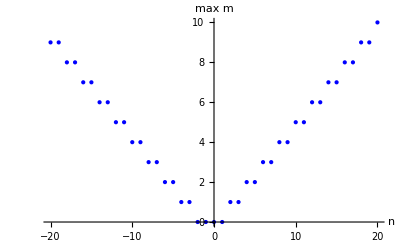

```mathematica
Mmax=50;ListPlot[Table[{n,Max[FindTruncationRank1[n,Mmax]]},{n,-20,20}],PlotStyle->{Blue,PointSize[Medium]},AxesLabel->{"n","max m"},PlotRange->All]
```

Computing the JK residue:

### n=0

#### n=0, m=0

```mathematica
n=0;m=0;
Z1loop
```

(Eta^2 Theta1[1/x^2] Theta1[x^2] Theta1[1/y^2])/(4 π Theta1[y] Theta1[y/x^2] Theta1[x^2 y])

```mathematica
(*positive poles*)
poles={(√y)^-1,√q(√y)^-1,-(√y)^-1,-√q(√y)^-1};
```

```mathematica
Res=0;
Do[
Ztemp=Evaluate[((Z1loop/.{x->x*poles[[i]]})/.replacementRule)];

Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule/.Theta1[1/x]->-Theta1[x];

Res= Res+SimpleResidue[Ztemp,x];
,{i,1,Length[poles]}]
```

```mathematica
Res
```

(Theta1[1/y^2] Theta1[1/y])/(4 Eta π^2 Theta1[y^2])

```mathematica
Res/.{Theta1[1/y^2]->-Theta1[y^2],Theta1[1/y]->-Theta1[y]}
```

Theta1[y]/(4 Eta π^2)

#### n=1, m=1

```mathematica
n=0;m=1;
Z1loop
```

(Eta^2 Theta1[1/x^2] Theta1[x^2] Theta1[1/y^2] Theta1[1/(x^2 y)]^2 Theta1[y/x^2])/(4 π Theta1[x^2/y]^2 Theta1[y] Theta1[x^2 y]^3)

We don’t have negative poles, so the JK residue is zero. As a consistency check, we choose the positive poles:

```mathematica
(*positive poles*)
poles={√y,√q √y,-√y,-√q √y,(√y)^-1,√q(√y)^-1,-(√y)^-1,-√q(√y)^-1};
```

```mathematica
Nmax=1;
Res=0;
Do[
Ztemp=Evaluate[((Z1loop/.{x->x*poles[[i]]})/.replacementRule)];

Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule;


Res= Res+ContourInt[Ztemp//qForm//qExpand,x];
,{i,1,Length[poles]}]
Res//Simplify
```

0

#### n=1, m=0

```mathematica
n=1;m=.;
Z1loop
```

1/(4 Eta^2 π Theta1[y]^2)Theta1[1/x^2] Theta1[x^2] Theta1[1/y^2]^3 Theta1[1/y] ((ⅈ Eta)/Theta1[1/(x^2 y)])^(-1-2 m) ((ⅈ Eta)/Theta1[x^2/y])^(-1+2 m) ((ⅈ Eta)/Theta1[y/x^2])^(2-2 m) ((ⅈ Eta)/Theta1[x^2 y])^(2+2 m)

```mathematica
(*positive poles*)
poles={(√y)^-1,√q(√y)^-1,-(√y)^-1,-√q(√y)^-1};
```

```mathematica
Res=0;
Do[
Ztemp=Evaluate[((Z1loop/.{x->x*poles[[i]]})/.replacementRule)];

Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule/.Theta1[1/x]->-Theta1[x];

Res= Res+SimpleResidue[Ztemp,x];
,{i,1,Length[poles]}]
```

```mathematica
Res
```

(Theta1[1/y^2] Theta1[1/y])/(4 Eta π^2 Theta1[y^2])

```mathematica
Res/.{Theta1[1/y^2]->-Theta1[y^2],Theta1[1/y]->-Theta1[y]}
```

Theta1[y]/(4 Eta π^2)

### n=-1

#### n=-1, m=0

```mathematica
n=-1;m=0;
Z1loop
```

-(Eta^4 Theta1[1/x^2] Theta1[x^2])/(4 π Theta1[1/y^2] Theta1[1/y] Theta1[1/(x^2 y)] Theta1[x^2/y])

```mathematica
(*positive poles*)
poles={√y,√q √y,-√y,-√q √y};
```

```mathematica
Res=0;
Do[
Ztemp=Evaluate[((Z1loop/.{x->x*poles[[i]]})/.replacementRule)];


Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule/.Theta1[1/x]->-Theta1[x];

Res= Res+SimpleResidue[Ztemp,x];
,{i,1,Length[poles]}]
```

```mathematica
Res
```

-(Eta Theta1[y])/(4 π^2 Theta1[1/y^2]^2)

```mathematica
Res/.{Theta1[1/y^2]->-Theta1[y^2],Theta1[1/y]->-Theta1[y]}
```

-(Eta Theta1[y])/(4 π^2 Theta1[y^2]^2)

#### n=-1, m=1

```mathematica
n=-1;m=1;
Z1loop
```

-(Eta^4 Theta1[1/x^2] Theta1[x^2] Theta1[1/(x^2 y)] Theta1[y/x^2]^2)/(4 π Theta1[1/y^2] Theta1[1/y] Theta1[x^2/y]^3 Theta1[x^2 y]^2)

We see only positive poles. Taking only negative poles in the JK residue, we get 0 as expected.

### n=-2

#### n=-2, m=0

```mathematica
n=-2;m=0;
Z1loop
```

(Eta^6 Theta1[1/x^2] Theta1[x^2] Theta1[y] Theta1[y/x^2] Theta1[x^2 y])/(4 π Theta1[1/y^2]^3 Theta1[1/y]^2 Theta1[1/(x^2 y)]^2 Theta1[x^2/y]^2)

```mathematica
(*positive poles*)
poles={√y,√q √y,-√y,-√q √y};
```

```mathematica
Res=0;
Do[
Ztemp=Evaluate[((Z1loop/.{x->x*poles[[i]]})/.replacementRule)];

Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule/.Theta1[1/x]->-Theta1[x];
Print[Ztemp];
Res= Res+SimpleResidue[Ztemp,x];
,{i,1,Length[poles]}]
```

-(Eta^6 Theta1[1/(x y)] Theta1[y] Theta1[x y] Theta1[x y^2])/(8 π Theta1[x] Theta1[1/y^2]^3 Theta1[1/(x y^2)]^2 Theta1[1/y]^2)

-(Eta^6 Theta1[1/(x y)] Theta1[y] Theta1[x y] Theta1[x y^2])/(8 π Theta1[x] Theta1[1/y^2]^3 Theta1[1/(x y^2)]^2 Theta1[1/y]^2)

-(Eta^6 Theta1[1/(x y)] Theta1[y] Theta1[x y] Theta1[x y^2])/(8 π Theta1[x] Theta1[1/y^2]^3 Theta1[1/(x y^2)]^2 Theta1[1/y]^2)

«1 more identical outputs»

```mathematica
Res
```

-(Eta^3 Theta1[y]^2 Theta1[y^2])/(4 π^2 Theta1[1/y^2]^5 Theta1[1/y])

```mathematica
Res/.{Theta1[1/y^2]->-Theta1[y^2],Theta1[1/y]->-Theta1[y]}
```

-(Eta^3 Theta1[y])/(4 π^2 Theta1[y^2]^4)

#### n=-1, m=1

```mathematica
n=-1;m=1;
Z1loop
```

-(Eta^4 Theta1[1/x^2] Theta1[x^2] Theta1[1/(x^2 y)] Theta1[y/x^2]^2)/(4 π Theta1[1/y^2] Theta1[1/y] Theta1[x^2/y]^3 Theta1[x^2 y]^2)

We see only positive poles. Taking only negative poles in the JK residue, we get 0 as expected.

### n=-3

#### n=-3, m=0

```mathematica
n=-3;m=0;
Z1loop
```

-(Eta^8 Theta1[1/x^2] Theta1[x^2] Theta1[y]^2 Theta1[y/x^2]^2 Theta1[x^2 y]^2)/(4 π Theta1[1/y^2]^5 Theta1[1/y]^3 Theta1[1/(x^2 y)]^3 Theta1[x^2/y]^3)

```mathematica
(*positive poles*)
poles={√y,√q √y,-√y,-√q √y};
```

```mathematica
Res=0;
Do[
Ztemp=Evaluate[((Z1loop/.{x->x*poles[[i]]})/.replacementRule)];

Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule/.Theta1[1/x]->-Theta1[x];
Print[Ztemp];
Res= Res+SimpleResidue[Ztemp,x];
,{i,1,Length[poles]}]
```

-(Eta^8 Theta1[1/(x y)] Theta1[y]^2 Theta1[x y] Theta1[x y^2]^2)/(8 π Theta1[x] Theta1[1/y^2]^5 Theta1[1/(x y^2)]^3 Theta1[1/y]^3)

-(Eta^8 Theta1[1/(x y)] Theta1[y]^2 Theta1[x y] Theta1[x y^2]^2)/(8 π Theta1[x] Theta1[1/y^2]^5 Theta1[1/(x y^2)]^3 Theta1[1/y]^3)

-(Eta^8 Theta1[1/(x y)] Theta1[y]^2 Theta1[x y] Theta1[x y^2]^2)/(8 π Theta1[x] Theta1[1/y^2]^5 Theta1[1/(x y^2)]^3 Theta1[1/y]^3)

«1 more identical outputs»

```mathematica
Res
```

-(Eta^5 Theta1[y]^3 Theta1[y^2]^2)/(4 π^2 Theta1[1/y^2]^8 Theta1[1/y]^2)

```mathematica
Res/.{Theta1[1/y^2]->-Theta1[y^2],Theta1[1/y]->-Theta1[y]}
```

-(Eta^5 Theta1[y])/(4 π^2 Theta1[y^2]^6)

#### n=-3, m=1

```mathematica
n=-3;m=1;
Z1loop
```

-(Eta^8 Theta1[1/x^2] Theta1[x^2] Theta1[y]^2 Theta1[y/x^2]^4)/(4 π Theta1[1/y^2]^5 Theta1[1/y]^3 Theta1[1/(x^2 y)] Theta1[x^2/y]^5)

```mathematica
(*positive poles*)
poles={√y,√q √y,-√y,-√q √y};
```

```mathematica
Res=0;
Do[
Ztemp=Evaluate[((Z1loop/.{x->x*poles[[i]]})/.replacementRule)];

Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule/.Theta1[1/x]->-Theta1[x];
Print[Ztemp];
Res= Res+SimpleResidue[Ztemp,x];
,{i,1,Length[poles]}]
```

-(Eta^8 Theta1[1/(x y)] Theta1[y]^2 Theta1[x y])/(8 π Theta1[x] Theta1[1/y^2]^5 Theta1[1/(x y^2)] Theta1[1/y]^3)

-(Eta^8 Theta1[1/(x y)] Theta1[y]^2 Theta1[x y])/(8 π Theta1[x] Theta1[1/y^2]^5 Theta1[1/(x y^2)] Theta1[1/y]^3)

-(Eta^8 Theta1[1/(x y)] Theta1[y]^2 Theta1[x y])/(8 π Theta1[x] Theta1[1/y^2]^5 Theta1[1/(x y^2)] Theta1[1/y]^3)

«1 more identical outputs»

```mathematica
Res
```

-(Eta^5 Theta1[y]^3)/(4 π^2 Theta1[1/y^2]^6 Theta1[1/y]^2)

```mathematica
Res/.{Theta1[1/y^2]->-Theta1[y^2],Theta1[1/y]->-Theta1[y]}
```

-(Eta^5 Theta1[y])/(4 π^2 Theta1[y^2]^6)

#### n=-3, m=-1

```mathematica
n=-3;m=-1;
Z1loop
```

-(Eta^8 Theta1[1/x^2] Theta1[x^2] Theta1[y]^2 Theta1[x^2 y]^4)/(4 π Theta1[1/y^2]^5 Theta1[1/y]^3 Theta1[1/(x^2 y)]^5 Theta1[x^2/y])

```mathematica
(*positive poles*)
poles={√y,√q √y,-√y,-√q √y};
```

```mathematica
Res=0;
Do[
Ztemp=Evaluate[((Z1loop/.{x->x*poles[[i]]})/.replacementRule)];

Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule/.Theta1[1/x]->-Theta1[x];
Print[Ztemp];
Res= Res+SimpleResidue[Ztemp,x];
,{i,1,Length[poles]}]
```

-(Eta^8 Theta1[1/(x y)] Theta1[y]^2 Theta1[x y] Theta1[x y^2]^4)/(8 π Theta1[x] Theta1[1/y^2]^5 Theta1[1/(x y^2)]^5 Theta1[1/y]^3)

-(Eta^8 Theta1[1/(x y)] Theta1[y]^2 Theta1[x y] Theta1[x y^2]^4)/(8 π Theta1[x] Theta1[1/y^2]^5 Theta1[1/(x y^2)]^5 Theta1[1/y]^3)

-(Eta^8 Theta1[1/(x y)] Theta1[y]^2 Theta1[x y] Theta1[x y^2]^4)/(8 π Theta1[x] Theta1[1/y^2]^5 Theta1[1/(x y^2)]^5 Theta1[1/y]^3)

«1 more identical outputs»

```mathematica
Res
```

-(Eta^5 Theta1[y]^3 Theta1[y^2]^4)/(4 π^2 Theta1[1/y^2]^10 Theta1[1/y]^2)

```mathematica
Res/.{Theta1[1/y^2]->-Theta1[y^2],Theta1[1/y]->-Theta1[y]}
```

-(Eta^5 Theta1[y])/(4 π^2 Theta1[y^2]^6)

#### Final result:

```mathematica
-(Eta^5 Theta1[y])/(4 π^2 Theta1[y^2]^6)-(Eta^5 Theta1[y])/(4 π^2 Theta1[y^2]^6)-(Eta^5 Theta1[y])/(4 π^2 Theta1[y^2]^6)
```

-(3 Eta^5 Theta1[y])/(4 π^2 Theta1[y^2]^6)

### n<0

For the general case, n<0, the truncation is: |m|<1/2|n|

#### n=-3

```mathematica
n=.;m=.;
Z1loop
```

-1/(4 π)Theta1[1/x^2] Theta1[x^2] ((ⅈ Eta)/Theta1[1/y^2])^(-1-2 n) ((ⅈ Eta)/Theta1[1/y])^-n ((ⅈ Eta)/Theta1[1/(x^2 y)])^(-2 m-n) ((ⅈ Eta)/Theta1[x^2/y])^(2 m-n) ((ⅈ Eta)/Theta1[y])^(1+n) ((ⅈ Eta)/Theta1[y/x^2])^(1-2 m+n) ((ⅈ Eta)/Theta1[x^2 y])^(1+2 m+n)

```mathematica
(*positive poles*)
poles={√y,√q √y,-√y,-√q √y};
```

```mathematica
Res=0;
Do[
Ztemp=Evaluate[((Z1loop/.{x->x*poles[[i]]})/.replacementRule)];

Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule/.Theta1[1/x]->-Theta1[x];
Ztemp=Simplify[Ztemp,Assumptions->m∈Integers&&n∈Integers];
Print[Ztemp];
Res= Res+SimpleResidue[Ztemp,x];
,{i,1,Length[poles]}]
```

-(Eta^(2-2 n) Theta1[1/y^2]^(1+2 n) Theta1[1/(x y^2)]^(2 m+n) Theta1[1/y]^n Theta1[1/(x y)] Theta1[y]^(-1-n) Theta1[x y] Theta1[x y^2]^(-1-2 m-n))/(8 π Theta1[x])

-(Eta^(2-2 n) Theta1[1/y^2]^(1+2 n) Theta1[1/(x y^2)]^(2 m+n) Theta1[1/y]^n Theta1[1/(x y)] Theta1[y]^(-1-n) Theta1[x y] Theta1[x y^2]^(-1-2 m-n))/(8 π Theta1[x])

-(Eta^(2-2 n) Theta1[1/y^2]^(1+2 n) Theta1[1/(x y^2)]^(2 m+n) Theta1[1/y]^n Theta1[1/(x y)] Theta1[y]^(-1-n) Theta1[x y] Theta1[x y^2]^(-1-2 m-n))/(8 π Theta1[x])

«1 more identical outputs»

```mathematica
Res
```

-(Eta^(-1-2 n) Theta1[1/y^2]^(1+2 m+3 n) Theta1[1/y]^(1+n) Theta1[y]^-n Theta1[y^2]^(-1-2 m-n))/(4 π^2)

```mathematica
Res=Res/.{Theta1[1/y^2]->-Theta1[y^2],Theta1[1/y]->-Theta1[y]}
```

-(Eta^(-1-2 n) (-Theta1[y])^(1+n) Theta1[y]^-n (-Theta1[y^2])^(1+2 m+3 n) Theta1[y^2]^(-1-2 m-n))/(4 π^2)

```mathematica
Res=Simplify[Res,Assumptions->m∈Integers&&n∈Integers]
```

-(Eta^(-1-2 n) Theta1[y] Theta1[y^2]^(2 n))/(4 π^2)

The final result will be Res times the size of the set: {m∈Ζ:|m|<1/2|n|}

### n=1

#### n=1, m=0

```mathematica
n=1;m=0;
Z1loop
```

-(Theta1[1/x^2] Theta1[x^2] Theta1[1/y^2]^3 Theta1[1/y] Theta1[1/(x^2 y)] Theta1[x^2/y])/(4 π Theta1[y]^2 Theta1[y/x^2]^2 Theta1[x^2 y]^2)

```mathematica
(*positive poles*)
poles={(√y)^-1,√q(√y)^-1,-(√y)^-1,-√q(√y)^-1};
```

```mathematica
Res=0;
Do[
Ztemp=Evaluate[((Z1loop/.{x->x*poles[[i]]})/.replacementRule)];

Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule/.Theta1[1/x]->-Theta1[x];
Print[Ztemp];

Res= Res+SimpleResidue[Ztemp,x];
,{i,1,Length[poles]}]
```

(Theta1[1/y^2]^3 Theta1[x/y^2] Theta1[1/y] Theta1[x/y] Theta1[y/x])/(8 π Theta1[x] Theta1[y]^2 Theta1[y^2/x]^2)

(Theta1[1/y^2]^3 Theta1[x/y^2] Theta1[1/y] Theta1[x/y] Theta1[y/x])/(8 π Theta1[x] Theta1[y]^2 Theta1[y^2/x]^2)

(Theta1[1/y^2]^3 Theta1[x/y^2] Theta1[1/y] Theta1[x/y] Theta1[y/x])/(8 π Theta1[x] Theta1[y]^2 Theta1[y^2/x]^2)

«1 more identical outputs»

```mathematica
Res
```

(Theta1[1/y^2]^4 Theta1[1/y]^2)/(4 Eta^3 π^2 Theta1[y] Theta1[y^2]^2)

```mathematica
Res/.{Theta1[1/y^2]->-Theta1[y^2],Theta1[1/y]->-Theta1[y]}
```

(Theta1[y] Theta1[y^2]^2)/(4 Eta^3 π^2)

### n>0

For the general case, n<0, the truncation is: |m|<=1/2|n| (note the less or equal here)

#### n>0

```mathematica
n=.;m=.;
Z1loop
```

-1/(4 π)Theta1[1/x^2] Theta1[x^2] ((ⅈ Eta)/Theta1[1/y^2])^(-1-2 n) ((ⅈ Eta)/Theta1[1/y])^-n ((ⅈ Eta)/Theta1[1/(x^2 y)])^(-2 m-n) ((ⅈ Eta)/Theta1[x^2/y])^(2 m-n) ((ⅈ Eta)/Theta1[y])^(1+n) ((ⅈ Eta)/Theta1[y/x^2])^(1-2 m+n) ((ⅈ Eta)/Theta1[x^2 y])^(1+2 m+n)

```mathematica
(*positive poles*)
poles={(√y)^-1,√q(√y)^-1,-(√y)^-1,-√q(√y)^-1};
```

```mathematica
Res=0;
Do[
Ztemp=Evaluate[((Z1loop/.{x->x*poles[[i]]})/.replacementRule)];

Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule/.Theta1[1/x]->-Theta1[x];
Ztemp=Simplify[Ztemp,Assumptions->m∈Integers&&n∈Integers];
Print[Ztemp];
Res= Res+SimpleResidue[Ztemp,x];
,{i,1,Length[poles]}]
```

1/(8 π Theta1[x])Eta^(2-2 n) Theta1[1/y^2]^(1+2 n) Theta1[x/y^2]^(-2 m+n) Theta1[1/y]^n Theta1[x/y] Theta1[y]^(-1-n) Theta1[y/x] Theta1[y^2/x]^(-1+2 m-n)

1/(8 π Theta1[x])Eta^(2-2 n) Theta1[1/y^2]^(1+2 n) Theta1[x/y^2]^(-2 m+n) Theta1[1/y]^n Theta1[x/y] Theta1[y]^(-1-n) Theta1[y/x] Theta1[y^2/x]^(-1+2 m-n)

1/(8 π Theta1[x])Eta^(2-2 n) Theta1[1/y^2]^(1+2 n) Theta1[x/y^2]^(-2 m+n) Theta1[1/y]^n Theta1[x/y] Theta1[y]^(-1-n) Theta1[y/x] Theta1[y^2/x]^(-1+2 m-n)

«1 more identical outputs»

```mathematica
Res
```

(Eta^(-1-2 n) Theta1[1/y^2]^(1-2 m+3 n) Theta1[1/y]^(1+n) Theta1[y]^-n Theta1[y^2]^(-1+2 m-n))/(4 π^2)

```mathematica
Res=Res/.{Theta1[1/y^2]->-Theta1[y^2],Theta1[1/y]->-Theta1[y]}
```

(Eta^(-1-2 n) (-Theta1[y])^(1+n) Theta1[y]^-n (-Theta1[y^2])^(1-2 m+3 n) Theta1[y^2]^(-1+2 m-n))/(4 π^2)

```mathematica
Res=Simplify[Res,Assumptions->m∈Integers&&n∈Integers]
```

(Eta^(-1-2 n) Theta1[y] Theta1[y^2]^(2 n))/(4 π^2)

The final result will be Res times the size of the set: {m∈Ζ:|m|<=1/2|n|}

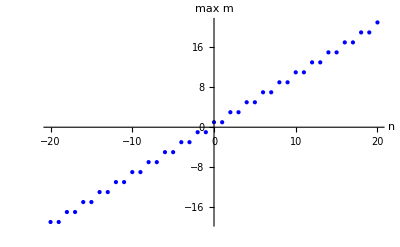

```mathematica
Mmax=50;ListPlot[Table[{n,2*Floor[n/2]+1},{n,-20,20}],PlotStyle->{Blue,PointSize[Medium]},AxesLabel->{"n","max m"},PlotRange->All]
```

```mathematica
1/4-1/12
```

1/6

## A_1 compactification with flux n=2 - qExpansion

### Dependence on m

```mathematica
gList=
```

{2,0,2}

```mathematica
Product[Product[gList[[i]]*gList[[j]],{i,gList}],{j,gList}]
```

16

```mathematica
f1[g_]:=(1/Theta1[Subscript[x, 1]^g*y^-1,q])^(g*Subscript[m, 1]-n);
f2[g_]:=(1/Theta1[Subscript[x, 2]^g*y^-1,q])^(g*Subscript[m, 2]-n);
f3[g1_,g2_]:=(1/Theta1[Subscript[x, 1]^g1*Subscript[x, 2]^g2*y^-1,q])^(2(g1*Subscript[m, 1]+g2*Subscript[m, 2]+n+1))
Z1loop=Product[f1[g]*f2[g],{g,{-2,0,2}}]*Product[f3[g1,g2],{g1,{-1,1}},{g2,{-1,1}}]//qExpand
```

q^(-4-3 n+1/2 (n-2 m_1)+1/2 (n+2 m_1)+1/2 (n-2 m_2)+1/2 (n+2 m_2)) (ⅈ/((1-1/q) (1-1/y) (1-1/(q y)) (1-q/y)))^(-2 n) y^(-n/4+1/8 (-n-2 m_1)+1/8 (-n+2 m_1)+1/8 (-n-2 m_2)+1/4 (1+n-m_1-m_2)+1/4 (1+n+m_1-m_2)+1/4 (1+n-m_1+m_2)+1/4 (1+n+m_1+m_2)+1/8 (-n+2 m_2)) (ⅈ/((1-1/q) (1-1/(y x_1^2)) (1-1/(q y x_1^2)) (1-q/(y x_1^2)) (1/x_1^2)^(1/8)))^(-n-2 m_1) (ⅈ/((1-1/q) (x_1^2)^(1/8) (1-x_1^2/y) (1-x_1^2/(q y)) (1-(q x_1^2)/y)))^(-n+2 m_1) (ⅈ/((1-1/q) (1-1/(y x_2^2)) (1-1/(q y x_2^2)) (1-q/(y x_2^2)) (1/x_2^2)^(1/8)))^(-n-2 m_2) (ⅈ/((1-1/q) (1-1/(y x_1 x_2)) (1-1/(q y x_1 x_2)) (1-q/(y x_1 x_2)) (1/(x_1 x_2))^(1/8)))^(2 (1+n-m_1-m_2)) (ⅈ/((1-1/q) (1-x_1/(y x_2)) (1-x_1/(q y x_2)) (1-(q x_1)/(y x_2)) (x_1/x_2)^(1/8)))^(2 (1+n+m_1-m_2)) (ⅈ/((1-1/q) (x_2/x_1)^(1/8) (1-x_2/(y x_1)) (1-x_2/(q y x_1)) (1-(q x_2)/(y x_1))))^(2 (1+n-m_1+m_2)) (ⅈ/((1-1/q) (x_1 x_2)^(1/8) (1-(x_1 x_2)/y) (1-(x_1 x_2)/(q y)) (1-(q x_1 x_2)/y)))^(2 (1+n+m_1+m_2)) (ⅈ/((1-1/q) (x_2^2)^(1/8) (1-x_2^2/y) (1-x_2^2/(q y)) (1-(q x_2^2)/y)))^(-n+2 m_2)

```mathematica
Ztest=ReplaceAll[Z1loop,
{Subscript[x, 1]->3,
Subscript[x, 2]->4,
y->1/2,
q->1/5}]//Simplify
```

2^(-5-(5 n)/4-34 m_2) 5^(8-n+4 m_1) 9^(6+9 n-13 m_1-2 m_2) 17^(-2-n-4 m_1-2 m_2) 43^(n+2 m_1) 49^(-3-2 n) 89^(n-2 m_1) 169^(-1-2 m_1+2 m_2) 841^(-1-n+m_1+m_2) 1369^(-1-n+m_1-m_2) 1643^(n-2 m_2) 190969^(-1-n-m_1-m_2) ⅇ^(-2 ⅈ π (n-m_1-2 m_2))

```mathematica
N[Ztest]//Simplify
```

5.13488×10^-12 ⅇ^((-43.3771+6.28319 ⅈ) m_1-(50.8238-12.5664 ⅈ) m_2)

Conclusion : there is a dependence on m

### Understanding the truncation for the case n = 2

```mathematica
Subscript[m, 1]=200;
Subscript[m, 2]=100;
mLength = √(Subscript[m, 1]^2+Subscript[m, 2]^2);
VectorList={{2,0},{0,2},{-2,0},{0,-2},{-1,1},{1,-1},{1,1},{-1,-1}};
eta={-Subscript[m, 1]/mLength,-Subscript[m, 2]/mLength};
```

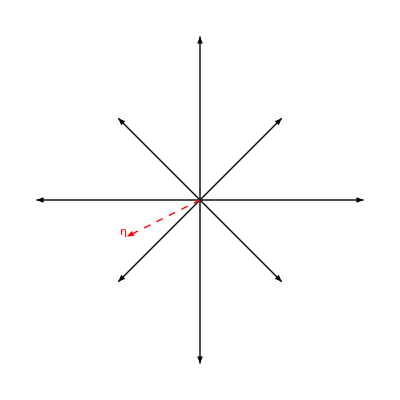

```mathematica
DrawVectors[{{2,0},{0,2},{-2,0},{0,-2},{-1,1},{1,-1},{1,1},{-1,-1}},eta]
```

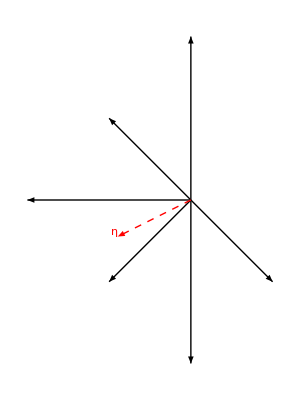

```mathematica
DrawVectors[{{0,2},{-2,0},{0,-2},{-1,1},{1,-1},{-1,-1}},eta]
```

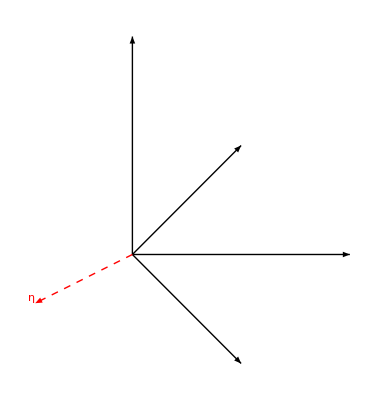

```mathematica
DrawVectors[{{0,2},{2,0},{1,1},{1,-1}},eta]
```

### Plot the region of (m_1,m_2) for which the residue contributes

```mathematica
n=0;
range=10;
regionCond2[{m1_,m2_}]:=(2m1-n>0&&2m2-n>0&&m1<=m2&&m2<0);  
regionCondSing2[{m1_,m2_}]:=m1>1/2 n&&m1<0&&m2==0;
regionCond4[{m1_,m2_}]:=(m1-m2+n+1>0)&&(m1+m2+n+1>0)&&m1<=m2&&m2<0;
regionCondSing4[{m1_,m2_}]:=(m1>-n-1&&m1<0&&m2==0);
regionCond5[{m1_,m2_}]:=(m1-m2+n+1>0)&&(2m2-n>0)&&m1<=m2&&m2<0;

integerPoints2=Select[Flatten[Table[{m1,m2},{m1,-range,0},{m2,-range,0}],1],regionCond2]
integerPointsSing2=Select[Flatten[Table[{m1,m2},{m1,-range,0},{m2,-range,0}],1],regionCondSing2]
integerPoints4=Select[Flatten[Table[{m1,m2},{m1,-range,0},{m2,-range,0}],1],regionCond4]
integerPointsSing4=Select[Flatten[Table[{m1,m2},{m1,-range,0},{m2,-range,0}],1],regionCondSing4]
integerPoints5=Select[Flatten[Table[{m1,m2},{m1,-range,0},{m2,-range,0}],1],regionCond5]

data1=integerPoints2;
data2=integerPoints4;
data3=integerPointsSing2;
data4=integerPointsSing4;
data5=integerPoints5;

datasets={};
If[data1=!={},AppendTo[datasets,data1]];
If[data2=!={},AppendTo[datasets,data2]];
If[data3=!={},AppendTo[datasets,data3]];
If[data4=!={},AppendTo[datasets,data4]];
If[data5=!={},AppendTo[datasets,data5]];

ListPlot[datasets,PlotStyle->{Red,Blue,Green,Yellow,Purple},PlotMarkers->{Style["●",20],Style["■",20],Style["■",20],Style["■",20],Style["■",20]}]
```

{}

{}

{}

«2 more identical outputs»

-Graphics-

### Finding the residue for n = 1 with expansion in q

#### Finding the residue for n = 1, (m_1,m_2)=(-1,0):

For this case, the JK residue is at a single point (u_1,u_2)=(-v,0)

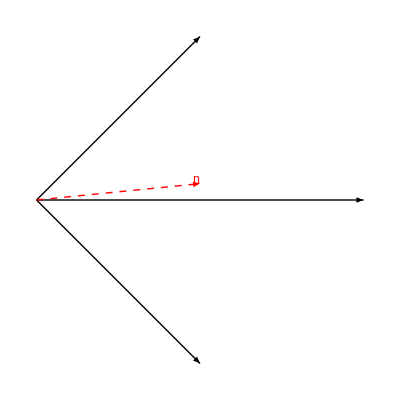

```mathematica
ϵ=0.1;
DrawVectors[{{1,-1},{1,1},{1,-1}+{1,1}},{1,ϵ}]
```

The flags are:
F_1=[Q_(1,-1),R^2], κ^F_1={Q_(1,-1), Q_(1,-1)+Q_(1,1)}
F_2=[Q_(1,1),R^2], κ^F_2={Q_(1,1), Q_(1,-1)+Q_(1,1)}
The relevant flag is F_2. The sign determinant is: ν(F_2)=-1. The residue is:
res_F_2 ω=Res_(u1,-1=0)Res_(u11=0)ω

We want to make a variable change in Z1loop :

```mathematica
Inverse[({{1, 1}, {1, -1}})]//MatrixForm
```

(1/2 | 1/2
1/2 | -1/2)

```mathematica
variableChange={Subscript[x, 1]->Subscript[w, 1]^(1/2)*Subscript[w, 2]^(1/2),Subscript[x, 2]->Subscript[w, 1]^(1/2)*Subscript[w, 2]^(-1/2)};
Z1looptilde=-1/2 ReplaceAll[Z1loop/.Subscript[x, 1]->Subscript[x, 1]*y^-1,variableChange]//Simplify
```

-(((-1+y)^8 (1+y)^6 (w_1-w_2)^2 (y w_1-w_2) (-w_1+y w_2) (y^2-w_1 w_2)^2 (y^3-w_1 w_2)^3)/(8 y^10 (y^2-w_1)^2 (-1+w_1)^6 (y^2-w_2)^2 (-1+w_2)^6 (y-w_1 w_2)))

```mathematica
Zresult=ContourInt[Z1looptilde,Subscript[w, 1],Subscript[w, 2]]
```

```mathematica
Zresult=Zresult // Simplify
```

1/(4 y^6 (1+y)^4)(-1+y)^2 (1+15 y+122 y^2+559 y^3+1659 y^4+3470 y^5+5333 y^6+6141 y^7+5333 y^8+3470 y^9+1659 y^10+559 y^11+122 y^12+15 y^13+y^14)

#### Finding the residue for n = 1, (m_1,m_2)=(0,-1):

For this case, the JK residue is at a single point (u_1,u_2)=(0,-v)

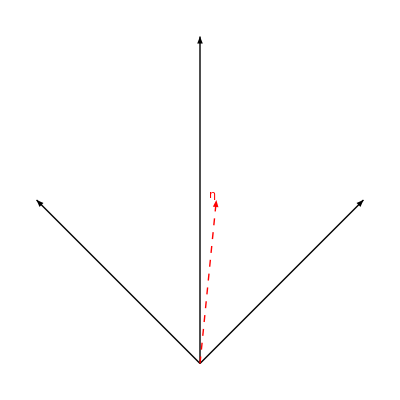

```mathematica
ϵ=0.1;
DrawVectors[{{1,1},{-1,1},{1,1}+{-1,1}},{ϵ,1}]
```

The flags are:
F_1=[Q_(1,1),R^2], κ^F_1={Q_(1,1), Q_(1,1)+Q_(-1,1)}
F_2=[Q_(-1,1),R^2], κ^F_2={Q_(-1,1), Q_(1,1)+Q_(-1,1)}
The relevant flag is F_1. The sign determinant is: ν(F_2)=+1. The residue is:
res_F_2 ω=Res_(u-1,1=0)Res_(u1+u2=0)ω

We want to make a variable change in Z1loop :

```mathematica
Inverse[({{1, 1}, {-1, 1}})]//MatrixForm
```

(1/2 | -1/2
1/2 | 1/2)

```mathematica
variableChange={Subscript[x, 1]->Subscript[w, 1]^(1/2)*Subscript[w, 2]^(-1/2),Subscript[x, 2]->Subscript[w, 1]^(1/2)*Subscript[w, 2]^(1/2)};
Z1looptilde=-1/2 ReplaceAll[Z1loop/.Subscript[x, 2]->Subscript[x, 2]*y^-1,variableChange]//Simplify
```

-(((-1+y)^8 (1+y)^6 (w_1-w_2)^2 (y w_1-w_2) (-w_1+y w_2) (y^2-w_1 w_2)^2 (y^3-w_1 w_2)^3)/(8 y^10 (y^2-w_1)^2 (-1+w_1)^6 (y^2-w_2)^2 (-1+w_2)^6 (y-w_1 w_2)))

```mathematica
Zresult=ContourInt[Z1looptilde,Subscript[w, 1],Subscript[w, 2]]
```

```mathematica
Zresult=Zresult//Simplify
```

1/(4 y^6 (1+y)^4)(-1+y)^2 (1+15 y+122 y^2+559 y^3+1659 y^4+3470 y^5+5333 y^6+6141 y^7+5333 y^8+3470 y^9+1659 y^10+559 y^11+122 y^12+15 y^13+y^14)

#### Finding the residue for n = 1, (m_1,m_2)=(0,0):

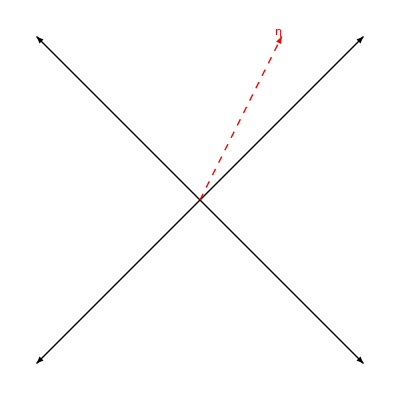

```mathematica
DrawVectors[{{-1,1},{1,-1},{1,1},{-1,-1}},{1/2,1}]
```

```mathematica
variableChange={Subscript[x, 1]->Subscript[w, 1]^(1/2)*Subscript[w, 2]^(-1/2),Subscript[x, 2]->Subscript[w, 1]^(1/2)*Subscript[w, 2]^(1/2)};
Z1looptilde=-1/2 ReplaceAll[Z1loop/.Subscript[x, 2]->Subscript[x, 2]*y^-1,variableChange]//Simplify
```

-(((-1+y)^8 (1+y)^6 (w_1-w_2)^2 (y w_1-w_2) (-w_1+y w_2) (y-w_1 w_2) (y^2-w_1 w_2)^2 (y^3-w_1 w_2))/(8 y^4 (y^2-w_1)^4 (-1+w_1)^4 (y^2-w_2)^4 (-1+w_2)^4))

```mathematica
Zresult=ContourInt[Z1looptilde,Subscript[w, 1],Subscript[w, 2]]
```

-1/(4 y^3 (1+y)^4)(-1+y)^2 (1+4 y+14 y^2+32 y^3+38 y^4+32 y^5+14 y^6+4 y^7+y^8)

#### Final result for the case n = 1

```mathematica
Zm11=1/(4 y^6 (1+y)^4)(-1+y)^2 (1+15 y+122 y^2+559 y^3+1659 y^4+3470 y^5+5333 y^6+6141 y^7+5333 y^8+3470 y^9+1659 y^10+559 y^11+122 y^12+15 y^13+y^14);
Zm00=-1/(4 y^3 (1+y)^4)(-1+y)^2 (1+4 y+14 y^2+32 y^3+38 y^4+32 y^5+14 y^6+4 y^7+y^8);
Zfinal=4*Zm11+Zm00//Simplify
```

1/(4 y^6)(-1+y)^2 (4+44 y+288 y^2+803 y^3+1512 y^4+1804 y^5+1512 y^6+803 y^7+288 y^8+44 y^9+4 y^10)

### Attempt to make the algorithm more generic

#### Helper Functions

We want to compute the residue for the generic case (m1, m2).
(1) Input: 
	- hyperplanes (R,Q,K)
	- η
(2) Find the relevant singular points.
(3) For each point,  find the relevant flags.
(4) Compute the residue for the corresponding flag with correct sign.
(5) Sum the residues.

```mathematica
(*Draw a list of vectors and eta*)
DrawVectors[VectorList_,eta_]:=
Graphics[
{
(*Plot charge covectors*)
Table[Arrow[{{0,0},{VectorList[[j]][[1]],VectorList[[j]][[2]]}}]
,{j,1,Dimensions[VectorList][[1]]}],

(*Plot eta*)
Red,Dashed,Arrow[{{0,0},{eta[[1]],eta[[2]]}}],Text["η",{eta[[1]],eta[[2]]},{1,-1}]
}];

(*Check if eta is in the cone ={vec1,vec2}*)
IsInCone[cone_,eta_]:=Module[{proj},
proj =Inverse[Transpose[cone]].eta;
AllTrue[proj,Positive]
];

(*Check if two vectors are colinear*)
ColinearQ[u_,v_]:=VectorAngle[u,v]==0||VectorAngle[u,v]==Pi;

(*Returns singular points and singular planes*)
SingularPoints[Qcovectors_,SymCovectors_]:=Module[{ptsList},
ptsList={};
Do[
If[i<j,
If[!ColinearQ[Qcovectors[[i]],Qcovectors[[j]]],

point=LinearSolve[{Qcovectors[[i]],Qcovectors[[j]]},-{SymCovectors[[i]],SymCovectors[[j]]}];
AppendTo[ptsList,{point,{i,j}}]
]
]

,{i,1,Length[Qcovectors]}
,{j,1,Length[Qcovectors]}
];

KeyValueMap[{#1,Union@@#2}&,GroupBy[ptsList,First->Last]]

]

(*Returns relevant singular points and singular planes wrt eta*)
RelevantSingularPoints[Qcovectors_,SymCovectors_,eta_]:=Module[{pointsList,singPts,isRelevant},
pointsList={};
singPts=SingularPoints[Qcovectors,SymCovectors];

Do[
(*Check if the point is relevant wrt eta*)
isRelevant=False;
Do[
If[j<k,
If[IsInCone[{Qcovectors[[j]],Qcovectors[[k]]},eta],
isRelevant=True]
]
,{j,singPts[[i]][[2]]},{k,singPts[[i]][[2]]}];

(*If relevant, add it to the list*)
If[isRelevant,
AppendTo[pointsList,singPts[[i]]]
];

,{i,1,Length[singPts]}];

pointsList
]

(*A function that draw lines as a function of Qcovectors and symmetry charges*)
DrawLines[Qcovectors_,SymCovectors_,{xMin_,xMax_},{yMin_,yMax_}]:=Module[{pts,lines},
lines=MapThread[Append,{Qcovectors,SymCovectors}];pts=Table[Module[{α=line[[1]],β=line[[2]],γ=line[[3]]},If[β!=0,(*Non-vertical:compute endpoints*)Line[{{xMin,-(α xMin+γ)/β},{xMax,-(α xMax+γ)/β}}],(*Vertical line:x=-γ/α*)Line[{{-γ/α,yMin},{-γ/α,yMax}}]]],{line,lines}];
Graphics[pts,Axes->True]]

(*A function that draw lines and singular points as a function of Qcovectors and symmetry charges*)
PlotSingularPoints[Qcovectors_,SymCovectors_]:=Module[{singPts},
singPts=SingularPoints[Qcovectors,SymCovectors];
Show[DrawLines[Qcovectors,SymCovectors,{-2,2},{-2,2}],ListPlot[First/@singPts]]
];

(*Check if a vector is in the span of vecs*)
InSpanQ[v_,vecs_List]:=If[Length[v]==Length[vecs[[1]]],VectorQ[Quiet[LinearSolve[Transpose[vecs],v]]],False]

(*Create an array of flags and kappa. Returns {flags, kappa}*)
FlagList[Qstar_]:=Module[{AccumulateList},

permutations=Permutations[Range[Length[Qstar]],{Length[Qstar[[1]]]}];
AccumulateList[list_]:=Table[Take[list,i],{i,Length[list]}];

flags=Table[
AccumulateList[permutations[[i]]]
,{i,1,Length[permutations]}];

Do[
Do[
Do[
If[InSpanQ[Qstar[[k]],Qstar[[flags[[i]][[j]]]]],
flags[[i]][[j]]=Union[flags[[i]][[j]],{k}]
]
,{j,1,Length[flags[[i]]]}]
,{i,1,Length[flags]}]
,{k,1,Length[Qstar]}];
flags=DeleteDuplicates[flags];
kappa=Table[
Table[
Sum[Qstar[[k]],{k,flags[[i]][[j]]}]
,{j,1,Length[flags[[i]]]}]
,{i,1,Length[flags]}];

{flags,kappa}
];

(*Output the positive flags*)
PositiveFlags[Qstar_,eta_]:=Module[{},
{flags,kappa}=FlagList[Qstar];
newflags={};
newkappa={};
Do[
If[IsInCone[kappa[[i]],eta],
newflags=Append[newflags,flags[[i]]];
newkappa=Append[newkappa,kappa[[i]]];
]
,{i,1,Length[flags]}];

{newflags,newkappa}
]

(*Given a flag F, returns an ordered set of covectors Subscript[Q, i] such that Subscript[Q, i]∈Subscript[F, i]*)
OrderedSet[flag_]:=Module[{orderedList={}},
AppendTo[orderedList,flag[[1,1]]];
Do[
AppendTo[orderedList,Part[Complement[flag[[i]],flag[[i-1]]],1]];
,{i,2,Length[flag]}];
orderedList
]
```

#### Testing arena

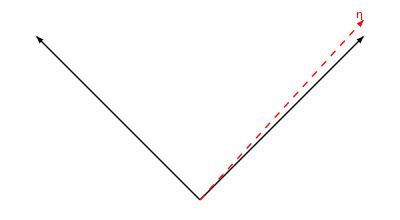

True

```mathematica
ϵ=0.1;
cone={{1,1},{-1,1}};
eta={1,1+ϵ};
DrawVectors[cone,eta]
IsInCone[cone,eta]
```

```mathematica
Qcovectors={{2,0},{-2,0},{0,2},{0,-2},{1,1},{1,-1},{-1,1},{-1,-1}};
SymCovectors={-1,-1,-1,-1,1,1,1,1};
```

```mathematica
RelevantChargesRank2[m1_,m2_,n_]:=Module[{chargeList},
chargeList={};
Do[
If[g*m1-n>0,
AppendTo[chargeList,{{g,0},-1}]];
If[g*m2-n>0,
AppendTo[chargeList,{{0,g},-1}]];
,{g,{-2,2}}];

Do[
If[g1*m1+g2*m2+n+1>0,
AppendTo[chargeList,{{g1,g2},1}]]
,{g1,{-1,1}},{g2,{-1,1}}];

chargeList
]
```

Testing the case (m1,m2)=(-1,0)

```mathematica
eta={1,ϵ}
```

{1,0.1}

```mathematica
hyperplanes=RelevantChargesRank2[-1,0,1]
```

{{{-2,0},-1},{{-1,-1},1},{{-1,1},1},{{1,-1},1},{{1,1},1}}

```mathematica
Qlist=First/@hyperplanes
Slist=Last/@hyperplanes;
singPts=RelevantSingularPoints[Qlist,Slist,eta]
```

{{-2,0},{-1,-1},{-1,1},{1,-1},{1,1}}

{{{-1,0},{4,5}}}

```mathematica
(* Run over singular points*)
i=1;
point=singPts[[i,1]];
Qstar=Qlist[[singPts[[i,2]]]];
Sstar=Slist[[singPts[[i,2]]]];
{flags,kappas}=PositiveFlags[Qstar,eta];
flags
kappas
```

{{{2},{1,2}}}

{{{1,1},{2,0}}}

```mathematica
(* Run over positive flags*)
j=1;
flag=flags[[j]]
kappa=kappas[[j]]
```

{{2},{1,2}}

{{1,1},{2,0}}

```mathematica
Blist=OrderedSet[flag]
```

{2,1}

```mathematica
covectors=Qstar[[Blist]]
```

{{1,1},{1,-1}}

```mathematica
(*Shift Z1loop to the origin of the singular point*)
coordShift=Table[Subscript[x, coordidx]->Subscript[x, coordidx]*y^point[[coordidx]],{coordidx,Length[point]}];
Z1loop=Z1loop/.coordShift//Simplify;
```

```mathematica
(*Rotate coordinates of Z1loop for the residue operation*)
covectorsInv=Inverse[covectors];
coordRotation=Table[Subscript[x, k]->∏_(l=1)^Length[covectors] Subscript[w, l]^covectorsInv[[k,l]],{k,Length[covectors]}];
Z1loop=Z1loop/.coordRotation//Simplify
```

((-1+y)^8 (1+y)^6 (w_1-w_2)^2 (y w_1-w_2) (-w_1+y w_2) (y^2-w_1 w_2)^2 (y^3-w_1 w_2)^3)/(4 y^10 (y^2-w_1)^2 (-1+w_1)^6 (y^2-w_2)^2 (-1+w_2)^6 (y-w_1 w_2))

```mathematica
Z1loop=Z1loop*Det[covectorsInv]
```

-(((-1+y)^8 (1+y)^6 (w_1-w_2)^2 (y w_1-w_2) (-w_1+y w_2) (y^2-w_1 w_2)^2 (y^3-w_1 w_2)^3)/(8 y^10 (y^2-w_1)^2 (-1+w_1)^6 (y^2-w_2)^2 (-1+w_2)^6 (y-w_1 w_2)))

```mathematica
Zresult=ContourInt[Z1loop,Subscript[w, 1],Subscript[w, 2]]//Simplify
```

1/(4 y^6 (1+y)^4)(-1+y)^2 (1+15 y+122 y^2+559 y^3+1659 y^4+3470 y^5+5333 y^6+6141 y^7+5333 y^8+3470 y^9+1659 y^10+559 y^11+122 y^12+15 y^13+y^14)

```mathematica
Zresult==1/(4 y^6 (1+y)^4)(-1+y)^2 (1+15 y+122 y^2+559 y^3+1659 y^4+3470 y^5+5333 y^6+6141 y^7+5333 y^8+3470 y^9+1659 y^10+559 y^11+122 y^12+15 y^13+y^14)//Simplify
```

True

```mathematica
(*Hurray !*)
```

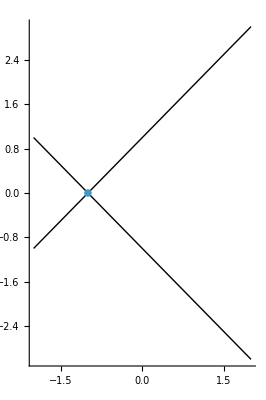

{{{1/2,1/2},{1,3,7}},{{1/2,-1/2},{1,4,8}},{{1/2,-3/2},{1,5}},{{1/2,3/2},{1,6}},{{-1/2,1/2},{2,3,6}},{{-1/2,-1/2},{2,4,5}},{{-1/2,3/2},{2,7}},{{-1/2,-3/2},{2,8}},{{-3/2,1/2},{3,5}},{{3/2,1/2},{3,8}},{{-3/2,-1/2},{4,6}},{{3/2,-1/2},{4,7}},{{-1,0},{5,6}},{{0,-1},{5,8}},{{0,1},{6,7}},{{1,0},{7,8}}}

```mathematica
PlotSingularPoints[QlistRelevant,SlistRelevant]
```

```mathematica
Qstar
```

{{1,0},{0,1},{1,-2}}

```mathematica
{f,k}=FlagList[Qstar];
f
k
```

{{{1},{1,2,3}},{{2},{1,2,3}},{{3},{1,2,3}}}

{{{1,0},{2,-1}},{{0,1},{2,-1}},{{1,-2},{2,-1}}}

```mathematica
{f,k}=PositiveFlags[Qstar,{1,-ϵ}];
f
k
```

{{{1},{1,2,3}},{{2},{1,2,3}}}

{{{1,0},{2,-1}},{{0,1},{2,-1}}}

```mathematica
?JacobiTheta
```

Missing[UnknownSymbol,JacobiTheta]

```mathematica
JacobiTheta
```

JacobiTheta

```mathematica
EllipticTheta[1,u,q] + EllipticTheta[1,-u,q] // Simplify
```

EllipticTheta[1,-u,q]+EllipticTheta[1,u,q]

```mathematica
D[EllipticTheta[1, z, Exp[I Pi τ]], z] /. z -> 0
```

EllipticThetaPrime[1,0,ⅇ^(ⅈ π τ)]

```mathematica
FullSimplify[D[EllipticTheta[1, z, Exp[I Pi τ]], z] /. z -> 0, 
 Assumptions -> Im[τ] > 0]
```

EllipticThetaPrime[1,0,ⅇ^(ⅈ π τ)]

```mathematica
FullSimplify[EllipticThetaPrime[1,0,Exp[I Pi τ]]/(2*π*DedekindEta[ τ]^3),Assumptions->Im[τ>0]]
```

EllipticThetaPrime[1,0,ⅇ^(ⅈ π τ)]/(2 π DedekindEta[τ]^3)

### Finding the residue for n = 1 analytically

#### Writting Z1loop

```mathematica
Nmax=0;
Z1loop=Z1loopExpression[0,0,1]
```

-((Theta1[1/y^2]^6 Theta1[1/y]^2 Theta1[1/x_1^2] Theta1[1/(y x_1^2)] Theta1[x_1^2] Theta1[x_1^2/y] Theta1[1/x_2^2] Theta1[1/(y x_2^2)] Theta1[x_2^2] Theta1[x_2^2/y])/(4 Theta1[1/(y x_1 x_2)]^4 Theta1[x_1/(y x_2)]^4 Theta1[x_2/(y x_1)]^4 Theta1[(x_1 x_2)/y]^4))

```mathematica
Z1loop=Z1loop//Simplify//qExpand
```

((-1+y)^8 (1+y)^6 x_1 (-1+x_1^2)^2 (-y x_1+x_1^3)^3 x_2^4 (y-x_2^2) (-1+x_2^2)^2 (-1+y x_2^2))/(4 y (-1+y x_1^2) (-y x_1+x_2)^6 (x_1-y x_2)^2 (y-x_1 x_2)^2 (-1+y x_1 x_2)^6)

```mathematica
Z1loopTranspose=Z1loop/.Subscript[x, 1]->Subscript[temp, 1]/.Subscript[x, 2]->Subscript[temp, 2];
Z1loopTranspose=Z1loopTranspose/.Subscript[temp, 1]->Subscript[x, 2]/.Subscript[temp, 2]->Subscript[x, 1];
```

```mathematica
Z1loopTranspose==Z1loop//Simplify
```

True

#### Finding the residue for n = 1, (m_1,m_2)=(-1,0):

For this case, the JK residue is at a single point (u_1,u_2)=(-v,0)

```mathematica
ϵ=0.1;
DrawVectors[{{1,-1},{1,1},{1,-1}+{1,1}},{1,ϵ}]
```

-Graphics-

The flags are:
F_1=[Q_(1,-1),R^2], κ^F_1={Q_(1,-1), Q_(1,-1)+Q_(1,1)}
F_2=[Q_(1,1),R^2], κ^F_2={Q_(1,1), Q_(1,-1)+Q_(1,1)}
The relevant flag is F_2. The sign determinant is: ν(F_2)=-1. The residue is:
res_F_2 ω=Res_(u1,-1=0)Res_(u11=0)ω

We want to make a variable change in Z1loop :

```mathematica
Inverse[({{1, 1}, {1, -1}})]//MatrixForm
```

(1/2 | 1/2
1/2 | -1/2)

```mathematica
Theta
```

```mathematica
variableChange={Subscript[x, 1]->Subscript[w, 1]^(1/2)*Subscript[w, 2]^(1/2),Subscript[x, 2]->Subscript[w, 1]^(1/2)*Subscript[w, 2]^(-1/2)};
Z1looptilde=-1/2 ReplaceAll[Z1loop/.Subscript[x, 1]->Subscript[x, 1]*y^-1,variableChange]
```

(Theta1[1/y^2]^6 Theta1[1/y]^2 Theta1[y^2/(w_1 w_2)] Theta1[w_1/w_2] Theta1[w_1/(y w_2)]^3 Theta1[w_2/w_1] Theta1[(w_1 w_2)/y^3]^3 Theta1[(w_1 w_2)/y^2])/(8 Theta1[1/w_1]^6 Theta1[w_1/y^2]^2 Theta1[1/w_2]^6 Theta1[y/(w_1 w_2)] Theta1[w_2/y^2]^2 Theta1[w_2/(y w_1)])

```mathematica
Zresult=ContourInt[Z1looptilde,Subscript[w, 1],Subscript[w, 2]]
```

```mathematica
Zresult=Zresult // Simplify
```

1/(4 y^6 (1+y)^4)(-1+y)^2 (1+15 y+122 y^2+559 y^3+1659 y^4+3470 y^5+5333 y^6+6141 y^7+5333 y^8+3470 y^9+1659 y^10+559 y^11+122 y^12+15 y^13+y^14)

#### Finding the residue for n = 1, (m_1,m_2)=(0,-1):

For this case, the JK residue is at a single point (u_1,u_2)=(0,-v)

```mathematica
ϵ=0.1;
DrawVectors[{{1,1},{-1,1},{1,1}+{-1,1}},{ϵ,1}]
```

-Graphics-

The flags are:
F_1=[Q_(1,1),R^2], κ^F_1={Q_(1,1), Q_(1,1)+Q_(-1,1)}
F_2=[Q_(-1,1),R^2], κ^F_2={Q_(-1,1), Q_(1,1)+Q_(-1,1)}
The relevant flag is F_1. The sign determinant is: ν(F_2)=+1. The residue is:
res_F_2 ω=Res_(u-1,1=0)Res_(u1+u2=0)ω

We want to make a variable change in Z1loop :

```mathematica
Inverse[({{1, 1}, {-1, 1}})]//MatrixForm
```

(1/2 | -1/2
1/2 | 1/2)

```mathematica
variableChange={Subscript[x, 1]->Subscript[w, 1]^(1/2)*Subscript[w, 2]^(-1/2),Subscript[x, 2]->Subscript[w, 1]^(1/2)*Subscript[w, 2]^(1/2)};
Z1looptilde=-1/2 ReplaceAll[Z1loop/.Subscript[x, 2]->Subscript[x, 2]*y^-1,variableChange]//Simplify
```

-(((-1+y)^8 (1+y)^6 (w_1-w_2)^2 (y w_1-w_2) (-w_1+y w_2) (y^2-w_1 w_2)^2 (y^3-w_1 w_2)^3)/(8 y^10 (y^2-w_1)^2 (-1+w_1)^6 (y^2-w_2)^2 (-1+w_2)^6 (y-w_1 w_2)))

```mathematica
Zresult=ContourInt[Z1looptilde,Subscript[w, 1],Subscript[w, 2]]
```

```mathematica
Zresult=Zresult//Simplify
```

1/(4 y^6 (1+y)^4)(-1+y)^2 (1+15 y+122 y^2+559 y^3+1659 y^4+3470 y^5+5333 y^6+6141 y^7+5333 y^8+3470 y^9+1659 y^10+559 y^11+122 y^12+15 y^13+y^14)

#### Finding the residue for n = 1, (m_1,m_2)=(0,0):

```mathematica
DrawVectors[{{-1,1},{1,-1},{1,1},{-1,-1}},{1/2,1}]
```

DrawVectors[{{-1,1},{1,-1},{1,1},{-1,-1}},{1/2,1}]

```mathematica
thetaSimplify=Theta1[x_^exponent_]:>-Theta1[x^(-exponent)]/;exponent<0
```

Theta1[x_^exponent_]:>-Theta1[x^-exponent]/;exponent<0

```mathematica
variableChange={Subscript[x, 1]->Subscript[w, 1]^(1/2)*Subscript[w, 2]^(-1/2),Subscript[x, 2]->Subscript[w, 1]^(1/2)*Subscript[w, 2]^(1/2)};
Z1looptilde=-1/2 ReplaceAll[Z1loop/.Subscript[x, 2]->Subscript[x, 2]*y^-1,variableChange]//.thetaSimplify
```

(Theta1[y]^2 Theta1[y^2]^6 Theta1[y/(w_1 w_2)] Theta1[y^2/(w_1 w_2)] Theta1[w_1/w_2] Theta1[w_1/(y w_2)] Theta1[w_2/w_1] Theta1[w_2/(y w_1)] Theta1[(w_1 w_2)/y^3] Theta1[(w_1 w_2)/y^2])/(8 Theta1[w_1]^4 Theta1[w_1/y^2]^4 Theta1[w_2]^4 Theta1[w_2/y^2]^4)

```mathematica
Zresult=ContourInt[Z1looptilde,Subscript[w, 1],Subscript[w, 2]]
```

-1/(4 y^3 (1+y)^4)(-1+y)^2 (1+4 y+14 y^2+32 y^3+38 y^4+32 y^5+14 y^6+4 y^7+y^8)

#### Final result for the case n = 1

```mathematica
Zm11=1/(4 y^6 (1+y)^4)(-1+y)^2 (1+15 y+122 y^2+559 y^3+1659 y^4+3470 y^5+5333 y^6+6141 y^7+5333 y^8+3470 y^9+1659 y^10+559 y^11+122 y^12+15 y^13+y^14);
Zm00=-1/(4 y^3 (1+y)^4)(-1+y)^2 (1+4 y+14 y^2+32 y^3+38 y^4+32 y^5+14 y^6+4 y^7+y^8);
Zfinal=4*Zm11+Zm00//Simplify
```

1/(4 y^6)(-1+y)^2 (4+44 y+288 y^2+803 y^3+1512 y^4+1804 y^5+1512 y^6+803 y^7+288 y^8+44 y^9+4 y^10)

#### Result for the case n = 0

Comparing the result with the analytic computation:

```mathematica
Nmax=2
```

2

```mathematica
Zexpand=Z1loop//qForm//qExpand
```

((-1+y^2)^2 (w_1-w_2)^2 (y^2-w_1 w_2)^2)/(4 q^(1/4) (y^2-w_1)^2 (-1+w_1)^2 (y^2-w_2)^2 (-1+w_2)^2)+(q^(3/4) (1-1/y^2)^2 y^6 (1-y^2/(w_1 w_2)) (1-w_1/w_2) (1-w_2/w_1) (2-2/y^2-2 y^2+2/w_1+(2 y^2)/w_1+2 w_1+(2 w_1)/y^2+2/w_2+(2 y^2)/w_2-(2 y^2)/(w_1 w_2)-(2 w_1)/w_2+2 w_2+(2 w_2)/y^2-(2 w_2)/w_1-(2 w_1 w_2)/y^2) (1-(w_1 w_2)/y^2))/(4 (1-1/w_1)^2 (1-y^2/w_1)^2 w_1^2 (1-1/w_2)^2 (1-y^2/w_2)^2 w_2^2)+(q^(7/4) (1-1/y^2)^2 y^6 (1-y^2/(w_1 w_2)) (1-w_1/w_2) (1-w_2/w_1) (1-(w_1 w_2)/y^2) (5+1/y^4-6/y^2-2 y^2-2 (2-2/y^2) y^2+y^4+3/w_1^2+(3 y^4)/w_1^2+2/w_1+(2 y^2)/w_1+(2 (2-2/y^2-2 y^2))/w_1+(2 y^2 (2-2/y^2-2 y^2+2/w_1))/w_1+2 w_1+(2 w_1)/y^2+2 (2-2/y^2-2 y^2+2/w_1+(2 y^2)/w_1) w_1+3 w_1^2+(3 w_1^2)/y^4+(2 w_1 (2-2/y^2-2 y^2+2/w_1+(2 y^2)/w_1+2 w_1))/y^2+3/w_2^2+(3 y^4)/w_2^2+y^4/(w_1^2 w_2^2)+w_1^2/w_2^2+2/w_2+(2 y^2)/w_2-(2 y^2)/(w_1 w_2)-(2 w_1)/w_2+(2 (2-2/y^2-2 y^2+2/w_1+(2 y^2)/w_1+2 w_1+(2 w_1)/y^2))/w_2+(2 y^2 (2-2/y^2-2 y^2+2/w_1+(2 y^2)/w_1+2 w_1+(2 w_1)/y^2+2/w_2))/w_2-(2 y^2 (2-2/y^2-2 y^2+2/w_1+(2 y^2)/w_1+2 w_1+(2 w_1)/y^2+2/w_2+(2 y^2)/w_2))/(w_1 w_2)-(2 w_1 (2-2/y^2-2 y^2+2/w_1+(2 y^2)/w_1+2 w_1+(2 w_1)/y^2+2/w_2+(2 y^2)/w_2-(2 y^2)/(w_1 w_2)))/w_2+2 w_2+(2 w_2)/y^2-(2 w_2)/w_1-(2 w_1 w_2)/y^2+2 (2-2/y^2-2 y^2+2/w_1+(2 y^2)/w_1+2 w_1+(2 w_1)/y^2+2/w_2+(2 y^2)/w_2-(2 y^2)/(w_1 w_2)-(2 w_1)/w_2) w_2+3 w_2^2+(3 w_2^2)/y^4+w_2^2/w_1^2+(w_1^2 w_2^2)/y^4+1/y^2 2 w_2 (2-2/y^2-2 y^2+2/w_1+(2 y^2)/w_1+2 w_1+(2 w_1)/y^2+2/w_2+(2 y^2)/w_2-(2 y^2)/(w_1 w_2)-(2 w_1)/w_2+2 w_2)-1/w_1 2 w_2 (2-2/y^2-2 y^2+2/w_1+(2 y^2)/w_1+2 w_1+(2 w_1)/y^2+2/w_2+(2 y^2)/w_2-(2 y^2)/(w_1 w_2)-(2 w_1)/w_2+2 w_2+(2 w_2)/y^2)-1/y^2 2 w_1 w_2 (2-2/y^2-2 y^2+2/w_1+(2 y^2)/w_1+2 w_1+(2 w_1)/y^2+2/w_2+(2 y^2)/w_2-(2 y^2)/(w_1 w_2)-(2 w_1)/w_2+2 w_2+(2 w_2)/y^2-(2 w_2)/w_1)))/(4 (1-1/w_1)^2 (1-y^2/w_1)^2 w_1^2 (1-1/w_2)^2 (1-y^2/w_2)^2 w_2^2)

```mathematica
ResultQexpand=ContourInt[Zexpand,Subscript[w, 1],Subscript[w, 2]]
```

-(1+6 q+27 q^2)/(2 q^(1/4))

```mathematica
ResultAnalytic=-1/(2(2π*Eta[q]^3)^2)//qExpand
```

-1/(8 π^2 q^(1/4))-(3 q^(3/4))/(4 π^2)-(27 q^(7/4))/(8 π^2)

```mathematica
ResultAnalytic/ResultQexpand//Simplify
```

1/(4 π^2)

```mathematica
D[f[z]/h[z]^4,{z,3}]/. h'[z]->0/. Derivative[3][h][z]->0
```

-(12 f'[z] h''[z])/h[z]^5+(f^(3)[z])/h[z]^4

```mathematica
D[f[-z],z]
```

-f'[-z]

```mathematica
Z
```

```mathematica
myFunc=Z1loop
```

-((Theta1[y^2]^2 Theta1[y^2/(w_1 w_2)] Theta1[w_1/w_2] Theta1[w_2/w_1] Theta1[(w_1 w_2)/y^2])/(4 Theta1[w_1]^2 Theta1[w_1/y^2]^2 Theta1[w_2]^2 Theta1[w_2/y^2]^2))

```mathematica
myFuncorder2=Coefficient[myFunc,Θ[Subscript[u, 1]],-2]
myFuncDer=D[myFuncorder2,Subscript[u, 1]]/.Subscript[u, 1]->0/.simplifyRule
```

-((Θ[2 v]^2 Θ[2 v-u_1-u_2] Θ[u_1-u_2] Θ[-u_1+u_2] Θ[-2 v+u_1+u_2])/(4 Θ[-2 v+u_1]^2 Θ[u_2]^2 Θ[-2 v+u_2]^2))

(Θ[2 v-u_2] Θ'[2 v])/(2 Θ[2 v] Θ[-2 v+u_2])-Θ'[2 v-u_2]/(4 Θ[-2 v+u_2])-(Θ[2 v-u_2] Θ'[u_2])/(2 Θ[u_2] Θ[-2 v+u_2])+(Θ[2 v-u_2] Θ'[-2 v+u_2])/(4 Θ[-2 v+u_2]^2)

```mathematica
FisrtResidue=1/(Derivative[1][Θ][0])^2*myFuncDer
```

((Θ[2 v-u_2] Θ'[2 v])/(2 Θ[2 v] Θ[-2 v+u_2])-Θ'[2 v-u_2]/(4 Θ[-2 v+u_2])-(Θ[2 v-u_2] Θ'[u_2])/(2 Θ[u_2] Θ[-2 v+u_2])+(Θ[2 v-u_2] Θ'[-2 v+u_2])/(4 Θ[-2 v+u_2]^2))/Θ'[0]^2

```mathematica
ResidueFormula[2]
```

f'[z]/h[z]^2

```mathematica
Coefficient[FisrtResidue,Θ[Subscript[u, 2]],-1]/(Derivative[1][Θ][0])/.Subscript[u, 2]->0/.simplifyRule
```

1/(2 Θ'[0]^2)

```mathematica
ResidueFormula[1]
```

f[z]/h[z]

```mathematica
D[order2,Subscript[u, 2]]/.Subscript[u, 2]->0/.simplifyRule
```

-2 Θ[v]^3 Θ[3 v] Θ'[v]^2+(4 Θ[v]^4 Θ[3 v] Θ'[v] Θ'[2 v])/Θ[2 v]-(2 Θ[v]^5 Θ[3 v] Θ'[2 v]^2)/Θ[2 v]^2-2 Θ[v]^4 Θ'[v] Θ'[3 v]+(4 Θ[v]^5 Θ'[2 v] Θ'[3 v])/Θ[2 v]+Θ[v]^4 Θ[3 v] Θ''[v]-(2 Θ[v]^5 Θ[3 v] Θ''[2 v])/Θ[2 v]-Θ[v]^5 Θ''[3 v]

```mathematica
order3=Coefficient[myFuncDer,Θ[Subscript[u, 2]],-3]
```

1/Θ[-2 v+u_2]^3 Θ[v]^2 Θ[2 v]^2 Θ[-v-u_2] Θ[v-u_2] Θ[2 v-u_2] Θ[-3 v+u_2] Θ[-v+u_2] Θ'[-u_2]+1/Θ[-2 v+u_2]^3 Θ[v]^2 Θ[2 v]^2 Θ[-v-u_2] Θ[v-u_2] Θ[2 v-u_2] Θ[-3 v+u_2] Θ[-v+u_2] Θ'[u_2]

```mathematica
order=3;
D[f[z]/h[z]^order,{z,order-1}]/. h'[z]->0/. Derivative[3][h][z]->0/. Derivative[5][h][z]->0
```

f''[z]/h[z]^3-(3 f[z] h''[z])/h[z]^4

```mathematica
(order3/.Subscript[u, 2]->0/.simplifyRule)*(-3*Θ'''[0]/(Θ'[0])^4)
```

-(6 Θ[v]^5 Θ[3 v] Θ'''[0])/Θ'[0]^3

```mathematica
(D[order3,{Subscript[u, 2],2}]/.Subscript[u, 2]->0/.simplifyRule)*(1/(Θ'[0])^3)/.simplifyRule
```

ReplaceAll::reps: {simplifyRule} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

(0/.simplifyRule)/Θ'[0]^3/.simplifyRule

## A_1 compactification with flux n=2

### Find Z1loop and hyperplanes

```mathematica
Z1loopExpression[m1_,m2_,n_]:=Module[{Z,f1,f2,f3},
f1[g_]:=(1/Theta1[Subscript[x, 1]^g*y^-1])^(g*m1-n);
f2[g_]:=(1/Theta1[Subscript[x, 2]^g*y^-1])^(g*m2-n);
f3[g1_,g2_]:=(1/Theta1[Subscript[x, 1]^g1*Subscript[x, 2]^g2*y])^(2(g1*m1+g2*m2+n+1));
Z=Product[f1[g]*f2[g],{g,{-2,0,2}}]*Product[f3[g1,g2],{g1,{-1,1}},{g2,{-1,1}}];
Z=Z*1/4*ⅈ^2*Eta^4*(1/Theta1[y^-2])^(2*(-2n-1))*∏_(i=1)^2 (Theta1[Subscript[x, i]^2]*Theta1[Subscript[x, i]^-2])/(ⅈ*Eta)^2;
Z
]
FindHyperplanes[m1_,m2_,n_]:=Module[{Qcovectors={},Scovectors={}},
Do[
If[g*m1-n>0,
Do[
AppendTo[Qcovectors,{g,0}];
AppendTo[Scovectors,-v-(a+b*τ)];
,{a,{0,1}},{b,{0,1}}]
];
If[g*m2-n>0,
Do[
AppendTo[Qcovectors,{0,g}];
AppendTo[Scovectors,-v-(a+b*τ)];
,{a,{0,1}},{b,{0,1}}]
];
,{g,{-2,2}}];

Do[
If[2(g1*m1+g2*m2+n+1)>0,
AppendTo[Qcovectors,{g1,g2}];
AppendTo[Scovectors,v];
];
,{g1,{-1,1}},{g2,{-1,1}}];

{Qcovectors,Scovectors}
]
```

### JK residue

#### Case n = 1

```mathematica
Z1loopExpression[0,0,1]
```

-((Theta1[1/y^2]^6 Theta1[1/y]^2 Theta1[1/x_1^2] Theta1[1/(y x_1^2)] Theta1[x_1^2] Theta1[x_1^2/y] Theta1[1/x_2^2] Theta1[1/(y x_2^2)] Theta1[x_2^2] Theta1[x_2^2/y])/(4 Theta1[y/(x_1 x_2)]^4 Theta1[(y x_1)/x_2]^4 Theta1[(y x_2)/x_1]^4 Theta1[y x_1 x_2]^4))

```mathematica
Listm={{0,0},{1,0},{-1,0},{0,1},{0,-1}};
n=1;

ListZ1loop={};
Do[

{m1,m2}=Listm[[i]];
Z1loop=Z1loopExpression[m1,m2,n];
{Qcovectors,Scovectors}=FindHyperplanes[m1,m2,n];
ϵ=0.1;
eta=-{m1,m2}+{ϵ,-2ϵ};
AppendTo[ListZ1loop,JKResidue[Z1loop,Qcovectors,Scovectors,eta]];
,{i,Length[Listm]}]
```

```mathematica
Z1loop=Flatten[ListZ1loop][[Range[2,5]]]//Total
```

-((Theta1[1/y^2]^6 Theta1[1/y]^2 Theta1[y^2/(w_1 w_2)] Theta1[w_1/w_2] Theta1[w_1/(y w_2)] Theta1[w_2/w_1] Theta1[w_2/(y w_1)] Theta1[(w_1 w_2)/y^3]^3 Theta1[(w_1 w_2)/y^2])/(2 Theta1[y^2/w_1]^6 Theta1[w_1]^2 Theta1[y^2/w_2]^6 Theta1[y/(w_1 w_2)] Theta1[w_2]^2))

```mathematica
Z1loopLinear=LinearizeWs[ThetaLinearize[Z1loop/.replacementRule]]/.simplifyRule
```

-((Θ[v]^2 Θ[2 v]^6 Θ[2 v-u_1-u_2] Θ[u_1-u_2] Θ[-v+u_1-u_2] Θ[-u_1+u_2] Θ[-v-u_1+u_2] Θ[-3 v+u_1+u_2]^3 Θ[-2 v+u_1+u_2])/(2 Θ[2 v-u_1]^6 Θ[u_1]^2 Θ[2 v-u_2]^6 Θ[v-u_1-u_2] Θ[u_2]^2))

```mathematica
Z1loopLinearU1=Order2Residue[Z1loopLinear,Subscript[u, 1]]//Thread
```

1/(4 Eta^6 π^2)((3 Θ[v]^2 Θ[-v-u_2] Θ[-3 v+u_2]^3 Θ[-2 v+u_2] Θ[-v+u_2] Θ'[2 v])/(Θ[2 v] Θ[v-u_2] Θ[2 v-u_2]^5)+(Θ[v]^2 Θ[-3 v+u_2]^3 Θ[-2 v+u_2] Θ[-v+u_2] Θ'[-v-u_2])/(2 Θ[v-u_2] Θ[2 v-u_2]^5)+(Θ[v]^2 Θ[-v-u_2] Θ[-3 v+u_2]^3 Θ[-2 v+u_2] Θ[-v+u_2] Θ'[v-u_2])/(2 Θ[v-u_2]^2 Θ[2 v-u_2]^5)-(Θ[v]^2 Θ[-v-u_2] Θ[-3 v+u_2]^3 Θ[-2 v+u_2] Θ[-v+u_2] Θ'[2 v-u_2])/(2 Θ[v-u_2] Θ[2 v-u_2]^6)-(Θ[v]^2 Θ[-v-u_2] Θ[-3 v+u_2]^3 Θ[-2 v+u_2] Θ[-v+u_2] Θ'[u_2])/(Θ[v-u_2] Θ[2 v-u_2]^5 Θ[u_2])+(3 Θ[v]^2 Θ[-v-u_2] Θ[-3 v+u_2]^2 Θ[-2 v+u_2] Θ[-v+u_2] Θ'[-3 v+u_2])/(2 Θ[v-u_2] Θ[2 v-u_2]^5)+(Θ[v]^2 Θ[-v-u_2] Θ[-3 v+u_2]^3 Θ[-v+u_2] Θ'[-2 v+u_2])/(2 Θ[v-u_2] Θ[2 v-u_2]^5)-(Θ[v]^2 Θ[-v-u_2] Θ[-3 v+u_2]^3 Θ[-2 v+u_2] Θ'[-v+u_2])/(2 Θ[v-u_2] Θ[2 v-u_2]^5))

```mathematica
((Coefficient[Z1loopLinearU1,Θ[Subscript[u, 2]],-1]*1/(2π*Eta^3))/.Subscript[u, 2]->0)/.simplifyRule
```

-(Θ[v]^3 Θ[3 v]^3)/(4 Eta^6 π^2 Θ[2 v]^4)

```mathematica
ResidueFormula[4]
```

-(12 f'[z] h''[z])/h[z]^5+(f^(3)[z])/h[z]^4

```mathematica
Z1loopLinear=LinearizeWs[ThetaLinearize[Flatten[ListZ1loop][[1]]/.replacementRule]]
```

-((Θ[-2 v]^6 Θ[-v]^2 Θ[v-u_1-u_2] Θ[2 v-u_1-u_2] Θ[u_1-u_2] Θ[-v+u_1-u_2] Θ[-u_1+u_2] Θ[-v-u_1+u_2] Θ[-3 v+u_1+u_2] Θ[-2 v+u_1+u_2])/(8 Θ[2 v-u_1]^4 Θ[u_1]^4 Θ[2 v-u_2]^4 Θ[u_2]^4))

```mathematica
f=Coefficient[Z1loopLinear,Θ[Subscript[u, 1]],-4]
h=2π*Eta^3
```

-((Θ[-2 v]^6 Θ[-v]^2 Θ[v-u_1-u_2] Θ[2 v-u_1-u_2] Θ[u_1-u_2] Θ[-v+u_1-u_2] Θ[-u_1+u_2] Θ[-v-u_1+u_2] Θ[-3 v+u_1+u_2] Θ[-2 v+u_1+u_2])/(8 Θ[2 v-u_1]^4 Θ[2 v-u_2]^4 Θ[u_2]^4))

2 Eta^3 π

```mathematica
(*First derivative term*)
df=D[f,{Subscript[u, 1],1}]/.Subscript[u, 1]->0//.simplifyRule
```

(Θ[v]^2 Θ[2 v] Θ[-v-u_2] Θ[v-u_2] Θ[-3 v+u_2] Θ[-2 v+u_2] Θ[-v+u_2] Θ'[2 v])/(2 Θ[2 v-u_2]^3 Θ[u_2]^2)+(Θ[v]^2 Θ[2 v]^2 Θ[v-u_2] Θ[-3 v+u_2] Θ[-2 v+u_2] Θ[-v+u_2] Θ'[-v-u_2])/(8 Θ[2 v-u_2]^3 Θ[u_2]^2)-(Θ[v]^2 Θ[2 v]^2 Θ[-v-u_2] Θ[-3 v+u_2] Θ[-2 v+u_2] Θ[-v+u_2] Θ'[v-u_2])/(8 Θ[2 v-u_2]^3 Θ[u_2]^2)-(Θ[v]^2 Θ[2 v]^2 Θ[-v-u_2] Θ[v-u_2] Θ[-3 v+u_2] Θ[-2 v+u_2] Θ[-v+u_2] Θ'[2 v-u_2])/(8 Θ[2 v-u_2]^4 Θ[u_2]^2)-(Θ[v]^2 Θ[2 v]^2 Θ[-v-u_2] Θ[v-u_2] Θ[-3 v+u_2] Θ[-2 v+u_2] Θ[-v+u_2] Θ'[u_2])/(4 Θ[2 v-u_2]^3 Θ[u_2]^3)+(Θ[v]^2 Θ[2 v]^2 Θ[-v-u_2] Θ[v-u_2] Θ[-2 v+u_2] Θ[-v+u_2] Θ'[-3 v+u_2])/(8 Θ[2 v-u_2]^3 Θ[u_2]^2)+(Θ[v]^2 Θ[2 v]^2 Θ[-v-u_2] Θ[v-u_2] Θ[-3 v+u_2] Θ[-v+u_2] Θ'[-2 v+u_2])/(8 Θ[2 v-u_2]^3 Θ[u_2]^2)-(Θ[v]^2 Θ[2 v]^2 Θ[-v-u_2] Θ[v-u_2] Θ[-3 v+u_2] Θ[-2 v+u_2] Θ'[-v+u_2])/(8 Θ[2 v-u_2]^3 Θ[u_2]^2)

```mathematica
(*First derivative term - Pole of order 2*)
Order2Residue[df,Subscript[u, 2]]*1/h^5*E2*h
```

1/(64 Eta^18 π^6)E2 (1/4 Θ[v]^3 Θ[3 v] Θ'[v]^2-(Θ[v]^4 Θ[3 v] Θ'[v] Θ'[2 v])/(2 Θ[2 v])+(Θ[v]^5 Θ[3 v] Θ'[2 v]^2)/(4 Θ[2 v]^2)+1/4 Θ[v]^4 Θ'[v] Θ'[3 v]-(Θ[v]^5 Θ'[2 v] Θ'[3 v])/(2 Θ[2 v])-1/8 Θ[v]^4 Θ[3 v] Θ''[v]+(Θ[v]^5 Θ[3 v] Θ''[2 v])/(4 Θ[2 v])+1/8 Θ[v]^5 Θ''[3 v])

```mathematica
(*Third derivative term*)
df3=D[f,{Subscript[u, 1],3}]/.Subscript[u, 1]->0//.simplifyRule;
```

```mathematica
(*Third derivative term - Pole of order 2*)
Coefficient[df3,Θ[Subscript[u, 2]],-2];
```

```mathematica
Order2Residue[df3,Subscript[u, 2]]*1/h^4
```

1/(64 Eta^18 π^6)((3 Θ[v]^3 Θ[3 v] Θ'[v]^2 Θ'[2 v]^2)/Θ[2 v]^2-(3 Θ[v]^4 Θ[3 v] Θ'[v] Θ'[2 v]^3)/Θ[2 v]^3-(3 Θ[v]^5 Θ[3 v] Θ'[2 v]^4)/Θ[2 v]^4+(6 Θ[v]^4 Θ'[v] Θ'[2 v]^2 Θ'[3 v])/Θ[2 v]^2-(3 Θ[v]^5 Θ'[2 v]^3 Θ'[3 v])/Θ[2 v]^3-(3 Θ[v]^4 Θ'[2 v] Θ'[3 v] Θ''[v])/Θ[2 v]-3/4 Θ[v]^3 Θ[3 v] Θ''[v]^2-(3 Θ[v]^3 Θ[3 v] Θ'[v]^2 Θ''[2 v])/Θ[2 v]-(3 Θ[v]^4 Θ[3 v] Θ'[v] Θ'[2 v] Θ''[2 v])/(2 Θ[2 v]^2)+(9 Θ[v]^5 Θ[3 v] Θ'[2 v]^2 Θ''[2 v])/Θ[2 v]^3-(3 Θ[v]^5 Θ'[2 v] Θ'[3 v] Θ''[2 v])/(2 Θ[2 v]^2)+(3 Θ[v]^4 Θ[3 v] Θ''[v] Θ''[2 v])/Θ[2 v]-(9 Θ[v]^5 Θ[3 v] Θ''[2 v]^2)/(4 Θ[2 v]^2)-(3 Θ[v]^4 Θ'[v] Θ'[2 v] Θ''[3 v])/Θ[2 v]+(3 Θ[v]^5 Θ'[2 v]^2 Θ''[3 v])/Θ[2 v]^2+3/4 Θ[v]^4 Θ''[v] Θ''[3 v]+1/2 Θ[v]^4 Θ'[v] Θ^(3)[-3 v]-(Θ[v]^5 Θ'[2 v] Θ^(3)[-3 v])/Θ[2 v]+(Θ[v]^4 Θ[3 v] Θ'[v] Θ^(3)[-2 v])/(2 Θ[2 v])-(3 Θ[v]^5 Θ[3 v] Θ'[2 v] Θ^(3)[-2 v])/(2 Θ[2 v]^2)+(Θ[v]^5 Θ'[3 v] Θ^(3)[-2 v])/(2 Θ[2 v])+Θ[v]^3 Θ[3 v] Θ'[v] Θ^(3)[-v]-(Θ[v]^4 Θ[3 v] Θ'[2 v] Θ^(3)[v])/Θ[2 v]+1/2 Θ[v]^4 Θ'[3 v] Θ^(3)[v]-(Θ[v]^5 Θ[3 v] Θ'[2 v] Θ^(3)[2 v])/(2 Θ[2 v]^2)-1/8 Θ[v]^5 Θ^(4)[-3 v]-(Θ[v]^5 Θ[3 v] Θ^(4)[-2 v])/(8 Θ[2 v])+1/4 Θ[v]^4 Θ[3 v] Θ^(4)[-v]+1/8 Θ[v]^4 Θ[3 v] Θ^(4)[v]+(Θ[v]^5 Θ[3 v] Θ^(4)[2 v])/(8 Θ[2 v]))

```mathematica
(*Third derivative term - Pole of order 3*)
```

```mathematica
Formula1=-(Θ[v]^3 Θ[3 v]^3)/(4 Eta^6 π^2 Θ[2 v]^4)
```

-(Θ[v]^3 Θ[3 v]^3)/(4 Eta^6 π^2 Θ[2 v]^4)

```mathematica
Nmax=0
```

0

```mathematica
Formula3=1/(4 y^6 (1+y)^4)(-1+y)^2 (1+15 y+122 y^2+559 y^3+1659 y^4+3470 y^5+5333 y^6+6141 y^7+5333 y^8+3470 y^9+1659 y^10+559 y^11+122 y^12+15 y^13+y^14);
```

```mathematica
4*Formula3//Series[#,{y,0,5}]&
```

1/y^6+9/y^5+51/y^4+68/y^3+48/y^2-102/y-151-99 y+46 y^2+61 y^3+79 y^4-56 y^5+O[y]^6

```mathematica
(2π)^2*Formula1//ΘForm//qForm//Series[#,{y,0,5}]&
```

1/y^2-3/y+7-16 y+31 y^2-55 y^3+92 y^4-145 y^5+O[y]^6

```mathematica
Nmax=2;
Formula2=1/Eta[q]^6*((Theta1[y^2,q]^2)/Theta1[y,q])^2;
Nmax=0;
Formula2//qExpand//Simplify
```

-((-1+y)^2 (1+y)^4)/y^3

```mathematica
(1+y)^4
```

```mathematica
Nmax=0;
ZqExpanded=qExpand[ListZ1loop//Flatten//Total//qForm];
ZqExpandedRes=ContourInt[ZqExpanded,Subscript[w, 1],Subscript[w, 2]];
```

```mathematica
ZqExpandedRes//qExpand//Simplify
```

((-1+y)^2 (1-2 y+5 y^2+5 y^4-2 y^5+y^6))/(4 y^3 (1+y)^2)

#### Case n = -1

```mathematica
Listm={{0,0}};
n=-1;

ListZ1loop={};
Do[

{m1,m2}=Listm[[i]];
Z1loop=Z1loopExpression[m1,m2,n];
{Qcovectors,Scovectors}=FindHyperplanes[m1,m2,n];
ϵ=0.1;
eta=-{m1,m2}+{ϵ,-2ϵ};
AppendTo[ListZ1loop,JKResidue[Z1loop,Qcovectors,Scovectors,eta]];
,{i,Length[Listm]}]
```

```mathematica
replacementRule={Theta1[q*x_]:>-x^-1*(√q)^-1*Theta1[x],
Theta1[q^-1*x_]:>-x*(√q)^-1*Theta1[x]};
```

```mathematica
Nmax=5;
RHS=Theta1[q^-1*x]/.replacementRule//qForm//qExpand;
LHS=Theta1[q^-1*x]//qForm//qExpand;
Nmax=4;
RHS==LHS//qExpand//Simplify
```

True

```mathematica
ListZ=ListZ1loop[[1]]/.replacementRule;
```

```mathematica
Union[ListZ]
```

{-((Theta1[1/(y w_1)] Theta1[y w_1] Theta1[1/(y w_2)] Theta1[y w_2])/(16 Theta1[1/y^2]^2 Theta1[1/y]^2 Theta1[1/(y^2 w_1)] Theta1[w_1] Theta1[1/(y^2 w_2)] Theta1[w_2]))}

Final result :

```mathematica
(2π*ⅈ)^2*16*SimpleResidue[ListZ[[1]],Subscript[w, 1],Subscript[w, 2]]
```

Theta1[y]^2/(Eta^6 Theta1[1/y^2]^4)

#### Case n = -2

```mathematica
Listm={{0,0}};
n=-2;

ListZ1loop={};
Do[

{m1,m2}=Listm[[i]];
Z1loop=Z1loopExpression[m1,m2,n];
{Qcovectors,Scovectors}=FindHyperplanes[m1,m2,n];
ϵ=0.1;
eta=-{m1,m2}+{ϵ,-2ϵ};
AppendTo[ListZ1loop,JKResidue[Z1loop,Qcovectors,Scovectors,eta]];
,{i,Length[Listm]}]
```

```mathematica
ListZ=LinearizeWs[ThetaLinearize[(ListZ1loop[[1]]/.replacementRule)]]/.simplifyRule;
```

```mathematica
ListZ1loop[[1]]//Length
```

16

```mathematica
Nmax=0;
```

```mathematica
TestQexp=((ListZ1loop[[1]]/.replacementRule))//Total;
TestAnalytic=LinearizeWs[ThetaLinearize[(TestQexp/.replacementRule)]]/.simplifyRule;
TestAnalytic=TestAnalytic/.{Subscript[w, 1]->ⅇ^(2π*ⅈ*Subscript[u, 1]),Subscript[w, 2]->ⅇ^(2π*ⅈ*Subscript[u, 2])};
```

```mathematica
TestQexp=Theta1[-1/(√q √Subscript[w, 1] √Subscript[w, 2])]^2 Theta1[-(√q y √Subscript[w, 1])/(√Subscript[w, 2])]^2 Theta1[-(y √Subscript[w, 2])/(√q √Subscript[w, 1])]^2 Theta1[-√q y^2 √Subscript[w, 1] √Subscript[w, 2]]^2 
TestAnalytic=Θ[1/2-τ/2-Subscript[u, 1]/2-Subscript[u, 2]/2]^2 Θ[1/2+v+τ/2+Subscript[u, 1]/2-Subscript[u, 2]/2]^2 Θ[1/2+v-τ/2-Subscript[u, 1]/2+Subscript[u, 2]/2]^2 Θ[1/2+2 v+τ/2+Subscript[u, 1]/2+Subscript[u, 2]/2]^2
```

Theta1[-1/(√q √w_1 √w_2)]^2 Theta1[-(√q y √w_1)/(√w_2)]^2 Theta1[-(y √w_2)/(√q √w_1)]^2 Theta1[-√q y^2 √w_1 √w_2]^2

Θ[1/2-τ/2-u_1/2-u_2/2]^2 Θ[1/2+v+τ/2+u_1/2-u_2/2]^2 Θ[1/2+v-τ/2-u_1/2+u_2/2]^2 Θ[1/2+2 v+τ/2+u_1/2+u_2/2]^2

```mathematica
TestQexp=Theta1[-1/(√q √Subscript[w, 1] √Subscript[w, 2])]^2 Theta1[-(√q y √Subscript[w, 1])/(√Subscript[w, 2])]^2 
TestAnalytic=Θ[1/2-τ/2-Subscript[u, 1]/2-Subscript[u, 2]/2]^2 Θ[1/2+v+τ/2+Subscript[u, 1]/2-Subscript[u, 2]/2]^2
```

Theta1[-1/(√q √w_1 √w_2)]^2 Theta1[-(√q y √w_1)/(√w_2)]^2

Θ[1/2-τ/2-u_1/2-u_2/2]^2 Θ[1/2+v+τ/2+u_1/2-u_2/2]^2

Check the two are equal:

```mathematica
?Theta1
```

```mathematica
Nmax=3;
RHS=TestQexp//qForm//Simplify//qExpand//Simplify//qExpand;
LHS=(((TestAnalytic//ΘForm//qForm)//qExpand)/.{Subscript[u, 1]->1/(2π*ⅈ)Log[Subscript[w, 1]],Subscript[u, 2]->1/(2π*ⅈ)Log[Subscript[w, 2]]})//Simplify//qExpand//Simplify//qExpand;
Nmax=2;
RHS=RHS//qExpand
LHS=LHS//qExpand
RHS==LHS//Simplify
Nmax=0;
```

1/(√q y w_1)+(q^(3/2) (y^4 w_1^2+4 y^2 w_1 w_2+4 y^4 w_1^3 w_2+w_2^2+4 y^2 w_1^2 w_2^2+y^4 w_1^4 w_2^2+4 w_1 w_2^3+4 y^2 w_1^3 w_2^3+w_1^2 w_2^4))/(y^3 w_1^3 w_2^2)+(2 (y √(w_1 w_2)+y^2 w_1 √(w_1 w_2)+w_2 √(w_1 w_2)+y w_1 w_2 √(w_1 w_2)))/(y^2 w_1^2 w_2)+1/(y^4 w_1^4 w_2^3)q^2 ((y^2 w_1+w_2) (2 y^4 w_1^(7/2) w_2^(3/2)+2 w_1^(3/2) w_2^(7/2)+2 y^2 w_1 w_2 √(w_1 w_2)+2 y^2 (w_1 w_2)^(7/2))+y √(w_1 w_2) (2 y^2 w_1^4 w_2^2 (2 y^2+y w_2+w_2^2)+2 w_1 w_2 (y^2+y w_2+2 w_2^2)+2 y w_1^3 w_2 (2 y^3+y w_2^2+w_2^3)+w_1^2 w_2 (2 y^3+2 y^2 w_2+4 w_2^3)))+1/(y^4 w_1^4 w_2^3)√q ((y^2 w_1+w_2) (w_1^2 w_2 (2 y^2 w_2+y w_2^2)+y w_1^3 w_2 (y^2 w_2+2 y w_2^2))+y √(w_1 w_2) (2 y w_1^(3/2) w_2^(5/2)+2 y^3 w_1^(7/2) w_2^(5/2)+2 y w_1^(5/2) w_2^(7/2)+y^2 w_1 w_2 √(w_1 w_2)+y^2 (w_1 w_2)^(7/2)+2 y^2 w_1^2 w_2 (√w_1 w_2^(3/2)+y √(w_1 w_2))))+1/(y^4 w_1^4 w_2^3)q (y √(w_1 w_2) (y w_1 w_2^2+y^3 w_1^4 w_2^3+w_1^2 w_2 (y^3+2 y w_2^2)+y w_1^3 w_2 (2 y^2 w_2+w_2^3))+(y^2 w_1+w_2) (2 y w_1^(3/2) w_2^(5/2)+2 y^3 w_1^(7/2) w_2^(5/2)+2 y w_1^(5/2) w_2^(7/2)+y^2 w_1 w_2 √(w_1 w_2)+y^2 (w_1 w_2)^(7/2)+2 y^2 w_1^2 w_2 (√w_1 w_2^(3/2)+y √(w_1 w_2))))

1/(√q y w_1)+(2 (y+y^2 w_1+w_2+y w_1 w_2))/(y^2 w_1^(3/2) √w_2)+1/(y^3 w_1^(5/2) w_2^(3/2))2 q (y^3 w_1+y^4 w_1^2+y w_2+2 y^2 w_1 w_2+2 y^3 w_1^2 w_2+y^4 w_1^3 w_2+w_2^2+2 y w_1 w_2^2+2 y^2 w_1^2 w_2^2+y^3 w_1^3 w_2^2+w_1 w_2^3+y w_1^2 w_2^3)+(q^(3/2) (y^4 w_1^2+4 y^2 w_1 w_2+4 y^4 w_1^3 w_2+w_2^2+4 y^2 w_1^2 w_2^2+y^4 w_1^4 w_2^2+4 w_1 w_2^3+4 y^2 w_1^3 w_2^3+w_1^2 w_2^4))/(y^3 w_1^3 w_2^2)+1/(y^4 w_1^(7/2) w_2^(5/2))√q (y^3 w_1 w_2 √(w_1 w_2)+4 y^3 (w_1 w_2)^(5/2)+y^3 (w_1 w_2)^(7/2)+w_1^(3/2) w_2^(5/2) (4 y^2+y w_2)+y^2 w_1^(7/2) w_2^(3/2) (y^3+4 y^2 w_2)+4 y w_1^(5/2) w_2^(3/2) (y^3+y w_2^2))+1/(y^4 w_1^(7/2) w_2^(5/2))q^2 (2 y^3 w_1^4 w_2 (y+w_2) (y^2+y w_2+w_2^2)+2 w_1 w_2 (y^3+2 y^2 w_2+2 y w_2^2+w_2^3)+w_1^2 (4 y^4 w_2+2 y^3 w_2^2+2 y^2 w_2^3+4 y w_2^4)+y w_1^3 (4 y^4 w_2+2 y^3 w_2^2+2 y^2 w_2^3+4 y w_2^4))

True

```mathematica
Nmax=-2;
RHS//qExpand
LHS//qExpand//qExpand
Nmax=0;
```

(y^8 (-1+y w_1)^2 w_2 (-1+y w_2)^2)/(16 q^(11/4) (-1+y)^10 (1+y)^6 (-1+w_1)^2 w_1 (-1+y^2 w_1)^2 (-1+w_2)^2 (-1+y^2 w_2)^2)+(y^6 (1+y^2) (-1+y w_1)^2 (1+y w_1) √(w_1 w_2) (-1+y w_2)^2 (1+y w_2))/(8 q^(9/4) (-1+y)^10 (1+y)^6 (-1+w_1)^2 w_1^2 (-1+y^2 w_1)^2 (-1+w_2)^2 (-1+y^2 w_2)^2)

(y^8 (-1+y w_1)^2 w_2 (-1+y w_2)^2)/(16 q^(11/4) (-1+y)^10 (1+y)^6 (-1+w_1)^2 w_1 (-1+y^2 w_1)^2 (-1+w_2)^2 (-1+y^2 w_2)^2)+(y^7 (1+y^2) (-1+y w_1)^2 √(w_2/w_1) (-1+y w_2)^2 (1+y w_2))/(8 q^(9/4) (-1+y)^10 (1+y)^6 (-1+w_1)^2 (-1+y^2 w_1)^2 (-1+w_2)^2 (-1+y^2 w_2)^2)

```mathematica
Nmax=1;
(*q expansion*)
resQexp=1/(2π*ⅈ)^2 ContourInt[TestQexp//qForm,Subscript[w, 1],Subscript[w, 2]]//qExpand//Simplify//qExpand
(*analytic*)

resAnalyticQexp=Order2Residue[TestAnalytic,Subscript[u, 1],Subscript[u, 2]]//ΘForm//qForm//qExpand//Simplify//qExpand
(*comparison*)
resQexp==resAnalyticQexp//Simplify
```

-y^12/(2 π^2 q^(7/4) (-1+y^2)^12)-(y^6 (1+4 y+22 y^2+52 y^3+67 y^4+72 y^5+128 y^6+72 y^7+67 y^8+52 y^9+22 y^10+4 y^11+y^12))/(4 π^2 q^(3/4) (-1+y^2)^12)+1/(2 π^2 (-1+y^2)^12)q^(1/4) y^4 (-9-50 y-201 y^2-426 y^3-693 y^4-1110 y^5-1519 y^6-1614 y^7-1941 y^8-1614 y^9-1519 y^10-1110 y^11-693 y^12-426 y^13-201 y^14-50 y^15-9 y^16)

-y^12/(2 π^2 q^(7/4) (-1+y^2)^12)-(y^6 (1+4 y+22 y^2+52 y^3+67 y^4+72 y^5+128 y^6+72 y^7+67 y^8+52 y^9+22 y^10+4 y^11+y^12))/(4 π^2 q^(3/4) (-1+y^2)^12)+1/(4 π^2 (-1+y^2)^12)q^(1/4) y^4 (-18-100 y-401 y^2-848 y^3-1385 y^4-2224 y^5-3030 y^6-3224 y^7-3858 y^8-3232 y^9-3031 y^10-2220 y^11-1387 y^12-852 y^13-402 y^14-100 y^15-18 y^16)

(1+4 y+y^2-4 y^3+8 y^4+4 y^5+24 y^6-4 y^7+7 y^8-y^10)/(1-y^2)==0

```mathematica
TestAnalytic
```

-((Θ[-v-u_1] Θ[v+u_1] Θ[-v-u_2] Θ[-u_1/2-u_2/2]^2 Θ[v+u_1/2-u_2/2]^2 Θ[v-u_1/2+u_2/2]^2 Θ[2 v+u_1/2+u_2/2]^2 Θ[v+u_2])/(4 Θ[v]^4 Θ[2 v]^6 Θ[-2 v-u_1]^2 Θ[u_1]^2 Θ[-2 v-u_2]^2 Θ[u_2]^2))-(Θ[-v-u_1] Θ[v+u_1] Θ[-v-u_2] Θ[1/2-u_1/2-u_2/2]^2 Θ[1/2+v+u_1/2-u_2/2]^2 Θ[1/2+v-u_1/2+u_2/2]^2 Θ[1/2+2 v+u_1/2+u_2/2]^2 Θ[v+u_2])/(4 Θ[v]^4 Θ[2 v]^6 Θ[-2 v-u_1]^2 Θ[u_1]^2 Θ[-2 v-u_2]^2 Θ[u_2]^2)-(ⅇ^(4 ⅈ π u_1) q y^2 Θ[-v-u_1] Θ[v+u_1] Θ[-v-u_2] Θ[-τ/2-u_1/2-u_2/2]^2 Θ[v+τ/2+u_1/2-u_2/2]^2 Θ[v-τ/2-u_1/2+u_2/2]^2 Θ[2 v+τ/2+u_1/2+u_2/2]^2 Θ[v+u_2])/(8 Θ[v]^4 Θ[2 v]^6 Θ[-2 v-u_1]^2 Θ[u_1]^2 Θ[-2 v-u_2]^2 Θ[u_2]^2)-(ⅇ^(4 ⅈ π u_2) q y^2 Θ[-v-u_1] Θ[v+u_1] Θ[-v-u_2] Θ[-τ/2-u_1/2-u_2/2]^2 Θ[v-τ/2+u_1/2-u_2/2]^2 Θ[v+τ/2-u_1/2+u_2/2]^2 Θ[2 v+τ/2+u_1/2+u_2/2]^2 Θ[v+u_2])/(8 Θ[v]^4 Θ[2 v]^6 Θ[-2 v-u_1]^2 Θ[u_1]^2 Θ[-2 v-u_2]^2 Θ[u_2]^2)-(ⅇ^(4 ⅈ π u_1) q y^2 Θ[-v-u_1] Θ[v+u_1] Θ[-v-u_2] Θ[1/2-τ/2-u_1/2-u_2/2]^2 Θ[1/2+v+τ/2+u_1/2-u_2/2]^2 Θ[1/2+v-τ/2-u_1/2+u_2/2]^2 Θ[1/2+2 v+τ/2+u_1/2+u_2/2]^2 Θ[v+u_2])/(8 Θ[v]^4 Θ[2 v]^6 Θ[-2 v-u_1]^2 Θ[u_1]^2 Θ[-2 v-u_2]^2 Θ[u_2]^2)-(ⅇ^(4 ⅈ π u_2) q y^2 Θ[-v-u_1] Θ[v+u_1] Θ[-v-u_2] Θ[1/2-τ/2-u_1/2-u_2/2]^2 Θ[1/2+v-τ/2+u_1/2-u_2/2]^2 Θ[1/2+v+τ/2-u_1/2+u_2/2]^2 Θ[1/2+2 v+τ/2+u_1/2+u_2/2]^2 Θ[v+u_2])/(8 Θ[v]^4 Θ[2 v]^6 Θ[-2 v-u_1]^2 Θ[u_1]^2 Θ[-2 v-u_2]^2 Θ[u_2]^2)

```mathematica
result=Order2Residue[TestAnalytic,Subscript[u, 1],Subscript[u, 2]]
```

1/(16 Eta^12 π^4)(-(Eta^6 π^2 Θ[v]^4)/(2 Θ[2 v]^8)-(Θ[1/2+v]^4 Θ[1/2+2 v]^2 Θ'[1/2]^2)/(8 Θ[2 v]^10)-(2 ⅈ π q y^2 Θ[1/2-τ/2]^2 Θ[1/2+v-τ/2]^2 Θ[1/2+v+τ/2]^2 Θ[1/2+2 v+τ/2]^2 Θ'[v])/(Θ[v] Θ[2 v]^10)-(2 ⅈ π q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ'[v])/(Θ[v] Θ[2 v]^10)+(Θ[1/2] Θ[1/2+v]^4 Θ[1/2+2 v]^2 Θ'[1/2] Θ'[v])/(Θ[v] Θ[2 v]^10)-(Θ[1/2]^2 Θ[1/2+v]^4 Θ[1/2+2 v]^2 Θ'[v]^2)/(Θ[v]^2 Θ[2 v]^10)-(q y^2 Θ[1/2-τ/2]^2 Θ[1/2+v-τ/2]^2 Θ[1/2+v+τ/2]^2 Θ[1/2+2 v+τ/2]^2 Θ'[v]^2)/(Θ[v]^2 Θ[2 v]^10)-(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ'[v]^2)/(Θ[v]^2 Θ[2 v]^10)+(2 ⅈ π q y^2 Θ[1/2-τ/2]^2 Θ[1/2+v-τ/2]^2 Θ[1/2+v+τ/2]^2 Θ[1/2+2 v+τ/2]^2 Θ'[2 v])/Θ[2 v]^11+(2 ⅈ π q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ'[2 v])/Θ[2 v]^11-(Θ[1/2] Θ[1/2+v]^4 Θ[1/2+2 v]^2 Θ'[1/2] Θ'[2 v])/Θ[2 v]^11+(2 Θ[1/2]^2 Θ[1/2+v]^4 Θ[1/2+2 v]^2 Θ'[v] Θ'[2 v])/(Θ[v] Θ[2 v]^11)+(2 q y^2 Θ[1/2-τ/2]^2 Θ[1/2+v-τ/2]^2 Θ[1/2+v+τ/2]^2 Θ[1/2+2 v+τ/2]^2 Θ'[v] Θ'[2 v])/(Θ[v] Θ[2 v]^11)+(2 q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ'[v] Θ'[2 v])/(Θ[v] Θ[2 v]^11)-(Θ[1/2]^2 Θ[1/2+v]^4 Θ[1/2+2 v]^2 Θ'[2 v]^2)/Θ[2 v]^12-(q y^2 Θ[1/2-τ/2]^2 Θ[1/2+v-τ/2]^2 Θ[1/2+v+τ/2]^2 Θ[1/2+2 v+τ/2]^2 Θ'[2 v]^2)/Θ[2 v]^12-(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ'[2 v]^2)/Θ[2 v]^12-(Θ[1/2]^2 Θ[1/2+v]^2 Θ[1/2+2 v]^2 Θ'[1/2+v]^2)/(4 Θ[2 v]^10)+(Θ[1/2] Θ[1/2+v]^4 Θ[1/2+2 v] Θ'[1/2] Θ'[1/2+2 v])/(2 Θ[2 v]^10)-(Θ[1/2]^2 Θ[1/2+v]^4 Θ[1/2+2 v] Θ'[v] Θ'[1/2+2 v])/(Θ[v] Θ[2 v]^10)+(Θ[1/2]^2 Θ[1/2+v]^4 Θ[1/2+2 v] Θ'[2 v] Θ'[1/2+2 v])/Θ[2 v]^11-(Θ[1/2]^2 Θ[1/2+v]^4 Θ'[1/2+2 v]^2)/(8 Θ[2 v]^10)+(ⅈ π q y^2 Θ[1/2-τ/2] Θ[1/2+v-τ/2]^2 Θ[1/2+v+τ/2]^2 Θ[1/2+2 v+τ/2]^2 Θ'[1/2-τ/2])/Θ[2 v]^10+(q y^2 Θ[1/2-τ/2] Θ[1/2+v-τ/2]^2 Θ[1/2+v+τ/2]^2 Θ[1/2+2 v+τ/2]^2 Θ'[v] Θ'[1/2-τ/2])/(Θ[v] Θ[2 v]^10)-(q y^2 Θ[1/2-τ/2] Θ[1/2+v-τ/2]^2 Θ[1/2+v+τ/2]^2 Θ[1/2+2 v+τ/2]^2 Θ'[2 v] Θ'[1/2-τ/2])/Θ[2 v]^11-(q y^2 Θ[1/2+v-τ/2]^2 Θ[1/2+v+τ/2]^2 Θ[1/2+2 v+τ/2]^2 Θ'[1/2-τ/2]^2)/(8 Θ[2 v]^10)-(ⅈ π q y^2 Θ[v-τ/2] Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ'[v-τ/2])/Θ[2 v]^10+(q y^2 Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ'[v-τ/2]^2)/(8 Θ[2 v]^10)-(ⅈ π q y^2 Θ[1/2-τ/2]^2 Θ[1/2+v-τ/2] Θ[1/2+v+τ/2]^2 Θ[1/2+2 v+τ/2]^2 Θ'[1/2+v-τ/2])/Θ[2 v]^10+(q y^2 Θ[1/2-τ/2]^2 Θ[1/2+v+τ/2]^2 Θ[1/2+2 v+τ/2]^2 Θ'[1/2+v-τ/2]^2)/(8 Θ[2 v]^10)+(ⅈ π q y^2 Θ[v-τ/2]^2 Θ[v+τ/2] Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ'[v+τ/2])/Θ[2 v]^10-(q y^2 Θ[v-τ/2] Θ[v+τ/2] Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ'[v-τ/2] Θ'[v+τ/2])/(2 Θ[2 v]^10)+(q y^2 Θ[v-τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ'[v+τ/2]^2)/(8 Θ[2 v]^10)+(ⅈ π q y^2 Θ[1/2-τ/2]^2 Θ[1/2+v-τ/2]^2 Θ[1/2+v+τ/2] Θ[1/2+2 v+τ/2]^2 Θ'[1/2+v+τ/2])/Θ[2 v]^10-(q y^2 Θ[1/2-τ/2]^2 Θ[1/2+v-τ/2] Θ[1/2+v+τ/2] Θ[1/2+2 v+τ/2]^2 Θ'[1/2+v-τ/2] Θ'[1/2+v+τ/2])/(2 Θ[2 v]^10)+(q y^2 Θ[1/2-τ/2]^2 Θ[1/2+v-τ/2]^2 Θ[1/2+2 v+τ/2]^2 Θ'[1/2+v+τ/2]^2)/(8 Θ[2 v]^10)-(ⅈ π q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2] Θ[τ/2]^2 Θ'[2 v+τ/2])/Θ[2 v]^10-(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2] Θ[τ/2]^2 Θ'[v] Θ'[2 v+τ/2])/(Θ[v] Θ[2 v]^10)+(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2] Θ[τ/2]^2 Θ'[2 v] Θ'[2 v+τ/2])/Θ[2 v]^11-(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[τ/2]^2 Θ'[2 v+τ/2]^2)/(8 Θ[2 v]^10)-(ⅈ π q y^2 Θ[1/2-τ/2]^2 Θ[1/2+v-τ/2]^2 Θ[1/2+v+τ/2]^2 Θ[1/2+2 v+τ/2] Θ'[1/2+2 v+τ/2])/Θ[2 v]^10-(q y^2 Θ[1/2-τ/2]^2 Θ[1/2+v-τ/2]^2 Θ[1/2+v+τ/2]^2 Θ[1/2+2 v+τ/2] Θ'[v] Θ'[1/2+2 v+τ/2])/(Θ[v] Θ[2 v]^10)+(q y^2 Θ[1/2-τ/2]^2 Θ[1/2+v-τ/2]^2 Θ[1/2+v+τ/2]^2 Θ[1/2+2 v+τ/2] Θ'[2 v] Θ'[1/2+2 v+τ/2])/Θ[2 v]^11+(q y^2 Θ[1/2-τ/2] Θ[1/2+v-τ/2]^2 Θ[1/2+v+τ/2]^2 Θ[1/2+2 v+τ/2] Θ'[1/2-τ/2] Θ'[1/2+2 v+τ/2])/(2 Θ[2 v]^10)-(q y^2 Θ[1/2-τ/2]^2 Θ[1/2+v-τ/2]^2 Θ[1/2+v+τ/2]^2 Θ'[1/2+2 v+τ/2]^2)/(8 Θ[2 v]^10)-(ⅈ π q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2] Θ'[τ/2])/Θ[2 v]^10-(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2] Θ'[v] Θ'[τ/2])/(Θ[v] Θ[2 v]^10)+(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2] Θ'[2 v] Θ'[τ/2])/Θ[2 v]^11-(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2] Θ[τ/2] Θ'[2 v+τ/2] Θ'[τ/2])/(2 Θ[2 v]^10)-(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ'[τ/2]^2)/(8 Θ[2 v]^10)-(Θ[1/2] Θ[1/2+v]^4 Θ[1/2+2 v]^2 Θ''[1/2])/(8 Θ[2 v]^10)+(Θ[1/2]^2 Θ[1/2+v]^3 Θ[1/2+2 v]^2 Θ''[1/2+v])/(4 Θ[2 v]^10)-(Θ[1/2]^2 Θ[1/2+v]^4 Θ[1/2+2 v] Θ''[1/2+2 v])/(8 Θ[2 v]^10)-(q y^2 Θ[1/2-τ/2] Θ[1/2+v-τ/2]^2 Θ[1/2+v+τ/2]^2 Θ[1/2+2 v+τ/2]^2 Θ''[1/2-τ/2])/(8 Θ[2 v]^10)+(q y^2 Θ[v-τ/2] Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ''[v-τ/2])/(8 Θ[2 v]^10)+(q y^2 Θ[1/2-τ/2]^2 Θ[1/2+v-τ/2] Θ[1/2+v+τ/2]^2 Θ[1/2+2 v+τ/2]^2 Θ''[1/2+v-τ/2])/(8 Θ[2 v]^10)+(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2] Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ''[v+τ/2])/(8 Θ[2 v]^10)+(q y^2 Θ[1/2-τ/2]^2 Θ[1/2+v-τ/2]^2 Θ[1/2+v+τ/2] Θ[1/2+2 v+τ/2]^2 Θ''[1/2+v+τ/2])/(8 Θ[2 v]^10)-(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2] Θ[τ/2]^2 Θ''[2 v+τ/2])/(8 Θ[2 v]^10)-(q y^2 Θ[1/2-τ/2]^2 Θ[1/2+v-τ/2]^2 Θ[1/2+v+τ/2]^2 Θ[1/2+2 v+τ/2] Θ''[1/2+2 v+τ/2])/(8 Θ[2 v]^10)-(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2] Θ''[τ/2])/(8 Θ[2 v]^10))

```mathematica
Nmax=0
resQexp==resAnalyticQexp//qExpand
```

0

True

```mathematica
ResidueFormula[2]
```

f'[z]/h[z]^2

Result:

```mathematica
Result=Order2Residue[ListZ,Subscript[u, 1],Subscript[u, 2]]//Thread//Total;
```

```mathematica
Order2Residue[ListZ[[1]],Subscript[u, 1],Subscript[u, 2]]
```

-Θ[v]^4/(128 Eta^6 π^2 Θ[2 v]^8)

Checking the second element:

```mathematica
Z1loop=ListZ1loop[[1,2]];
Z1loop=Z1loop/.replacementRule;
Z1loopLinear=Z1loop//ThetaLinearize//LinearizeWs
```

-((ⅇ^(4 ⅈ π u_2) q y^2 Θ[-v-u_1] Θ[v+u_1] Θ[-v-u_2] Θ[-τ/2-u_1/2-u_2/2]^2 Θ[v-τ/2+u_1/2-u_2/2]^2 Θ[v+τ/2-u_1/2+u_2/2]^2 Θ[2 v+τ/2+u_1/2+u_2/2]^2 Θ[v+u_2])/(16 Θ[-2 v]^6 Θ[-v]^4 Θ[-2 v-u_1]^2 Θ[u_1]^2 Θ[-2 v-u_2]^2 Θ[u_2]^2))

```mathematica
Order2Residue[Z1loopLinear,Subscript[u, 1],Subscript[u, 2]]
```

1/(16 Eta^12 π^4)(-(ⅈ π q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ'[v])/(2 Θ[v] Θ[2 v]^10)-(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ'[v]^2)/(4 Θ[v]^2 Θ[2 v]^10)+(ⅈ π q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ'[2 v])/(2 Θ[2 v]^11)+(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ'[v] Θ'[2 v])/(2 Θ[v] Θ[2 v]^11)-(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ'[2 v]^2)/(4 Θ[2 v]^12)-(ⅈ π q y^2 Θ[v-τ/2] Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ'[v-τ/2])/(4 Θ[2 v]^10)+(q y^2 Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ'[v-τ/2]^2)/(32 Θ[2 v]^10)+(ⅈ π q y^2 Θ[v-τ/2]^2 Θ[v+τ/2] Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ'[v+τ/2])/(4 Θ[2 v]^10)-(q y^2 Θ[v-τ/2] Θ[v+τ/2] Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ'[v-τ/2] Θ'[v+τ/2])/(8 Θ[2 v]^10)+(q y^2 Θ[v-τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ'[v+τ/2]^2)/(32 Θ[2 v]^10)-(ⅈ π q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2] Θ[τ/2]^2 Θ'[2 v+τ/2])/(4 Θ[2 v]^10)-(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2] Θ[τ/2]^2 Θ'[v] Θ'[2 v+τ/2])/(4 Θ[v] Θ[2 v]^10)+(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2] Θ[τ/2]^2 Θ'[2 v] Θ'[2 v+τ/2])/(4 Θ[2 v]^11)-(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[τ/2]^2 Θ'[2 v+τ/2]^2)/(32 Θ[2 v]^10)-(ⅈ π q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2] Θ'[τ/2])/(4 Θ[2 v]^10)-(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2] Θ'[v] Θ'[τ/2])/(4 Θ[v] Θ[2 v]^10)+(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2] Θ'[2 v] Θ'[τ/2])/(4 Θ[2 v]^11)-(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2] Θ[τ/2] Θ'[2 v+τ/2] Θ'[τ/2])/(8 Θ[2 v]^10)-(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ'[τ/2]^2)/(32 Θ[2 v]^10)+(q y^2 Θ[v-τ/2] Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ''[v-τ/2])/(32 Θ[2 v]^10)+(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2] Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ''[v+τ/2])/(32 Θ[2 v]^10)-(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2] Θ[τ/2]^2 Θ''[2 v+τ/2])/(32 Θ[2 v]^10)-(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2] Θ''[τ/2])/(32 Θ[2 v]^10))

```mathematica
(Theta1[y]^2/(Eta^6 Theta1[1/y^2]^4)//ThetaLinearize)/.simplifyRule
```

Θ[v]^2/(Eta^6 Θ[2 v]^4)

q-expansion of the “ugly” expression:

```mathematica
UglyExpression=Result+Θ[v]^4/(16 Eta^6 π^2 Θ[2 v]^8)
```

1/(2 Eta^12 π^4)(-(ⅈ π q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ'[v])/(2 Θ[v] Θ[2 v]^10)-(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ'[v]^2)/(4 Θ[v]^2 Θ[2 v]^10)+(ⅈ π q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ'[2 v])/(2 Θ[2 v]^11)+(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ'[v] Θ'[2 v])/(2 Θ[v] Θ[2 v]^11)-(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ'[2 v]^2)/(4 Θ[2 v]^12)-(ⅈ π q y^2 Θ[v-τ/2] Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ'[v-τ/2])/(4 Θ[2 v]^10)+(q y^2 Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ'[v-τ/2]^2)/(32 Θ[2 v]^10)+(ⅈ π q y^2 Θ[v-τ/2]^2 Θ[v+τ/2] Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ'[v+τ/2])/(4 Θ[2 v]^10)-(q y^2 Θ[v-τ/2] Θ[v+τ/2] Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ'[v-τ/2] Θ'[v+τ/2])/(8 Θ[2 v]^10)+(q y^2 Θ[v-τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ'[v+τ/2]^2)/(32 Θ[2 v]^10)-(ⅈ π q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2] Θ[τ/2]^2 Θ'[2 v+τ/2])/(4 Θ[2 v]^10)-(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2] Θ[τ/2]^2 Θ'[v] Θ'[2 v+τ/2])/(4 Θ[v] Θ[2 v]^10)+(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2] Θ[τ/2]^2 Θ'[2 v] Θ'[2 v+τ/2])/(4 Θ[2 v]^11)-(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[τ/2]^2 Θ'[2 v+τ/2]^2)/(32 Θ[2 v]^10)-(ⅈ π q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2] Θ'[τ/2])/(4 Θ[2 v]^10)-(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2] Θ'[v] Θ'[τ/2])/(4 Θ[v] Θ[2 v]^10)+(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2] Θ'[2 v] Θ'[τ/2])/(4 Θ[2 v]^11)-(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2] Θ[τ/2] Θ'[2 v+τ/2] Θ'[τ/2])/(8 Θ[2 v]^10)-(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ'[τ/2]^2)/(32 Θ[2 v]^10)+(q y^2 Θ[v-τ/2] Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ''[v-τ/2])/(32 Θ[2 v]^10)+(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2] Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ''[v+τ/2])/(32 Θ[2 v]^10)-(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2] Θ[τ/2]^2 Θ''[2 v+τ/2])/(32 Θ[2 v]^10)-(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2] Θ''[τ/2])/(32 Θ[2 v]^10))

```mathematica
resultExpand=ΘForm[Result]//qForm//qExpand//Simplify
```

(y^3 (-8 y^9+√q y^5 (1+y)^6 (1+y^2)+q^(3/2) y^2 (1+y)^3 (6+40 y+66 y^2+101 y^3+168 y^4+174 y^5+170 y^6+173 y^7+102 y^8+66 y^9+40 y^10+6 y^11)-q y^3 (3+4 y+42 y^2+116 y^3+141 y^4+136 y^5+348 y^6+136 y^7+141 y^8+116 y^9+42 y^10+4 y^11+3 y^12)+q^(5/2) (1+y)^3 (98+454 y+749 y^2+1500 y^3+2458 y^4+3070 y^5+4099 y^6+4516 y^7+4300 y^8+4330 y^9+3145 y^10+2510 y^11+1600 y^12+770 y^13+463 y^14+98 y^15)-2 q^2 y (22+82 y+407 y^2+858 y^3+1290 y^4+2190 y^5+3149 y^6+3094 y^7+4124 y^8+3126 y^9+3201 y^10+2238 y^11+1322 y^12+874 y^13+411 y^14+82 y^15+22 y^16)))/(16 π^2 q^(7/4) (-1+y^2)^12)

```mathematica
resultExpand//qExpand
```

-y^12/(2 π^2 q^(7/4) (-1+y^2)^12)+(y^8 (1+y^2))/(16 π^2 q^(5/4) (-1+y)^12 (1+y)^6)+(y^5 (1+y)^3 (6+40 y+66 y^2+101 y^3+168 y^4+174 y^5+170 y^6+173 y^7+102 y^8+66 y^9+40 y^10+6 y^11))/(16 π^2 q^(1/4) (-1+y^2)^12)-(y^6 (3+4 y+42 y^2+116 y^3+141 y^4+136 y^5+348 y^6+136 y^7+141 y^8+116 y^9+42 y^10+4 y^11+3 y^12))/(16 π^2 q^(3/4) (-1+y^2)^12)+1/(16 π^2 (-1+y^2)^12)q^(3/4) y^3 (1+y)^3 (98+454 y+749 y^2+1500 y^3+2458 y^4+3070 y^5+4099 y^6+4516 y^7+4300 y^8+4330 y^9+3145 y^10+2510 y^11+1600 y^12+770 y^13+463 y^14+98 y^15)-1/(8 π^2 (-1+y^2)^12)q^(1/4) y^4 (22+82 y+407 y^2+858 y^3+1290 y^4+2190 y^5+3149 y^6+3094 y^7+4124 y^8+3126 y^9+3201 y^10+2238 y^11+1322 y^12+874 y^13+411 y^14+82 y^15+22 y^16)

```mathematica
1/Eta^6*((Theta1[y^2]^4)/Theta1[y]^2)^-2//qForm//qExpand
```

y^6/(q^(3/4) (-1+y)^4 (1+y)^8)+(2 q^(1/4) y^4 (4-2 y+5 y^2-2 y^3+4 y^4))/((-1+y)^4 (1+y)^8)

```mathematica
Series[1/Eta^6*((Theta1[y^2]^4)/Theta1[y]^2)^-2//qForm//qExpand,y->0]
```

8 q^(1/4) y^4+O[y]^5

```mathematica
Series[resultExpand,y->0]
```

(49 q^(3/4) y^3)/(8 π^2)+O[y]^4

```mathematica
test=UglyExpression;
```

```mathematica
test2=test/.;
```

```mathematica
test3=test2//qForm//qExpand//Simplify
```

1/(16 π^2 q^(7/4) (-1+y^2)^12)y^3 (-8 y^9+√q y^5 (1+y)^6 (1+y^2)+q^(3/2) y^2 (1+y)^3 (6+40 y+66 y^2+101 y^3+168 y^4+174 y^5+170 y^6+173 y^7+102 y^8+66 y^9+40 y^10+6 y^11)-2 q y^3 (1+4 y+20 y^2+52 y^3+79 y^4+72 y^5+160 y^6+72 y^7+79 y^8+52 y^9+20 y^10+4 y^11+y^12)+q^(5/2) (1+y)^3 (98+454 y+749 y^2+1500 y^3+2458 y^4+3070 y^5+4099 y^6+4516 y^7+4300 y^8+4330 y^9+3145 y^10+2510 y^11+1600 y^12+770 y^13+463 y^14+98 y^15)-4 q^2 y (9+50 y+193 y^2+418 y^3+680 y^4+1074 y^5+1561 y^6+1570 y^7+2044 y^8+1586 y^9+1587 y^10+1098 y^11+696 y^12+426 y^13+195 y^14+50 y^15+9 y^16))

```mathematica
test3//qForm//qExpand
```

-y^12/(2 π^2 q^(7/4) (-1+y)^12 (1+y)^12)+(y^8 (1+y^2))/(16 π^2 q^(5/4) (-1+y)^12 (1+y)^6)+(y^4 (12 y^4 (1+y)^6 (1+y^2)+y (1+y)^3 (6+40 y+66 y^2+89 y^3+132 y^4+126 y^5+122 y^6+137 y^7+90 y^8+66 y^9+40 y^10+6 y^11)))/(16 π^2 q^(1/4) (-1+y)^12 (1+y)^12)+(q^(3/4) y^4 (78 y^4 (1+y)^6 (1+y^2)+12 y (1+y)^3 (6+40 y+66 y^2+89 y^3+132 y^4+126 y^5+122 y^6+137 y^7+90 y^8+66 y^9+40 y^10+6 y^11)))/(16 π^2 (-1+y)^12 (1+y)^12)+(y^4 (-96 y^8-2 y^2 (1+4 y+20 y^2+52 y^3+79 y^4+72 y^5+112 y^6+72 y^7+79 y^8+52 y^9+20 y^10+4 y^11+y^12)))/(16 π^2 q^(3/4) (-1+y)^12 (1+y)^12)+1/(16 π^2 (-1+y)^12 (1+y)^12)q^(5/4) y^4 (-2912 y^8-156 y^2 (1+4 y+20 y^2+52 y^3+79 y^4+72 y^5+112 y^6+72 y^7+79 y^8+52 y^9+20 y^10+4 y^11+y^12)-48 (9+50 y+187 y^2+394 y^3+560 y^4+762 y^5+1087 y^6+1138 y^7+1216 y^8+1154 y^9+1113 y^10+786 y^11+576 y^12+402 y^13+189 y^14+50 y^15+9 y^16))+1/(16 π^2 (-1+y)^12 (1+y)^12)q^(1/4) y^4 (-624 y^8-24 y^2 (1+4 y+20 y^2+52 y^3+79 y^4+72 y^5+112 y^6+72 y^7+79 y^8+52 y^9+20 y^10+4 y^11+y^12)-4 (9+50 y+187 y^2+394 y^3+560 y^4+762 y^5+1087 y^6+1138 y^7+1216 y^8+1154 y^9+1113 y^10+786 y^11+576 y^12+402 y^13+189 y^14+50 y^15+9 y^16))

```mathematica
Θ[v]^4/(16 Eta^6 π^2 Θ[2 v]^8)/.{Θ[u_]:>Θ[u,τ],Θ'[u_]:>dΘ[u,τ],Θ''[u_]:>d2Θ[u,τ]}/.{τ->1/(2π*ⅈ)Log[q],v->1/(2π*ⅈ)Log[y]}//qForm//qExpand//Simplify
```

(y^6+2 q y^4 (4-2 y+5 y^2-2 y^3+4 y^4))/(16 π^2 q^(3/4) (-1+y)^4 (1+y)^8)

```mathematica
Nmax=1
```

1

```mathematica
expr=ⅇ^(2 ⅈ π (-(ⅈ Log[q])/(4 π)-(ⅈ Log[y])/(2 π))+2 ⅈ π ((ⅈ Log[q])/(4 π)-(ⅈ Log[y])/(2 π))+2 ⅈ π (-(ⅈ Log[q])/(4 π)-(ⅈ Log[y])/π))
```

ⅇ^(2 ⅈ π (-(ⅈ Log[q])/(4 π)-(ⅈ Log[y])/(2 π))+2 ⅈ π ((ⅈ Log[q])/(4 π)-(ⅈ Log[y])/(2 π))+2 ⅈ π (-(ⅈ Log[q])/(4 π)-(ⅈ Log[y])/π))

```mathematica
Nmax=0
```

0

```mathematica
test2//qExpand
```

(π^2 y^10)/(32 q^(5/4) (-1+y^2)^10)-(π^2 y^8 (1+6 y+2 y^2+2 y^3+y^4))/(16 q^(3/4) (-1+y^2)^10)+(π^2 y^6 (1+24 y+48 y^2+56 y^3+52 y^4+40 y^5+24 y^6+8 y^7+y^8))/(32 q^(1/4) (-1+y^2)^10)

```mathematica
letterDict
```

<|v→y,u_1→w_1,u_2→w_2,τ→q|>

```mathematica
(UglyExpression/.{Θ:>(x|->Theta1[LetterExp[x],q])})//qExpand//Simplify
```

1/(32 Eta^12 π^2 q^(9/4) (-1+y)^12 y^2 (1+y)^12)(2 ⅇ^(2 ⅈ π (2 v-τ)) q^(5/2) y^8 (-1+y^2)^2 (-2 y^3+√q (1+4 y+4 y^2+8 y^3+7 y^4+4 y^5))+3 ⅇ^(ⅈ π (2 v-τ)) q^(3/2) y^6 (-1+y^2)^2 (-y^5+2 √q y^3 (1+y+2 y^2+3 y^3+y^4)-q y (1+4 y+18 y^2+20 y^3+28 y^4+28 y^5+30 y^6+12 y^7+y^8)+2 q^(3/2) (1+12 y+20 y^2+45 y^3+72 y^4+79 y^5+73 y^6+70 y^7+60 y^8+24 y^9+3 y^10))-4 ⅇ^(8 ⅈ π v) q (y+y^3)^2 (y^6-2 √q y^4 (1+y)^2 (1+y^2)+q y^2 (1+8 y+20 y^2+24 y^3+36 y^4+24 y^5+20 y^6+8 y^7+y^8)-2 q^(3/2) y (2+14 y+32 y^2+57 y^3+81 y^4+87 y^5+81 y^6+58 y^7+32 y^8+14 y^9+2 y^10)+q^2 (12+72 y+180 y^2+364 y^3+624 y^4+740 y^5+829 y^6+748 y^7+632 y^8+372 y^9+184 y^10+72 y^11+12 y^12))+8 ⅇ^(6 ⅈ π v) q y^3 (1+y)^2 (1+y^2) (y^6-2 √q y^4 (1+y)^2 (1+y^2)+q y^2 (1+8 y+22 y^2+22 y^3+36 y^4+22 y^5+22 y^6+8 y^7+y^8)-2 q^(3/2) y (2+16 y+34 y^2+57 y^3+79 y^4+83 y^5+79 y^6+58 y^7+34 y^8+16 y^9+2 y^10)+q^2 (14+86 y+210 y^2+366 y^3+620 y^4+700 y^5+821 y^6+708 y^7+628 y^8+374 y^9+214 y^10+86 y^11+14 y^12))-8 ⅇ^(2 ⅈ π v) q (-1+y) y^5 (1+y)^3 (y^6-2 √q y^4 (1+y)^2 (1+y^2)+q y^2 (1+8 y+24 y^2+22 y^3+32 y^4+22 y^5+24 y^6+8 y^7+y^8)-2 q^(3/2) y (2+18 y+38 y^2+57 y^3+75 y^4+79 y^5+75 y^6+58 y^7+38 y^8+18 y^9+2 y^10)+q^2 (16+102 y+256 y^2+378 y^3+586 y^4+672 y^5+793 y^6+680 y^7+594 y^8+386 y^9+260 y^10+102 y^11+16 y^12))-4 ⅇ^(ⅈ π (8 v+τ)) √q y (-1+y^4) (y^7-4 √q y^5 (1+y+y^2+y^3)+q y^3 (3+16 y+30 y^2+32 y^3+32 y^4+16 y^5+14 y^6-y^8)+2 q^(3/2) y^2 (-6-34 y-56 y^2-86 y^3-93 y^4-83 y^5-61 y^6-28 y^7-16 y^8+2 y^9+2 y^10)+q^2 y (42+192 y+390 y^2+632 y^3+822 y^4+856 y^5+793 y^6+560 y^7+374 y^8+128 y^9+50 y^10-16 y^11-14 y^12)+2 q^(5/2) (-54-248 y-529 y^2-997 y^3-1385 y^4-1696 y^5-1762 y^6-1584 y^7-1242 y^8-786 y^9-429 y^10-109 y^11-21 y^12+30 y^13+18 y^14))+4 ⅇ^(ⅈ π (6 v+τ)) √q (-1+y) y^2 (1+y)^3 (y^7-4 √q y^5 (1+y+y^2+y^3)+q y^3 (3+16 y+32 y^2+30 y^3+32 y^4+14 y^5+16 y^6-y^8)+2 q^(3/2) y^2 (-6-38 y-56 y^2-86 y^3-89 y^4-79 y^5-61 y^6-28 y^7-20 y^8+2 y^9+2 y^10)+q^2 y (48+218 y+424 y^2+626 y^3+782 y^4+804 y^5+793 y^6+540 y^7+390 y^8+130 y^9+84 y^10-14 y^11-16 y^12)+2 q^(5/2) (-66-316 y-577 y^2-1021 y^3-1335 y^4-1628 y^5-1678 y^6-1524 y^7-1234 y^8-786 y^9-471 y^10-141 y^11-69 y^12+30 y^13+22 y^14))-5 ⅇ^(ⅈ π τ) √q y^5 (-1+y^2)^2 (-y^7+2 √q y^5 (1+y)^2 (1+y^2)-q y^3 (1+8 y+24 y^2+24 y^3+28 y^4+24 y^5+24 y^6+8 y^7+y^8)+2 q^(3/2) y^2 (2+18 y+40 y^2+57 y^3+73 y^4+78 y^5+73 y^6+58 y^7+40 y^8+18 y^9+2 y^10)-q^2 y (16+104 y+268 y^2+396 y^3+552 y^4+668 y^5+773 y^6+676 y^7+560 y^8+404 y^9+272 y^10+104 y^11+16 y^12)+2 q^(5/2) (22+148 y+355 y^2+598 y^3+889 y^4+1181 y^5+1412 y^6+1484 y^7+1428 y^8+1208 y^9+913 y^10+622 y^11+363 y^12+149 y^13+22 y^14))-2 ⅇ^(2 ⅈ π (4 v+τ)) (-1+y^2)^2 (y^8-2 √q y^6 (3+2 y+2 y^2+2 y^3)+2 q y^4 (3+12 y+20 y^2+20 y^3+14 y^4+8 y^5+8 y^6)-2 q^(3/2) y^3 (12+60 y+82 y^2+107 y^3+105 y^4+95 y^5+57 y^6+32 y^7+22 y^8)+q^2 y^2 (96+360 y+644 y^2+884 y^3+964 y^4+996 y^5+909 y^6+648 y^7+376 y^8+176 y^9+116 y^10)-2 q^(5/2) y (132+540 y+952 y^2+1450 y^3+1814 y^4+2147 y^5+2042 y^6+1824 y^7+1430 y^8+956 y^9+512 y^10+232 y^11+130 y^12+y^13)+q^3 (696+2616 y+5216 y^2+8312 y^3+11208 y^4+14188 y^5+15709 y^6+15520 y^7+13465 y^8+10852 y^9+8041 y^10+4864 y^11+2520 y^12+1048 y^13+568 y^14+8 y^15))+2 ⅇ^(4 ⅈ π v) q y^4 (1+y) (y^6 (-5-3 y-11 y^2+3 y^3)-2 √q y^4 (1+y)^2 (-5-3 y-16 y^2-11 y^4+3 y^5)+q y^2 (-5-43 y-151 y^2-273 y^3-440 y^4-416 y^5-464 y^6-264 y^7-201 y^8-31 y^9+13 y^10+3 y^11)+2 q^(3/2) y (10+92 y+260 y^2+573 y^3+911 y^4+1152 y^5+1290 y^6+1183 y^7+939 y^8+602 y^9+290 y^10+84 y^11-20 y^12-6 y^13)+q^2 (-76-516 y-1676 y^2-3644 y^3-6332 y^4-8852 y^5-11421 y^6-11691 y^7-11515 y^8-9149 y^9-6816 y^10-3592 y^11-1808 y^12-480 y^13+76 y^14+36 y^15))-ⅇ^(ⅈ π (2 v+τ)) √q (-1+y) y^4 (1+y)^2 ((-9+y) y^7+2 √q y^5 (9+22 y+11 y^2+11 y^3+12 y^4-y^5)+q y^3 (-9-91 y-218 y^2-174 y^3-216 y^4-176 y^5-174 y^6-58 y^7-21 y^8+y^9)+2 q^(3/2) y^2 (23+185 y+404 y^2+425 y^3+548 y^4+642 y^5+577 y^6+402 y^7+254 y^8+184 y^9+25 y^10+3 y^11)-q^2 y (174+1182 y+2502 y^2+3206 y^3+4490 y^4+5434 y^5+6001 y^6+5063 y^7+4298 y^8+2954 y^9+1994 y^10+858 y^11+302 y^12+14 y^13)+2 q^(5/2) (263+1599 y+3514 y^2+4889 y^3+7277 y^4+9883 y^5+11553 y^6+11268 y^7+10604 y^8+9538 y^9+7015 y^10+4556 y^11+2542 y^12+1470 y^13+338 y^14+43 y^15))-2 ⅇ^(2 ⅈ π τ) y^4 (-1+y^2)^2 (y^8-2 √q y^6 (1+y+y^2)^2+q y^4 (1+8 y+28 y^2+32 y^3+32 y^4+32 y^5+28 y^6+8 y^7+y^8)-2 q^(3/2) y^3 (2+19 y+48 y^2+77 y^3+89 y^4+101 y^5+89 y^6+78 y^7+48 y^8+19 y^9+2 y^10)+q^2 y^2 (16+112 y+336 y^2+524 y^3+696 y^4+888 y^5+993 y^6+896 y^7+708 y^8+532 y^9+340 y^10+112 y^11+16 y^12)-2 q^(5/2) y (22+164 y+451 y^2+797 y^3+1149 y^4+1573 y^5+1852 y^6+2022 y^7+1876 y^8+1604 y^9+1181 y^10+825 y^11+459 y^12+165 y^13+22 y^14)+q^3 (116+784 y+2328 y^2+4164 y^3+6452 y^4+9392 y^5+12237 y^6+14008 y^7+14444 y^8+14172 y^9+12565 y^10+9740 y^11+6761 y^12+4356 y^13+2404 y^14+792 y^15+116 y^16))+2 ⅇ^(2 ⅈ π (2 v+τ)) √q y^2 (-1+y^2)^2 (2 y^6 (1-2 y+y^3-y^4)+√q y^4 (-2+5 y^2+4 y^3+4 y^4+8 y^5+3 y^6+4 y^7+2 y^8)-2 q y^3 (-2-7 y+22 y^2+5 y^3+4 y^4+17 y^5+35 y^6+20 y^7+2 y^8+15 y^9+3 y^10)+q^(3/2) y^2 (-19+4 y+67 y^2+60 y^3+79 y^4+176 y^5+204 y^6+240 y^7+209 y^8+184 y^9+97 y^10+64 y^11+27 y^12)-2 q^2 y (-17-19 y+142 y^2+76 y^3+122 y^4+243 y^5+525 y^6+461 y^7+405 y^8+504 y^9+479 y^10+313 y^11+122 y^12+122 y^13+32 y^14)+q^(5/2) (-97+64 y+481 y^2+520 y^3+820 y^4+1768 y^5+2641 y^6+3296 y^7+3610 y^8+4136 y^9+3798 y^10+3512 y^11+2694 y^12+1856 y^13+971 y^14+496 y^15+181 y^16))+ⅇ^(ⅈ π (4 v+τ)) √q y^3 (-1+y^2) (y^7 (-9+y^2)+4 √q y^5 (1+y)^2 (7-5 y+9 y^2-5 y^3+2 y^4)-q y^3 (19+112 y+237 y^2+208 y^3+196 y^4+112 y^5+156 y^6+48 y^7+7 y^8+32 y^9+9 y^10)+2 q^(3/2) y^2 (38+254 y+422 y^2+512 y^3+597 y^4+541 y^5+456 y^6+325 y^7+267 y^8+126 y^9+42 y^10+74 y^11+18 y^12)-q^2 y (296+1472 y+2924 y^2+3912 y^3+4804 y^4+5120 y^5+5661 y^6+4472 y^7+3443 y^8+2384 y^9+1952 y^10+1024 y^11+440 y^12+432 y^13+136 y^14)+2 q^(5/2) (402+2080 y+4003 y^2+6049 y^3+8238 y^4+10085 y^5+11069 y^6+10610 y^7+9848 y^8+7824 y^9+5799 y^10+4197 y^11+2946 y^12+1661 y^13+745 y^14+614 y^15+182 y^16)))

```mathematica
((q y^2 Θ[v-τ/2]^2 Θ[v+τ/2] Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ''[v+τ/2])/(32 Θ[2 v]^10)/.{Θ:>(x|->Theta1[LetterExp[x],q])})//qExpand//Simplify
```

1/(32 q^(9/4) (-1+y^2)^10)ⅇ^(ⅈ π (2 v+τ)) π^2 (-2 √q y^9+4 q y^7 (1+3 y+2 y^2+y^3+y^4)-2 q^(3/2) y^5 (1+12 y+30 y^2+28 y^3+28 y^4+20 y^5+18 y^6+4 y^7+y^8)+4 q^2 y^4 (3+24 y+60 y^2+69 y^3+73 y^4+79 y^5+72 y^6+46 y^7+20 y^8+12 y^9+y^10)-2 q^(5/2) y^3 (22+164 y+378 y^2+512 y^3+642 y^4+732 y^5+773 y^6+620 y^7+470 y^8+280 y^9+162 y^10+44 y^11+10 y^12)+4 q^3 y^2 (35+222 y+548 y^2+797 y^3+1066 y^4+1377 y^5+1594 y^6+1494 y^7+1250 y^8+1028 y^9+723 y^10+411 y^11+165 y^12+75 y^13+9 y^14)+ⅇ^(ⅈ π (2 v+τ)) (3 y^8-2 √q y^6 (3+12 y+6 y^2+4 y^3+3 y^4)+q y^4 (3+48 y+108 y^2+112 y^3+108 y^4+80 y^5+60 y^6+16 y^7+3 y^8)-2 q^(3/2) y^3 (12+90 y+244 y^2+267 y^3+303 y^4+309 y^5+301 y^6+174 y^7+84 y^8+42 y^9+4 y^10)+q^2 y^2 (84+672 y+1488 y^2+2124 y^3+2648 y^4+3084 y^5+3127 y^6+2644 y^7+1976 y^8+1204 y^9+620 y^10+192 y^11+36 y^12)-2 q^(5/2) y (144+888 y+2275 y^2+3281 y^3+4533 y^4+5759 y^5+6844 y^6+6324 y^7+5488 y^8+4408 y^9+3219 y^10+1749 y^11+745 y^12+299 y^13+40 y^14)+q^3 (720+4752 y+11132 y^2+18408 y^3+26848 y^4+37092 y^5+45019 y^6+48616 y^7+47643 y^8+43044 y^9+35059 y^10+25696 y^11+16743 y^12+9048 y^13+3980 y^14+1216 y^15+224 y^16)))

```mathematica
(D[Theta1[x,q], {x,2}])/.x->1
```

ⅈ (1-q)^3 q^(1/8)

```mathematica
Θ''[v+τ/2]/.
```

(2 ⅈ (1-q) q^(17/8) (1-1/(√q y)))/(√q y)^(3/2)+(2 ⅈ (1-q) q^(9/8) (1-(√q)/y))/(√q y)^(3/2)+(ⅈ (1-q) q^(9/8) (1-1/(√q y)) (1-(√q)/y))/(√(√q y))-(2 ⅈ (1-q) q^(9/8) (1-q^(3/2) y))/(√q y)^(7/2)+(ⅈ (1-q) q^(9/8) (1-1/(√q y)) (1-q^(3/2) y))/(√q y)^(5/2)+(ⅈ (1-q) q^(1/8) (1-(√q)/y) (1-q^(3/2) y))/(√q y)^(5/2)+(ⅈ (1-q) q^(1/8) (1-1/(√q y)) (1-(√q)/y) (1-q^(3/2) y))/(4 (√q y)^(3/2))

```mathematica
Nmax=1
```

1

```mathematica
D[Theta1[x,q], {x,2}]==Derivative[2,0][Theta1][x,q]//qExpand//Simplify
```

True

```mathematica
//qExpand
```

q^(9/8) (-(2 ⅈ)/x^(7/2)+(ⅈ (-1+x))/x^(7/2)+(ⅈ (-1-1/x-x))/x^(5/2)+(2 ⅈ)/x^(3/2)+(ⅈ (1-1/x) (-1-1/x-x))/(4 x^(3/2))+(ⅈ (-1+x))/x^(3/2))+(ⅈ q^(1/8) (3+x))/(4 x^(5/2))

```mathematica
LetterExp[v+τ/2]
```

√q y

```mathematica
ArcTan'[2x]
```

1/(1+4 x^2)

```mathematica
2(D[ArcTan[x], x])/.x->2x
```

2/(1+4 x^2)

```mathematica
Theta1d2[x_,q]:=D[Theta1[x,q],{x,2}]
```

```mathematica
Theta1d2[√q y,q]
```

D::ivar: √q y is not a valid variable.

∂_{√q y,2} (-ⅈ (1-q) q^(1/8) (1-1/(√q y)) (1-(√q)/y) √(√q y) (1-q^(3/2) y))

```mathematica
Nmax=1
```

1

```mathematica
(x|->D[Theta1[x,q],x])[y]
```

ⅈ (1-q) q^(9/8) (1-1/y) (1-q/y) √y-(ⅈ (1-q) q^(9/8) (1-1/y) (1-q y))/y^(3/2)-(ⅈ (1-q) q^(1/8) (1-q/y) (1-q y))/y^(3/2)-(ⅈ (1-q) q^(1/8) (1-1/y) (1-q/y) (1-q y))/(2 √y)

```mathematica
D[Θ,x]
```

0

```mathematica
?Theta1
```

#### Pattern matching

Matching the “pseudo” results for n = 1 and n = -1

```mathematica
Z1=(Θ[v]^3 Θ[3 v]^3)/Θ[2 v]^4
```

(Θ[v]^3 Θ[3 v]^3)/Θ[2 v]^4

```mathematica
Z1received=(Theta1[y]^3*Theta1[y^3]^3)/(Theta1[y^2]^4)
```

(Theta1[y]^3 Theta1[y^3]^3)/(Theta1[y^2]^4)

```mathematica
Z1wanted=((Theta1[y^2]^4)/Theta1[y]^2)
```

(Theta1[y^2]^4)/Theta1[y]^2

```mathematica
Nmax=5
```

5

```mathematica
Z1receivedExp=Z1received//qForm//qExpand;
```

```mathematica
Z1wantedExp=Z1wanted//qForm//qExpand;
```

```mathematica
Nmax=1
```

1

```mathematica
Z1receivedExp//qExpand
```

-(q^(1/4) (-1+y)^2 (1+y+y^2)^3)/(y^2 (1+y)^4)

```mathematica
Z1wantedExp//qExpand
```

-(q^(1/4) (-1+y)^2 (1+y)^4)/y^3

pattern matching for n=-2

```mathematica
Listm={{0,0}};
n=-2;

ListZ1loop={};
Do[

{m1,m2}=Listm[[i]];
Z1loop=Z1loopExpression[m1,m2,n];
{Qcovectors,Scovectors}=FindHyperplanes[m1,m2,n];
ϵ=0.1;
eta=-{m1,m2}+{ϵ,-2ϵ};
AppendTo[ListZ1loop,JKResidue[Z1loop,Qcovectors,Scovectors,eta]];
,{i,Length[Listm]}]
```

```mathematica
ListZ1loop
```

```mathematica
(Theta1[1/(y Subscript[w, 1])] Theta1[y Subscript[w, 1]] Theta1[1/(y Subscript[w, 2])] Theta1[-1/(√Subscript[w, 1] √Subscript[w, 2])]^2 Theta1[-(y √Subscript[w, 1])/(√Subscript[w, 2])]^2 Theta1[-(y √Subscript[w, 2])/(√Subscript[w, 1])]^2 Theta1[-y^2 √Subscript[w, 1] √Subscript[w, 2]]^2 Theta1[y Subscript[w, 2]])/(8 Theta1[1/y^2]^6 Theta1[1/y]^4 Theta1[1/(y^2 Subscript[w, 1])]^2 Theta1[Subscript[w, 1]]^2 Theta1[1/(y^2 Subscript[w, 2])]^2 Theta1[Subscript[w, 2]]^2)//qForm
```

Power::infy: Infinite expression 1/0^6 encountered.

Power::infy: Infinite expression 1/0^4 encountered.

Power::infy: Infinite expression 1/0^2 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity ComplexInfinity ComplexInfinity ComplexInfinity ComplexInfinity ComplexInfinity encountered.

Indeterminate

```mathematica
Listm={{0,0}};
n=1;
ListZ1loop={};
Do[

{m1,m2}=Listm[[i]];
Z1loop=Z1loopExpression[m1,m2,n];
{Qcovectors,Scovectors}=FindHyperplanes[m1,m2,n];
ϵ=0.1;
eta=-{m1,m2}+{ϵ,-2ϵ};
AppendTo[ListZ1loop,JKResidue[Z1loop,Qcovectors,Scovectors,eta]];
,{i,Length[Listm]}]
```

```mathematica
Nmax=1;
Z1loop=ListZ1loop//Flatten//Total//qForm;
```

```mathematica
Nmax=0;
Z1loop=Z1loop//qExpand;
```

```mathematica
Nmax=0;
ZqExpandedRes=ContourInt[Z1loop,Subscript[w, 1],Subscript[w, 2]];
```

```mathematica
Nmax=1;
Zpattern=1/Eta[q]^6*((Theta1[y^2,q]^2)/Theta1[y,q])^(2*n);
```

```mathematica
Nmax=0;
Zpattern=Zpattern//qExpand
```

-((-1+y)^2 (1+y)^4)/y^3

```mathematica
polyn2=(1+y)^8//Expand
```

1+8 y+28 y^2+56 y^3+70 y^4+56 y^5+28 y^6+8 y^7+y^8

```mathematica
polyn1=(1+4 y+14 y^2+32 y^3+38 y^4+32 y^5+14 y^6+4 y^7+y^8)
```

1+4 y+14 y^2+32 y^3+38 y^4+32 y^5+14 y^6+4 y^7+y^8

```mathematica
ZqExpandedRes=ZqExpandedRes//qExpand//Simplify//qExpand
```

((-1+y)^2 (1+4 y+14 y^2+32 y^3+38 y^4+32 y^5+14 y^6+4 y^7+y^8))/(4 y^3 (1+y)^4)

```mathematica
Zpattern/ZqExpandedRes//Simplify//Series[#,{y,0,5}]&
```

-4-16 y+8 y^2+96 y^3-112 y^4-640 y^5+O[y]^6

### Case n = 1

### Computing the residues

```mathematica
Z1loop=Total[ListZ1loop[[2]]]
```

-((Theta1[1/y^2]^6 Theta1[1/y]^2 Theta1[(ⅇ^(12 ⅈ π v) y^2)/(w_1 w_2)] Theta1[w_1/w_2] Theta1[w_1/(y w_2)] Theta1[w_2/w_1] Theta1[w_2/(y w_1)] Theta1[(ⅇ^(-12 ⅈ π v) w_1 w_2)/y^3]^3 Theta1[(ⅇ^(-12 ⅈ π v) w_1 w_2)/y^2])/(4 Theta1[(ⅇ^(6 ⅈ π v) y^2)/w_1]^6 Theta1[ⅇ^(-6 ⅈ π v) w_1]^2 Theta1[(ⅇ^(6 ⅈ π v) y^2)/w_2]^6 Theta1[(ⅇ^(12 ⅈ π v) y)/(w_1 w_2)] Theta1[ⅇ^(-6 ⅈ π v) w_2]^2))

### To sort

```mathematica
letterDict=Association[Join[{v->y},Table[Subscript[u, i]->Subscript[w, i],{i,2}],{τ->q}]];
```

## A_1 compactification with flux n=3

### Find Z1loop

```mathematica
Z1loopExpression3[m1_,m2_,m3_,n_]:=Module[{Z,f1,f2,f3,h1,h2,h3},
f1[g_]:=(1/Theta1[Subscript[x, 1]^g*y^-1])^(g*m1-n);
f2[g_]:=(1/Theta1[Subscript[x, 2]^g*y^-1])^(g*m2-n);
f3[g_]:=(1/Theta1[Subscript[x, 3]^g*y^-1])^(g*m3-n);
h1[g1_,g2_]:=(1/Theta1[Subscript[x, 1]^g1*Subscript[x, 2]^g2*y])^(g1*m1+g2*m2+n+1);
h2[g2_,g3_]:=(1/Theta1[Subscript[x, 2]^g2*Subscript[x, 3]^g3*y])^(g2*m2+g3*m3+n+1);
h3[g1_,g3_]:=(1/Theta1[Subscript[x, 1]^g1*Subscript[x, 3]^g3*y])^(g1*m1+g3*m3+n+1);
Z=Product[f1[g]*f2[g]*f3[g],{g,{-2,0,2}}]*Product[h1[g1,g2],{g1,{-1,1}},{g2,{-1,1}}]*Product[h2[g1,g2],{g1,{-1,1}},{g2,{-1,1}}]*Product[h3[g1,g2],{g1,{-1,1}},{g2,{-1,1}}];
Z=Z*1/8*ⅈ^3*Eta^6*(1/Theta1[y^-2])^(3*(-2n-1))*∏_(i=1)^3 (Theta1[Subscript[x, i]^2]*Theta1[Subscript[x, i]^-2])/(ⅈ*Eta)^2;
Z
]
FindHyperplanes3[m1_,m2_,m3_,n_]:=Module[{Qcovectors={},Scovectors={}},
Do[
If[g*m1-n>0,
Do[
AppendTo[Qcovectors,{g,0,0}];
AppendTo[Scovectors,-v-(a+b*τ)];
,{a,{0,1}},{b,{0,1}}]
];
If[g*m2-n>0,
Do[
AppendTo[Qcovectors,{0,g,0}];
AppendTo[Scovectors,-v-(a+b*τ)];
,{a,{0,1}},{b,{0,1}}]
];
If[g*m3-n>0,
Do[
AppendTo[Qcovectors,{0,0,g}];
AppendTo[Scovectors,-v-(a+b*τ)];
,{a,{0,1}},{b,{0,1}}]
];
,{g,{-2,2}}];


Do[
If[g1*m1+g2*m2+n+1>0,
AppendTo[Qcovectors,{g1,g2,0}];
AppendTo[Scovectors,v];
];
If[g1*m1+g2*m3+n+1>0,
AppendTo[Qcovectors,{g1,0,g2}];
AppendTo[Scovectors,v];
];
If[g1*m2+g2*m3+n+1>0,
AppendTo[Qcovectors,{0,g1,g2}];
AppendTo[Scovectors,v];
];
,{g1,{-1,1}},{g2,{-1,1}}];

{Qcovectors,Scovectors}
]
```

```mathematica
Z1loopExpression3[m1,m2,m3,n]
```

(ⅈ Theta1[1/y^2]^9 Theta1[1/y]^3 Theta1[1/x_1^2] Theta1[1/(y x_1^2)] Theta1[x_1^2] Theta1[x_1^2/y] Theta1[1/x_2^2] Theta1[1/(y x_2^2)] Theta1[x_2^2] Theta1[x_2^2/y] Theta1[1/x_3^2] (1/Theta1[1/(y x_3^2)])^(-1-2 m3) (1/Theta1[y/(x_1 x_3)])^(2-m3) (1/Theta1[(y x_1)/x_3])^(2-m3) (1/Theta1[y/(x_2 x_3)])^(2-m3) (1/Theta1[(y x_2)/x_3])^(2-m3) (1/Theta1[(y x_3)/x_1])^(2+m3) (1/Theta1[y x_1 x_3])^(2+m3) (1/Theta1[(y x_3)/x_2])^(2+m3) (1/Theta1[y x_2 x_3])^(2+m3) Theta1[x_3^2] (1/Theta1[x_3^2/y])^(-1+2 m3))/(8 Theta1[y/(x_1 x_2)]^2 Theta1[(y x_1)/x_2]^2 Theta1[(y x_2)/x_1]^2 Theta1[y x_1 x_2]^2)

### Case n = 0

```mathematica
n=0;
ϵ=0.1;
eta={1,1+ϵ,1-ϵ};
```

```mathematica
{Qcovectors,Scovectors}=FindHyperplanes3[0,0,0,n];
Z1loop=Z1loopExpression3[0,0,0,n];
```

```mathematica
Zlist=JKResidue[Z1loop,Qcovectors,Scovectors,{1,1+2ϵ,1-ϵ},False];
```

Inverse::sing: Matrix {{-1,0,0},{1,1,2},{0,1,2}} is singular.

Inverse::sing: Matrix {{-1,0,0},{0,1,2},{1,1,2}} is singular.

Inverse::sing: Matrix {{1,0,0},{1,1,2},{0,1,2}} is singular.

General::stop: Further output of Inverse::sing will be suppressed during this calculation.

```mathematica
Table[{Exponent[Zlist[[i]],Theta1[Subscript[w, 1]]],Exponent[Zlist[[i]],Theta1[Subscript[w, 2]]],Exponent[Zlist[[i]],Theta1[Subscript[w, 3]]]},{i,Length[Zlist]}]
```

{{-1,-1,-1},{-1,-1,-1},{-1,-1,-1},{-1,-1,-1},{-1,-1,-1},{-1,-1,-1},{-1,-1,-1},{-1,-1,-1},{-1,-1,-1},{-1,-1,-1},{-1,-1,-1},{-1,-1,-1},{-1,-1,-1}}

```mathematica
result=(2π*ⅈ)^3*((SimpleResidue[Zlist,Subscript[w, 1],Subscript[w, 2],Subscript[w, 3]]//Thread)/.Theta1[1]->0)//Total
```

(Theta1[1/y^2]^3 Theta1[1/y]^3)/(16 Eta^9 Theta1[y]^3 Theta1[y^2]^3)+(3 Theta1[1/y^3] Theta1[1/y^2]^3)/(16 Eta^9 Theta1[y^2]^3 Theta1[y^3])

```mathematica
(result//ThetaLinearize)/.simplifyRule
```

1/(4 Eta^9)

### Case n = -1

```mathematica
Mmax
```

2

```mathematica
Listm=Table[{i,j,k},{i,-Mmax,Mmax},{j,-Mmax,Mmax},{k,-Mmax,Mmax}];
```

```mathematica
Flatten[Listm,2]
```

{{-2,-2,-2},{-2,-2,-1},{-2,-2,0},{-2,-2,1},{-2,-2,2},{-2,-1,-2},{-2,-1,-1},{-2,-1,0},{-2,-1,1},{-2,-1,2},{-2,0,-2},{-2,0,-1},{-2,0,0},{-2,0,1},{-2,0,2},{-2,1,-2},{-2,1,-1},{-2,1,0},{-2,1,1},{-2,1,2},{-2,2,-2},{-2,2,-1},{-2,2,0},{-2,2,1},{-2,2,2},{-1,-2,-2},{-1,-2,-1},{-1,-2,0},{-1,-2,1},{-1,-2,2},{-1,-1,-2},{-1,-1,-1},{-1,-1,0},{-1,-1,1},{-1,-1,2},{-1,0,-2},{-1,0,-1},{-1,0,0},{-1,0,1},{-1,0,2},{-1,1,-2},{-1,1,-1},{-1,1,0},{-1,1,1},{-1,1,2},{-1,2,-2},{-1,2,-1},{-1,2,0},{-1,2,1},{-1,2,2},{0,-2,-2},{0,-2,-1},{0,-2,0},{0,-2,1},{0,-2,2},{0,-1,-2},{0,-1,-1},{0,-1,0},{0,-1,1},{0,-1,2},{0,0,-2},{0,0,-1},{0,0,0},{0,0,1},{0,0,2},{0,1,-2},{0,1,-1},{0,1,0},{0,1,1},{0,1,2},{0,2,-2},{0,2,-1},{0,2,0},{0,2,1},{0,2,2},{1,-2,-2},{1,-2,-1},{1,-2,0},{1,-2,1},{1,-2,2},{1,-1,-2},{1,-1,-1},{1,-1,0},{1,-1,1},{1,-1,2},{1,0,-2},{1,0,-1},{1,0,0},{1,0,1},{1,0,2},{1,1,-2},{1,1,-1},{1,1,0},{1,1,1},{1,1,2},{1,2,-2},{1,2,-1},{1,2,0},{1,2,1},{1,2,2},{2,-2,-2},{2,-2,-1},{2,-2,0},{2,-2,1},{2,-2,2},{2,-1,-2},{2,-1,-1},{2,-1,0},{2,-1,1},{2,-1,2},{2,0,-2},{2,0,-1},{2,0,0},{2,0,1},{2,0,2},{2,1,-2},{2,1,-1},{2,1,0},{2,1,1},{2,1,2},{2,2,-2},{2,2,-1},{2,2,0},{2,2,1},{2,2,2}}

```mathematica
FindRelevantMs[n_]:=Module[{Listm,ListZ1loop={},m1,m2,m3},
Listm=Flatten[Table[{i,j,k},{i,-Mmax,Mmax},{j,-Mmax,Mmax},{k,-Mmax,Mmax}],2];
Do[
{m1,m2,m3}=Listm[[i]];
Z1loop=Z1loopExpression3[m1,m2,m3,n];
{Qcovectors,Scovectors}=FindHyperplanes3[m1,m2,m3,n];
ϵ=0.1;
eta=-{m1,m2,m3}+{3ϵ,ϵ,-2ϵ};
AppendTo[ListZ1loop,JKResidue[Z1loop,Qcovectors,Scovectors,eta]];
,{i,Length[Listm]}];
ListZ1loop
]
```

```mathematica
mlist=FindRelevantMs[-1];
```

```mathematica
coords=Flatten[Table[{i,j,k},{i,-Mmax,Mmax},{j,-Mmax,Mmax},{k,-Mmax,Mmax}],2];
values=Table[mlist[[i]]=={},{i,Length[mlist]}];
```

```mathematica
Pick[coords,values,False]
```

{{0,0,0}}

```mathematica
ListPointPlot3D[
Pick[coords,values,False],
PlotStyle->{Red,PointSize[Large]},
Axes->True,
Boxed->True,
AxesLabel->{"x","y","z"},
PlotRange->{{-2,2},{-2,2},{-2,2}}
]
```

-Graphics3D-

```mathematica
Z1loop=Z1loopExpression3[0,0,0,-1];
{Qcovectors,Scovectors}=FindHyperplanes3[0,0,0,-1];
Zlist=JKResidue[Z1loop,Qcovectors,Scovectors,eta];
```

```mathematica
Z=Zlist/.replacementRule//Total
```

(ⅈ Theta1[1/(y w_1)] Theta1[y w_1] Theta1[1/(y w_2)] Theta1[y w_2] Theta1[1/(y w_3)] Theta1[y w_3])/(Theta1[1/y^2]^3 Theta1[1/y]^3 Theta1[1/(y^2 w_1)] Theta1[w_1] Theta1[1/(y^2 w_2)] Theta1[w_2] Theta1[1/(y^2 w_3)] Theta1[w_3])

```mathematica
(2π*ⅈ)^3*SimpleResidue[Z,Subscript[w, 1],Subscript[w, 2],Subscript[w, 3]]
```

Theta1[y]^3/(Eta^9 Theta1[1/y^2]^6)

### Case n = -2

```mathematica
Mmax=2;
ϵ=0.1;
eta={1,1+ϵ,1-ϵ};
```

```mathematica
Listm=Table[{i,j,k},{i,-Mmax,Mmax},{j,-Mmax,Mmax},{k,-Mmax,Mmax}];
```

```mathematica
FindRelevantMs[n_]:=Module[{Listm,ListZ1loop={},m1,m2,m3},
Listm=Flatten[Table[{i,j,k},{i,-Mmax,Mmax},{j,-Mmax,Mmax},{k,-Mmax,Mmax}],2];
Do[
{m1,m2,m3}=Listm[[i]];
Z1loop=Z1loopExpression3[m1,m2,m3,n];
{Qcovectors,Scovectors}=FindHyperplanes3[m1,m2,m3,n];
ϵ=0.1;
eta=-{m1,m2,m3}+{3ϵ,ϵ,-2ϵ};
AppendTo[ListZ1loop,JKResidue[Z1loop,Qcovectors,Scovectors,eta]];
,{i,Length[Listm]}];
ListZ1loop
]
```

```mathematica
mlist=FindRelevantMs[-2];
```

```mathematica
coords=Flatten[Table[{i,j,k},{i,-Mmax,Mmax},{j,-Mmax,Mmax},{k,-Mmax,Mmax}],2];
values=Table[mlist[[i]]=={},{i,Length[mlist]}];
```

```mathematica
Pick[coords,values,False]
```

{{0,0,0}}

```mathematica
ListPointPlot3D[
Pick[coords,values,False],
PlotStyle->{Red,PointSize[Large]},
Axes->True,
Boxed->True,
AxesLabel->{"x","y","z"},
PlotRange->{{-2,2},{-2,2},{-2,2}}
]
```

-Graphics3D-

```mathematica
Z1loop=Z1loopExpression3[0,0,0,-2];
{Qcovectors,Scovectors}=FindHyperplanes3[0,0,0,-2];
Zlist=JKResidue[Z1loop,Qcovectors,Scovectors,eta];
```

```mathematica
Zlist//Length
```

64

```mathematica
Zlist=Zlist/.replacementRule;
```

```mathematica
Table[{Exponent[Zlist[[i]],Theta1[Subscript[w, 1]]],Exponent[Zlist[[i]],Theta1[Subscript[w, 2]]],Exponent[Zlist[[i]],Theta1[Subscript[w, 3]]]},{i,Length[Zlist]}]
```

{{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2}}

#### i = 1:

```mathematica
Zlinear=Zlist[[1]]//ThetaLinearize
```

(ⅈ Θ[-v-u_1] Θ[v+u_1] Θ[-v-u_2] Θ[-u_1/2-u_2/2] Θ[v+u_1/2-u_2/2] Θ[v-u_1/2+u_2/2] Θ[2 v+u_1/2+u_2/2] Θ[v+u_2] Θ[-v-u_3] Θ[-u_1/2-u_3/2] Θ[v+u_1/2-u_3/2] Θ[-u_2/2-u_3/2] Θ[v+u_2/2-u_3/2] Θ[v-u_1/2+u_3/2] Θ[2 v+u_1/2+u_3/2] Θ[v-u_2/2+u_3/2] Θ[2 v+u_2/2+u_3/2] Θ[v+u_3])/(64 Θ[-2 v]^9 Θ[-v]^6 Θ[-2 v-u_1]^2 Θ[u_1]^2 Θ[-2 v-u_2]^2 Θ[u_2]^2 Θ[-2 v-u_3]^2 Θ[u_3]^2)

```mathematica
Zlinear1=Order2Residue[Zlinear,Subscript[u, 1]];
```

```mathematica
Zlinear2=Order2Residue[Zlinear1,Subscript[u, 2]]
```

1/(16 Eta^12 π^4)((ⅈ Eta^3 π Θ[-v-u_3] Θ[v-u_3/2]^2 Θ[v+u_3/2]^2 Θ[2 v+u_3/2]^2 Θ[u_3/2]^2 Θ[v+u_3] Θ'[v])/(16 Θ[v] Θ[2 v]^12 Θ[-2 v-u_3]^2 Θ[u_3]^2)-(3 ⅈ Eta^3 π Θ[-v-u_3] Θ[v-u_3/2]^2 Θ[v+u_3/2]^2 Θ[2 v+u_3/2]^2 Θ[u_3/2]^2 Θ[v+u_3] Θ'[2 v])/(64 Θ[2 v]^13 Θ[-2 v-u_3]^2 Θ[u_3]^2)+(ⅈ Eta^3 π Θ[-v-u_3] Θ[v-u_3/2] Θ[v+u_3/2]^2 Θ[2 v+u_3/2]^2 Θ[u_3/2]^2 Θ[v+u_3] Θ'[v-u_3/2])/(64 Θ[2 v]^12 Θ[-2 v-u_3]^2 Θ[u_3]^2)-(ⅈ Eta^3 π Θ[-v-u_3] Θ[v-u_3/2]^2 Θ[v+u_3/2] Θ[2 v+u_3/2]^2 Θ[u_3/2]^2 Θ[v+u_3] Θ'[v+u_3/2])/(64 Θ[2 v]^12 Θ[-2 v-u_3]^2 Θ[u_3]^2)+(ⅈ Eta^3 π Θ[-v-u_3] Θ[v-u_3/2]^2 Θ[v+u_3/2]^2 Θ[2 v+u_3/2] Θ[u_3/2]^2 Θ[v+u_3] Θ'[2 v+u_3/2])/(64 Θ[2 v]^12 Θ[-2 v-u_3]^2 Θ[u_3]^2)+(ⅈ Eta^3 π Θ[-v-u_3] Θ[v-u_3/2]^2 Θ[v+u_3/2]^2 Θ[2 v+u_3/2]^2 Θ[u_3/2] Θ[v+u_3] Θ'[u_3/2])/(64 Θ[2 v]^12 Θ[-2 v-u_3]^2 Θ[u_3]^2))

```mathematica
Zlinear3=Order2Residue[Zlinear2,Subscript[u, 3]]
```

-(ⅈ Θ[v]^6)/(2048 Eta^9 π^3 Θ[2 v]^12)

```mathematica
Nmax=1;
ZqExp=Zlist[[1]]//qForm;
Nmax=0;
ZqExp//qExpand;
```

```mathematica
ZqExpResidue=ContourInt[ZqExp,Subscript[w, 1],Subscript[w, 2],Subscript[w, 3]];
```

-(y^27 (q-y+q y+q y^2)^6)/(256 q^(9/8) (-1+3 q)^3 (-1+y)^6 (1+y)^12 (q-y^2+q y^2+q y^4)^12)

```mathematica
(*q-expansion*)
ZqExpResidue//qExpand//Simplify//qExpand
```

y^9/(256 q^(9/8) (-1+y)^6 (1+y)^12)+(3 y^7 (4-2 y+5 y^2-2 y^3+4 y^4))/(256 q^(1/8) (-1+y)^6 (1+y)^12)

```mathematica
(*analytic*)
Nmax=1;
(2π*ⅈ)^3*Zlinear3//ΘForm//qForm//qExpand//Simplify//qExpand
```

y^9/(256 q^(9/8) (-1+y)^6 (1+y)^12)+(3 y^7 (4-2 y+5 y^2-2 y^3+4 y^4))/(256 q^(1/8) (-1+y)^6 (1+y)^12)+(3 q^(7/8) y^5 (26-24 y+69 y^2-56 y^3+102 y^4-56 y^5+69 y^6-24 y^7+26 y^8))/(256 (-1+y)^6 (1+y)^12)

#### i = general:

```mathematica
?ThetaLinearize
```

```mathematica
Zlinear=(Zlist//Total//ThetaLinearize)/.Table[Subscript[w, i]->ⅇ^(2π*ⅈ*Subscript[u, i]),{i,1,3}];
```

```mathematica
Zlinear1=Order2Residue[Zlinear,Subscript[u, 1]];
Zlinear2=Order2Residue[Zlinear1,Subscript[u, 2]];
Zlinear3=Order2Residue[Zlinear2,Subscript[u, 3]];
```

```mathematica
FinalResult=(2π*ⅈ)^3*Zlinear3//Collect[#,Eta]&;
```

```mathematica
FinalResult2=FinalResult/.{Θ[v-τ/2]->-ⅇ^(2 ⅈ π v)Θ[v+τ/2],
y->ⅇ^(2 ⅈ π v)};
```

```mathematica
FinalResult3=FinalResult2/.{Θ'[v-τ/2]->-ⅇ^(2 ⅈ π v)Θ'[v+τ/2]-2π*ⅈ*ⅇ^(2 ⅈ π v)Θ[v+τ/2]}//Simplify//Expand//Collect[#,Eta]&;
```

```mathematica
FinalResult4=FinalResult3/.{Θ''[v-τ/2]->-ⅇ^(2 ⅈ π v)Θ''[v+τ/2]-4π*ⅈ*ⅇ^(2 ⅈ π v)Θ'[v+τ/2]-(2π*ⅈ)^2 ⅇ^(2 ⅈ π v)Θ[v+τ/2]}//Simplify//Expand//Collect[#,Eta]&;
```

```mathematica
Nmax=0
```

0

```mathematica
FinalResultqExp=FinalResult4//ΘForm//qForm//qExpand;
FinalResultqExp=FinalResultqExp//Simplify//qExpand
```

(3 y^14 (1+8 y+y^2))/(8 q^(17/8) (-1+y)^14 (1+y)^16)-(3 y^11 (1+3 y+2 y^2+3 y^3+y^4))/(8 q^(13/8) (-1+y)^14 (1+y)^12)-(3 y^8 (5+38 y+60 y^2+66 y^3+123 y^4+56 y^5+123 y^6+66 y^7+60 y^8+38 y^9+5 y^10))/(8 q^(5/8) (-1+y)^14 (1+y)^12)+(y^9 (5+25 y+130 y^2+384 y^3+677 y^4+575 y^5+848 y^6+575 y^7+677 y^8+384 y^9+130 y^10+25 y^11+5 y^12))/(8 q^(9/8) (-1+y)^14 (1+y)^16)+(3 y^7 (36+217 y+931 y^2+2235 y^3+3524 y^4+4657 y^5+6755 y^6+6909 y^7+8172 y^8+6909 y^9+6755 y^10+4657 y^11+3524 y^12+2235 y^13+931 y^14+217 y^15+36 y^16))/(8 q^(1/8) (-1+y)^14 (1+y)^16)

```mathematica
Nmax=-2;
FinalResultqExp2=Zlinear1//ΘForm//qForm//qExpand;
FinalResultqExp2=FinalResultqExp2//Simplify//qExpand
```

$Aborted

$Aborted

```mathematica
Nmax=0;
ZqExp=Zlist//Total//qForm//qExpand;
```

```mathematica
Nmax=-2
```

-2

```mathematica
ZqExp=ZqExp//qExpand
```

-(((-1+y w_1)^2 (-1+y w_2)^2 (-1+y w_3)^2 (2 y^14 w_1 √(w_1/w_2) w_2 w_3^(3/2)+y^(29/2) w_1 √(w_1/(y w_2)) w_2 w_3^(3/2)+2 y^16 w_1^2 √(w_1/w_2) w_2^2 w_3^(3/2)+y^(29/2) √(w_1/(y w_2)) w_2^2 w_3^(3/2)+2 y^(27/2) w_1 √(w_1/(y w_2)) w_2^2 w_3^(3/2)+4 y^(31/2) w_1 √(w_1/(y w_2)) w_2^2 w_3^(3/2)+2 y^(35/2) w_1 √(w_1/(y w_2)) w_2^2 w_3^(3/2)+y^(33/2) w_1^2 √(w_1/(y w_2)) w_2^2 w_3^(3/2)+y^(33/2) w_1 √(w_1/(y w_2)) w_2^3 w_3^(3/2)+2 y^14 w_1 w_2 √(w_2/w_1) w_3^(3/2)+2 y^16 w_1^2 w_2^2 √(w_2/w_1) w_3^(3/2)+y^(29/2) w_1^2 √(w_2/(y w_1)) w_3^(3/2)+y^(29/2) w_1 w_2 √(w_2/(y w_1)) w_3^(3/2)+2 y^(27/2) w_1^2 w_2 √(w_2/(y w_1)) w_3^(3/2)+4 y^(31/2) w_1^2 w_2 √(w_2/(y w_1)) w_3^(3/2)+2 y^(35/2) w_1^2 w_2 √(w_2/(y w_1)) w_3^(3/2)+y^(33/2) w_1^3 w_2 √(w_2/(y w_1)) w_3^(3/2)+y^(33/2) w_1^2 w_2^2 √(w_2/(y w_1)) w_3^(3/2)+2 y^13 w_1 w_2 √(w_1 w_2) w_3^(3/2)+4 y^15 w_1 w_2 √(w_1 w_2) w_3^(3/2)+2 y^17 w_1 w_2 √(w_1 w_2) w_3^(3/2)+2 y^(33/2) w_1 √(w_1/(y w_2)) w_2^2 w_3^(5/2)+2 y^(33/2) w_1^2 w_2 √(w_2/(y w_1)) w_3^(5/2)+2 y^(29/2) w_1 w_2^2 √((w_1 w_3)/(y w_2))+2 y^(29/2) w_1^2 w_2 √((w_2 w_3)/(y w_1))))/(8 q^(17/8) (-1+y)^15 (1+y)^9 (-1+w_1)^2 (-1+y^2 w_1)^2 (-1+w_2)^2 (-1+y^2 w_2)^2 (-1+w_3)^2 √(w_1 w_2 w_3) (-1+y^2 w_3)^2))

```mathematica
ZqExpResidue1=ContourInt[ZqExp,Subscript[w, 1]]
```

-(((-1+y w_2)^2 (-1+y w_3)^2 (4 y^15 √w_2 w_3^(3/2)+2 y^(31/2) √(1/(y w_2)) w_2 w_3^(3/2)+5 y^(29/2) √(1/(y w_2)) w_2^2 w_3^(3/2)+2 y^(31/2) √(1/(y w_2)) w_2^2 w_3^(3/2)+6 y^(33/2) √(1/(y w_2)) w_2^2 w_3^(3/2)+2 y^(35/2) √(1/(y w_2)) w_2^2 w_3^(3/2)+5 y^(37/2) √(1/(y w_2)) w_2^2 w_3^(3/2)+4 y^17 w_2^(5/2) w_3^(3/2)+2 y^(35/2) √(1/(y w_2)) w_2^3 w_3^(3/2)+2 y^(31/2) √(w_2/y) w_3^(3/2)+5 y^(29/2) w_2 √(w_2/y) w_3^(3/2)+2 y^(31/2) w_2 √(w_2/y) w_3^(3/2)+6 y^(33/2) w_2 √(w_2/y) w_3^(3/2)+2 y^(35/2) w_2 √(w_2/y) w_3^(3/2)+5 y^(37/2) w_2 √(w_2/y) w_3^(3/2)+2 y^(35/2) w_2^2 √(w_2/y) w_3^(3/2)+4 y^(35/2) √(1/(y w_2)) w_2^2 w_3^(5/2)+4 y^(35/2) w_2 √(w_2/y) w_3^(5/2)+4 y^(31/2) w_2^2 √(w_3/(y w_2))+6 y^14 w_2 w_3 √(w_2 w_3)+4 y^15 w_2 w_3 √(w_2 w_3)+4 y^16 w_2 w_3 √(w_2 w_3)+4 y^17 w_2 w_3 √(w_2 w_3)+6 y^18 w_2 w_3 √(w_2 w_3)+4 y^(31/2) w_2 √((w_2 w_3)/y)))/(8 q^(17/8) (-1+y)^16 (1+y)^12 (-1+w_2)^2 (-1+y^2 w_2)^2 (-1+w_3)^2 √(w_2 w_3) (-1+y^2 w_3)^2))

```mathematica
ZqExpResidue2=ContourInt[ZqExpResidue1,Subscript[w, 2]]
```

-(((-1+y w_3)^2 (5 y^15 w_3^(3/2)+4 y^16 w_3^(3/2)+2 y^17 w_3^(3/2)+4 y^18 w_3^(3/2)+5 y^19 w_3^(3/2)+2 y^18 w_3^(5/2)+2 y^(33/2) √(w_3/y)))/(q^(17/8) (-1+y)^17 (1+y)^15 (-1+w_3)^2 √w_3 (-1+y^2 w_3)^2))

```mathematica
ZqExpResidue3=ContourInt[ZqExpResidue2,Subscript[w, 3]]
```

-(12 (y^16-y^17+y^18))/(q^(17/8) (-1+y)^18 (1+y)^16)

```mathematica
ZqExpResidue3//Simplify//qExpand
```

-(12 y^16 (1-y+y^2))/(q^(17/8) (-1+y)^18 (1+y)^16)

```mathematica
FinalResultqExp
```

(3 y^14 (1+8 y+y^2))/(8 q^(17/8) (-1+y)^14 (1+y)^16)-(3 y^11 (1+3 y+2 y^2+3 y^3+y^4))/(8 q^(13/8) (-1+y)^14 (1+y)^12)-(3 y^8 (5+38 y+60 y^2+66 y^3+123 y^4+56 y^5+123 y^6+66 y^7+60 y^8+38 y^9+5 y^10))/(8 q^(5/8) (-1+y)^14 (1+y)^12)+(y^9 (5+25 y+130 y^2+384 y^3+677 y^4+575 y^5+848 y^6+575 y^7+677 y^8+384 y^9+130 y^10+25 y^11+5 y^12))/(8 q^(9/8) (-1+y)^14 (1+y)^16)+(3 y^7 (36+217 y+931 y^2+2235 y^3+3524 y^4+4657 y^5+6755 y^6+6909 y^7+8172 y^8+6909 y^9+6755 y^10+4657 y^11+3524 y^12+2235 y^13+931 y^14+217 y^15+36 y^16))/(8 q^(1/8) (-1+y)^14 (1+y)^16)

### Case n = -3

```mathematica
Mmax=2;
ϵ=0.1;
eta={1,1+ϵ,1-ϵ};
```

```mathematica
Listm=Table[{i,j,k},{i,-Mmax,Mmax},{j,-Mmax,Mmax},{k,-Mmax,Mmax}];
```

```mathematica
FindRelevantMs[n_]:=Module[{Listm,ListZ1loop={},m1,m2,m3},
Listm=Flatten[Table[{i,j,k},{i,-Mmax,Mmax},{j,-Mmax,Mmax},{k,-Mmax,Mmax}],2];
Do[
{m1,m2,m3}=Listm[[i]];
Z1loop=Z1loopExpression3[m1,m2,m3,n];
{Qcovectors,Scovectors}=FindHyperplanes3[m1,m2,m3,n];
ϵ=0.1;
eta=-{m1,m2,m3}+{3ϵ,ϵ,-2ϵ};
AppendTo[ListZ1loop,JKResidue[Z1loop,Qcovectors,Scovectors,eta]];
,{i,Length[Listm]}];
ListZ1loop
]
```

```mathematica
mlist=FindRelevantMs[-3];
```

```mathematica
coords=Flatten[Table[{i,j,k},{i,-Mmax,Mmax},{j,-Mmax,Mmax},{k,-Mmax,Mmax}],2];
values=Table[mlist[[i]]=={},{i,Length[mlist]}];
```

```mathematica
Pick[coords,values,False]
```

{{-1,-1,-1},{-1,-1,0},{-1,-1,1},{-1,0,-1},{-1,0,0},{-1,0,1},{-1,1,-1},{-1,1,0},{-1,1,1},{0,-1,-1},{0,-1,0},{0,-1,1},{0,0,-1},{0,0,0},{0,0,1},{0,1,-1},{0,1,0},{0,1,1},{1,-1,-1},{1,-1,0},{1,-1,1},{1,0,-1},{1,0,0},{1,0,1},{1,1,-1},{1,1,0},{1,1,1}}

```mathematica
ListPointPlot3D[
Pick[coords,values,False],
PlotStyle->{Red,PointSize[Large]},
Axes->True,
Boxed->True,
AxesLabel->{"x","y","z"},
PlotRange->{{-2,2},{-2,2},{-2,2}}
]
```

-Graphics3D-

```mathematica
Z1loop=Z1loopExpression3[0,0,0,-2];
{Qcovectors,Scovectors}=FindHyperplanes3[0,0,0,-2];
Zlist=JKResidue[Z1loop,Qcovectors,Scovectors,eta];
```

```mathematica
Zlist//Length
```

64

```mathematica
Zlist=Zlist/.replacementRule
```

```mathematica
Table[{Exponent[Zlist[[i]],Theta1[Subscript[w, 1]]],Exponent[Zlist[[i]],Theta1[Subscript[w, 2]]],Exponent[Zlist[[i]],Theta1[Subscript[w, 3]]]},{i,Length[Zlist]}]
```

{{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2}}

### To sort

```mathematica
DrawVectors3[vectors_,eta_]:=Module[{colors={Red,Blue,Green}},
Graphics3D[List[MapThread[{#1,Arrow[{{0,0,0},#2}]}&,{colors,vectors}],Arrow[{{0,0,0},eta}]],Axes->True,AxesLabel->{"x","y","z"},Boxed->False]
]
```

## 4 d N = 4

```mathematica
SignSp[m_]:=Sign[m]/;m!=0;
SignSp[m_]:=1/;m==0;
FindTruncation[n1_,n2_,Mmax_]:=Module[{mList={},singPts={},singPt},
Do[singPt={};
If[(-2*SignSp[m]*m-n1>0),
Do[
AppendTo[singPt,-SignSp[m]*1/2 (Subscript[v, 1]+a+b*τ)]
,{a,0,1},{b,0,1}];
];
If[(-2*SignSp[m]*m+ n1+n2+1>0),
Do[
AppendTo[singPt,-SignSp[m]*1/2(-Subscript[v, 1]-Subscript[v, 2]+a+b*τ)]
,{a,0,1},{b,0,1}];
];
If[(-2*SignSp[m]*m-n2>0),
Do[
AppendTo[singPt,-SignSp[m]*1/2 (Subscript[v, 2]+a+b*τ)]
,{a,0,1},{b,0,1}];
];
If[singPt=!={},
AppendTo[mList,m];
AppendTo[singPts,singPt];
];,
{m,-Mmax,Mmax}];
{mList,singPts}
]
```

```mathematica
ZSU2PartitionFunction[n1_,n2_,m_]:=Module[{},
Fchi[g_,a1_,a2_,r_]:=((ⅈ*Eta)/Theta1[x^g*f^a1*h^a2])^(g*m+a1*n1+a2*n2-r+1);
ZSU2=1/2*ⅈ*Eta^2*Theta1[x^2]/(ⅈ*Eta)Theta1[x^-2]/(ⅈ*Eta)*Product[Fchi[g,-1,0,1]*Fchi[g,1,1,0]*Fchi[g,0,-1,1],{g,{-2,0,2}}]
]
```

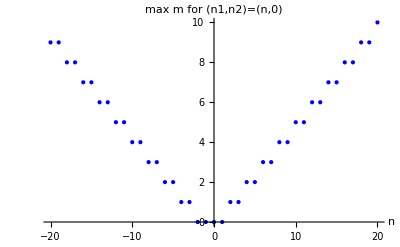

```mathematica
Mmax=50;ListPlot[Table[{n1,Max[FindTruncation[n1,0,Mmax][[1]]]},{n1,-20,20}],PlotStyle->{Blue,PointSize[Medium]},AxesLabel->{"n","max m for (n1,n2)=(n,0)"},PlotRange->All]
```

```mathematica
Do[
Print[FindTruncation[n1,0,20]]
,{n1,-10,10}];
```

#### h=1 -> JKRes

```mathematica
(* The integrand for h=1 *)
m=.;n1=.;n2=.;h=1;
ZSU2h1 = ZSU2
```

-1/2 ⅈ ((ⅈ Eta)/Theta1[1])^-n2 ((ⅈ Eta)/Theta1[1/f])^-n1 ((ⅈ Eta)/Theta1[f])^(1+n1+n2) ((ⅈ Eta)/Theta1[1/x^2])^(-2 m-n2) Theta1[1/x^2] ((ⅈ Eta)/Theta1[1/(f x^2)])^(-2 m-n1) ((ⅈ Eta)/Theta1[f/x^2])^(1-2 m+n1+n2) ((ⅈ Eta)/Theta1[x^2])^(2 m-n2) Theta1[x^2] ((ⅈ Eta)/Theta1[x^2/f])^(2 m-n1) ((ⅈ Eta)/Theta1[f x^2])^(1+2 m+n1+n2)

We see a divergence coming from the Theta1[1/h] term. Setting n2=0 we can avoid this temporarily.

```mathematica
n2=0;
ZSU2h1
```

-1/2 ⅈ ((ⅈ Eta)/Theta1[1/f])^-n1 ((ⅈ Eta)/Theta1[f])^(1+n1) ((ⅈ Eta)/Theta1[1/x^2])^(-2 m) Theta1[1/x^2] ((ⅈ Eta)/Theta1[1/(f x^2)])^(-2 m-n1) ((ⅈ Eta)/Theta1[f/x^2])^(1-2 m+n1) ((ⅈ Eta)/Theta1[x^2])^(2 m) Theta1[x^2] ((ⅈ Eta)/Theta1[x^2/f])^(2 m-n1) ((ⅈ Eta)/Theta1[f x^2])^(1+2 m+n1)

But now simplify the expression, and we get rid of the m dependence (this also works for n2!=0)

```mathematica
ZSU2h1Simple=Simplify[(ZSU2h1/.{Theta1[1/(f*(x_)^2)]->-Theta1[f*x^2],Theta1[1/f]->-Theta1[f],Theta1[1/(x_)^2]->-Theta1[x^2],Theta1[f/(x_)^2]->-Theta1[x^2/f]}),Assumptions->m∈Integers&&n1∈Integers&&n2∈Integers]
```

-((-1)^n1 Eta^3 Theta1[x^2]^2)/(2 Theta1[f] Theta1[x^2/f] Theta1[f x^2])

Which implies an infinite sum of a finite value. This is shady as all powers of x are now positive, think about the JKRes prescription which cares about the Q vectors: it seems like we can always shift all Q vectors to be positive and choose a negative eta, and we will always get 0. This doesn’t seem right. 
Let’s try taking the JKRes without the replacements above. For this to be possible let’s take n1=0 and thus need only m=0 NAIVELY.

```mathematica
n1=0;n2=0;
{Listm,singPts}=FindTruncation[n1,n2,Mmax];
singPts=singPts/.Subscript[v, 2]->0;
{Listm, singPts}
m=0;
ZSU2h1
```

{{0},{{v_1/2,1/2 (-τ+v_1),1/2 (-1+v_1),1/2 (-1-τ+v_1)}}}

-(Eta^3 Theta1[1/x^2] Theta1[x^2])/(2 Theta1[f] Theta1[f/x^2] Theta1[f x^2])

```mathematica
n1=0;
(* Choosing positive *)
Res=0;
Do[
Ztemp=Evaluate[((ZSU2h1/.{x->x*(-1)^a(√q)^b(√f)^-1})/.replacementRule)];
Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule;
Res=Res+SimpleResidue[Ztemp,x];
,{a,{0,1}},{b,{0,1}}]
Res/.replacementRule
(* Choosing negative *)
Res=0;
Do[
Ztemp=Evaluate[((ZSU2h1/.{x->x*(-1)^a(√q)^b(√f)^1})/.replacementRule)];
Ztemp=(-1/2 Ztemp/.x->x^(-1/2))/.replacementRule;
Res=Res-SimpleResidue[Ztemp,x];
,{a,{0,1}},{b,{0,1}}]
Res/.replacementRule
```

-Theta1[1/f]/(2 π Theta1[f^2])

-Theta1[1/f]/(2 π Theta1[f^2])

We got an answer, but does the series actually truncate for other m? Let’s check, try taking the JKRes of:

```mathematica
n1=0;n2=0;m=1;
ZSU2h1
```

-(Eta^3 Theta1[1/x^2]^3 Theta1[1/(f x^2)]^2 Theta1[f/x^2])/(2 Theta1[f] Theta1[x^2] Theta1[x^2/f]^2 Theta1[f x^2]^3)

Contains higher order terms :( need to use ContourInt. m>0 -> smart choice is u<0. Lets check both u<0 choice and u>0 choice.

```mathematica
Nmax=1;
```

```mathematica
(* Choosing positive x *)

(*Theta1[f x^2]^3*)
Res=0;
Ztemp=Evaluate[((ZSU2h1/.{x->x*(√f)^-1})/.replacementRule)];
Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule;
Res= Res+ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2h1/.{x->x*(√f)^-1(-1)})/.replacementRule)];
Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule;
Res= Res+ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2h1/.{x->x*(√f)^-1 √q})/.replacementRule)];
Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule;
Res= Res+ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2h1/.{x->x*(√f)^-1 √q(-1)})/.replacementRule)];
Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule;
Res1= Res+ContourInt[Ztemp//qForm//qExpand,x];

Res=0;
Ztemp=Evaluate[((ZSU2h1/.{x->x*(√f)})/.replacementRule)];
Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule;
Res= Res+ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2h1/.{x->x*(√f)(-1)})/.replacementRule)];
Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule;
Res= Res+ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2h1/.{x->x*(√f)√q})/.replacementRule)];
Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule;
Res= Res+ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2h1/.{x->x*(√f)√q(-1)})/.replacementRule)];
Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule;
Res2= Res+ContourInt[Ztemp//qForm//qExpand,x];

Res=0;
Ztemp=Evaluate[((ZSU2h1/.{x->x})/.replacementRule)];
Ztemp=(1/2 ZSU2h1/.x->x^(1/2))/.replacementRule;
Res= Res+ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2h1/.{x->x*(-1)})/.replacementRule)];
Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule;
Res= Res+ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2h1/.{x->x*√q})/.replacementRule)];
Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule;
Res= Res+ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2h1/.{x->x*√q(-1)})/.replacementRule)];
Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule;
Res= Res+ContourInt[Ztemp//qForm//qExpand,x];
Res3 = Res;

Res1
Res2
Res3
Print["Final result is: ",Res1 + Res2 + Res3]
```

(ⅈ (f^2+q-f q-f^3 q+f^4 q))/(f^(3/2) (1+f))

-(ⅈ (f^2+q-f q-f^3 q+f^4 q))/(f^(3/2) (1+f))

0

Final result is: 0

```mathematica
(* Choosing negative x *)

Res=0;
Ztemp=Evaluate[((ZSU2h1/.{x->x*(√f)^-1})/.replacementRule)];
Ztemp=(-1/2 Ztemp/.x->x^(-1/2))/.replacementRule;
Res= Res-ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2h1/.{x->x*(√f)^-1(-1)})/.replacementRule)];
Ztemp=(-1/2 Ztemp/.x->x^(-1/2))/.replacementRule;
Res= Res-ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2h1/.{x->x*(√f)^-1 √q})/.replacementRule)];
Ztemp=(-1/2 Ztemp/.x->x^(-1/2))/.replacementRule;
Res= Res-ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2h1/.{x->x*(√f)^-1 √q(-1)})/.replacementRule)];
Ztemp=(-1/2 Ztemp/.x->x^(-1/2))/.replacementRule;
Res1= Res-ContourInt[Ztemp//qForm//qExpand,x];

Res=0;
Ztemp=Evaluate[((ZSU2h1/.{x->x*(√f)})/.replacementRule)];
Ztemp=(-1/2 Ztemp/.x->x^(-1/2))/.replacementRule;
Res= Res-ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2h1/.{x->x*(√f)(-1)})/.replacementRule)];
Ztemp=(-1/2 Ztemp/.x->x^(-1/2))/.replacementRule;
Res= Res-ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2h1/.{x->x*(√f)√q})/.replacementRule)];
Ztemp=(-1/2 Ztemp/.x->x^(-1/2))/.replacementRule;
Res= Res-ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2h1/.{x->x*(√f)√q(-1)})/.replacementRule)];
Ztemp=(-1/2 Ztemp/.x->x^(-1/2))/.replacementRule;
Res2= Res-ContourInt[Ztemp//qForm//qExpand,x];

Res=0;
Ztemp=Evaluate[((ZSU2h1/.{x->x})/.replacementRule)];
Ztemp=(-1/2 Ztemp/.x->x^(-1/2))/.replacementRule;
Res= Res-ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2h1/.{x->x*(-1)})/.replacementRule)];
Ztemp=(-1/2 Ztemp/.x->x^(-1/2))/.replacementRule;
Res= Res-ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2h1/.{x->x*√q})/.replacementRule)];
Ztemp=(-1/2 Ztemp/.x->x^(-1/2))/.replacementRule;
Res= Res-ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2h1/.{x->x*√q(-1)})/.replacementRule)];
Ztemp=(-1/2 Ztemp/.x->x^(-1/2))/.replacementRule;
Res= Res-ContourInt[Ztemp//qForm//qExpand,x];
Res3 = Res;

Res1
Res2
Res3
Print["Final result is: ",Res1 + Res2 + Res3]
```

-(ⅈ (f^2+q-f q-f^3 q+f^4 q))/(f^(3/2) (1+f))

(ⅈ (f^2+q-f q-f^3 q+f^4 q))/(f^(3/2) (1+f))

0

Final result is: 0

We see that for m=1 we get 0 for both choices of charge. Might be good to check also for m=-1. 

Finally, let’s switch the order of operations.

#### JKRes -> h=1

```mathematica
n1=.;n2=.;m=.;h=.;f=.;
ZSU2
```

-1/2 ⅈ ((ⅈ Eta)/Theta1[1/f])^-n1 ((ⅈ Eta)/Theta1[1/h])^-n2 ((ⅈ Eta)/Theta1[f h])^(1+n1+n2) Theta1[1/x^2] ((ⅈ Eta)/Theta1[1/(f x^2)])^(-2 m-n1) ((ⅈ Eta)/Theta1[1/(h x^2)])^(-2 m-n2) ((ⅈ Eta)/Theta1[(f h)/x^2])^(1-2 m+n1+n2) Theta1[x^2] ((ⅈ Eta)/Theta1[x^2/f])^(2 m-n1) ((ⅈ Eta)/Theta1[x^2/h])^(2 m-n2) ((ⅈ Eta)/Theta1[f h x^2])^(1+2 m+n1+n2)

Let’s start immediately with n1=n2=0

```mathematica
n1=0;n2=0;
ZSU2
```

1/(2 Theta1[f h])Eta Theta1[1/x^2] ((ⅈ Eta)/Theta1[1/(f x^2)])^(-2 m) ((ⅈ Eta)/Theta1[1/(h x^2)])^(-2 m) ((ⅈ Eta)/Theta1[(f h)/x^2])^(1-2 m) Theta1[x^2] ((ⅈ Eta)/Theta1[x^2/f])^(2 m) ((ⅈ Eta)/Theta1[x^2/h])^(2 m) ((ⅈ Eta)/Theta1[f h x^2])^(1+2 m)

```mathematica
n1=0;n2=0;
{Listm,singPts}=FindTruncation[n1,n2,Mmax];
singPts=singPts;
{Listm, singPts}
```

{{0},{{1/2 (v_1+v_2),1/2 (-τ+v_1+v_2),1/2 (-1+v_1+v_2),1/2 (-1-τ+v_1+v_2)}}}

```mathematica
letterDict=<|Subscript[v, 1]->f,Subscript[v, 2]->h,u->x,τ->q|>;
singPtList=LetterExp[singPts[[1]]];
m=0;
Res=0;
ResQ=0;
Do[
Ztemp=Evaluate[((ZSU2/.x->x*singPtList[[i]])/.replacementRule)];
Res=Res-SimpleResidue[-1/2 Ztemp/.x->x^(-1/2),x];
,{i,1,Length[singPtList]}]
Res
```

-Theta1[1/(f h)]/(2 π Theta1[f^2 h^2])

We got the same result, good :) Let’s check m=1 is zero:

```mathematica
m=1;
ZSU2
```

-(Eta^3 Theta1[1/x^2] Theta1[1/(f x^2)]^2 Theta1[1/(h x^2)]^2 Theta1[(f h)/x^2] Theta1[x^2])/(2 Theta1[f h] Theta1[x^2/f]^2 Theta1[x^2/h]^2 Theta1[f h x^2]^3)

High order, need ContourInt. Note something weird - the positive u have the Theta1[f h x^2]^3 which is order 3, while negative u don’t have that.

```mathematica
(* choose positive *)
Nmax=0;

(*Theta1[x^2/f]^2*)
Res=0;
Ztemp=Evaluate[((ZSU2/.{x->x*(√f)})/.replacementRule)];
Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule;
Res= Res+ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2/.{x->x*(√f)(-1)})/.replacementRule)];
Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule;
Res= Res+ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2/.{x->x*(√f)√q})/.replacementRule)];
Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule;
Res= Res+ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2/.{x->x*(√f)√q(-1)})/.replacementRule)];
Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule;
Res1= Res+ContourInt[Ztemp//qForm//qExpand,x];

(*Theta1[x^2/h]^2 *)
Res=0;
Ztemp=Evaluate[((ZSU2/.{x->x*(√h)})/.replacementRule)];
Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule;
Res= Res+ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2/.{x->x*(√h)(-1)})/.replacementRule)];
Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule;
Res= Res+ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2/.{x->x*(√h)√q})/.replacementRule)];
Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule;
Res= Res+ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2/.{x->x*(√h)√q(-1)})/.replacementRule)];
Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule;
Res2= Res+ContourInt[Ztemp//qForm//qExpand,x];

(*Theta1[f h x^2]^3*)
Res=0;
Ztemp=Evaluate[((ZSU2/.{x->x*(√f √h)^-1})/.replacementRule)];
Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule;
Res= Res+ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2/.{x->x*(√f √h)^-1(-1)})/.replacementRule)];
Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule;
Res= Res+ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2/.{x->x*(√f √h)^-1 √q})/.replacementRule)];
Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule;
Res= Res+ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2/.{x->x*(√f √h)^-1 √q(-1)})/.replacementRule)];
Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule;
Res3= Res+ContourInt[Ztemp//qForm//qExpand,x];
```

```mathematica
Res = (Res1 + Res2 + Res3)//Simplify
```

0

We see m=1 gives zero for u>0. This is actually the “wrong” choice, so awesome we got 0. For completeness let’s check the obvious case u<0.

```mathematica
(* choose negative *)
Nmax=0;

(*Theta1[1/x^2] Theta1[1/(f x^2)]^2 Theta1[1/(h x^2)]^2 Theta1[(f h)/x^2]*)
(* Theta1[1/(f x^2)]^2*)
Res=0;
Ztemp=Evaluate[((ZSU2/.{x->x*(√f)^-1})/.replacementRule)];
Ztemp=(-1/2 Ztemp/.x->x^(-1/2))/.replacementRule;
Res= Res-ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2/.{x->x*(√f)^-1(-1)})/.replacementRule)];
Ztemp=(-1/2 Ztemp/.x->x^(-1/2))/.replacementRule;
Res= Res-ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2/.{x->x*(√f)^-1 √q})/.replacementRule)];
Ztemp=(-1/2 Ztemp/.x->x^(-1/2))/.replacementRule;
Res= Res-ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2/.{x->x*(√f)^-1 √q(-1)})/.replacementRule)];
Ztemp=(-1/2 Ztemp/.x->x^(-1/2))/.replacementRule;
Res1= Res-ContourInt[Ztemp//qForm//qExpand,x];

(*Theta1[1/(h x^2)]^2 *)
Res=0;
Ztemp=Evaluate[((ZSU2/.{x->x*(√h)^-1})/.replacementRule)];
Ztemp=(-1/2 Ztemp/.x->x^(-1/2))/.replacementRule;
Res= Res-ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2/.{x->x*(√h)^-1(-1)})/.replacementRule)];
Ztemp=(-1/2 Ztemp/.x->x^(-1/2))/.replacementRule;
Res= Res-ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2/.{x->x*(√h)^-1 √q})/.replacementRule)];
Ztemp=(-1/2 Ztemp/.x->x^(-1/2))/.replacementRule;
Res= Res-ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2/.{x->x*(√h)^-1 √q(-1)})/.replacementRule)];
Ztemp=(-1/2 Ztemp/.x->x^(-1/2))/.replacementRule;
Res2= Res-ContourInt[Ztemp//qForm//qExpand,x];

(*Theta1[(f h)/x^2]*)
Res=0;
Ztemp=Evaluate[((ZSU2/.{x->x*(√f √h)})/.replacementRule)];
Ztemp=(-1/2 Ztemp/.x->x^(-1/2))/.replacementRule;
Res= Res-ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2/.{x->x*(√f √h)(-1)})/.replacementRule)];
Ztemp=(-1/2 Ztemp/.x->x^(-1/2))/.replacementRule;
Res= Res-ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2/.{x->x*(√f √h)√q})/.replacementRule)];
Ztemp=(-1/2 Ztemp/.x->x^(-1/2))/.replacementRule;
Res= Res-ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2/.{x->x*(√f √h)√q(-1)})/.replacementRule)];
Ztemp=(-1/2 Ztemp/.x->x^(-1/2))/.replacementRule;
Res3= Res-ContourInt[Ztemp//qForm//qExpand,x];

(*Theta1[1/x^2]*)
Res=0;
Ztemp=(-1/2 ZSU2/.x->x^(-1/2))/.replacementRule;
Res= Res-ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2/.{x->x*(-1)})/.replacementRule)];
Ztemp=(-1/2 Ztemp/.x->x^(-1/2))/.replacementRule;
Res= Res-ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2/.{x->x*√q})/.replacementRule)];
Ztemp=(-1/2 Ztemp/.x->x^(-1/2))/.replacementRule;
Res= Res-ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2/.{x->x*√q(-1)})/.replacementRule)];
Ztemp=(-1/2 Ztemp/.x->x^(-1/2))/.replacementRule;
Res4= Res-ContourInt[Ztemp//qForm//qExpand,x];
```

```mathematica
Res=Res1+Res2+Res3+Res4
```

0

We saw that for both cases, m=1 gives 0.

#### Modular transformation

```mathematica
?Θ
```

```mathematica
Nmax=1;
Theta1[Exp[2*π*ⅈ*u/τ],Exp[-1/τ]]//Simplify
```

-ⅈ ⅇ^(-(7 (9+2 ⅈ π u))/τ) (ⅇ^(-1/τ))^(1/8) √(ⅇ^((2 ⅈ π u)/τ)) (-1+ⅇ^(1/τ))^6 (1+ⅇ^(1/τ))^3 (1+ⅇ^(2/τ)) (1-ⅇ^(1/τ)+ⅇ^(2/τ)) (1+ⅇ^(1/τ)+ⅇ^(2/τ))^2 (1+ⅇ^(1/τ)+ⅇ^(2/τ)+ⅇ^(3/τ)+ⅇ^(4/τ)) (ⅇ^(1/τ)-ⅇ^((2 ⅈ π u)/τ)) (ⅇ^(2/τ)-ⅇ^((2 ⅈ π u)/τ)) (ⅇ^(3/τ)-ⅇ^((2 ⅈ π u)/τ)) (ⅇ^(4/τ)-ⅇ^((2 ⅈ π u)/τ)) (ⅇ^(5/τ)-ⅇ^((2 ⅈ π u)/τ)) (ⅇ^(6/τ)-ⅇ^((2 ⅈ π u)/τ)) (-1+ⅇ^((2 ⅈ π u)/τ)) (-1+ⅇ^((1+2 ⅈ π u)/τ)) (-1+ⅇ^((2+2 ⅈ π u)/τ)) (-1+ⅇ^((3+2 ⅈ π u)/τ)) (-1+ⅇ^((4+2 ⅈ π u)/τ)) (-1+ⅇ^((5+2 ⅈ π u)/τ)) (-1+ⅇ^((6+2 ⅈ π u)/τ))

```mathematica
-ⅈ*√(-ⅈ*τ)*ⅇ^(π*ⅈ*u^2/τ)*Theta1[Exp[2*π*ⅈ*u],Exp[τ]]//Simplify
```

-ⅇ^((ⅈ π u (u-14 τ))/τ) √(ⅇ^(2 ⅈ π u)) (ⅇ^τ)^(1/8) (-1+ⅇ^(2 ⅈ π u)) (ⅇ^(2 ⅈ π u)-ⅇ^τ) (-1+ⅇ^τ)^6 (1+ⅇ^τ)^3 (ⅇ^(2 ⅈ π u)-ⅇ^(2 τ)) (1+ⅇ^(2 τ)) (1-ⅇ^τ+ⅇ^(2 τ)) (1+ⅇ^τ+ⅇ^(2 τ))^2 (ⅇ^(2 ⅈ π u)-ⅇ^(3 τ)) (ⅇ^(2 ⅈ π u)-ⅇ^(4 τ)) (1+ⅇ^τ+ⅇ^(2 τ)+ⅇ^(3 τ)+ⅇ^(4 τ)) (ⅇ^(2 ⅈ π u)-ⅇ^(5 τ)) (ⅇ^(2 ⅈ π u)-ⅇ^(6 τ)) (-1+ⅇ^(2 ⅈ π u+τ)) (-1+ⅇ^(2 ⅈ π u+2 τ)) (-1+ⅇ^(2 ⅈ π u+3 τ)) (-1+ⅇ^(2 ⅈ π u+4 τ)) (-1+ⅇ^(2 ⅈ π u+5 τ)) (-1+ⅇ^(2 ⅈ π u+6 τ)) √(-ⅈ τ)

#### Old code

```mathematica
(* Choosing positive *)
Nmax=0;
Res=0;
Do[
Ztemp=Evaluate[((ZSU2h1/.{x->x*(-1)^a(√q)^b(√f)^-1})/.replacementRule)];
Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule;
Res=Res+ContourInt[Ztemp//qForm//qExpand,x];
,{a,0,1},{b,0,1}]
Res/.replacementRule
```

Series::fas: Warning: one or more assumptions evaluated to False.

$Assumptions::fas: Warning: one or more assumptions evaluated to False.

(ⅈ √f)/(2 (1+f))+(ⅈ √(1/f) √(f^2))/(2 (1+f))

```mathematica
n1=0;n2=0;m=0;Mmax=50;
{Listm,singPts}=FindTruncation[n1,n2,Mmax];
```

Setting h to 1:

```mathematica
ZSU2/.h->1
```

-(Eta^3 Theta1[1/x^2] Theta1[x^2])/(2 Theta1[f] Theta1[f/x^2] Theta1[f x^2])

```mathematica
ZSU2h=-1/(2 Theta1[f])Eta   ((ⅈ Eta)/Theta1[x^2/f])(Theta1[x^2])^2((ⅈ Eta)/Theta1[f x^2])
```

(Eta^3 Theta1[x^2]^2)/(2 Theta1[f] Theta1[x^2/f] Theta1[f x^2])

```mathematica
Res=0;
Do[
Ztemp=Evaluate[((ZSU2h/.{x->x*(-1)^a(√q)^b(√f)})/.replacementRule)];
Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule;
Res=Res+SimpleResidue[Ztemp,x];
,{a,{0,1}},{b,{0,1}}]
Res/.replacementRule
```

Theta1[f]/(2 π Theta1[f^2])

```mathematica
letterDict=<|Subscript[v, 1]->f,Subscript[v, 2]->h,u->x,τ->q|>;
singPtList=LetterExp[singPts[[1]]]
Nmax=0;
Res=0;
ResQ=0;
Do[
Ztemp=Evaluate[((ZSU2/.x->x*singPtList[[i]])/.replacementRule)];
Res=Res+SimpleResidue[-1/2 Ztemp/.x->x^(-1/2),x];
ResQ=ResQ+1/(2π*ⅈ)ContourInt[Ztemp//qForm,x];
,{i,1,Length[singPtList]}]
```

{√f √h,(√f √h)/(√q),-√f √h,-(√f √h)/(√q)}

```mathematica
Res
```

(Theta1[1]^2 Theta1[1/(f h^2)]^2 Theta1[1/(f^2 h)]^2 Theta1[1/(f h)])/(2 π Theta1[f]^2 Theta1[h]^2 Theta1[f^2 h^2]^3)

```mathematica
Res/.h->1
```

(Theta1[1/f^2]^2 Theta1[1/f]^3)/(2 π Theta1[f]^2 Theta1[f^2]^3)

```mathematica
(ResQ//qExpand//Simplify//qExpand)/.h->1
```

((-1+f) √f (1-2 f^2+f^4))/(2 (-1+f^2)^3 π)

```mathematica
Res//qForm//qExpand//Simplify//qExpand
ResQ//qExpand//Simplify//qExpand
```

Consistency check: check the JK residue for m=1 and choosing positive poles:

```mathematica
ZSU2
```

-((Eta^3 Theta1[1/x^2] Theta1[1/(f x^2)]^2 Theta1[1/(h x^2)]^2 Theta1[(f h)/x^2] Theta1[x^2])/(2 Theta1[f h] Theta1[x^2/f]^2 Theta1[x^2/h]^2 Theta1[f h x^2]^3))

```mathematica
singPtList={√f ,-√f,√f(√q)^-1,-√f(√q)^-1,√h ,-√h,√h(√q)^-1,-√h(√q)^-1,(√(f*h))^-1 ,-(√(f*h))^-1,(√(f*h))^-1(√q)^-1,-(√(f*h))^-1(√q)^-1}
```

{√f,-√f,(√f)/(√q),-(√f)/(√q),√h,-√h,(√h)/(√q),-(√h)/(√q),1/(√(f h)),-1/(√(f h)),1/(√(f h) √q),-1/(√(f h) √q)}

```mathematica
ZSU2
```

-((Eta^3 Theta1[1/x^2] Theta1[1/(f x^2)]^2 Theta1[1/(h x^2)]^2 Theta1[(f h)/x^2] Theta1[x^2])/(2 Theta1[f h] Theta1[x^2/f]^2 Theta1[x^2/h]^2 Theta1[f h x^2]^3))

```mathematica
SimpleResidue[1/Theta1[z*μ]/.z->z*μ^-1,z]
```

1/(2 Eta^3 π)

```mathematica
m=1;
Ztest=(1/Theta1[z*μ])^m(1/Theta1[z^-1*μ])^-m
```

Theta1[μ/z]/Theta1[z μ]

```mathematica
SimpleResidue[Ztest/.z->z*μ^-1,z]
```

Theta1[μ^2]/(2 Eta^3 π)

```mathematica
Nmax=0;
Res={};
Do[
Print["i=",i];
Ztemp=Evaluate[((ZSU2/.x->x*singPtList[[i]])/.replacementRule)];
Ztemp=1/2 Ztemp/.x->x^(1/2);
Print[Ztemp//qForm];
ResTemp=1/(2π*ⅈ)ContourInt[Ztemp//qForm,x]//qExpand//Simplify//qExpand;
Print[ResTemp];
AppendTo[Res,ResTemp];
,{i,1,Length[singPtList]}]
```

i=1

(ⅈ (1-1/(f x)) √(1/(f x)) √(h/x) √(f x) (-1+f x) (-1+f^2 x)^2 (1-x/h) (-1+f h x)^2)/(4 f^4 (1-1/(f h)) √(f h) (1-1/(f^2 h x))^3 (1-h/(f x))^2 (-1+x)^2 x^2 (f^2 h x)^(3/2))

-1/(8 (f-h)^3 (-1+f^2 h)^4 π)(-1+f)^3 √f (1+f) h^(3/2) (h^2+f^6 h^2+f^2 (2-6 h+9 h^2-6 h^3)+f (2-5 h+h^3)+f^4 h (-6+9 h-6 h^2+2 h^3)+2 f^3 (1-4 h+8 h^2-4 h^3+h^4)+f^5 (h-5 h^3+2 h^4))

i=2

(ⅈ (1-1/(f x)) √(1/(f x)) √(h/x) √(f x) (-1+f x) (-1+f^2 x)^2 (1-x/h) (-1+f h x)^2)/(4 f^4 (1-1/(f h)) √(f h) (1-1/(f^2 h x))^3 (1-h/(f x))^2 (-1+x)^2 x^2 (f^2 h x)^(3/2))

-1/(8 (f-h)^3 (-1+f^2 h)^4 π)(-1+f)^3 √f (1+f) h^(3/2) (h^2+f^6 h^2+f^2 (2-6 h+9 h^2-6 h^3)+f (2-5 h+h^3)+f^4 h (-6+9 h-6 h^2+2 h^3)+2 f^3 (1-4 h+8 h^2-4 h^3+h^4)+f^5 (h-5 h^3+2 h^4))

i=3

(ⅈ (1-1/(f x)) √(1/(f x)) √(h/x) √(f x) (-1+f x) (-1+f^2 x)^2 (1-x/h) (-1+f h x)^2)/(4 f^4 (1-1/(f h)) √(f h) (1-1/(f^2 h x))^3 (1-h/(f x))^2 (-1+x)^2 x^2 (f^2 h x)^(3/2))

-1/(8 (f-h)^3 (-1+f^2 h)^4 π)(-1+f)^3 √f (1+f) h^(3/2) (h^2+f^6 h^2+f^2 (2-6 h+9 h^2-6 h^3)+f (2-5 h+h^3)+f^4 h (-6+9 h-6 h^2+2 h^3)+2 f^3 (1-4 h+8 h^2-4 h^3+h^4)+f^5 (h-5 h^3+2 h^4))

i=4

(ⅈ (1-1/(f x)) √(1/(f x)) √(h/x) √(f x) (-1+f x) (-1+f^2 x)^2 (1-x/h) (-1+f h x)^2)/(4 f^4 (1-1/(f h)) √(f h) (1-1/(f^2 h x))^3 (1-h/(f x))^2 (-1+x)^2 x^2 (f^2 h x)^(3/2))

-1/(8 (f-h)^3 (-1+f^2 h)^4 π)(-1+f)^3 √f (1+f) h^(3/2) (h^2+f^6 h^2+f^2 (2-6 h+9 h^2-6 h^3)+f (2-5 h+h^3)+f^4 h (-6+9 h-6 h^2+2 h^3)+2 f^3 (1-4 h+8 h^2-4 h^3+h^4)+f^5 (h-5 h^3+2 h^4))

i=5

(ⅈ (1-1/(h x)) √(f/x) √(1/(h x)) √(h x) (1-x/f) (-1+h x) (-1+f h x)^2 (-1+h^2 x)^2)/(4 (1-1/(f h)) h^4 √(f h) (1-1/(f h^2 x))^3 (1-f/(h x))^2 (-1+x)^2 x^2 (f h^2 x)^(3/2))

1/(8 (f-h)^3 (-1+f h^2)^4 π)f^(3/2) (-1+h)^3 √h (1+h) (2 h (1+h+h^2)+2 f^4 h^3 (1+h+h^2)+f h (-5-6 h-8 h^2-6 h^3+h^4)-f^3 h (-1+6 h+8 h^2+6 h^3+5 h^4)+f^2 (1+9 h^2+16 h^3+9 h^4+h^6))

i=6

(ⅈ (1-1/(h x)) √(f/x) √(1/(h x)) √(h x) (1-x/f) (-1+h x) (-1+f h x)^2 (-1+h^2 x)^2)/(4 (1-1/(f h)) h^4 √(f h) (1-1/(f h^2 x))^3 (1-f/(h x))^2 (-1+x)^2 x^2 (f h^2 x)^(3/2))

1/(8 (f-h)^3 (-1+f h^2)^4 π)f^(3/2) (-1+h)^3 √h (1+h) (2 h (1+h+h^2)+2 f^4 h^3 (1+h+h^2)+f h (-5-6 h-8 h^2-6 h^3+h^4)-f^3 h (-1+6 h+8 h^2+6 h^3+5 h^4)+f^2 (1+9 h^2+16 h^3+9 h^4+h^6))

i=7

(ⅈ (1-1/(h x)) √(f/x) √(1/(h x)) √(h x) (1-x/f) (-1+h x) (-1+f h x)^2 (-1+h^2 x)^2)/(4 (1-1/(f h)) h^4 √(f h) (1-1/(f h^2 x))^3 (1-f/(h x))^2 (-1+x)^2 x^2 (f h^2 x)^(3/2))

1/(8 (f-h)^3 (-1+f h^2)^4 π)f^(3/2) (-1+h)^3 √h (1+h) (2 h (1+h+h^2)+2 f^4 h^3 (1+h+h^2)+f h (-5-6 h-8 h^2-6 h^3+h^4)-f^3 h (-1+6 h+8 h^2+6 h^3+5 h^4)+f^2 (1+9 h^2+16 h^3+9 h^4+h^6))

i=8

(ⅈ (1-1/(h x)) √(f/x) √(1/(h x)) √(h x) (1-x/f) (-1+h x) (-1+f h x)^2 (-1+h^2 x)^2)/(4 (1-1/(f h)) h^4 √(f h) (1-1/(f h^2 x))^3 (1-f/(h x))^2 (-1+x)^2 x^2 (f h^2 x)^(3/2))

1/(8 (f-h)^3 (-1+f h^2)^4 π)f^(3/2) (-1+h)^3 √h (1+h) (2 h (1+h+h^2)+2 f^4 h^3 (1+h+h^2)+f h (-5-6 h-8 h^2-6 h^3+h^4)-f^3 h (-1+6 h+8 h^2+6 h^3+5 h^4)+f^2 (1+9 h^2+16 h^3+9 h^4+h^6))

i=9

-(ⅈ f^4 h^4 (1-(f h)/x) √((f h)/x) √((f^2 h^2)/x) √(x/(f h)) (1-x/f)^2 (1-x/(f^2 h^2)) (1-x/h)^2 (1-x/(f h)))/(4 (1-1/(f h)) √(f h) (1-(f^2 h)/x)^2 (1-(f h^2)/x)^2 (-1+x)^3 x^(5/2))

1/(8 (-1+f^2 h)^4 (-1+f h^2)^4 π)√(f h) (1+f^11 h^11+f^10 h^7 (2-2 h-6 h^2+h^3)+f h (1-6 h-2 h^2+2 h^3)+f^9 h^5 (1-8 h+10 h^2+14 h^3-4 h^4-6 h^5)+f^2 h (-6-4 h+14 h^2+10 h^3-8 h^4+h^5)+f^8 h^4 (1-6 h+10 h^2-28 h^3+16 h^4+14 h^5-2 h^6)+f^3 h (-2+14 h+16 h^2-28 h^3+10 h^4-6 h^5+h^6)+f^4 h (2+10 h-28 h^2+21 h^3-58 h^4+38 h^5-8 h^6+h^7)+f^5 h^2 (-8+10 h-58 h^2+105 h^3-68 h^4+38 h^5-6 h^6+h^7)+f^7 h^3 (1-8 h+38 h^2-58 h^3+21 h^4-28 h^5+10 h^6+2 h^7)+f^6 (h^2-6 h^3+38 h^4-68 h^5+105 h^6-58 h^7+10 h^8-8 h^9))

i=10

-(ⅈ f^4 h^4 (1-(f h)/x) √((f h)/x) √((f^2 h^2)/x) √(x/(f h)) (1-x/f)^2 (1-x/(f^2 h^2)) (1-x/h)^2 (1-x/(f h)))/(4 (1-1/(f h)) √(f h) (1-(f^2 h)/x)^2 (1-(f h^2)/x)^2 (-1+x)^3 x^(5/2))

1/(8 (-1+f^2 h)^4 (-1+f h^2)^4 π)√(f h) (1+f^11 h^11+f^10 h^7 (2-2 h-6 h^2+h^3)+f h (1-6 h-2 h^2+2 h^3)+f^9 h^5 (1-8 h+10 h^2+14 h^3-4 h^4-6 h^5)+f^2 h (-6-4 h+14 h^2+10 h^3-8 h^4+h^5)+f^8 h^4 (1-6 h+10 h^2-28 h^3+16 h^4+14 h^5-2 h^6)+f^3 h (-2+14 h+16 h^2-28 h^3+10 h^4-6 h^5+h^6)+f^4 h (2+10 h-28 h^2+21 h^3-58 h^4+38 h^5-8 h^6+h^7)+f^5 h^2 (-8+10 h-58 h^2+105 h^3-68 h^4+38 h^5-6 h^6+h^7)+f^7 h^3 (1-8 h+38 h^2-58 h^3+21 h^4-28 h^5+10 h^6+2 h^7)+f^6 (h^2-6 h^3+38 h^4-68 h^5+105 h^6-58 h^7+10 h^8-8 h^9))

i=11

-(ⅈ f^4 h^4 (1-(f h)/x) √((f h)/x) √((f^2 h^2)/x) √(x/(f h)) (1-x/f)^2 (1-x/(f^2 h^2)) (1-x/h)^2 (1-x/(f h)))/(4 (1-1/(f h)) √(f h) (1-(f^2 h)/x)^2 (1-(f h^2)/x)^2 (-1+x)^3 x^(5/2))

1/(8 (-1+f^2 h)^4 (-1+f h^2)^4 π)√(f h) (1+f^11 h^11+f^10 h^7 (2-2 h-6 h^2+h^3)+f h (1-6 h-2 h^2+2 h^3)+f^9 h^5 (1-8 h+10 h^2+14 h^3-4 h^4-6 h^5)+f^2 h (-6-4 h+14 h^2+10 h^3-8 h^4+h^5)+f^8 h^4 (1-6 h+10 h^2-28 h^3+16 h^4+14 h^5-2 h^6)+f^3 h (-2+14 h+16 h^2-28 h^3+10 h^4-6 h^5+h^6)+f^4 h (2+10 h-28 h^2+21 h^3-58 h^4+38 h^5-8 h^6+h^7)+f^5 h^2 (-8+10 h-58 h^2+105 h^3-68 h^4+38 h^5-6 h^6+h^7)+f^7 h^3 (1-8 h+38 h^2-58 h^3+21 h^4-28 h^5+10 h^6+2 h^7)+f^6 (h^2-6 h^3+38 h^4-68 h^5+105 h^6-58 h^7+10 h^8-8 h^9))

i=12

-(ⅈ f^4 h^4 (1-(f h)/x) √((f h)/x) √((f^2 h^2)/x) √(x/(f h)) (1-x/f)^2 (1-x/(f^2 h^2)) (1-x/h)^2 (1-x/(f h)))/(4 (1-1/(f h)) √(f h) (1-(f^2 h)/x)^2 (1-(f h^2)/x)^2 (-1+x)^3 x^(5/2))

1/(8 (-1+f^2 h)^4 (-1+f h^2)^4 π)√(f h) (1+f^11 h^11+f^10 h^7 (2-2 h-6 h^2+h^3)+f h (1-6 h-2 h^2+2 h^3)+f^9 h^5 (1-8 h+10 h^2+14 h^3-4 h^4-6 h^5)+f^2 h (-6-4 h+14 h^2+10 h^3-8 h^4+h^5)+f^8 h^4 (1-6 h+10 h^2-28 h^3+16 h^4+14 h^5-2 h^6)+f^3 h (-2+14 h+16 h^2-28 h^3+10 h^4-6 h^5+h^6)+f^4 h (2+10 h-28 h^2+21 h^3-58 h^4+38 h^5-8 h^6+h^7)+f^5 h^2 (-8+10 h-58 h^2+105 h^3-68 h^4+38 h^5-6 h^6+h^7)+f^7 h^3 (1-8 h+38 h^2-58 h^3+21 h^4-28 h^5+10 h^6+2 h^7)+f^6 (h^2-6 h^3+38 h^4-68 h^5+105 h^6-58 h^7+10 h^8-8 h^9))

```mathematica
ResultList=4*Res[[{1,5,9}]]
```

{-(((-1+f)^3 √f (1+f) h^(3/2) (h^2+f^6 h^2+f^2 (2-6 h+9 h^2-6 h^3)+f (2-5 h+h^3)+f^4 h (-6+9 h-6 h^2+2 h^3)+2 f^3 (1-4 h+8 h^2-4 h^3+h^4)+f^5 (h-5 h^3+2 h^4)))/(2 (f-h)^3 (-1+f^2 h)^4 π)),(f^(3/2) (-1+h)^3 √h (1+h) (2 h (1+h+h^2)+2 f^4 h^3 (1+h+h^2)+f h (-5-6 h-8 h^2-6 h^3+h^4)-f^3 h (-1+6 h+8 h^2+6 h^3+5 h^4)+f^2 (1+9 h^2+16 h^3+9 h^4+h^6)))/(2 (f-h)^3 (-1+f h^2)^4 π),1/(2 (-1+f^2 h)^4 (-1+f h^2)^4 π)√(f h) (1+f^11 h^11+f^10 h^7 (2-2 h-6 h^2+h^3)+f h (1-6 h-2 h^2+2 h^3)+f^9 h^5 (1-8 h+10 h^2+14 h^3-4 h^4-6 h^5)+f^2 h (-6-4 h+14 h^2+10 h^3-8 h^4+h^5)+f^8 h^4 (1-6 h+10 h^2-28 h^3+16 h^4+14 h^5-2 h^6)+f^3 h (-2+14 h+16 h^2-28 h^3+10 h^4-6 h^5+h^6)+f^4 h (2+10 h-28 h^2+21 h^3-58 h^4+38 h^5-8 h^6+h^7)+f^5 h^2 (-8+10 h-58 h^2+105 h^3-68 h^4+38 h^5-6 h^6+h^7)+f^7 h^3 (1-8 h+38 h^2-58 h^3+21 h^4-28 h^5+10 h^6+2 h^7)+f^6 (h^2-6 h^3+38 h^4-68 h^5+105 h^6-58 h^7+10 h^8-8 h^9))}

```mathematica
ResultList[[1]]//Simplify
```

-(((-1+f)^3 √f (1+f) h^(3/2) (h^2+f^6 h^2+f^2 (2-6 h+9 h^2-6 h^3)+f (2-5 h+h^3)+f^4 h (-6+9 h-6 h^2+2 h^3)+2 f^3 (1-4 h+8 h^2-4 h^3+h^4)+f^5 (h-5 h^3+2 h^4)))/(2 (f-h)^3 (-1+f^2 h)^4 π))

```mathematica
ResultList[[1]]+ResultList[[2]]-ResultList[[3]]//Simplify
```

-1/((-1+f^2 h)^4 (-1+f h^2)^4 π)√(f h) (1+f^11 h^11+f^10 h^7 (2-2 h-6 h^2+h^3)+f h (1-6 h-2 h^2+2 h^3)+f^9 h^5 (1-8 h+10 h^2+14 h^3-4 h^4-6 h^5)+f^2 h (-6-4 h+14 h^2+10 h^3-8 h^4+h^5)+f^8 h^4 (1-6 h+10 h^2-28 h^3+16 h^4+14 h^5-2 h^6)+f^3 h (-2+14 h+16 h^2-28 h^3+10 h^4-6 h^5+h^6)+f^4 h (2+10 h-28 h^2+21 h^3-58 h^4+38 h^5-8 h^6+h^7)+f^5 h^2 (-8+10 h-58 h^2+105 h^3-68 h^4+38 h^5-6 h^6+h^7)+f^7 h^3 (1-8 h+38 h^2-58 h^3+21 h^4-28 h^5+10 h^6+2 h^7)+f^6 (h^2-6 h^3+38 h^4-68 h^5+105 h^6-58 h^7+10 h^8-8 h^9))

### General case

#### n1 = 0; n2 = 0;

```mathematica
n1=0;n2=0;m=0;
ZSU2=ZSU2PartitionFunction[n1,n2,m]
```

-(Eta^3 Theta1[1/x^2] Theta1[x^2])/(2 Theta1[f h] Theta1[(f h)/x^2] Theta1[f h x^2])

```mathematica
{mList,singPoints}=FindTruncation[n1,n2,Mmax];
```

```mathematica
Res=0;
Ztointegrate=0;
Do[
m=mList[[i]];
sign=SignSp[m];
singPtList=LetterExp[singPoints[[i]]];
Do[
Ztemp=ZSU2/.{x->x*pt};
Ztemp=-sign/2*Ztemp/.x->x^(-1/2*sign);
Ztemp=Ztemp/.replacementRule;
Ztointegrate=Ztointegrate-sign*Ztemp;
Res=Res-sign*SimpleResidue[Ztemp,x];
,{pt,singPtList}];
,{i,1,Length[mList]}]
```

```mathematica
Res=Res/.Theta1[1/(f*h)]->-Theta1[f*h]
```

Theta1[f h]/(2 π Theta1[f^2 h^2])

```mathematica
Ztointegrate
```

-(Eta^3 Theta1[(f h)/x] Theta1[x/(f h)])/(Theta1[f h] Theta1[(f^2 h^2)/x] Theta1[x])

```mathematica
letterDict
```

<|v_1→f,v_2→h,u→x,τ→q|>

```mathematica
LetterLog[x]
```

u

```mathematica
Nmax=5;
Zint=Residue[Ztointegrate/.{Theta1[arg_]:>Theta1Modular[LetterLog[arg],τ]},u];
ZintQ=Zint//qExpand;
```

```mathematica
ⅇ^(-3π*ⅈ/τ*(u+v)^2)Theta1Modular[u+v,τ]/Theta1Modular[2u+2v,τ]
Theta1Modular[u/τ+v/τ,-1/τ]/Theta1Modular[(2u)/τ+(2v)/τ,-1/τ]
```

0.00811063+0.306851 ⅈ

0.00811063+0.306851 ⅈ

```mathematica
τ=RandomComplex[];
Subscript[v, 1]=RandomComplex[];
Subscript[v, 2]=RandomComplex[];
ⅇ^(-3π*ⅈ/τ*(Subscript[v, 1]+Subscript[v, 2])^2)*ZintQ
ZintQ/.{f->ⅇ^(2*π*ⅈ*u/τ),h->ⅇ^(2*π*ⅈ*v/τ),q->ⅇ^(2*π*ⅈ*(-1/τ))}
```

6.74954×10^16+7.22754×10^16 ⅈ

-0.0168214-0.000607382 ⅈ

```mathematica
τ=.;
u=.;
v=.;
```

#### n1 = 0; n2 = 1;

```mathematica
n1=0;n2=1;
{mList,singPoints}=FindTruncation[n1,n2,Mmax];
mList
```

{0}

```mathematica
Ztointegrate=0;
Do[
m=mList[[i]];
ZSU2=ZSU2PartitionFunction[n1,n2,m];
sign=SignSp[m];
singPtList=LetterExp[singPoints[[i]]];
Do[
Ztemp=ZSU2/.{x->x*pt};
Ztemp=-sign/2*Ztemp/.x->x^(-1/2*sign);
Ztemp=Ztemp/.replacementRule;
Ztointegrate=Ztointegrate-sign*Ztemp;
,{pt,singPtList}];
,{i,1,Length[mList]}]
```

```mathematica
Ztointegrate
```

-(Eta^3 Theta1[1/h] Theta1[f/x] Theta1[(f h)/x] Theta1[x/(f h^2)] Theta1[x/(f h)])/(Theta1[f h]^2 Theta1[(f^2 h^2)/x]^2 Theta1[x]^2)

Final result:

```mathematica
Ztointegrate/.Theta1[(f h)/x]->-Theta1[x/(f*h)]
```

(Eta^3 Theta1[1/h] Theta1[f/x] Theta1[x/(f h^2)] Theta1[x/(f h)]^2)/(Theta1[f h]^2 Theta1[(f^2 h^2)/x]^2 Theta1[x]^2)

#### n1 = 0; n2 = 2;

```mathematica
n1=0;n2=2;
{mList,singPoints}=FindTruncation[n1,n2,Mmax];
mList
```

{-1,0,1}

```mathematica
Ztointegrate=0;
Do[
m=mList[[i]];
ZSU2=ZSU2PartitionFunction[n1,n2,m];
sign=SignSp[m];
singPtList=LetterExp[singPoints[[i]]];
Do[
Ztemp=ZSU2/.{x->x*pt};
Ztemp=-sign/2*Ztemp/.x->x^(-1/2*sign);
Ztemp=Ztemp/.replacementRule;
Ztointegrate=Ztointegrate-sign*Ztemp;
,{pt,singPtList}];
,{i,1,Length[mList]}]
```

```mathematica
Ztointegrate
```

-(Eta^3 Theta1[1/h]^2 Theta1[f/x]^2 Theta1[(f h)/x] Theta1[x/(f h^2)]^2 Theta1[x/(f h)])/(Theta1[f h]^3 Theta1[(f^2 h^2)/x]^3 Theta1[x]^3)-(2 Eta^3 Theta1[1/h]^2 Theta1[(f h)/x] Theta1[x/(f h^2)]^4 Theta1[x/(f^2 h)]^2 Theta1[x/(f h)])/(Theta1[f h]^3 Theta1[h/x]^2 Theta1[(f^2 h^2)/x]^5 Theta1[x])

Final result:

```mathematica
Ztointegrate=Ztointegrate/.Theta1[(f h)/x]->-Theta1[x/(f*h)]
```

(Eta^3 Theta1[1/h]^2 Theta1[f/x]^2 Theta1[x/(f h^2)]^2 Theta1[x/(f h)]^2)/(Theta1[f h]^3 Theta1[(f^2 h^2)/x]^3 Theta1[x]^3)+(2 Eta^3 Theta1[1/h]^2 Theta1[x/(f h^2)]^4 Theta1[x/(f^2 h)]^2 Theta1[x/(f h)]^2)/(Theta1[f h]^3 Theta1[h/x]^2 Theta1[(f^2 h^2)/x]^5 Theta1[x])

```mathematica
func=Ztointegrate[[2]]
```

(2 Eta^3 Theta1[1/h]^2 Theta1[x/(f h^2)]^4 Theta1[x/(f^2 h)]^2 Theta1[x/(f h)]^2)/(Theta1[f h]^3 Theta1[h/x]^2 Theta1[(f^2 h^2)/x]^5 Theta1[x])

```mathematica
Z4=(Eta^3 Theta1[1/h]^4 Theta1[f/x]^4 Theta1[x/(f h^2)]^4 Theta1[x/(f h)]^2)/(Theta1[f h]^5 Theta1[(f^2 h^2)/x]^5 Theta1[x]^5)+(2 Eta^3 Theta1[1/h]^4 Theta1[f/x]^2 Theta1[x/(f h^2)]^6 Theta1[x/(f^2 h)]^2 Theta1[x/(f h)]^2)/(Theta1[f h]^5 Theta1[h/x]^2 Theta1[(f^2 h^2)/x]^7 Theta1[x]^3)+(2 Eta^3 Theta1[1/h]^4 Theta1[x/(f h^2)]^8 Theta1[x/(f^2 h)]^4 Theta1[x/(f h)]^2)/(Theta1[f h]^5 Theta1[h/x]^4 Theta1[(f^2 h^2)/x]^9 Theta1[x]);
```

```mathematica
temp//Simplify
```

-3 (3 v_1^2+6 v_1 v_2+v_2^2)

```mathematica
ModularTransformationFactor
```

#### n1 = 0; n2 = 3;

```mathematica
n1=0;n2=3;
{mList,singPoints}=FindTruncation[n1,n2,Mmax];
mList
```

{-1,0,1}

```mathematica
Ztointegrate=0;
Do[
m=mList[[i]];
ZSU2=ZSU2PartitionFunction[n1,n2,m];
sign=SignSp[m];
singPtList=LetterExp[singPoints[[i]]];
Do[
Ztemp=ZSU2/.{x->x*pt};
Ztemp=-sign/2*Ztemp/.x->x^(-1/2*sign);
Ztemp=Ztemp/.replacementRule;
Ztointegrate=Ztointegrate-sign*Ztemp;
,{pt,singPtList}];
,{i,1,Length[mList]}]
```

```mathematica
Ztointegrate
```

-(Eta^3 Theta1[1/h]^3 Theta1[f/x]^3 Theta1[(f h)/x] Theta1[x/(f h^2)]^3 Theta1[x/(f h)])/(Theta1[f h]^4 Theta1[(f^2 h^2)/x]^4 Theta1[x]^4)-(2 Eta^3 Theta1[1/h]^3 Theta1[f/x] Theta1[(f h)/x] Theta1[x/(f h^2)]^5 Theta1[x/(f^2 h)]^2 Theta1[x/(f h)])/(Theta1[f h]^4 Theta1[h/x]^2 Theta1[(f^2 h^2)/x]^6 Theta1[x]^2)

Final result:

```mathematica
Ztointegrate/.Theta1[(f h)/x]->-Theta1[x/(f*h)]
```

(Eta^3 Theta1[1/h]^3 Theta1[f/x]^3 Theta1[x/(f h^2)]^3 Theta1[x/(f h)]^2)/(Theta1[f h]^4 Theta1[(f^2 h^2)/x]^4 Theta1[x]^4)+(2 Eta^3 Theta1[1/h]^3 Theta1[f/x] Theta1[x/(f h^2)]^5 Theta1[x/(f^2 h)]^2 Theta1[x/(f h)]^2)/(Theta1[f h]^4 Theta1[h/x]^2 Theta1[(f^2 h^2)/x]^6 Theta1[x]^2)

#### n1 = 0; n2 = 4;

```mathematica
n1=0;n2=4;
{mList,singPoints}=FindTruncation[n1,n2,Mmax];
mList
```

{-2,-1,0,1,2}

```mathematica
Ztointegrate=0;
Do[
m=mList[[i]];
ZSU2=ZSU2PartitionFunction[n1,n2,m];
sign=SignSp[m];
singPtList=LetterExp[singPoints[[i]]];
Do[
Ztemp=ZSU2/.{x->x*pt};
Ztemp=-sign/2*Ztemp/.x->x^(-1/2*sign);
Ztemp=Ztemp/.replacementRule;
Ztointegrate=Ztointegrate-sign*Ztemp;
,{pt,singPtList}];
,{i,1,Length[mList]}]
```

```mathematica
Ztointegrate
```

-(Eta^3 Theta1[1/h]^4 Theta1[f/x]^4 Theta1[(f h)/x] Theta1[x/(f h^2)]^4 Theta1[x/(f h)])/(Theta1[f h]^5 Theta1[(f^2 h^2)/x]^5 Theta1[x]^5)-(2 Eta^3 Theta1[1/h]^4 Theta1[f/x]^2 Theta1[(f h)/x] Theta1[x/(f h^2)]^6 Theta1[x/(f^2 h)]^2 Theta1[x/(f h)])/(Theta1[f h]^5 Theta1[h/x]^2 Theta1[(f^2 h^2)/x]^7 Theta1[x]^3)-(2 Eta^3 Theta1[1/h]^4 Theta1[(f h)/x] Theta1[x/(f h^2)]^8 Theta1[x/(f^2 h)]^4 Theta1[x/(f h)])/(Theta1[f h]^5 Theta1[h/x]^4 Theta1[(f^2 h^2)/x]^9 Theta1[x])

Final result:

```mathematica
Ztointegrate/.Theta1[(f h)/x]->-Theta1[x/(f*h)]
```

(Eta^3 Theta1[1/h]^4 Theta1[f/x]^4 Theta1[x/(f h^2)]^4 Theta1[x/(f h)]^2)/(Theta1[f h]^5 Theta1[(f^2 h^2)/x]^5 Theta1[x]^5)+(2 Eta^3 Theta1[1/h]^4 Theta1[f/x]^2 Theta1[x/(f h^2)]^6 Theta1[x/(f^2 h)]^2 Theta1[x/(f h)]^2)/(Theta1[f h]^5 Theta1[h/x]^2 Theta1[(f^2 h^2)/x]^7 Theta1[x]^3)+(2 Eta^3 Theta1[1/h]^4 Theta1[x/(f h^2)]^8 Theta1[x/(f^2 h)]^4 Theta1[x/(f h)]^2)/(Theta1[f h]^5 Theta1[h/x]^4 Theta1[(f^2 h^2)/x]^9 Theta1[x])

#### n1 = 0; n2 = 5;

```mathematica
n1=0;n2=5;
{mList,singPoints}=FindTruncation[n1,n2,Mmax];
mList
```

{-2,-1,0,1,2}

```mathematica
Ztointegrate=0;
Do[
m=mList[[i]];
ZSU2=ZSU2PartitionFunction[n1,n2,m];
sign=SignSp[m];
singPtList=LetterExp[singPoints[[i]]];
Do[
Ztemp=ZSU2/.{x->x*pt};
Ztemp=-sign/2*Ztemp/.x->x^(-1/2*sign);
Ztemp=Ztemp/.replacementRule;
Ztointegrate=Ztointegrate-sign*Ztemp;
,{pt,singPtList}];
,{i,1,Length[mList]}]
```

```mathematica
Ztointegrate
```

-(Eta^3 Theta1[1/h]^5 Theta1[f/x]^5 Theta1[(f h)/x] Theta1[x/(f h^2)]^5 Theta1[x/(f h)])/(Theta1[f h]^6 Theta1[(f^2 h^2)/x]^6 Theta1[x]^6)-(2 Eta^3 Theta1[1/h]^5 Theta1[f/x]^3 Theta1[(f h)/x] Theta1[x/(f h^2)]^7 Theta1[x/(f^2 h)]^2 Theta1[x/(f h)])/(Theta1[f h]^6 Theta1[h/x]^2 Theta1[(f^2 h^2)/x]^8 Theta1[x]^4)-(2 Eta^3 Theta1[1/h]^5 Theta1[f/x] Theta1[(f h)/x] Theta1[x/(f h^2)]^9 Theta1[x/(f^2 h)]^4 Theta1[x/(f h)])/(Theta1[f h]^6 Theta1[h/x]^4 Theta1[(f^2 h^2)/x]^10 Theta1[x]^2)

Final result:

```mathematica
Ztointegrate/.Theta1[(f h)/x]->-Theta1[x/(f*h)]
```

(Eta^3 Theta1[1/h]^5 Theta1[f/x]^5 Theta1[x/(f h^2)]^5 Theta1[x/(f h)]^2)/(Theta1[f h]^6 Theta1[(f^2 h^2)/x]^6 Theta1[x]^6)+(2 Eta^3 Theta1[1/h]^5 Theta1[f/x]^3 Theta1[x/(f h^2)]^7 Theta1[x/(f^2 h)]^2 Theta1[x/(f h)]^2)/(Theta1[f h]^6 Theta1[h/x]^2 Theta1[(f^2 h^2)/x]^8 Theta1[x]^4)+(2 Eta^3 Theta1[1/h]^5 Theta1[f/x] Theta1[x/(f h^2)]^9 Theta1[x/(f^2 h)]^4 Theta1[x/(f h)]^2)/(Theta1[f h]^6 Theta1[h/x]^4 Theta1[(f^2 h^2)/x]^10 Theta1[x]^2)

#### n1 = 0; n2 = -1;

```mathematica
n1=0;n2=-1;
{mList,singPoints}=FindTruncation[n1,n2,Mmax];
mList
```

{0}

```mathematica
Ztointegrate=0;
Do[
m=mList[[i]];
ZSU2=ZSU2PartitionFunction[n1,n2,m];
sign=SignSp[m];
singPtList=LetterExp[singPoints[[i]]];
Do[
Ztemp=ZSU2/.{x->x*pt};
Ztemp=-sign/2*Ztemp/.x->x^(-1/2*sign);
Ztemp=Ztemp/.replacementRule;
Ztointegrate=Ztointegrate-sign*Ztemp;
,{pt,singPtList}];
,{i,1,Length[mList]}]
```

```mathematica
Ztointegrate
```

-(Eta^3 Theta1[1/(h x)] Theta1[h x])/(Theta1[1/h] Theta1[1/(h^2 x)] Theta1[x])

Final result:

```mathematica
Ztointegrate/.Theta1[(f h)/x]->-Theta1[x/(f*h)]
```

-(Eta^3 Theta1[1/(h x)] Theta1[h x])/(Theta1[1/h] Theta1[1/(h^2 x)] Theta1[x])

#### n1 = n2 = -1;

```mathematica
n=-1;n1=n;n2=n;
{mList,singPoints}=FindTruncation[n1,n2,Mmax];
mList
```

{0}

```mathematica
Ztointegrate=0;
Do[
m=mList[[i]];
ZSU2=ZSU2PartitionFunction[n1,n2,m];
sign=SignSp[m];
singPtList=LetterExp[singPoints[[i]]];
Do[
Ztemp=ZSU2/.{x->x*pt};
Ztemp=-sign/2*Ztemp/.x->x^(-1/2*sign);
Ztemp=Ztemp/.replacementRule;
Ztointegrate=Ztointegrate-sign*Ztemp;
,{pt,singPtList}];
,{i,1,Length[mList]}]
```

```mathematica
Ztointegrate
```

-((Eta^3 Theta1[f h] Theta1[1/(f x)] Theta1[h/x] Theta1[f x] Theta1[f^2 h x])/(Theta1[1/f] Theta1[1/h] Theta1[1/(f^2 x)] Theta1[1/(f h x)] Theta1[x] Theta1[(f x)/h]))-(Eta^3 Theta1[f h] Theta1[f/x] Theta1[1/(h x)] Theta1[h x] Theta1[f h^2 x])/(Theta1[1/f] Theta1[1/h] Theta1[1/(h^2 x)] Theta1[1/(f h x)] Theta1[x] Theta1[(h x)/f])

Final result:

```mathematica
Ztointegrate=Ztointegrate/.Theta1[(f h)/x]->-Theta1[x/(f*h)]
```

-((Eta^3 Theta1[f h] Theta1[1/(f x)] Theta1[h/x] Theta1[f x] Theta1[f^2 h x])/(Theta1[1/f] Theta1[1/h] Theta1[1/(f^2 x)] Theta1[1/(f h x)] Theta1[x] Theta1[(f x)/h]))-(Eta^3 Theta1[f h] Theta1[f/x] Theta1[1/(h x)] Theta1[h x] Theta1[f h^2 x])/(Theta1[1/f] Theta1[1/h] Theta1[1/(h^2 x)] Theta1[1/(f h x)] Theta1[x] Theta1[(h x)/f])

```mathematica
ModularTransformation[Ztointegrate]
```

{{1,0},{1,0}}

```mathematica
Zresult=SimpleResidue[Ztointegrate,x]//Simplify
```

(Theta1[f] Theta1[h] Theta1[f h] (-Theta1[f^2 h]/(Theta1[1/f^2] Theta1[1/h] Theta1[f/h])-Theta1[f h^2]/(Theta1[1/f] Theta1[1/h^2] Theta1[h/f])))/(2 π Theta1[1/(f h)])

```mathematica
Zresult/.{ Theta1[1/(f h)]-> -Theta1[f h],Theta1[h/f]->-Theta1[f/h]}//Simplify
```

-(Theta1[f] Theta1[h] (-Theta1[f^2 h]/(Theta1[1/f^2] Theta1[1/h])+Theta1[f h^2]/(Theta1[1/f] Theta1[1/h^2])))/(2 π Theta1[f/h])

#### n1 = n2 = -2;

```mathematica
n=2;n1=n;n2=n;
{mList,singPoints}=FindTruncation[n1,n2,Mmax];
mList
```

{-2,-1,0,1,2}

```mathematica
Ztointegrate=0;
Do[
m=mList[[i]];
ZSU2=ZSU2PartitionFunction[n1,n2,m];
sign=SignSp[m];
singPtList=LetterExp[singPoints[[i]]];
Do[
Ztemp=ZSU2/.{x->x*pt};
Ztemp=-sign/2*Ztemp/.x->x^(-1/2*sign);
Ztemp=Ztemp/.replacementRule;
Ztointegrate=Ztointegrate-sign*Ztemp;
,{pt,singPtList}];
,{i,1,Length[mList]}]
```

```mathematica
Ztointegrate
```

-(Eta^3 Theta1[1/f]^2 Theta1[1/h]^2 Theta1[f/x]^2 Theta1[h/x]^2 Theta1[(f h)/x] Theta1[x/(f h^2)]^2 Theta1[x/(f^2 h)]^2 Theta1[x/(f h)])/(Theta1[f h]^5 Theta1[(f^2 h^2)/x]^5 Theta1[x]^5)-(2 Eta^3 Theta1[1/f]^2 Theta1[1/h]^2 Theta1[(f h)/x] Theta1[x/(f h^2)]^4 Theta1[x/(f^2 h)]^4 Theta1[x/(f h)])/(Theta1[f h]^5 Theta1[(f^2 h^2)/x]^7 Theta1[x]^3)-(2 Eta^3 Theta1[1/f]^2 Theta1[1/h]^2 Theta1[(f h)/x] Theta1[x/(f h^2)]^6 Theta1[x/(f^2 h)]^6 Theta1[x/(f h)])/(Theta1[f h]^5 Theta1[f/x]^2 Theta1[h/x]^2 Theta1[(f^2 h^2)/x]^9 Theta1[x])

Final result:

```mathematica
Ztointegrate=Ztointegrate/.Theta1[(f h)/x]->-Theta1[x/(f*h)]
```

(Eta^3 Theta1[1/f]^2 Theta1[1/h]^2 Theta1[f/x]^2 Theta1[h/x]^2 Theta1[x/(f h^2)]^2 Theta1[x/(f^2 h)]^2 Theta1[x/(f h)]^2)/(Theta1[f h]^5 Theta1[(f^2 h^2)/x]^5 Theta1[x]^5)+(2 Eta^3 Theta1[1/f]^2 Theta1[1/h]^2 Theta1[x/(f h^2)]^4 Theta1[x/(f^2 h)]^4 Theta1[x/(f h)]^2)/(Theta1[f h]^5 Theta1[(f^2 h^2)/x]^7 Theta1[x]^3)+(2 Eta^3 Theta1[1/f]^2 Theta1[1/h]^2 Theta1[x/(f h^2)]^6 Theta1[x/(f^2 h)]^6 Theta1[x/(f h)]^2)/(Theta1[f h]^5 Theta1[f/x]^2 Theta1[h/x]^2 Theta1[(f^2 h^2)/x]^9 Theta1[x])

```mathematica
Ztointegrate/.{h->f}
```

(Eta^3 Theta1[1/f]^4 Theta1[f/x]^4 Theta1[x/f^3]^4 Theta1[x/f^2]^2)/(Theta1[f^2]^5 Theta1[f^4/x]^5 Theta1[x]^5)+(2 Eta^3 Theta1[1/f]^4 Theta1[x/f^3]^8 Theta1[x/f^2]^2)/(Theta1[f^2]^5 Theta1[f^4/x]^7 Theta1[x]^3)+(2 Eta^3 Theta1[1/f]^4 Theta1[x/f^3]^12 Theta1[x/f^2]^2)/(Theta1[f^2]^5 Theta1[f/x]^4 Theta1[f^4/x]^9 Theta1[x])

```mathematica
Zresult=SimpleResidue[Ztointegrate,x]//Simplify
```

1/(2 π Theta1[1/(f h)])Theta1[f] Theta1[h] Theta1[f h] (-Theta1[f^2 h]/(Theta1[1/f^2] Theta1[1/h] Theta1[f/h])-Theta1[f h^2]/(Theta1[1/f] Theta1[1/h^2] Theta1[h/f]))

```mathematica
Zresult/.{ Theta1[1/(f h)]-> -Theta1[f h],Theta1[h/f]->-Theta1[f/h]}//Simplify
```

-(Theta1[f] Theta1[h] (-Theta1[f^2 h]/(Theta1[1/f^2] Theta1[1/h])+Theta1[f h^2]/(Theta1[1/f] Theta1[1/h^2])))/(2 π Theta1[f/h])

#### General case

```mathematica
ZN4[n1_,n2_]:=Module[{Ztointegrate=0,mList,singPoints,Mmax=50,Ztemp,ZSU2,sign,singPtList,m},
{mList,singPoints}=FindTruncation[n1,n2,Mmax];

Do[
m=mList[[i]];
ZSU2=ZSU2PartitionFunction[n1,n2,m];
sign=SignSp[m];
singPtList=LetterExp[singPoints[[i]]];
Do[
Ztemp=ZSU2/.{x->x*pt};
Ztemp=-sign/2*Ztemp/.x->x^(-1/2*sign);
Ztemp=Ztemp/.replacementRule;
Ztointegrate=Ztointegrate-sign*Ztemp;
,{pt,singPtList}];
,{i,1,Length[mList]}];
Ztointegrate/.Theta1[(f h)/x]->-Theta1[x/(f*h)]
]
```

```mathematica
Zeven[n_,k_]:=(Eta^3 Theta1[(f h)/x]^2 Theta1[1/h]^n)/Theta1[f h]^(n+1)*(Theta1[x/(f^2 h)]^(n-2k)*Theta1[x/(f h^2)]^(2n-2k) *Theta1[f/x]^(2k))/(Theta1[x]^(2k+1) Theta1[h/x]^(n-2k) Theta1[(f^2 h^2)/x]^(2n-2k+1));
Zodd[n_,k_]:=(Eta^3 Theta1[(f h)/x]^2 Theta1[1/h]^n)/Theta1[f h]^(n+1)*(Theta1[x/(f^2 h)]^(n+1-2k)*Theta1[x/(f h^2)]^(2n-2k+1) *Theta1[f/x]^(2k-1))/(Theta1[x]^(2k) Theta1[h/x]^(n-2k+1) Theta1[(f^2 h^2)/x]^(2n-2k+2));
```

```mathematica
Formula[n_]:=(-3π*ⅈ)/τ*((1+n)Subscript[v, 1]^2+2(1+n)Subscript[v, 1]*Subscript[v, 2]+Subscript[v, 2]^2)
```

```mathematica
ModularTransformation[ZN4[0,0]]
```

{{1,0},{τ,-(3 ⅈ π (v_1+v_2)^2)/τ}}

```mathematica
ModularTransformation[ZN4[0,1]]
```

{{1,0},{τ,-(3 ⅈ π (2 v_1^2+4 v_1 v_2+v_2^2))/τ}}

```mathematica
ModularTransformation[ZN4[1,1][[1]]]
```

{{1,0},{τ,-(6 ⅈ π (v_1^2+3 v_1 v_2+v_2^2))/τ}}

```mathematica
ModularTransformation[ZN4[2,1][[1]]]
```

{{1,0},{τ,-(3 ⅈ π (2 v_1^2+8 v_1 v_2+3 v_2^2))/τ}}

```mathematica
ModularTransformation[ZN4[3,2][[1]]]
```

{{1,0},{τ,-(3 ⅈ π (3 v_1^2+12 v_1 v_2+4 v_2^2))/τ}}

```mathematica
ModularTransformation[ZN4[-53,68][[1]]]
```

{{1,0},{τ,-(3 ⅈ π (69 v_1^2+32 v_1 v_2-52 v_2^2))/τ}}

```mathematica
Attempt[-53,68]//Simplify
```

69 v_1^2+32 v_1 v_2-52 v_2^2

```mathematica
Attempt[n1_,n2_]:=(1+n2) Subscript[v, 1]^2+2 (1+n1+n2) Subscript[v, 1] Subscript[v, 2]+(1+n1) Subscript[v, 2]^2
```

### Results in q-expansion and reconstruction

#### Warm up / sanity - (n1,n2)=(0,0) case

Exact integral

```mathematica
ZN400=ZN4[0,0];
```

```mathematica
ZN400
```

(Eta^3 Theta1[x/(f h)]^2)/(Theta1[f h] Theta1[(f^2 h^2)/x] Theta1[x])

```mathematica
ZN400Exact=SimpleResidue[ZN400,x]/.{Theta1[1/(f *h)]->-Theta1[f*h]}
```

Theta1[f h]/(2 π Theta1[f^2 h^2])

```mathematica
ZN400Exact//qForm//qExpand//Simplify//qExpand
```

(f^2 h^2)/(2 (f h)^(3/2) (π+f h π))+((1-f h-f^3 h^3+f^4 h^4) q)/(2 (f h)^(3/2) (π+f h π))

Q expansion integral

```mathematica
Nmax=0;
ZN400q=ZN400//qForm//qExpand
```

(ⅈ (1-(f h)/x)^2 x^2)/(f^2 (1-1/(f h)) h^2 √(f h) (-1+x) (1-x/(f^2 h^2)))

```mathematica
ZN400qres=1/(2*π*ⅈ)ContourInt[ZN400q,x]//Simplify
```

(√(f h))/(2 π+2 f h π)

```mathematica
((ZN400Exact // qForm // qExpand)==ZN400qres)//Simplify
```

True

Reconstruction

```mathematica
ZN400h1=ZN400/.{h->1}
```

(Eta^3 Theta1[x/f]^2)/(Theta1[f] Theta1[f^2/x] Theta1[x])

```mathematica
ModularTransformation[ZN400h1]
```

{{1,0},{τ,-(3 ⅈ π v_1^2)/τ}}

```mathematica
ZN400h1Jacobi=ZN400h1^-2;
```

```mathematica
ModularTransformation[ZN400h1Jacobi]
```

{{1,0},{1/τ^2,(6 ⅈ π v_1^2)/τ}}

```mathematica
weight=0;
index=3;
```

```mathematica
ZN400h1qres=ZN400qres/.{h->1}
```

(√f)/(2 π+2 f π)

```mathematica
ZN400h1Jacobiqres=ZN400h1qres^-2//qExpand
```

(2 π+2 f π)^2/f

```mathematica
ZN400h1JacobiReconst=ModularReconstruction[weight,index,ZN400h1Jacobiqres/.{f->z},0]
```

16 π^2 ϕ0^3-1/3 E4 π^2 ϕ0 ϕ2^2-1/54 E6 π^2 ϕ2^3

```mathematica
Nmax=3;
ZN400h1JacobiReconstQ=ZN400h1JacobiReconst/.{E4:>E4[q],E6:>E6[q],ϕ0:>ϕ0[z,q],ϕ2:>ϕ2[z,q]}//qExpand//Simplify//qExpand
```

(4 π^2 (1+z)^2)/z-(8 π^2 q (-1+z)^2 (1+z)^2 (1+z+z^2))/z^3+(4 π^2 q^2 (1+z)^2 (1-4 z+z^2) (-1+z^3)^2)/z^5+(8 π^2 q^3 (-1+z)^2 (1+z)^2 (1+z-5 z^3-6 z^4-5 z^5+z^7+z^8))/z^6

```mathematica
ZN400h1JacobiExactQ=(ZN400Exact^-2/.{f->z,h->1})//qForm//qExpand//Simplify//qExpand
```

(4 π^2 (1+z)^2)/z-(8 π^2 q (-1+z)^2 (1+z)^2 (1+z+z^2))/z^3+(4 π^2 q^2 (1+z)^2 (1-4 z+z^2) (-1+z^3)^2)/z^5+(8 π^2 q^3 (-1+z)^2 (1+z)^2 (1+z-5 z^3-6 z^4-5 z^5+z^7+z^8))/z^6

```mathematica
(ZN400h1JacobiReconstQ==ZN400h1JacobiExactQ)//Simplify
```

True

#### (n1,n2)=(1,0) case

```mathematica
ZN410h1=ZN4[1,0]/.{h->1};
ZN4Jacobi=ZN410h1^-2;
```

```mathematica
ModularTransformation[ZN4Jacobi]
```

{{1,0},{1/τ^2,(6 ⅈ π v_1^2)/τ}}

```mathematica
Nmax=1;
ZN410q=ZN4Jacobi//qForm//qExpand;
```

```mathematica
Nmax=3;
ZN410qres=1/(2*π*ⅈ)ContourInt[ZN410h1//qForm//qExpand,x];
ZN4JacobiQRes=(ZN410qres)^-2//qExpand
```

(4 (1+f)^2 π^2)/f+(8 (1+f)^2 (-1+f+f^3-f^4) π^2 q)/f^3+(4 (1+f)^2 (1-4 f+f^2-2 f^3+8 f^4-2 f^5+f^6-4 f^7+f^8) π^2 q^2)/f^5+(8 (1+f)^2 (1-f-f^2-4 f^3+4 f^4+2 f^5+4 f^6-4 f^7-f^8-f^9+f^10) π^2 q^3)/f^6

```mathematica
weight=0; (* there's also the integral that should make an overall weight zero *)
index=3;
```

```mathematica
ZN4JacobiReconst=ModularReconstruction[weight,index,ZN4JacobiQRes/.{f->z},0]
```

16 π^2 ϕ0^3-1/3 E4 π^2 ϕ0 ϕ2^2-1/54 E6 π^2 ϕ2^3

```mathematica
Nmax=3;
ZN4JacobiReconstQ=(ZN4JacobiReconst/.{E4:>E4[q],E6:>E6[q],ϕ0:>ϕ0[z,q],ϕ2:>ϕ2[z,q]}//qExpand)/.{z->f}//Simplify//qExpand
```

(4 (1+f)^2 π^2)/f-(8 (1+f)^2 (1-f-f^3+f^4) π^2 q)/f^3+(4 (1+f)^2 (1-4 f+f^2-2 f^3+8 f^4-2 f^5+f^6-4 f^7+f^8) π^2 q^2)/f^5+(8 (1+f)^2 (1-f-f^2-4 f^3+4 f^4+2 f^5+4 f^6-4 f^7-f^8-f^9+f^10) π^2 q^3)/f^6

```mathematica
(ZN4JacobiReconstQ==ZN4JacobiQRes)//Simplify
```

True

```mathematica
ZN4ReconstQ=(ZN4JacobiReconst^(-1/2)/.{E4:>E4[q],E6:>E6[q],ϕ0:>ϕ0[z,q],ϕ2:>ϕ2[z,q]}//qExpand)/.{z->f}//Simplify//qExpand
```

(√f)/(2 (1+f) π)+((1-f-f^3+f^4) q)/(2 f^(3/2) (1+f) π)+((1-f+f^2-2 f^3+2 f^4-2 f^5+f^6-f^7+f^8) q^2)/(2 f^(7/2) (1+f) π)+((1-f+f^2-3 f^3+4 f^4-4 f^5+4 f^6-4 f^7+4 f^8-3 f^9+f^10-f^11+f^12) q^3)/(2 f^(11/2) (1+f) π)

```mathematica
(ZN410qres==-ZN4ReconstQ)//Simplify
```

True

#### (n1,n2)=(2,0) case

```mathematica
ZN420h1=ZN4[2,0]/.{h->1};
ZN4Jacobi=ZN420h1^-2;
```

```mathematica
ModularTransformation[(ZN420h1[[1]])^-2]
```

{{1,0},{1/τ^2,(6 ⅈ π v_1^2)/τ}}

```mathematica
Nmax=1;
ZN420q=ZN4Jacobi//qForm//qExpand;
```

```mathematica
Nmax=3;
ZN420qres=1/(2*π*ⅈ)ContourInt[ZN420h1//qForm//qExpand,x];
ZN4JacobiQRes=(ZN420qres)^-2//qExpand
```

(4 (1+f)^2 π^2)/(9 f)-(8 (1+f)^2 (1-f-f^3+f^4) π^2 q)/(9 f^3)+(4 (1+f)^2 (1-4 f+f^2-2 f^3+8 f^4-2 f^5+f^6-4 f^7+f^8) π^2 q^2)/(9 f^5)+(8 (1+f)^2 (1-f-f^2-4 f^3+4 f^4+2 f^5+4 f^6-4 f^7-f^8-f^9+f^10) π^2 q^3)/(9 f^6)

```mathematica
weight=0; (* there's also the integral that should make an overall weight zero *)
index=3;
```

```mathematica
ZN4JacobiReconst=ModularReconstruction[weight,index,ZN4JacobiQRes/.{f->z},0]
```

(16 π^2 ϕ0^3)/9-1/27 E4 π^2 ϕ0 ϕ2^2-1/486 E6 π^2 ϕ2^3

```mathematica
Nmax=3;
ZN4JacobiReconstQ=(ZN4JacobiReconst/.{E4:>E4[q],E6:>E6[q],ϕ0:>ϕ0[z,q],ϕ2:>ϕ2[z,q]}//qExpand)/.{z->f}//Simplify//qExpand
```

(4 (1+f)^2 π^2)/(9 f)-(8 (1+f)^2 (1-f-f^3+f^4) π^2 q)/(9 f^3)+(4 (1+f)^2 (1-4 f+f^2-2 f^3+8 f^4-2 f^5+f^6-4 f^7+f^8) π^2 q^2)/(9 f^5)+(8 (1+f)^2 (1-f-f^2-4 f^3+4 f^4+2 f^5+4 f^6-4 f^7-f^8-f^9+f^10) π^2 q^3)/(9 f^6)

```mathematica
(ZN4JacobiReconstQ==ZN4JacobiQRes)//Simplify
```

True

```mathematica
ZN4ReconstQ=(ZN4JacobiReconst^(-1/2)/.{E4:>E4[q],E6:>E6[q],ϕ0:>ϕ0[z,q],ϕ2:>ϕ2[z,q]}//qExpand)/.{z->f}//Simplify//qExpand
```

(3 √f)/(2 (1+f) π)+(3 (1-f-f^3+f^4) q)/(2 f^(3/2) (1+f) π)+(3 (1-f+f^2-2 f^3+2 f^4-2 f^5+f^6-f^7+f^8) q^2)/(2 f^(7/2) (1+f) π)+(3 (1-f+f^2-3 f^3+4 f^4-4 f^5+4 f^6-4 f^7+4 f^8-3 f^9+f^10-f^11+f^12) q^3)/(2 f^(11/2) (1+f) π)

```mathematica
(ZN420qres==ZN4ReconstQ)//Simplify
```

True

```mathematica
ExactResult=((4*π^2)/9(Theta1[z^2,q]^2)/Theta1[z,q]^2)^(-1/2);
```

```mathematica
ExactResult//qExpand//Simplify//qExpand
```

(3 √z)/(2 π (1+z))+(3 q (-1+z)^2 (1+z+z^2))/(2 π z^(3/2) (1+z))+(3 q^2 (1-z+z^2) (-1+z^3)^2)/(2 π z^(7/2) (1+z))+(3 q^3 (-1+z)^2 (1+z+2 z^2+2 z^4+2 z^6+2 z^8+z^9+z^10))/(2 π z^(11/2) (1+z))

```mathematica
ZN420qres/.{f->z}
```

(3 √z)/(2 π (1+z))+(3 q (1-z-z^3+z^4))/(2 π z^(3/2) (1+z))+(3 q^2 (1-z+z^2-2 z^3+2 z^4-2 z^5+z^6-z^7+z^8))/(2 π z^(7/2) (1+z))+(3 q^3 (1-z+z^2-3 z^3+4 z^4-4 z^5+4 z^6-4 z^7+4 z^8-3 z^9+z^10-z^11+z^12))/(2 π z^(11/2) (1+z))

```mathematica
((ExactResult//qExpand//Simplify//qExpand)==(ZN420qres/.{f->z}))//Simplify
```

True

```mathematica
check1=((-864 ϕ0^3)/1+18 E4 π^2 ϕ0 ϕ2^2+E6 π^2 ϕ2^3)/216/.{E4:>E4[q],E6:>E6[q],ϕ0:>ϕ0[z,q],ϕ2:>ϕ2[z,q]};
```

```mathematica
check2=(Theta1[z^2,q]^2)/Theta1[z,q]^2;
```

```mathematica
((check1//qExpand//Simplify//qExpand)==(check2//qExpand//Simplify//qExpand))//Simplify
```

z^3 (-1-30 z-735 z^2-1924 z^3-735 z^4-30 z^5-z^6+π^2 (-1+z)^4 (1+34 z+z^2))+6 q (-1+z)^2 z^2 (-5+66 z+357 z^2+2620 z^3+357 z^4+66 z^5-5 z^6+π^2 (-1+z)^2 (5+232 z+966 z^2+232 z^3+5 z^4))+4 q^3 (-1+z)^2 (-481+1996 z-30915 z^2+205260 z^3-652572 z^4+974160 z^5-652572 z^6+205260 z^7-30915 z^8+1996 z^9-481 z^10+π^2 (-1+z)^2 (49-3194 z+23182 z^2-153974 z^3+328354 z^4-153974 z^5+23182 z^6-3194 z^7+49 z^8))==3 q^2 (-1+z)^2 z (245+50 z-5704 z^2+35726 z^3-81370 z^4+35726 z^5-5704 z^6+50 z^7+245 z^8+π^2 (-1+z)^2 (43+36 z+3717 z^2-33512 z^3+3717 z^4+36 z^5+43 z^6))

#### (n1,n2)=(3,0) case

```mathematica
ZN430h1=ZN4[3,0]/.{h->1};
ZN4Jacobi=ZN430h1^-2;
```

```mathematica
ModularTransformation[(ZN430h1[[1]])^-2]
```

{{1,0},{1/τ^2,(6 ⅈ π v_1^2)/τ}}

```mathematica
Nmax=1;
ZN430q=ZN4Jacobi//qForm//qExpand;
```

```mathematica
Nmax=3;
ZN430qres=1/(2*π*ⅈ)ContourInt[ZN430h1//qForm//qExpand,x];
ZN4JacobiQRes=(ZN430qres)^-2//qExpand
```

(4 (1+f)^2 π^2)/(9 f)-(8 (1+f)^2 (1-f-f^3+f^4) π^2 q)/(9 f^3)+(4 (1+f)^2 (1-4 f+f^2-2 f^3+8 f^4-2 f^5+f^6-4 f^7+f^8) π^2 q^2)/(9 f^5)+(8 (1+f)^2 (1-f-f^2-4 f^3+4 f^4+2 f^5+4 f^6-4 f^7-f^8-f^9+f^10) π^2 q^3)/(9 f^6)

```mathematica
weight=0; (* there's also the integral that should make an overall weight zero *)
index=3;
```

```mathematica
ZN4JacobiReconst=ModularReconstruction[weight,index,ZN4JacobiQRes/.{f->z},0]
```

(16 π^2 ϕ0^3)/9-1/27 E4 π^2 ϕ0 ϕ2^2-1/486 E6 π^2 ϕ2^3

```mathematica
Nmax=3;
ZN4JacobiReconstQ=(ZN4JacobiReconst/.{E4:>E4[q],E6:>E6[q],ϕ0:>ϕ0[z,q],ϕ2:>ϕ2[z,q]}//qExpand)/.{z->f}//Simplify//qExpand
```

(4 (1+f)^2 π^2)/(9 f)-(8 (1+f)^2 (1-f-f^3+f^4) π^2 q)/(9 f^3)+(4 (1+f)^2 (1-4 f+f^2-2 f^3+8 f^4-2 f^5+f^6-4 f^7+f^8) π^2 q^2)/(9 f^5)+(8 (1+f)^2 (1-f-f^2-4 f^3+4 f^4+2 f^5+4 f^6-4 f^7-f^8-f^9+f^10) π^2 q^3)/(9 f^6)

```mathematica
(ZN4JacobiReconstQ==ZN4JacobiQRes)//Simplify
```

True

```mathematica
ZN4ReconstQ=(ZN4JacobiReconst^(-1/2)/.{E4:>E4[q],E6:>E6[q],ϕ0:>ϕ0[z,q],ϕ2:>ϕ2[z,q]}//qExpand)/.{z->f}//Simplify//qExpand
```

(3 √f)/(2 (1+f) π)+(3 (1-f-f^3+f^4) q)/(2 f^(3/2) (1+f) π)+(3 (1-f+f^2-2 f^3+2 f^4-2 f^5+f^6-f^7+f^8) q^2)/(2 f^(7/2) (1+f) π)+(3 (1-f+f^2-3 f^3+4 f^4-4 f^5+4 f^6-4 f^7+4 f^8-3 f^9+f^10-f^11+f^12) q^3)/(2 f^(11/2) (1+f) π)

```mathematica
(ZN430qres==-ZN4ReconstQ)//Simplify
```

True

```mathematica
ExactResult=((4*π^2)/9(Theta1[z^2,q]^2)/Theta1[z,q]^2)^(-1/2);
```

```mathematica
ExactResult//qExpand//Simplify//qExpand
```

(3 √z)/(2 π (1+z))+(3 q (-1+z)^2 (1+z+z^2))/(2 π z^(3/2) (1+z))+(3 q^2 (1-z+z^2) (-1+z^3)^2)/(2 π z^(7/2) (1+z))+(3 q^3 (-1+z)^2 (1+z+2 z^2+2 z^4+2 z^6+2 z^8+z^9+z^10))/(2 π z^(11/2) (1+z))

```mathematica
ZN430qres/.{f->z}
```

-(3 √z)/(2 π (1+z))-(3 q (1-z-z^3+z^4))/(2 π z^(3/2) (1+z))-(3 q^2 (1-z+z^2-2 z^3+2 z^4-2 z^5+z^6-z^7+z^8))/(2 π z^(7/2) (1+z))-(3 q^3 (1-z+z^2-3 z^3+4 z^4-4 z^5+4 z^6-4 z^7+4 z^8-3 z^9+z^10-z^11+z^12))/(2 π z^(11/2) (1+z))

```mathematica
((ExactResult//qExpand//Simplify//qExpand)==-(ZN430qres/.{f->z}))//Simplify
```

True

#### (n1,n2)=(4,0) case

```mathematica
ZN440h1=ZN4[4,0]/.{h->1};
ZN4Jacobi=ZN440h1^-2;
```

```mathematica
ModularTransformation[(ZN440h1[[1]])^-2]
```

{{1,0},{1/τ^2,(6 ⅈ π v_1^2)/τ}}

```mathematica
Nmax=1;
ZN440q=ZN4Jacobi//qForm//qExpand;
```

```mathematica
Nmax=3;
ZN440qres=1/(2*π*ⅈ)ContourInt[ZN440h1//qForm//qExpand,x];
ZN4JacobiQRes=(ZN440qres)^-2//qExpand
```

(4 (1+f)^2 π^2)/(25 f)-(8 (1+f)^2 (1-f-f^3+f^4) π^2 q)/(25 f^3)+(4 (1+f)^2 (1-4 f+f^2-2 f^3+8 f^4-2 f^5+f^6-4 f^7+f^8) π^2 q^2)/(25 f^5)+(8 (1+f)^2 (1-f-f^2-4 f^3+4 f^4+2 f^5+4 f^6-4 f^7-f^8-f^9+f^10) π^2 q^3)/(25 f^6)

```mathematica
weight=0; (* there's also the integral that should make an overall weight zero *)
index=3;
```

```mathematica
ZN4JacobiReconst=ModularReconstruction[weight,index,ZN4JacobiQRes/.{f->z},0]
```

(16 π^2 ϕ0^3)/25-1/75 E4 π^2 ϕ0 ϕ2^2-(E6 π^2 ϕ2^3)/1350

```mathematica
Nmax=3;
ZN4JacobiReconstQ=(ZN4JacobiReconst/.{E4:>E4[q],E6:>E6[q],ϕ0:>ϕ0[z,q],ϕ2:>ϕ2[z,q]}//qExpand)/.{z->f}//Simplify//qExpand
```

(4 (1+f)^2 π^2)/(25 f)-(8 (1+f)^2 (1-f-f^3+f^4) π^2 q)/(25 f^3)+(4 (1+f)^2 (1-4 f+f^2-2 f^3+8 f^4-2 f^5+f^6-4 f^7+f^8) π^2 q^2)/(25 f^5)+(8 (1+f)^2 (1-f-f^2-4 f^3+4 f^4+2 f^5+4 f^6-4 f^7-f^8-f^9+f^10) π^2 q^3)/(25 f^6)

```mathematica
(ZN4JacobiReconstQ==ZN4JacobiQRes)//Simplify
```

True

```mathematica
ZN4ReconstQ=(ZN4JacobiReconst^(-1/2)/.{E4:>E4[q],E6:>E6[q],ϕ0:>ϕ0[z,q],ϕ2:>ϕ2[z,q]}//qExpand)/.{z->f}//Simplify//qExpand
```

(5 √f)/(2 (1+f) π)+(5 (1-f-f^3+f^4) q)/(2 f^(3/2) (1+f) π)+(5 (1-f+f^2-2 f^3+2 f^4-2 f^5+f^6-f^7+f^8) q^2)/(2 f^(7/2) (1+f) π)+(5 (1-f+f^2-3 f^3+4 f^4-4 f^5+4 f^6-4 f^7+4 f^8-3 f^9+f^10-f^11+f^12) q^3)/(2 f^(11/2) (1+f) π)

```mathematica
(ZN440qres==ZN4ReconstQ)//Simplify
```

True

```mathematica
ExactResult=((4*π^2)/25(Theta1[z^2,q]^2)/Theta1[z,q]^2)^(-1/2);
```

```mathematica
ExactResult//qExpand//Simplify//qExpand
```

(5 √z)/(2 π (1+z))+(5 q (-1+z)^2 (1+z+z^2))/(2 π z^(3/2) (1+z))+(5 q^2 (1-z+z^2) (-1+z^3)^2)/(2 π z^(7/2) (1+z))+(5 q^3 (-1+z)^2 (1+z+2 z^2+2 z^4+2 z^6+2 z^8+z^9+z^10))/(2 π z^(11/2) (1+z))

```mathematica
ZN430qres/.{f->z}
```

-(3 √z)/(2 π (1+z))-(3 q (1-z-z^3+z^4))/(2 π z^(3/2) (1+z))-(3 q^2 (1-z+z^2-2 z^3+2 z^4-2 z^5+z^6-z^7+z^8))/(2 π z^(7/2) (1+z))-(3 q^3 (1-z+z^2-3 z^3+4 z^4-4 z^5+4 z^6-4 z^7+4 z^8-3 z^9+z^10-z^11+z^12))/(2 π z^(11/2) (1+z))

```mathematica
((ExactResult//qExpand//Simplify//qExpand)==(ZN440qres/.{f->z}))//Simplify
```

True

#### Random checks

```mathematica
check1=(Theta1[z^2,q]^2)/Theta1[z,q]^2//qExpand//Simplify//qExpand
```

(1+z)^2/z-(2 q (-1+z)^2 (1+z)^2 (1+z+z^2))/z^3

```mathematica
check2=(864* ϕ0^3-18E4 ϕ0 ϕ2^2-E6 ϕ2^3)/216/.{E4:>E4[q],E6:>E6[q],ϕ0:>ϕ0[z,q],ϕ2:>ϕ2[z,q]};
check2=check2//qExpand//Simplify//qExpand;
```

```mathematica
check2
```

(1+z)^2/z-(2 q (-1+z)^2 (1+z)^2 (1+z+z^2))/z^3

### Rank 1 modular transformation

```mathematica
Zrank1[n_]:=Theta1[f]/Eta*(Theta1[f^2]/Eta)^(2n);
```

```mathematica
nn=-51;
ModularTransformation[Zrank1[nn]]
Tphase=(ⅈ π)/6(2nn+1)
(-ⅈ)^(2nn+1)
Sphase=(ⅈ π)/τ(8nn+1)u^2
```

{{1,-(101 ⅈ π)/6},{ⅈ,-(407 ⅈ π v_1^2)/τ}}

-(101 ⅈ π)/6

ⅈ

-(407 ⅈ π u^2)/τ

## Modular function reconstruction

```mathematica
ModularReconstruction[weight_,index_,funcQexp_,qordermax_]:=Module[{},

(*Finding the overall form for the result*)
powerlist={};
Do[
β=index-α;
solution=Solve[4aa+6bb-2α==weight&&aa>=0&&bb>=0,{aa,bb},Integers];
Do[
{cc,dd}={aa,bb}/.solution[[i]];
AppendTo[powerlist,{α,β,cc,dd}]
,{i,1,Length[solution]}];
,{α,0,index}];
ResultTable=Table[Subscript[C, i]*E4^powerlist[[i,3]]*E6^powerlist[[i,4]]*ϕ2^powerlist[[i,1]]*ϕ0^powerlist[[i,2]],{i,1,Length[powerlist]}];

(*Make q-expansion of the trial result*)
Nmax=qordermax;
ResultTableQ={};
Monitor[
Do[
temp=ResultTable[[i]]/.{E4:>E4[q],E6:>E6[q],ϕ0:>ϕ0[z,q],ϕ2:>ϕ2[z,q]};
temp=temp//qExpand;
AppendTo[ResultTableQ,temp]
,{i,1,Length[ResultTable]}],
Row[{"Progress: ",ProgressIndicator[i,{1,Length[ResultTable]}],"  ",i,"/",Length[ResultTable]}]];

zOrder=Length[ResultTable]+5;

subst={};
Do[
(*Finding the coefficients to compare*)
TotalResult=Series[Coefficient[Total[ResultTableQ],q,qorder]/.z->(z+1),{z,0,zOrder}];
minZorder=-Exponent[Series[Series[TotalResult,{z,1,5}],z->0],z];

CoeffList=CoefficientList[(Normal[TotalResult])*z^minZorder,z];

funcQexpSeries=Normal[Series[(Coefficient[funcQexp,q,qorder]),{z,1,zOrder}]];

CoeffListFunc=CoefficientList[(funcQexpSeries/.z->(z+1))*z^minZorder,z];
CoeffListFunc=If[CoeffListFunc=={},{0},CoeffListFunc];

Print[CoeffList];

(*Equate the coefficients*)
Do[
If[Length[subst]==0&&Solve[CoeffList[[i]]==CoeffListFunc[[i]]]!={{}},
subst=Solve[CoeffList[[i]]==CoeffListFunc[[i]]][[1]];
];
If[Length[subst]!=0,
temp=Solve[(CoeffList[[i]]//.subst)==CoeffListFunc[[i]]];
If[temp!={{}},
subst=AppendTo[subst,temp[[1,1]]];
]
];

,{i,Min[Length[CoeffList],Length[CoeffListFunc]]}];

,{qorder,0,qordermax}];

Total[ResultTable]//.subst
]
```

```mathematica
Eta[q]^24//qExpand
```

q

### Eta function

```mathematica
Nmax=5;
(Eta[q])^24//qExpand
(Subscript[C, 1]*(E6[q])^2+Subscript[C, 2](E4[q])^3)//qExpand
```

q-24 q^2+252 q^3-1472 q^4+4830 q^5

C_1+C_2+q (-1008 C_1+720 C_2)+q^2 (220752 C_1+179280 C_2)+q^3 (16519104 C_1+16954560 C_2)+q^4 (399517776 C_1+396974160 C_2)+q^5 (4624512480 C_1+4632858720 C_2)

```mathematica
Solve[{-1008 Subscript[C, 1]+720 Subscript[C, 2]==1,Subscript[C, 1]+Subscript[C, 2]==0}]
```

{{C_1→-1/1728,C_2→1/1728}}

```mathematica
(*Doing the same thing more generic*)
Nmax=1;
ModularReconstruction[12,0,Eta[q]^24//qExpand,1]
```

{C_2→-C_1,C_1→-1/1728}

E4^3/1728-E6^2/1728

### Theta

```mathematica
(*Doing the same thing more generic*)
Nmax=1;
ModularReconstruction[4,4,Theta1[z,q]^8//qExpand,1]
```

{C_1→0,C_2→0,C_3→0,C_4→0,C_6→1/720+(7 C_5)/5,C_5→-1/1728}

(E4^3 ϕ2^4)/1728-(E6^2 ϕ2^4)/1728

```mathematica
powerlist={};
Do[
β=4-α;
solution=Solve[4aa+6bb-2α-4==0,Assumptions->{aa∈Integers,aa>=0,bb∈Integers,bb>=0}];
Do[
{cc,dd}={aa,bb}/.solution[[i]];
AppendTo[powerlist,{α,β,cc,dd}]
,{i,1,Length[solution]}];
,{α,0,4}];
```

```mathematica
solution
```

{{aa→0,bb→2},{aa→3,bb→0}}

```mathematica
Clear[a,b];
solution=Solve[4a+6b-8-4==0,Assumptions->{a∈Integers,a>=0,b∈Integers,b>=0}]
```

{{a→0,b→2},{a→3,b→0}}

```mathematica
{c,d}={a,b}/.solution[[1]]
```

{0,2}

### Theta[z^2]

```mathematica
ModularTransformation[2*Theta1[x^2]^8]
```

{{1,2 ⅈ π},{τ^4,-(8 ⅈ Log[x]^2)/(π τ)}}

```mathematica
weight=4;index=16;
```

```mathematica
Nmax=3;
funcQ=Theta1[z^2]^8//qForm//qExpand
```

(q (-1+z^2)^8)/z^8-8 q^2 (1-1/z^2)^7 z^4 (-1+z^6)+28 q^3 (1-1/z^2)^6 (-1+z^6)^2

```mathematica
functrial=ModularReconstruction[weight,index,funcQ,3]//Simplify
```

((E4^3-E6^2) (-864 ϕ0^3 ϕ2+18 E4 ϕ0 ϕ2^3+E6 ϕ2^4)^4)/3761479876608

```mathematica
(2176782336)^(1/4)
```

216

```mathematica
Nmax=3;
functrialQ=functrial/.{E4:>E4[q],E6:>E6[q],ϕ0:>ϕ0[z,q],ϕ2:>ϕ2[z,q]}//qExpand;
```

```mathematica
funcQ==functrialQ//Simplify
```

True

### Rank 1, n=1

```mathematica
Nmax=3;
```

```mathematica
Zrank1[n_]:=Theta1[z]/Eta*(Theta1[z^2]/Eta)^(2n)
```

```mathematica
ModularTransformation[Zrank1[1]^4]
```

{{1,2 ⅈ π},{1,-(9 ⅈ Log[z]^2)/(π τ)}}

```mathematica
Zrank1n1Q=Zrank1n1^4//qForm//qExpand//Simplify//qExpand
```

(q (-1+z)^12 (1+z)^8)/z^10-(4 q^2 (-1+z)^12 (1+z)^8 (2+z+z^3+2 z^4))/z^12+(q^3 (-1+z)^12 (1+z)^8 (28+32 z-2 z^2+28 z^3+80 z^4+28 z^5-2 z^6+32 z^7+28 z^8))/z^14

```mathematica
result=ModularReconstruction[0,18,Zrank1n1Q,Nmax]//Simplify
```

((E4^3-E6^2) ϕ2^6 (-864 ϕ0^3+18 E4 ϕ0 ϕ2^2+E6 ϕ2^3)^4)/3761479876608

```mathematica
Nmax=4;
resultQ=result/.{E4:>E4[q],E6:>E6[q],ϕ0:>ϕ0[z,q],ϕ2:>ϕ2[z,q]}//qExpand;
resultTrueQ=Zrank1[1]^4//qForm//qExpand//Simplify//qExpand;
resultTrueQ==resultQ//Simplify
```

True

```mathematica
3761479876608/1728
```

2176782336

#### n=2

```mathematica
Z1=Zrank1[2]/.z->f;
```

```mathematica
Z1
```

(Theta1[f] Theta1[f^2]^4)/Eta^5

```mathematica
ModularTransformation[Z1]
```

{{1,(5 ⅈ π)/6},{-ⅈ,(17 ⅈ π v_1^2)/τ}}

```mathematica
Z1Jacobi=Z1^12;
```

```mathematica
ModularTransformation[Z1Jacobi]
```

{{1,10 ⅈ π},{1,(204 ⅈ π v_1^2)/τ}}

```mathematica
weight=0;
index=102;
```

```mathematica
Nmax=5;
Z1JacobiQ=Z1Jacobi//qForm//qExpand
```

((-1+f)^60 (1+f)^48 q^5)/f^54

```mathematica
ModularReconstruction[weight,index,Z1JacobiQ/.{f->z},0]
```

$Aborted

```mathematica
funcQexp=Z1JacobiQ/.{f->z};
qordermax=0;
```

```mathematica
(*Finding the overall form for the result*)
powerlist={};
Do[
β=index-α;
solution=Solve[4aa+6bb-2α==weight&&aa>=0&&bb>=0,{aa,bb},Integers];
Do[
{cc,dd}={aa,bb}/.solution[[i]];
AppendTo[powerlist,{α,β,cc,dd}]
,{i,1,Length[solution]}];
,{α,0,index}];
ResultTable=Table[Subscript[C, i]*E4^powerlist[[i,3]]*E6^powerlist[[i,4]]*ϕ2^powerlist[[i,1]]*ϕ0^powerlist[[i,2]],{i,1,Length[powerlist]}];
```

```mathematica
(*Make q-expansion of the trial result*)
Nmax=qordermax;
ResultTableQ={};
Monitor[
Do[
temp=ResultTable[[i]]/.{E4:>E4[q],E6:>E6[q],ϕ0:>ϕ0[z,q],ϕ2:>ϕ2[z,q]};
temp=temp//qExpand;
AppendTo[ResultTableQ,temp]
,{i,1,Length[ResultTable]}],
Row[{"Progress: ",ProgressIndicator[i,{1,Length[ResultTable]}],"  ",i,"/",Length[ResultTable]}]];
```

```mathematica
TotalResult=Series[Coefficient[Total[ResultTableQ],q,0]/.z->(z+1),{z,0,zOrder}];
minZorder=-Exponent[Series[Series[TotalResult,{z,1,5}],z->0],z];

CoeffList=CoefficientList[(Normal[TotalResult])*z^minZorder,z];
```

$Aborted

```mathematica
zOrder=Length[ResultTable]+5;

subst={};
Do[
(*Finding the coefficients to compare*)
TotalResult=Series[Coefficient[Total[ResultTableQ],q,qorder]/.z->(z+1),{z,0,zOrder}];
minZorder=-Exponent[Series[Series[TotalResult,{z,1,5}],z->0],z];
Print["hello"];
CoeffList=CoefficientList[(Normal[TotalResult])*z^minZorder,z];

Print[CoeffList];

funcQexpSeries=Normal[Series[(Coefficient[funcQexp,q,qorder]),{z,1,zOrder}]];

CoeffListFunc=CoefficientList[(funcQexpSeries/.z->(z+1))*z^minZorder,z];
CoeffListFunc=If[CoeffListFunc=={},{0},CoeffListFunc];



(*Equate the coefficients*)
Do[
If[Length[subst]==0&&Solve[CoeffList[[i]]==CoeffListFunc[[i]]]!={{}},
subst=Solve[CoeffList[[i]]==CoeffListFunc[[i]]][[1]];
];
If[Length[subst]!=0,
temp=Solve[(CoeffList[[i]]//.subst)==CoeffListFunc[[i]]];
If[temp!={{}},
subst=AppendTo[subst,temp[[1,1]]];
]
];

,{i,Min[Length[CoeffList],Length[CoeffListFunc]]}];

,{qorder,0,qordermax}];

Total[ResultTable]//.subst
```

$Aborted

#### Hack to calculate n=2

```mathematica
Z1new=Z1/((Theta1[f^2]^2)/Theta1[f]^2)^2;
```

```mathematica
ModularTransformation[Z1new]
```

{{1,(5 ⅈ π)/6},{-ⅈ,(5 ⅈ π v_1^2)/τ}}

```mathematica
Z1newJacobi=Z1new^12
```

Theta1[f]^60/Eta^60

```mathematica
ModularTransformation[Z1newJacobi]
```

{{1,10 ⅈ π},{1,(60 ⅈ π v_1^2)/τ}}

```mathematica
weight=0;
index=30;
```

```mathematica
Nmax=3;
ModularReconstruction[weight,index,(Z1newJacobi/.{f->z})//qForm//qExpand,3]
```

{C_1,0,(5 C_1)/2,-(5 C_1)/2,(265 C_1)/48+C_2,-(205 C_1)/24-2 C_2,(3005 C_1)/216+(16 C_2)/3-C_3,-(3115 C_1)/144-11 C_2+3 C_3,(76085 C_1)/2304+(173 C_2)/8-(33 C_3)/4+C_4,-(85375 C_1)/1728-(239 C_2)/6+19 C_3-4 C_4,(37211 C_1)/512+(3367 C_2)/48-(639 C_3)/16+(73 C_4)/6-C_5,-(53915 C_1)/512-(5711 C_2)/48+(1251 C_3)/16-(185 C_4)/6+5 C_5,(49939055 C_1)/331776+(450739 C_2)/2304-(27841 C_3)/192+(10045 C_4)/144-(205 C_5)/12+C_6+C_7,-(11752595 C_1)/55296-(120299 C_2)/384+(8239 C_3)/32-(1163 C_4)/8+(95 C_5)/2-6 C_6-6 C_7,(98469685 C_1)/331776+(1129741 C_2)/2304-(169351 C_3)/384+(122933 C_4)/432-(695 C_5)/6+23 C_6+23 C_7-C_8,-(68057539 C_1)/165888-(288871 C_2)/384+(281411 C_3)/384-(114463 C_4)/216+(1029 C_5)/4-70 C_6-70 C_7+7 C_8,(8947340455 C_1)/15925248+(94045993 C_2)/82944-(5467063 C_3)/4608+(9820835 C_4)/10368-(229895 C_5)/432+(2207 C_6)/12+(2207 C_7)/12-(359 C_8)/12+C_9+C_10,-(1518460975 C_1)/1990656-(17440423 C_2)/10368+(1081513 C_3)/576-(2120135 C_4)/1296+(56195 C_5)/54-(1306 C_6)/3-(1306 C_7)/3+(298 C_8)/3-8 C_9-8 C_10,(883511844725 C_1)/859963392+(1224364709 C_2)/497664-(483166541 C_3)/165888+(170661413 C_4)/62208-(20150485 C_5)/10368+(205669 C_6)/216+(205669 C_7)/216-(40429 C_8)/144+(227 C_9)/6+(227 C_10)/6-C_11-C_12,-(131238269885 C_1)/95551488-(196409389 C_2)/55296+(81806333 C_3)/18432-(10332751 C_4)/2304+(4023605 C_5)/1152-(46957 C_6)/24-(46957 C_7)/24+(11325 C_8)/16-(273 C_9)/2-(273 C_10)/2+9 C_11+9 C_12,(12544770726343 C_1)/6879707136+(80708886347 C_2)/15925248-(4416458753 C_3)/663552+(10702798691 C_4)/1492992-(251907227 C_5)/41472+(13204411 C_6)/3456+(13204411 C_7)/3456-(2828023 C_8)/1728+(19877 C_9)/48+(19877 C_10)/48-(187 C_11)/4-(187 C_12)/4+C_13+C_14,-(8273176082975 C_1)/3439853568-(56957909863 C_2)/7962624+(3263976211 C_3)/331776-(8385571555 C_4)/746496+(212912965 C_5)/20736-(12355871 C_6)/1728-(12355871 C_7)/1728+(3053501 C_8)/864-(26653 C_9)/24-(26653 C_10)/24+(365 C_11)/2+(365 C_12)/2-10 C_13-10 C_14,(16268371126765 C_1)/5159780352+(2149040323763 C_2)/214990848-(228546826969 C_3)/15925248+(605068955 C_4)/34992-(12638405245 C_5)/746496+(66905465 C_6)/5184+(66905465 C_7)/5184-(149682467 C_8)/20736+(292963 C_9)/108+(292963 C_10)/108-(14225 C_11)/24-(14225 C_12)/24+(170 C_13)/3+(170 C_14)/3-C_15-C_16,-(84816440811215 C_1)/20639121408-(5950969069721 C_2)/429981696+(329406741851 C_3)/15925248-(117319719311 C_4)/4478976+(20385237905 C_5)/746496-(234089477 C_6)/10368-(234089477 C_7)/10368+(291845917 C_8)/20736-(2658623 C_9)/432-(2658623 C_10)/432+(40513 C_11)/24+(40513 C_12)/24-(715 C_13)/3-(715 C_14)/3+11 C_15+11 C_16,(15832658160357235 C_1)/2972033482752+(196057131847241 C_2)/10319560704-(50711329267291 C_3)/1719926784+(16813866772099 C_4)/429981696-(386882102095 C_5)/8957952+(28689982009 C_6)/746496+(28689982009 C_7)/746496-(6563930857 C_8)/248832+(272608963 C_9)/20736+(272608963 C_10)/20736-(3759497 C_11)/864-(3759497 C_12)/864+(59495 C_13)/72+(59495 C_14)/72-(811 C_15)/12-(811 C_16)/12+C_17+C_18+C_19,-(1701556616459683 C_1)/247669456896-(22248863282713 C_2)/859963392+(5962545405793 C_3)/143327232-(688035862433 C_4)/11943936+(50094691901 C_5)/746496-(3972556921 C_6)/62208-(3972556921 C_7)/62208+(330284233 C_8)/6912-(46151699 C_9)/1728-(46151699 C_10)/1728+(746267 C_11)/72+(746267 C_12)/72-(4989 C_13)/2-(4989 C_14)/2+305 C_15+305 C_16-12 C_17-12 C_18-12 C_19,(17469835063593995 C_1)/1981355655168+(240575780036327 C_2)/6879707136-(133334385873487 C_3)/2293235712+(216275806800415 C_4)/2579890176-(4902320099855 C_5)/47775744+(51680017595 C_6)/497664+(51680017595 C_7)/497664-(83626261945 C_8)/995328+(718731475 C_9)/13824+(718731475 C_10)/13824-(53334985 C_11)/2304-(53334985 C_12)/2304+(975875 C_13)/144+(975875 C_14)/144-(18011 C_15)/16-(18011 C_16)/16+(159 C_17)/2+(159 C_18)/2+(159 C_19)/2-C_20-C_21,-(66949503890247185 C_1)/5944066965504-(968671670039053 C_2)/20639121408+(554143882258993 C_3)/6879707136-(311216978580895 C_4)/2579890176+(22161875578345 C_5)/143327232-(247284322745 C_6)/1492992-(247284322745 C_7)/1492992+(143223761885 C_8)/995328-(4045596425 C_9)/41472-(4045596425 C_10)/41472+(338641615 C_11)/6912+(338641615 C_12)/6912-(812825 C_13)/48-(812825 C_14)/48+(172549 C_15)/48+(172549 C_16)/48-(767 C_17)/2-(767 C_18)/2-(767 C_19)/2+13 C_20+13 C_21,(681172601996848145 C_1)/47552535724032+(61994378993481299 C_2)/990677827584-(3045544263307793 C_3)/27518828544+(10636684290924799 C_4)/61917364224-(1186258253522555 C_5)/5159780352+(12401978286935 C_6)/47775744+(12401978286935 C_7)/47775744-(2875379302955 C_8)/11943936+(176408187295 C_9)/995328+(176408187295 C_10)/995328-(2738694425 C_11)/27648-(2738694425 C_12)/27648+(273148255 C_13)/6912+(273148255 C_14)/6912-(5920055 C_15)/576-(5920055 C_16)/576+(24041 C_17)/16+(24041 C_18)/16+(24041 C_19)/16-(1109 C_20)/12-(1109 C_21)/12+C_22+C_23+C_24,-(431339711665634315 C_1)/23776267862016-(41072599372612253 C_2)/495338913792+(2076195931303433 C_3)/13759414272-(7500772637046973 C_4)/30958682112+(871103291974655 C_5)/2579890176-(9564922642865 C_6)/23887872-(9564922642865 C_7)/23887872+(2355215061515 C_8)/5971968-(155770378165 C_9)/497664-(155770378165 C_10)/497664+(2661439085 C_11)/13824+(2661439085 C_12)/13824-(301017985 C_13)/3456-(301017985 C_14)/3456+(7750703 C_15)/288+(7750703 C_16)/288-(40523 C_17)/8-(40523 C_18)/8-(40523 C_19)/8+(2849 C_20)/6+(2849 C_21)/6-14 C_22-14 C_23-14 C_24,(9793540488453879949 C_1)/427972821516288+(324622011330381773 C_2)/2972033482752-(25292981657175637 C_3)/123834728448+(62902888526878241 C_4)/185752092672-(7589226261198491 C_5)/15479341056+(785165934949745 C_6)/1289945088+(785165934949745 C_7)/1289945088-(45427858517105 C_8)/71663616+(1609365047905 C_9)/2985984+(1609365047905 C_10)/2985984-(89953929535 C_11)/248832-(89953929535 C_12)/248832+(3791841665 C_13)/20736+(3791841665 C_14)/20736-(28327817 C_15)/432-(28327817 C_16)/432+(2191397 C_17)/144+(2191397 C_18)/144+(2191397 C_19)/144-(70909 C_20)/36-(70909 C_21)/36+(319 C_22)/3+(319 C_23)/3+(319 C_24)/3-C_25-C_26-C_27,-(1025507090073194645 C_1)/35664401793024-(35436591402025247 C_2)/247669456896+(22669323034567417 C_3)/82556485632-(2421698535581975 C_4)/5159780352+(1817343488955775 C_5)/2579890176-(98139619087015 C_6)/107495424-(98139619087015 C_7)/107495424+(7974156820465 C_8)/7962624-(225757282465 C_9)/248832-(225757282465 C_10)/248832+(27307826665 C_11)/41472+(27307826665 C_12)/41472-(70680475 C_13)/192-(70680475 C_14)/192+(86648303 C_15)/576+(86648303 C_16)/576-(500497 C_17)/12-(500497 C_18)/12-(500497 C_19)/12+(13991 C_20)/2+(13991 C_21)/2-580 C_22-580 C_23-580 C_24+15 C_25+15 C_26+15 C_27,(246503951007238332905 C_1)/6847565144260608+(1108213702396423189 C_2)/5944066965504-(363377225753485837 C_3)/990677827584+(1438544548673696425 C_4)/2229025112064-(31027065578415925 C_5)/30958682112+(3489360912463151 C_6)/2579890176+(3489360912463151 C_7)/2579890176-(4017675104178835 C_8)/2579890176+(35742408590405 C_9)/23887872+(35742408590405 C_10)/23887872-(580929106375 C_11)/497664-(580929106375 C_12)/497664+(88881991735 C_13)/124416+(88881991735 C_14)/124416-(2265956435 C_15)/6912-(2265956435 C_16)/6912+(61063813 C_17)/576+(61063813 C_18)/576+(61063813 C_19)/576-(4762669 C_20)/216-(4762669 C_21)/216+(15245 C_22)/6+(15245 C_23)/6+(15245 C_24)/6-(485 C_25)/4-(485 C_26)/4-(485 C_27)/4+C_28+C_29+C_30,-(19220208246480229345 C_1)/427972821516288-(415747220471149 C_2)/1719926784+(30153391770438713 C_3)/61917364224-(122714695207879099 C_4)/139314069504+(227812048452875 C_5)/161243136-(159700786351403 C_6)/80621568-(159700786351403 C_7)/80621568+(384857733007165 C_8)/161243136-(1205392099835 C_9)/497664-(1205392099835 C_10)/497664+(31410495145 C_11)/15552+(31410495145 C_12)/15552-(2609198845 C_13)/1944-(2609198845 C_14)/1944+(32804203 C_15)/48+(32804203 C_16)/48-(9106883 C_17)/36-(9106883 C_18)/36-(9106883 C_19)/36+(1705712 C_20)/27+(1705712 C_21)/27-9488 C_22-9488 C_23-9488 C_24+700 C_25+700 C_26+700 C_27-16 C_28-16 C_29-16 C_30,(2294117201501686369375 C_1)/41085390865563648+(33371782632040279343 C_2)/106993205379072-(7642501398963593437 C_3)/11888133931008+(15966931013291604091 C_4)/13374150672384-(4401655913015744875 C_5)/2229025112064+(44431403312445763 C_6)/15479341056+(44431403312445763 C_7)/15479341056-(111747340582754657 C_8)/30958682112+(4972373036204915 C_9)/1289945088+(4972373036204915 C_10)/1289945088-(81665212707625 C_11)/23887872-(81665212707625 C_12)/23887872+(1828885020175 C_13)/746496+(1828885020175 C_14)/746496-(341023102517 C_15)/248832-(341023102517 C_16)/248832+(1976707079 C_17)/3456+(1976707079 C_18)/3456+(1976707079 C_19)/3456-(867545683 C_20)/5184-(867545683 C_21)/5184+(3383171 C_22)/108+(3383171 C_23)/108+(3383171 C_24)/108-(155075 C_25)/48-(155075 C_26)/48-(155075 C_27)/48+(823 C_28)/6+(823 C_29)/6+(823 C_30)/6-C_31-C_32-C_33,-(2843097683128922126399 C_1)/41085390865563648-(42865147594369226623 C_2)/106993205379072+(10033691918533155917 C_3)/11888133931008-(21498346074043333307 C_4)/13374150672384+(6102651556524098459 C_5)/2229025112064-(63746147382299315 C_6)/15479341056-(63746147382299315 C_7)/15479341056+(166914718813578769 C_8)/30958682112-(7790870206697875 C_9)/1289945088-(7790870206697875 C_10)/1289945088+(135503490121145 C_11)/23887872+(135503490121145 C_12)/23887872-(3253094424095 C_13)/746496-(3253094424095 C_14)/746496+(660829138981 C_15)/248832+(660829138981 C_16)/248832-(4265754631 C_17)/3456-(4265754631 C_18)/3456-(4265754631 C_19)/3456+(2151645443 C_20)/5184+(2151645443 C_21)/5184-(10120627 C_22)/108-(10120627 C_23)/108-(10120627 C_24)/108+(607699 C_25)/48+(607699 C_26)/48+(607699 C_27)/48-(5015 C_28)/6-(5015 C_29)/6-(5015 C_30)/6+17 C_31+17 C_32+17 C_33,(758692351414818349562635 C_1)/8874444426961747968+(10525461789739176876323 C_2)/20542695432781824-(471772535398463950073 C_3)/427972821516288+(690373981522473813985 C_4)/320979616137216-(100764024791856644815 C_5)/26748301344768+(13047924296317497079 C_6)/2229025112064+(13047924296317497079 C_7)/2229025112064-(2957582964678888883 C_8)/371504185344+(288783479471093827 C_9)/30958682112+(288783479471093827 C_10)/30958682112-(23844136091124865 C_11)/2579890176-(23844136091124865 C_12)/2579890176+(542661622674595 C_13)/71663616+(542661622674595 C_14)/71663616-(14904466645955 C_15)/2985984-(14904466645955 C_16)/2985984+(636297193475 C_17)/248832+(636297193475 C_18)/248832+(636297193475 C_19)/248832-(60532927055 C_20)/62208-(60532927055 C_21)/62208+(1339803095 C_22)/5184+(1339803095 C_23)/5184+(1339803095 C_24)/5184-(75542675 C_25)/1728-(75542675 C_26)/1728-(75542675 C_27)/1728+(583939 C_28)/144+(583939 C_29)/144+(583939 C_30)/144-(1849 C_31)/12-(1849 C_32)/12-(1849 C_33)/12+C_34+C_35+C_36+C_37,-(51916818638631240643255 C_1)/493024690386763776-(744728545607845997443 C_2)/1141260857376768+(34062891667796743823 C_3)/23776267862016-(17005314281014488095 C_4)/5944066965504+(7647670299078845165 C_5)/1486016741376-(1021423449125222431 C_6)/123834728448-(1021423449125222431 C_7)/123834728448+(80010662648898031 C_8)/6879707136-(24450914326182047 C_9)/1719926784-(24450914326182047 C_10)/1719926784+(2122574727412795 C_11)/143327232+(2122574727412795 C_12)/143327232-(5698440355835 C_13)/442368-(5698440355835 C_14)/442368+(1514223066853 C_15)/165888+(1514223066853 C_16)/165888-(70640655815 C_17)/13824-(70640655815 C_18)/13824-(70640655815 C_19)/13824+(2503053055 C_20)/1152+(2503053055 C_21)/1152-(191720335 C_22)/288-(191720335 C_23)/288-(191720335 C_24)/288+(13091645 C_25)/96+(13091645 C_26)/96+(13091645 C_27)/96-(133167 C_28)/8-(133167 C_29)/8-(133167 C_30)/8+(1977 C_31)/2+(1977 C_32)/2+(1977 C_33)/2-18 C_34-18 C_35-18 C_36-18 C_37,(573862385132034100566605 C_1)/4437222213480873984+(4251192458528671904101 C_2)/5135673858195456-(12689570016373902579701 C_3)/6847565144260608+(1821877811395136252779 C_4)/481469424205824-(373584456888607954135 C_5)/53496602689536+(200744508793351037 C_6)/17414258688+(200744508793351037 C_7)/17414258688-(74985175024442029363 C_8)/4458050224128+(331258207485963217 C_9)/15479341056+(331258207485963217 C_10)/15479341056-(120569247416855447 C_11)/5159780352-(120569247416855447 C_12)/5159780352+(3465590961145675 C_13)/161243136+(3465590961145675 C_14)/161243136-(388999018087727 C_15)/23887872-(388999018087727 C_16)/23887872+(1230272962855 C_17)/124416+(1230272962855 C_18)/124416+(1230272962855 C_19)/124416-(1735168516505 C_20)/373248-(1735168516505 C_21)/373248+(1047965795 C_22)/648+(1047965795 C_23)/648+(1047965795 C_24)/648-(2703821675 C_25)/6912-(2703821675 C_26)/6912-(2703821675 C_27)/6912+(12965351 C_28)/216+(12965351 C_29)/216+(12965351 C_30)/216-(120739 C_31)/24-(120739 C_32)/24-(120739 C_33)/24+172 C_34+172 C_35+172 C_36+172 C_37-C_38-C_39-C_40,-(1405665583217460615248455 C_1)/8874444426961747968-(21488879153526440860261 C_2)/20542695432781824+(16340431889993856712607 C_3)/6847565144260608-(4793730992542345041107 C_4)/962938848411648+(503689274520501811495 C_5)/53496602689536-(35634667400479366837 C_6)/2229025112064-(35634667400479366837 C_7)/2229025112064+(107435843409909543205 C_8)/4458050224128-(985888025402694503 C_9)/30958682112-(985888025402694503 C_10)/30958682112+(187554266213163203 C_11)/5159780352+(187554266213163203 C_12)/5159780352-(22721589614706325 C_13)/644972544-(22721589614706325 C_14)/644972544+(678544120500581 C_15)/23887872+(678544120500581 C_16)/23887872-(4625919542267 C_17)/248832-(4625919542267 C_18)/248832-(4625919542267 C_19)/248832+(3574883791025 C_20)/373248+(3574883791025 C_21)/373248-(19359884605 C_22)/5184-(19359884605 C_23)/5184-(19359884605 C_24)/5184+(7226559845 C_25)/6912+(7226559845 C_26)/6912+(7226559845 C_27)/6912-(84243853 C_28)/432-(84243853 C_29)/432-(84243853 C_30)/432+(518263 C_31)/24+(518263 C_32)/24+(518263 C_33)/24-1159 C_34-1159 C_35-1159 C_36-1159 C_37+19 C_38+19 C_39+19 C_40,(82413195474540507290179087 C_1)/425973332494163902464+(5844135876703205788108841 C_2)/4437222213480873984-(251414692000011128437199 C_3)/82170781731127296+(1204714651045581257455543 C_4)/184884258895036416-(24299571757652786362531 C_5)/1925877696823296+(1177425880249014892751 C_6)/53496602689536+(1177425880249014892751 C_7)/53496602689536-(1830932076907646874761 C_8)/53496602689536+(209002853702766920587 C_9)/4458050224128+(209002853702766920587 C_10)/4458050224128-(3455114777084955857 C_11)/61917364224-(3455114777084955857 C_12)/61917364224+(879301165314352741 C_13)/15479341056+(879301165314352741 C_14)/15479341056-(125231229229604005 C_15)/2579890176-(125231229229604005 C_16)/2579890176+(813402926739679 C_17)/23887872+(813402926739679 C_18)/23887872+(813402926739679 C_19)/23887872-(85453263638575 C_20)/4478976-(85453263638575 C_21)/4478976+(3078777849905 C_22)/373248+(3078777849905 C_23)/373248+(3078777849905 C_24)/373248-(218154518225 C_25)/82944-(218154518225 C_26)/82944-(218154518225 C_27)/82944+(12051447161 C_28)/20736+(12051447161 C_29)/20736+(12051447161 C_30)/20736-(70156655 C_31)/864-(70156655 C_32)/864-(70156655 C_33)/864+(148211 C_34)/24+(148211 C_35)/24+(148211 C_36)/24+(148211 C_37)/24-(2291 C_38)/12-(2291 C_39)/12-(2291 C_40)/12+C_41+C_42+C_43+C_44,-(25100321754993116985282635 C_1)/106493333123540975616-(1833097404440536639370197 C_2)/1109305553370218496+(80257444181030758791409 C_3)/20542695432781824-(392301654048684467009555 C_4)/46221064723759104+(8093991479793992752565 C_5)/481469424205824-(402461454992139492643 C_6)/13374150672384-(402461454992139492643 C_7)/13374150672384+(644682062777310533911 C_8)/13374150672384-(76152010201961032439 C_9)/1114512556032-(76152010201961032439 C_10)/1114512556032+(1309834140419295415 C_11)/15479341056+(1309834140419295415 C_12)/15479341056-(349130196181107425 C_13)/3869835264-(349130196181107425 C_14)/3869835264+(52502672650981019 C_15)/644972544+(52502672650981019 C_16)/644972544-(363734922725531 C_17)/5971968-(363734922725531 C_18)/5971968-(363734922725531 C_19)/5971968+(41286232902089 C_20)/1119744+(41286232902089 C_21)/1119744-(1634375583325 C_22)/93312-(1634375583325 C_23)/93312-(1634375583325 C_24)/93312+(130171528015 C_25)/20736+(130171528015 C_26)/20736+(130171528015 C_27)/20736-(8348537821 C_28)/5184-(8348537821 C_29)/5184-(8348537821 C_30)/5184+(59272393 C_31)/216+(59272393 C_32)/216+(59272393 C_33)/216-(166039 C_34)/6-(166039 C_35)/6-(166039 C_36)/6-(166039 C_37)/6+(4045 C_38)/3+(4045 C_39)/3+(4045 C_40)/3-20 C_41-20 C_42-20 C_43-20 C_44,(2196144430046936360227764425 C_1)/7667519984894950244352+(55011453555670201813675939 C_2)/26623333280885243904-(44096755411611599218171579 C_3)/8874444426961747968+(12206980713645786813403735 C_4)/1109305553370218496-(4118410805225252183540255 C_5)/184884258895036416+(39360871817886914312435 C_6)/962938848411648+(39360871817886914312435 C_7)/962938848411648-(43242917499391437465979 C_8)/641959232274432+(2638612856449504755623 C_9)/26748301344768+(2638612856449504755623 C_10)/26748301344768-(565504397481014264965 C_11)/4458050224128-(565504397481014264965 C_12)/4458050224128+(13122146291316835615 C_13)/92876046336+(13122146291316835615 C_14)/92876046336-(4153499388646190389 C_15)/30958682112-(4153499388646190389 C_16)/30958682112+(137522044753188143 C_17)/1289945088+(137522044753188143 C_18)/1289945088+(137522044753188143 C_19)/1289945088-(14905770003303899 C_20)/214990848-(14905770003303899 C_21)/214990848+(80412256894135 C_22)/2239488+(80412256894135 C_23)/2239488+(80412256894135 C_24)/2239488-(42720459278725 C_25)/2985984-(42720459278725 C_26)/2985984-(42720459278725 C_27)/2985984+(521570961461 C_28)/124416+(521570961461 C_29)/124416+(521570961461 C_30)/124416-(17601283579 C_31)/20736-(17601283579 C_32)/20736-(17601283579 C_33)/20736+(46810819 C_34)/432+(46810819 C_35)/432+(46810819 C_36)/432+(46810819 C_37)/432-(1081135 C_38)/144-(1081135 C_39)/144-(1081135 C_40)/144+(1265 C_41)/6+(1265 C_42)/6+(1265 C_43)/6+(1265 C_44)/6-C_45-C_46-C_47-C_48,-(887423386941010045459323875 C_1)/2555839994964983414784-(22854637500326409130366073 C_2)/8874444426961747968+(18624088885539595005547477 C_3)/2958148142320582656-(1750697710147119872680079 C_4)/123256172596690944+(1809536564688860761165465 C_5)/61628086298345472-(17711362015840687620569 C_6)/320979616137216-(17711362015840687620569 C_7)/320979616137216+(6664704343100543441911 C_8)/71328803586048-(1258557653866734586189 C_9)/8916100448256-(1258557653866734586189 C_10)/8916100448256+(279558806306265101587 C_11)/1486016741376+(279558806306265101587 C_12)/1486016741376-(751218175610014565 C_13)/3439853568-(751218175610014565 C_14)/3439853568+(2245510089163708571 C_15)/10319560704+(2245510089163708571 C_16)/10319560704-(78660053815363541 C_17)/429981696-(78660053815363541 C_18)/429981696-(78660053815363541 C_19)/429981696+(3037738610554399 C_20)/23887872+(3037738610554399 C_21)/23887872-(53238657177221 C_22)/746496-(53238657177221 C_23)/746496-(53238657177221 C_24)/746496+(31152806536315 C_25)/995328+(31152806536315 C_26)/995328+(31152806536315 C_27)/995328-(142878117101 C_28)/13824-(142878117101 C_29)/13824-(142878117101 C_30)/13824+(16840418573 C_31)/6912+(16840418573 C_32)/6912+(16840418573 C_33)/6912-(54786457 C_34)/144-(54786457 C_35)/144-(54786457 C_36)/144-(54786457 C_37)/144+(561099 C_38)/16+(561099 C_39)/16+(561099 C_40)/16-(3115 C_41)/2-(3115 C_42)/2-(3115 C_43)/2-(3115 C_44)/2+21 C_45+21 C_46+21 C_47+21 C_48,(2861979912115337673945651605 C_1)/6815573319906622439424+(50481484164188551518925603 C_2)/15776790092376440832-(31348750321870171416157087 C_3)/3944197523094110208+(486027010199321116526604331 C_4)/26623333280885243904-(3164402479661678105378665 C_5)/82170781731127296+(56339018013429208329173 C_6)/760840571584512+(56339018013429208329173 C_7)/760840571584512-(330477375366187522919963 C_8)/2567836929097728+(4762290476477678450383 C_9)/23776267862016+(4762290476477678450383 C_10)/23776267862016-(547253271942353292719 C_11)/1981355655168-(547253271942353292719 C_12)/1981355655168+(495531522635441932915 C_13)/1486016741376+(495531522635441932915 C_14)/1486016741376-(531577979368373089 C_15)/1528823808-(531577979368373089 C_16)/1528823808+(353406636068369965 C_17)/1146617856+(353406636068369965 C_18)/1146617856+(353406636068369965 C_19)/1146617856-(588214089442947479 C_20)/2579890176-(588214089442947479 C_21)/2579890176+(1096118711673721 C_22)/7962624+(1096118711673721 C_23)/7962624+(1096118711673721 C_24)/7962624-(29202181312775 C_25)/442368-(29202181312775 C_26)/442368-(29202181312775 C_27)/442368+(24179663549873 C_28)/995328+(24179663549873 C_29)/995328+(24179663549873 C_30)/995328-(60436878073 C_31)/9216-(60436878073 C_32)/9216-(60436878073 C_33)/9216+(937158893 C_34)/768+(937158893 C_35)/768+(937158893 C_36)/768+(937158893 C_37)/768-(82253611 C_38)/576-(82253611 C_39)/576-(82253611 C_40)/576+(144765 C_41)/16+(144765 C_42)/16+(144765 C_43)/16+(144765 C_44)/16-(927 C_45)/4-(927 C_46)/4-(927 C_47)/4-(927 C_48)/4+C_49+C_50+C_51+C_52,-(15540096729651054480870810659 C_1)/30670079939579800977408-(844175340802243889563714163 C_2)/212986666247081951232+(177466607006298792130665299 C_3)/17748888853923495936-(311065625693264656934145101 C_4)/13311666640442621952+(18587136006574480711661497 C_5)/369768517790072832-(3044807615761587816949687 C_6)/30814043149172736-(3044807615761587816949687 C_7)/30814043149172736+(8373595527103914695533 C_8)/47552535724032-(30168806004933633603401 C_9)/106993205379072-(30168806004933633603401 C_10)/106993205379072+(3581417974454191852631 C_11)/8916100448256+(3581417974454191852631 C_12)/8916100448256-(374023237309873255081 C_13)/743008370688-(374023237309873255081 C_14)/743008370688+(33928080280817517989 C_15)/61917364224+(33928080280817517989 C_16)/61917364224-(2634424853074155587 C_17)/5159780352-(2634424853074155587 C_18)/5159780352-(2634424853074155587 C_19)/5159780352+(516417382420069567 C_20)/1289945088+(516417382420069567 C_21)/1289945088-(9276187489654459 C_22)/35831808-(9276187489654459 C_23)/35831808-(9276187489654459 C_24)/35831808+(804562301872073 C_25)/5971968+(804562301872073 C_26)/5971968+(804562301872073 C_27)/5971968-(9079200230597 C_28)/165888-(9079200230597 C_29)/165888-(9079200230597 C_30)/165888+(692180093345 C_31)/41472+(692180093345 C_32)/41472+(692180093345 C_33)/41472-(12527851391 C_34)/3456-(12527851391 C_35)/3456-(12527851391 C_36)/3456-(12527851391 C_37)/3456+(149858071 C_38)/288+(149858071 C_39)/288+(149858071 C_40)/288-(1055681 C_41)/24-(1055681 C_42)/24-(1055681 C_43)/24-(1055681 C_44)/24+(3575 C_45)/2+(3575 C_46)/2+(3575 C_47)/2+(3575 C_48)/2-22 C_49-22 C_50-22 C_51-22 C_52,(37419350720551443498773002675 C_1)/61340159879159601954816+(6255802056608208368121621649 C_2)/1277919997482491707392-(890009981281238393233590779 C_3)/70995555415693983744+(2379699195627628633650400535 C_4)/79869999842655731712-(54339435491306825591281505 C_5)/831979165027663872+(8082628719678787056711455 C_6)/61628086298345472+(8082628719678787056711455 C_7)/61628086298345472-(14754685511482064274233855 C_8)/61628086298345472+(252917026299073905837035 C_9)/641959232274432+(252917026299073905837035 C_10)/641959232274432-(5162056926154938786755 C_11)/8916100448256-(5162056926154938786755 C_12)/8916100448256+(3351576405070673955875 C_13)/4458050224128+(3351576405070673955875 C_14)/4458050224128-(633373816523112072221 C_15)/743008370688-(633373816523112072221 C_16)/743008370688+(8591946089833552051 C_17)/10319560704+(8591946089833552051 C_18)/10319560704+(8591946089833552051 C_19)/10319560704-(1334236391405294449 C_20)/1934917632-(1334236391405294449 C_21)/1934917632+(306626095870719515 C_22)/644972544+(306626095870719515 C_23)/644972544+(306626095870719515 C_24)/644972544-(12750391053203935 C_25)/47775744-(12750391053203935 C_26)/47775744-(12750391053203935 C_27)/47775744+(354495412124509 C_28)/2985984+(354495412124509 C_29)/2985984+(354495412124509 C_30)/2985984-(5031006735937 C_31)/124416-(5031006735937 C_32)/124416-(5031006735937 C_33)/124416+(69680492167 C_34)/6912+(69680492167 C_35)/6912+(69680492167 C_36)/6912+(69680492167 C_37)/6912-(5974385065 C_38)/3456-(5974385065 C_39)/3456-(5974385065 C_40)/3456+(26788915 C_41)/144+(26788915 C_42)/144+(26788915 C_43)/144+(26788915 C_44)/144-10816 C_45-10816 C_46-10816 C_47-10816 C_48+(761 C_49)/3+(761 C_50)/3+(761 C_51)/3+(761 C_52)/3-C_53-C_54-C_55-C_56,-(22477367994930601919014358035 C_1)/30670079939579800977408-(3852366909893716784201017831 C_2)/638959998741245853696+(1112246225879886759044607067 C_3)/70995555415693983744-(1511383057154670434885660915 C_4)/39934999921327865856+(562367592767225212129832345 C_5)/6655833320221310976-(5336508392407134602915045 C_6)/30814043149172736-(5336508392407134602915045 C_7)/30814043149172736+(19939952426078017121015665 C_8)/61628086298345472-(175438081456254968712515 C_9)/320979616137216-(175438081456254968712515 C_10)/320979616137216+(14755345190723117865305 C_11)/17832200896512+(14755345190723117865305 C_12)/17832200896512-(2477636886821416627325 C_13)/2229025112064-(2477636886821416627325 C_14)/2229025112064+(973468973552167809313 C_15)/743008370688+(973468973552167809313 C_16)/743008370688-(6903777663895389559 C_17)/5159780352-(6903777663895389559 C_18)/5159780352-(6903777663895389559 C_19)/5159780352+(9030374154022376393 C_20)/7739670528+(9030374154022376393 C_21)/7739670528-(275460252923136305 C_22)/322486272-(275460252923136305 C_23)/322486272-(275460252923136305 C_24)/322486272+(24582266171495165 C_25)/47775744+(24582266171495165 C_26)/47775744+(24582266171495165 C_27)/47775744-(371578881357325 C_28)/1492992-(371578881357325 C_29)/1492992-(371578881357325 C_30)/1492992+(23334723771097 C_31)/248832+(23334723771097 C_32)/248832+(23334723771097 C_33)/248832-(91477932913 C_34)/3456-(91477932913 C_35)/3456-(91477932913 C_36)/3456-(91477932913 C_37)/3456+(18352378385 C_38)/3456+(18352378385 C_39)/3456+(18352378385 C_40)/3456-(50595055 C_41)/72-(50595055 C_42)/72-(50595055 C_43)/72-(50595055 C_44)/72+(218615 C_45)/4+(218615 C_46)/4+(218615 C_47)/4+(218615 C_48)/4-(6118 C_49)/3-(6118 C_50)/3-(6118 C_51)/3-(6118 C_52)/3+23 C_53+23 C_54+23 C_55+23 C_56,(7760883602699073240345660151895 C_1)/8832983022598982681493504+(113561191756161652206335691049 C_2)/15335039969789900488704-(49882438301048624882148325373 C_3)/2555839994964983414784+(91817257846762360224517873883 C_4)/1916879996223737561088-(8693394824903876574478136635 C_5)/79869999842655731712+(1514657638213286595449498665 C_6)/6655833320221310976+(1514657638213286595449498665 C_7)/6655833320221310976-(321516288237599585858491585 C_8)/739537035580145664+(46415460940690427020340455 C_9)/61628086298345472+(46415460940690427020340455 C_10)/61628086298345472-(753137111608176516267485 C_11)/641959232274432-(753137111608176516267485 C_12)/641959232274432+(87084050435572957820455 C_13)/53496602689536+(87084050435572957820455 C_14)/53496602689536-(17751406676244249551285 C_15)/8916100448256-(17751406676244249551285 C_16)/8916100448256+(1575966123585046856411 C_17)/743008370688+(1575966123585046856411 C_18)/743008370688+(1575966123585046856411 C_19)/743008370688-(180355059091149307379 C_20)/92876046336-(180355059091149307379 C_21)/92876046336+(11641365539905729601 C_22)/7739670528+(11641365539905729601 C_23)/7739670528+(11641365539905729601 C_24)/7739670528-(4993139994008398525 C_25)/5159780352-(4993139994008398525 C_26)/5159780352-(4993139994008398525 C_27)/5159780352+(72504764121416969 C_28)/143327232+(72504764121416969 C_29)/143327232+(72504764121416969 C_30)/143327232-(624450083905799 C_31)/2985984-(624450083905799 C_32)/2985984-(624450083905799 C_33)/2985984+(16439383165109 C_34)/248832+(16439383165109 C_35)/248832+(16439383165109 C_36)/248832+(16439383165109 C_37)/248832-(632337108557 C_38)/41472-(632337108557 C_39)/41472-(632337108557 C_40)/41472+(8349369875 C_41)/3456+(8349369875 C_42)/3456+(8349369875 C_43)/3456+(8349369875 C_44)/3456-(34529263 C_45)/144-(34529263 C_46)/144-(34529263 C_47)/144-(34529263 C_48)/144+(462031 C_49)/36+(462031 C_50)/36+(462031 C_51)/36+(462031 C_52)/36-(3319 C_53)/12-(3319 C_54)/12-(3319 C_55)/12-(3319 C_56)/12+C_57+C_58+C_59+C_60+C_61,-(386895090843958017387671701055 C_1)/368040959274957611728896-(5796486451789169020289153099 C_2)/638959998741245853696+(2581465302624326322575773979 C_3)/106493333123540975616-(1608366301623619735821939181 C_4)/26623333280885243904+(464741389435249676338317755 C_5)/3327916660110655488-(82540336663215974363619175 C_6)/277326388342554624-(82540336663215974363619175 C_7)/277326388342554624+(5967396350406844433436625 C_8)/10271347716390912-(2647850169311181860081495 C_9)/2567836929097728-(2647850169311181860081495 C_10)/2567836929097728+(44156134956188212504025 C_11)/26748301344768+(44156134956188212504025 C_12)/26748301344768-(195053722583486849015 C_13)/82556485632-(195053722583486849015 C_14)/82556485632+(1112020218749072843803 C_15)/371504185344+(1112020218749072843803 C_16)/371504185344-(102774573548769582959 C_17)/30958682112-(102774573548769582959 C_18)/30958682112-(102774573548769582959 C_19)/30958682112+(4105453928989499209 C_20)/1289945088+(4105453928989499209 C_21)/1289945088-(838367466170076391 C_22)/322486272-(838367466170076391 C_23)/322486272-(838367466170076391 C_24)/322486272+(382469318551463455 C_25)/214990848+(382469318551463455 C_26)/214990848+(382469318551463455 C_27)/214990848-(1989985160903387 C_28)/1990656-(1989985160903387 C_29)/1990656-(1989985160903387 C_30)/1990656+(56011380118723 C_31)/124416+(56011380118723 C_32)/124416+(56011380118723 C_33)/124416-(1634384972447 C_34)/10368-(1634384972447 C_35)/10368-(1634384972447 C_36)/10368-(1634384972447 C_37)/10368+(7924629283 C_38)/192+(7924629283 C_39)/192+(7924629283 C_40)/192-(1104140335 C_41)/144-(1104140335 C_42)/144-(1104140335 C_43)/144-(1104140335 C_44)/144+(5627647 C_45)/6+(5627647 C_46)/6+(5627647 C_47)/6+(5627647 C_48)/6-67318 C_49-67318 C_50-67318 C_51-67318 C_52+2314 C_53+2314 C_54+2314 C_55+2314 C_56-24 C_57-24 C_58-24 C_59-24 C_60-24 C_61,(22175459619202580007300626872823 C_1)/17665966045197965362987008+(339972562237373792094616458767 C_2)/30670079939579800977408-(306900650789026886810781987559 C_3)/10223359979859933659136+(873376585732741357732486253429 C_4)/11501279977342425366528-(114040502837219473548810875831 C_5)/638959998741245853696+(5158392357616131765958493395 C_6)/13311666640442621952+(5158392357616131765958493395 C_7)/13311666640442621952-(20561573028394888395690251905 C_8)/26623333280885243904+(172946946009754922423603615 C_9)/123256172596690944+(172946946009754922423603615 C_10)/123256172596690944-(47375366328960885499824725 C_11)/20542695432781824-(47375366328960885499824725 C_12)/20542695432781824+(1091395403990898648193835 C_13)/320979616137216+(1091395403990898648193835 C_14)/320979616137216-(158892839064878215034963 C_15)/35664401793024-(158892839064878215034963 C_16)/35664401793024+(7629086289117473764511 C_17)/1486016741376+(7629086289117473764511 C_18)/1486016741376+(7629086289117473764511 C_19)/1486016741376-(11461412641866696587627 C_20)/2229025112064-(11461412641866696587627 C_21)/2229025112064+(68360587301370929731 C_22)/15479341056+(68360587301370929731 C_23)/15479341056+(68360587301370929731 C_24)/15479341056-(66096316022686304441 C_25)/20639121408-(66096316022686304441 C_26)/20639121408-(66096316022686304441 C_27)/20639121408+(4966833619352863361 C_28)/2579890176+(4966833619352863361 C_29)/2579890176+(4966833619352863361 C_30)/2579890176-(44844024560854223 C_31)/47775744-(44844024560854223 C_32)/47775744-(44844024560854223 C_33)/47775744+(179785595467571 C_34)/497664+(179785595467571 C_35)/497664+(179785595467571 C_36)/497664+(179785595467571 C_37)/497664-(52787068323197 C_38)/497664-(52787068323197 C_39)/497664-(52787068323197 C_40)/497664+(156996692527 C_41)/6912+(156996692527 C_42)/6912+(156996692527 C_43)/6912+(156996692527 C_44)/6912-(3840612007 C_45)/1152-(3840612007 C_46)/1152-(3840612007 C_47)/1152-(3840612007 C_48)/1152+(66103567 C_49)/216+(66103567 C_50)/216+(66103567 C_51)/216+(66103567 C_52)/216-(726007 C_53)/48-(726007 C_54)/48-(726007 C_55)/48-(726007 C_56)/48+(601 C_57)/2+(601 C_58)/2+(601 C_59)/2+(601 C_60)/2+(601 C_61)/2-C_62-C_63-C_64-C_65,-(26428916530598041496477517288295 C_1)/17665966045197965362987008-(138129619817191344259810975477 C_2)/10223359979859933659136+(378992711596658980554802245311 C_3)/10223359979859933659136-(1094273651557718290081080032645 C_4)/11501279977342425366528+(48401810615074117462374777365 C_5)/212986666247081951232-(6687196568704266573857287715 C_6)/13311666640442621952-(6687196568704266573857287715 C_7)/13311666640442621952+(27196487736375743536975381705 C_8)/26623333280885243904-(8665344501384901043871005 C_9)/4565043429507072-(8665344501384901043871005 C_10)/4565043429507072+(65732175046254294780219085 C_11)/20542695432781824+(65732175046254294780219085 C_12)/20542695432781824-(1558071617348107459161275 C_13)/320979616137216-(1558071617348107459161275 C_14)/320979616137216+(78086628490317317019673 C_15)/11888133931008+(78086628490317317019673 C_16)/11888133931008-(11666068869918686807887 C_17)/1486016741376-(11666068869918686807887 C_18)/1486016741376-(11666068869918686807887 C_19)/1486016741376+(18269996571603618674579 C_20)/2229025112064+(18269996571603618674579 C_21)/2229025112064-(38090854861521538225 C_22)/5159780352-(38090854861521538225 C_23)/5159780352-(38090854861521538225 C_24)/5159780352+(116692079309159485825 C_25)/20639121408+(116692079309159485825 C_26)/20639121408+(116692079309159485825 C_27)/20639121408-(9341547044592859025 C_28)/2579890176-(9341547044592859025 C_29)/2579890176-(9341547044592859025 C_30)/2579890176+(10090144917637375 C_31)/5308416+(10090144917637375 C_32)/5308416+(10090144917637375 C_33)/5308416-(397293576052675 C_34)/497664-(397293576052675 C_35)/497664-(397293576052675 C_36)/497664-(397293576052675 C_37)/497664+(129525827075525 C_38)/497664+(129525827075525 C_39)/497664+(129525827075525 C_40)/497664-(145955595125 C_41)/2304-(145955595125 C_42)/2304-(145955595125 C_43)/2304-(145955595125 C_44)/2304+(12583692335 C_45)/1152+(12583692335 C_46)/1152+(12583692335 C_47)/1152+(12583692335 C_48)/1152-(267487135 C_49)/216-(267487135 C_50)/216-(267487135 C_51)/216-(267487135 C_52)/216+(1316005 C_53)/16+(1316005 C_54)/16+(1316005 C_55)/16+(1316005 C_56)/16-(5225 C_57)/2-(5225 C_58)/2-(5225 C_59)/2-(5225 C_60)/2-(5225 C_61)/2+25 C_62+25 C_63+25 C_64+25 C_65,(754550806960468088432256457587295 C_1)/423983185084751168711688192+(145118945752945720791428761606339 C_2)/8832983022598982681493504-(5600902137320376048225310791241 C_3)/122680319758319203909632+(32802132037223482190372061940715 C_4)/276030719456218208796672-(6632027209381828980755015834785 C_5)/23002559954684850733056+(414392368704559742030126712571 C_6)/638959998741245853696+(414392368704559742030126712571 C_7)/638959998741245853696-(429597696390901196431018170035 C_8)/319479999370622926848+(67984817132296042679921087995 C_9)/26623333280885243904+(67984817132296042679921087995 C_10)/26623333280885243904-(1087304626245600496710011525 C_11)/246512345193381888-(1087304626245600496710011525 C_12)/246512345193381888+(423813523053864910287337615 C_13)/61628086298345472+(423813523053864910287337615 C_14)/61628086298345472-(12322258975723230185795135 C_15)/1283918464548864-(12322258975723230185795135 C_16)/1283918464548864+(423620319364691750895229 C_17)/35664401793024+(423620319364691750895229 C_18)/35664401793024+(423620319364691750895229 C_19)/35664401793024-(345102099421491255268519 C_20)/26748301344768-(345102099421491255268519 C_21)/26748301344768+(27096334894427549944055 C_22)/2229025112064+(27096334894427549944055 C_23)/2229025112064+(27096334894427549944055 C_24)/2229025112064-(2427978032509162401155 C_25)/247669456896-(2427978032509162401155 C_26)/247669456896-(2427978032509162401155 C_27)/247669456896+(412552409899581803201 C_28)/61917364224+(412552409899581803201 C_29)/61917364224+(412552409899581803201 C_30)/61917364224-(19337691877601567215 C_31)/5159780352-(19337691877601567215 C_32)/5159780352-(19337691877601567215 C_33)/5159780352+(81545923098170455 C_34)/47775744+(81545923098170455 C_35)/47775744+(81545923098170455 C_36)/47775744+(81545923098170455 C_37)/47775744-(3658950002193955 C_38)/5971968-(3658950002193955 C_39)/5971968-(3658950002193955 C_40)/5971968+(83371496715035 C_41)/497664+(83371496715035 C_42)/497664+(83371496715035 C_43)/497664+(83371496715035 C_44)/497664-(461157081067 C_45)/13824-(461157081067 C_46)/13824-(461157081067 C_47)/13824-(461157081067 C_48)/13824+(47140476275 C_49)/10368+(47140476275 C_50)/10368+(47140476275 C_51)/10368+(47140476275 C_52)/10368-(668779055 C_53)/1728-(668779055 C_54)/1728-(668779055 C_55)/1728-(668779055 C_56)/1728+(850205 C_57)/48+(850205 C_58)/48+(850205 C_59)/48+(850205 C_60)/48+(850205 C_61)/48-(3905 C_62)/12-(3905 C_63)/12-(3905 C_64)/12-(3905 C_65)/12+C_66+C_67+C_68+C_69+C_70,-(447990839365618361815988781267055 C_1)/211991592542375584355844096-(88025468599219870390433006040247 C_2)/4416491511299491340746752+(3439732431765006599394120125827 C_3)/61340159879159601954816-(20423193973608919042594781249411 C_4)/138015359728109104398336+(4192479108480799251877901451895 C_5)/11501279977342425366528-(266424507137482514060910946903 C_6)/319479999370622926848-(266424507137482514060910946903 C_7)/319479999370622926848+(281446963151713925333308846745 C_8)/159739999685311463424-(45484973720499362154787580635 C_9)/13311666640442621952-(45484973720499362154787580635 C_10)/13311666640442621952+(744750527137065429149413355 C_11)/123256172596690944+(744750527137065429149413355 C_12)/123256172596690944-(298040451157529037640707235 C_13)/30814043149172736-(298040451157529037640707235 C_14)/30814043149172736+(8925882894351402084631589 C_15)/641959232274432+(8925882894351402084631589 C_16)/641959232274432-(317274033547903164169237 C_17)/17832200896512-(317274033547903164169237 C_18)/17832200896512-(317274033547903164169237 C_19)/17832200896512+(268410671254211999567953 C_20)/13374150672384+(268410671254211999567953 C_21)/13374150672384-(21997530345508196621267 C_22)/1114512556032-(21997530345508196621267 C_23)/1114512556032-(21997530345508196621267 C_24)/1114512556032+(2069823493276518375065 C_25)/123834728448+(2069823493276518375065 C_26)/123834728448+(2069823493276518375065 C_27)/123834728448-(371972776868937271313 C_28)/30958682112-(371972776868937271313 C_29)/30958682112-(371972776868937271313 C_30)/30958682112+(18601742114229328945 C_31)/2579890176+(18601742114229328945 C_32)/2579890176+(18601742114229328945 C_33)/2579890176-(84589439374242715 C_34)/23887872-(84589439374242715 C_35)/23887872-(84589439374242715 C_36)/23887872-(84589439374242715 C_37)/23887872+(4148473543875265 C_38)/2985984+(4148473543875265 C_39)/2985984+(4148473543875265 C_40)/2985984-(105135061539155 C_41)/248832-(105135061539155 C_42)/248832-(105135061539155 C_43)/248832-(105135061539155 C_44)/248832+(662153479741 C_45)/6912+(662153479741 C_46)/6912+(662153479741 C_47)/6912+(662153479741 C_48)/6912-(79661879375 C_49)/5184-(79661879375 C_50)/5184-(79661879375 C_51)/5184-(79661879375 C_52)/5184+(1398416045 C_53)/864+(1398416045 C_54)/864+(1398416045 C_55)/864+(1398416045 C_56)/864-(2393885 C_57)/24-(2393885 C_58)/24-(2393885 C_59)/24-(2393885 C_60)/24-(2393885 C_61)/24+(17615 C_62)/6+(17615 C_63)/6+(17615 C_64)/6+(17615 C_65)/6-26 C_66-26 C_67-26 C_68-26 C_69-26 C_70,(10753212065467284107809846099733045 C_1)/4292829748983105583205842944+(319642331435867354946908494911737 C_2)/13249474533898474022240256-(606835003103184414814830194977981 C_3)/8832983022598982681493504+(38036180064815045508374129963041 C_4)/207023039592163656597504-(63394801715690417627343340475705 C_5)/138015359728109104398336+(3071426827145861345881277984261 C_6)/2875319994335606341632+(3071426827145861345881277984261 C_7)/2875319994335606341632-(8811483631477591463749154427271 C_8)/3833759992447475122176+(22707066383602966335406234645 C_9)/4991874990165983232+(22707066383602966335406234645 C_10)/4991874990165983232-(109532594678845885452902134475 C_11)/13311666640442621952-(109532594678845885452902134475 C_12)/13311666640442621952+(1248883897932954185402458825 C_13)/92442129447518208+(1248883897932954185402458825 C_14)/92442129447518208-(1231409245008706589668789619 C_15)/61628086298345472-(1231409245008706589668789619 C_16)/61628086298345472+(2118445527067386422080907 C_17)/80244904034304+(2118445527067386422080907 C_18)/80244904034304+(2118445527067386422080907 C_19)/80244904034304-(4954668442480911246209707 C_20)/160489808068608-(4954668442480911246209707 C_21)/160489808068608+(105743311602407553029359 C_22)/3343537668096+(105743311602407553029359 C_23)/3343537668096+(105743311602407553029359 C_24)/3343537668096-(250128696996092035577435 C_25)/8916100448256-(250128696996092035577435 C_26)/8916100448256-(250128696996092035577435 C_27)/8916100448256+(493710260390074997243 C_28)/23219011584+(493710260390074997243 C_29)/23219011584+(493710260390074997243 C_30)/23219011584-(419828264381742065333 C_31)/30958682112-(419828264381742065333 C_32)/30958682112-(419828264381742065333 C_33)/30958682112+(4609387184319307445 C_34)/644972544+(4609387184319307445 C_35)/644972544+(4609387184319307445 C_36)/644972544+(4609387184319307445 C_37)/644972544-(436446599396136175 C_38)/143327232-(436446599396136175 C_39)/143327232-(436446599396136175 C_40)/143327232+(381176248901165 C_41)/373248+(381176248901165 C_42)/373248+(381176248901165 C_43)/373248+(381176248901165 C_44)/373248-(64831538006593 C_45)/248832-(64831538006593 C_46)/248832-(64831538006593 C_47)/248832-(64831538006593 C_48)/248832+(751894794791 C_49)/15552+(751894794791 C_50)/15552+(751894794791 C_51)/15552+(751894794791 C_52)/15552-(127174158575 C_53)/20736-(127174158575 C_54)/20736-(127174158575 C_55)/20736-(127174158575 C_56)/20736+(13102940 C_57)/27+(13102940 C_58)/27+(13102940 C_59)/27+(13102940 C_60)/27+(13102940 C_61)/27-(1484735 C_62)/72-(1484735 C_63)/72-(1484735 C_64)/72-(1484735 C_65)/72+(1054 C_66)/3+(1054 C_67)/3+(1054 C_68)/3+(1054 C_69)/3+(1054 C_70)/3-C_71-C_72-C_73-C_74-C_75,-(3770176300959067111730254799994523 C_1)/1271949555254253506135064576-(28596576298688548351790999871935 C_2)/981442558066553631277056+(27467005597053484311220991316613 C_3)/327147519355517877092352-(2325549519768929772889132727483 C_4)/10223359979859933659136+(2949093206696982867335563713823 C_5)/5111679989929966829568-(290350238808366612837412602745 C_6)/212986666247081951232-(290350238808366612837412602745 C_7)/212986666247081951232+(141304738158320417059425532057 C_8)/47330370277129322496-(17825705809379805294657792125 C_9)/2958148142320582656-(17825705809379805294657792125 C_10)/2958148142320582656+(5493141246485616990568333145 C_11)/493024690386763776+(5493141246485616990568333145 C_12)/493024690386763776-(14262853337418691340364955 C_13)/760840571584512-(14262853337418691340364955 C_14)/760840571584512+(65040114228479757343450051 C_15)/2282521714753536+(65040114228479757343450051 C_16)/2282521714753536-(461511574263829332755021 C_17)/11888133931008-(461511574263829332755021 C_18)/11888133931008-(461511574263829332755021 C_19)/11888133931008+(93107704606886762026727 C_20)/1981355655168+(93107704606886762026727 C_21)/1981355655168-(12396044209598778056743 C_22)/247669456896-(12396044209598778056743 C_23)/247669456896-(12396044209598778056743 C_24)/247669456896+(15321851807425870307303 C_25)/330225942528+(15321851807425870307303 C_26)/330225942528+(15321851807425870307303 C_27)/330225942528-(84795443637048258085 C_28)/2293235712-(84795443637048258085 C_29)/2293235712-(84795443637048258085 C_30)/2293235712+(28637011079127778063 C_31)/1146617856+(28637011079127778063 C_32)/1146617856+(28637011079127778063 C_33)/1146617856-(671814553650710635 C_34)/47775744-(671814553650710635 C_35)/47775744-(671814553650710635 C_36)/47775744-(671814553650710635 C_37)/47775744+(3816417043070335 C_38)/589824+(3816417043070335 C_39)/589824+(3816417043070335 C_40)/589824-(131347193954545 C_41)/55296-(131347193954545 C_42)/55296-(131347193954545 C_43)/55296-(131347193954545 C_44)/55296+(6221486633575 C_45)/9216+(6221486633575 C_46)/9216+(6221486633575 C_47)/9216+(6221486633575 C_48)/9216-(54859868009 C_49)/384-(54859868009 C_50)/384-(54859868009 C_51)/384-(54859868009 C_52)/384+(16408327555 C_53)/768+(16408327555 C_54)/768+(16408327555 C_55)/768+(16408327555 C_56)/768-(33528305 C_57)/16-(33528305 C_58)/16-(33528305 C_59)/16-(33528305 C_60)/16-(33528305 C_61)/16+(960975 C_62)/8+(960975 C_63)/8+(960975 C_64)/8+(960975 C_65)/8-3285 C_66-3285 C_67-3285 C_68-3285 C_69-3285 C_70+27 C_71+27 C_72+27 C_73+27 C_74+27 C_75,(1924042858700416064297173469108974465 C_1)/549482207869837514650347896832+(7444356768879097649505774189838063 C_2)/211991592542375584355844096-(3616537820609694447198679650299509 C_3)/35331932090395930725974016+(22327830331577776191051395684892325 C_4)/79496847203390844133441536-(398800279257550798485457447502425 C_5)/552061438912436417593344+(79752016384976179120820531705807 C_6)/46005119909369701466112+(79752016384976179120820531705807 C_7)/46005119909369701466112-(177679551092743635452112910480309 C_8)/46005119909369701466112+(10153448703961076426719884667997 C_9)/1277919997482491707392+(10153448703961076426719884667997 C_10)/1277919997482491707392-(798957097819262980741412437715 C_11)/53246666561770487808-(798957097819262980741412437715 C_12)/53246666561770487808+(344088869895127858919097881255 C_13)/13311666640442621952+(344088869895127858919097881255 C_14)/13311666640442621952-(9944219649494122757609565835 C_15)/246512345193381888-(9944219649494122757609565835 C_16)/246512345193381888+(1162768244086695039885880145 C_17)/20542695432781824+(1162768244086695039885880145 C_18)/20542695432781824+(1162768244086695039885880145 C_19)/20542695432781824-(136388713085030295573710705 C_20)/1925877696823296-(136388713085030295573710705 C_21)/1925877696823296+(4188110614630429738287245 C_22)/53496602689536+(4188110614630429738287245 C_23)/53496602689536+(4188110614630429738287245 C_24)/53496602689536-(2699312419962310546976075 C_25)/35664401793024-(2699312419962310546976075 C_26)/35664401793024-(2699312419962310546976075 C_27)/35664401793024+(564014653524453263100139 C_28)/8916100448256+(564014653524453263100139 C_29)/8916100448256+(564014653524453263100139 C_30)/8916100448256-(5585975830498952660989 C_31)/123834728448-(5585975830498952660989 C_32)/123834728448-(5585975830498952660989 C_33)/123834728448+(278908848803375109011 C_34)/10319560704+(278908848803375109011 C_35)/10319560704+(278908848803375109011 C_36)/10319560704+(278908848803375109011 C_37)/10319560704-(68951773969145341615 C_38)/5159780352-(68951773969145341615 C_39)/5159780352-(68951773969145341615 C_40)/5159780352+(254900295387159845 C_41)/47775744+(254900295387159845 C_42)/47775744+(254900295387159845 C_43)/47775744+(254900295387159845 C_44)/47775744-(1666780040827009 C_45)/995328-(1666780040827009 C_46)/995328-(1666780040827009 C_47)/995328-(1666780040827009 C_48)/995328+(298134618250111 C_49)/746496+(298134618250111 C_50)/746496+(298134618250111 C_51)/746496+(298134618250111 C_52)/746496-(5739813561967 C_53)/82944-(5739813561967 C_54)/82944-(5739813561967 C_55)/82944-(5739813561967 C_56)/82944+(56596084565 C_57)/6912+(56596084565 C_58)/6912+(56596084565 C_59)/6912+(56596084565 C_60)/6912+(56596084565 C_61)/6912-(521594645 C_62)/864-(521594645 C_63)/864-(521594645 C_64)/864-(521594645 C_65)/864+(573049 C_66)/24+(573049 C_67)/24+(573049 C_68)/24+(573049 C_69)/24+(573049 C_70)/24-(1513 C_71)/4-(1513 C_72)/4-(1513 C_73)/4-(1513 C_74)/4-(1513 C_75)/4+C_76+C_77+C_78+C_79+C_80,-(567302040730664129115277811218710295 C_1)/137370551967459378662586974208-(2238351219370884783142787544408361 C_2)/52997898135593896088961024+(1099702879247250207265541680959913 C_3)/8832983022598982681493504-(6873839150712876596461484641855075 C_4)/19874211800847711033360384+(124459528616200040103862635340525 C_5)/138015359728109104398336-(25266887736674606473941794570201 C_6)/11501279977342425366528-(25266887736674606473941794570201 C_7)/11501279977342425366528+(57237379721131717510795141144153 C_8)/11501279977342425366528-(3331737806274513674179173379259 C_9)/319479999370622926848-(3331737806274513674179173379259 C_10)/319479999370622926848+(267595382792432230782534424415 C_11)/13311666640442621952+(267595382792432230782534424415 C_12)/13311666640442621952-(117902110846070766422547692945 C_13)/3327916660110655488-(117902110846070766422547692945 C_14)/3327916660110655488+(3495005775690365233949190199 C_15)/61628086298345472+(3495005775690365233949190199 C_16)/61628086298345472-(420417901362255358015051895 C_17)/5135673858195456-(420417901362255358015051895 C_18)/5135673858195456-(420417901362255358015051895 C_19)/5135673858195456+(50902966010653204938964805 C_20)/481469424205824+(50902966010653204938964805 C_21)/481469424205824-(1619722460810898576996875 C_22)/13374150672384-(1619722460810898576996875 C_23)/13374150672384-(1619722460810898576996875 C_24)/13374150672384+(1086611529969425438595335 C_25)/8916100448256+(1086611529969425438595335 C_26)/8916100448256+(1086611529969425438595335 C_27)/8916100448256-(237557732146637031444445 C_28)/2229025112064-(237557732146637031444445 C_29)/2229025112064-(237557732146637031444445 C_30)/2229025112064+(2476799171796852148753 C_31)/30958682112+(2476799171796852148753 C_32)/30958682112+(2476799171796852148753 C_33)/30958682112-(131137321637453080037 C_34)/2579890176-(131137321637453080037 C_35)/2579890176-(131137321637453080037 C_36)/2579890176-(131137321637453080037 C_37)/2579890176+(34681394434755953995 C_38)/1289945088+(34681394434755953995 C_39)/1289945088+(34681394434755953995 C_40)/1289945088-(138643269477782435 C_41)/11943936-(138643269477782435 C_42)/11943936-(138643269477782435 C_43)/11943936-(138643269477782435 C_44)/11943936+(993759038076661 C_45)/248832+(993759038076661 C_46)/248832+(993759038076661 C_47)/248832+(993759038076661 C_48)/248832-(198296934238057 C_49)/186624-(198296934238057 C_50)/186624-(198296934238057 C_51)/186624-(198296934238057 C_52)/186624+(4360467525979 C_53)/20736+(4360467525979 C_54)/20736+(4360467525979 C_55)/20736+(4360467525979 C_56)/20736-(50766003395 C_57)/1728-(50766003395 C_58)/1728-(50766003395 C_59)/1728-(50766003395 C_60)/1728-(50766003395 C_61)/1728+(580868585 C_62)/216+(580868585 C_63)/216+(580868585 C_64)/216+(580868585 C_65)/216-(862351 C_66)/6-(862351 C_67)/6-(862351 C_68)/6-(862351 C_69)/6-(862351 C_70)/6+3661 C_71+3661 C_72+3661 C_73+3661 C_74+3661 C_75-28 C_76-28 C_77-28 C_78-28 C_79-28 C_80,(16032190011350638865301509116068350345 C_1)/3296893247219025087902087380992+(1740967118518361497657540862816419963 C_2)/34342637991864844665646743552-(64057913921016510800558869415452441 C_3)/423983185084751168711688192+(202631485029551025256732108841119009 C_4)/476981083220345064800649216-(89230915463418389709050784271005625 C_5)/79496847203390844133441536+(765929437116477865056921527583133 C_6)/276030719456218208796672+(765929437116477865056921527583133 C_7)/276030719456218208796672-(3526738872141292954515900244908719 C_8)/552061438912436417593344+(313494724542195187626877111544807 C_9)/23002559954684850733056+(313494724542195187626877111544807 C_10)/23002559954684850733056-(34244691256396044620360364536407 C_11)/1277919997482491707392-(34244691256396044620360364536407 C_12)/1277919997482491707392+(3856041872087028935793714346625 C_13)/79869999842655731712+(3856041872087028935793714346625 C_14)/79869999842655731712-(2108522258043046394085759835963 C_15)/26623333280885243904-(2108522258043046394085759835963 C_16)/26623333280885243904+(14480755335397842451223088325 C_17)/123256172596690944+(14480755335397842451223088325 C_18)/123256172596690944+(14480755335397842451223088325 C_19)/123256172596690944-(28920543440190843690945720785 C_20)/184884258895036416-(28920543440190843690945720785 C_21)/184884258895036416+(178532207798954200723199485 C_22)/962938848411648+(178532207798954200723199485 C_23)/962938848411648+(178532207798954200723199485 C_24)/962938848411648-(82962925935613548411897965 C_25)/427972821516288-(82962925935613548411897965 C_26)/427972821516288-(82962925935613548411897965 C_27)/427972821516288+(9468346874700527943580723 C_28)/53496602689536+(9468346874700527943580723 C_29)/53496602689536+(9468346874700527943580723 C_30)/53496602689536-(1243816960018952965975069 C_31)/8916100448256-(1243816960018952965975069 C_32)/8916100448256-(1243816960018952965975069 C_33)/8916100448256+(5800829210146662696877 C_34)/61917364224+(5800829210146662696877 C_35)/61917364224+(5800829210146662696877 C_36)/61917364224+(5800829210146662696877 C_37)/61917364224-(3269208251719391104211 C_38)/61917364224-(3269208251719391104211 C_39)/61917364224-(3269208251719391104211 C_40)/61917364224+(63275781862531457465 C_41)/2579890176+(63275781862531457465 C_42)/2579890176+(63275781862531457465 C_43)/2579890176+(63275781862531457465 C_44)/2579890176-(439034910534570721 C_45)/47775744-(439034910534570721 C_46)/47775744-(439034910534570721 C_47)/47775744-(439034910534570721 C_48)/47775744+(12110569296309853 C_49)/4478976+(12110569296309853 C_50)/4478976+(12110569296309853 C_51)/4478976+(12110569296309853 C_52)/4478976-(1803226356055519 C_53)/2985984-(1803226356055519 C_54)/2985984-(1803226356055519 C_55)/2985984-(1803226356055519 C_56)/2985984+(4059992820181 C_57)/41472+(4059992820181 C_58)/41472+(4059992820181 C_59)/41472+(4059992820181 C_60)/41472+(4059992820181 C_61)/41472-(224508448565 C_62)/20736-(224508448565 C_63)/20736-(224508448565 C_64)/20736-(224508448565 C_65)/20736+(322027021 C_66)/432+(322027021 C_67)/432+(322027021 C_68)/432+(322027021 C_69)/432+(322027021 C_70)/432-(1320313 C_71)/48-(1320313 C_72)/48-(1320313 C_73)/48-(1320313 C_74)/48-(1320313 C_75)/48+(2437 C_76)/6+(2437 C_77)/6+(2437 C_78)/6+(2437 C_79)/6+(2437 C_80)/6-C_81-C_82-C_83-C_84-C_85,-(18848834220417202938234405655634947225 C_1)/3296893247219025087902087380992-(2085584140037383230563021911816718627 C_2)/34342637991864844665646743552+(77565912158994588236639003046879677 C_3)/423983185084751168711688192-(248267762207476783256148390329244161 C_4)/476981083220345064800649216+(110752214692692294169911316342080725 C_5)/79496847203390844133441536-(964314718875528732316763209123781 C_6)/276030719456218208796672-(964314718875528732316763209123781 C_7)/276030719456218208796672+(4510599964617147195221925819701755 C_8)/552061438912436417593344-(407979057146811540603392353557559 C_9)/23002559954684850733056-(407979057146811540603392353557559 C_10)/23002559954684850733056+(45430879419154641470816782658123 C_11)/1277919997482491707392+(45430879419154641470816782658123 C_12)/1277919997482491707392-(5225809947149480787643825507225 C_13)/79869999842655731712-(5225809947149480787643825507225 C_14)/79869999842655731712+(2925918936886759377043970532359 C_15)/26623333280885243904+(2925918936886759377043970532359 C_16)/26623333280885243904-(20629931084054062203091364933 C_17)/123256172596690944-(20629931084054062203091364933 C_18)/123256172596690944-(20629931084054062203091364933 C_19)/123256172596690944+(42426692976891134021440715245 C_20)/184884258895036416+(42426692976891134021440715245 C_21)/184884258895036416-(270619805055395219139147845 C_22)/962938848411648-(270619805055395219139147845 C_23)/962938848411648-(270619805055395219139147845 C_24)/962938848411648+(130447598561684601121416625 C_25)/427972821516288+(130447598561684601121416625 C_26)/427972821516288+(130447598561684601121416625 C_27)/427972821516288-(15512900590223806512263843 C_28)/53496602689536-(15512900590223806512263843 C_29)/53496602689536-(15512900590223806512263843 C_30)/53496602689536+(2134604708482376640182777 C_31)/8916100448256+(2134604708482376640182777 C_32)/8916100448256+(2134604708482376640182777 C_33)/8916100448256-(10492152910465460834309 C_34)/61917364224-(10492152910465460834309 C_35)/61917364224-(10492152910465460834309 C_36)/61917364224-(10492152910465460834309 C_37)/61917364224+(6277778393279241209119 C_38)/61917364224+(6277778393279241209119 C_39)/61917364224+(6277778393279241209119 C_40)/61917364224-(130142991881443281625 C_41)/2579890176-(130142991881443281625 C_42)/2579890176-(130142991881443281625 C_43)/2579890176-(130142991881443281625 C_44)/2579890176+(977707843836473885 C_45)/47775744+(977707843836473885 C_46)/47775744+(977707843836473885 C_47)/47775744+(977707843836473885 C_48)/47775744-(29601638113213637 C_49)/4478976-(29601638113213637 C_50)/4478976-(29601638113213637 C_51)/4478976-(29601638113213637 C_52)/4478976+(4923651693552683 C_53)/2985984+(4923651693552683 C_54)/2985984+(4923651693552683 C_55)/2985984+(4923651693552683 C_56)/2985984-(12679395865349 C_57)/41472-(12679395865349 C_58)/41472-(12679395865349 C_59)/41472-(12679395865349 C_60)/41472-(12679395865349 C_61)/41472+(829053540625 C_62)/20736+(829053540625 C_63)/20736+(829053540625 C_64)/20736+(829053540625 C_65)/20736-(1478590085 C_66)/432-(1478590085 C_67)/432-(1478590085 C_68)/432-(1478590085 C_69)/432-(1478590085 C_70)/432+(8204477 C_71)/48+(8204477 C_72)/48+(8204477 C_73)/48+(8204477 C_74)/48+(8204477 C_75)/48-(24389 C_76)/6-(24389 C_77)/6-(24389 C_78)/6-(24389 C_79)/6-(24389 C_80)/6+29 C_81+29 C_82+29 C_83+29 C_84+29 C_85,(1593122111062688634368737110349737440233 C_1)/237376313799769806328950291431424+(119695664838360989900858234447974081681 C_2)/1648446623609512543951043690496-(30365660337720246787686110964237479293 C_3)/137370551967459378662586974208+(7282726998787786539249186624436837753 C_4)/11447545997288281555215581184-(1645058630907991190843349229516201093 C_5)/953962166440690129601298432+(348571248008775195854912471836659361 C_6)/79496847203390844133441536+(348571248008775195854912471836659361 C_7)/79496847203390844133441536-(68982767194059942149513326253507533 C_8)/6624737266949237011120128+(12691246794580379553743562507200521 C_9)/552061438912436417593344+(12691246794580379553743562507200521 C_10)/552061438912436417593344-(2159767034404769334342077305172821 C_11)/46005119909369701466112-(2159767034404769334342077305172821 C_12)/46005119909369701466112+(338148783744015095924809860569521 C_13)/3833759992447475122176+(338148783744015095924809860569521 C_14)/3833759992447475122176-(48426672472946181873616743938845 C_15)/319479999370622926848-(48426672472946181873616743938845 C_16)/319479999370622926848+(6303933776161562665831479071641 C_17)/26623333280885243904+(6303933776161562665831479071641 C_18)/26623333280885243904+(6303933776161562665831479071641 C_19)/26623333280885243904-(740853368319663928688358452005 C_20)/2218611106740436992-(740853368319663928688358452005 C_21)/2218611106740436992+(78023030686043458554090915265 C_22)/184884258895036416+(78023030686043458554090915265 C_23)/184884258895036416+(78023030686043458554090915265 C_24)/184884258895036416-(7303740095197072206706496365 C_25)/15407021574586368-(7303740095197072206706496365 C_26)/15407021574586368-(7303740095197072206706496365 C_27)/15407021574586368+(602261698222810945642864681 C_28)/1283918464548864+(602261698222810945642864681 C_29)/1283918464548864+(602261698222810945642864681 C_30)/1283918464548864-(43308133291170622603379701 C_31)/106993205379072-(43308133291170622603379701 C_32)/106993205379072-(43308133291170622603379701 C_33)/106993205379072+(2685077028604219373753041 C_34)/8916100448256+(2685077028604219373753041 C_35)/8916100448256+(2685077028604219373753041 C_36)/8916100448256+(2685077028604219373753041 C_37)/8916100448256-(141674082989391455767741 C_38)/743008370688-(141674082989391455767741 C_39)/743008370688-(141674082989391455767741 C_40)/743008370688+(6266088493148966948281 C_41)/61917364224+(6266088493148966948281 C_42)/61917364224+(6266088493148966948281 C_43)/61917364224+(6266088493148966948281 C_44)/61917364224-(228192696664590958021 C_45)/5159780352-(228192696664590958021 C_46)/5159780352-(228192696664590958021 C_47)/5159780352-(228192696664590958021 C_48)/5159780352+(6696186899309166817 C_49)/429981696+(6696186899309166817 C_50)/429981696+(6696186899309166817 C_51)/429981696+(6696186899309166817 C_52)/429981696-(154165148337055501 C_53)/35831808-(154165148337055501 C_54)/35831808-(154165148337055501 C_55)/35831808-(154165148337055501 C_56)/35831808+(2691782901439561 C_57)/2985984+(2691782901439561 C_58)/2985984+(2691782901439561 C_59)/2985984+(2691782901439561 C_60)/2985984+(2691782901439561 C_61)/2985984-(34084090960021 C_62)/248832-(34084090960021 C_63)/248832-(34084090960021 C_64)/248832-(34084090960021 C_65)/248832+(294192664561 C_66)/20736+(294192664561 C_67)/20736+(294192664561 C_68)/20736+(294192664561 C_69)/20736+(294192664561 C_70)/20736-(1579508317 C_71)/1728-(1579508317 C_72)/1728-(1579508317 C_73)/1728-(1579508317 C_74)/1728-(1579508317 C_75)/1728+(4541401 C_76)/144+(4541401 C_77)/144+(4541401 C_78)/144+(4541401 C_79)/144+(4541401 C_80)/144-(5221 C_81)/12-(5221 C_82)/12-(5221 C_83)/12-(5221 C_84)/12-(5221 C_85)/12+C_86+C_87+C_88+C_89+C_90+C_91,-(311233077831748001611007535470668113545 C_1)/39562718966628301054825048571904-(23808415901359878217945343393629266253 C_2)/274741103934918757325173948416+(6102286211596154304591490921539767087 C_3)/22895091994576563110431162368-(493359505703649269729230162558005595 C_4)/635974777627126753067532288+(338473656771708743864289115638768115 C_5)/158993694406781688266883072-(72696651574742466741536911859961557 C_6)/13249474533898474022240256-(72696651574742466741536911859961557 C_7)/13249474533898474022240256+(4867540026803082473882984302932029 C_8)/368040959274957611728896-(2730981440817317277959783936631193 C_9)/92010239818739402932224-(2730981440817317277959783936631193 C_10)/92010239818739402932224+(473238751740154748522735277385595 C_11)/7667519984894950244352+(473238751740154748522735277385595 C_12)/7667519984894950244352-(8398855226164464762716387157685 C_13)/70995555415693983744-(8398855226164464762716387157685 C_14)/70995555415693983744+(11067332220776224274524679239231 C_15)/53246666561770487808+(11067332220776224274524679239231 C_16)/53246666561770487808-(1476418992255891487203300839201 C_17)/4437222213480873984-(1476418992255891487203300839201 C_18)/4437222213480873984-(1476418992255891487203300839201 C_19)/4437222213480873984+(59431413047541439684586794753 C_20)/123256172596690944+(59431413047541439684586794753 C_21)/123256172596690944-(19353301130341378178217544165 C_22)/30814043149172736-(19353301130341378178217544165 C_23)/30814043149172736-(19353301130341378178217544165 C_24)/30814043149172736+(1873719030066390318261435335 C_25)/2567836929097728+(1873719030066390318261435335 C_26)/2567836929097728+(1873719030066390318261435335 C_27)/2567836929097728-(53476594040412063110143715 C_28)/71328803586048-(53476594040412063110143715 C_29)/71328803586048-(53476594040412063110143715 C_30)/71328803586048+(12033221627189309831287435 C_31)/17832200896512+(12033221627189309831287435 C_32)/17832200896512+(12033221627189309831287435 C_33)/17832200896512-(782295983693501747320685 C_34)/1486016741376-(782295983693501747320685 C_35)/1486016741376-(782295983693501747320685 C_36)/1486016741376-(782295983693501747320685 C_37)/1486016741376+(4838928509661069343895 C_38)/13759414272+(4838928509661069343895 C_39)/13759414272+(4838928509661069343895 C_40)/13759414272-(2047263483777553599025 C_41)/10319560704-(2047263483777553599025 C_42)/10319560704-(2047263483777553599025 C_43)/10319560704-(2047263483777553599025 C_44)/10319560704+(79946551638824876051 C_45)/859963392+(79946551638824876051 C_46)/859963392+(79946551638824876051 C_47)/859963392+(79946551638824876051 C_48)/859963392-(847708021607317927 C_49)/23887872-(847708021607317927 C_50)/23887872-(847708021607317927 C_51)/23887872-(847708021607317927 C_52)/23887872+(64342433591535319 C_53)/5971968+(64342433591535319 C_54)/5971968+(64342433591535319 C_55)/5971968+(64342433591535319 C_56)/5971968-(1256559703300025 C_57)/497664-(1256559703300025 C_58)/497664-(1256559703300025 C_59)/497664-(1256559703300025 C_60)/497664-(1256559703300025 C_61)/497664+(6073967367305 C_62)/13824+(6073967367305 C_63)/13824+(6073967367305 C_64)/13824+(6073967367305 C_65)/13824-(186221974141 C_66)/3456-(186221974141 C_67)/3456-(186221974141 C_68)/3456-(186221974141 C_69)/3456-(186221974141 C_70)/3456+(1244875871 C_71)/288+(1244875871 C_72)/288+(1244875871 C_73)/288+(1244875871 C_74)/288+(1244875871 C_75)/288-(1617003 C_76)/8-(1617003 C_77)/8-(1617003 C_78)/8-(1617003 C_79)/8-(1617003 C_80)/8+(8995 C_81)/2+(8995 C_82)/2+(8995 C_83)/2+(8995 C_84)/2+(8995 C_85)/2-30 C_86-30 C_87-30 C_88-30 C_89-30 C_90-30 C_91,(728575179910918346389172451223791900635 C_1)/79125437933256602109650097143808+(56725498086010771725203976699736850203 C_2)/549482207869837514650347896832-(14685961437098995917882207495405550907 C_3)/45790183989153126220862324736+(1200449875656673171388431846780831945 C_4)/1271949555254253506135064576-(833549212651189580739851492247553915 C_5)/317987388813563376533766144+(181406841563352044454974844766577051 C_6)/26498949067796948044480512+(181406841563352044454974844766577051 C_7)/26498949067796948044480512-(12323862283372046926519664398300649 C_8)/736081918549915223457792+(7025616226064622405802061310659803 C_9)/184020479637478805864448+(7025616226064622405802061310659803 C_10)/184020479637478805864448-(1239018607929632003139956254827515 C_11)/15335039969789900488704-(1239018607929632003139956254827515 C_12)/15335039969789900488704+(22419989003751010508202118280195 C_13)/141991110831387967488+(22419989003751010508202118280195 C_14)/141991110831387967488-(30182500865748807272693611718203 C_15)/106493333123540975616-(30182500865748807272693611718203 C_16)/106493333123540975616+(4122914059422466841289525702491 C_17)/8874444426961747968+(4122914059422466841289525702491 C_18)/8874444426961747968+(4122914059422466841289525702491 C_19)/8874444426961747968-(170372829871396756564943224873 C_20)/246512345193381888-(170372829871396756564943224873 C_21)/246512345193381888+(57118556083838880526831408795 C_22)/61628086298345472+(57118556083838880526831408795 C_23)/61628086298345472+(57118556083838880526831408795 C_24)/61628086298345472-(5711862798767402479505771195 C_25)/5135673858195456-(5711862798767402479505771195 C_26)/5135673858195456-(5711862798767402479505771195 C_27)/5135673858195456+(169003913978733952711617353 C_28)/142657607172096+(169003913978733952711617353 C_29)/142657607172096+(169003913978733952711617353 C_30)/142657607172096-(39592931169146406413671675 C_31)/35664401793024-(39592931169146406413671675 C_32)/35664401793024-(39592931169146406413671675 C_33)/35664401793024+(2693010196902736917686555 C_34)/2972033482752+(2693010196902736917686555 C_35)/2972033482752+(2693010196902736917686555 C_36)/2972033482752+(2693010196902736917686555 C_37)/2972033482752-(5842622036908642852705 C_38)/9172942848-(5842622036908642852705 C_39)/9172942848-(5842622036908642852705 C_40)/9172942848+(7855860148006287443035 C_41)/20639121408+(7855860148006287443035 C_42)/20639121408+(7855860148006287443035 C_43)/20639121408+(7855860148006287443035 C_44)/20639121408-(327612430957771307387 C_45)/1719926784-(327612430957771307387 C_46)/1719926784-(327612430957771307387 C_47)/1719926784-(327612430957771307387 C_48)/1719926784+(3746309652152430217 C_49)/47775744+(3746309652152430217 C_50)/47775744+(3746309652152430217 C_51)/47775744+(3746309652152430217 C_52)/47775744-(310407693598962619 C_53)/11943936-(310407693598962619 C_54)/11943936-(310407693598962619 C_55)/11943936-(310407693598962619 C_56)/11943936+(6720712890922715 C_57)/995328+(6720712890922715 C_58)/995328+(6720712890922715 C_59)/995328+(6720712890922715 C_60)/995328+(6720712890922715 C_61)/995328-(36756257053865 C_62)/27648-(36756257053865 C_63)/27648-(36756257053865 C_64)/27648-(36756257053865 C_65)/27648+(1311052234267 C_66)/6912+(1311052234267 C_67)/6912+(1311052234267 C_68)/6912+(1311052234267 C_69)/6912+(1311052234267 C_70)/6912-(10617894971 C_71)/576-(10617894971 C_72)/576-(10617894971 C_73)/576-(10617894971 C_74)/576-(10617894971 C_75)/576+(17817033 C_76)/16+(17817033 C_77)/16+(17817033 C_78)/16+(17817033 C_79)/16+(17817033 C_80)/16-(143995 C_81)/4-(143995 C_82)/4-(143995 C_83)/4-(143995 C_84)/4-(143995 C_85)/4+465 C_86+465 C_87+465 C_88+465 C_89+465 C_90+465 C_91,-(79834250584912055482271692897383465785 C_1)/7418009806242806447779696607232-(6324143033639639214625386178381994327 C_2)/51513956987797266998470115328+(826733580565294526723805448785334411 C_3)/2146414874491552791602921472-(409848522754770680943680838686261333 C_4)/357735812415258798600486912+(23995703657212408397509805959064735 C_5)/7452829425317891637510144-(21159657102766852247696894880910451 C_6)/2484276475105963879170048-(21159657102766852247696894880910451 C_7)/2484276475105963879170048+(2186902754648672374978452485317009 C_8)/103511519796081828298752-(844145874937182259039086513064433 C_9)/17251919966013638049792-(844145874937182259039086513064433 C_10)/17251919966013638049792+(18929403001279208102103098023849 C_11)/179707499645975396352+(18929403001279208102103098023849 C_12)/179707499645975396352-(25130132201675455204706284064015 C_13)/119804999763983597568-(25130132201675455204706284064015 C_14)/119804999763983597568+(1918885703196850017391284964759 C_15)/4991874990165983232+(1918885703196850017391284964759 C_16)/4991874990165983232-(536381212266486466172789572109 C_17)/831979165027663872-(536381212266486466172789572109 C_18)/831979165027663872-(536381212266486466172789572109 C_19)/831979165027663872+(17050139417181284321556712901 C_20)/17332899271409664+(17050139417181284321556712901 C_21)/17332899271409664-(7838316789301816000570801451 C_22)/5777633090469888-(7838316789301816000570801451 C_23)/5777633090469888-(7838316789301816000570801451 C_24)/5777633090469888+(404302803850620333882740125 C_25)/240734712102912+(404302803850620333882740125 C_26)/240734712102912+(404302803850620333882740125 C_27)/240734712102912-(74302495305661957464689321 C_28)/40122452017152-(74302495305661957464689321 C_29)/40122452017152-(74302495305661957464689321 C_30)/40122452017152+(188454173588342440420495 C_31)/104485552128+(188454173588342440420495 C_32)/104485552128+(188454173588342440420495 C_33)/104485552128-(428265419139253587345095 C_34)/278628139008-(428265419139253587345095 C_35)/278628139008-(428265419139253587345095 C_36)/278628139008-(428265419139253587345095 C_37)/278628139008+(13166018727232439573155 C_38)/11609505792+(13166018727232439573155 C_39)/11609505792+(13166018727232439573155 C_40)/11609505792-(1384972718612653049285 C_41)/1934917632-(1384972718612653049285 C_42)/1934917632-(1384972718612653049285 C_43)/1934917632-(1384972718612653049285 C_44)/1934917632+(15363248116739674091 C_45)/40310784+(15363248116739674091 C_46)/40310784+(15363248116739674091 C_47)/40310784+(15363248116739674091 C_48)/40310784-(2263078145511666659 C_49)/13436928-(2263078145511666659 C_50)/13436928-(2263078145511666659 C_51)/13436928-(2263078145511666659 C_52)/13436928+(33915842131439017 C_53)/559872+(33915842131439017 C_54)/559872+(33915842131439017 C_55)/559872+(33915842131439017 C_56)/559872-(1615783613027681 C_57)/93312-(1615783613027681 C_58)/93312-(1615783613027681 C_59)/93312-(1615783613027681 C_60)/93312-(1615783613027681 C_61)/93312+(3710840680015 C_62)/972+(3710840680015 C_63)/972+(3710840680015 C_64)/972+(3710840680015 C_65)/972-(404718648959 C_66)/648-(404718648959 C_67)/648-(404718648959 C_68)/648-(404718648959 C_69)/648-(404718648959 C_70)/648+(1942847407 C_71)/27+(1942847407 C_72)/27+(1942847407 C_73)/27+(1942847407 C_74)/27+(1942847407 C_75)/27-(48772858 C_76)/9-(48772858 C_77)/9-(48772858 C_78)/9-(48772858 C_79)/9-(48772858 C_80)/9+(713248 C_81)/3+(713248 C_82)/3+(713248 C_83)/3+(713248 C_84)/3+(713248 C_85)/3-4960 C_86-4960 C_87-4960 C_88-4960 C_89-4960 C_90-4960 C_91,(124242539069903144614524362245317903865 C_1)/9890679741657075263706262142976+(3336756317389432500032481007705002403 C_2)/22895091994576563110431162368-(2642534721600283069256416292639342797 C_3)/5723772998644140777607790592+(661929403361871078796958951113588601 C_4)/476981083220345064800649216-(52269446829206885531078002427555855 C_5)/13249474533898474022240256+(35006025835854110666563324919140777 C_6)/3312368633474618505560064+(35006025835854110666563324919140777 C_7)/3312368633474618505560064-(7336274582326000329894788414716973 C_8)/276030719456218208796672+(159718336361123666123564821245937 C_9)/2555839994964983414784+(159718336361123666123564821245937 C_10)/2555839994964983414784-(262190690535884369783496639919309 C_11)/1916879996223737561088-(262190690535884369783496639919309 C_12)/1916879996223737561088+(44311412799065949737172307817705 C_13)/159739999685311463424+(44311412799065949737172307817705 C_14)/159739999685311463424-(2301500486758346846365605568687 C_15)/4437222213480873984-(2301500486758346846365605568687 C_16)/4437222213480873984+(986628978921214667724178658809 C_17)/1109305553370218496+(986628978921214667724178658809 C_18)/1109305553370218496+(986628978921214667724178658809 C_19)/1109305553370218496-(128556947410469730669080552429 C_20)/92442129447518208-(128556947410469730669080552429 C_21)/92442129447518208+(5060085008892304990420350179 C_22)/2567836929097728+(5060085008892304990420350179 C_23)/2567836929097728+(5060085008892304990420350179 C_24)/2567836929097728-(1613627198654482120013615725 C_25)/641959232274432-(1613627198654482120013615725 C_26)/641959232274432-(1613627198654482120013615725 C_27)/641959232274432+(153287192249540949758866169 C_28)/53496602689536+(153287192249540949758866169 C_29)/53496602689536+(153287192249540949758866169 C_30)/53496602689536-(1434406372436233897781861 C_31)/495338913792-(1434406372436233897781861 C_32)/495338913792-(1434406372436233897781861 C_33)/495338913792+(955394735646543007043305 C_34)/371504185344+(955394735646543007043305 C_35)/371504185344+(955394735646543007043305 C_36)/371504185344+(955394735646543007043305 C_37)/371504185344-(61518335375809459285325 C_38)/30958682112-(61518335375809459285325 C_39)/30958682112-(61518335375809459285325 C_40)/30958682112+(1136011954274120346835 C_41)/859963392+(1136011954274120346835 C_42)/859963392+(1136011954274120346835 C_43)/859963392+(1136011954274120346835 C_44)/859963392-(160356570341866971565 C_45)/214990848-(160356570341866971565 C_46)/214990848-(160356570341866971565 C_47)/214990848-(160356570341866971565 C_48)/214990848+(6312994839862576553 C_49)/17915904+(6312994839862576553 C_50)/17915904+(6312994839862576553 C_51)/17915904+(6312994839862576553 C_52)/17915904-(68093669612870543 C_53)/497664-(68093669612870543 C_54)/497664-(68093669612870543 C_55)/497664-(68093669612870543 C_56)/497664+(5317784199745657 C_57)/124416+(5317784199745657 C_58)/124416+(5317784199745657 C_59)/124416+(5317784199745657 C_60)/124416+(5317784199745657 C_61)/124416-(108441093501005 C_62)/10368-(108441093501005 C_63)/10368-(108441093501005 C_64)/10368-(108441093501005 C_65)/10368+(62022263115 C_66)/32+(62022263115 C_67)/32+(62022263115 C_68)/32+(62022263115 C_69)/32+(62022263115 C_70)/32-(18727117453 C_71)/72-(18727117453 C_72)/72-(18727117453 C_73)/72-(18727117453 C_74)/72-(18727117453 C_75)/72+(142561529 C_76)/6+(142561529 C_77)/6+(142561529 C_78)/6+(142561529 C_79)/6+(142561529 C_80)/6-1348314 C_81-1348314 C_82-1348314 C_83-1348314 C_84-1348314 C_85+40920 C_86+40920 C_87+40920 C_88+40920 C_89+40920 C_90+40920 C_91,-(72409345601976861131671254488173974721 C_1)/4945339870828537631853131071488-(1977294072256735928212794635206048159 C_2)/11447545997288281555215581184+(1580749353717310988026973439698078371 C_3)/2861886499322070388803895296-(400054626035147671204253367717039161 C_4)/238490541610172532400324608+(31947051342861239938754586673963157 C_5)/6624737266949237011120128-(21659855002709432074522902957089749 C_6)/1656184316737309252780032-(21659855002709432074522902957089749 C_7)/1656184316737309252780032+(4600684601911306137044060313484955 C_8)/138015359728109104398336-(11294132290542647082940033592929 C_9)/141991110831387967488-(11294132290542647082940033592929 C_10)/141991110831387967488+(169579270319439329015207304897079 C_11)/958439998111868780544+(169579270319439329015207304897079 C_12)/958439998111868780544-(29172655944452875402592737249229 C_13)/79869999842655731712-(29172655944452875402592737249229 C_14)/79869999842655731712+(1545053221069576296699908601649 C_15)/2218611106740436992+(1545053221069576296699908601649 C_16)/2218611106740436992-(676725055801008087673743793705 C_17)/554652776685109248-(676725055801008087673743793705 C_18)/554652776685109248-(676725055801008087673743793705 C_19)/554652776685109248+(90288510071777161383793760687 C_20)/46221064723759104+(90288510071777161383793760687 C_21)/46221064723759104-(3647861779991028815314916759 C_22)/1283918464548864-(3647861779991028815314916759 C_23)/1283918464548864-(3647861779991028815314916759 C_24)/1283918464548864+(1197353109416161911829325707 C_25)/320979616137216+(1197353109416161911829325707 C_26)/320979616137216+(1197353109416161911829325707 C_27)/320979616137216-(117438213480080403229477025 C_28)/26748301344768-(117438213480080403229477025 C_29)/26748301344768-(117438213480080403229477025 C_30)/26748301344768+(1138635048877592253651631 C_31)/247669456896+(1138635048877592253651631 C_32)/247669456896+(1138635048877592253651631 C_33)/247669456896-(788934486472588420527805 C_34)/185752092672-(788934486472588420527805 C_35)/185752092672-(788934486472588420527805 C_36)/185752092672-(788934486472588420527805 C_37)/185752092672+(53088800003726324542595 C_38)/15479341056+(53088800003726324542595 C_39)/15479341056+(53088800003726324542595 C_40)/15479341056-(1029988657430619915955 C_41)/429981696-(1029988657430619915955 C_42)/429981696-(1029988657430619915955 C_43)/429981696-(1029988657430619915955 C_44)/429981696+(153707158845694283167 C_45)/107495424+(153707158845694283167 C_46)/107495424+(153707158845694283167 C_47)/107495424+(153707158845694283167 C_48)/107495424-(6444825993345012149 C_49)/8957952-(6444825993345012149 C_50)/8957952-(6444825993345012149 C_51)/8957952-(6444825993345012149 C_52)/8957952+(74699547051783209 C_53)/248832+(74699547051783209 C_54)/248832+(74699547051783209 C_55)/248832+(74699547051783209 C_56)/248832-(6337553247086737 C_57)/62208-(6337553247086737 C_58)/62208-(6337553247086737 C_59)/62208-(6337553247086737 C_60)/62208-(6337553247086737 C_61)/62208+(142337040505367 C_62)/5184+(142337040505367 C_63)/5184+(142337040505367 C_64)/5184+(142337040505367 C_65)/5184-(273786523013 C_66)/48-(273786523013 C_67)/48-(273786523013 C_68)/48-(273786523013 C_69)/48-(273786523013 C_70)/48+(31632056179 C_71)/36+(31632056179 C_72)/36+(31632056179 C_73)/36+(31632056179 C_74)/36+(31632056179 C_75)/36-(285797897 C_76)/3-(285797897 C_77)/3-(285797897 C_78)/3-(285797897 C_79)/3-(285797897 C_80)/3+6747708 C_81+6747708 C_82+6747708 C_83+6747708 C_84+6747708 C_85-278256 C_86-278256 C_87-278256 C_88-278256 C_89-278256 C_90-278256 C_91,(505737216446737536097050988019705499395 C_1)/29672039224971225791118786428928+(42112349170832241784090564974509598071 C_2)/206055827951189067993880461312-(11326429679945869535872097320807386329 C_3)/17171318995932422332823371776+(2895479085770489024840384541683673515 C_4)/1430943249661035194401947648-(701327189890064924448513796089067085 C_5)/119245270805086266200162304+(160409708679198228928805088333420191 C_6)/9937105900423855516680192+(160409708679198228928805088333420191 C_7)/9937105900423855516680192-(34521545424849864406431496007015681 C_8)/828092158368654626390016+(6963650681972698316004532582039379 C_9)/69007679864054552199168+(6963650681972698316004532582039379 C_10)/69007679864054552199168-(1311294206095193130423390517206005 C_11)/5750639988671212683264-(1311294206095193130423390517206005 C_12)/5750639988671212683264+(229505755100921857427137506520775 C_13)/479219999055934390272+(229505755100921857427137506520775 C_14)/479219999055934390272-(37162685813950100640117227607593 C_15)/39934999921327865856-(37162685813950100640117227607593 C_16)/39934999921327865856+(5539818455144504993885622274043 C_17)/3327916660110655488+(5539818455144504993885622274043 C_18)/3327916660110655488+(5539818455144504993885622274043 C_19)/3327916660110655488-(756249068308349202566537090717 C_20)/277326388342554624-(756249068308349202566537090717 C_21)/277326388342554624+(94005685135786722600123377135 C_22)/23110532361879552+(94005685135786722600123377135 C_23)/23110532361879552+(94005685135786722600123377135 C_24)/23110532361879552-(10575775613502579683787812945 C_25)/1925877696823296-(10575775613502579683787812945 C_26)/1925877696823296-(10575775613502579683787812945 C_27)/1925877696823296+(1069714282481717711940549539 C_28)/160489808068608+(1069714282481717711940549539 C_29)/160489808068608+(1069714282481717711940549539 C_30)/160489808068608-(96580676363793692866895429 C_31)/13374150672384-(96580676363793692866895429 C_32)/13374150672384-(96580676363793692866895429 C_33)/13374150672384+(7722172572905421041415191 C_34)/1114512556032+(7722172572905421041415191 C_35)/1114512556032+(7722172572905421041415191 C_36)/1114512556032+(7722172572905421041415191 C_37)/1114512556032-(542001900090041334195065 C_38)/92876046336-(542001900090041334195065 C_39)/92876046336-(542001900090041334195065 C_40)/92876046336+(33067370711997933048395 C_41)/7739670528+(33067370711997933048395 C_42)/7739670528+(33067370711997933048395 C_43)/7739670528+(33067370711997933048395 C_44)/7739670528-(1734162776194289216237 C_45)/644972544-(1734162776194289216237 C_46)/644972544-(1734162776194289216237 C_47)/644972544-(1734162776194289216237 C_48)/644972544+(77179849835571171647 C_49)/53747712+(77179849835571171647 C_50)/53747712+(77179849835571171647 C_51)/53747712+(77179849835571171647 C_52)/53747712-(2871770304688088993 C_53)/4478976-(2871770304688088993 C_54)/4478976-(2871770304688088993 C_55)/4478976-(2871770304688088993 C_56)/4478976+(87766125642236915 C_57)/373248+(87766125642236915 C_58)/373248+(87766125642236915 C_59)/373248+(87766125642236915 C_60)/373248+(87766125642236915 C_61)/373248-(2156358019593365 C_62)/31104-(2156358019593365 C_63)/31104-(2156358019593365 C_64)/31104-(2156358019593365 C_65)/31104+(41476095341927 C_66)/2592+(41476095341927 C_67)/2592+(41476095341927 C_68)/2592+(41476095341927 C_69)/2592+(41476095341927 C_70)/2592-(603760833737 C_71)/216-(603760833737 C_72)/216-(603760833737 C_73)/216-(603760833737 C_74)/216-(603760833737 C_75)/216+(6360926363 C_76)/18+(6360926363 C_77)/18+(6360926363 C_78)/18+(6360926363 C_79)/18+(6360926363 C_80)/18-(91186810 C_81)/3-(91186810 C_82)/3-(91186810 C_83)/3-(91186810 C_84)/3-(91186810 C_85)/3+1623160 C_86+1623160 C_87+1623160 C_88+1623160 C_89+1623160 C_90+1623160 C_91,-(8165983831734579912904896374601584375 C_1)/412111655902378135987760922624-(4145717061028080597210759757138866329 C_2)/17171318995932422332823371776+(750110895081795440787655697431523299 C_3)/953962166440690129601298432-(36310692183453861283872339350772845 C_4)/14905658850635783275020288+(142238987648891150023751433322773655 C_5)/19874211800847711033360384-(1828707020297549748145143674683519 C_6)/92010239818739402932224-(1828707020297549748145143674683519 C_7)/92010239818739402932224+(7175188437541487895861819554803013 C_8)/138015359728109104398336-(366940859381723924069478807427843 C_9)/2875319994335606341632-(366940859381723924069478807427843 C_10)/2875319994335606341632+(93550940483469481820825456959505 C_11)/319479999370622926848+(93550940483469481820825456959505 C_12)/319479999370622926848-(24975755190701257019453732528725 C_13)/39934999921327865856-(24975755190701257019453732528725 C_14)/39934999921327865856+(8238572325762028982727288888289 C_15)/6655833320221310976+(8238572325762028982727288888289 C_16)/6655833320221310976-(52215526103113648577073703331 C_17)/23110532361879552-(52215526103113648577073703331 C_18)/23110532361879552-(52215526103113648577073703331 C_19)/23110532361879552+(174911223528827444285252017871 C_20)/46221064723759104+(174911223528827444285252017871 C_21)/46221064723759104-(11139845625140730005753990195 C_22)/1925877696823296-(11139845625140730005753990195 C_23)/1925877696823296-(11139845625140730005753990195 C_24)/1925877696823296+(286090587570019295386028245 C_25)/35664401793024+(286090587570019295386028245 C_26)/35664401793024+(286090587570019295386028245 C_27)/35664401793024-(67069655435406602760019745 C_28)/6687075336192-(67069655435406602760019745 C_29)/6687075336192-(67069655435406602760019745 C_30)/6687075336192+(25029320897314121556700267 C_31)/2229025112064+(25029320897314121556700267 C_32)/2229025112064+(25029320897314121556700267 C_33)/2229025112064-(345876751378285888127323 C_34)/30958682112-(345876751378285888127323 C_35)/30958682112-(345876751378285888127323 C_36)/30958682112-(345876751378285888127323 C_37)/30958682112+(151654123887412063697945 C_38)/15479341056+(151654123887412063697945 C_39)/15479341056+(151654123887412063697945 C_40)/15479341056-(151215593040924910015 C_41)/20155392-(151215593040924910015 C_42)/20155392-(151215593040924910015 C_43)/20155392-(151215593040924910015 C_44)/20155392+(177905121273187330477 C_45)/35831808+(177905121273187330477 C_46)/35831808+(177905121273187330477 C_47)/35831808+(177905121273187330477 C_48)/35831808-(12567584688478817263 C_49)/4478976-(12567584688478817263 C_50)/4478976-(12567584688478817263 C_51)/4478976-(12567584688478817263 C_52)/4478976+(997022330130486709 C_53)/746496+(997022330130486709 C_54)/746496+(997022330130486709 C_55)/746496+(997022330130486709 C_56)/746496-(33718564745605 C_57)/64-(33718564745605 C_58)/64-(33718564745605 C_59)/64-(33718564745605 C_60)/64-(33718564745605 C_61)/64+(875661020480675 C_62)/5184+(875661020480675 C_63)/5184+(875661020480675 C_64)/5184+(875661020480675 C_65)/5184-(9284381353421 C_66)/216-(9284381353421 C_67)/216-(9284381353421 C_68)/216-(9284381353421 C_69)/216-(9284381353421 C_70)/216+(101110231067 C_71)/12+(101110231067 C_72)/12+(101110231067 C_73)/12+(101110231067 C_74)/12+(101110231067 C_75)/12-(3672342584 C_76)/3-(3672342584 C_77)/3-(3672342584 C_78)/3-(3672342584 C_79)/3-(3672342584 C_80)/3+125099260 C_81+125099260 C_82+125099260 C_83+125099260 C_84+125099260 C_85-8347680 C_86-8347680 C_87-8347680 C_88-8347680 C_89-8347680 C_90-8347680 C_91,(151702779944123450715871883896695146725 C_1)/6593786494438050175804174761984+(39118571073061779567427679838101532647 C_2)/137370551967459378662586974208-(3570553200528781249228742561090948969 C_3)/3815848665762760518405193728+(2792270443861901595002924872845223903 C_4)/953962166440690129601298432-(690853278144477050116776330268572755 C_5)/79496847203390844133441536+(17968652959978340550097622902132639 C_6)/736081918549915223457792+(17968652959978340550097622902132639 C_7)/736081918549915223457792-(35694540597629749612468033348456747 C_8)/552061438912436417593344+(7402047902489647567913158886899727 C_9)/46005119909369701466112+(7402047902489647567913158886899727 C_10)/46005119909369701466112-(478877030005683578868137792001601 C_11)/1277919997482491707392-(478877030005683578868137792001601 C_12)/1277919997482491707392+(259905399914180682433199471934535 C_13)/319479999370622926848+(259905399914180682433199471934535 C_14)/319479999370622926848-(43640015374546546863521393270555 C_15)/26623333280885243904-(43640015374546546863521393270555 C_16)/26623333280885243904+(2256505490092332970137314160917 C_17)/739537035580145664+(2256505490092332970137314160917 C_18)/739537035580145664+(2256505490092332970137314160917 C_19)/739537035580145664-(965398748939540654436512803891 C_20)/184884258895036416-(965398748939540654436512803891 C_21)/184884258895036416+(125910064066268200044166016759 C_22)/15407021574586368+(125910064066268200044166016759 C_23)/15407021574586368+(125910064066268200044166016759 C_24)/15407021574586368-(1659361791775658310657295475 C_25)/142657607172096-(1659361791775658310657295475 C_26)/142657607172096-(1659361791775658310657295475 C_27)/142657607172096+(1601229005356553531485163887 C_28)/106993205379072+(1601229005356553531485163887 C_29)/106993205379072+(1601229005356553531485163887 C_30)/106993205379072-(154180261706918931730892963 C_31)/8916100448256-(154180261706918931730892963 C_32)/8916100448256-(154180261706918931730892963 C_33)/8916100448256+(4412541859005699546231181 C_34)/247669456896+(4412541859005699546231181 C_35)/247669456896+(4412541859005699546231181 C_36)/247669456896+(4412541859005699546231181 C_37)/247669456896-(1005514866261613794081787 C_38)/61917364224-(1005514866261613794081787 C_39)/61917364224-(1005514866261613794081787 C_40)/61917364224+(66985332339479188138655 C_41)/5159780352+(66985332339479188138655 C_42)/5159780352+(66985332339479188138655 C_43)/5159780352+(66985332339479188138655 C_44)/5159780352-(1291865076496520503985 C_45)/143327232-(1291865076496520503985 C_46)/143327232-(1291865076496520503985 C_47)/143327232-(1291865076496520503985 C_48)/143327232+(192595284527759318359 C_49)/35831808+(192595284527759318359 C_50)/35831808+(192595284527759318359 C_51)/35831808+(192595284527759318359 C_52)/35831808-(8116315961126562539 C_53)/2985984-(8116315961126562539 C_54)/2985984-(8116315961126562539 C_55)/2985984-(8116315961126562539 C_56)/2985984+(10583876983955293 C_57)/9216+(10583876983955293 C_58)/9216+(10583876983955293 C_59)/9216+(10583876983955293 C_60)/9216+(10583876983955293 C_61)/9216-(8258742283180675 C_62)/20736-(8258742283180675 C_63)/20736-(8258742283180675 C_64)/20736-(8258742283180675 C_65)/20736+(191768491063559 C_66)/1728+(191768491063559 C_67)/1728+(191768491063559 C_68)/1728+(191768491063559 C_69)/1728+(191768491063559 C_70)/1728-(1161336007753 C_71)/48-(1161336007753 C_72)/48-(1161336007753 C_73)/48-(1161336007753 C_74)/48-(1161336007753 C_75)/48+(47878254079 C_76)/12+(47878254079 C_77)/12+(47878254079 C_78)/12+(47878254079 C_79)/12+(47878254079 C_80)/12-475951091 C_81-475951091 C_82-475951091 C_83-475951091 C_84-475951091 C_85+38608020 C_86+38608020 C_87+38608020 C_88+38608020 C_89+38608020 C_90+38608020 C_91,-(791646893477149254930572755797467198915 C_1)/29672039224971225791118786428928-(69104293534314527861473866684385228607 C_2)/206055827951189067993880461312+(19088040120784903057558617735900851741 C_3)/17171318995932422332823371776-(5023086470947914663414892140608938043 C_4)/1430943249661035194401947648+(1255645960859900890434267493547655065 C_5)/119245270805086266200162304-(297237945601475224704887332768025783 C_6)/9937105900423855516680192-(297237945601475224704887332768025783 C_7)/9937105900423855516680192+(66412579860351828204077433317435285 C_8)/828092158368654626390016-(13956784353741767451661690492895411 C_9)/69007679864054552199168-(13956784353741767451661690492895411 C_10)/69007679864054552199168+(2748501943063819730314339493423633 C_11)/5750639988671212683264+(2748501943063819730314339493423633 C_12)/5750639988671212683264-(505208755405773989361583660812335 C_13)/479219999055934390272-(505208755405773989361583660812335 C_14)/479219999055934390272+(86316492089640062823372177990413 C_15)/39934999921327865856+(86316492089640062823372177990413 C_16)/39934999921327865856-(13646974555059149074056673728299 C_17)/3327916660110655488-(13646974555059149074056673728299 C_18)/3327916660110655488-(13646974555059149074056673728299 C_19)/3327916660110655488+(1987228824882261042437027636873 C_20)/277326388342554624+(1987228824882261042437027636873 C_21)/277326388342554624-(265180862238675292203121043879 C_22)/23110532361879552-(265180862238675292203121043879 C_23)/23110532361879552-(265180862238675292203121043879 C_24)/23110532361879552+(32253822170047030370390352005 C_25)/1925877696823296+(32253822170047030370390352005 C_26)/1925877696823296+(32253822170047030370390352005 C_27)/1925877696823296-(3555111841229103920944833443 C_28)/160489808068608-(3555111841229103920944833443 C_29)/160489808068608-(3555111841229103920944833443 C_30)/160489808068608+(352895042982534542338028801 C_31)/13374150672384+(352895042982534542338028801 C_32)/13374150672384+(352895042982534542338028801 C_33)/13374150672384-(31333468560047851072008479 C_34)/1114512556032-(31333468560047851072008479 C_35)/1114512556032-(31333468560047851072008479 C_36)/1114512556032-(31333468560047851072008479 C_37)/1114512556032+(2470075491583572323655677 C_38)/92876046336+(2470075491583572323655677 C_39)/92876046336+(2470075491583572323655677 C_40)/92876046336-(171466161475615216936475 C_41)/7739670528-(171466161475615216936475 C_42)/7739670528-(171466161475615216936475 C_43)/7739670528-(171466161475615216936475 C_44)/7739670528+(10385434139634158392697 C_45)/644972544+(10385434139634158392697 C_46)/644972544+(10385434139634158392697 C_47)/644972544+(10385434139634158392697 C_48)/644972544-(543183024012941155991 C_49)/53747712-(543183024012941155991 C_50)/53747712-(543183024012941155991 C_51)/53747712-(543183024012941155991 C_52)/53747712+(24243547465103417717 C_53)/4478976+(24243547465103417717 C_54)/4478976+(24243547465103417717 C_55)/4478976+(24243547465103417717 C_56)/4478976-(910770960449068691 C_57)/373248-(910770960449068691 C_58)/373248-(910770960449068691 C_59)/373248-(910770960449068691 C_60)/373248-(910770960449068691 C_61)/373248+(28337505380894705 C_62)/31104+(28337505380894705 C_63)/31104+(28337505380894705 C_64)/31104+(28337505380894705 C_65)/31104-(716198865482255 C_66)/2592-(716198865482255 C_67)/2592-(716198865482255 C_68)/2592-(716198865482255 C_69)/2592-(716198865482255 C_70)/2592+(14358728041709 C_71)/216+(14358728041709 C_72)/216+(14358728041709 C_73)/216+(14358728041709 C_74)/216+(14358728041709 C_75)/216-(221646556427 C_76)/18-(221646556427 C_77)/18-(221646556427 C_78)/18-(221646556427 C_79)/18-(221646556427 C_80)/18+(5068921042 C_81)/3+(5068921042 C_82)/3+(5068921042 C_83)/3+(5068921042 C_84)/3+(5068921042 C_85)/3-163011640 C_86-163011640 C_87-163011640 C_88-163011640 C_89-163011640 C_90-163011640 C_91,(611275816264357406189328715915554522319 C_1)/19781359483314150527412524285952+(54174759297791704071399803328715504703 C_2)/137370551967459378662586974208-(15092602703146221690017532836836291639 C_3)/11447545997288281555215581184+(445408156715812587592615184586103031 C_4)/105995796271187792177922048-(1012215404383052639030024040913157639 C_5)/79496847203390844133441536+(242253247193039481900416365524465439 C_6)/6624737266949237011120128+(242253247193039481900416365524465439 C_7)/6624737266949237011120128-(18258999303471942804750834425283869 C_8)/184020479637478805864448+(11662230627089520138154033200393359 C_9)/46005119909369701466112+(11662230627089520138154033200393359 C_10)/46005119909369701466112-(2329452696415262889485288454856999 C_11)/3833759992447475122176-(2329452696415262889485288454856999 C_12)/3833759992447475122176+(144955437037473943585107866404693 C_13)/106493333123540975616+(144955437037473943585107866404693 C_14)/106493333123540975616-(75566443438062886513054625215607 C_15)/26623333280885243904-(75566443438062886513054625215607 C_16)/26623333280885243904+(12170524612061895045463570051183 C_17)/2218611106740436992+(12170524612061895045463570051183 C_18)/2218611106740436992+(12170524612061895045463570051183 C_19)/2218611106740436992-(200943965929588394402515284943 C_20)/20542695432781824-(200943965929588394402515284943 C_21)/20542695432781824+(246744631898556232668109594847 C_22)/15407021574586368+(246744631898556232668109594847 C_23)/15407021574586368+(246744631898556232668109594847 C_24)/15407021574586368-(30750532108388626517614431127 C_25)/1283918464548864-(30750532108388626517614431127 C_26)/1283918464548864-(30750532108388626517614431127 C_27)/1283918464548864+(1160386718068255628666365637 C_28)/35664401793024+(1160386718068255628666365637 C_29)/35664401793024+(1160386718068255628666365637 C_30)/35664401793024-(355850757292492578204875111 C_31)/8916100448256-(355850757292492578204875111 C_32)/8916100448256-(355850757292492578204875111 C_33)/8916100448256+(32634198717523720139022271 C_34)/743008370688+(32634198717523720139022271 C_35)/743008370688+(32634198717523720139022271 C_36)/743008370688+(32634198717523720139022271 C_37)/743008370688-(888686517872890650940477 C_38)/20639121408-(888686517872890650940477 C_39)/20639121408-(888686517872890650940477 C_40)/20639121408+(192521568810588028452911 C_41)/5159780352+(192521568810588028452911 C_42)/5159780352+(192521568810588028452911 C_43)/5159780352+(192521568810588028452911 C_44)/5159780352-(12182767518921907814023 C_45)/429981696-(12182767518921907814023 C_46)/429981696-(12182767518921907814023 C_47)/429981696-(12182767518921907814023 C_48)/429981696+(8259736766528118767 C_49)/442368+(8259736766528118767 C_50)/442368+(8259736766528118767 C_51)/442368+(8259736766528118767 C_52)/442368-(31535612357288341463 C_53)/2985984-(31535612357288341463 C_54)/2985984-(31535612357288341463 C_55)/2985984-(31535612357288341463 C_56)/2985984+(1259726580512693263 C_57)/248832+(1259726580512693263 C_58)/248832+(1259726580512693263 C_59)/248832+(1259726580512693263 C_60)/248832+(1259726580512693263 C_61)/248832-(14005721648076941 C_62)/6912-(14005721648076941 C_63)/6912-(14005721648076941 C_64)/6912-(14005721648076941 C_65)/6912+(1149713726331263 C_66)/1728+(1149713726331263 C_67)/1728+(1149713726331263 C_68)/1728+(1149713726331263 C_69)/1728+(1149713726331263 C_70)/1728-(25262858947831 C_71)/144-(25262858947831 C_72)/144-(25262858947831 C_73)/144-(25262858947831 C_74)/144-(25262858947831 C_75)/144+(144702839461 C_76)/4+(144702839461 C_77)/4+(144702839461 C_78)/4+(144702839461 C_79)/4+(144702839461 C_80)/4-5639832263 C_81-5639832263 C_82-5639832263 C_83-5639832263 C_84-5639832263 C_85+635745396 C_86+635745396 C_87+635745396 C_88+635745396 C_89+635745396 C_90+635745396 C_91,-(88394736161605227630343609120799317375 C_1)/2472669935414268815926565535744-(7951646697143490931196253085119029213 C_2)/17171318995932422332823371776+(139619401940174312163294635421674317 C_3)/89433953103814699650121728-(66528607282252027456903846835062195 C_4)/13249474533898474022240256+(76344853433968615540003671470479585 C_5)/4968552950211927758340096-(36937267116202335694006074584861161 C_6)/828092158368654626390016-(36937267116202335694006074584861161 C_7)/828092158368654626390016+(704173222296648326364210045379583 C_8)/5750639988671212683264-(1822055186070982105827696808552919 C_9)/5750639988671212683264-(1822055186070982105827696808552919 C_10)/5750639988671212683264+(184508440785252360180842163843395 C_11)/239609999527967195136+(184508440785252360180842163843395 C_12)/239609999527967195136-(23312237934448237718862455135335 C_13)/13311666640442621952-(23312237934448237718862455135335 C_14)/13311666640442621952+(1544347435070543301886453764499 C_15)/415989582513831936+(1544347435070543301886453764499 C_16)/415989582513831936-(2025965003831215448386526147107 C_17)/277326388342554624-(2025965003831215448386526147107 C_18)/277326388342554624-(2025965003831215448386526147107 C_19)/277326388342554624+(5685785520932382706382088767 C_20)/427972821516288+(5685785520932382706382088767 C_21)/427972821516288-(42801745394566652349026939585 C_22)/1925877696823296-(42801745394566652349026939585 C_23)/1925877696823296-(42801745394566652349026939585 C_24)/1925877696823296+(1365341350728513088801719535 C_25)/40122452017152+(1365341350728513088801719535 C_26)/40122452017152+(1365341350728513088801719535 C_27)/40122452017152-(211480539593758635179234405 C_28)/4458050224128-(211480539593758635179234405 C_29)/4458050224128-(211480539593758635179234405 C_30)/4458050224128+(33359480658025818702411655 C_31)/557256278016+(33359480658025818702411655 C_32)/557256278016+(33359480658025818702411655 C_33)/557256278016-(6312341328735511484502925 C_34)/92876046336-(6312341328735511484502925 C_35)/92876046336-(6312341328735511484502925 C_36)/92876046336-(6312341328735511484502925 C_37)/92876046336+(5559350769212990010065 C_38)/80621568+(5559350769212990010065 C_39)/80621568+(5559350769212990010065 C_40)/80621568-(40027760893739872353275 C_41)/644972544-(40027760893739872353275 C_42)/644972544-(40027760893739872353275 C_43)/644972544-(40027760893739872353275 C_44)/644972544+(1320731050960331247209 C_45)/26873856+(1320731050960331247209 C_46)/26873856+(1320731050960331247209 C_47)/26873856+(1320731050960331247209 C_48)/26873856-(16886533426866677777 C_49)/497664-(16886533426866677777 C_50)/497664-(16886533426866677777 C_51)/497664-(16886533426866677777 C_52)/497664+(1886424477394145633 C_53)/93312+(1886424477394145633 C_54)/93312+(1886424477394145633 C_55)/93312+(1886424477394145633 C_56)/93312-(319498992735297415 C_57)/31104-(319498992735297415 C_58)/31104-(319498992735297415 C_59)/31104-(319498992735297415 C_60)/31104-(319498992735297415 C_61)/31104+(1896692620444825 C_62)/432+(1896692620444825 C_63)/432+(1896692620444825 C_64)/432+(1896692620444825 C_65)/432-(335528844370661 C_66)/216-(335528844370661 C_67)/216-(335528844370661 C_68)/216-(335528844370661 C_69)/216-(335528844370661 C_70)/216+(4015873605908 C_71)/9+(4015873605908 C_72)/9+(4015873605908 C_73)/9+(4015873605908 C_74)/9+(4015873605908 C_75)/9-101625161186 C_76-101625161186 C_77-101625161186 C_78-101625161186 C_79-101625161186 C_80+17812726480 C_81+17812726480 C_82+17812726480 C_83+17812726480 C_84+17812726480 C_85-2311801440 C_86-2311801440 C_87-2311801440 C_88-2311801440 C_89-2311801440 C_90-2311801440 C_91,(1225686490904000952125190212946613016765 C_1)/29672039224971225791118786428928+(111884300973936852498383020705126938353 C_2)/206055827951189067993880461312-(31692194746844153233025353812446370497 C_3)/17171318995932422332823371776+(8570580748071207515556114980131887605 C_4)/1430943249661035194401947648-(2206833733172654354123027192836731245 C_5)/119245270805086266200162304+(539492475043179672969273854441920457 C_6)/9937105900423855516680192+(539492475043179672969273854441920457 C_7)/9937105900423855516680192-(124835475171045315682216729315736681 C_8)/828092158368654626390016+(27254008143267573804444670462067309 C_9)/69007679864054552199168+(27254008143267573804444670462067309 C_10)/69007679864054552199168-(5594799820180338800423805025433525 C_11)/5750639988671212683264-(5594799820180338800423805025433525 C_12)/5750639988671212683264+(1076063863802991690220293991827425 C_13)/479219999055934390272+(1076063863802991690220293991827425 C_14)/479219999055934390272-(193169837226067025011383183141713 C_15)/39934999921327865856-(193169837226067025011383183141713 C_16)/39934999921327865856+(32236069899224709314087195660837 C_17)/3327916660110655488+(32236069899224709314087195660837 C_18)/3327916660110655488+(32236069899224709314087195660837 C_19)/3327916660110655488-(4979642632401133930715710081853 C_20)/277326388342554624-(4979642632401133930715710081853 C_21)/277326388342554624+(708839827418267242807639271225 C_22)/23110532361879552+(708839827418267242807639271225 C_23)/23110532361879552+(708839827418267242807639271225 C_24)/23110532361879552-(92535647308739579031294433145 C_25)/1925877696823296-(92535647308739579031294433145 C_26)/1925877696823296-(92535647308739579031294433145 C_27)/1925877696823296+(11021970919648293320404355357 C_28)/160489808068608+(11021970919648293320404355357 C_29)/160489808068608+(11021970919648293320404355357 C_30)/160489808068608-(1191291210406653937332157445 C_31)/13374150672384-(1191291210406653937332157445 C_32)/13374150672384-(1191291210406653937332157445 C_33)/13374150672384+(116150165766697245072266705 C_34)/1114512556032+(116150165766697245072266705 C_35)/1114512556032+(116150165766697245072266705 C_36)/1114512556032+(116150165766697245072266705 C_37)/1114512556032-(10150389481621495514869985 C_38)/92876046336-(10150389481621495514869985 C_39)/92876046336-(10150389481621495514869985 C_40)/92876046336+(789525378825888958785365 C_41)/7739670528+(789525378825888958785365 C_42)/7739670528+(789525378825888958785365 C_43)/7739670528+(789525378825888958785365 C_44)/7739670528-(54239895384506215012877 C_45)/644972544-(54239895384506215012877 C_46)/644972544-(54239895384506215012877 C_47)/644972544-(54239895384506215012877 C_48)/644972544+(3262961715205742474153 C_49)/53747712+(3262961715205742474153 C_50)/53747712+(3262961715205742474153 C_51)/53747712+(3262961715205742474153 C_52)/53747712-(170236258131355150217 C_53)/4478976-(170236258131355150217 C_54)/4478976-(170236258131355150217 C_55)/4478976-(170236258131355150217 C_56)/4478976+(7618473634920525005 C_57)/373248+(7618473634920525005 C_58)/373248+(7618473634920525005 C_59)/373248+(7618473634920525005 C_60)/373248+(7618473634920525005 C_61)/373248-(288775545618085205 C_62)/31104-(288775545618085205 C_63)/31104-(288775545618085205 C_64)/31104-(288775545618085205 C_65)/31104+(9134777534685377 C_66)/2592+(9134777534685377 C_67)/2592+(9134777534685377 C_68)/2592+(9134777534685377 C_69)/2592+(9134777534685377 C_70)/2592-(236937324964721 C_71)/216-(236937324964721 C_72)/216-(236937324964721 C_73)/216-(236937324964721 C_74)/216-(236937324964721 C_75)/216+(4932846705029 C_76)/18+(4932846705029 C_77)/18+(4932846705029 C_78)/18+(4932846705029 C_79)/18+(4932846705029 C_80)/18-(160555350970 C_81)/3-(160555350970 C_82)/3-(160555350970 C_83)/3-(160555350970 C_84)/3-(160555350970 C_85)/3+7898654920 C_86+7898654920 C_87+7898654920 C_88+7898654920 C_89+7898654920 C_90+7898654920 C_91,-(235777571835690896557049085782283644135 C_1)/4945339870828537631853131071488-(2426053610302967062227643460959803947 C_2)/3815848665762760518405193728+(6234988502157475861601482121803101773 C_3)/2861886499322070388803895296-(1700955618928954710509449087560519487 C_4)/238490541610172532400324608+(147383416213610298341953026189518435 C_5)/6624737266949237011120128-(109207485799152428059212520466336411 C_6)/1656184316737309252780032-(109207485799152428059212520466336411 C_7)/1656184316737309252780032+(25553777269947978576642047226007141 C_8)/138015359728109104398336-(1882335090264242867499305233226077 C_9)/3833759992447475122176-(1882335090264242867499305233226077 C_10)/3833759992447475122176+(1174639687446802697648302917716609 C_11)/958439998111868780544+(1174639687446802697648302917716609 C_12)/958439998111868780544-(229190671928358616237565159018035 C_13)/79869999842655731712-(229190671928358616237565159018035 C_14)/79869999842655731712+(4643551324978655402831091082069 C_15)/739537035580145664+(4643551324978655402831091082069 C_16)/739537035580145664-(7094147395992973380132049938287 C_17)/554652776685109248-(7094147395992973380132049938287 C_18)/554652776685109248-(7094147395992973380132049938287 C_19)/554652776685109248+(1116429203017000118826267239257 C_20)/46221064723759104+(1116429203017000118826267239257 C_21)/46221064723759104-(54059472230780514255735840281 C_22)/1283918464548864-(54059472230780514255735840281 C_23)/1283918464548864-(54059472230780514255735840281 C_24)/1283918464548864+(21646004550065363170852415765 C_25)/320979616137216+(21646004550065363170852415765 C_26)/320979616137216+(21646004550065363170852415765 C_27)/320979616137216-(2641482450630178295012255047 C_28)/26748301344768-(2641482450630178295012255047 C_29)/26748301344768-(2641482450630178295012255047 C_30)/26748301344768+(97722992659548789192502075 C_31)/743008370688+(97722992659548789192502075 C_32)/743008370688+(97722992659548789192502075 C_33)/743008370688-(29426130959002228498764515 C_34)/185752092672-(29426130959002228498764515 C_35)/185752092672-(29426130959002228498764515 C_36)/185752092672-(29426130959002228498764515 C_37)/185752092672+(2654838856085426659734445 C_38)/15479341056+(2654838856085426659734445 C_39)/15479341056+(2654838856085426659734445 C_40)/15479341056-(2640319530404518780655 C_41)/15925248-(2640319530404518780655 C_42)/15925248-(2640319530404518780655 C_43)/15925248-(2640319530404518780655 C_44)/15925248+(15271032362720904145289 C_45)/107495424+(15271032362720904145289 C_46)/107495424+(15271032362720904145289 C_47)/107495424+(15271032362720904145289 C_48)/107495424-(958740836047434144763 C_49)/8957952-(958740836047434144763 C_50)/8957952-(958740836047434144763 C_51)/8957952-(958740836047434144763 C_52)/8957952+(17481631170198814871 C_53)/248832+(17481631170198814871 C_54)/248832+(17481631170198814871 C_55)/248832+(17481631170198814871 C_56)/248832-(2474112091960301687 C_57)/62208-(2474112091960301687 C_58)/62208-(2474112091960301687 C_59)/62208-(2474112091960301687 C_60)/62208-(2474112091960301687 C_61)/62208+(99482397105118945 C_62)/5184+(99482397105118945 C_63)/5184+(99482397105118945 C_64)/5184+(99482397105118945 C_65)/5184-(1121078022943537 C_66)/144-(1121078022943537 C_67)/144-(1121078022943537 C_68)/144-(1121078022943537 C_69)/144-(1121078022943537 C_70)/144+(94072403687261 C_71)/36+(94072403687261 C_72)/36+(94072403687261 C_73)/36+(94072403687261 C_74)/36+(94072403687261 C_75)/36-(2135359362511 C_76)/3-(2135359362511 C_77)/3-(2135359362511 C_78)/3-(2135359362511 C_79)/3-(2135359362511 C_80)/3+153659217636 C_81+153659217636 C_82+153659217636 C_83+153659217636 C_84+153659217636 C_85-25518731280 C_86-25518731280 C_87-25518731280 C_88-25518731280 C_89-25518731280 C_90-25518731280 C_91,(543649654390535901854415322405993216445 C_1)/9890679741657075263706262142976+(1891216479598553367060817719802819297 C_2)/2543899110508507012270129152-(7348767755311541129175894161979220771 C_3)/2861886499322070388803895296+(4044178293379380135393043698240885721 C_4)/476981083220345064800649216-(88422603974625874081701253343127635 C_5)/3312368633474618505560064+(264730006546345819483807078110306455 C_6)/3312368633474618505560064+(264730006546345819483807078110306455 C_7)/3312368633474618505560064-(31312902268172066872295618408315249 C_8)/138015359728109104398336+(4668202282637538900533536937319463 C_9)/7667519984894950244352+(4668202282637538900533536937319463 C_10)/7667519984894950244352-(46108188289608085605337966802183 C_11)/29951249940995899392-(46108188289608085605337966802183 C_12)/29951249940995899392+(583901787089421318869672291191795 C_13)/159739999685311463424+(583901787089421318869672291191795 C_14)/159739999685311463424-(6006042106733168775067064552263 C_15)/739537035580145664-(6006042106733168775067064552263 C_16)/739537035580145664+(18658677217731566640744543973265 C_17)/1109305553370218496+(18658677217731566640744543973265 C_18)/1109305553370218496+(18658677217731566640744543973265 C_19)/1109305553370218496-(747495346416997110686546713927 C_20)/23110532361879552-(747495346416997110686546713927 C_21)/23110532361879552+(147663414878069053399509373253 C_22)/2567836929097728+(147663414878069053399509373253 C_23)/2567836929097728+(147663414878069053399509373253 C_24)/2567836929097728-(30205784829364358501079427405 C_25)/320979616137216-(30205784829364358501079427405 C_26)/320979616137216-(30205784829364358501079427405 C_27)/320979616137216+(7547233689846225637549234477 C_28)/53496602689536+(7547233689846225637549234477 C_29)/53496602689536+(7547233689846225637549234477 C_30)/53496602689536-(35808849680213168806310933 C_31)/185752092672-(35808849680213168806310933 C_32)/185752092672-(35808849680213168806310933 C_33)/185752092672+(88717290935781031782525995 C_34)/371504185344+(88717290935781031782525995 C_35)/371504185344+(88717290935781031782525995 C_36)/371504185344+(88717290935781031782525995 C_37)/371504185344-(4127057971155923181364955 C_38)/15479341056-(4127057971155923181364955 C_39)/15479341056-(4127057971155923181364955 C_40)/15479341056+(76417307420107284212545 C_41)/286654464+(76417307420107284212545 C_42)/286654464+(76417307420107284212545 C_43)/286654464+(76417307420107284212545 C_44)/286654464-(12741665371925610015509 C_45)/53747712-(12741665371925610015509 C_46)/53747712-(12741665371925610015509 C_47)/53747712-(12741665371925610015509 C_48)/53747712+(3333507607353214748935 C_49)/17915904+(3333507607353214748935 C_50)/17915904+(3333507607353214748935 C_51)/17915904+(3333507607353214748935 C_52)/17915904-(31799804582580237667 C_53)/248832-(31799804582580237667 C_54)/248832-(31799804582580237667 C_55)/248832-(31799804582580237667 C_56)/248832+(9465384864377120741 C_57)/124416+(9465384864377120741 C_58)/124416+(9465384864377120741 C_59)/124416+(9465384864377120741 C_60)/124416+(9465384864377120741 C_61)/124416-(25160469932067715 C_62)/648-(25160469932067715 C_63)/648-(25160469932067715 C_64)/648-(25160469932067715 C_65)/648+(4831422417029665 C_66)/288+(4831422417029665 C_67)/288+(4831422417029665 C_68)/288+(4831422417029665 C_69)/288+(4831422417029665 C_70)/288-(217653517711159 C_71)/36-(217653517711159 C_72)/36-(217653517711159 C_73)/36-(217653517711159 C_74)/36-(217653517711159 C_75)/36+(10715287565569 C_76)/6+(10715287565569 C_77)/6+(10715287565569 C_78)/6+(10715287565569 C_79)/6+(10715287565569 C_80)/6-423246385944 C_81-423246385944 C_82-423246385944 C_83-423246385944 C_84-423246385944 C_85+78378960360 C_86+78378960360 C_87+78378960360 C_88+78378960360 C_89+78378960360 C_90+78378960360 C_91,-(939114790577315601574601668422327025615 C_1)/14836019612485612895559393214464-(22360833316280000918937964461010448899 C_2)/25756978493898633499235057664+(51892353527153860624279019485292891501 C_3)/17171318995932422332823371776-(7199775660876200490862573805921974153 C_4)/715471624830517597200973824+(3812616428230593374683040124848576951 C_5)/119245270805086266200162304-(240165350264969172983686128345507203 C_6)/2484276475105963879170048-(240165350264969172983686128345507203 C_7)/2484276475105963879170048+(229704267873634625975058947070056129 C_8)/828092158368654626390016-(25983603271657737545936949099519811 C_9)/34503839932027276099584-(25983603271657737545936949099519811 C_10)/34503839932027276099584+(11088954943277715388649696016999947 C_11)/5750639988671212683264+(11088954943277715388649696016999947 C_12)/5750639988671212683264-(4344589587944308588504659673681 C_13)/935976560656121856-(4344589587944308588504659673681 C_14)/935976560656121856+(418025628765366472659664155461909 C_15)/39934999921327865856+(418025628765366472659664155461909 C_16)/39934999921327865856-(36662469458801081272453758409981 C_17)/1663958330055327744-(36662469458801081272453758409981 C_18)/1663958330055327744-(36662469458801081272453758409981 C_19)/1663958330055327744+(11958803253491951958891451916639 C_20)/277326388342554624+(11958803253491951958891451916639 C_21)/277326388342554624-(451524031766237692156278554621 C_22)/5777633090469888-(451524031766237692156278554621 C_23)/5777633090469888-(451524031766237692156278554621 C_24)/5777633090469888+(251500915047324240804654116969 C_25)/1925877696823296+(251500915047324240804654116969 C_26)/1925877696823296+(251500915047324240804654116969 C_27)/1925877696823296-(16071981059628134675283891895 C_28)/80244904034304-(16071981059628134675283891895 C_29)/80244904034304-(16071981059628134675283891895 C_30)/80244904034304+(3752393913301114117771761587 C_31)/13374150672384+(3752393913301114117771761587 C_32)/13374150672384+(3752393913301114117771761587 C_33)/13374150672384-(49752912039645645610868605 C_34)/139314069504-(49752912039645645610868605 C_35)/139314069504-(49752912039645645610868605 C_36)/139314069504-(49752912039645645610868605 C_37)/139314069504+(38147993878393940007704765 C_38)/92876046336+(38147993878393940007704765 C_39)/92876046336+(38147993878393940007704765 C_40)/92876046336-(1641876893702113496494705 C_41)/3869835264-(1641876893702113496494705 C_42)/3869835264-(1641876893702113496494705 C_43)/3869835264-(1641876893702113496494705 C_44)/3869835264+(252197409263129878729991 C_45)/644972544+(252197409263129878729991 C_46)/644972544+(252197409263129878729991 C_47)/644972544+(252197409263129878729991 C_48)/644972544-(4289167146349094811767 C_49)/13436928-(4289167146349094811767 C_50)/13436928-(4289167146349094811767 C_51)/13436928-(4289167146349094811767 C_52)/13436928+(1025544453754863128081 C_53)/4478976+(1025544453754863128081 C_54)/4478976+(1025544453754863128081 C_55)/4478976+(1025544453754863128081 C_56)/4478976-(26690772651224716843 C_57)/186624-(26690772651224716843 C_58)/186624-(26690772651224716843 C_59)/186624-(26690772651224716843 C_60)/186624-(26690772651224716843 C_61)/186624+(2395017404166841691 C_62)/31104+(2395017404166841691 C_63)/31104+(2395017404166841691 C_64)/31104+(2395017404166841691 C_65)/31104-(5721398954463197 C_66)/162-(5721398954463197 C_67)/162-(5721398954463197 C_68)/162-(5721398954463197 C_69)/162-(5721398954463197 C_70)/162+(2940501938838629 C_71)/216+(2940501938838629 C_72)/216+(2940501938838629 C_73)/216+(2940501938838629 C_74)/216+(2940501938838629 C_75)/216-(39057192429541 C_76)/9-(39057192429541 C_77)/9-(39057192429541 C_78)/9-(39057192429541 C_79)/9-(39057192429541 C_80)/9+(3366683715934 C_81)/3+(3366683715934 C_82)/3+(3366683715934 C_83)/3+(3366683715934 C_84)/3+(3366683715934 C_85)/3-229911617056 C_86-229911617056 C_87-229911617056 C_88-229911617056 C_89-229911617056 C_90-229911617056 C_91,(320098748348140719064690839509679796735 C_1)/4395857662958700117202783174656+(278163460881617752875400886154969456143 C_2)/274741103934918757325173948416-(27103858171905922349934040894654360609 C_3)/7631697331525521036810387456+(22750520834751102016619778357697783015 C_4)/1907924332881380259202596864-(6077857586202081048381596385839220635 C_5)/158993694406781688266883072+(515442982820963493026176223948371157 C_6)/4416491511299491340746752+(515442982820963493026176223948371157 C_7)/4416491511299491340746752-(373640424501513396546483876524633491 C_8)/1104122877824872835186688+(85496674620564472470162072933610199 C_9)/92010239818739402932224+(85496674620564472470162072933610199 C_10)/92010239818739402932224-(2052203798906983732498435740911795 C_11)/851946664988327804928-(2052203798906983732498435740911795 C_12)/851946664988327804928+(3754913913185146716376500198615535 C_13)/638959998741245853696+(3754913913185146716376500198615535 C_14)/638959998741245853696-(715965181409896723852373917032899 C_15)/53246666561770487808-(715965181409896723852373917032899 C_16)/53246666561770487808+(42527759597097124610010298360813 C_17)/1479074071160291328+(42527759597097124610010298360813 C_18)/1479074071160291328+(42527759597097124610010298360813 C_19)/1479074071160291328-(21167969615343795344521388261371 C_20)/369768517790072832-(21167969615343795344521388261371 C_21)/369768517790072832+(3257125216431194785682705203295 C_22)/30814043149172736+(3257125216431194785682705203295 C_23)/30814043149172736+(3257125216431194785682705203295 C_24)/30814043149172736-(154286926129419489601665081425 C_25)/855945643032576-(154286926129419489601665081425 C_26)/855945643032576-(154286926129419489601665081425 C_27)/855945643032576+(60480061481969189588960251831 C_28)/213986410758144+(60480061481969189588960251831 C_29)/213986410758144+(60480061481969189588960251831 C_30)/213986410758144-(7232465650241855352428272811 C_31)/17832200896512-(7232465650241855352428272811 C_32)/17832200896512-(7232465650241855352428272811 C_33)/17832200896512+(3241136195689980355441333 C_34)/6115295232+(3241136195689980355441333 C_35)/6115295232+(3241136195689980355441333 C_36)/6115295232+(3241136195689980355441333 C_37)/6115295232-(77685050169014981816871715 C_38)/123834728448-(77685050169014981816871715 C_39)/123834728448-(77685050169014981816871715 C_40)/123834728448+(6900458441715929592258215 C_41)/10319560704+(6900458441715929592258215 C_42)/10319560704+(6900458441715929592258215 C_43)/10319560704+(6900458441715929592258215 C_44)/10319560704-(182842082482864736974537 C_45)/286654464-(182842082482864736974537 C_46)/286654464-(182842082482864736974537 C_47)/286654464-(182842082482864736974537 C_48)/286654464+(38753276073978247433791 C_49)/71663616+(38753276073978247433791 C_50)/71663616+(38753276073978247433791 C_51)/71663616+(38753276073978247433791 C_52)/71663616-(2414962198292395278419 C_53)/5971968-(2414962198292395278419 C_54)/5971968-(2414962198292395278419 C_55)/5971968-(2414962198292395278419 C_56)/5971968+(43873291537878004445 C_57)/165888+(43873291537878004445 C_58)/165888+(43873291537878004445 C_59)/165888+(43873291537878004445 C_60)/165888+(43873291537878004445 C_61)/165888-(6214295654043801355 C_62)/41472-(6214295654043801355 C_63)/41472-(6214295654043801355 C_64)/41472-(6214295654043801355 C_65)/41472+(251414261582546351 C_66)/3456+(251414261582546351 C_67)/3456+(251414261582546351 C_68)/3456+(251414261582546351 C_69)/3456+(251414261582546351 C_70)/3456-(956332147074859 C_71)/32-(956332147074859 C_72)/32-(956332147074859 C_73)/32-(956332147074859 C_74)/32-(956332147074859 C_75)/32+(245683095764359 C_76)/24+(245683095764359 C_77)/24+(245683095764359 C_78)/24+(245683095764359 C_79)/24+(245683095764359 C_80)/24-(5745677268155 C_81)/2-(5745677268155 C_82)/2-(5745677268155 C_83)/2-(5745677268155 C_84)/2-(5745677268155 C_85)/2+646626422970 C_86+646626422970 C_87+646626422970 C_88+646626422970 C_89+646626422970 C_90+646626422970 C_91,-(183921555017265650255550375612306421765 C_1)/2197928831479350058601391587328-(161993198822900399488806474948953298017 C_2)/137370551967459378662586974208+(15903675623047149077323033339971452521 C_3)/3815848665762760518405193728-(13458193873231187655118437616262721685 C_4)/953962166440690129601298432+(3627091842741140946804248608863797615 C_5)/79496847203390844133441536-(310535473395124648045463956630973507 C_6)/2208245755649745670373376-(310535473395124648045463956630973507 C_7)/2208245755649745670373376+(227428941872214590826557803057426339 C_8)/552061438912436417593344-(52622618495299966839702428070750461 C_9)/46005119909369701466112-(52622618495299966839702428070750461 C_10)/46005119909369701466112+(1278436785873478037256774674048735 C_11)/425973332494163902464+(1278436785873478037256774674048735 C_12)/425973332494163902464-(2369930571828697213262434002867505 C_13)/319479999370622926848-(2369930571828697213262434002867505 C_14)/319479999370622926848+(458338381830621668851449269486603 C_15)/26623333280885243904+(458338381830621668851449269486603 C_16)/26623333280885243904-(27647225906840493973796938784887 C_17)/739537035580145664-(27647225906840493973796938784887 C_18)/739537035580145664-(27647225906840493973796938784887 C_19)/739537035580145664+(13993214566789131593706031069759 C_20)/184884258895036416+(13993214566789131593706031069759 C_21)/184884258895036416-(2192601893017097458967260251545 C_22)/15407021574586368-(2192601893017097458967260251545 C_23)/15407021574586368-(2192601893017097458967260251545 C_24)/15407021574586368+(105932263287258384204915135185 C_25)/427972821516288+(105932263287258384204915135185 C_26)/427972821516288+(105932263287258384204915135185 C_27)/427972821516288-(42426528125877259875262699981 C_28)/106993205379072-(42426528125877259875262699981 C_29)/106993205379072-(42426528125877259875262699981 C_30)/106993205379072+(5193542169896214078036137639 C_31)/8916100448256+(5193542169896214078036137639 C_32)/8916100448256+(5193542169896214078036137639 C_33)/8916100448256-(21487110034892872407890963 C_34)/27518828544-(21487110034892872407890963 C_35)/27518828544-(21487110034892872407890963 C_36)/27518828544-(21487110034892872407890963 C_37)/27518828544+(58835597442217003401727195 C_38)/61917364224+(58835597442217003401727195 C_39)/61917364224+(58835597442217003401727195 C_40)/61917364224-(5387131448135171074724405 C_41)/5159780352-(5387131448135171074724405 C_42)/5159780352-(5387131448135171074724405 C_43)/5159780352-(5387131448135171074724405 C_44)/5159780352+(147560974169971203936517 C_45)/143327232+(147560974169971203936517 C_46)/143327232+(147560974169971203936517 C_47)/143327232+(147560974169971203936517 C_48)/143327232-(32434456963529873688169 C_49)/35831808-(32434456963529873688169 C_50)/35831808-(32434456963529873688169 C_51)/35831808-(32434456963529873688169 C_52)/35831808+(2103654662015170756931 C_53)/2985984+(2103654662015170756931 C_54)/2985984+(2103654662015170756931 C_55)/2985984+(2103654662015170756931 C_56)/2985984-(39939662592131848415 C_57)/82944-(39939662592131848415 C_58)/82944-(39939662592131848415 C_59)/82944-(39939662592131848415 C_60)/82944-(39939662592131848415 C_61)/82944+(5939732710259822455 C_62)/20736+(5939732710259822455 C_63)/20736+(5939732710259822455 C_64)/20736+(5939732710259822455 C_65)/20736-(253677965285463761 C_66)/1728-(253677965285463761 C_67)/1728-(253677965285463761 C_68)/1728-(253677965285463761 C_69)/1728-(253677965285463761 C_70)/1728+(1025091266948371 C_71)/16+(1025091266948371 C_72)/16+(1025091266948371 C_73)/16+(1025091266948371 C_74)/16+(1025091266948371 C_75)/16-(281863078658821 C_76)/12-(281863078658821 C_77)/12-(281863078658821 C_78)/12-(281863078658821 C_79)/12-(281863078658821 C_80)/12+7119007689695 C_81+7119007689695 C_82+7119007689695 C_83+7119007689695 C_84+7119007689695 C_85-1749695026860 C_86-1749695026860 C_87-1749695026860 C_88-1749695026860 C_89-1749695026860 C_90-1749695026860 C_91,(11401268060127984540581032060876905110045 C_1)/118688156899884903164475145715712+(1130652951262750577114758178634711965117 C_2)/824223311804756271975521845248-(335479132806323679848214290987237738957 C_3)/68685275983729689331293487104+(95389426659628792189006211779142654813 C_4)/5723772998644140777607790592-(25930716868584100922885037146147426285 C_5)/476981083220345064800649216+(6722520680547041307144118147856049917 C_6)/39748423601695422066720768+(6722520680547041307144118147856049917 C_7)/39748423601695422066720768-(1657745782223631815592358017174678029 C_8)/3312368633474618505560064+(387771648442037032057295019322258589 C_9)/276030719456218208796672+(387771648442037032057295019322258589 C_10)/276030719456218208796672-(85792296544768218731284870214982701 C_11)/23002559954684850733056-(85792296544768218731284870214982701 C_12)/23002559954684850733056+(17898313500216609998601959384602685 C_13)/1916879996223737561088+(17898313500216609998601959384602685 C_14)/1916879996223737561088-(3509767473927542511239727187315277 C_15)/159739999685311463424-(3509767473927542511239727187315277 C_16)/159739999685311463424+(644745541977780229033930653615581 C_17)/13311666640442621952+(644745541977780229033930653615581 C_18)/13311666640442621952+(644745541977780229033930653615581 C_19)/13311666640442621952-(110563114694721684183613563123821 C_20)/1109305553370218496-(110563114694721684183613563123821 C_21)/1109305553370218496+(17633322457830734893513232273789 C_22)/92442129447518208+(17633322457830734893513232273789 C_23)/92442129447518208+(17633322457830734893513232273789 C_24)/92442129447518208-(2605346848681384994907899923085 C_25)/7703510787293184-(2605346848681384994907899923085 C_26)/7703510787293184-(2605346848681384994907899923085 C_27)/7703510787293184+(355154347981835879055584947997 C_28)/641959232274432+(355154347981835879055584947997 C_29)/641959232274432+(355154347981835879055584947997 C_30)/641959232274432-(44473151977309118027349820589 C_31)/53496602689536-(44473151977309118027349820589 C_32)/53496602689536-(44473151977309118027349820589 C_33)/53496602689536+(5092129214324942861592343229 C_34)/4458050224128+(5092129214324942861592343229 C_35)/4458050224128+(5092129214324942861592343229 C_36)/4458050224128+(5092129214324942861592343229 C_37)/4458050224128-(530491345999214581549206221 C_38)/371504185344-(530491345999214581549206221 C_39)/371504185344-(530491345999214581549206221 C_40)/371504185344+(50018936620635789504499805 C_41)/30958682112+(50018936620635789504499805 C_42)/30958682112+(50018936620635789504499805 C_43)/30958682112+(50018936620635789504499805 C_44)/30958682112-(4244080583626315516190957 C_45)/2579890176-(4244080583626315516190957 C_46)/2579890176-(4244080583626315516190957 C_47)/2579890176-(4244080583626315516190957 C_48)/2579890176+(322049984624833233001469 C_49)/214990848+(322049984624833233001469 C_50)/214990848+(322049984624833233001469 C_51)/214990848+(322049984624833233001469 C_52)/214990848-(21706506441012487580429 C_53)/17915904-(21706506441012487580429 C_54)/17915904-(21706506441012487580429 C_55)/17915904-(21706506441012487580429 C_56)/17915904+(1289749507578063587741 C_57)/1492992+(1289749507578063587741 C_58)/1492992+(1289749507578063587741 C_59)/1492992+(1289749507578063587741 C_60)/1492992+(1289749507578063587741 C_61)/1492992-(66989791001456487725 C_62)/124416-(66989791001456487725 C_63)/124416-(66989791001456487725 C_64)/124416-(66989791001456487725 C_65)/124416+(3012788139828096317 C_66)/10368+(3012788139828096317 C_67)/10368+(3012788139828096317 C_68)/10368+(3012788139828096317 C_69)/10368+(3012788139828096317 C_70)/10368-(116056746479930189 C_71)/864-(116056746479930189 C_72)/864-(116056746479930189 C_73)/864-(116056746479930189 C_74)/864-(116056746479930189 C_75)/864+(3781505028930269 C_76)/72+(3781505028930269 C_77)/72+(3781505028930269 C_78)/72+(3781505028930269 C_79)/72+(3781505028930269 C_80)/72-(102698400762221 C_81)/6-(102698400762221 C_82)/6-(102698400762221 C_83)/6-(102698400762221 C_84)/6-(102698400762221 C_85)/6+4568648125690 C_86+4568648125690 C_87+4568648125690 C_88+4568648125690 C_89+4568648125690 C_90+4568648125690 C_91,-(272392461264078786061895685088538373725 C_1)/2472669935414268815926565535744-(27367483563680932655461963394970515659 C_2)/17171318995932422332823371776+(4089793945658366208089926858872470929 C_3)/715471624830517597200973824-(781360021927666124843274604034503283 C_4)/39748423601695422066720768+(80328822614138344471463884504809605 C_5)/1242138237552981939585024-(168130487329685933509959302444614343 C_6)/828092158368654626390016-(168130487329685933509959302444614343 C_7)/828092158368654626390016+(2326197362708578116026938715963455 C_8)/3833759992447475122176-(9899475211051965501056723058658261 C_9)/5750639988671212683264-(9899475211051965501056723058658261 C_10)/5750639988671212683264+(553909584666601828038961449047597 C_11)/119804999763983597568+(553909584666601828038961449047597 C_12)/119804999763983597568-(156016067713423003886293252891585 C_13)/13311666640442621952-(156016067713423003886293252891585 C_14)/13311666640442621952+(46516287176318544619221037020893 C_15)/1663958330055327744+(46516287176318544619221037020893 C_16)/1663958330055327744-(17342581125683965052061664170449 C_17)/277326388342554624-(17342581125683965052061664170449 C_18)/277326388342554624-(17342581125683965052061664170449 C_19)/277326388342554624+(15737559274260835432666661867 C_20)/120367356051456+(15737559274260835432666661867 C_21)/120367356051456-(490283933223265665851721201727 C_22)/1925877696823296-(490283933223265665851721201727 C_23)/1925877696823296-(490283933223265665851721201727 C_24)/1925877696823296+(36903639586031730709209972355 C_25)/80244904034304+(36903639586031730709209972355 C_26)/80244904034304+(36903639586031730709209972355 C_27)/80244904034304-(380277375655698167766455479 C_28)/495338913792-(380277375655698167766455479 C_29)/495338913792-(380277375655698167766455479 C_30)/495338913792+(328591900808852296489391155 C_31)/278628139008+(328591900808852296489391155 C_32)/278628139008+(328591900808852296489391155 C_33)/278628139008-(154142173204208252564664251 C_34)/92876046336-(154142173204208252564664251 C_35)/92876046336-(154142173204208252564664251 C_36)/92876046336-(154142173204208252564664251 C_37)/92876046336+(2747046988712360615815523 C_38)/1289945088+(2747046988712360615815523 C_39)/1289945088+(2747046988712360615815523 C_40)/1289945088-(1598816033701598034750025 C_41)/644972544-(1598816033701598034750025 C_42)/644972544-(1598816033701598034750025 C_43)/644972544-(1598816033701598034750025 C_44)/644972544+(17490377204268083978251 C_45)/6718464+(17490377204268083978251 C_46)/6718464+(17490377204268083978251 C_47)/6718464+(17490377204268083978251 C_48)/6718464-(3660932065264063208765 C_49)/1492992-(3660932065264063208765 C_50)/1492992-(3660932065264063208765 C_51)/1492992-(3660932065264063208765 C_52)/1492992+(384082370747602490063 C_53)/186624+(384082370747602490063 C_54)/186624+(384082370747602490063 C_55)/186624+(384082370747602490063 C_56)/186624-(47534736347863566533 C_57)/31104-(47534736347863566533 C_58)/31104-(47534736347863566533 C_59)/31104-(47534736347863566533 C_60)/31104-(47534736347863566533 C_61)/31104+(71718413503775665 C_62)/72+(71718413503775665 C_63)/72+(71718413503775665 C_64)/72+(71718413503775665 C_65)/72-(121996156506568243 C_66)/216-(121996156506568243 C_67)/216-(121996156506568243 C_68)/216-(121996156506568243 C_69)/216-(121996156506568243 C_70)/216+(2482112691889525 C_71)/9+(2482112691889525 C_72)/9+(2482112691889525 C_73)/9+(2482112691889525 C_74)/9+(2482112691889525 C_75)/9-114631724873174 C_76-114631724873174 C_77-114631724873174 C_78-114631724873174 C_79-114631724873174 C_80+40011739374464 C_81+40011739374464 C_82+40011739374464 C_83+40011739374464 C_84+40011739374464 C_85-11541847896480 C_86-11541847896480 C_87-11541847896480 C_88-11541847896480 C_89-11541847896480 C_90-11541847896480 C_91,(1248253150346615028694035136785170706547 C_1)/9890679741657075263706262142976+(127033329528608634118249647200455161683 C_2)/68685275983729689331293487104-(38240391971214338673514858535198338447 C_3)/5723772998644140777607790592+(3681203296383569331917561562453048049 C_4)/158993694406781688266883072-(3052874474979126267990463572438596447 C_5)/39748423601695422066720768+(805912200624556648038038036155480819 C_6)/3312368633474618505560064+(805912200624556648038038036155480819 C_7)/3312368633474618505560064-(7505861408149677828837206979884381 C_8)/10223359979859933659136+(48417165662135603556553718608608179 C_9)/23002559954684850733056+(48417165662135603556553718608608179 C_10)/23002559954684850733056-(10959632187285551563387342553562079 C_11)/1916879996223737561088-(10959632187285551563387342553562079 C_12)/1916879996223737561088+(781226268642005924648605675525553 C_13)/53246666561770487808+(781226268642005924648605675525553 C_14)/53246666561770487808-(472050755926444658949339353092751 C_15)/13311666640442621952-(472050755926444658949339353092751 C_16)/13311666640442621952+(89266310141275876056898021499155 C_17)/1109305553370218496+(89266310141275876056898021499155 C_18)/1109305553370218496+(89266310141275876056898021499155 C_19)/1109305553370218496-(5265348570699335317175436480757 C_20)/30814043149172736-(5265348570699335317175436480757 C_21)/30814043149172736+(2606481512315916477921470437811 C_22)/7703510787293184+(2606481512315916477921470437811 C_23)/7703510787293184+(2606481512315916477921470437811 C_24)/7703510787293184-(399590058418457664413994586831 C_25)/641959232274432-(399590058418457664413994586831 C_26)/641959232274432-(399590058418457664413994586831 C_27)/641959232274432+(6299588153469881960614375451 C_28)/5944066965504+(6299588153469881960614375451 C_29)/5944066965504+(6299588153469881960614375451 C_30)/5944066965504-(7414978718528628139859669087 C_31)/4458050224128-(7414978718528628139859669087 C_32)/4458050224128-(7414978718528628139859669087 C_33)/4458050224128+(890048017559778671131972819 C_34)/371504185344+(890048017559778671131972819 C_35)/371504185344+(890048017559778671131972819 C_36)/371504185344+(890048017559778671131972819 C_37)/371504185344-(32535722827119552241438853 C_38)/10319560704-(32535722827119552241438853 C_39)/10319560704-(32535722827119552241438853 C_40)/10319560704+(9731878088824300417088339 C_41)/2579890176+(9731878088824300417088339 C_42)/2579890176+(9731878088824300417088339 C_43)/2579890176+(9731878088824300417088339 C_44)/2579890176-(877573015238033367778399 C_45)/214990848-(877573015238033367778399 C_46)/214990848-(877573015238033367778399 C_47)/214990848-(877573015238033367778399 C_48)/214990848+(23722502795781906268369 C_49)/5971968+(23722502795781906268369 C_50)/5971968+(23722502795781906268369 C_51)/5971968+(23722502795781906268369 C_52)/5971968-(5158377564479575097039 C_53)/1492992-(5158377564479575097039 C_54)/1492992-(5158377564479575097039 C_55)/1492992-(5158377564479575097039 C_56)/1492992+(331921979651415543859 C_57)/124416+(331921979651415543859 C_58)/124416+(331921979651415543859 C_59)/124416+(331921979651415543859 C_60)/124416+(331921979651415543859 C_61)/124416-(2090982051690508711 C_62)/1152-(2090982051690508711 C_63)/1152-(2090982051690508711 C_64)/1152-(2090982051690508711 C_65)/1152+(932269368120914579 C_66)/864+(932269368120914579 C_67)/864+(932269368120914579 C_68)/864+(932269368120914579 C_69)/864+(932269368120914579 C_70)/864-(39973091766700687 C_71)/72-(39973091766700687 C_72)/72-(39973091766700687 C_73)/72-(39973091766700687 C_74)/72-(39973091766700687 C_75)/72+(489159841994033 C_76)/2+(489159841994033 C_77)/2+(489159841994033 C_78)/2+(489159841994033 C_79)/2+(489159841994033 C_80)/2-91106275876798 C_81-91106275876798 C_82-91106275876798 C_83-91106275876798 C_84-91106275876798 C_85+28277527346376 C_86+28277527346376 C_87+28277527346376 C_88+28277527346376 C_89+28277527346376 C_90+28277527346376 C_91,-(2142958457926784025875708458253964425065 C_1)/14836019612485612895559393214464-(220860481772265065231464050024596106469 C_2)/103027913975594533996940230656+(66954535793003608129913342641410294571 C_3)/8585659497966211166411685888-(19483168746492929014454041983859432225 C_4)/715471624830517597200973824+(5430036454903635211364751726690411175 C_5)/59622635402543133100081152-(1446118347728545383187932941030152477 C_6)/4968552950211927758340096-(1446118347728545383187932941030152477 C_7)/4968552950211927758340096+(367116854430527715778644085463953507 C_8)/414046079184327313195008-(88611787152054625628544664827254233 C_9)/34503839932027276099584-(88611787152054625628544664827254233 C_10)/34503839932027276099584+(20281366717121106439531452461577055 C_11)/2875319994335606341632+(20281366717121106439531452461577055 C_12)/2875319994335606341632-(4389313276652095811167208558622805 C_13)/239609999527967195136-(4389313276652095811167208558622805 C_14)/239609999527967195136+(895583948283482949634227871955611 C_15)/19967499960663932928+(895583948283482949634227871955611 C_16)/19967499960663932928-(171744461825390376178537237184401 C_17)/1663958330055327744-(171744461825390376178537237184401 C_18)/1663958330055327744-(171744461825390376178537237184401 C_19)/1663958330055327744+(30854553440659951251784296709399 C_20)/138663194171277312+(30854553440659951251784296709399 C_21)/138663194171277312-(5175385992191282085492344595085 C_22)/11555266180939776-(5175385992191282085492344595085 C_23)/11555266180939776-(5175385992191282085492344595085 C_24)/11555266180939776+(807623414653287598837642508755 C_25)/962938848411648+(807623414653287598837642508755 C_26)/962938848411648+(807623414653287598837642508755 C_27)/962938848411648-(116814335086523211912656891977 C_28)/80244904034304-(116814335086523211912656891977 C_29)/80244904034304-(116814335086523211912656891977 C_30)/80244904034304+(15599028847527162881657870287 C_31)/6687075336192+(15599028847527162881657870287 C_32)/6687075336192+(15599028847527162881657870287 C_33)/6687075336192-(1915184741355268473394409413 C_34)/557256278016-(1915184741355268473394409413 C_35)/557256278016-(1915184741355268473394409413 C_36)/557256278016-(1915184741355268473394409413 C_37)/557256278016+(215240698358005029521360395 C_38)/46438023168+(215240698358005029521360395 C_39)/46438023168+(215240698358005029521360395 C_40)/46438023168-(22039550082522733455704065 C_41)/3869835264-(22039550082522733455704065 C_42)/3869835264-(22039550082522733455704065 C_43)/3869835264-(22039550082522733455704065 C_44)/3869835264+(2045806030890776733129607 C_45)/322486272+(2045806030890776733129607 C_46)/322486272+(2045806030890776733129607 C_47)/322486272+(2045806030890776733129607 C_48)/322486272-(171221373300194819307517 C_49)/26873856-(171221373300194819307517 C_50)/26873856-(171221373300194819307517 C_51)/26873856-(171221373300194819307517 C_52)/26873856+(12844882073867854968643 C_53)/2239488+(12844882073867854968643 C_54)/2239488+(12844882073867854968643 C_55)/2239488+(12844882073867854968643 C_56)/2239488-(858197972050794022585 C_57)/186624-(858197972050794022585 C_58)/186624-(858197972050794022585 C_59)/186624-(858197972050794022585 C_60)/186624-(858197972050794022585 C_61)/186624+(50704694428685688895 C_62)/15552+(50704694428685688895 C_63)/15552+(50704694428685688895 C_64)/15552+(50704694428685688895 C_65)/15552-(2628337416996049717 C_66)/1296-(2628337416996049717 C_67)/1296-(2628337416996049717 C_68)/1296-(2628337416996049717 C_69)/1296-(2628337416996049717 C_70)/1296+(118475603211445627 C_71)/108+(118475603211445627 C_72)/108+(118475603211445627 C_73)/108+(118475603211445627 C_74)/108+(118475603211445627 C_75)/108-(4597358187207793 C_76)/9-(4597358187207793 C_77)/9-(4597358187207793 C_78)/9-(4597358187207793 C_79)/9-(4597358187207793 C_80)/9+(607211067406300 C_81)/3+(607211067406300 C_82)/3+(607211067406300 C_83)/3+(607211067406300 C_84)/3+(607211067406300 C_85)/3-67327446062800 C_86-67327446062800 C_87-67327446062800 C_88-67327446062800 C_89-67327446062800 C_90-67327446062800 C_91,(1633511175346736597035462685086406629795 C_1)/9890679741657075263706262142976+(56821241097193165951670589933217602341 C_2)/22895091994576563110431162368-(52035768658451930040336794149711598317 C_3)/5723772998644140777607790592+(15255177671167255232782875809892887675 C_4)/476981083220345064800649216-(476213213457413550172965138226331825 C_5)/4416491511299491340746752+(1151325754681911057121324088710361287 C_6)/3312368633474618505560064+(1151325754681911057121324088710361287 C_7)/3312368633474618505560064-(295015731504061422740715510950852549 C_8)/276030719456218208796672+(23975983043731741745844671901841777 C_9)/7667519984894950244352+(23975983043731741745844671901841777 C_10)/7667519984894950244352-(16642372267651575292451499645638545 C_11)/1916879996223737561088-(16642372267651575292451499645638545 C_12)/1916879996223737561088+(3644204966214691689898266166330655 C_13)/159739999685311463424+(3644204966214691689898266166330655 C_14)/159739999685311463424-(251008323229651019779730573586911 C_15)/4437222213480873984-(251008323229651019779730573586911 C_16)/4437222213480873984+(146395011699024316026728269089067 C_17)/1109305553370218496+(146395011699024316026728269089067 C_18)/1109305553370218496+(146395011699024316026728269089067 C_19)/1109305553370218496-(26692224329538123343303840477673 C_20)/92442129447518208-(26692224329538123343303840477673 C_21)/92442129447518208+(56165279976658792343151847495 C_22)/95105071448064+(56165279976658792343151847495 C_23)/95105071448064+(56165279976658792343151847495 C_24)/95105071448064-(722323230926979967017384660085 C_25)/641959232274432-(722323230926979967017384660085 C_26)/641959232274432-(722323230926979967017384660085 C_27)/641959232274432+(106450703810784535172476695299 C_28)/53496602689536+(106450703810784535172476695299 C_29)/53496602689536+(106450703810784535172476695299 C_30)/53496602689536-(4835376262303267015525907563 C_31)/1486016741376-(4835376262303267015525907563 C_32)/1486016741376-(4835376262303267015525907563 C_33)/1486016741376+(1820534052650916437990247631 C_34)/371504185344+(1820534052650916437990247631 C_35)/371504185344+(1820534052650916437990247631 C_36)/371504185344+(1820534052650916437990247631 C_37)/371504185344-(209530536328538354214878285 C_38)/30958682112-(209530536328538354214878285 C_39)/30958682112-(209530536328538354214878285 C_40)/30958682112+(7338658084797672887579465 C_41)/859963392+(7338658084797672887579465 C_42)/859963392+(7338658084797672887579465 C_43)/859963392+(7338658084797672887579465 C_44)/859963392-(2101729443392706742862233 C_45)/214990848-(2101729443392706742862233 C_46)/214990848-(2101729443392706742862233 C_47)/214990848-(2101729443392706742862233 C_48)/214990848+(181348041104353850286119 C_49)/17915904+(181348041104353850286119 C_50)/17915904+(181348041104353850286119 C_51)/17915904+(181348041104353850286119 C_52)/17915904-(1562668401979712809789 C_53)/165888-(1562668401979712809789 C_54)/165888-(1562668401979712809789 C_55)/165888-(1562668401979712809789 C_56)/165888+(974336613436209311155 C_57)/124416+(974336613436209311155 C_58)/124416+(974336613436209311155 C_59)/124416+(974336613436209311155 C_60)/124416+(974336613436209311155 C_61)/124416-(59895058051307206385 C_62)/10368-(59895058051307206385 C_63)/10368-(59895058051307206385 C_64)/10368-(59895058051307206385 C_65)/10368+(1080924123140612821 C_66)/288+(1080924123140612821 C_67)/288+(1080924123140612821 C_68)/288+(1080924123140612821 C_69)/288+(1080924123140612821 C_70)/288-(153341758503814909 C_71)/72-(153341758503814909 C_72)/72-(153341758503814909 C_73)/72-(153341758503814909 C_74)/72-(153341758503814909 C_75)/72+(6273706478198411 C_76)/6+(6273706478198411 C_77)/6+(6273706478198411 C_78)/6+(6273706478198411 C_79)/6+(6273706478198411 C_80)/6-439391420476050 C_81-439391420476050 C_82-439391420476050 C_83-439391420476050 C_84-439391420476050 C_85+156077261327400 C_86+156077261327400 C_87+156077261327400 C_88+156077261327400 C_89+156077261327400 C_90+156077261327400 C_91,-(14578032061465999539335257606403601385 C_1)/77270935481695900497705172992-(16427128570005443697212466735607893409 C_2)/5723772998644140777607790592+(30293049495316561050767027835499849489 C_3)/2861886499322070388803895296-(2236559480052231064621882397469603059 C_4)/59622635402543133100081152+(281480471826204595466387785956280175 C_5)/2208245755649745670373376-(343163634603465123005009060867316137 C_6)/828092158368654626390016-(343163634603465123005009060867316137 C_7)/828092158368654626390016+(177480129454753424353949112574487357 C_8)/138015359728109104398336-(1820842768101836972714944101083513 C_9)/479219999055934390272-(1820842768101836972714944101083513 C_10)/479219999055934390272+(10219253368129496512587227944088083 C_11)/958439998111868780544+(10219253368129496512587227944088083 C_12)/958439998111868780544-(1131774206004631403424069929123695 C_13)/39934999921327865856-(1131774206004631403424069929123695 C_14)/39934999921327865856+(157853507247868221570726219077411 C_15)/2218611106740436992+(157853507247868221570726219077411 C_16)/2218611106740436992-(23326039562781460152338885266489 C_17)/138663194171277312-(23326039562781460152338885266489 C_18)/138663194171277312-(23326039562781460152338885266489 C_19)/138663194171277312+(17259720731011573475172835252031 C_20)/46221064723759104+(17259720731011573475172835252031 C_21)/46221064723759104-(55333408258455343828501721071 C_22)/71328803586048-(55333408258455343828501721071 C_23)/71328803586048-(55333408258455343828501721071 C_24)/71328803586048+(482488353728434274804656276885 C_25)/320979616137216+(482488353728434274804656276885 C_26)/320979616137216+(482488353728434274804656276885 C_27)/320979616137216-(4525905812779316006995774535 C_28)/1671768834048-(4525905812779316006995774535 C_29)/1671768834048-(4525905812779316006995774535 C_30)/1671768834048+(3354866892623819146938870649 C_31)/743008370688+(3354866892623819146938870649 C_32)/743008370688+(3354866892623819146938870649 C_33)/743008370688-(645186903526227642945665531 C_34)/92876046336-(645186903526227642945665531 C_35)/92876046336-(645186903526227642945665531 C_36)/92876046336-(645186903526227642945665531 C_37)/92876046336+(151985936025304272770579393 C_38)/15479341056+(151985936025304272770579393 C_39)/15479341056+(151985936025304272770579393 C_40)/15479341056-(1364557140867029240729045 C_41)/107495424-(1364557140867029240729045 C_42)/107495424-(1364557140867029240729045 C_43)/107495424-(1364557140867029240729045 C_44)/107495424+(1606246500908352169280407 C_45)/107495424+(1606246500908352169280407 C_46)/107495424+(1606246500908352169280407 C_47)/107495424+(1606246500908352169280407 C_48)/107495424-(71372908298179878041281 C_49)/4478976-(71372908298179878041281 C_50)/4478976-(71372908298179878041281 C_51)/4478976-(71372908298179878041281 C_52)/4478976+(1270150531935309998533 C_53)/82944+(1270150531935309998533 C_54)/82944+(1270150531935309998533 C_55)/82944+(1270150531935309998533 C_56)/82944-(102516469248850099121 C_57)/7776-(102516469248850099121 C_58)/7776-(102516469248850099121 C_59)/7776-(102516469248850099121 C_60)/7776-(102516469248850099121 C_61)/7776+(52377897848489945795 C_62)/5184+(52377897848489945795 C_63)/5184+(52377897848489945795 C_64)/5184+(52377897848489945795 C_65)/5184-(492806757691123757 C_66)/72-(492806757691123757 C_67)/72-(492806757691123757 C_68)/72-(492806757691123757 C_69)/72-(492806757691123757 C_70)/72+(146389262968146457 C_71)/36+(146389262968146457 C_72)/36+(146389262968146457 C_73)/36+(146389262968146457 C_74)/36+(146389262968146457 C_75)/36-(6300137823105812 C_76)/3-(6300137823105812 C_77)/3-(6300137823105812 C_78)/3-(6300137823105812 C_79)/3-(6300137823105812 C_80)/3+933342022737852 C_81+933342022737852 C_82+933342022737852 C_83+933342022737852 C_84+933342022737852 C_85-352870329957600 C_86-352870329957600 C_87-352870329957600 C_88-352870329957600 C_89-352870329957600 C_90-352870329957600 C_91,(12777361000446716302402650415679014212025 C_1)/59344078449942451582237572857856+(1366218264755321050675146583412394220417 C_2)/412111655902378135987760922624-(422730571260362516516541821850968798221 C_3)/34342637991864844665646743552+(125745150536149428505627314248450302153 C_4)/2861886499322070388803895296-(35884520332255362950982975666206209525 C_5)/238490541610172532400324608+(9803223813700568399337898538478899857 C_6)/19874211800847711033360384+(9803223813700568399337898538478899857 C_7)/19874211800847711033360384-(2557916565045965909437693639773602653 C_8)/1656184316737309252780032+(635946608399762146893494648734715353 C_9)/138015359728109104398336+(635946608399762146893494648734715353 C_10)/138015359728109104398336-(150273828849325783123587993359000389 C_11)/11501279977342425366528-(150273828849325783123587993359000389 C_12)/11501279977342425366528+(33661664594829595483454295038622625 C_13)/958439998111868780544+(33661664594829595483454295038622625 C_14)/958439998111868780544-(7128316259186125291825681109571757 C_15)/79869999842655731712-(7128316259186125291825681109571757 C_16)/79869999842655731712+(1422964878008474458968498218627305 C_17)/6655833320221310976+(1422964878008474458968498218627305 C_18)/6655833320221310976+(1422964878008474458968498218627305 C_19)/6655833320221310976-(266968042456881978043786237330069 C_20)/554652776685109248-(266968042456881978043786237330069 C_21)/554652776685109248+(46927466877193443382623385669297 C_22)/46221064723759104+(46927466877193443382623385669297 C_23)/46221064723759104+(46927466877193443382623385669297 C_24)/46221064723759104-(7703392468332402404044832816125 C_25)/3851755393646592-(7703392468332402404044832816125 C_26)/3851755393646592-(7703392468332402404044832816125 C_27)/3851755393646592+(1176910179611726389265642693113 C_28)/320979616137216+(1176910179611726389265642693113 C_29)/320979616137216+(1176910179611726389265642693113 C_30)/320979616137216-(166747495646394856352748829669 C_31)/26748301344768-(166747495646394856352748829669 C_32)/26748301344768-(166747495646394856352748829669 C_33)/26748301344768+(21827283051758905734989710273 C_34)/2229025112064+(21827283051758905734989710273 C_35)/2229025112064+(21827283051758905734989710273 C_36)/2229025112064+(21827283051758905734989710273 C_37)/2229025112064-(2629332990464840315134637389 C_38)/185752092672-(2629332990464840315134637389 C_39)/185752092672-(2629332990464840315134637389 C_40)/185752092672+(290253509321924878441052425 C_41)/15479341056+(290253509321924878441052425 C_42)/15479341056+(290253509321924878441052425 C_43)/15479341056+(290253509321924878441052425 C_44)/15479341056-(29232080416400381991302965 C_45)/1289945088-(29232080416400381991302965 C_46)/1289945088-(29232080416400381991302965 C_47)/1289945088-(29232080416400381991302965 C_48)/1289945088+(2673140500300493519278801 C_49)/107495424+(2673140500300493519278801 C_50)/107495424+(2673140500300493519278801 C_51)/107495424+(2673140500300493519278801 C_52)/107495424-(220818270192281697340573 C_53)/8957952-(220818270192281697340573 C_54)/8957952-(220818270192281697340573 C_55)/8957952-(220818270192281697340573 C_56)/8957952+(16386420550080212504089 C_57)/746496+(16386420550080212504089 C_58)/746496+(16386420550080212504089 C_59)/746496+(16386420550080212504089 C_60)/746496+(16386420550080212504089 C_61)/746496-(1085755551874330401925 C_62)/62208-(1085755551874330401925 C_63)/62208-(1085755551874330401925 C_64)/62208-(1085755551874330401925 C_65)/62208+(63808229394703594465 C_66)/5184+(63808229394703594465 C_67)/5184+(63808229394703594465 C_68)/5184+(63808229394703594465 C_69)/5184+(63808229394703594465 C_70)/5184-(3301386461076769261 C_71)/432-(3301386461076769261 C_72)/432-(3301386461076769261 C_73)/432-(3301386461076769261 C_74)/432-(3301386461076769261 C_75)/432+(149135679890077993 C_76)/36+(149135679890077993 C_77)/36+(149135679890077993 C_78)/36+(149135679890077993 C_79)/36+(149135679890077993 C_80)/36-(5827031452193749 C_81)/3-(5827031452193749 C_82)/3-(5827031452193749 C_83)/3-(5827031452193749 C_84)/3-(5827031452193749 C_85)/3+779255311989700 C_86+779255311989700 C_87+779255311989700 C_88+779255311989700 C_89+779255311989700 C_90+779255311989700 C_91,-(809377123995749584555084404958891302007 C_1)/3296893247219025087902087380992-(262735510561750161072521864436254553577 C_2)/68685275983729689331293487104+(9092598021945900326834251748687339059 C_3)/635974777627126753067532288-(24515327018542844216317802082345289901 C_4)/476981083220345064800649216+(7049572334338074308378835863746350031 C_5)/39748423601695422066720768-(647234488384971084029187249463932731 C_6)/1104122877824872835186688-(647234488384971084029187249463932731 C_7)/1104122877824872835186688+(511127284133023788515627108155624595 C_8)/276030719456218208796672-(128287751903345247317047517147199733 C_9)/23002559954684850733056-(128287751903345247317047517147199733 C_10)/23002559954684850733056+(10208600106424465219786634657828701 C_11)/638959998741245853696+(10208600106424465219786634657828701 C_12)/638959998741245853696-(6936228258491638198198897187410553 C_13)/159739999685311463424-(6936228258491638198198897187410553 C_14)/159739999685311463424+(1486384024908630572326940385097819 C_15)/13311666640442621952+(1486384024908630572326940385097819 C_16)/13311666640442621952-(412259085848411815974238988293 C_17)/1521681143169024-(412259085848411815974238988293 C_18)/1521681143169024-(412259085848411815974238988293 C_19)/1521681143169024+(57168746662832707529661490523999 C_20)/92442129447518208+(57168746662832707529661490523999 C_21)/92442129447518208-(10199863927041404715176187997249 C_22)/7703510787293184-(10199863927041404715176187997249 C_23)/7703510787293184-(10199863927041404715176187997249 C_24)/7703510787293184+(567161564475586483109959415393 C_25)/213986410758144+(567161564475586483109959415393 C_26)/213986410758144+(567161564475586483109959415393 C_27)/213986410758144-(264497340055948601326394429573 C_28)/53496602689536-(264497340055948601326394429573 C_29)/53496602689536-(264497340055948601326394429573 C_30)/53496602689536+(38182897995498742503977435047 C_31)/4458050224128+(38182897995498742503977435047 C_32)/4458050224128+(38182897995498742503977435047 C_33)/4458050224128-(1700083884587661549439721731 C_34)/123834728448-(1700083884587661549439721731 C_35)/123834728448-(1700083884587661549439721731 C_36)/123834728448-(1700083884587661549439721731 C_37)/123834728448+(627953476915331888042564843 C_38)/30958682112+(627953476915331888042564843 C_39)/30958682112+(627953476915331888042564843 C_40)/30958682112-(70977459942804133387147213 C_41)/2579890176-(70977459942804133387147213 C_42)/2579890176-(70977459942804133387147213 C_43)/2579890176-(70977459942804133387147213 C_44)/2579890176+(814824437146229272421687 C_45)/23887872+(814824437146229272421687 C_46)/23887872+(814824437146229272421687 C_47)/23887872+(814824437146229272421687 C_48)/23887872-(689440197435414322079441 C_49)/17915904-(689440197435414322079441 C_50)/17915904-(689440197435414322079441 C_51)/17915904-(689440197435414322079441 C_52)/17915904+(58688788666870610572723 C_53)/1492992+(58688788666870610572723 C_54)/1492992+(58688788666870610572723 C_55)/1492992+(58688788666870610572723 C_56)/1492992-(1499869087972622316551 C_57)/41472-(1499869087972622316551 C_58)/41472-(1499869087972622316551 C_59)/41472-(1499869087972622316551 C_60)/41472-(1499869087972622316551 C_61)/41472+(308918234669440208183 C_62)/10368+(308918234669440208183 C_63)/10368+(308918234669440208183 C_64)/10368+(308918234669440208183 C_65)/10368-(18871547782841132953 C_66)/864-(18871547782841132953 C_67)/864-(18871547782841132953 C_68)/864-(18871547782841132953 C_69)/864-(18871547782841132953 C_70)/864+(339546541347520297 C_71)/24+(339546541347520297 C_72)/24+(339546541347520297 C_73)/24+(339546541347520297 C_74)/24+(339546541347520297 C_75)/24-(48204134172519773 C_76)/6-(48204134172519773 C_77)/6-(48204134172519773 C_78)/6-(48204134172519773 C_79)/6-(48204134172519773 C_80)/6+3964611256538366 C_81+3964611256538366 C_82+3964611256538366 C_83+3964611256538366 C_84+3964611256538366 C_85-1683191473897752 C_86-1683191473897752 C_87-1683191473897752 C_88-1683191473897752 C_89-1683191473897752 C_90-1683191473897752 C_91,(1844043460130579841304076921481567413185 C_1)/6593786494438050175804174761984+(605663557067385859082775471628279171987 C_2)/137370551967459378662586974208-(21097195097888586252923456465156855347 C_3)/1271949555254253506135064576+(57280249057202718655161007153649426915 C_4)/953962166440690129601298432-(16595273285450983771053347799221702635 C_5)/79496847203390844133441536+(1535962463052856932425458546406822033 C_6)/2208245755649745670373376+(1535962463052856932425458546406822033 C_7)/2208245755649745670373376-(1223513102950897646195148796830840779 C_8)/552061438912436417593344+(309963558157973932482545006267701891 C_9)/46005119909369701466112+(309963558157973932482545006267701891 C_10)/46005119909369701466112-(24914170393871489363368701309876985 C_11)/1277919997482491707392-(24914170393871489363368701309876985 C_12)/1277919997482491707392+(17111683301830392719734841550387155 C_13)/319479999370622926848+(17111683301830392719734841550387155 C_14)/319479999370622926848-(3709805503585135316643564490447051 C_15)/26623333280885243904-(3709805503585135316643564490447051 C_16)/26623333280885243904+(9377231234289811464236295921971 C_17)/27390260577042432+(9377231234289811464236295921971 C_18)/27390260577042432+(9377231234289811464236295921971 C_19)/27390260577042432-(146448516535431872862787202750699 C_20)/184884258895036416-(146448516535431872862787202750699 C_21)/184884258895036416+(26511966064629713170940232985075 C_22)/15407021574586368+(26511966064629713170940232985075 C_23)/15407021574586368+(26511966064629713170940232985075 C_24)/15407021574586368-(1497509003107293716021572097945 C_25)/427972821516288-(1497509003107293716021572097945 C_26)/427972821516288-(1497509003107293716021572097945 C_27)/427972821516288+(710285854798582647507766362563 C_28)/106993205379072+(710285854798582647507766362563 C_29)/106993205379072+(710285854798582647507766362563 C_30)/106993205379072-(104425870545590027588868588523 C_31)/8916100448256-(104425870545590027588868588523 C_32)/8916100448256-(104425870545590027588868588523 C_33)/8916100448256+(4742021589496026345340176049 C_34)/247669456896+(4742021589496026345340176049 C_35)/247669456896+(4742021589496026345340176049 C_36)/247669456896+(4742021589496026345340176049 C_37)/247669456896-(1789183344422165593303326155 C_38)/61917364224-(1789183344422165593303326155 C_39)/61917364224-(1789183344422165593303326155 C_40)/61917364224+(206929349917355917793560675 C_41)/5159780352+(206929349917355917793560675 C_42)/5159780352+(206929349917355917793560675 C_43)/5159780352+(206929349917355917793560675 C_44)/5159780352-(2435270568445311928947539 C_45)/47775744-(2435270568445311928947539 C_46)/47775744-(2435270568445311928947539 C_47)/47775744-(2435270568445311928947539 C_48)/47775744+(2116628725873603323937331 C_49)/35831808+(2116628725873603323937331 C_50)/35831808+(2116628725873603323937331 C_51)/35831808+(2116628725873603323937331 C_52)/35831808-(185497639281191549532619 C_53)/2985984-(185497639281191549532619 C_54)/2985984-(185497639281191549532619 C_55)/2985984-(185497639281191549532619 C_56)/2985984+(4892625672632295418625 C_57)/82944+(4892625672632295418625 C_58)/82944+(4892625672632295418625 C_59)/82944+(4892625672632295418625 C_60)/82944+(4892625672632295418625 C_61)/82944-(1042854941511266030315 C_62)/20736-(1042854941511266030315 C_63)/20736-(1042854941511266030315 C_64)/20736-(1042854941511266030315 C_65)/20736+(66130521190116343891 C_66)/1728+(66130521190116343891 C_67)/1728+(66130521190116343891 C_68)/1728+(66130521190116343891 C_69)/1728+(66130521190116343891 C_70)/1728-(1239341628376770457 C_71)/48-(1239341628376770457 C_72)/48-(1239341628376770457 C_73)/48-(1239341628376770457 C_74)/48-(1239341628376770457 C_75)/48+(183970790044669859 C_76)/12+(183970790044669859 C_77)/12+(183970790044669859 C_78)/12+(183970790044669859 C_79)/12+(183970790044669859 C_80)/12-7945407046479595 C_81-7945407046479595 C_82-7945407046479595 C_83-7945407046479595 C_84-7945407046479595 C_85+3560597348629860 C_86+3560597348629860 C_87+3560597348629860 C_88+3560597348629860 C_89+3560597348629860 C_90+3560597348629860 C_91,-(2361176377759784976881362351366321556995 C_1)/7418009806242806447779696607232-(261508969080095851391171585393871765121 C_2)/51513956987797266998470115328+(41254708239069397368402507744266834087 C_3)/2146414874491552791602921472-(25062471845136660666009781661108582695 C_4)/357735812415258798600486912+(3657418574903458516695595406685286115 C_5)/14905658850635783275020288-(2047199575258411614996845496917334277 C_6)/2484276475105963879170048-(2047199575258411614996845496917334277 C_7)/2484276475105963879170048+(274114212460227354398213356913163071 C_8)/103511519796081828298752-(140163805073595133505865601788414763 C_9)/17251919966013638049792-(140163805073595133505865601788414763 C_10)/17251919966013638049792+(17066156833554958131197632398484355 C_11)/718829998583901585408+(17066156833554958131197632398484355 C_12)/718829998583901585408-(7897479491985257111223128505524905 C_13)/119804999763983597568-(7897479491985257111223128505524905 C_14)/119804999763983597568+(865896164221681860179166992031095 C_15)/4991874990165983232+(865896164221681860179166992031095 C_16)/4991874990165983232-(358948845699374170631284998794383 C_17)/831979165027663872-(358948845699374170631284998794383 C_18)/831979165027663872-(358948845699374170631284998794383 C_19)/831979165027663872+(35064350816664085734133810888931 C_20)/34665798542819328+(35064350816664085734133810888931 C_21)/34665798542819328-(12877542445223098865007918777325 C_22)/5777633090469888-(12877542445223098865007918777325 C_23)/5777633090469888-(12877542445223098865007918777325 C_24)/5777633090469888+(1107923165298310379819831484815 C_25)/240734712102912+(1107923165298310379819831484815 C_26)/240734712102912+(1107923165298310379819831484815 C_27)/240734712102912-(356168905135144170815630124499 C_28)/40122452017152-(356168905135144170815630124499 C_29)/40122452017152-(356168905135144170815630124499 C_30)/40122452017152+(26652177041687188261113391427 C_31)/1671768834048+(26652177041687188261113391427 C_32)/1671768834048+(26652177041687188261113391427 C_33)/1671768834048-(7402439684541514504486339921 C_34)/278628139008-(7402439684541514504486339921 C_35)/278628139008-(7402439684541514504486339921 C_36)/278628139008-(7402439684541514504486339921 C_37)/278628139008+(475231195105645197503017415 C_38)/11609505792+(475231195105645197503017415 C_39)/11609505792+(475231195105645197503017415 C_40)/11609505792-(112409507279791453838548855 C_41)/1934917632-(112409507279791453838548855 C_42)/1934917632-(112409507279791453838548855 C_43)/1934917632-(112409507279791453838548855 C_44)/1934917632+(6098395334516716065578723 C_45)/80621568+(6098395334516716065578723 C_46)/80621568+(6098395334516716065578723 C_47)/80621568+(6098395334516716065578723 C_48)/80621568-(1208984505757641817083733 C_49)/13436928-(1208984505757641817083733 C_50)/13436928-(1208984505757641817083733 C_51)/13436928-(1208984505757641817083733 C_52)/13436928+(54491788889240406521951 C_53)/559872+(54491788889240406521951 C_54)/559872+(54491788889240406521951 C_55)/559872+(54491788889240406521951 C_56)/559872-(8891027719395878822395 C_57)/93312-(8891027719395878822395 C_58)/93312-(8891027719395878822395 C_59)/93312-(8891027719395878822395 C_60)/93312-(8891027719395878822395 C_61)/93312+(326494333697375716355 C_62)/3888+(326494333697375716355 C_63)/3888+(326494333697375716355 C_64)/3888+(326494333697375716355 C_65)/3888-(42926863376706071161 C_66)/648-(42926863376706071161 C_67)/648-(42926863376706071161 C_68)/648-(42926863376706071161 C_69)/648-(42926863376706071161 C_70)/648+(1255033045924388759 C_71)/27+(1255033045924388759 C_72)/27+(1255033045924388759 C_73)/27+(1255033045924388759 C_74)/27+(1255033045924388759 C_75)/27-(259282528767257534 C_76)/9-(259282528767257534 C_77)/9-(259282528767257534 C_78)/9-(259282528767257534 C_79)/9-(259282528767257534 C_80)/9+(46947135411564080 C_81)/3+(46947135411564080 C_82)/3+(46947135411564080 C_83)/3+(46947135411564080 C_84)/3+(46947135411564080 C_85)/3-7384942649010080 C_86-7384942649010080 C_87-7384942649010080 C_88-7384942649010080 C_89-7384942649010080 C_90-7384942649010080 C_91,(3580080766965255538768685263854932570815 C_1)/9890679741657075263706262142976+(401050102147177994298276790923512870213 C_2)/68685275983729689331293487104-(127337088686951250599342702461456035643 C_3)/5723772998644140777607790592+(12980466748168995818520321030392179409 C_4)/158993694406781688266883072-(11448323523565544998026073557595251485 C_5)/39748423601695422066720768+(3229073846023399360569834502556497225 C_6)/3312368633474618505560064+(3229073846023399360569834502556497225 C_7)/3312368633474618505560064-(290662276161975331007873356733778637 C_8)/92010239818739402932224+(224949637797831999412512626991350471 C_9)/23002559954684850733056+(224949637797831999412512626991350471 C_10)/23002559954684850733056-(55310628513494866032878640660044569 C_11)/1916879996223737561088-(55310628513494866032878640660044569 C_12)/1916879996223737561088+(17738350001332436152807005861685 C_13)/219122084616339456+(17738350001332436152807005861685 C_14)/219122084616339456-(2867468012851370685606581856247091 C_15)/13311666640442621952-(2867468012851370685606581856247091 C_16)/13311666640442621952+(601525534832818085343397686757819 C_17)/1109305553370218496+(601525534832818085343397686757819 C_18)/1109305553370218496+(601525534832818085343397686757819 C_19)/1109305553370218496-(39683689801507560315623842553063 C_20)/30814043149172736-(39683689801507560315623842553063 C_21)/30814043149172736+(22167412863247555140504182110001 C_22)/7703510787293184+(22167412863247555140504182110001 C_23)/7703510787293184+(22167412863247555140504182110001 C_24)/7703510787293184-(3871938401433320680472697154975 C_25)/641959232274432-(3871938401433320680472697154975 C_26)/641959232274432-(3871938401433320680472697154975 C_27)/641959232274432+(210828418317332110648015471045 C_28)/17832200896512+(210828418317332110648015471045 C_29)/17832200896512+(210828418317332110648015471045 C_30)/17832200896512-(96316638121707194526256451057 C_31)/4458050224128-(96316638121707194526256451057 C_32)/4458050224128-(96316638121707194526256451057 C_33)/4458050224128+(13628244820101267195683789077 C_34)/371504185344+(13628244820101267195683789077 C_35)/371504185344+(13628244820101267195683789077 C_36)/371504185344+(13628244820101267195683789077 C_37)/371504185344-(198387397735311139272732947 C_38)/3439853568-(198387397735311139272732947 C_39)/3439853568-(198387397735311139272732947 C_40)/3439853568+(215806592810755674930972035 C_41)/2579890176+(215806592810755674930972035 C_42)/2579890176+(215806592810755674930972035 C_43)/2579890176+(215806592810755674930972035 C_44)/2579890176-(23971217342100747442919629 C_45)/214990848-(23971217342100747442919629 C_46)/214990848-(23971217342100747442919629 C_47)/214990848-(23971217342100747442919629 C_48)/214990848+(812337646866371419212083 C_49)/5971968+(812337646866371419212083 C_50)/5971968+(812337646866371419212083 C_51)/5971968+(812337646866371419212083 C_52)/5971968-(225775232312658241325399 C_53)/1492992-(225775232312658241325399 C_54)/1492992-(225775232312658241325399 C_55)/1492992-(225775232312658241325399 C_56)/1492992+(18972193720165116066391 C_57)/124416+(18972193720165116066391 C_58)/124416+(18972193720165116066391 C_59)/124416+(18972193720165116066391 C_60)/124416+(18972193720165116066391 C_61)/124416-(479592492125245362115 C_62)/3456-(479592492125245362115 C_63)/3456-(479592492125245362115 C_64)/3456-(479592492125245362115 C_65)/3456+(97932668682322665149 C_66)/864+(97932668682322665149 C_67)/864+(97932668682322665149 C_68)/864+(97932668682322665149 C_69)/864+(97932668682322665149 C_70)/864-(5947275468506121379 C_71)/72-(5947275468506121379 C_72)/72-(5947275468506121379 C_73)/72-(5947275468506121379 C_74)/72-(5947275468506121379 C_75)/72+(106702424380024473 C_76)/2+(106702424380024473 C_77)/2+(106702424380024473 C_78)/2+(106702424380024473 C_79)/2+(106702424380024473 C_80)/2-30317827053703882 C_81-30317827053703882 C_82-30317827053703882 C_83-30317827053703882 C_84-30317827053703882 C_85+15033633249770520 C_86+15033633249770520 C_87+15033633249770520 C_88+15033633249770520 C_89+15033633249770520 C_90+15033633249770520 C_91,-(2033834439625756300356938343124982241985 C_1)/4945339870828537631853131071488-(230408954481527501902317075235153474481 C_2)/34342637991864844665646743552+(73612963932473239558247271781024578763 C_3)/2861886499322070388803895296-(7554065682103055947608220400889146843 C_4)/79496847203390844133441536+(6710141467078869367491847381449737435 C_5)/19874211800847711033360384-(1907183454931061092417936435525650721 C_6)/1656184316737309252780032-(1907183454931061092417936435525650721 C_7)/1656184316737309252780032+(173089863087246126729870359535241321 C_8)/46005119909369701466112-(135145075557074865000176375275559201 C_9)/11501279977342425366528-(135145075557074865000176375275559201 C_10)/11501279977342425366528+(33545952668218833974409894607324843 C_11)/958439998111868780544+(33545952668218833974409894607324843 C_12)/958439998111868780544-(880346595888066498455178405863945 C_13)/8874444426961747968-(880346595888066498455178405863945 C_14)/8874444426961747968+(1776272182178012753406890623760363 C_15)/6655833320221310976+(1776272182178012753406890623760363 C_16)/6655833320221310976-(377031849791075128767646009227121 C_17)/554652776685109248-(377031849791075128767646009227121 C_18)/554652776685109248-(377031849791075128767646009227121 C_19)/554652776685109248+(25190366087162039401571502332393 C_20)/15407021574586368+(25190366087162039401571502332393 C_21)/15407021574586368-(14264326386518503825988741221697 C_22)/3851755393646592-(14264326386518503825988741221697 C_23)/3851755393646592-(14264326386518503825988741221697 C_24)/3851755393646592+(2528285651529242457201251677915 C_25)/320979616137216+(2528285651529242457201251677915 C_26)/320979616137216+(2528285651529242457201251677915 C_27)/320979616137216-(139852680000545251413341677099 C_28)/8916100448256-(139852680000545251413341677099 C_29)/8916100448256-(139852680000545251413341677099 C_30)/8916100448256+(64984127452618585834983966731 C_31)/2229025112064+(64984127452618585834983966731 C_32)/2229025112064+(64984127452618585834983966731 C_33)/2229025112064-(9364228765541348154383030257 C_34)/185752092672-(9364228765541348154383030257 C_35)/185752092672-(9364228765541348154383030257 C_36)/185752092672-(9364228765541348154383030257 C_37)/185752092672+(139020719203027323398590579 C_38)/1719926784+(139020719203027323398590579 C_39)/1719926784+(139020719203027323398590579 C_40)/1719926784-(154461789901572223085901905 C_41)/1289945088-(154461789901572223085901905 C_42)/1289945088-(154461789901572223085901905 C_43)/1289945088-(154461789901572223085901905 C_44)/1289945088+(17552981816092486038537115 C_45)/107495424+(17552981816092486038537115 C_46)/107495424+(17552981816092486038537115 C_47)/107495424+(17552981816092486038537115 C_48)/107495424-(609646715345700345051851 C_49)/2985984-(609646715345700345051851 C_50)/2985984-(609646715345700345051851 C_51)/2985984-(609646715345700345051851 C_52)/2985984+(173998778821838065331579 C_53)/746496+(173998778821838065331579 C_54)/746496+(173998778821838065331579 C_55)/746496+(173998778821838065331579 C_56)/746496-(15046794085587276601057 C_57)/62208-(15046794085587276601057 C_58)/62208-(15046794085587276601057 C_59)/62208-(15046794085587276601057 C_60)/62208-(15046794085587276601057 C_61)/62208+(392352524803384299385 C_62)/1728+(392352524803384299385 C_63)/1728+(392352524803384299385 C_64)/1728+(392352524803384299385 C_65)/1728-(82858656786608297105 C_66)/432-(82858656786608297105 C_67)/432-(82858656786608297105 C_68)/432-(82858656786608297105 C_69)/432-(82858656786608297105 C_70)/432+(5219015361189577003 C_71)/36+(5219015361189577003 C_72)/36+(5219015361189577003 C_73)/36+(5219015361189577003 C_74)/36+(5219015361189577003 C_75)/36-97433153439366843 C_76-97433153439366843 C_77-97433153439366843 C_78-97433153439366843 C_79-97433153439366843 C_80+57822909821966828 C_81+57822909821966828 C_82+57822909821966828 C_83+57822909821966828 C_84+57822909821966828 C_85-30067266499541040 C_86-30067266499541040 C_87-30067266499541040 C_88-30067266499541040 C_89-30067266499541040 C_90-30067266499541040 C_91,(6926642471389774401864679603493080096289 C_1)/14836019612485612895559393214464+(1586888771726232961053257350818965565061 C_2)/206055827951189067993880461312-(1020212073919792246548434305603323362441 C_3)/34342637991864844665646743552+(19759013048558259105361675257321814691 C_4)/178867906207629399300243456-(94268235965417153638669613344187492591 C_5)/238490541610172532400324608+(13497913148971902963871678376913592891 C_6)/9937105900423855516680192+(13497913148971902963871678376913592891 C_7)/9937105900423855516680192-(7409778579909597246048440159446268213 C_8)/1656184316737309252780032+(486314875507236344201917556227925783 C_9)/34503839932027276099584+(486314875507236344201917556227925783 C_10)/34503839932027276099584-(487370936660794574382735728453551067 C_11)/11501279977342425366528-(487370936660794574382735728453551067 C_12)/11501279977342425366528+(58133559018586470935950217263372081 C_13)/479219999055934390272+(58133559018586470935950217263372081 C_14)/479219999055934390272-(26347160755196140675777550193584993 C_15)/79869999842655731712-(26347160755196140675777550193584993 C_16)/79869999842655731712+(707169179562772230667918024433761 C_17)/831979165027663872+(707169179562772230667918024433761 C_18)/831979165027663872+(707169179562772230667918024433761 C_19)/831979165027663872-(1148090411851981120654837163515463 C_20)/554652776685109248-(1148090411851981120654837163515463 C_21)/554652776685109248+(109806872454429804407524283717479 C_22)/23110532361879552+(109806872454429804407524283717479 C_23)/23110532361879552+(109806872454429804407524283717479 C_24)/23110532361879552-(39487165049258026716430762612493 C_25)/3851755393646592-(39487165049258026716430762612493 C_26)/3851755393646592-(39487165049258026716430762612493 C_27)/3851755393646592+(1663605763315072806286156436621 C_28)/80244904034304+(1663605763315072806286156436621 C_29)/80244904034304+(1663605763315072806286156436621 C_30)/80244904034304-(1047893837846567598728702581811 C_31)/26748301344768-(1047893837846567598728702581811 C_32)/26748301344768-(1047893837846567598728702581811 C_33)/26748301344768+(76857470918649570758941347037 C_34)/1114512556032+(76857470918649570758941347037 C_35)/1114512556032+(76857470918649570758941347037 C_36)/1114512556032+(76857470918649570758941347037 C_37)/1114512556032-(20935616794168684398162378809 C_38)/185752092672-(20935616794168684398162378809 C_39)/185752092672-(20935616794168684398162378809 C_40)/185752092672+(82449421006949655196644847 C_41)/483729408+(82449421006949655196644847 C_42)/483729408+(82449421006949655196644847 C_43)/483729408+(82449421006949655196644847 C_44)/483729408-(306553469527437296206471583 C_45)/1289945088-(306553469527437296206471583 C_46)/1289945088-(306553469527437296206471583 C_47)/1289945088-(306553469527437296206471583 C_48)/1289945088+(16357191976598014507254163 C_49)/53747712+(16357191976598014507254163 C_50)/53747712+(16357191976598014507254163 C_51)/53747712+(16357191976598014507254163 C_52)/53747712-(3193604200005284792134373 C_53)/8957952-(3193604200005284792134373 C_54)/8957952-(3193604200005284792134373 C_55)/8957952-(3193604200005284792134373 C_56)/8957952+(70990762080823470460547 C_57)/186624+(70990762080823470460547 C_58)/186624+(70990762080823470460547 C_59)/186624+(70990762080823470460547 C_60)/186624+(70990762080823470460547 C_61)/186624-(22891399014816524767883 C_62)/62208-(22891399014816524767883 C_63)/62208-(22891399014816524767883 C_64)/62208-(22891399014816524767883 C_65)/62208+(832363142643003137929 C_66)/2592+(832363142643003137929 C_67)/2592+(832363142643003137929 C_68)/2592+(832363142643003137929 C_69)/2592+(832363142643003137929 C_70)/2592-(108620880941183195921 C_71)/432-(108620880941183195921 C_72)/432-(108620880941183195921 C_73)/432-(108620880941183195921 C_74)/432-(108620880941183195921 C_75)/432+(1580294405375057582 C_76)/9+(1580294405375057582 C_77)/9+(1580294405375057582 C_78)/9+(1580294405375057582 C_79)/9+(1580294405375057582 C_80)/9-(325942909272511223 C_81)/3-(325942909272511223 C_82)/3-(325942909272511223 C_83)/3-(325942909272511223 C_84)/3-(325942909272511223 C_85)/3+59132290782430712 C_86+59132290782430712 C_87+59132290782430712 C_88+59132290782430712 C_89+59132290782430712 C_90+59132290782430712 C_91,-(5237891101416072011859523488569057132645 C_1)/9890679741657075263706262142976-(101098000435606073671774381639355750881 C_2)/11447545997288281555215581184+(392336021489615502964168036352484086053 C_3)/11447545997288281555215581184-(61182495943849369566868235782584362215 C_4)/476981083220345064800649216+(12246699060516383568222491907267243965 C_5)/26498949067796948044480512-(662474673126908629225359743744818177 C_6)/414046079184327313195008-(662474673126908629225359743744818177 C_7)/414046079184327313195008+(2932564148526306652758921838788731657 C_8)/552061438912436417593344-(4792971225789318707812973103378329 C_9)/283982221662775934976-(4792971225789318707812973103378329 C_10)/283982221662775934976+(196323353183216868469500736373928475 C_11)/3833759992447475122176+(196323353183216868469500736373928475 C_12)/3833759992447475122176-(11824162611866598113351143623441125 C_13)/79869999842655731712-(11824162611866598113351143623441125 C_14)/79869999842655731712+(3610445326223414045385251691400015 C_15)/8874444426961747968+(3610445326223414045385251691400015 C_16)/8874444426961747968-(1176098961481519244997098135000555 C_17)/1109305553370218496-(1176098961481519244997098135000555 C_18)/1109305553370218496-(1176098961481519244997098135000555 C_19)/1109305553370218496+(483183721127190043739256221915135 C_20)/184884258895036416+(483183721127190043739256221915135 C_21)/184884258895036416-(3901673844219822544357976850145 C_22)/641959232274432-(3901673844219822544357976850145 C_23)/641959232274432-(3901673844219822544357976850145 C_24)/641959232274432+(17074401928082429361739417385425 C_25)/1283918464548864+(17074401928082429361739417385425 C_26)/1283918464548864+(17074401928082429361739417385425 C_27)/1283918464548864-(1460525110797982988017642065517 C_28)/53496602689536-(1460525110797982988017642065517 C_29)/53496602689536-(1460525110797982988017642065517 C_30)/53496602689536+(51943250014651287671620135051 C_31)/990677827584+(51943250014651287671620135051 C_32)/990677827584+(51943250014651287671620135051 C_33)/990677827584-(17444570043698031599873635879 C_34)/185752092672-(17444570043698031599873635879 C_35)/185752092672-(17444570043698031599873635879 C_36)/185752092672-(17444570043698031599873635879 C_37)/185752092672+(9682886362294262213986031285 C_38)/61917364224+(9682886362294262213986031285 C_39)/61917364224+(9682886362294262213986031285 C_40)/61917364224-(207505897508225702988558245 C_41)/859963392-(207505897508225702988558245 C_42)/859963392-(207505897508225702988558245 C_43)/859963392-(207505897508225702988558245 C_44)/859963392+(147820759204305677751278791 C_45)/429981696+(147820759204305677751278791 C_46)/429981696+(147820759204305677751278791 C_47)/429981696+(147820759204305677751278791 C_48)/429981696-(504566933575535562686353 C_49)/1119744-(504566933575535562686353 C_50)/1119744-(504566933575535562686353 C_51)/1119744-(504566933575535562686353 C_52)/1119744+(538727285246727529106483 C_53)/995328+(538727285246727529106483 C_54)/995328+(538727285246727529106483 C_55)/995328+(538727285246727529106483 C_56)/995328-(73819172176590778428785 C_57)/124416-(73819172176590778428785 C_58)/124416-(73819172176590778428785 C_59)/124416-(73819172176590778428785 C_60)/124416-(73819172176590778428785 C_61)/124416+(12253711841997882823595 C_62)/20736+(12253711841997882823595 C_63)/20736+(12253711841997882823595 C_64)/20736+(12253711841997882823595 C_65)/20736-(25545603730643989601 C_66)/48-(25545603730643989601 C_67)/48-(25545603730643989601 C_68)/48-(25545603730643989601 C_69)/48-(25545603730643989601 C_70)/48+(62086840788867305341 C_71)/144+(62086840788867305341 C_72)/144+(62086840788867305341 C_73)/144+(62086840788867305341 C_74)/144+(62086840788867305341 C_75)/144-(1874648920395284467 C_76)/6-(1874648920395284467 C_77)/6-(1874648920395284467 C_78)/6-(1874648920395284467 C_79)/6-(1874648920395284467 C_80)/6+201262214045040015 C_81+201262214045040015 C_82+201262214045040015 C_83+201262214045040015 C_84+201262214045040015 C_85-114449595062769120 C_86-114449595062769120 C_87-114449595062769120 C_88-114449595062769120 C_89-114449595062769120 C_90-114449595062769120 C_91,(47491530438696430869300399398106445007225 C_1)/79125437933256602109650097143808+(1853152481777586057807876813169693562123 C_2)/183160735956612504883449298944-(1808629138128759086918681078302670540621 C_3)/45790183989153126220862324736+(567689730344446078853017830870249822985 C_4)/3815848665762760518405193728-(57204424864714237682042456176215699655 C_5)/105995796271187792177922048+(49873091265396968682748163220819508529 C_6)/26498949067796948044480512+(49873091265396968682748163220819508529 C_7)/26498949067796948044480512-(13906484118331249797890678087863917469 C_8)/2208245755649745670373376+(412557126749184673743284309548604689 C_9)/20446719959719867318272+(412557126749184673743284309548604689 C_10)/20446719959719867318272-(947281031107106451925217889546619685 C_11)/15335039969789900488704-(947281031107106451925217889546619685 C_12)/15335039969789900488704+(230420359414712417870377775078036545 C_13)/1277919997482491707392+(230420359414712417870377775078036545 C_14)/1277919997482491707392-(17772150093115019188804817296457807 C_15)/35497777707846991872-(17772150093115019188804817296457807 C_16)/35497777707846991872+(11707659171707038718913919079794985 C_17)/8874444426961747968+(11707659171707038718913919079794985 C_18)/8874444426961747968+(11707659171707038718913919079794985 C_19)/8874444426961747968-(2433764109469893144366859002322165 C_20)/739537035580145664-(2433764109469893144366859002322165 C_21)/739537035580145664+(159241587716631414450558540540955 C_22)/20542695432781824+(159241587716631414450558540540955 C_23)/20542695432781824+(159241587716631414450558540540955 C_24)/20542695432781824-(88311672141174337680137425633085 C_25)/5135673858195456-(88311672141174337680137425633085 C_26)/5135673858195456-(88311672141174337680137425633085 C_27)/5135673858195456+(15332283330383612292061818398137 C_28)/427972821516288+(15332283330383612292061818398137 C_29)/427972821516288+(15332283330383612292061818398137 C_30)/427972821516288-(92329803375147081613254514079 C_31)/1320903770112-(92329803375147081613254514079 C_32)/1320903770112-(92329803375147081613254514079 C_33)/1320903770112+(378466331366865000843624828257 C_34)/2972033482752+(378466331366865000843624828257 C_35)/2972033482752+(378466331366865000843624828257 C_36)/2972033482752+(378466331366865000843624828257 C_37)/2972033482752-(53484803787302655202579715725 C_38)/247669456896-(53484803787302655202579715725 C_39)/247669456896-(53484803787302655202579715725 C_40)/247669456896+(2337722562360112862125863875 C_41)/6879707136+(2337722562360112862125863875 C_42)/6879707136+(2337722562360112862125863875 C_43)/6879707136+(2337722562360112862125863875 C_44)/6879707136-(850375037116661785459133333 C_45)/1719926784-(850375037116661785459133333 C_46)/1719926784-(850375037116661785459133333 C_47)/1719926784-(850375037116661785459133333 C_48)/1719926784+(95011132561473137267404657 C_49)/143327232+(95011132561473137267404657 C_50)/143327232+(95011132561473137267404657 C_51)/143327232+(95011132561473137267404657 C_52)/143327232-(3248271354068048791328671 C_53)/3981312-(3248271354068048791328671 C_54)/3981312-(3248271354068048791328671 C_55)/3981312-(3248271354068048791328671 C_56)/3981312+(913846838710725217462745 C_57)/995328+(913846838710725217462745 C_58)/995328+(913846838710725217462745 C_59)/995328+(913846838710725217462745 C_60)/995328+(913846838710725217462745 C_61)/995328-(78022808402266793191525 C_62)/82944-(78022808402266793191525 C_63)/82944-(78022808402266793191525 C_64)/82944-(78022808402266793191525 C_65)/82944+(670787347709199123641 C_66)/768+(670787347709199123641 C_67)/768+(670787347709199123641 C_68)/768+(670787347709199123641 C_69)/768+(670787347709199123641 C_70)/768-(421247963638227341357 C_71)/576-(421247963638227341357 C_72)/576-(421247963638227341357 C_73)/576-(421247963638227341357 C_74)/576-(421247963638227341357 C_75)/576+(26363825065349271913 C_76)/48+(26363825065349271913 C_77)/48+(26363825065349271913 C_78)/48+(26363825065349271913 C_79)/48+(26363825065349271913 C_80)/48-(1471186046427684405 C_81)/4-(1471186046427684405 C_82)/4-(1471186046427684405 C_83)/4-(1471186046427684405 C_84)/4-(1471186046427684405 C_85)/4+218169540588403635 C_86+218169540588403635 C_87+218169540588403635 C_88+218169540588403635 C_89+218169540588403635 C_90+218169540588403635 C_91,-(80672864441350075555733898283376891031025 C_1)/118688156899884903164475145715712-(9544637061415557772286451706015640823061 C_2)/824223311804756271975521845248+(3123363699061967320926583889113898273191 C_3)/68685275983729689331293487104-(986520110317627500194742528699032415289 C_4)/5723772998644140777607790592+(300232359244288863783725550714654144715 C_5)/476981083220345064800649216-(87879888103854759342653104742171583325 C_6)/39748423601695422066720768-(87879888103854759342653104742171583325 C_7)/39748423601695422066720768+(24693241488248990404259434162360055791 C_8)/3312368633474618505560064-(6647572616088211606580948276926884481 C_9)/276030719456218208796672-(6647572616088211606580948276926884481 C_10)/276030719456218208796672+(1710990539357986058985927287506609939 C_11)/23002559954684850733056+(1710990539357986058985927287506609939 C_12)/23002559954684850733056-(420143890489943864813614743557136805 C_13)/1916879996223737561088-(420143890489943864813614743557136805 C_14)/1916879996223737561088+(98207332653415661508246087543842359 C_15)/159739999685311463424+(98207332653415661508246087543842359 C_16)/159739999685311463424-(21801057785414159901451658021791945 C_17)/13311666640442621952-(21801057785414159901451658021791945 C_18)/13311666640442621952-(21801057785414159901451658021791945 C_19)/13311666640442621952+(4585153265122763939677758527526235 C_20)/1109305553370218496+(4585153265122763939677758527526235 C_21)/1109305553370218496-(911358919157798516364845821190125 C_22)/92442129447518208-(911358919157798516364845821190125 C_23)/92442129447518208-(911358919157798516364845821190125 C_24)/92442129447518208+(170750393378358162371632151958655 C_25)/7703510787293184+(170750393378358162371632151958655 C_26)/7703510787293184+(170750393378358162371632151958655 C_27)/7703510787293184-(30075100848818650130944794224401 C_28)/641959232274432-(30075100848818650130944794224401 C_29)/641959232274432-(30075100848818650130944794224401 C_30)/641959232274432+(4966137522425508998832159277987 C_31)/53496602689536+(4966137522425508998832159277987 C_32)/53496602689536+(4966137522425508998832159277987 C_33)/53496602689536-(766554982028832232587980578357 C_34)/4458050224128-(766554982028832232587980578357 C_35)/4458050224128-(766554982028832232587980578357 C_36)/4458050224128-(766554982028832232587980578357 C_37)/4458050224128+(110274902587202914896623829703 C_38)/371504185344+(110274902587202914896623829703 C_39)/371504185344+(110274902587202914896623829703 C_40)/371504185344-(14738677019242961877593728345 C_41)/30958682112-(14738677019242961877593728345 C_42)/30958682112-(14738677019242961877593728345 C_43)/30958682112-(14738677019242961877593728345 C_44)/30958682112+(1824169868597516948278735339 C_45)/2579890176+(1824169868597516948278735339 C_46)/2579890176+(1824169868597516948278735339 C_47)/2579890176+(1824169868597516948278735339 C_48)/2579890176-(208354007507153975773764733 C_49)/214990848-(208354007507153975773764733 C_50)/214990848-(208354007507153975773764733 C_51)/214990848-(208354007507153975773764733 C_52)/214990848+(21882201102644697270300943 C_53)/17915904+(21882201102644697270300943 C_54)/17915904+(21882201102644697270300943 C_55)/17915904+(21882201102644697270300943 C_56)/17915904-(2105042013759588341425057 C_57)/1492992-(2105042013759588341425057 C_58)/1492992-(2105042013759588341425057 C_59)/1492992-(2105042013759588341425057 C_60)/1492992-(2105042013759588341425057 C_61)/1492992+(184726528858992026804275 C_62)/124416+(184726528858992026804275 C_63)/124416+(184726528858992026804275 C_64)/124416+(184726528858992026804275 C_65)/124416-(14722664247921537768133 C_66)/10368-(14722664247921537768133 C_67)/10368-(14722664247921537768133 C_68)/10368-(14722664247921537768133 C_69)/10368-(14722664247921537768133 C_70)/10368+(1060649392214499172183 C_71)/864+(1060649392214499172183 C_72)/864+(1060649392214499172183 C_73)/864+(1060649392214499172183 C_74)/864+(1060649392214499172183 C_75)/864-(68714509072062276073 C_76)/72-(68714509072062276073 C_77)/72-(68714509072062276073 C_78)/72-(68714509072062276073 C_79)/72-(68714509072062276073 C_80)/72+(3980796883014291067 C_81)/6+(3980796883014291067 C_82)/6+(3980796883014291067 C_83)/6+(3980796883014291067 C_84)/6+(3980796883014291067 C_85)/6-409894288378212890 C_86-409894288378212890 C_87-409894288378212890 C_88-409894288378212890 C_89-409894288378212890 C_90-409894288378212890 C_91,(20285737165443501802953378957398815663915 C_1)/26375145977752200703216699047936+(7276088550466509895329971108674498796801 C_2)/549482207869837514650347896832-(798270497213881601497711679836599898091 C_3)/15263394663051042073620774912+(761091690860444417468633623085390003329 C_4)/3815848665762760518405193728-(233161277475384523006391239004902990145 C_5)/317987388813563376533766144+(282846120768032859775241441442112571 C_6)/109049173118505959030784+(282846120768032859775241441442112571 C_7)/109049173118505959030784-(19459378254421470176577746535986336449 C_8)/2208245755649745670373376+(5281170908857856715570725459778462593 C_9)/184020479637478805864448+(5281170908857856715570725459778462593 C_10)/184020479637478805864448-(457046039569429002323659977678991723 C_11)/5111679989929966829568-(457046039569429002323659977678991723 C_12)/5111679989929966829568+(339834316300995412713646505243806465 C_13)/1277919997482491707392+(339834316300995412713646505243806465 C_14)/1277919997482491707392-(80230214196891054364161001961616833 C_15)/106493333123540975616-(80230214196891054364161001961616833 C_16)/106493333123540975616+(6000479260859758279419827693997611 C_17)/2958148142320582656+(6000479260859758279419827693997611 C_18)/2958148142320582656+(6000479260859758279419827693997611 C_19)/2958148142320582656-(3829593431934938090997427358140225 C_20)/739537035580145664-(3829593431934938090997427358140225 C_21)/739537035580145664+(770575891631865585994495829185025 C_22)/61628086298345472+(770575891631865585994495829185025 C_23)/61628086298345472+(770575891631865585994495829185025 C_24)/61628086298345472-(16253854055885048191153661219065 C_25)/570630428688384-(16253854055885048191153661219065 C_26)/570630428688384-(16253854055885048191153661219065 C_27)/570630428688384+(26131682966778327202969496752513 C_28)/427972821516288+(26131682966778327202969496752513 C_29)/427972821516288+(26131682966778327202969496752513 C_30)/427972821516288-(4380706568221559423263435061825 C_31)/35664401793024-(4380706568221559423263435061825 C_32)/35664401793024-(4380706568221559423263435061825 C_33)/35664401793024+(229079950444243446206058102187 C_34)/990677827584+(229079950444243446206058102187 C_35)/990677827584+(229079950444243446206058102187 C_36)/990677827584+(229079950444243446206058102187 C_37)/990677827584-(100598395689765472067836312513 C_38)/247669456896-(100598395689765472067836312513 C_39)/247669456896-(100598395689765472067836312513 C_40)/247669456896+(13698421021180500969745995905 C_41)/20639121408+(13698421021180500969745995905 C_42)/20639121408+(13698421021180500969745995905 C_43)/20639121408+(13698421021180500969745995905 C_44)/20639121408-(576559766631772566309676139 C_45)/573308928-(576559766631772566309676139 C_46)/573308928-(576559766631772566309676139 C_47)/573308928-(576559766631772566309676139 C_48)/573308928+(201849663717701704531820545 C_49)/143327232+(201849663717701704531820545 C_50)/143327232+(201849663717701704531820545 C_51)/143327232+(201849663717701704531820545 C_52)/143327232-(21693660610035547421318849 C_53)/11943936-(21693660610035547421318849 C_54)/11943936-(21693660610035547421318849 C_55)/11943936-(21693660610035547421318849 C_56)/11943936+(237697253088612295258553 C_57)/110592+(237697253088612295258553 C_58)/110592+(237697253088612295258553 C_59)/110592+(237697253088612295258553 C_60)/110592+(237697253088612295258553 C_61)/110592-(192803021765032886558785 C_62)/82944-(192803021765032886558785 C_63)/82944-(192803021765032886558785 C_64)/82944-(192803021765032886558785 C_65)/82944+(15813919688021358601985 C_66)/6912+(15813919688021358601985 C_67)/6912+(15813919688021358601985 C_68)/6912+(15813919688021358601985 C_69)/6912+(15813919688021358601985 C_70)/6912-(391695369540571059691 C_71)/192-(391695369540571059691 C_72)/192-(391695369540571059691 C_73)/192-(391695369540571059691 C_74)/192-(391695369540571059691 C_75)/192+(78716684262448023169 C_76)/48+(78716684262448023169 C_77)/48+(78716684262448023169 C_78)/48+(78716684262448023169 C_79)/48+(78716684262448023169 C_80)/48-(4728251173586326337 C_81)/4-(4728251173586326337 C_82)/4-(4728251173586326337 C_83)/4-(4728251173586326337 C_84)/4-(4728251173586326337 C_85)/4+759510004936100355 C_86+759510004936100355 C_87+759510004936100355 C_88+759510004936100355 C_89+759510004936100355 C_90+759510004936100355 C_91,-(358383268735593206508556868883822576179 C_1)/412111655902378135987760922624-(129881896173417758255180906723370789799 C_2)/8585659497966211166411685888+(7165491928805439370983260782418711957 C_3)/119245270805086266200162304-(13746956618257239006221568208291567637 C_4)/59622635402543133100081152+(1059720213895455740131523281265762173 C_5)/1242138237552981939585024-(46602411374093680333654144510039961 C_6)/15335039969789900488704-(46602411374093680333654144510039961 C_7)/15335039969789900488704+(179451152428468850745135897668214229 C_8)/17251919966013638049792-(98182938569099131664888493195699217 C_9)/2875319994335606341632-(98182938569099131664888493195699217 C_10)/2875319994335606341632+(267804797937277485469768697411077 C_11)/2495937495082991616+(267804797937277485469768697411077 C_12)/2495937495082991616-(6430437797123228839425303505501727 C_13)/19967499960663932928-(6430437797123228839425303505501727 C_14)/19967499960663932928+(766527957196426728237962973664235 C_15)/831979165027663872+(766527957196426728237962973664235 C_16)/831979165027663872-(115865785577091565016048936631343 C_17)/46221064723759104-(115865785577091565016048936631343 C_18)/46221064723759104-(115865785577091565016048936631343 C_19)/46221064723759104+(18695439734184088888829772556595 C_20)/2888816545234944+(18695439734184088888829772556595 C_21)/2888816545234944-(15229305898731376711123122944155 C_22)/962938848411648-(15229305898731376711123122944155 C_23)/962938848411648-(15229305898731376711123122944155 C_24)/962938848411648+(162699309550193777052474285625 C_25)/4458050224128+(162699309550193777052474285625 C_26)/4458050224128+(162699309550193777052474285625 C_27)/4458050224128-(530421515565581078033106162569 C_28)/6687075336192-(530421515565581078033106162569 C_29)/6687075336192-(530421515565581078033106162569 C_30)/6687075336192+(11280564404772266791542368279 C_31)/69657034752+(11280564404772266791542368279 C_32)/69657034752+(11280564404772266791542368279 C_33)/69657034752-(4794531210759786707572718813 C_34)/15479341056-(4794531210759786707572718813 C_35)/15479341056-(4794531210759786707572718813 C_36)/15479341056-(4794531210759786707572718813 C_37)/15479341056+(1070768750806166586333511447 C_38)/1934917632+(1070768750806166586333511447 C_39)/1934917632+(1070768750806166586333511447 C_40)/1934917632-(296968579817021675759078149 C_41)/322486272-(296968579817021675759078149 C_42)/322486272-(296968579817021675759078149 C_43)/322486272-(296968579817021675759078149 C_44)/322486272+(3186395728353672128908963 C_45)/2239488+(3186395728353672128908963 C_46)/2239488+(3186395728353672128908963 C_47)/2239488+(3186395728353672128908963 C_48)/2239488-(4556518930563362546942483 C_49)/2239488-(4556518930563362546942483 C_50)/2239488-(4556518930563362546942483 C_51)/2239488-(4556518930563362546942483 C_52)/2239488+(250415667267859866357293 C_53)/93312+(250415667267859866357293 C_54)/93312+(250415667267859866357293 C_55)/93312+(250415667267859866357293 C_56)/93312-(5621538781755430243129 C_57)/1728-(5621538781755430243129 C_58)/1728-(5621538781755430243129 C_59)/1728-(5621538781755430243129 C_60)/1728-(5621538781755430243129 C_61)/1728+(292467983760372627641 C_62)/81+(292467983760372627641 C_63)/81+(292467983760372627641 C_64)/81+(292467983760372627641 C_65)/81-(394665294266887972111 C_66)/108-(394665294266887972111 C_67)/108-(394665294266887972111 C_68)/108-(394665294266887972111 C_69)/108-(394665294266887972111 C_70)/108+(10073369447597764994 C_71)/3+(10073369447597764994 C_72)/3+(10073369447597764994 C_73)/3+(10073369447597764994 C_74)/3+(10073369447597764994 C_75)/3-(8364011110647574004 C_76)/3-(8364011110647574004 C_77)/3-(8364011110647574004 C_78)/3-(8364011110647574004 C_79)/3-(8364011110647574004 C_80)/3+2081142129355581376 C_81+2081142129355581376 C_82+2081142129355581376 C_83+2081142129355581376 C_84+2081142129355581376 C_85-1388818294740297792 C_86-1388818294740297792 C_87-1388818294740297792 C_88-1388818294740297792 C_89-1388818294740297792 C_90-1388818294740297792 C_91,(14576503950112945633045442644041622553225 C_1)/14836019612485612895559393214464+(1778966796570410227599634534795185178649 C_2)/103027913975594533996940230656-(592185372918130151755120339914845684381 C_3)/8585659497966211166411685888+(190490351306293124121916653131130213065 C_4)/715471624830517597200973824-(59115482976123436377285654752014193885 C_5)/59622635402543133100081152+(17668394880968110835619686082729035417 C_6)/4968552950211927758340096+(17668394880968110835619686082729035417 C_7)/4968552950211927758340096-(5076706237849041710833354102387876157 C_8)/414046079184327313195008+(1399729752603621040306896622664138633 C_9)/34503839932027276099584+(1399729752603621040306896622664138633 C_10)/34503839932027276099584-(369605389569830689958044563272896445 C_11)/2875319994335606341632-(369605389569830689958044563272896445 C_12)/2875319994335606341632+(93279375478092677233374476875288985 C_13)/239609999527967195136+(93279375478092677233374476875288985 C_14)/239609999527967195136-(22452985068090872076921822356725853 C_15)/19967499960663932928-(22452985068090872076921822356725853 C_16)/19967499960663932928+(5143492912248917895669972951222473 C_17)/1663958330055327744+(5143492912248917895669972951222473 C_18)/1663958330055327744+(5143492912248917895669972951222473 C_19)/1663958330055327744-(1118816175219654028339798703401757 C_20)/138663194171277312-(1118816175219654028339798703401757 C_21)/138663194171277312+(230548819852012028424148280469785 C_22)/11555266180939776+(230548819852012028424148280469785 C_23)/11555266180939776+(230548819852012028424148280469785 C_24)/11555266180939776-(44897600942980920722617459417085 C_25)/962938848411648-(44897600942980920722617459417085 C_26)/962938848411648-(44897600942980920722617459417085 C_27)/962938848411648+(8242448867039896475731859173001 C_28)/80244904034304+(8242448867039896475731859173001 C_29)/80244904034304+(8242448867039896475731859173001 C_30)/80244904034304-(1422793189085587108545974568701 C_31)/6687075336192-(1422793189085587108545974568701 C_32)/6687075336192-(1422793189085587108545974568701 C_33)/6687075336192+(230313541038740275920200076569 C_34)/557256278016+(230313541038740275920200076569 C_35)/5572562780

{-60 C_1,60 C_1,-180 C_1+240 C_2,300 C_1-480 C_2,-(2115 C_1)/4+1220 C_2+504 C_3,(3465 C_1)/4-2460 C_2-1512 C_3,-(12320 C_1)/9+4718 C_2+4218 C_3+480 C_4,(37675 C_1)/18-8512 C_2-9816 C_3-1920 C_4,-(1791935 C_1)/576+(29441 C_2)/2+(41673 C_3)/2+5780 C_4+264 C_5,(2598235 C_1)/576-(49165 C_2)/2-(82293 C_3)/2-14500 C_4-1320 C_5,-(3684385 C_1)/576+(1914671 C_2)/48+(615123 C_3)/8+(97438 C_4)/3+4570 C_5-1008 C_6+720 C_7,(5119405 C_1)/576-(505395 C_2)/8-(549723 C_3)/4-67056 C_4-12900 C_5+6048 C_6-4320 C_7,-(335043625 C_1)/27648+(18814273 C_2)/192+(3788105 C_3)/16+(4684571 C_4)/36+31940 C_5-23244 C_6+16500 C_7+24 C_8,(448713055 C_1)/27648-(28659155 C_2)/192-(6325733 C_3)/16-(8654741 C_4)/36-71974 C_5+70980 C_6-49980 C_7-168 C_8,-(73833835 C_1)/3456+(386681561 C_2)/1728+(41135627 C_3)/64+(46078543 C_4)/108+(2716675 C_5)/18-187164 C_6+130644 C_7+778 C_8-768 C_9+960 C_10,(191118845 C_1)/6912-(142882783 C_2)/432-(8166165 C_3)/8-(19767059 C_4)/27-(2689660 C_5)/9+444624 C_6-307632 C_7-2864 C_8+6144 C_9-7680 C_10,-(15563909465 C_1)/442368+(10008777677 C_2)/20736+(3658777979 C_3)/2304+(3164087419 C_4)/2592+(243882575 C_5)/432-(2927741 C_6)/3+(2008315 C_7)/3+(53941 C_8)/6-29116 C_9+36260 C_10+1512 C_11-216 C_12,(6487072075 C_1)/147456-(1604365549 C_2)/2304-(620911979 C_3)/256-(190602217 C_4)/96-(49204015 C_5)/48+2012055 C_6-1368849 C_7-(50031 C_8)/2+105372 C_9-130500 C_10-13608 C_11+1944 C_12,-(1935101172155 C_1)/35831808+(109942096189 C_2)/110592+(100742268251 C_3)/27648+(49139387089 C_4)/15552+(1036449169 C_5)/576-(283790855 C_6)/72+(191567941 C_7)/72+(4556257 C_8)/72-320820 C_9+394752 C_10+70746 C_11-10038 C_12-528 C_13+1200 C_14,(2328311031305 C_1)/35831808-(25910220403 C_2)/18432-(74549196973 C_3)/13824-(4794289399 C_4)/972-(294447505 C_5)/96+(266336983 C_6)/36-(178474373 C_7)/36-(5333471 C_8)/36+863676 C_9-1055340 C_10-276540 C_11+38820 C_12+5280 C_13-12000 C_14,-(14606296588135 C_1)/191102976+(70598524739603 C_2)/35831808+(1741436913751 C_3)/221184+(2824827316369 C_4)/373248+(158474747915 C_5)/31104-(3856325539 C_6)/288+(2566599101 C_7)/288+(281013359 C_8)/864-(76244047 C_9)/36+(92502641 C_10)/36+899559 C_11-124641 C_12-29980 C_13+67940 C_14+1272 C_15-456 C_16,(50182689931015 C_1)/573308928-(98147921582557 C_2)/35831808-(2510930793925 C_3)/221184-(4267739160179 C_4)/373248-(257291932075 C_5)/31104+(2254418519 C_6)/96-(497004371 C_7)/32-(584318185 C_8)/864+(173651621 C_9)/36-(209190091 C_10)/36-2566443 C_11+350493 C_12+126500 C_13-285340 C_14-13992 C_15+5016 C_16,-(2316184930325 C_1)/23887872+(812505181533529 C_2)/214990848+(386544917224231 C_3)/23887872+(76293400157183 C_4)/4478976+(4911077224835 C_5)/373248-(207703610779 C_6)/5184+(136576173329 C_7)/5184+(13917209779 C_8)/10368-(279276151 C_9)/27+(1336376063 C_10)/108+(26510465 C_11)/4-(3565511 C_12)/4-(1321010 C_13)/3+(2962630 C_14)/3+86026 C_15-30758 C_16-2016 C_17-288 C_18+1440 C_19,(363563149415 C_1)/3538944-(46380749816173 C_2)/8957952-(45430999468801 C_3)/1990656-(3116984319143 C_4)/124416-(639062503381 C_5)/31104+(14410005287 C_6)/216-(9425336239 C_7)/216-(245660453 C_8)/96+(379636477 C_9)/18-(451094105 C_10)/18-15816381 C_11+2094027 C_12+1335216 C_13-2975280 C_14-388680 C_15+138360 C_16+24192 C_17+3456 C_18-17280 C_19,-(25251802663018235 C_1)/247669456896+(6059771146097167 C_2)/859963392+(9136348155272809 C_3)/286654464+(3914774876309447 C_4)/107495424+(188413862331455 C_5)/5971968-(6761492688161 C_6)/62208+(4401391112359 C_7)/62208+(195289944361 C_8)/41472-(71196445507 C_9)/1728+(84049553093 C_10)/1728+(10192199437 C_11)/288-(1328157323 C_12)/288-(21867335 C_13)/6+(48395665 C_14)/6+(2873261 C_15)/2-(1017115 C_16)/2-160332 C_17-22956 C_18+114420 C_19+1032 C_20-696 C_21,(22426059312219935 C_1)/247669456896-(8195990276608331 C_2)/859963392-(12642961582520557 C_3)/286654464-(5629613472682571 C_4)/107495424-(284929245900115 C_5)/5971968+(10802764047413 C_6)/62208-(7001707190227 C_7)/62208-(348314030333 C_8)/41472+(134032382471 C_9)/1728-(157250560129 C_10)/1728-(21610326361 C_11)/288+(2771869919 C_12)/288+(18301985 C_13)/2-(40221415 C_14)/2-(9190753 C_15)/2+(3232775 C_16)/2+773916 C_17+111228 C_18-551460 C_19-13416 C_20+9048 C_21,-(15561960848854805 C_1)/247669456896+(264491085630213583 C_2)/20639121408+(69384911644390099 C_3)/1146617856+(48091642114054901 C_4)/644972544+(15295673149062475 C_5)/214990848-(271305275724323 C_6)/995328+(175165942605337 C_7)/995328+(7250140721381 C_8)/497664-(732884016223 C_9)/5184+(106848708679 C_10)/648+(175077469789 C_11)/1152-(22108528811 C_12)/1152-(3090169445 C_13)/144+(6743167735 C_14)/144+(315895525 C_15)/24-(110348435 C_16)/24-3034698 C_17-438270 C_18+2158158 C_19+95434 C_20-64262 C_21-1776 C_22-48 C_23+1680 C_24,(2744422335227125 C_1)/247669456896-(176836485148170925 C_2)/10319560704-(47217773154644911 C_3)/573308928-(8480078974231697 C_4)/80621568-(11257725011962915 C_5)/107495424+(209522242661789 C_6)/497664-(134814972481351 C_7)/497664-(6132659892353 C_8)/248832+(1298168678903 C_9)/5184-(1505698128067 C_10)/5184-(170428899037 C_11)/576+(21194715083 C_12)/576+(3421944935 C_13)/72-(7414702525 C_14)/72-(414354361 C_15)/12+(143696255 C_16)/12+10240104 C_17+1487136 C_18-7265832 C_19-490868 C_20+329644 C_21+24864 C_22+672 C_23-23520 C_24,(297626626375268465 C_1)/3962711310336+(5645365414901611651 C_2)/247669456896+(382694250322517075 C_3)/3439853568+(2277083150647229249 C_4)/15479341056+(98246290904212261 C_5)/644972544-(22959146327329103 C_6)/35831808+(14728818550258657 C_7)/35831808+(121715721108131 C_8)/2985984-(107599495751179 C_9)/248832+(124149071147141 C_10)/248832+(71231633031 C_11)/128-(78546739001 C_12)/1152-(173240984185 C_13)/1728+(372784215575 C_14)/1728+(6069244723 C_15)/72-(2089166573 C_16)/72-(123185425 C_17)/4-(17998369 C_18)/4+(87188687 C_19)/4+(6117278 C_20)/3-(4093618 C_21)/3-188908 C_22-5164 C_23+178580 C_24+2520 C_25+792 C_26-936 C_27,-(830364916928018015 C_1)/3962711310336-(2490643964326199371 C_2)/82556485632-(28516050661465805 C_3)/191102976-(351009159471864511 C_4)/1719926784-(5888320787408165 C_5)/26873856+(11490368076990991 C_6)/11943936-(7352438787715889 C_7)/11943936-(811586064337 C_8)/12288+(60533635695223 C_9)/82944-(69502559004617 C_10)/82944-(584767989997 C_11)/576+(70619849963 C_12)/576+(38930447035 C_13)/192-(83205413765 C_14)/192-(581256617 C_15)/3+(198578110 C_16)/3+(337982679 C_17)/4+(49696407 C_18)/4-(238589865 C_19)/4-7253976 C_20+4834248 C_21+1030980 C_22+28740 C_23-973500 C_24-37800 C_25-11880 C_26+14040 C_27,(228697401946895665 C_1)/557256278016+(4921291948303348765 C_2)/123834728448+(8206161580971070667 C_3)/41278242816+(6524685719616741365 C_4)/23219011584+(402364761548253625 C_5)/1289945088-(76666080872396543 C_6)/53747712+(48950911976276893 C_7)/53747712+(11289756192042361 C_8)/107495424-(37528302708193 C_9)/31104+(171568466480873 C_10)/124416+(37375605355487 C_11)/20736-(4451290303513 C_12)/20736-(1024491992705 C_13)/2592+(2175259709755 C_14)/2592+(121837845173 C_15)/288-(41311018147 C_16)/288-(1290078881 C_17)/6-(190930247 C_18)/6+(908218387 C_19)/6+(206153713 C_20)/9-(136758455 C_21)/9-4519784 C_22-129224 C_23+4261336 C_24+305610 C_25+96090 C_26-113430 C_27-1536 C_28+192 C_29+1920 C_30,-(3126618213034366085 C_1)/4458050224128-(1613337307863440411 C_2)/30958682112-(678985767647911973 C_3)/2579890176-(2230134591171776315 C_4)/5804752896-(17727640795647475 C_5)/40310784+(28090201326627077 C_6)/13436928-(17903625142576987 C_7)/13436928-(1102859217623911 C_8)/6718464+(60887315388383 C_9)/31104-(69295031393797 C_10)/31104-(2023736292151 C_11)/648+(237819358289 C_12)/648+(483279726995 C_13)/648-(1019618807725 C_14)/648-(15904690867 C_15)/18+(5352432677 C_16)/18+(1540955446 C_17)/3+(229564294 C_18)/3-(1081826858 C_19)/3-(591812704 C_20)/9+(390677408 C_21)/9+16892512 C_22+497248 C_23-15898016 C_24-1764960 C_25-555360 C_26+654240 C_27+24576 C_28-3072 C_29-30720 C_30,(635095391362715535875 C_1)/570630428688384+(303326281579146014651 C_2)/4458050224128+(57183123542929355579 C_3)/165112971264+(290761824679787944505 C_4)/557256278016+(57065135083305022625 C_5)/92876046336-(217206202747220245 C_6)/71663616+(138245023752345859 C_7)/71663616+(325741807285251929 C_8)/1289945088-(167794113423926539 C_9)/53747712+(190216745182827341 C_10)/53747712+(1756205289762157 C_11)/331776-(203759815220843 C_12)/331776-(42519679293925 C_13)/31104+(89160042158675 C_14)/31104+(18405358245241 C_15)/10368-(6148305135983 C_16)/10368-(55810052233 C_17)/48-(8369082337 C_18)/48+(39071887559 C_19)/48+(37702041193 C_20)/216-(24761247983 C_21)/216-(502440314 C_22)/9-(15263690 C_23)/9+(471912934 C_24)/9+(16299315 C_25)/2+(5133915 C_26)/2-(6031485 C_27)/2-210748 C_28+26276 C_29+263300 C_30+2280 C_31+552 C_32-1176 C_33,-(961254500164518579635 C_1)/570630428688384-(394392161283966840379 C_2)/4458050224128-(24939709872178118617 C_3)/55037657088-(392408878470713081065 C_4)/557256278016-(79049888909507865649 C_5)/92876046336+(935261703579605663 C_6)/214990848-(594645833595577897 C_7)/214990848-(493780241935751881 C_8)/1289945088+(263408760919767419 C_9)/53747712-(297533893962479581 C_10)/53747712-(2917663180571197 C_11)/331776+(334420582336283 C_12)/331776+(75931974600485 C_13)/31104-(158290823934355 C_14)/31104-(35730387784937 C_15)/10368+(11849310221695 C_16)/10368+(40192450515 C_17)/16+(6066413467 C_18)/16-(28059623581 C_19)/16-(93702232697 C_20)/216+(61216239199 C_21)/216+(1504606522 C_22)/9+(47236234 C_23)/9-(1410134054 C_24)/9-(63908355 C_25)/2-(20154027 C_26)/2+(23600301 C_27)/2+1284860 C_28-159460 C_29-1603780 C_30-38760 C_31-9384 C_32+19992 C_33,(1407241810357221466985 C_1)/570630428688384+(49032828319827878642095 C_2)/427972821516288+(3505077920323537724081 C_3)/5944066965504+(3158682264959687548235 C_4)/3343537668096+(1303526085591406457015 C_5)/1114512556032-(95743112282350067665 C_6)/15479341056+(60831979273459897283 C_7)/15479341056+(8860014501635049397 C_8)/15479341056-(1222602174485136115 C_9)/161243136+(172056142594338541 C_10)/20155392+(171339639621301477 C_11)/11943936-(19413449107697443 C_12)/11943936-(6357288348518465 C_13)/1492992+(13178530067766955 C_14)/1492992+(807292678696417 C_15)/124416-(265828919812343 C_16)/124416-(4501580317247 C_17)/864-(683797156397 C_18)/864+(3133986004453 C_19)/864+(2641739643863 C_20)/2592-(1716631104097 C_21)/2592-(49851166787 C_22)/108-(1618255367 C_23)/108+(46614656053 C_24)/108+(2649796015 C_25)/24+(836771815 C_26)/24-(976252385 C_27)/24-(18713756 C_28)/3+(2308048 C_29)/3+(23329852 C_30)/3+351370 C_31+85114 C_32-181142 C_33-3024 C_34-1296 C_35+432 C_36+2160 C_37,-(669746356114361760445 C_1)/190210142896128-(3514300805948385600287 C_2)/23776267862016-(252090284852453026283 C_3)/330225942528-(2438527449545729227 C_4)/1934917632-(98760945194787716305 C_5)/61917364224+(7496043834171146005 C_6)/859963392-(4761037555331523167 C_7)/859963392-(80741782144169159 C_8)/95551488+(207360371817012469 C_9)/17915904-(232756086054264377 C_10)/17915904-(15269287089698779 C_11)/663552+(1711310729603581 C_12)/663552+(200994500877955 C_13)/27648-(414437057552225 C_14)/27648-(82157325013355 C_15)/6912+(26866735800061 C_16)/6912+(250159832743 C_17)/24+(19118932649 C_18)/12-(173684102147 C_19)/24-(109469131883 C_20)/48+(70750688077 C_21)/48+(7141641991 C_22)/6+(239709931 C_23)/6-(6662222129 C_24)/6-(1378578135 C_25)/4-(435979695 C_26)/4+(506618745 C_27)/4+25627212 C_28-3136860 C_29-31900932 C_30-2254860 C_31-546732 C_32+1161396 C_33+54432 C_34+23328 C_35-7776 C_36-38880 C_37,(3645432130802409131090455 C_1)/739537035580145664+(36137110367520559388425 C_2)/190210142896128+(280576533508935848708009 C_3)/285315214344192+(134190382969125210954659 C_4)/80244904034304+(59431699146952696225 C_5)/27518828544-(2262906797555182390031 C_6)/185752092672+(1437215988523863923953 C_7)/185752092672+(228975658889576668735 C_8)/185752092672-(5001426355493565697 C_9)/286654464+(5598836284057257247 C_10)/286654464+(7814145120779203337 C_11)/214990848-(866840693234388847 C_12)/214990848-(654165138188669375 C_13)/53747712+(1342015255431239425 C_14)/53747712+(2348975895618395 C_15)/110592-(763016249083421 C_16)/110592-(418710756229717 C_17)/20736-(64392142927477 C_18)/20736+(289926470374763 C_19)/20736+(76047373725527 C_20)/15552-(48884759462833 C_21)/15552-(46320133221 C_22)/16-(4820777903 C_23)/48+(129318843857 C_24)/48+(284923973975 C_25)/288+(90248813375 C_26)/288-(104426347225 C_27)/288-(3329940611 C_28)/36+(404080477 C_29)/36+(4138101565 C_30)/36+11480517 C_31+2787309 C_32-5905899 C_33-520188 C_34-222972 C_35+74244 C_36+371460 C_37+2040 C_38+312 C_39-1416 C_40,-(5022216762175001492420725 C_1)/739537035580145664-(138853800064497398383421 C_2)/570630428688384-(359731027547573764480475 C_3)/285315214344192-(177152422291493075631329 C_4)/80244904034304-(2157923466554915598695 C_5)/743008370688+(3137895101674122949217 C_6)/185752092672-(1993497003994905875311 C_7)/185752092672-(330307529580022788049 C_8)/185752092672+(22356220988104055033 C_9)/859963392-(24966404231225281111 C_10)/859963392-(12167074748142091505 C_11)/214990848+(1336832419205659111 C_12)/214990848+(1075700536794938585 C_13)/53747712-(2196208367722772215 C_14)/53747712-(12311719125119659 C_15)/331776+(3973339766894285 C_16)/331776+(788040193644823 C_17)/20736+(121907779558375 C_18)/20736-(544224634528073 C_19)/20736-(157006604236907 C_20)/15552+(100385028716893 C_21)/15552+(963809082979 C_22)/144+(34534621939 C_23)/144-(894739839101 C_24)/144-(762096067745 C_25)/288-(241783758905 C_26)/288+(278528549935 C_27)/288+(10829480825 C_28)/36-(1301634007 C_29)/36-(13432748839 C_30)/36-49304373 C_31-11989437 C_32+25325499 C_33+3505956 C_34+1503204 C_35-499548 C_36-2502300 C_37-38760 C_38-5928 C_39+26904 C_40,(47407722872447605442315 C_1)/5135673858195456+(28712375119134420868274425 C_2)/92442129447518208+(1836526195665339298742459 C_3)/1141260857376768+(5585674014295993207370291 C_4)/1925877696823296+(311386904718973493704631 C_5)/80244904034304-(8638129863017421787709 C_6)/371504185344+(5490980699970756925303 C_7)/371504185344+(5657820378488756519075 C_8)/2229025112064-(222408690509348283697 C_9)/5804752896+(991390921287509150495 C_10)/23219011584+(24926526837385183577 C_11)/286654464-(2714391379294463279 C_12)/286654464-(10438857561398836571 C_13)/322486272+(21215984389917862105 C_14)/322486272+(6827099173887914747 C_15)/107495424-(2189549330643573613 C_16)/107495424-(5779633573801801 C_17)/82944-(899216013363727 C_18)/82944+(3981201547074347 C_19)/82944+(3760853766095539 C_20)/186624-(2391781215881861 C_21)/186624-(115091604921881 C_22)/7776-(4255602325301 C_23)/7776+(106580400271279 C_24)/7776+(7674638262625 C_25)/1152+(2438929825225 C_26)/1152-(2796778612175 C_27)/1152-(24232933546 C_28)/27+(11531290265 C_29)/108+(59997157357 C_30)/54+(6678166207 C_31)/36+(1626887047 C_32)/36-(3424392113 C_33)/36-18686034 C_34-8014842 C_35+2656350 C_36+13327542 C_37+389530 C_38+59626 C_39-270278 C_40-2784 C_41-1056 C_42+672 C_43+2400 C_44,-(4586826003328617815867155 C_1)/369768517790072832-(2283020606712166470014321 C_2)/5777633090469888-(583459178968176542913041 C_3)/285315214344192-(1826084820471971137727539 C_4)/481469424205824-(103372018635535564427725 C_5)/20061226008576+(81989891862772207739 C_6)/2579890176-(78245889701911434713 C_7)/3869835264-(1999015321230193994785 C_8)/557256278016+(648926299622860033501 C_9)/11609505792-(721809884012438550401 C_10)/11609505792-(28371894035378036881 C_11)/214990848+(3064125334685053079 C_12)/214990848+(519584817212991125 C_13)/10077696-(2103002131203984575 C_14)/20155392-(2866411997914776961 C_15)/26873856+(913780432955856407 C_16)/26873856+(2587152444655039 C_17)/20736+(404742908301853 C_18)/20736-(1777666628051333 C_19)/20736-(1820748438287153 C_20)/46656+(1151860330663255 C_21)/46656+(7646147573273 C_22)/243+(582914896621 C_23)/486-(7063232676652 C_24)/243-(1527678324265 C_25)/96-(486306100145 C_26)/96+(185022041325 C_27)/32+(134452187197 C_28)/54-(15821493581 C_29)/54-(166095174359 C_30)/54-(5645723645 C_31)/9-(1378111349 C_32)/9+(2889500947 C_33)/9+83764416 C_34+35945184 C_35-11874048 C_36-59693280 C_37-2751800 C_38-421880 C_39+1908040 C_40+55680 C_41+21120 C_42-13440 C_43-48000 C_44,(65092963382755754265130745 C_1)/3944197523094110208+(555883830405165306658290349 C_2)/1109305553370218496+(318975600553276985405562085 C_3)/123256172596690944+(228231176105948041153718243 C_4)/46221064723759104+(52401518055813820485458485 C_5)/7703510787293184-(577082453977240658851621 C_6)/13374150672384+(367578469652045284646819 C_7)/13374150672384+(134336482401377414789755 C_8)/26748301344768-(90014609688888503772313 C_9)/1114512556032+(99965515975475838632543 C_10)/1114512556032+(4086088845590989079083 C_11)/20639121408-(437946334257125040637 C_12)/20639121408-(313299625237961426095 C_13)/3869835264+(631494907736850738185 C_14)/3869835264+(227078829748114881905 C_15)/1289945088-(71973126234410826103 C_16)/1289945088-(3916498649348518367 C_17)/17915904-(615969575272002935 C_18)/17915904+(2684559498804512497 C_19)/17915904+(658670921727422009 C_20)/8957952-(414544518510458719 C_21)/8957952-(6026231528738147 C_22)/93312-(236549032360427 C_23)/93312+(5553133464017293 C_24)/93312+(1505291701774175 C_25)/41472+(480000679084775 C_26)/41472-(545290343604625 C_27)/41472-(33639475959755 C_28)/5184+(3913633265437 C_29)/5184+(41466742490629 C_30)/5184+(1677687222317 C_31)/864+(410394804629 C_32)/864-(856897613059 C_33)/864-(656249459 C_34)/2-(281762907 C_35)/2+(92723645 C_36)/2+(467210197 C_37)/2+(91972339 C_38)/6+(14130619 C_39)/6-(63711101 C_40)/6-587020 C_41-222700 C_42+141620 C_43+505940 C_44+3528 C_45+1800 C_46+72 C_47-1656 C_48,-(85841820612504822547447885 C_1)/3944197523094110208-(234257277064513957120970579 C_2)/369768517790072832-(134017046693997692511692443 C_3)/41085390865563648-(32875739238906513317542967 C_4)/5135673858195456-(22929497567261291977793075 C_5)/2567836929097728+(259527590328335218428715 C_6)/4458050224128-(165545098051841284464941 C_7)/4458050224128-(6903771921914283054221 C_8)/990677827584+(42964958795801456625167 C_9)/371504185344-(47651192282603433580441 C_10)/371504185344-(2021325714972238653085 C_11)/6879707136+(215144735477882159611 C_12)/6879707136+(53942610466009824155 C_13)/429981696-(108320515465753321885 C_14)/429981696-(122929006307382865711 C_15)/429981696+(38747720112404151401 C_16)/429981696+(2242302589254860585 C_17)/5971968+(354461297686135601 C_18)/5971968-(1533379993882589383 C_19)/5971968-(134497527190102565 C_20)/995328+(84219652769814163 C_21)/995328+(3994465532299213 C_22)/31104+(161282215539301 C_23)/31104-(3671901101220611 C_24)/31104-(1098579690718385 C_25)/13824-(350912333846825 C_26)/13824+(396755023024735 C_27)/13824+(3075471356357 C_28)/192-(353603454067 C_29)/192-(3782678264491 C_30)/192-(1606333041643 C_31)/288-(393822904387 C_32)/288+(818687232869 C_33)/288+(2305217607 C_34)/2+(990342639 C_35)/2-(324532329 C_36)/2-(1639407297 C_37)/2-(143266893 C_38)/2-(22069509 C_39)/2+(99127875 C_40)/2+4337340 C_41+1645980 C_42-1045380 C_43-3736740 C_44-74088 C_45-37800 C_46-1512 C_47+34776 C_48,(9097663130557678967136090775 C_1)/319479999370622926848+(7086542092047171976505678213 C_2)/8874444426961747968+(6057773341086269053575834517 C_3)/1479074071160291328+(2292184753637765872242870473 C_4)/277326388342554624+(359266400352655006077617905 C_5)/30814043149172736-(100237613712994137935886793 C_6)/1283918464548864+(64046962814165433551981675 C_7)/1283918464548864+(1025832178781870466009509 C_8)/106993205379072-(183002056724372457246895 C_9)/1114512556032+(12671466991894968577133 C_10)/69657034752+(320699848238648588971411 C_11)/743008370688-(33920271979996344710501 C_12)/743008370688-(5944298870097192292865 C_13)/30958682112+(11894835944778717292075 C_14)/30958682112+(2360151242894121013475 C_15)/5159780352-(740011532782230841573 C_16)/5159780352-(68064091994302394875 C_17)/107495424-(10812216951226460545 C_18)/107495424+(46439658091849473785 C_19)/107495424+(26093237373636692471 C_20)/107495424-(16258177066255526017 C_21)/107495424-(370512892845757925 C_22)/1492992-(15370430263472321 C_23)/1492992+(339772032318813283 C_24)/1492992+(83480426986921675 C_25)/497664+(26711386514887075 C_26)/497664-(30057653957147525 C_27)/497664-(195419562481573 C_28)/5184+(5549352366821 C_29)/1296+(239814381416141 C_30)/5184+(51922594589525 C_31)/3456+(12759497598221 C_32)/3456-(26403599393083 C_33)/3456-(532593756827 C_34)/144-(228954275495 C_35)/144+(74685205837 C_36)/144+(378324687169 C_37)/144+(7004552401 C_38)/24+(1082292409 C_39)/24-(4839967583 C_40)/24-25203010 C_41-9568390 C_42+6066230 C_43+21700850 C_44+817674 C_45+417210 C_46+16746 C_47-383718 C_48-2544 C_49-816 C_50+912 C_51+2640 C_52,-(11819293809885910430543941795 C_1)/319479999370622926848-(4453220177134948924865943563 C_2)/4437222213480873984-(3788976816497938468414083173 C_3)/739537035580145664-(368509693346567798149481071 C_4)/34665798542819328-(233343187556717810923640677 C_5)/15407021574586368+(66829219270860036570940691 C_6)/641959232274432-(42783854896557124839248041 C_7)/641959232274432-(233331740048520750105359 C_8)/17832200896512+(257736509710592237080547 C_9)/1114512556032-(285301998378213167780671 C_10)/1114512556032-(233322573186591686206007 C_11)/371504185344+(24539520974110127183425 C_12)/371504185344+(4496445275702063996711 C_13)/15479341056-(8968391267453373186205 C_14)/15479341056-(1861947148818680309507 C_15)/2579890176+(580874631400180985701 C_16)/2579890176+(28212481396567638235 C_17)/26873856+(35177013428908109 C_18)/209952-(19207165958767162331 C_19)/26873856-(22950893803897892179 C_20)/53747712+(14231157730347116645 C_21)/53747712+(348792103798616879 C_22)/746496+(14849354171056355 C_23)/746496-(319093395456504169 C_24)/746496-(85253878185597395 C_25)/248832-(27325392450808139 C_26)/248832+(30603093283981117 C_27)/248832+(146940599463667 C_28)/1728-(16485004687079 C_29)/1728-(179910608837825 C_30)/1728-(66125700377633 C_31)/1728-(16288733656793 C_32)/1728+(33548233064047 C_33)/1728+(791480264245 C_34)/72+(340477614169 C_35)/72-(110525035907 C_36)/72-(561527685983 C_37)/72-(12769477633 C_38)/12-(1979696521 C_39)/12+(8810084591 C_40)/12+122566136 C_41+46557104 C_42-29451928 C_43-105460960 C_44-6307620 C_45-3218820 C_46-130020 C_47+2958780 C_48+55968 C_49+17952 C_50-20064 C_51-58080 C_52,(244099608501346501980198885445 C_1)/5111679989929966829568+(133946938643971161037019267489 C_2)/106493333123540975616+(18891534618254855956733109857 C_3)/2958148142320582656+(90659905250440322268549966317 C_4)/6655833320221310976+(678649621304786277898614865 C_5)/34665798542819328-(709001275449813480356897173 C_6)/5135673858195456+(454897260183931855809552347 C_7)/5135673858195456+(45501389253743076948441191 C_8)/2567836929097728-(17291061414145370784657131 C_9)/53496602689536+(19128990372921271655875909 C_10)/53496602689536+(10514308936226692107847 C_11)/11609505792-(4401276590487680649407 C_12)/46438023168-(161491417649953986419365 C_13)/371504185344+(321135584680223063226635 C_14)/371504185344+(34798488643578661611883 C_15)/30958682112-(10804426146085407588029 C_16)/30958682112-(1473453611235703854407 C_17)/859963392-(236213374299672359063 C_18)/859963392+(1001026862636359136281 C_19)/859963392+(7425477044329837475 C_20)/10077696-(2291325239158906283 C_21)/5038848-(46169089227683247137 C_22)/53747712-(2014931422299636977 C_23)/53747712+(42139226383083973183 C_24)/53747712+(1352148951546604075 C_25)/1990656+(434120795715920755 C_26)/1990656-(483907360114762565 C_27)/1990656-(45956231556746213 C_28)/248832+(5091107789183083 C_29)/248832+(56138447135112379 C_30)/248832+(120252230846423 C_31)/1296+(29694109599557 C_32)/1296-(60864011647309 C_33)/1296-(17618474145833 C_34)/576-(7584483273785 C_35)/576+(2449507598263 C_36)/576+(12483498470311 C_37)/576+(509420702131 C_38)/144+(79264977451 C_39)/144-(350890747229 C_40)/144-(6222800575 C_41)/12-(2365196815 C_42)/12+(1492406945 C_43)/12+(5350010705 C_44)/12+38174064 C_45+19484016 C_46+793968 C_47-17896080 C_48-645388 C_49-207052 C_50+231284 C_51+669620 C_52+3288 C_53+1560 C_54-168 C_55-1896 C_56,-(313220973234477614578963310195 C_1)/5111679989929966829568-(167414703660546545433667893091 C_2)/106493333123540975616-(23466768070729871618466234289 C_3)/2958148142320582656-(115749392877987728978420045683 C_4)/6655833320221310976-(6984709574392261277795390065 C_5)/277326388342554624+(935337589472556512161537847 C_6)/5135673858195456-(601576827540698253477995113 C_7)/5135673858195456-(61163924761432347659672569 C_8)/2567836929097728+(23992763164925332489843549 C_9)/53496602689536-(26533404294476098499360771 C_10)/53496602689536-(962135948127306054191747 C_11)/743008370688+(100248905604758432110213 C_12)/743008370688+(239203429352727091059215 C_13)/371504185344-(474355994051840897610385 C_14)/371504185344-(53541049941292687480511 C_15)/30958682112+(16548716154463394790025 C_16)/30958682112+(2369823203154218722729 C_17)/859963392+(381535235952346529737 C_18)/859963392-(1606752731249525663255 C_19)/859963392-(402759698770190250149 C_20)/322486272+(247427240319420850147 C_21)/322486272+(83043661806664427995 C_22)/53747712+(3711108964801172155 C_23)/53747712-(75621443877062083685 C_24)/53747712-(2608952828963117225 C_25)/1990656-(839029664615465345 C_26)/1990656+(930893499732186535 C_27)/1990656+(96463997325197011 C_28)/248832-(10550720505712589 C_29)/248832-(117565438336622189 C_30)/248832-(2232819440393495 C_31)/10368-(552719328874511 C_32)/10368+(1127380782644473 C_33)/10368+(46285550228107 C_34)/576+(19939905549163 C_35)/576-(6405739129781 C_36)/576-(32751383808725 C_37)/576-(1565976201515 C_38)/144-(244604957795 C_39)/144+(1076766285925 C_40)/144+(23515333745 C_41)/12+(8943957905 C_42)/12-(5627417935 C_43)/12-(20198793775 C_44)/12-192940698 C_45-98499018 C_46-4057338 C_47+90384342 C_48+5189444 C_49+1665476 C_50-1858492 C_51-5382460 C_52-75624 C_53-35880 C_54+3864 C_55+43608 C_56,(49965762423115871827678393045 C_1)/638959998741245853696+(626070267367514795254168108217 C_2)/319479999370622926848+(348636145125272978510595025145 C_3)/35497777707846991872+(441814853962815113349494537959 C_4)/19967499960663932928+(107341251467723325267013411175 C_5)/3327916660110655488-(11049975036605295518608589323 C_6)/46221064723759104+(7125916621954143626785394657 C_7)/46221064723759104+(979624124572135888505303443 C_8)/30814043149172736-(49595284474341848176303171 C_9)/80244904034304+(219358010568846450477851411 C_10)/320979616137216+(5458475654556343468935373 C_11)/2972033482752-(188873746103022887068169 C_12)/990677827584-(1052711136308996566760345 C_13)/1114512556032+(2082314679371629914776035 C_14)/1114512556032+(977315209327525961824915 C_15)/371504185344-(300786071362060005867605 C_16)/371504185344-(11279082107305207701581 C_17)/2579890176-(1823285365794926563115 C_18)/2579890176+(7632511375715354575351 C_19)/2579890176+(8057543367875978943647 C_20)/3869835264-(4928020886686771187641 C_21)/3869835264-(439163676121948020617 C_22)/161243136-(20074516685341754981 C_23)/161243136+(399014642751264510655 C_24)/161243136+(176781152351137975685 C_25)/71663616+(56945792494936411085 C_26)/71663616-(62889567361265153515 C_27)/71663616-(18404760958767191 C_28)/23328+(63590526412202609 C_29)/746496+(358066701752477665 C_30)/373248+(59800561325711407 C_31)/124416+(14840155284493879 C_32)/124416-(30120250756723649 C_33)/124416-(38530935962141 C_34)/192-(49835275225987 C_35)/576+(15922257434449 C_36)/576+(9075532232765 C_37)/64+(53996638107995 C_38)/1728+(8468366291891 C_39)/1728-(37059905524213 C_40)/1728-(242647351015 C_41)/36-(92358693265 C_42)/36+(57929964485 C_43)/36+(208218622235 C_44)/36+(1693471777 C_45)/2+(864769465 C_46)/2+(36067153 C_47)/2-(792635159 C_48)/2-(98000348 C_49)/3-(31467884 C_50)/3+(35064580 C_51)/3+(101597044 C_52)/3+909466 C_53+431530 C_54-46406 C_55-524342 C_56-4032 C_57-2304 C_58-576 C_59+1152 C_60+2880 C_61,-(126886147125319833480335938475 C_1)/1277919997482491707392-(64867891663788420397564831697 C_2)/26623333280885243904-(17926643385979330785932046919 C_3)/1479074071160291328-(15562878162075274183954454699 C_4)/554652776685109248-(5702837097008503768212256015 C_5)/138663194171277312+(1202959561681650904136182679 C_6)/3851755393646592-(778008518235532480590677521 C_7)/3851755393646592-(6011998437457215947071693 C_8)/142657607172096+(11316503274180336943323521 C_9)/13374150672384-(6257074124810149898704967 C_10)/6687075336192-(960365770626869883603391 C_11)/371504185344+(99381468321647216493209 C_12)/371504185344+(42507070930301826529295 C_13)/30958682112-(83887741303797651632425 C_14)/30958682112-(61280836462406563928621 C_15)/15479341056+(18784619287526680825195 C_16)/15479341056+(1472198223616324756019 C_17)/214990848+(238903341031089760511 C_18)/214990848-(994391541554145234997 C_19)/214990848-(183714979501838885597 C_20)/53747712+(111877703385405057451 C_21)/53747712+(63319985526574767569 C_22)/13436928+(2957527962329267417 C_23)/13436928-(57404929601916232735 C_24)/13436928-(13551681137705442515 C_25)/2985984-(4372417492470319595 C_26)/2985984+(4806846152764803325 C_27)/2985984+(3596645056888577 C_28)/2304-(383325264918197 C_29)/2304-(484810620747219 C_30)/256-(5368374169411607 C_31)/5184-(1335554800863551 C_32)/5184+(2697264567684505 C_33)/5184+(68992968918529 C_34)/144+(29767729579801 C_35)/144-(9457509758927 C_36)/144-(48682749097655 C_37)/144-(2031685996855 C_38)/24-(319966071727 C_39)/24+(1391753853401 C_40)/24+(64207956175 C_41)/3+(24458904115 C_42)/3-(15290147945 C_43)/3-(55039200005 C_44)/3-3313086252 C_45-1692323916 C_46-71561580 C_47+1549200756 C_48+171395760 C_49+55070256 C_50-61255248 C_51-177580752 C_52-7609872 C_53-3611280 C_54+387312 C_55+4385904 C_56+96768 C_57+55296 C_58+13824 C_59-27648 C_60-69120 C_61,(92363018778503705114636201938805 C_1)/736081918549915223457792+(3861619102810653457608881121583 C_2)/1277919997482491707392+(6351473747570882110536466920179 C_3)/425973332494163902464+(16996484325643358874335640611491 C_4)/479219999055934390272+(1390258572024548488051758556661 C_5)/26623333280885243904-(225263332191781500480605416361 C_6)/554652776685109248+(146140917556579986668406108079 C_7)/554652776685109248+(61563846649745784769495298953 C_8)/1109305553370218496-(5912266842595844634944996339 C_9)/5135673858195456+(6539913270106509779554463941 C_10)/5135673858195456+(3091871108510935131990150859 C_11)/855945643032576-(319155267174248623997229341 C_12)/855945643032576-(26463356871035295084341045 C_13)/13374150672384+(52117112216309407585615075 C_14)/13374150672384+(8763949251900503619700223 C_15)/1486016741376-(2676335160770727862817113 C_16)/1486016741376-(656164826047561810055215 C_17)/61917364224-(106870613231103699010423 C_18)/61917364224+(442423599585354412034369 C_19)/61917364224+(513695044415137987958177 C_20)/92876046336-(311526665799264166350967 C_21)/92876046336-(5168382073452438153529 C_22)/644972544-(246419787753731212897 C_23)/644972544+(4675542497944975727735 C_24)/644972544+(7031112590211634242265 C_25)/859963392+(2272177836578220322513 C_26)/859963392-(2486756917055193597239 C_27)/859963392-(323573085769981413197 C_28)/107495424+(34038934823424748795 C_29)/107495424+(391650955416830910787 C_30)/107495424+(4301611175111253857 C_31)/1990656+(1072841406729749801 C_32)/1990656-(2155928361651754255 C_33)/1990656-(22781615132996869 C_34)/20736-(9837052259331757 C_35)/20736+(3107510614333355 C_36)/20736+(16052073487998467 C_37)/20736+(4514742239968865 C_38)/20736+(714073320698681 C_39)/20736-(3086595598571503 C_40)/20736-(18268783004767 C_41)/288-(6965021142823 C_42)/288+(4338740719121 C_43)/288+(15642502581065 C_44)/288+(565448437085 C_45)/48+(288924372581 C_46)/48+(12400308077 C_47)/48-(264123756427 C_48)/48-(7015137565 C_49)/9-(2255680741 C_50)/9+(2503776083 C_51)/9+(7263232907 C_52)/9+(99499015 C_53)/2+(47226511 C_54)/2-(5045993 C_55)/2-(57318497 C_56)/2-1211676 C_57-692412 C_58-173148 C_59+346116 C_60+865380 C_61+3048 C_62+1320 C_63-408 C_64-2136 C_65,-(116209222852605723099616215455405 C_1)/736081918549915223457792-(4777576042419729226407807483287 C_2)/1277919997482491707392-(7790144454859590670704000361739 C_3)/425973332494163902464-(21417381798434962994830483555051 C_4)/479219999055934390272-(1758051850049781661442913077965 C_5)/26623333280885243904+(291644203786941808950255212801 C_6)/554652776685109248-(189833949159765384367469502679 C_7)/554652776685109248-(80558450426087088877680024433 C_8)/1109305553370218496+(7996048725742644432887006779 C_9)/5135673858195456-(8849380984949603196398226941 C_10)/5135673858195456-(4290661179905643860000385619 C_11)/855945643032576+(442055423424665364175388501 C_12)/855945643032576+(37825501190906048650512365 C_13)/13374150672384-(74355655258157688409099435 C_14)/13374150672384-(12931557152845711251829303 C_15)/1486016741376+(3935154601062829224420065 C_16)/1486016741376+(1004057199466069128337303 C_17)/61917364224+(164100240831923678169439 C_18)/61917364224-(675856717802221771998425 C_19)/61917364224-(820095067252691580269657 C_20)/92876046336+(495344685902768964300031 C_21)/92876046336+(8648113961058709760465 C_22)/644972544+(420489310970057503865 C_23)/644972544-(7807135339118594752735 C_24)/644972544-(12422565267901015569025 C_25)/859963392-(4020735557641532589625 C_26)/859963392+(4381094152617950389775 C_27)/859963392+(609324783252752036165 C_28)/107495424-(63266603957933813635 C_29)/107495424-(735857991168619663435 C_30)/107495424-(8718194246432804665 C_31)/1990656-(2179780339803785665 C_32)/1990656+(4358633566825233335 C_33)/1990656+(50373476563862845 C_34)/20736+(21768339088070245 C_35)/20736-(6836798387722355 C_36)/20736-(35441935863514955 C_37)/20736-(11087139373379945 C_38)/20736-(1761279823942145 C_39)/20736+(7564579725495655 C_40)/20736+(50979509344775 C_41)/288+(19453100797775 C_42)/288-(12073307749225 C_43)/288-(43599716296225 C_44)/288-(1853353434485 C_45)/48-(947327586365 C_46)/48-(41301738245 C_47)/48+(864724109875 C_48)/48+(28397980885 C_49)/9+(9138907165 C_50)/9-(10120166555 C_51)/9-(29379240275 C_52)/9-(541191455 C_53)/2-(256934375 C_54)/2+(27322705 C_55)/2+(311579785 C_56)/2+10535100 C_57+6020700 C_58+1506300 C_59-3008100 C_60-7522500 C_61-76200 C_62-33000 C_63+10200 C_64+53400 C_65,(145606313116072698984421832784895 C_1)/736081918549915223457792+(849133526855117991156056868137999 C_2)/184020479637478805864448+(38107005171520944090967663241393 C_3)/1703893329976655609856+(161444202835764552150337185787273 C_4)/2875319994335606341632+(79719353905924922495616500193545 C_5)/958439998111868780544-(1002641239727187392911096292815 C_6)/1479074071160291328+(218309411697017191736470185823 C_7)/493024690386763776+(1257188225631052765089950060261 C_8)/13311666640442621952-(290326104551736364623080002723 C_9)/138663194171277312+(20096078102433001218513111827 C_10)/8666449635704832+(23660814851919751144099403291 C_11)/3423782572130304-(2434496177974660776940873309 C_12)/3423782572130304-(5150081664911395090602635045 C_13)/1283918464548864+(10107205165027741679741519095 C_14)/1283918464548864+(680729982231283169590609957 C_15)/53496602689536-(206472664020789403786639763 C_16)/53496602689536-(3040241083142361801451121 C_17)/123834728448-(498519166954211296079747 C_18)/123834728448+(2043202749233939209291627 C_19)/123834728448+(15513381871608078583337503 C_20)/1114512556032-(9333969286739291795995865 C_21)/1114512556032-(1026309810520916244086819 C_22)/46438023168-(50841754321524446100839 C_23)/46438023168+(924626301877867351885141 C_24)/46438023168+(9580049487490840894135 C_25)/382205952+(9316324202399223473165 C_26)/1146617856-(10107500057674075736075 C_27)/1146617856-(3367830088217227352437 C_28)/322486272+(86285400219752219093 C_29)/80621568+(4058113289975245105181 C_30)/322486272+(1858019936019541343219 C_31)/214990848+(465706120832228503739 C_32)/214990848-(926607694355084335741 C_33)/214990848-(1724265288033309539 C_34)/331776-(745714210855264079 C_35)/331776+(232836866322781381 C_36)/331776+(1211387943500826841 C_37)/331776+(313461520409465233 C_38)/248832+(50017120251500473 C_39)/248832-(213427279906464287 C_40)/248832-(2428030748702365 C_41)/5184-(927343807831735 C_42)/5184+(573343133038895 C_43)/5184+(2074030073909525 C_44)/5184+(22648776908777 C_45)/192+(11581006963169 C_46)/192+(513237017561 C_47)/192-(10554532928047 C_48)/192-(2503449590143 C_49)/216-(806392444243 C_50)/216+(890664701657 C_51)/216+(2587721847557 C_52)/216+(91699202113 C_53)/72+(43547110153 C_54)/72-(4604981807 C_55)/72-(52757073767 C_56)/72-71436744 C_57-40829364 C_58-10221984 C_59+20385396 C_60+50992776 C_61+991930 C_62+429610 C_63-132710 C_64-695030 C_65-3792 C_66-2064 C_67-336 C_68+1392 C_69+3120 C_70,-(181727331970407087183587141335405 C_1)/736081918549915223457792-(522812910662368782751133799315179 C_2)/92010239818739402932224-(95616824618773911090806320549 C_3)/3505953353861431296-(12640025821141348281406377183953 C_4)/179707499645975396352-(50016565015852359565261614977075 C_5)/479219999055934390272+(1931039109301490769352199687285 C_6)/2218611106740436992-(1266054976348299399378731675551 C_7)/2218611106740436992-(812605881307984591112235235763 C_8)/6655833320221310976+(388297988145952310519288668313 C_9)/138663194171277312-(430431538823036208266887783117 C_10)/138663194171277312-(16207626774347727807207293713 C_11)/1711891286065152+(1666385876941842492378626807 C_12)/1711891286065152+(3625146453704490145486846385 C_13)/641959232274432-(7104309787966555209578614075 C_14)/641959232274432-(493448820952280942266566619 C_15)/26748301344768+(149214747441020007826907789 C_16)/26748301344768+(379732972086512804909891 C_17)/10319560704+(31229469269304820370327 C_18)/5159780352-(84938365003097841142861 C_19)/3439853568-(12082769801221394020755157 C_20)/557256278016+(7242798529081869948137459 C_21)/557256278016+(833965405882397667641171 C_22)/23219011584+(42054313444102589275559 C_23)/23219011584-(749856778994192489090053 C_24)/23219011584-(73554474315576453969545 C_25)/1719926784-(23878710476940012967985 C_26)/1719926784+(25797053361696428033575 C_27)/1719926784+(6080455173505565123087 C_28)/322486272-(615054810135305760547 C_29)/322486272-(7310564793776176644181 C_30)/322486272-(1788779030388855977897 C_31)/107495424-(449453598164344293857 C_32)/107495424+(889871834060167390183 C_33)/107495424+(1789706446557713407 C_34)/165888+(774633174066800827 C_35)/165888-(240440098424111753 C_36)/165888-(1255513370915024333 C_37)/165888-(355701826123515679 C_38)/124416-(57011730964496599 C_39)/124416+(241678364194522481 C_40)/124416+(1531807163106035 C_41)/1296+(73198951156705 C_42)/162-(360623944598755 C_43)/1296-(653419749225575 C_44)/648-(10844469662897 C_45)/32-(5547241824969 C_46)/32-(250013987041 C_47)/32+(5047213850887 C_48)/32+(4232535330439 C_49)/108+(1364707672939 C_50)/108-(1503119984561 C_51)/108-(4370947642061 C_52)/108-(191798236279 C_53)/36-(91112281039 C_54)/36+(9573674201 C_55)/36+(110259629441 C_56)/36+402348804 C_57+229989084 C_58+57629364 C_59-114730356 C_60-287090076 C_61-8949980 C_62-3876860 C_63+1196260 C_64+6269380 C_65+98592 C_66+53664 C_67+8736 C_68-36192 C_69-81120 C_70,(3615540469454425484204648751835345 C_1)/11777310696798643575324672+(15416217372340444253485715469894515 C_2)/2208245755649745670373376+(4068847201355841725013086950848739 C_3)/122680319758319203909632+(6063258313795974878820472438868377 C_4)/69007679864054552199168+(750376481925558900190579860500815 C_5)/5750639988671212683264-(177817479766461965449290510012169 C_6)/159739999685311463424+(117039495639540723755312176476887 C_7)/159739999685311463424+(25065323794698269445544822721443 C_8)/159739999685311463424-(24798022808137947310096478865739 C_9)/6655833320221310976+(27519058139683287126679485756341 C_10)/6655833320221310976+(794580813522370779127437101573 C_11)/61628086298345472-(81679943908396304495779974227 C_12)/61628086298345472-(121622479493054464279673211625 C_13)/15407021574586368+(238056083111636341116234929975 C_14)/15407021574586368+(68120043110616375210501463327 C_15)/2567836929097728-(20541422530010499245651389241 C_16)/2567836929097728-(487092552323496661237495417 C_17)/8916100448256-(80351011126558468197961273 C_18)/8916100448256+(326390530070379724841572871 C_19)/8916100448256+(223338692685869083840896517 C_20)/6687075336192-(133397435172756525886202387 C_21)/6687075336192-(32100420842924984523112517 C_22)/557256278016-(1646347101431609250657125 C_23)/557256278016+(28807726640061766021798267 C_24)/557256278016+(8894934111206187043792285 C_25)/123834728448+(2891845383299978189933845 C_26)/123834728448-(3111243344606230663924595 C_27)/123834728448-(517122165421994559941609 C_28)/15479341056+(51632054547371836882327 C_29)/15479341056+(620386274516738233706263 C_30)/15479341056+(40404490229866898622619 C_31)/1289945088+(10176855194381469918643 C_32)/1289945088-(20050779841103958785333 C_33)/1289945088-(260220688186601499049 C_34)/11943936-(37573432762794553603 C_35)/3981312+(34780091609834177431 C_36)/11943936+(182280481508052015671 C_37)/11943936+(37454408506154498947 C_38)/5971968+(6030253349632694347 C_39)/5971968-(25393901806889110253 C_40)/5971968-(355646109289386215 C_41)/124416-(136088589922315175 C_42)/124416+(83468929444755865 C_43)/124416+(303026448811826905 C_44)/124416+(3186685282439989 C_45)/3456+(1630728370281757 C_46)/3456+(74771458123525 C_47)/3456-(1481185454034707 C_48)/3456-(319753412152385 C_49)/2592-(103207711252577 C_50)/2592+(113337989647231 C_51)/2592+(329883690547039 C_52)/2592+(17447981685331 C_53)/864+(8291442267931 C_54)/864-(865097149469 C_55)/864-(10021636566869 C_56)/864-(23495311613 C_57)/12-(13432253693 C_58)/12-(3369195773 C_59)/12+(6693862147 C_60)/12+(16756920067 C_61)/12+(188624585 C_62)/3+(81723665 C_63)/3-(25177255 C_64)/3-(132078175 C_65)/3-1332316 C_66-725212 C_67-118108 C_68+488996 C_69+1096100 C_70+4536 C_71+2808 C_72+1080 C_73-648 C_74-2376 C_75,-(497782899052064224683122919718195 C_1)/1308590077422071508369408-(699968946275559137261214759625783 C_2)/81786879838879469273088-(182773239774883188556854170739115 C_3)/4543715546604414959616-(93254084804835026835265566306667 C_4)/851946664988327804928-(34622136684612039411755283545333 C_5)/212986666247081951232+(8391124669774156688846325431629 C_6)/5916296284641165312-(5545686793027440727349479500131 C_7)/5916296284641165312-(131820942371562318225869526503 C_8)/657366253849018368+(1215873779826405943208269767947 C_9)/246512345193381888-(1351027856724286019222452298053 C_10)/246512345193381888-(39847450489693590202522585979 C_11)/2282521714753536+(4097679482191345722024079181 C_12)/2282521714753536+(2084887828445337554370827015 C_13)/190210142896128-(4076664813319537104666833545 C_14)/190210142896128-(3600070619443212302210266127 C_15)/95105071448064+(1082817605007330226518137545 C_16)/95105071448064+(26543094351803652027675025 C_17)/330225942528+(4390538787139844055434017 C_18)/330225942528-(17762016777523963916806991 C_19)/330225942528-(4202353788239024892896773 C_20)/82556485632+(2501400943456821973027571 C_21)/82556485632+(1883181181074755648770393 C_22)/20639121408+(98150814892531608599401 C_23)/20639121408-(1686879551289692431571591 C_24)/20639121408-(545238915457217337229945 C_25)/4586471424-(177514472078996449854673 C_26)/4586471424+(190209971299224437520599 C_27)/4586471424+(3705015042715831099169 C_28)/63700992-(365166251862485288911 C_29)/63700992-(4435347546440801676991 C_30)/63700992-(2758274407724085727037 C_31)/47775744-(696409610026885706501 C_32)/47775744+(1365455187670314314035 C_33)/47775744+(18975013513917732997 C_34)/442368+(913997850611818093 C_35)/49152-(2523052202905007323 C_36)/442368-(13272085061316377483 C_37)/442368-(983390157421227017 C_38)/73728-(159044076118034657 C_39)/73728+(665302005185157703 C_40)/73728+(30655860646673935 C_41)/4608+(11741864717219455 C_42)/4608-(7172131212235025 C_43)/4608-(26086127141689505 C_44)/4608-(305939013683431 C_45)/128-(156623334477631 C_46)/128-(7307655271831 C_47)/128+(142008023933969 C_48)/128+(11671110703799 C_49)/32+(3771289710503 C_50)/32-(4128531282793 C_51)/32-(12028352276089 C_52)/32-(2251956566303 C_53)/32-(1070556982343 C_54)/32+(110842601617 C_55)/32+(1292242185577 C_56)/32+(33825347541 C_57)/4+(19341119781 C_58)/4+(4856892021 C_59)/4-(9627335739 C_60)/4-(24111563499 C_61)/4-366328575 C_62-158757975 C_63+48812625 C_64+256383225 C_65+12458340 C_66+6781860 C_67+1105380 C_68-4571100 C_69-10247580 C_70-122472 C_71-75816 C_72-29160 C_73+17496 C_74+64152 C_75,(168058196671287725622011055846781295 C_1)/357735812415258798600486912+(15412882651806428049389880312916597 C_2)/1472163837099830446915584+(71636058684335789476284284666560603 C_3)/1472163837099830446915584+(112625662611664631697061398353083049 C_4)/828092158368654626390016+(1547377918647625100170710220435255 C_5)/7667519984894950244352-(1725685492107213867434962952816119 C_6)/958439998111868780544+(1145387097751928580914576188592933 C_7)/958439998111868780544+(488516912202678255255153601037143 C_8)/1916879996223737561088-(3604272833480824599265394408911 C_9)/554652776685109248+(16043254777959930883098076368347 C_10)/2218611106740436992+(52156574459737849404820180526003 C_11)/2218611106740436992-(5368336583249085208561514989477 C_12)/2218611106740436992-(4193744590390605102083716224985 C_13)/277326388342554624+(8193454725833997819003807500195 C_14)/277326388342554624+(183574562469165495292098256471 C_15)/3423782572130304-(55086709118693450890531323569 C_16)/3423782572130304-(25090765500614763482146609349 C_17)/213986410758144-(4160937107054252764200766739 C_18)/213986410758144+(16768891286506257953745075871 C_19)/213986410758144+(6163369705215840855646454717 C_20)/80244904034304-(3656617636906340425660716043 C_21)/80244904034304-(53065766678101746036723847 C_22)/371504185344-(2808439302536589177276907 C_23)/371504185344+(47448888073028567682170033 C_24)/371504185344+(288362738327958103768595105 C_25)/1486016741376+(94012244090671744386317705 C_26)/1486016741376-(100338250146614614995959695 C_27)/1486016741376-(144563267285734699153645 C_28)/1451188224+(450107328576568994984611 C_29)/46438023168+(2763119605148324181442931 C_30)/23219011584+(179488170878799657022207 C_31)/1719926784+(45424750946824793158471 C_32)/1719926784-(88638668985150070705265 C_33)/1719926784-(17735393301195035480905 C_34)/214990848-(7694674744273531556509 C_35)/214990848+(2346043812647972367887 C_36)/214990848+(12386762369569476292283 C_37)/214990848+(5927520162764026793857 C_38)/214990848+(962992436985562197577 C_39)/214990848-(4001535288792902398703 C_40)/214990848-(2480367897831767435 C_41)/165888-(950966125508808365 C_42)/165888+(578435646814150705 C_43)/165888+(2107837419137109775 C_44)/165888+(245998854545356213 C_45)/41472+(125990691605811565 C_46)/41472+(5982528666266917 C_47)/41472-(114025634273277731 C_48)/41472-(15865323291334919 C_49)/15552-(5132477034330923 C_50)/15552+(5600369222673073 C_51)/15552+(16333215479677069 C_52)/15552+(262682717999311 C_53)/1152+(124927192512103 C_54)/1152-(12828332975105 C_55)/1152-(150583858462313 C_56)/1152-(1189820901769 C_57)/36-(170114035171 C_58)/9-(171091379599 C_59)/36+(169136690743 C_60)/18+(847638142571 C_61)/36+(66294094325 C_62)/36+(28739279885 C_63)/36-(8815534555 C_64)/36-(46370348995 C_65)/36-90564438 C_66-49304910 C_67-8045382 C_68+33214146 C_69+74473674 C_70+1715802 C_71+1062186 C_72+408570 C_73-245046 C_74-898662 C_75-3552 C_76-1824 C_77-96 C_78+1632 C_79+3360 C_80,-(827562648971533031509268856449262605 C_1)/1430943249661035194401947648-(2351889208895075024089770234582665 C_2)/184020479637478805864448-(21609540321661016325613558205483803 C_3)/368040959274957611728896-(34895675972140993953002580518194505 C_4)/207023039592163656597504-(478654955354017816771803572423575 C_5)/1916879996223737561088+(272879022454587039060507890631563 C_6)/119804999763983597568-(181924956805555877470444411632055 C_7)/119804999763983597568-(154370768584045871297261391050239 C_8)/479219999055934390272+(9453381903396308956625329215983 C_9)/1109305553370218496-(10537044934250773088449711059571 C_10)/1109305553370218496-(17466515452599537344961183366827 C_11)/554652776685109248+(1800352108455583271381295191053 C_12)/554652776685109248+(718792627960681668229366995335 C_13)/34665798542819328-(1403445367268592127376491477675 C_14)/34665798542819328-(64550493939103326789703432615 C_15)/855945643032576+(19329644677465438825077132161 C_16)/855945643032576+(9076291802918191382950737719 C_17)/53496602689536+(1508769578397594938679803609 C_18)/53496602689536-(6058752646123001505591130501 C_19)/53496602689536-(2302984876770038539416811757 C_20)/20061226008576+(1362028675996992216188654203 C_21)/20061226008576+(10269820142999291677825301 C_22)/46438023168+(551485378133900215844051 C_23)/46438023168-(9166849386731491246137199 C_24)/46438023168-(116156116273731764115133385 C_25)/371504185344-(37920086115933132536269265 C_26)/371504185344+(40315944041865499042594855 C_27)/371504185344+(3901272016188708728874661 C_28)/23219011584-(374767162450757837125349 C_29)/23219011584-(4650806341090224403125359 C_30)/23219011584-(79647438281653432262023 C_31)/429981696-(20204258158528980691951 C_32)/429981696+(39238921964595470878121 C_33)/429981696+(4171929725069985251087 C_34)/26873856+(1811457935595829810421 C_35)/26873856-(549013853878325630245 C_36)/26873856-(2909485643352481070911 C_37)/26873856-(2984035266786149340193 C_38)/53747712-(486974867483720652553 C_39)/53747712+(2010085531818708035087 C_40)/53747712+(1349931855720312755 C_41)/41472+(518072238853618145 C_42)/41472-(313787378013076465 C_43)/41472-(1145646994879771075 C_44)/41472-(146734745133055765 C_45)/10368-(75184094391536173 C_46)/10368-(3633443650016581 C_47)/10368+(67917207091503011 C_48)/10368+(5279223739093135 C_49)/1944+(1709878922808109 C_50)/1944-(1859465893476917 C_51)/1944-(5428810709761943 C_52)/1944-(199634121157303 C_53)/288-(94982900533807 C_54)/288+(9668320089689 C_55)/288+(114319540713185 C_56)/288+(2135073892967 C_57)/18+(1221285831857 C_58)/18+(307497770747 C_59)/18-(606290290363 C_60)/18-(1520078351473 C_61)/18-(73847921885 C_62)/9-(32025383765 C_63)/9+(9797154355 C_64)/9+(51619692475 C_65)/9+545225520 C_66+296868432 C_67+48511344 C_68-199845744 C_69-448202832 C_70-16607976 C_71-10281768 C_72-3955560 C_73+2370648 C_74+8696856 C_75+99456 C_76+51072 C_77+2688 C_78-45696 C_79-94080 C_80,(10834121421140938581594811828312055485 C_1)/15263394663051042073620774912+(22279635169203743924205662861068051081 C_2)/1430943249661035194401947648+(416167592709557159262391017526587607 C_3)/5888655348399321787662336+(4141531407985776062837994514067501585 C_4)/19874211800847711033360384+(1020094730676862785120449266641853475 C_5)/3312368633474618505560064-(11008867538394201210188587748354759 C_6)/3833759992447475122176+(7373438952401267551177528913640433 C_7)/3833759992447475122176+(9316000306903595759167635302259359 C_8)/23002559954684850733056-(10663747425169997736104332030955125 C_9)/958439998111868780544+(11907872741868055773030820000270979 C_10)/958439998111868780544+(248313124252426811457943210487177 C_11)/5916296284641165312-(8548135266247181834979901934693 C_12)/1972098761547055104-(94061092686478216805607650746325 C_13)/3327916660110655488+(183573922103787866571539782210675 C_14)/3327916660110655488+(116879406668083232043131930925455 C_15)/1109305553370218496-(34934195911016108331042777263881 C_16)/1109305553370218496-(417013279180159102772805236113 C_17)/1711891286065152-(69475151130610883943451116313 C_18)/1711891286065152+(278062976918937334885903003487 C_19)/1711891286065152+(1309900582195787336832898241723 C_20)/7703510787293184-(772378545497953408915193654797 C_21)/7703510787293184-(13594504063572578993295828629 C_22)/40122452017152-(740185102047876541225465709 C_23)/40122452017152+(12114133859476825910844897211 C_24)/40122452017152+(2958045875441926256257159495 C_25)/5944066965504+(966935652987201094371608335 C_26)/5944066965504-(1024174569467524067513942825 C_27)/5944066965504-(622660190851296408938399065 C_28)/2229025112064+(59060784127141602999412991 C_29)/2229025112064+(740781759105579614937225047 C_30)/2229025112064+(120087718845037054380098219 C_31)/371504185344+(30532897723672440829893251 C_32)/371504185344-(59021923397692172720311717 C_33)/371504185344-(9118770315330564499561 C_34)/31850496-(35662299156801778921033 C_35)/286654464+(10744334524371522653983 C_36)/286654464+(19050322735181608076333 C_37)/95551488+(281533447351693507188119 C_38)/2579890176+(46150453227897347684927 C_39)/2579890176-(189232540895898811818265 C_40)/2579890176-(7397779723478556444895 C_41)/107495424-(2841923429376291507415 C_42)/107495424+(1713932864725973430065 C_43)/107495424+(6269789158828238367545 C_44)/107495424+(21618735399171387073 C_45)/663552+(11081897546341689769 C_46)/663552+(545059693511992465 C_47)/663552-(9991778159317704839 C_48)/663552-(1290427126289804629 C_49)/186624-(418466136955495213 C_50)/186624+(453494852378814203 C_51)/186624+(1325455841713123619 C_52)/186624+(247770099880969127 C_53)/124416+(117937802244971759 C_54)/124416-(11894495391025609 C_55)/124416-(141726793027022977 C_56)/124416-(227733347986445 C_57)/576-(130293520302101 C_58)/576-(32853692617757 C_59)/576+(64586135066587 C_60)/576+(162025962750931 C_61)/576+(28551216210275 C_62)/864+(12386607913595 C_63)/864-(3778000383085 C_64)/864-(19942608679765 C_65)/864-(50909983673 C_66)/18-(27724038161 C_67)/18-(4538092649 C_68)/18+(18647852863 C_69)/18+(41833798375 C_70)/18+(249587901 C_71)/2+(154525365 C_72)/2+(59462829 C_73)/2-(35599707 C_74)/2-(130662243 C_75)/2-1442764 C_76-740908 C_77-39052 C_78+662804 C_79+1364660 C_80+4296 C_81+2568 C_82+840 C_83-888 C_84-2616 C_85,-(39775842943411513610286542316495966875 C_1)/45790183989153126220862324736-(27087928669278654844725654593963658269 C_2)/1430943249661035194401947648-(499720982339590696833881743050134179 C_3)/5888655348399321787662336-(5107803077640571577187492772033625725 C_4)/19874211800847711033360384-(1254129151702146625327096393408588375 C_5)/3312368633474618505560064+(4611233399995117247072948684058209 C_6)/1277919997482491707392-(3103284351009112611461156988932039 C_7)/1277919997482491707392-(11650989158724661456728366698297851 C_8)/23002559954684850733056+(13863087787303920839145536455356449 C_9)/958439998111868780544-(15511404327266510084298713000787799 C_10)/958439998111868780544-(988051918383845620856691824360927 C_11)/17748888853923495936+(102289187675865774442910959434025 C_12)/17748888853923495936+(127495510750870809078997832441305 C_13)/3327916660110655488-(248762805443891807631357604078895 C_14)/3327916660110655488-(162250641817354918603288450272283 C_15)/1109305553370218496+(48415521638491756543877428057565 C_16)/1109305553370218496+(594340768345096557869324271517 C_17)/1711891286065152+(99222422327799064995131513125 C_18)/1711891286065152-(395895923689498427879061245267 C_19)/1711891286065152-(1923671537307866578919635816303 C_20)/7703510787293184+(1131050357028295070624095681337 C_21)/7703510787293184+(20622300273337377468356580649 C_22)/40122452017152+(1137674309348921690337935809 C_23)/40122452017152-(18346951654639534087680709031 C_24)/40122452017152-(1551323856422441545792116065 C_25)/1981355655168-(169247689309654912273594355 C_26)/660451885056+(535837720564512072150549935 C_27)/1981355655168+(1021268479008413232254842421 C_28)/2229025112064-(95660363487700836628154275 C_29)/2229025112064-(1212589205983814905511150971 C_30)/2229025112064-(206250361286650724811103375 C_31)/371504185344-(52558822275919606717943431 C_32)/371504185344+(101132716734811511375216513 C_33)/371504185344+(445587689204585777229071 C_34)/859963392+(193776019353414717205655 C_35)/859963392-(58035650497756342817761 C_36)/859963392-(309847320348927402841177 C_37)/859963392-(541094260308172269519139 C_38)/2579890176-(89094215992066902462571 C_39)/2579890176+(362905828324038464593997 C_40)/2579890176+(15224950412145839386835 C_41)/107495424+(5854654996681923109835 C_42)/107495424-(3515640418781993167165 C_43)/107495424-(12885935834245909444165 C_44)/107495424-(48166365075161290045 C_45)/663552-(24701376823085916805 C_46)/663552-(1236388571010543565 C_47)/663552+(22228599681064829675 C_48)/663552+(3156064283274018665 C_49)/186624+(1024746339122636801 C_50)/186624-(1106571605028745063 C_51)/186624-(3237889549180126927 C_52)/186624-(676812553361721955 C_53)/124416-(322309631425928779 C_54)/124416+(32193290509864397 C_55)/124416+(386696212445657573 C_56)/124416+(79047327187377 C_57)/64+(135706814639339 C_58)/192+(34271647716547 C_59)/192-(22387839735415 C_60)/64-(168598686129037 C_61)/192-(105467230469575 C_62)/864-(45775375544575 C_63)/864+(13916479380425 C_64)/864+(73608334305425 C_65)/864+(233801907373 C_66)/18+(127343421253 C_67)/18+(20884935133 C_68)/18-(85573550987 C_69)/18-(192032037107 C_70)/18-(1551134049 C_71)/2-(960411705 C_72)/2-(369689361 C_73)/2+(221032983 C_74)/2+(811755327 C_75)/2+14440028 C_76+7415996 C_77+391964 C_78-6632068 C_79-13656100 C_80-124584 C_81-74472 C_82-24360 C_83+25752 C_84+75864 C_85,(16180643364273116192084913276601132595 C_1)/15263394663051042073620774912+(788873740307284447078796687724246674789 C_2)/34342637991864844665646743552+(193961168240952334355707029574914027709 C_3)/1907924332881380259202596864+(37708855422515199988435081868829078035 C_4)/119245270805086266200162304+(18445483911261511149840310517257506773 C_5)/39748423601695422066720768-(2495262891128837410267755482208386023 C_6)/552061438912436417593344+(1687592084976464939991194179831526309 C_7)/552061438912436417593344+(173945059713943030138049541357555523 C_8)/276030719456218208796672-(53844359271014232532978933745379673 C_9)/2875319994335606341632+(7547107735026147931339141102428127 C_10)/359414999291950792704+(15652919215539649965828169440646945 C_11)/212986666247081951232-(1625217059698504708908449000735623 C_12)/212986666247081951232-(4125152403952778569695393847680971 C_13)/79869999842655731712+(8048203810831764883597761132821785 C_14)/79869999842655731712+(2686278056807482717853846591281847 C_15)/13311666640442621952-(800442361244642377046558972314993 C_16)/13311666640442621952-(45420831223807596051776247872269 C_17)/92442129447518208-(7597228566838220056787373442423 C_18)/92442129447518208+(30226374090131155938201500987423 C_19)/92442129447518208+(33624831449441954780719744229461 C_20)/92442129447518208-(19716611069573848084842064314899 C_21)/92442129447518208-(2975010935047489223901343885669 C_22)/3851755393646592-(166181830349924715954070936129 C_23)/3851755393646592+(2642647274347639791993202013411 C_24)/3851755393646592+(260730692603384991543033055865 C_25)/213986410758144+(85440930318655258582077143105 C_26)/213986410758144-(89848831966074474378878769655 C_27)/213986410758144-(4961374632964811364986904053 C_28)/6687075336192+(114745162760121786449719519 C_29)/1671768834048+(5879335935045785656584660205 C_30)/6687075336192+(4187712563090979787940921513 C_31)/4458050224128+(1069526966126694960497583041 C_32)/4458050224128-(2048658630837589866945755431 C_33)/4458050224128-(19016493358586465438306215 C_34)/20639121408-(2758728414723195981098017 C_35)/6879707136+(2464122870247289551718113 C_36)/20639121408+(13204430984664167046730277 C_37)/20639121408+(12221818060997242521927223 C_38)/30958682112+(2021284085761057706649871 C_39)/30958682112-(8179249889475127108627481 C_40)/30958682112-(183376613439726358624799 C_41)/644972544-(70587020563044953555741 C_42)/644972544+(42202572313636451513317 C_43)/644972544+(154992165190317856582375 C_44)/644972544+(11247148875069199214527 C_45)/71663616+(5770524155119016222023 C_46)/71663616+(293899435168833229519 C_47)/71663616-(5182725284781349762985 C_48)/71663616-(357185847423519602069 C_49)/8957952-(116123119048389596657 C_50)/8957952+(124939609326740408755 C_51)/8957952+(366002337701870414167 C_52)/8957952+(21200966250807636203 C_53)/1492992+(10101075570539640131 C_54)/1492992-(998815109728355941 C_55)/1492992-(12098705789996352013 C_56)/1492992-(9442505739798539 C_57)/2592-(10809662775278395 C_58)/5184-(85447314717491 C_59)/162+(5341034633358971 C_60)/5184+(6708191668838827 C_61)/2592+(4337505331859497 C_62)/10368+(1883450782737985 C_63)/10368-(570603766383527 C_64)/10368-(3024658315505039 C_65)/10368-(23264926764943 C_66)/432-(12673990840747 C_67)/432-(2083054916551 C_68)/432+(8507881007645 C_69)/432+(19098816931841 C_70)/432+(33184819623 C_71)/8+(20548753087 C_72)/8+(7912686551 C_73)/8-(4723379985 C_74)/8-(17359446521 C_75)/8-(336141998 C_76)/3-(172651562 C_77)/3-(9161126 C_78)/3+(154329310 C_79)/3+(317819746 C_80)/3+1869178 C_81+1117354 C_82+365530 C_83-386294 C_84-1138118 C_85-5040 C_86-3312 C_87-1584 C_88+144 C_89+1872 C_90+3600 C_91,-(19694069172476063245093665472554866795 C_1)/15263394663051042073620774912-(159238722255105429399963626915762373965 C_2)/5723772998644140777607790592-(38637907454745022311162562699503505619 C_3)/317987388813563376533766144-(642956887247327073494502484156498315 C_4)/1656184316737309252780032-(3756688961839208422393923760359133415 C_5)/6624737266949237011120128+(519331148053474426270100640482027915 C_6)/92010239818739402932224-(353028670843435174628342301837510769 C_7)/92010239818739402932224-(3986922077191351910528729954925757 C_8)/5111679989929966829568+(23144647023220420263586503368610275 C_9)/958439998111868780544-(26013018911491290739689607490751199 C_10)/958439998111868780544-(3428706830823989925664770592134803 C_11)/35497777707846991872+(357203183097248062517111626949957 C_12)/35497777707846991872+(307357180429225992678445036198505 C_13)/4437222213480873984-(599719183996536201694924776831475 C_14)/4437222213480873984-(614086835245049707253597132621129 C_15)/2218611106740436992+(182761084650838440512179772603503 C_16)/2218611106740436992+(5320783260617876037203389550167 C_17)/7703510787293184+(222881570962550393898371758141 C_18)/1925877696823296-(3537730692917472886016415485039 C_19)/7703510787293184-(2699955532108322732555480117021 C_20)/5135673858195456+(1579106207314660924734769105195 C_21)/5135673858195456+(738459324936679913832697719049 C_22)/641959232274432+(41740484244390299416866129109 C_23)/641959232274432-(654978356447899314998965460831 C_24)/641959232274432-(66927239917811090131018961935 C_25)/35664401793024-(21957983196217722492744513895 C_26)/35664401793024+(23011273525375645145529934145 C_27)/35664401793024+(293994221999602758586101527 C_28)/247669456896-(26865342242869620074760763 C_29)/247669456896-(347724906485341998735623053 C_30)/247669456896-(1164432285676325478719709659 C_31)/743008370688-(298040328518695170867014339 C_32)/743008370688+(568351628638935136985680981 C_33)/743008370688+(5543686236353365910225567 C_34)/3439853568+(804834100526452973647609 C_35)/1146617856-(714681633194648068339913 C_36)/3439853568-(3843865567968655057622653 C_37)/3439853568-(1253408741284072432958131 C_38)/1719926784-(208200183197281454676811 C_39)/1719926784+(837008374889509523604509 C_40)/1719926784+(29975337302917030717075 C_41)/53747712+(5774982974459524162925 C_42)/26873856-(6875405405078934065375 C_43)/53747712-(3162597094884614557075 C_44)/6718464-(3942287331729289286069 C_45)/11943936-(2023570092397492260845 C_46)/11943936-(104852853065695235621 C_47)/11943936+(1813864386266101789603 C_48)/11943936+(45246412405914190843 C_49)/497664+(14728923628050745471 C_50)/497664-(15788565149812699901 C_51)/497664-(46306053927676145273 C_52)/497664-(8852389280653596221 C_53)/248832-(4219734062063053253 C_54)/248832+(412921156527489715 C_55)/248832+(5045576375118032683 C_56)/248832+(17637296865600127 C_57)/1728+(10097938645799977 C_58)/1728+(2558580425999827 C_59)/1728-(4980777793800323 C_60)/1728-(12520136013600473 C_61)/1728-(85917341709905 C_62)/64-(37325602771465 C_63)/64+(11266136166975 C_64)/64+(59857875105415 C_65)/64+(14730223675231 C_66)/72+(8026232606155 C_67)/72+(1322241537079 C_68)/72-(5381749531997 C_69)/72-(12085740601073 C_70)/72-(78475725963 C_71)/4-(48598705059 C_72)/4-(18721684155 C_73)/4+(11155336749 C_74)/4+(41032357653 C_75)/4+718219272 C_76+368946624 C_77+19673976 C_78-329598672 C_79-678871320 C_80-19323060 C_81-11551380 C_82-3779700 C_83+3991980 C_84+11763660 C_85+151200 C_86+99360 C_87+47520 C_88-4320 C_89-56160 C_90-108000 C_91,(30986132623320661003281805039598225728345 C_1)/19781359483314150527412524285952+(4620009476384353183508844375485775048779 C_2)/137370551967459378662586974208+(51837948651387325046145537666768658993 C_3)/357735812415258798600486912+(151214722531301366697768108506238513631 C_4)/317987388813563376533766144+(27463502418752017632657527349997644815 C_5)/39748423601695422066720768-(46554524167531108024052545947561918017 C_6)/6624737266949237011120128+(31813231387836975180496586991599368015 C_7)/6624737266949237011120128+(14727800671316746193503723694382391 C_8)/15335039969789900488704-(1427105858461134812242783013495797807 C_9)/46005119909369701466112+(1607960351198782067063707472709237089 C_10)/46005119909369701466112+(242289292962117174466400099012876869 C_11)/1916879996223737561088-(25338726350683338211830452029866371 C_12)/1916879996223737561088-(9843731459751618507509912553525055 C_13)/106493333123540975616+(19212574289109691111120032737607665 C_14)/106493333123540975616+(1256326578306587472484915467378029 C_15)/3327916660110655488-(373528468443848120240539565404933 C_16)/3327916660110655488-(2140288229063986830236336841811067 C_17)/2218611106740436992-(359189355393481154799261738334955 C_18)/2218611106740436992+(1421909518277024520637813365141157 C_19)/2218611106740436992+(23240836233117023361590871447889 C_20)/30814043149172736-(13559695019104676056436865124679 C_21)/30814043149172736-(26171186607868701201103862178121 C_22)/15407021574586368-(1495970379650304813512693578681 C_23)/15407021574586368+(23179245848568091574078475020759 C_24)/15407021574586368+(918613249345913550661199868005 C_25)/320979616137216+(301732067079034082874576578945 C_26)/320979616137216-(315149115187845384912046710115 C_27)/320979616137216-(22321437195917575315441659839 C_28)/11888133931008+(2015126417020113875031238993 C_29)/11888133931008+(26351690029957803065504137825 C_30)/11888133931008+(11502460102308771226959901865 C_31)/4458050224128+(2950386969773147441606820065 C_32)/4458050224128-(5601686162762476343746261735 C_33)/4458050224128-(2062245704713369903830434645 C_34)/743008370688-(898865299651387555389842885 C_35)/743008370688+(264515105410594793050748875 C_36)/743008370688+(1427895510472577141491340635 C_37)/743008370688+(1704035413693590036118585 C_38)/1289945088+(142139129362394911455635 C_39)/644972544-(1135478896244010390296045 C_40)/1289945088-(5524568790173155324509955 C_41)/5159780352-(2130837206234439149118835 C_42)/5159780352+(1262894377704277026272285 C_43)/5159780352+(4656625961642993201663405 C_44)/5159780352+(145465744378675399174303 C_45)/214990848+(74701459291796796778711 C_46)/214990848+(3937174204918194383119 C_47)/214990848-(66827110881960408012473 C_48)/214990848-(2401031437462994258459 C_49)/11943936-(782625667733144404715 C_50)/11943936+(835780101996705449029 C_51)/11943936+(2454185871726555302773 C_52)/11943936+(64089204485770390903 C_53)/746496+(30565173577082428051 C_54)/746496-(2958857331605534801 C_55)/746496-(36482888240293497653 C_56)/746496-(6794279390805102287 C_57)/248832-(3890931421926489407 C_58)/248832-(987583453047876527 C_59)/248832+(1915764515830736353 C_60)/248832+(4819112484709349233 C_61)/248832+(1560385056061175 C_62)/384+(678234886768415 C_63)/384-(203915282524345 C_64)/384-(1086065451817105 C_65)/384-(1244790668608861 C_66)/1728-(678416103405517 C_67)/1728-(112041538202173 C_68)/1728+(454333027001171 C_69)/1728+(1020707592204515 C_70)/1728+(1506290559217 C_71)/18+(932924230783 C_72)/18+(359557902349 C_73)/18-(213808426085 C_74)/18-(787174754519 C_75)/18-(15830170585 C_76)/4-(8133212329 C_77)/4-(436254073 C_78)/4+(7260704183 C_79)/4+(14957662439 C_80)/4+154678534 C_81+92472694 C_82+30266854 C_83-31938986 C_84-94144826 C_85-2343660 C_86-1540140 C_87-736620 C_88+66900 C_89+870420 C_90+1673940 C_91,-(37525244965250009323445894725576226675335 C_1)/19781359483314150527412524285952-(5574862739260433553989863100675843288905 C_2)/137370551967459378662586974208-(986969473452671843853213487946739431851 C_3)/5723772998644140777607790592-(554487856426666359768578721605457869323 C_4)/953962166440690129601298432-(16683592567043889322142651620637958725 C_5)/19874211800847711033360384+(57795280641467034036736796643204003635 C_6)/6624737266949237011120128-(39708419288082621120650494968031354573 C_7)/6624737266949237011120128-(324749009620611860288520207978854761 C_8)/276030719456218208796672+(1826460222922895668374628882089111665 C_9)/46005119909369701466112-(2063363968787640181277481770111795599 C_10)/46005119909369701466112-(39468077253864357981380996177686217 C_11)/239609999527967195136+(4145267261082937485864541669261879 C_12)/239609999527967195136+(39219084627328954540002532129703855 C_13)/319479999370622926848-(76580564557991543043284024837277265 C_14)/319479999370622926848-(6817003081569062341919898247534375 C_15)/13311666640442621952+(2025222238762022538219142870075097 C_16)/13311666640442621952+(2970961732199968102529625531089645 C_17)/2218611106740436992+(499317106075998466405411182811373 C_18)/2218611106740436992-(1972327520047971169718803165466899 C_19)/2218611106740436992-(49659793060389134349352522568195 C_20)/46221064723759104+(28907249373982223804380810479613 C_21)/46221064723759104+(38333538027801506700687460877867 C_22)/15407021574586368+(2214574262698738570057207791659 C_23)/15407021574586368-(33904389502404029560573045294549 C_24)/15407021574586368-(2775791004211804190224147578085 C_25)/641959232274432-(912763684068145691692481082085 C_26)/641959232274432+(950263636075512806839185413915 C_27)/641959232274432+(314345549478701225744643996521 C_28)/106993205379072-(28040348889789074252644394647 C_29)/106993205379072-(370426247258279374249932785815 C_30)/106993205379072-(4675321376704947770623258225 C_31)/1114512556032-(1201734049124619908792694385 C_32)/1114512556032+(2271853278455707953037869455 C_33)/1114512556032+(3500195589630386401895021735 C_34)/743008370688+(1526748538236705871408823975 C_35)/743008370688-(446698513156974659077373785 C_36)/743008370688-(2420145564550655189563571545 C_37)/743008370688-(72879234734514211196593315 C_38)/30958682112-(12210220439427129643495075 C_39)/30958682112+(48458793855659951909603165 C_40)/30958682112+(10395548701556112617457125 C_41)/5159780352+(4013594414189007366351845 C_42)/5159780352-(2368359873178097884753435 C_43)/5159780352-(8750314160545203135858715 C_44)/5159780352-(145597036407852070350785 C_45)/107495424-(74803189085915652139457 C_46)/107495424-(4009341763979233928129 C_47)/107495424+(66784505557957184283199 C_48)/107495424+(15481062920365557454115 C_49)/35831808+(5052798825847797489443 C_50)/35831808-(5375465268669962475229 C_51)/35831808-(15803729363187722439901 C_52)/35831808-(298913699460928175713 C_53)/1492992-(142629498919257185377 C_54)/1492992+(13654701622413804959 C_55)/1492992+(169938902164084795295 C_56)/1492992+(17429747006651963489 C_57)/248832+(9984216117820409441 C_58)/248832+(2538685228988855393 C_59)/248832-(4906845659842698655 C_60)/248832-(12352376548674252703 C_61)/248832-(1891177845182005 C_62)/162-(822455729337685 C_63)/162+(246266386506635 C_64)/162+(1314988502350955 C_65)/162+(4099984911000479 C_66)/1728+(2235041376597407 C_67)/1728+(370097842194335 C_68)/1728-(1494845692208737 C_69)/1728-(3359789226611809 C_70)/1728-(23524127502367 C_71)/72-(14571486650911 C_72)/72-(5618845799455 C_73)/72+(3333795052001 C_74)/72+(12286435903457 C_75)/72+(231159613661 C_76)/12+(118786948829 C_77)/12+(6414283997 C_78)/12-(105958380835 C_79)/12-(218331045667 C_80)/12-1021668860 C_81-610838012 C_82-200007164 C_83+210823684 C_84+621654532 C_85+25000260 C_86+16429380 C_87+7858500 C_88-712380 C_89-9283260 C_90-17854140 C_91,(2833531755845790639452132800309297020175 C_1)/1236334967707134407963282767872+(419692411512375083618777148545286493943 C_2)/8585659497966211166411685888+(146495886468176918237759357887643662955 C_3)/715471624830517597200973824+(14090220181462471216478683842630420581 C_4)/19874211800847711033360384+(5053437351215347643711575485830877835 C_5)/4968552950211927758340096-(4471838675284596301838473837610639585 C_6)/414046079184327313195008+(3089462905259891602139204344923768247 C_7)/414046079184327313195008+(16490040203148434127245646025657289 C_8)/11501279977342425366528-(145575298010958349139658349942391689 C_9)/2875319994335606341632+(164917147875066057804551662559709839 C_10)/2875319994335606341632+(51227512899181223904681311928702419 C_11)/239609999527967195136-(5405676256569799968553962293868325 C_12)/239609999527967195136-(360030964352395934142192433943065 C_13)/2218611106740436992+(703442942825186859549942953681855 C_14)/2218611106740436992+(1149941792449346799778532637818371 C_15)/1663958330055327744-(341430522970061956666379770690805 C_16)/1663958330055327744-(256231730657365320544026201678593 C_17)/138663194171277312-(43119871210382952315603611375849 C_18)/138663194171277312+(169991988236599415912818978926895 C_19)/138663194171277312+(5855135582841074058859377044641 C_20)/3851755393646592-(3400964630712746549314422730247 C_21)/3851755393646592-(3482134030958828499299349426745 C_22)/962938848411648-(203198945196614865506962510753 C_23)/962938848411648+(3075736140565598768285424405239 C_24)/962938848411648+(519580988717765183219338084715 C_25)/80244904034304+(171037513808397045296397088115 C_26)/80244904034304-(177505961100971092626543908485 C_27)/80244904034304-(10142563673275802592315874571 C_28)/2229025112064+(894114168691145790322489597 C_29)/2229025112064+(11930792010658094172960853765 C_30)/2229025112064+(3755864443433294092384839595 C_31)/557256278016+(967378455417255395096901811 C_32)/557256278016-(1821107532598783302191035973 C_33)/557256278016-(366225420950962714565909585 C_34)/46438023168-(159860158051309425044555705 C_35)/46438023168+(46505104848343864476798175 C_36)/46438023168+(252870367747997153998152055 C_37)/46438023168+(1775097309653512962438275 C_38)/429981696+(298657260634085939590475 C_39)/429981696-(1177782788385341083257325 C_40)/429981696-(1199841528253877739095065 C_41)/322486272-(463705781884247754345985 C_42)/322486272+(272429964485382230403095 C_43)/322486272+(1008565710855012215152175 C_44)/322486272+(71270318013563527508531 C_45)/26873856+(36633298819720261650491 C_46)/26873856+(1996279625876995792451 C_47)/26873856-(32640739567966270065589 C_48)/26873856-(675208180752826762459 C_49)/746496-(220672552282721250643 C_50)/746496+(233863076187384261173 C_51)/746496+(688398704657489772989 C_52)/746496+(84434130366307930243 C_53)/186624+(40309432457167818379 C_54)/186624-(3815265451972293485 C_55)/186624-(47939963361112405349 C_56)/186624-(2689892452600640465 C_57)/15552-(1541251065455578553 C_58)/15552-(392609678310516641 C_59)/15552+(756031708834545271 C_60)/15552+(1904673095979607183 C_61)/15552+(13822256907750785 C_62)/432+(6014498175678425 C_63)/432-(1793260556393935 C_64)/432-(9601019288466295 C_65)/432-(795448942189609 C_66)/108-(433735103702929 C_67)/108-(72021265216249 C_68)/108+(289692573270431 C_69)/108+(651406411757111 C_70)/108+(10631130464555 C_71)/9+(6586073094707 C_72)/9+(2541015724859 C_73)/9-(1504041644989 C_74)/9-(5549099014837 C_75)/9-84477446892 C_76-43419726540 C_77-2362006188 C_78+38695714164 C_79+79753434516 C_80+5794814128 C_81+3464927536 C_82+1135040944 C_83-1194845648 C_84-3524732240 C_85-206266560 C_86-135556800 C_87-64847040 C_88+5862720 C_89+76572480 C_90+147282240 C_91,-(3415525391955992194863774427623874164245 C_1)/1236334967707134407963282767872-(504650006640455220540969240669062457055 C_2)/8585659497966211166411685888-(5424795904946516972797535266874109929 C_3)/22358488275953674912530432-(17151357533348447867791383279914498851 C_4)/19874211800847711033360384-(3053061786080272603761904450632310063 C_5)/2484276475105963879170048+(5521016787231151215110303953204190077 C_6)/414046079184327313195008-(3836040573939323441083590124258581491 C_7)/414046079184327313195008-(4997729109983183483174000401592245 C_8)/2875319994335606341632+(185003309670388290381232321449383411 C_9)/2875319994335606341632-(210200967440280016345005334034388157 C_10)/2875319994335606341632-(33116661628139555956459696073134085 C_11)/119804999763983597568+(3512460760859339110825081784634979 C_12)/119804999763983597568+(473811831651332980936040105541857 C_13)/2218611106740436992-(926475653682405038388411282421135 C_14)/2218611106740436992-(193012757645475206968388910385357 C_15)/207994791256915968+(57285864167796153096996283081781 C_16)/207994791256915968+(351579248139518060184523780749391 C_17)/138663194171277312+(59234024033482566309466461868831 C_18)/138663194171277312-(233111200072552927565590857011729 C_19)/138663194171277312-(4115249822823687364354731899089 C_20)/1925877696823296+(2385522902344268255278418870375 C_21)/1925877696823296+(5023577094431182216316077977029 C_22)/962938848411648+(295948227562808871667945857365 C_23)/962938848411648-(4431680639305564472980186262299 C_24)/962938848411648-(192869465322906966955309612405 C_25)/20061226008576-(63555329505961480477742436049 C_26)/20061226008576+(65758806310984005999824740307 C_27)/20061226008576+(15555664699262628337131542185 C_28)/2229025112064-(1355438041868949727913149415 C_29)/2229025112064-(18266540783000527792957841015 C_30)/2229025112064-(2983490166763525696735409545 C_31)/278628139008-(769983631745486355636638881 C_32)/278628139008+(1443522903272552985462131783 C_33)/278628139008+(605171367942331682596500385 C_34)/46438023168+(264351669786173484928488625 C_35)/46438023168-(76468028369984712739523135 C_36)/46438023168-(417287726526142910407534895 C_37)/46438023168-(191644716963095836703395 C_38)/26873856-(16189158475958431537805 C_39)/13436928+(126888083059262110552175 C_40)/26873856+(2177082032043617838078935 C_41)/322486272+(842216732013534427001255 C_42)/322486272-(492648568016548984076425 C_43)/322486272-(1827513868046632395154105 C_44)/322486272-(68348289556376463882719 C_45)/13436928-(35147543245706498718647 C_46)/13436928-(1946796935036533554575 C_47)/13436928+(31253949375633431609497 C_48)/13436928+(1379515663152173096111 C_49)/746496+(451460720110491346655 C_50)/746496-(476594222931190402801 C_51)/746496-(1404649165972872152257 C_52)/746496-(46334853658845584231 C_53)/46656-(22132200414067824515 C_54)/46656+(2070452830709935201 C_55)/46656+(26273106075487694917 C_56)/46656+(6413784484417255603 C_57)/15552+(3675961481675785219 C_58)/15552+(938138478934314835 C_59)/15552-(1799684523807155549 C_60)/15552-(4537507526548625933 C_61)/15552-(18150726505395119 C_62)/216-(7902459589008695 C_63)/216+(2345807327377729 C_64)/216+(12594074243764153 C_65)/216+(2341650734121833 C_66)/108+(1277168732647289 C_67)/108+(212686731172745 C_68)/108-(851795270301799 C_69)/108-(1916277271776343 C_70)/108-(35922317205256 C_71)/9-(22257268935928 C_72)/9-(8592220666600 C_73)/9+(5072827602728 C_74)/9+(18737875872056 C_75)/9+338790408660 C_76+174170819988 C_77+9551231316 C_78-155068357356 C_79-319687946028 C_80-29004870752 C_81-17344831328 C_82-5684791904 C_83+5975247520 C_84+17635286944 C_85+1402737600 C_86+921911232 C_87+441084864 C_88-39741504 C_89-520567872 C_90-1001394240 C_91,(8215917016834542222972147448336593654565 C_1)/2472669935414268815926565535744+(44871852333964061404563742051448860189 C_2)/635974777627126753067532288+(12830308952788560201223925221853968033 C_3)/44716976551907349825060864+(125016307890081152143660741396088776121 C_4)/119245270805086266200162304+(2452847693292453214345727622317293525 C_5)/1656184316737309252780032-(13596760799759739530926717343969932301 C_6)/828092158368654626390016+(9502237250044805434821215376042575203 C_7)/828092158368654626390016+(36159851530248166762549587529363375 C_8)/17251919966013638049792-(156214987351791368213319465302783521 C_9)/1916879996223737561088+(178040245382898150954898098635106671 C_10)/1916879996223737561088+(85314514735376768118499930582287733 C_11)/239609999527967195136-(9098668103477137271984186656544627 C_12)/239609999527967195136-(11175686129198483091070065167772985 C_13)/39934999921327865856+(21873142605334264378437735771218615 C_14)/39934999921327865856+(57316901984877483017630515939765 C_15)/46221064723759104-(5669489881007572754201313091807 C_16)/15407021574586368-(959566500019549661526430689534335 C_17)/277326388342554624-(161832642478740942406901082072143 C_18)/277326388342554624+(635901215062067776712628525390049 C_19)/277326388342554624+(34492853878080893907721643392643 C_20)/11555266180939776-(19957079040120248677069027138981 C_21)/11555266180939776-(4797447175642479065419913242439 C_22)/641959232274432-(285174289124716380613991139959 C_23)/641959232274432+(4227098597393046304191930962521 C_24)/641959232274432+(568127541970755337348505621285 C_25)/40122452017152+(187399619884662468732144355265 C_26)/40122452017152-(193328302201430399884216910755 C_27)/40122452017152-(141821970675496105303962687979 C_28)/13374150672384+(12216886001871245215476445637 C_29)/13374150672384+(166255742679238595734915579253 C_30)/13374150672384+(3126379673379914051351982995 C_31)/185752092672+(808443440648865422546492699 C_32)/185752092672-(1509492792082183206258997597 C_33)/185752092672-(1975577541671444780362965617 C_34)/92876046336-(863584691173064150399178113 C_35)/92876046336+(248408159325316479564609391 C_36)/92876046336+(1360401009823697109528396895 C_37)/92876046336+(5874608459002611295327195 C_38)/483729408+(498295679096119643785805 C_39)/241864704-(3881425742618132720183975 C_40)/483729408-(863430141852507420090895 C_41)/71663616-(334352210460540491316575 C_42)/71663616+(21636191214602937495305 C_43)/7962624+(723803652323393366232065 C_44)/71663616+(257166241958636942302255 C_45)/26873856+(132306522072648118733191 C_46)/26873856+(7446802186659295164127 C_47)/26873856-(117412917699329528404937 C_48)/26873856-(16531195658905083481501 C_49)/4478976-(5417297282582834764333 C_50)/4478976+(5696601093739413952835 C_51)/4478976+(16810499470061662670003 C_52)/4478976+(66006522363357565565 C_53)/31104+(31545278707100497649 C_54)/31104-(2915964949156570267 C_55)/31104-(37377208605413638183 C_56)/31104-(29618294661812419619 C_57)/31104-(16979972569330303859 C_58)/31104-(4341650476848188099 C_59)/31104+(8296671615633927661 C_60)/31104+(20934993708116043421 C_61)/31104+(275101751348615165 C_62)/1296+(119843973937892885 C_63)/1296-(35413803472829395 C_64)/1296-(190671580883551675 C_65)/1296-(4380916219583635 C_66)/72-(2390063643171139 C_67)/72-(399211066758643 C_68)/72+(1591641509653853 C_69)/72+(3582494086066349 C_70)/72+(114302174928580 C_71)/9+(70831394899516 C_72)/9+(27360614870452 C_73)/9-(16110165158612 C_74)/9-(59580945187676 C_75)/9-(3771154258718 C_76)/3-(1939207466174 C_77)/3-(107260673630 C_78)/3+(1724686118914 C_79)/3+(3556632911458 C_80)/3+130677087024 C_81+78153484464 C_82+25629881904 C_83-26893720656 C_84-79417323216 C_85-8183508960 C_86-5378688480 C_87-2573868000 C_88+230952480 C_89+3035772960 C_90+5840593440 C_91,-(9860427449935574927934797676719087654515 C_1)/2472669935414268815926565535744-(1451874549168526178021372098312988014661 C_2)/17171318995932422332823371776-(242278653903585083036862692252215186165 C_3)/715471624830517597200973824-(50526594563709682878441562789204380989 C_4)/39748423601695422066720768-(1105605670142376220915733048477726845 C_5)/621069118776490969792512+(16699672426252514494581175744262379575 C_6)/828092158368654626390016-(11740379153414979188572098684415707913 C_7)/828092158368654626390016-(28912217305907378000982551110641097 C_8)/11501279977342425366528+(591652756203302000767924676251400197 C_9)/5750639988671212683264-(676494853819935880816194082219225211 C_10)/5750639988671212683264-(54747778994962526035753581658571423 C_11)/119804999763983597568+(5873230438325698184141314451187817 C_12)/119804999763983597568+(1620399129355191540645933408545435 C_13)/4437222213480873984-(3174945867259449807089183236969765 C_14)/4437222213480873984-(2744606189676032743569855867938033 C_15)/1663958330055327744+(814457055053163776968332931802815 C_16)/1663958330055327744+(1302625599628076518130975766135617 C_17)/277326388342554624+(219884450353911901236775453864001 C_18)/277326388342554624-(862856698920252715657424858407615 C_19)/277326388342554624-(3991453700833115736247441104059 C_20)/962938848411648+(2305350346204672258021631539297 C_21)/962938848411648+(20477227618776179791503293738095 C_22)/1925877696823296+(1227574378532998341560398681135 C_23)/1925877696823296-(18022078861710183108382496375825 C_24)/1925877696823296-(1660607853080388023270184451975 C_25)/80244904034304-(548287648608153002809306635415 C_26)/80244904034304+(564032555864082017651571181145 C_27)/80244904034304+(71199620774285424735825560447 C_28)/4458050224128-(6064622287302981643717185793 C_29)/4458050224128-(83328865348891388023259932033 C_30)/4458050224128-(7296817481837217312431210605 C_31)/278628139008-(1890484168017367056183952933 C_32)/278628139008+(3515849145802483200063304739 C_33)/278628139008+(3187229582796997612266179051 C_34)/92876046336+(1394204503651963568214136619 C_35)/92876046336-(398820575493070475837905813 C_36)/92876046336-(2191845654638104519889948245 C_37)/92876046336-(974872499628614727635165 C_38)/47775744-(498151516687251163738375 C_39)/143327232+(1928314465511341855428745 C_40)/143327232+(13654212573956978832452665 C_41)/644972544+(5292595141165995008263225 C_42)/644972544-(3069022291624988815926215 C_43)/644972544-(11430639724415972640115655 C_44)/644972544-(29694553864237200179815 C_45)/1679616-(7642119520554513205589 C_46)/839808-(873924217980852642541 C_47)/1679616+(846024412821707570381 C_48)/104976+(10774530328759666597261 C_49)/1492992+(3535601548195867853773 C_50)/1492992-(3703327232367930889715 C_51)/1492992-(10942256012931729633203 C_52)/1492992-(825387348804278699075 C_53)/186624-(394673702187908440787 C_54)/186624+(36039944428461817501 C_55)/186624+(466753591044832075789 C_56)/186624+(66387159894354994037 C_57)/31104+(38070039472477950197 C_58)/31104+(9752919050600906357 C_59)/31104-(18564201371276137483 C_60)/31104-(46881321793153181323 C_61)/31104-(111766012482250985 C_62)/216-(48718419007642385 C_63)/216+(14329174466966215 C_64)/216+(77376767941574815 C_65)/216+(35315839814739619 C_66)/216+(19272428836028131 C_67)/216+(3229017857316643 C_68)/216-(12814393121394845 C_69)/216-(28857804100106333 C_70)/216-(344640292103833 C_71)/9-(213601432641001 C_72)/9-(82562573178169 C_73)/9+(48476286284663 C_74)/9+(179515145747495 C_75)/9+4355584699254 C_76+2240315370870 C_77+125046042486 C_78-1990223285898 C_79-4105492614282 C_80-537928580288 C_81-321757059008 C_82-105585537728 C_83+110585983552 C_84+326757504832 C_85+42091785120 C_86+27666994080 C_87+13242203040 C_88-1182588000 C_89-15607379040 C_90-30032170080 C_91,(1968273753106484547905454107931795531295 C_1)/412111655902378135987760922624+(12062762999291412220816569804533089597 C_2)/119245270805086266200162304+(190254079703066204317053375090321953389 C_3)/476981083220345064800649216+(30573343974444926652814972270209371497 C_4)/19874211800847711033360384+(2356521751540277698265844472001137625 C_5)/1104122877824872835186688-(1704968853994014646842400519670886037 C_6)/69007679864054552199168+(1205952925522476522273414390474601481 C_7)/69007679864054552199168+(68966141938904307619003600899917785 C_8)/23002559954684850733056-(41366554205986081257087586262015107 C_9)/319479999370622926848+(47458020623889689557870320380781617 C_10)/319479999370622926848+(93359236383306838412587794421376623 C_11)/159739999685311463424-(10078202097920814622929968650969193 C_12)/159739999685311463424-(197441925802791588275691021144515 C_13)/415989582513831936+(1549380896016459788796031162832755 C_14)/1663958330055327744+(807644411460257879304646316419295 C_15)/369768517790072832-(239715957528859245419867122074025 C_16)/369768517790072832-(293238725282921182750241447423771 C_17)/46221064723759104-(49536132352949221975411518044735 C_18)/46221064723759104+(194166460577022738799418411334301 C_19)/46221064723759104+(44086761595517977523229761673403 C_20)/7703510787293184-(25421948328128949596199160206749 C_21)/7703510787293184-(804047556308352112476363187523 C_22)/53496602689536-(48587171910742912211367086969 C_23)/53496602689536+(706873212486866288053629013585 C_24)/53496602689536+(1606024095543678560105357366305 C_25)/53496602689536+(530757654473051974799429898505 C_26)/53496602689536-(544508786597574610506497569295 C_27)/53496602689536-(53165548632843490905568950449 C_28)/2229025112064+(4478695559992436227896949483 C_29)/2229025112064+(62122939752828363361362849415 C_30)/2229025112064+(4997525981028207134354123573 C_31)/123834728448+(1297199700062152772812692461 C_32)/123834728448-(2403126580903901588728738651 C_33)/123834728448-(211890208436212413741583301 C_34)/3869835264-(46375789121529262996670707 C_35)/1934917632+(26387051950095361754900473 C_36)/3869835264+(18190710267906156187892795 C_37)/483729408+(87331565964668342601097165 C_38)/2579890176+(14934495593832149427208501 C_39)/2579890176-(57462574777004043746680163 C_40)/2579890176-(1313422705614659149687105 C_41)/35831808-(509598717540908892023245 C_42)/35831808+(294225270532841365640615 C_43)/35831808+(1098049258606591623304475 C_44)/35831808+(575288504438410328392771 C_45)/17915904+(296245647915161899532011 C_46)/17915904+(17202791391913470671251 C_47)/17915904-(261840065131334958189509 C_48)/17915904-(5163323425446391921597 C_49)/373248-(1696608303946724191135 C_50)/373248+(1770106817552943539327 C_51)/373248+(5236821939052611269789 C_52)/373248+(373468926171222137627 C_53)/41472+(178677343104184636691 C_54)/41472-(16114239962852864245 C_55)/41472-(210905823029890365181 C_56)/41472-(24127528231288746101 C_57)/5184-(13839999802884201305 C_58)/5184-(3552471374479656509 C_59)/5184+(6735057053924888287 C_60)/5184+(17022585482329433083 C_61)/5184+(1054613324695852495 C_62)/864+(459983880306843895 C_63)/864-(134645564082164705 C_64)/864-(729275008471173305 C_65)/864-(1266842998889845 C_66)/3-(691537525699168 C_67)/3-(116232052508491 C_68)/3+(459073420682186 C_69)/3+(1034378893872863 C_70)/3+(659919614201749 C_71)/6+(409071036527101 C_72)/6+(158222458852453 C_73)/6-(92626118822195 C_74)/6-(343474696496843 C_75)/6-14200636583852 C_76-7306167996476 C_77-411699409100 C_78+6482769178276 C_79+13377237765652 C_80+2047010159304 C_81+1224566674056 C_82+402123188808 C_83-420320296440 C_84-1242763781688 C_85-194701288320 C_86-127986629760 C_87-61271971200 C_88+5442687360 C_89+72157345920 C_90+138872004480 C_91,-(2352643962347406099583746726518008226725 C_1)/412111655902378135987760922624-(1037439738925970298164282938237289628827 C_2)/8585659497966211166411685888-(111836339283345677747913605884041026803 C_3)/238490541610172532400324608-(110793722939020608370378263792441020551 C_4)/59622635402543133100081152-(12682204699337963200406760642616728745 C_5)/4968552950211927758340096+(1389190882099519947805717410332436221 C_6)/46005119909369701466112-(988712682712281849833381251811770043 C_7)/46005119909369701466112-(122672131246030180608631927116587369 C_8)/34503839932027276099584+(467111153201284684550776033527290809 C_9)/2875319994335606341632-(537777320268122571968865681961178783 C_10)/2875319994335606341632-(59498562049699124772351330316619435 C_11)/79869999842655731712+(6465484583832548755192817525547757 C_12)/79869999842655731712+(12269885176468377454512401621532845 C_13)/19967499960663932928-(24105145212747349779521621956955275 C_14)/19967499960663932928-(4791940455223004274347155599537121 C_15)/1663958330055327744+(1422846975231080248935641215772615 C_16)/1663958330055327744+(394151782181798146418641035618643 C_17)/46221064723759104+(66624392860378568641280866139467 C_18)/46221064723759104-(260902996461041009136079303339709 C_19)/46221064723759104-(90800166655781876102173628312849 C_20)/11555266180939776+(52280308735740918953292361542007 C_21)/11555266180939776+(20330826942780513007268922266221 C_22)/962938848411648+(1237804861595891968644207106933 C_23)/962938848411648-(17855217219588729069980508052355 C_24)/962938848411648-(385565758074671087785846325905 C_25)/8916100448256-(42511726904764948274241169955 C_26)/2972033482752+(130495396646081398140399306175 C_27)/8916100448256+(236278767071401187694820232033 C_28)/6687075336192-(19689285497094294613207775863 C_29)/6687075336192-(275657338065589776921235783759 C_30)/6687075336192-(34337713358368958780582755369 C_31)/557256278016-(8929270263626471732244681697 C_32)/557256278016+(16479172831116015316093391975 C_33)/557256278016+(1338152554969481817632440463 C_34)/15479341056+(586149309528333391904236967 C_35)/15479341056-(165853935912815033823966529 C_36)/15479341056-(917857181353963459552170025 C_37)/15479341056-(214706064809059150212467945 C_38)/3869835264-(36860629415041942909259201 C_39)/3869835264+(140984805978975264393949543 C_40)/3869835264+(20184586763038619829560545 C_41)/322486272+(7839023136794324210134345 C_42)/322486272-(4506540489449971409291855 C_43)/322486272-(16852104115694267028718055 C_44)/322486272-(514116635988501345556267 C_45)/8957952-(264866216637281544131539 C_46)/8957952-(15615797286061742706811 C_47)/8957952+(233634622065158058717917 C_48)/8957952+(58287789862867615282421 C_49)/2239488+(19178612133935852051069 C_50)/2239488-(19930565594995911180283 C_51)/2239488-(59039743323927674411635 C_52)/2239488-(3348340312086529256161 C_53)/186624-(1602804894599083180537 C_54)/186624+(142730522888362895087 C_55)/186624+(1888265940375808970711 C_56)/186624+(5698343030596304947 C_57)/576+(9808861408196365313 C_58)/1728+(2522693724603815785 C_59)/1728-(529274884332081527 C_60)/192-(12049641642581283271 C_61)/1728-(3620349149338095185 C_62)/1296-(1580048761913676425 C_63)/1296+(460251625510742335 C_64)/1296+(2500552012935161095 C_65)/1296+(113591527796451445 C_66)/108+(62025209481729085 C_67)/108+(10458891167006725 C_68)/108-(41107427147715635 C_69)/108-(92673745462437995 C_70)/108-(906826551968819 C_71)/3-(562217078967803 C_72)/3-(217607605966787 C_73)/3+(127001867034229 C_74)/3+(471611340035245 C_75)/3+(131520371493668 C_76)/3+(67686163242692 C_77)/3+(3851954991716 C_78)/3-(59982253259260 C_79)/3-(123816461510236 C_80)/3-7268516812432 C_81-4348818292240 C_82-1429119772048 C_83+1490578748144 C_84+4410277268336 C_85+822196393920 C_86+540512280000 C_87+258828166080 C_88-22855947840 C_89-304540061760 C_90-586224175680 C_91,(11226474181389152803569940236849778512835 C_1)/1648446623609512543951043690496+(549897068070680944864043690346675089299 C_2)/3815848665762760518405193728+(65617067913400889004262709115950962057 C_3)/119245270805086266200162304+(733019591729310755819493503350220341 C_4)/327147519355517877092352+(1120751326536656734795122389809769561 C_5)/368040959274957611728896-(20326158804582854603885053223267894507 C_6)/552061438912436417593344+(14558308791214830789774903412255128709 C_7)/552061438912436417593344+(16066027686051915058465153663402445 C_8)/3833759992447475122176-(259704173613733303979865358442361607 C_9)/1277919997482491707392+(300082896486563662651528235176519625 C_10)/1277919997482491707392+(151178133390823112585036013550136611 C_11)/159739999685311463424-(16542460751075815457904755199567317 C_12)/159739999685311463424-(7033744819249444204291074212632117 C_13)/8874444426961747968+(13839838114146803671964458549643675 C_14)/8874444426961747968+(87387264940988649149459832153769 C_15)/23110532361879552-(51924800432211361240244211339283 C_16)/46221064723759104-(2109264518257439519790298935447545 C_17)/184884258895036416-(356708974120526633243544848077193 C_18)/184884258895036416+(1395846570016386253303209239293159 C_19)/184884258895036416+(9186088251825857194934471787973 C_20)/855945643032576-(5281877295104507202046628727923 C_21)/855945643032576-(4205785028828891535261150325739 C_22)/142657607172096-(85956972817330604190465602729 C_23)/47552535724032+(3690043191924907910118356709365 C_24)/142657607172096+(1654879645350159172820459501225 C_25)/26748301344768+(547860489448168618186339980653 C_26)/26748301344768-(559158666453821936447779539919 C_27)/26748301344768-(154368311137138037675626303823 C_28)/2972033482752+(12727376264690772852330347905 C_29)/2972033482752+(179823063666519583380286999633 C_30)/2972033482752+(11549005849162977541095179813 C_31)/123834728448+(3008587674143155664178177149 C_32)/123834728448-(5531830500876666212738825515 C_33)/123834728448-(8366527528095811893130435943 C_34)/61917364224-(3667202912772396193111228919 C_35)/61917364224+(1032121702551019506907978105 C_36)/61917364224+(5731446317874435206927185129 C_37)/61917364224+(19327238492639806950673925 C_38)/214990848+(3330881170927775233745339 C_39)/214990848-(12665476150784256483183247 C_40)/214990848-(15117952460871754159962779 C_41)/143327232-(5876917157963528794223051 C_42)/143327232+(3364118144944696571516677 C_43)/143327232+(12605153447852921937256405 C_44)/143327232+(1810149860867724604136881 C_45)/17915904+(932990599505347241527225 C_46)/17915904+(55831338142969878917569 C_47)/17915904-(821327923219407483692087 C_48)/17915904-(15964603489603530728323 C_49)/331776-(5259984640183088806291 C_50)/331776+(5444634209237353115741 C_51)/331776+(16149253058657795037773 C_52)/331776+(8966362920551253973 C_53)/256+(115949349425730491419 C_54)/6912-(10193100003422874433 C_55)/6912-(45445183144192080095 C_56)/2304-(425775055952275408181 C_57)/20736-(244374428358447578309 C_58)/20736-(62973800764619748437 C_59)/20736+(118426826829208081435 C_60)/20736+(299827454423035911307 C_61)/20736+(1790223786569084137 C_62)/288+(781811827907544385 C_63)/288-(226600130753995367 C_64)/288-(1235012089415535119 C_65)/288-(121610195559192469 C_66)/48-(66423936695291845 C_67)/48-(11237677831391221 C_68)/48+(43948581032509403 C_69)/48+(99134839896410027 C_70)/48+(2393885957249696 C_71)/3+(1484423035127780 C_72)/3+(574960113005864 C_73)/3-(334502809116052 C_74)/3-(1243965731237968 C_75)/3-128836430839209 C_76-66324804192057 C_77-3813177544905 C_78+58698449102247 C_79+121210075749399 C_80+24267059739576 C_81+14521429589112 C_82+4775799438648 C_83-4969830711816 C_84-14715460862280 C_85-3207091005360 C_86-2108522961072 C_87-1009954916784 C_88+88613127504 C_89+1187181171792 C_90+2285749216080 C_91,-(40102698643159558781516364214053444586855 C_1)/4945339870828537631853131071488-(5893265780818311199075150420620874955177 C_2)/34342637991864844665646743552-(922278567796495174240446881594169795259 C_3)/1430943249661035194401947648-(214400121763827721096156196500881800953 C_4)/79496847203390844133441536-(18007270624623523795574301929840213845 C_5)/4968552950211927758340096+(74180764250084387625119638449161857619 C_6)/1656184316737309252780032-(53474430903510884533365355316118314797 C_7)/1656184316737309252780032-(37635139089424465937186226048176785 C_8)/7667519984894950244352+(2915499805970049990227342116661327377 C_9)/11501279977342425366528-(3381522917091264167513178053697560687 C_10)/11501279977342425366528-(71794311417048204213029208341865329 C_11)/59902499881991798784+(7913335002180815385094606438481311 C_12)/59902499881991798784+(27117982651069823550984720058226245 C_13)/26623333280885243904-(53449111650383286005403924889491515 C_14)/26623333280885243904-(16456271088030291643652868017517431 C_15)/3327916660110655488+(4892787854384898961625468822916745 C_16)/3327916660110655488+(8427469553595414237564564668037389 C_17)/554652776685109248+(1425734500354733647940730303635597 C_18)/554652776685109248-(5576000552885946941683104060766195 C_19)/554652776685109248-(56168993888653277844650602617041 C_20)/3851755393646592+(32256342532887138005003641887343 C_21)/3851755393646592+(157653065169867101241332807263435 C_22)/3851755393646592+(9730233086244750723095704057675 C_23)/3851755393646592-(138192598997377599795141399148085 C_24)/3851755393646592-(14113443506533748212033323373525 C_25)/160489808068608-(4676204090298265742235837947605 C_26)/160489808068608+(4761035325937216727561647478315 C_27)/160489808068608+(75082370782387833655288567595 C_28)/990677827584-(6126156421615482253537443925 C_29)/990677827584-(87334683625618798162363455445 C_30)/990677827584-(38999989684584049253054598065 C_31)/278628139008-(10177398396049741894170928145 C_32)/278628139008+(18645192892484565464712741775 C_33)/278628139008+(38859221583834349487516509895 C_34)/185752092672+(17043769951724421797074401095 C_35)/185752092672-(4771681680385505893367707705 C_36)/185752092672-(26587133312495433583809816505 C_37)/185752092672-(371714301295543253352634385 C_38)/2579890176-(64304441161141757756080145 C_39)/2579890176+(243105418973259737840474095 C_40)/2579890176+(226448085843983597900984965 C_41)/1289945088+(88112144195218599048066565 C_42)/1289945088-(50223797453546399804851835 C_43)/1289945088-(188559739102311398657770235 C_44)/1289945088-(4711982962908382034146385 C_45)/26873856-(2429759706848929638969233 C_46)/26873856-(147536450789477243792081 C_47)/26873856+(2134686805269975151385071 C_48)/26873856+(261282589039533142968257 C_49)/2985984+(86203010469779427776321 C_50)/2985984-(88876568099974287415615 C_51)/2985984-(263956146669728002607551 C_52)/2985984-(25036917526608396924305 C_53)/373248-(11997951538860062309009 C_54)/373248+(1041014448888272306287 C_55)/373248+(14079980436636606921583 C_56)/373248+(2592728311657389720449 C_57)/62208+(1488539792764201854209 C_58)/62208+(384351273871013987969 C_59)/62208-(719837245022173878271 C_60)/62208-(1824025763915361744511 C_61)/62208-(121278803509173040 C_62)/9-(52997869173159340 C_63)/9+(15283065162854360 C_64)/9+(83563999498868060 C_65)/9+(2556261022008276799 C_66)/432+(1396673335863272383 C_67)/432+(237085649718267967 C_68)/432-(922502036426736449 C_69)/432-(2082089722571740865 C_70)/432-(36542408773414639 C_71)/18-(22663549591396591 C_72)/18-(8784690409378543 C_73)/18+(5094168772639505 C_74)/18+(18973027954657553 C_75)/18+362048324504575 C_76+186440045975167 C_77+10831767445759 C_78-164776511083649 C_79-340384789613057 C_80-76663028705008 C_81-45882637347568 C_82-15102245990128 C_83+15678145367312 C_84+46458536724752 C_85+11664194165520 C_86+7669401277200 C_87+3674608388880 C_88-320184499440 C_89-4314977387760 C_90-8309770276080 C_91,(11915939743477555802100641006791876347295 C_1)/1236334967707134407963282767872+(1751751160686079178231686369083083598547 C_2)/8585659497966211166411685888+(539151568534533465620163531585586648169 C_3)/715471624830517597200973824+(193215589650941413456161844132590358279 C_4)/59622635402543133100081152+(21380959764521964299096415082678261265 C_5)/4968552950211927758340096-(22509956102355079126880366219832514925 C_6)/414046079184327313195008+(16333502100753857326907351299985757979 C_7)/414046079184327313195008+(197032920909503187573398314575530345 C_8)/34503839932027276099584-(906631415986551593502799774463499449 C_9)/2875319994335606341632+(1055657170328713720417216498805346799 C_10)/2875319994335606341632+(362559175083789184686556683256652153 C_11)/239609999527967195136-(40266411969195208943957278574561647 C_12)/239609999527967195136-(26045851562985819142382587515506405 C_13)/19967499960663932928+(51430746630829582553478579896068195 C_14)/19967499960663932928+(10718441354528627647457564932827761 C_15)/1663958330055327744-(3189786925748198153362024253375575 C_16)/1663958330055327744-(2793749311506651086301430026807161 C_17)/138663194171277312-(472752278762472015687151939226897 C_18)/138663194171277312+(1848244753981707054927126148353367 C_19)/138663194171277312+(227838751897365697168663313499641 C_20)/11555266180939776-(130695517635515945842867812393775 C_21)/11555266180939776-(54415749595362286346456623342181 C_22)/962938848411648-(3379282021247044864306595813981 C_23)/962938848411648+(47657185552868196617843431714219 C_24)/962938848411648+(9967795756684477658715474987065 C_25)/80244904034304+(3305229150455227968462275800625 C_26)/80244904034304-(3357337455774021721790923385815 C_27)/80244904034304-(734278896041285457977465929745 C_28)/6687075336192+(59303010173391661091647655959 C_29)/6687075336192+(852884916388068780160761241663 C_30)/6687075336192+(116129285359852346808078394529 C_31)/557256278016+(30356318210573263320163058489 C_32)/557256278016-(55416648938705820167752277551 C_33)/557256278016-(14903849902722492789362250341 C_34)/46438023168-(6541037967520291144159047581 C_35)/46438023168+(1821773967681910501044155179 C_36)/46438023168+(10184585902884112146247357939 C_37)/46438023168+(884392350943188685595679353 C_38)/3869835264+(153564308266441008525040433 C_39)/3869835264-(577263734410306668545598487 C_40)/3869835264-(93108907367360907176683025 C_41)/322486272-(36263080091896902144136745 C_42)/322486272+(20582747183567102888409535 C_43)/322486272+(77428574459031107920955815 C_44)/322486272+(8066877803761604906252681 C_45)/26873856+(4161605336077157425325537 C_46)/26873856+(256332868392709944398393 C_47)/26873856-(3648939599291737536528751 C_48)/26873856-(350838530289378018322013 C_49)/2239488-(115905286794564560182997 C_50)/2239488+(119027956700248897956019 C_51)/2239488+(353961200195062356095035 C_52)/2239488+(23547343745748092000129 C_53)/186624+(11290333160290521184505 C_54)/186624-(966677425167049631119 C_55)/186624-(13223688010624620446743 C_56)/186624-(1288510576661309603345 C_57)/15552-(739980474947031802985 C_58)/15552-(191450373232754002625 C_59)/15552+(357079728481523797735 C_60)/15552+(905609830195801598095 C_61)/15552+(36948537619537382345 C_62)/1296+(16156698335035247585 C_63)/1296-(4635140949466887175 C_64)/1296-(25426980233969021935 C_65)/1296-(1450433054952484253 C_66)/108-(792729072455137109 C_67)/108-(135025089957789965 C_68)/108+(522678892539557179 C_69)/108+(1180382875036904323 C_70)/108+(44930115105528905 C_71)/9+(27870627708068993 C_72)/9+(10811140310609081 C_73)/9-(6248347086850831 C_74)/9-(23307834484310743 C_75)/9-(2929950294075044 C_76)/3-(1509290443026692 C_77)/3-(88630591978340 C_78)/3+(1332029259070012 C_79)/3+(2752689110118364 C_80)/3+230392572526352 C_81+137912690367632 C_82+45432808208912 C_83-47047073949808 C_84-139526956108528 C_85-39860080428480 C_86-26211204726720 C_87-12562329024960 C_88+1086546676800 C_89+14735422378560 C_90+28384298080320 C_91,-(14137460980951433735949409002095767545685 C_1)/1236334967707134407963282767872-(2079724652011196690009832018409998034103 C_2)/8585659497966211166411685888-(157310658409102105023658366297071670745 C_3)/178867906207629399300243456-(77258506422060663013763513963512594163 C_4)/19874211800847711033360384-(12663903124262686026874562123749234325 C_5)/2484276475105963879170048+(27262865257285406495955246769918546709 C_6)/414046079184327313195008-(19914768607948442425624562071538782843 C_7)/414046079184327313195008-(4741226118898825213290152611920491 C_8)/718829998583901585408+(1124679594609015963527258707017497203 C_9)/2875319994335606341632-(1314826682373442792751840875243498589 C_10)/2875319994335606341632-(228179534387606483862017995670332675 C_11)/119804999763983597568+(25542638100902898830015434556454869 C_12)/119804999763983597568+(3693460347810662125086816225993865 C_13)/2218611106740436992-(7307691904750551454316311406871815 C_14)/2218611106740436992-(3477491811904039729023380956477003 C_15)/415989582513831936+(1036040075975213322528439575294065 C_16)/415989582513831936+(3688989176509092895012634202917567 C_17)/138663194171277312+(624317501440128394795588629577583 C_18)/138663194171277312-(2440354173628836105421456943762401 C_19)/138663194171277312-(51099674599361271708300493945523 C_20)/1925877696823296+(29283228017862736847190747280981 C_21)/1925877696823296+(74728580660967405911702404411933 C_22)/962938848411648+(4667504649875859436268755407757 C_23)/962938848411648-(65393571361215687039164893596419 C_24)/962938848411648-(1749409609025638424653049311705 C_25)/10030613004288-(580525363322108813427018860395 C_26)/10030613004288+(588358882381420797799011590915 C_27)/10030613004288+(352210291346224363460139687785 C_28)/2229025112064-(28163181544521311021625038983 C_29)/2229025112064-(408536654435266985503389765751 C_30)/2229025112064-(85786072017444415753527728327 C_31)/278628139008-(22461572774056800356786383727 C_32)/278628139008+(40862926469330815039954960873 C_33)/278628139008+(22666028028469589812908137321 C_34)/46438023168+(9953939454180627101441866841 C_35)/46438023168-(2758149120108335610024403639 C_36)/46438023168-(15470237694397298321490674119 C_37)/46438023168-(38581837766813215081943573 C_38)/107495424-(6723771493788095165130233 C_39)/107495424+(25134294779237024751683107 C_40)/107495424+(151416962370339895156720135 C_41)/322486272+(59026901362424973984040375 C_42)/322486272-(33363159645489947188639385 C_43)/322486272-(125753220653404868361319145 C_44)/322486272-(6816850366985595712468789 C_45)/13436928-(3518307376637880417086365 C_46)/13436928-(219764386290165121703941 C_47)/13436928+(3078778604057550173678483 C_48)/13436928+(206306976909777253056439 C_49)/746496+(68248296518946736210567 C_50)/746496-(69810383871883780635305 C_51)/746496-(207869064262714297481177 C_52)/746496-(2721726926690945554801 C_53)/11664-(652857400952420775125 C_54)/5832+(110297322881262454301 C_55)/11664+(381577361916841614713 C_56)/2916+(2511687278866688343251 C_57)/15552+(1442870855139838014467 C_58)/15552+(374054431412987685683 C_59)/15552-(694761992313862643101 C_60)/15552-(1763578416040712971885 C_61)/15552-(12735161454415024345 C_62)/216-(5572428862846460305 C_63)/216+(1590303728722103735 C_64)/216+(8753036320290667775 C_65)/216+(3205357205121650161 C_66)/108+(1752440087386826209 C_67)/108+(299522969652002257 C_68)/108-(1153394148082821695 C_69)/108-(2606311265817645647 C_70)/108-(107065275005553068 C_71)/9-(66425996612656316 C_72)/9-(25786718219759564 C_73)/9+(14852560173137188 C_74)/9+(55491838566033940 C_75)/9+2537562384330516 C_76+1307595391524180 C_77+77628398717844 C_78-1152338594088492 C_79-2382305586894828 C_80-661663760688928 C_81-396140632613920 C_82-130617504538912 C_83+134905623536096 C_84+400428751611104 C_85+128803973369280 C_86+84707605717440 C_87+40611238065600 C_88-3485129586240 C_89-47581497238080 C_90-91677864889920 C_91,(33488408897405104780012413389003900128975 C_1)/2472669935414268815926565535744+(4931042049886797435485128608286838748737 C_2)/17171318995932422332823371776+(733106466301969725431565214549813120303 C_3)/715471624830517597200973824+(185049286172357813145632226222850916321 C_4)/39748423601695422066720768+(7483667351768567272896941546855046095 C_5)/1242138237552981939585024-(65898530292587946548459934677232690875 C_6)/828092158368654626390016+(48464832535433447468544723066419697685 C_7)/828092158368654626390016+(86933732658841443488758955147199955 C_8)/11501279977342425366528-(2782978124705216965815534703005363385 C_9)/5750639988671212683264+(3267012033593033449275929167760660663 C_10)/5750639988671212683264+(286379120725970192874445980266194283 C_11)/119804999763983597568-(32320676731800894829650046270494613 C_12)/119804999763983597568-(9396434149089163956279559868972015 C_13)/4437222213480873984+(18630851631203059349464710108234145 C_14)/4437222213480873984+(17986097794020109011477509496679571 C_15)/1663958330055327744-(5365393916958451185983237482518973 C_16)/1663958330055327744-(9702597877706881345604965427398229 C_17)/277326388342554624-(1642049319646844556803322430947749 C_18)/277326388342554624+(6418499238413192231998320565502731 C_19)/277326388342554624+(8556060000352076499371009619383 C_20)/240734712102912-(4898856235153871492986831231303 C_21)/240734712102912-(204194024696875003923808500914083 C_22)/1925877696823296-(12822239014897510718044353178195 C_23)/1925877696823296+(178549546667079982487719794557693 C_24)/1925877696823296+(19536612784537961202942615244525 C_25)/80244904034304+(6487713738252558330476302605565 C_26)/80244904034304-(6561185308032844541990010033395 C_27)/80244904034304-(1007057580182289402163234620779 C_28)/4458050224128+(79744071155567089643855143909 C_29)/4458050224128+(1166545722493423581450944908597 C_30)/4458050224128+(125810805174125789686702175077 C_31)/278628139008+(32994266803013256140744236741 C_32)/278628139008-(59822271568099277405213701595 C_33)/278628139008-(68368964149432298442456873887 C_34)/92876046336-(30043094465174892712405644047 C_35)/92876046336+(8282775219082513017645585793 C_36)/92876046336+(46608644903339918747696815633 C_37)/92876046336+(26676685091502966895004743 C_38)/47775744+(13997127736014129783174949 C_39)/143327232-(52035799802480641118664331 C_40)/143327232-(487215858668345899708207645 C_41)/644972544-(190105367418968778689832685 C_42)/644972544+(107005123830408342328542275 C_43)/644972544+(404115615079785463346917235 C_44)/644972544+(5690466079217742433137265 C_45)/6718464+(2938266358881810669787321 C_46)/6718464+(186066638545878906437377 C_47)/6718464-(2566133081790052856912567 C_48)/6718464-(717795758264649912563929 C_49)/1492992-(237770662805786988717289 C_50)/1492992+(242254432653075935129351 C_51)/1492992+(722279528111938858975991 C_52)/1492992+(79255172449593883529777 C_53)/186624+(38042625710569895513345 C_54)/186624-(3169921028454092503087 C_55)/186624-(44382467767478080519519 C_56)/186624-(9613032238534440306233 C_57)/31104-(5523985977123524146121 C_58)/31104-(1434939715712607986009 C_59)/31104+(2654106545698308174103 C_60)/31104+(6743152807109224334215 C_61)/31104+(25780451459747133365 C_62)/216+(11288020778876129525 C_63)/216-(3204409901994874315 C_64)/216-(17696840582865878155 C_65)/216-(13819314108146397127 C_66)/216-(7557790655675951287 C_67)/216-(1296267203205505447 C_68)/216+(4965256249264940393 C_69)/216+(11226779701735386233 C_70)/216+(247791202351007659 C_71)/9+(153764882699786971 C_72)/9+(59738563048566283 C_73)/9-(34287756602654405 C_74)/9-(128314076253875093 C_75)/9-6369082923383790 C_76-3283080104499918 C_77-197077285616046 C_78+2888925533267826 C_79+5974928352151698 C_80+1823013444104576 C_81+1091643689193344 C_82+360273934282112 C_83-371095820629120 C_84-1102465575540352 C_85-395693447227680 C_86-260254603725600 C_87-124815760223520 C_88+10623083278560 C_89+146061926780640 C_90+281500770282720 C_91,-(39596615996817770987157616160550155327665 C_1)/2472669935414268815926565535744-(1945816092374198655274754492657239114537 C_2)/5723772998644140777607790592-(426324287801031711319009407533113236413 C_3)/357735812415258798600486912-(663775286401744840767487882983283437653 C_4)/119245270805086266200162304-(11766597079444993799231486126809695377 C_5)/1656184316737309252780032+(79478606979040506087799010930970948449 C_6)/828092158368654626390016-(58856634773581737550804198996041200479 C_7)/828092158368654626390016-(74072836901411990071209156793518419 C_8)/8625959983006819024896+(381594727562109874108167599744404783 C_9)/638959998741245853696-(449880577130937727361814771440229169 C_10)/638959998741245853696-(716818340307552499393412701911792589 C_11)/239609999527967195136+(81586415608443008589365411312203595 C_12)/239609999527967195136+(107228470410082056049621645914023293 C_13)/39934999921327865856-(213089430729875927563649902507129475 C_14)/39934999921327865856-(3862446106069120337485406906196833 C_15)/277326388342554624+(1153861439115277334430562959346075 C_16)/277326388342554624+(12709464366081288254784902726935139 C_17)/277326388342554624+(2150673161946576848318220304860611 C_18)/277326388342554624-(8408118042188134558148462117213917 C_19)/277326388342554624-(547687159959828680189149214785391 C_20)/11555266180939776+(313346674291591860851035323212617 C_21)/11555266180939776+(92531972982954569990264437929523 C_22)/641959232274432+(5839358883836933096258955442291 C_23)/641959232274432-(80853255215280703797746527044941 C_24)/641959232274432-(423756059062188797750601453445 C_25)/1253826625536-(1126540237071592214762924574839 C_26)/10030613004288+(568483999177162976239481238941 C_27)/5015306502144+(4292080434279419092517331276799 C_28)/13374150672384-(336650110893483693964429588961 C_29)/13374150672384-(4965380656066386480446190454721 C_30)/13374150672384-(13570978365239924241806136907 C_31)/20639121408-(10693783789310859783244318025 C_32)/61917364224+(19325367517098053158929774671 C_33)/61917364224+(102292198405039376101840384757 C_34)/92876046336+(44976843735367592358119751797 C_35)/92876046336-(12338510934304191385600881163 C_36)/92876046336-(69653865603975975129321514123 C_37)/92876046336-(1665678207761107258924744009 C_38)/1934917632-(292350428138925418647372469 C_39)/1934917632+(1080977351483256421629999071 C_40)/1934917632+(258622812727898086720881065 C_41)/214990848+(101002630932495191057389385 C_42)/214990848-(56617550862907704606102295 C_43)/214990848-(214237732658310600269593975 C_44)/214990848-(37561765245341818678770595 C_45)/26873856-(19403551778396467410211243 C_46)/26873856-(1245338311451116141651891 C_47)/26873856+(16912875155494235126907461 C_48)/26873856+(3696735046814251952749009 C_49)/4478976+(1226174770517173341171217 C_50)/4478976-(1244385505779905270406575 C_51)/4478976-(3714945782076983881984367 C_52)/4478976-(11839263463507920526985 C_53)/15552-(5685996740978741758499 C_54)/15552+(467269981550437009987 C_55)/15552+(6620536704079615778473 C_56)/15552+(18078765513328337086391 C_57)/31104+(10391822989775618635607 C_58)/31104+(2704880466222900184823 C_59)/31104-(4982062057329818265961 C_60)/31104-(12669004580882536716745 C_61)/31104-(306913481827331229317 C_62)/1296-(134472228727318627565 C_63)/1296+(37969024372693974187 C_64)/1296+(210410277472706575939 C_65)/1296+(3233864572472930885 C_66)/24+(589728813376784151 C_67)/8+(304508307787774021 C_68)/24-(1160169824554804411 C_69)/24-(874949318965794281 C_70)/8-(558118847528100550 C_71)/9-(346402707931719262 C_72)/9-(134686568335337974 C_73)/9+(77029571261043314 C_74)/9+(288745710857424602 C_75)/9+(46447813496722214 C_76)/3+(23950870657306598 C_77)/3+(1453927817890982 C_78)/3-(21043015021524634 C_79)/3-(43539957860940250 C_80)/3-4835032085633520 C_81-2895822265255536 C_82-956612444877552 C_83+982597375500432 C_84+2921807195878416 C_85+1160949160852320 C_86+763661886579552 C_87+366374612306784 C_88-30912661965984 C_89-428199936238752 C_90-825487210511520 C_91,(23371230856767303885558037498856384151095 C_1)/1236334967707134407963282767872+(6900817168396986907967121499226954636159 C_2)/17171318995932422332823371776+(3960034982408781608067051923193706919779 C_3)/2861886499322070388803895296+(33017072562239207421110501954000549017 C_4)/4968552950211927758340096+(166135978904775933448158138248053219985 C_5)/19874211800847711033360384-(95663665214751373809874315253979877883 C_6)/828092158368654626390016+(71339861219240797930606781305292376985 C_7)/828092158368654626390016+(444469327836992144798471720812875973 C_8)/46005119909369701466112-(2113799913228638918294210002090675817 C_9)/2875319994335606341632+(2503020516281842595094541936324274929 C_10)/2875319994335606341632+(3578611473807785486798436794224172197 C_11)/958439998111868780544-(410872711267390889178522286108357283 C_12)/958439998111868780544-(15059746293228001257131759332342585 C_13)/4437222213480873984+(29999220664993759339386243051043835 C_14)/4437222213480873984+(119031910626389287529819754444300035 C_15)/6655833320221310976-(35616568558148404822293011634806149 C_16)/6655833320221310976-(4146197229766685043381801687739895 C_17)/69331597085638656-(350724351200908974985483760257021 C_18)/34665798542819328+(2743299824963049143439866646711811 C_19)/69331597085638656+(969672332411799702070887317550779 C_20)/15407021574586368-(554421479892953562734652637267933 C_21)/15407021574586368-(375579689493007746411930983784187 C_22)/1925877696823296-(23810166118438709558198821828327 C_23)/1925877696823296+(327959357256130327295533340127533 C_24)/1925877696823296+(149785408050021269962458079442935 C_25)/320979616137216+(49807479918157440700579106679535 C_26)/320979616137216-(50170448213706388561299866083865 C_27)/320979616137216-(1010142061692282887765219370691 C_28)/2229025112064+(78499044983162524836065162267 C_29)/2229025112064+(1167140151658607937437349695225 C_30)/2229025112064+(2119871109787179789865357978181 C_31)/2229025112064+(557658529334939033740851051005 C_32)/2229025112064-(1004554051117301722383655876171 C_33)/2229025112064-(151879600982680971342362990933 C_34)/92876046336-(66819222662993126894160647681 C_35)/92876046336+(18241155656694717554041695571 C_36)/92876046336+(103301533976382562002244038823 C_37)/92876046336+(2263003014910616721793362763 C_38)/1719926784+(398561810854257158188441603 C_39)/1719926784-(1465879393202102405416479557 C_40)/1719926784-(305876166255392189252215495 C_41)/161243136-(59781894164531045130621845 C_42)/80621568+(66748589597268008729728115 C_43)/161243136+(15816310470224881732543745 C_44)/10077696+(245204049893310952644578713 C_45)/107495424+(126722380444414603085078737 C_46)/107495424+(8240710995518253525578761 C_47)/107495424-(110240958453378096033921215 C_48)/107495424-(2088905214907722520451113 C_49)/1492992-(693787276244505612834637 C_50)/1492992+(701330662418711294781839 C_51)/1492992+(2096448601081928202398315 C_52)/1492992+(1004162167749450254246039 C_53)/746496+(482530332918292874107535 C_54)/746496-(39101501912864506030969 C_55)/746496-(560733336744021886169473 C_56)/746496-(16722754625983160018755 C_57)/15552-(9615281396846923298665 C_58)/15552-(2507808167710686578575 C_59)/15552+(4599665061425550141515 C_60)/15552+(11707138290561786861605 C_61)/15552+(796757975911039162615 C_62)/1728+(349328688819885465055 C_63)/1728-(98100598271268232505 C_64)/1728-(545529885362421930065 C_65)/1728-(59974758357895206229 C_66)/216-(32822018106980200321 C_67)/216-(5669277856065194413 C_68)/216+(21483462394849811495 C_69)/216+(48636202645764817403 C_70)/216+(4902485206759893451 C_71)/36+(3043375512846367555 C_72)/36+(1184265818932841659 C_73)/36-(674843874980684237 C_74)/36-(2533953568894210133 C_75)/36-36535437109390824 C_76-18846254214356976 C_77-1157071319323128 C_78+16532111575710720 C_79+34221294470744568 C_80+12380972180609252 C_81+7416707020923332 C_82+2452441861237412 C_83-2511823298448508 C_84-7476088458134428 C_85-3265894520280480 C_86-2148524061388320 C_87-1031153602496160 C_88+86216856396000 C_89+1203587315288160 C_90+2320957774180320 C_91,-(9181684454999679070585404499120838925395 C_1)/412111655902378135987760922624-(169723203874350847087970758802474890429 C_2)/357735812415258798600486912-(765057156221215598064542836737766254017 C_3)/476981083220345064800649216-(157419336561718766624716376387947707709 C_4)/19874211800847711033360384-(32507972401722443415123173546625651755 C_5)/3312368633474618505560064+(9576479581773211918782057697622875985 C_6)/69007679864054552199168-(7192435981563519075672995960449693393 C_7)/69007679864054552199168-(247268589830593032539950084125670693 C_8)/23002559954684850733056+(865234974030574601923524962796884269 C_9)/958439998111868780544-(1029179291800224204305762447750132327 C_10)/958439998111868780544-(742419708723700197094239633099028103 C_11)/159739999685311463424+(86007328522313571048150355684552177 C_12)/159739999685311463424+(3558387750301380964217929526696065 C_13)/831979165027663872-(14212599645855512990926046972415415 C_14)/1663958330055327744-(25389826802189696946990554208044897 C_15)/1109305553370218496+(7610536689615063210313793194990519 C_16)/1109305553370218496+(3593660802160099365433048523591191 C_17)/46221064723759104+(607760404221326016262979134823395 C_18)/46221064723759104-(2378139993717447332907090253944401 C_19)/46221064723759104-(641129839883726108566869919778539 C_20)/7703510787293184+(366381608925091366179964317244109 C_21)/7703510787293184+(42150239726125693923511132273529 C_22)/160489808068608+(2683405651817939662100447745719 C_23)/160489808068608-(36783428422489814599310236782091 C_24)/160489808068608-(34291155126255625460617281775325 C_25)/53496602689536-(11409786256207814472355612575365 C_26)/53496602689536+(11471582613839996515906056624595 C_27)/53496602689536+(1418141027310525795200934116909 C_28)/2229025112064-(109213985221055560308523082407 C_29)/2229025112064-(1636568997752636915817980281723 C_30)/2229025112064-(507685461622976314299092604551 C_31)/371504185344-(133750425390448900680490694543 C_32)/371504185344+(240184610842078512938111215465 C_33)/371504185344+(9327238520599541579053597735 C_34)/3869835264+(2052935391060286791968046863 C_35)/1934917632-(1115496956358394411181410283 C_36)/3869835264-(1584216173709340601574728573 C_37)/967458816-(5145455232014741378991687937 C_38)/2579890176-(909292216175117134067329897 C_39)/2579890176+(3326870799664507110857028143 C_40)/2579890176+(318573905826404396356278775 C_41)/107495424+(124637173693538237666200195 C_42)/107495424-(69299558439327921023878385 C_43)/107495424-(263236290572194079713956965 C_44)/107495424-(65993911080053145867357155 C_45)/17915904-(34120740659339365817069483 C_46)/17915904-(2247570238625585766781811 C_47)/17915904+(29625600182088194283505861 C_48)/17915904+(874723420888339086952417 C_49)/373248+(290903195544801360565375 C_50)/373248-(292917029798736365821667 C_51)/373248-(876737255142274092208709 C_52)/373248-(291720823221843416037053 C_53)/124416-(140257687556751121538021 C_54)/124416+(11205448108341172961011 C_55)/124416+(162668583773433467460043 C_56)/124416+(10153101385120191599809 C_57)/5184+(5839617825169951970989 C_58)/5184+(1526134265219712342169 C_59)/5184-(2787349294730527286651 C_60)/5184-(7100832854680766915471 C_61)/5184-(761956393161561364615 C_62)/864-(334295638022854147855 C_63)/864+(93365117115853068905 C_64)/864+(521025872254560285665 C_65)/864+(5044953492364301875 C_66)/9+(2761851804795128026 C_67)/9+(478750117225954177 C_68)/9-(1804351570343219672 C_69)/9-(4087453257912393521 C_70)/9-(1752223343965199033 C_71)/6-(1087964202982654625 C_72)/6-(423705062000110217 C_73)/6+(240554078982434191 C_74)/6+(904813219964978599 C_75)/6+83863947046329692 C_76+43275663719459468 C_77+2687380392589244 C_78-37900902934280980 C_79-78489186261151204 C_80-30689618206243656 C_81-18387972918450696 C_82-6086327630657736 C_83+6215317657135224 C_84+18516962944928184 C_85+8839154980909440 C_86+5815681974495360 C_87+2792208968081280 C_88-231264038332800 C_89-3254737044746880 C_90-6278210051160960 C_91,(86437186789821414414864494272599265476175 C_1)/3296893247219025087902087380992+(38418450656478352383581137282023379533991 C_2)/68685275983729689331293487104+(2732642004016837518092626247578366199 C_3)/1472163837099830446915584+(4496489693493412840849484319303390437441 C_4)/476981083220345064800649216+(228494254673001683050811189401967356675 C_5)/19874211800847711033360384-(183708648326823855563911427482559129479 C_6)/1104122877824872835186688+(138972344339434127179006243614531266537 C_7)/1104122877824872835186688+(814725789662889319875374630654671735 C_8)/69007679864054552199168-(25439380437586691981334108228484141883 C_9)/23002559954684850733056+(30399736938066640634916374553921094933 C_10)/23002559954684850733056+(1843478319093971986755540612426479707 C_11)/319479999370622926848-(215536797980465262795296272733105117 C_12)/319479999370622926848-(858440368917803318081551173248400385 C_13)/159739999685311463424+(1718916775113388521717130978134386255 C_14)/159739999685311463424+(48584661731045666339406230586784135 C_15)/1663958330055327744-(14591152799650098862908858784890851 C_16)/1663958330055327744-(12414508664940512792241986660914495 C_17)/123256172596690944-(2098579993296029127699096203065199 C_18)/123256172596690944+(2739116226116151512281264751594699 C_19)/41085390865563648+(5066446692039876118169448146273975 C_20)/46221064723759104-(2894097565980085143050728398641137 C_21)/46221064723759104-(2712552310497631044288166428602429 C_22)/7703510787293184-(173353876570005219622260981176813 C_23)/7703510787293184+(2365844557357620605043644466248803 C_24)/7703510787293184+(46867837785121410472004905957015 C_25)/53496602689536+(15603675600944790533110106879995 C_26)/53496602689536-(15660486583231829405784692197025 C_27)/53496602689536-(47515004961373255938767954883427 C_28)/53496602689536+(3627221148011110645236277628141 C_29)/53496602689536+(54769447257395477229240510139709 C_30)/53496602689536+(4349628539254919017141143418693 C_31)/2229025112064+(1147561596888662519171956336285 C_32)/2229025112064-(2054505345477593978797230746123 C_33)/2229025112064-(436819653183393469526950493267 C_34)/123834728448-(192397450895796212170518018275 C_35)/123834728448+(52024751391801045185914456717 C_36)/123834728448+(296446953679398302542346931709 C_37)/123834728448+(2901695088654394718506629017 C_38)/967458816+(1028968063315858203070402045 C_39)/1934917632-(468181756334634128859056743 C_40)/241864704-(11838331149219331659134438495 C_41)/2579890176-(4635604275847777970486466575 C_42)/2579890176+(2567122597523775718161505345 C_43)/2579890176+(9769849470895329406809477265 C_44)/2579890176+(70331972472056577856640059 C_45)/11943936+(12126442601015351242370801 C_46)/3981312+(2426683134035529597584747 C_47)/11943936-(31525961534974994531942909 C_48)/11943936-(69528031733845578463501285 C_49)/17915904-(23152833947869592911289749 C_50)/17915904+(23222363838106392640921787 C_51)/17915904+(69597561624082378193133323 C_52)/17915904+(1505821198688525369995967 C_53)/373248+(724386966812075817100523 C_54)/373248-(57047265064373735794921 C_55)/373248-(838481496940823288690365 C_56)/373248-(145779209743110755479369 C_57)/41472-(83871233379363703267801 C_58)/41472-(21963257015616651056233 C_59)/41472+(39944719348130401155335 C_60)/41472+(101852695711877453366903 C_61)/41472+(8598087101379816830585 C_62)/5184+(3774822149274949714385 C_63)/5184-(1048442802829917401815 C_64)/5184-(5871707754934784518015 C_65)/5184-(959051095323266235809 C_66)/864-(525209603188020366161 C_67)/864-(91368111052774496513 C_68)/864+(342473381082471373135 C_69)/864+(776314873217717242783 C_70)/864+(1837452543668294905 C_71)/3+(1141112064788713771 C_72)/3+(444771585909132637 C_73)/3-(251568892970448497 C_74)/3-(947909371850029631 C_75)/3-(1125571115516128135 C_76)/6-(581034391350169399 C_77)/6-(36497667184210663 C_78)/6+(508039056981748073 C_79)/6+(1052575781147706809 C_80)/6+73810139808685852 C_81+44233000389166204 C_82+14655860969646556 C_83-14921278449873092 C_84-44498417869392740 C_85-23085476184390840 C_86-15190852223198520 C_87-7296228262006200 C_88+598395699186120 C_89+8493019660378440 C_90+16387643621570760 C_91,-(101562189942913632702883276683293619780145 C_1)/3296893247219025087902087380992-(15077944133895262446945357707792616131455 C_2)/22895091994576563110431162368-(2045923520209532214094600305142895890861 C_3)/953962166440690129601298432-(593736318298033376714934135763477103599 C_4)/52997898135593896088961024-(44516868661318501389728927972274894035 C_5)/3312368633474618505560064+(219844919234592032682950565980324149733 C_6)/1104122877824872835186688-(167527723573004358123995666852067296539 C_7)/1104122877824872835186688-(195779307821097718540507311522967093 C_8)/15335039969789900488704+(10364359479629755681947834919136795543 C_9)/7667519984894950244352-(12444031406633972832486855008011837801 C_10)/7667519984894950244352-(285370581298185229281211830842966195 C_11)/39934999921327865856+(33681339469777423669229963808449677 C_12)/39934999921327865856+(119503299030634105211368679821621955 C_13)/17748888853923495936-(239957720981092495742650974840589885 C_14)/17748888853923495936-(82381080018840422615922826763937937 C_15)/2218611106740436992+(24792445635397504186762442532199535 C_16)/2218611106740436992+(48080294762705149692608087715473147 C_17)/369768517790072832+(8122987849129294212658013466758651 C_18)/369768517790072832-(31834319064446561267292060781955845 C_19)/369768517790072832-(369273009544615925206273956839831 C_20)/2567836929097728+(210876375541735512183549866225257 C_21)/2567836929097728+(1207022404440181359792279239254445 C_22)/2567836929097728+(77408222293777265669913590475437 C_23)/2567836929097728-(1052205959852626828452452058303571 C_24)/2567836929097728-(127497350902881678170123608246915 C_25)/106993205379072-(42471365296664570616103831940995 C_26)/106993205379072+(42554620309552536937915944364925 C_27)/106993205379072+(7330582223775084098644188164213 C_28)/5944066965504-(554849437821473108161032648331 C_29)/5944066965504-(8440281099418030314966253460875 C_30)/5944066965504-(514456048153809975752869834207 C_31)/185752092672-(135918178422012130197091223647 C_32)/185752092672+(242619691309785715358687386913 C_33)/185752092672+(634971506910273810962409029393 C_34)/123834728448+(279827939847777997053422595089 C_35)/123834728448-(75315627214717816855563839215 C_36)/123834728448-(430459194277213630764550273519 C_37)/123834728448-(7698647324006717593905282343 C_38)/1719926784-(1369451062013438735066317351 C_39)/1719926784+(4959745199979840123772647641 C_40)/1719926784+(6057802057542094841533307075 C_41)/859963392+(2374129915893612969469249475 C_42)/859963392-(1309542225754868902594808125 C_43)/859963392-(4993214367403350774658865725 C_44)/859963392-(167028205396933170303594167 C_45)/17915904-(86432547239665839331813559 C_46)/17915904-(5836889082398508360032951 C_47)/17915904+(74758769074868822611747657 C_48)/17915904+(12654047485210158079853351 C_49)/1990656+(4219260006841756446858791 C_50)/1990656-(4215527471526645186135769 C_51)/1990656-(12650314949895046819130329 C_52)/1990656-(1706113658739243715228519 C_53)/248832-(821187876536767578123367 C_54)/248832+(63737905665708558981785 C_55)/248832+(948663687868184696086937 C_56)/248832+(258000920585723004916775 C_57)/41472+(148480888040245347624743 C_58)/41472+(38960855494767690332711 C_59)/41472-(70559177050709966959321 C_60)/41472-(180079209596187624251353 C_61)/41472-(55259411872409897945 C_62)/18-(24277057238778810665 C_63)/18+(6705297394852276615 C_64)/18+(37687652028483363895 C_65)/18+(621612221424705991385 C_66)/288+(340533076833572759513 C_67)/288+(59453932242439527641 C_68)/288-(221625212348693704231 C_69)/288-(502704356939826936103 C_70)/288-(15095336224762125145 C_71)/12-(9376548582648659545 C_72)/12-(3657760940535193945 C_73)/12+(2061026701578271655 C_74)/12+(7779814343691737255 C_75)/12+(819215803905780363 C_76)/2+(423048562744091019 C_77)/2+(26881321582401675 C_78)/2-(369285919579287669 C_79)/2-(765453160740977013 C_80)/2-172593907981987800 C_81-103453622342914008 C_82-34313336703840216 C_83+34826948935233576 C_84+103967234574307368 C_85+58335384730784040 C_86+38391071565666600 C_87+18446758400549160 C_88-1497554764568280 C_89-21441867929685720 C_90-41386181094803160 C_91,(44684210706145784477955395443176685078345 C_1)/1236334967707134407963282767872+(6648649778710184291268589105848061128857 C_2)/8585659497966211166411685888+(1770066328759541054392301146815359018945 C_3)/715471624830517597200973824+(264215724602346917181183919144544334259 C_4)/19874211800847711033360384+(77891744901914386158390606816099066361 C_5)/4968552950211927758340096-(98477354456175444790067766157012507583 C_6)/414046079184327313195008+(75599680878728791186148449652571349321 C_7)/414046079184327313195008+(17306192997461270939653223475254995 C_8)/1277919997482491707392-(4739712692160382113278589420563120479 C_9)/2875319994335606341632+(5718395090860908254937013798896246185 C_10)/2875319994335606341632+(2115208499556688228638382206260878913 C_11)/239609999527967195136-(252072052896990909053283785308530151 C_12)/239609999527967195136-(55990438074788682445432112970112453 C_13)/6655833320221310976+(112754435951884597278666712943406995 C_14)/6655833320221310976+(78335496927165315004807162313860009 C_15)/1663958330055327744-(23627466352946731328250137954174207 C_16)/1663958330055327744-(23198097872599503982321252968758039 C_17)/138663194171277312-(3916574882083914754031280324940559 C_18)/138663194171277312+(15364948108431674474258692318876921 C_19)/138663194171277312+(723966034617718561385339352571787 C_20)/3851755393646592-(413349256653337867124554927271725 C_21)/3851755393646592-(601710297535722996062972695105831 C_22)/962938848411648-(38710290875485036831935080538655 C_23)/962938848411648+(524289715784752922399102534028521 C_24)/962938848411648+(129459137200135384879380086376785 C_25)/80244904034304+(43147684581748529365957255621289 C_26)/80244904034304-(43163768036638326147465575134207 C_27)/80244904034304-(1265700568986080544441445561999 C_28)/743008370688+(95010472163413959051259535417 C_29)/743008370688+(1455721513312908462543964632833 C_30)/743008370688+(2177779021566262641743997605737 C_31)/557256278016+(576143618364078963534309082945 C_32)/557256278016-(1025491784838104714675379439847 C_33)/557256278016-(343876343584140406337188169279 C_34)/46438023168-(151625971791228213372682040375 C_35)/46438023168+(40624400001683979591824088529 C_36)/46438023168+(232874771794596172556330217433 C_37)/46438023168+(8554212641412686661698724571 C_38)/1289945088+(1526496510754863377547932323 C_39)/1289945088-(5501219619902959906602859925 C_40)/1289945088-(3458774162234882120394771007 C_41)/322486272-(1356688495048833230303689783 C_42)/322486272+(745397172137215659787391441 C_43)/322486272+(2847482839323264549878472665 C_44)/322486272+(393018048840804779355079793 C_45)/26873856+(203462277549389571914945609 C_46)/26873856+(13906506257974364474811425 C_47)/26873856-(175649265033440842965322759 C_48)/26873856-(7692176353646403166085765 C_49)/746496-(2568115749757511412118061 C_50)/746496+(2555944854131380341849643 C_51)/746496+(7680005458020272095817347 C_52)/746496+(2149253623743923163075769 C_53)/186624+(1035044069816334942115345 C_54)/186624-(79165484111253278845079 C_55)/186624-(1193375038038841499805503 C_56)/186624-(168964845585651808194743 C_57)/15552-(97269697980946050721199 C_58)/15552-(25574550376240293247655 C_59)/15552+(46120597228465464225889 C_60)/15552+(117815744833171221699433 C_61)/15552+(805986855375292964681 C_62)/144+(354334732210143083105 C_63)/144-(97317390955006798471 C_64)/144-(548969514120156680047 C_65)/144-(445520515001277463591 C_66)/108-(244150331487159914527 C_67)/108-(42780147973042365463 C_68)/108+(158590035541075183601 C_69)/108+(359960219055192732665 C_70)/108+(22798499432044105505 C_71)/9+(14164311610436757113 C_72)/9+(5530123788829408721 C_73)/9-(3104064032777939671 C_74)/9-(11738251854385288063 C_75)/9-874300915975299892 C_76-451666812492455380 C_77-29032709009610868 C_78+393601394473233644 C_79+816235497956078156 C_80+393118452155511184 C_81+235686807440404240 C_82+78255162725297296 C_83-79176481989809648 C_84-236608126704916592 C_85-142957328045801280 C_86-94093760791263552 C_87-45230193536725824 C_88+3633373717811904 C_89+52496940972349632 C_90+101360508226887360 C_91,-(52350359402252749833553926822224037705235 C_1)/1236334967707134407963282767872-(7808005787128009638604737213058363170121 C_2)/8585659497966211166411685888-(254832350495230686903598700501084466121 C_3)/89433953103814699650121728-(939285298966670135041044569045358734527 C_4)/59622635402543133100081152-(45333516781711753305693641913638291605 C_5)/2484276475105963879170048+(117420769442429062853618294569515887387 C_6)/414046079184327313195008-(90820272630481472325444048938826069301 C_7)/414046079184327313195008-(120886285617461696575207640978645675 C_8)/8625959983006819024896+(5767339161954453411903421029743622821 C_9)/2875319994335606341632-(6992758187941412678607010705380986731 C_10)/2875319994335606341632-(1303392649540648359217396999044523711 C_11)/119804999763983597568+(156865754092071304428867578189024249 C_12)/119804999763983597568+(209295834377832709588382935610909615 C_13)/19967499960663932928-(422765277460069087219695096830774305 C_14)/19967499960663932928-(1547269503674389805536071751644215 C_15)/25999348907114496+(1871177519853787324563763841023639 C_16)/103997395628457984+(29750000708323012682007281422589705 C_17)/138663194171277312+(5018798205466798512297919268035961 C_18)/138663194171277312-(19712404297389415657411442886517783 C_19)/138663194171277312-(1414169591560119019118929033224241 C_20)/5777633090469888+(807358256167397471009540329852487 C_21)/5777633090469888+(796651547842079164296656579344019 C_22)/962938848411648+(51395964966534543985758957651779 C_23)/962938848411648-(693859617909010076325138664040461 C_24)/962938848411648-(43619832556957543409939207472725 C_25)/20061226008576-(14545389629439189851784077157545 C_26)/20061226008576+(14529053298079163706371053157635 C_27)/20061226008576+(15655469478363081141121844961629 C_28)/6687075336192-(1165794774096261374300747483059 C_29)/6687075336192-(17987059026555603889723339927747 C_30)/6687075336192-(1527866753201449300638835198747 C_31)/278628139008-(404736676179493573159468538083 C_32)/278628139008+(718393400842462154319898122581 C_33)/278628139008+(493502288665074231735601237367 C_34)/46438023168+(217715685909915571566806281895 C_35)/46438023168-(58070916845243088601988673577 C_36)/46438023168-(333857519600401748770783629049 C_37)/46438023168-(4719084410262047122447501351 C_38)/483729408-(844751839817956591063014241 C_39)/483729408+(3029580730626133940321472869 C_40)/483729408+(5224825306422298997704312385 C_41)/322486272+(2051130094539025380082927025 C_42)/322486272-(1122565117344248237538458335 C_43)/322486272-(4296260329227521855159843695 C_44)/322486272-(305539970868585992809935301 C_45)/13436928-(158241936644450068024603597 C_46)/13436928-(10943902420314143239271893 C_47)/13436928+(136354131803821781546059811 C_48)/13436928+(37036804511686568461169675 C_49)/2239488+(12380926756458514480887227 C_50)/2239488-(12274950998769539499395221 C_51)/2239488-(36930828753997593479677669 C_52)/2239488-(892426654075213984802579 C_53)/46656-(430010899415971205931431 C_54)/46656+(32404855243271572939717 C_55)/46656+(494820609902514351810865 C_56)/46656+(291363781476940179412517 C_57)/15552+(167783273501625840160277 C_58)/15552+(44202765526311500908037 C_59)/15552-(79377742449002838344203 C_60)/15552-(202958250424317177596443 C_61)/15552-(6518346314952963981175 C_62)/648-(2867608316087594380735 C_63)/648+(783129682777775219705 C_64)/648+(4433867681643144820145 C_65)/648+(837720201568702013807 C_66)/108+(459239613521270854559 C_67)/108+(80759025473839695311 C_68)/108-(297721562573591463937 C_69)/108-(676202150621022623185 C_70)/108-(45063366119193058784 C_71)/9-(28002879256744888496 C_72)/9-(10942392394296718208 C_73)/9+(6118094468151452080 C_74)/9+(23178581330599622368 C_75)/9+(5480324843476643300 C_76)/3+(2832246527644954532 C_77)/3+(184168211813265764 C_78)/3-(2463910104018423004 C_79)/3-(5111988419850111772 C_80)/3-873641302029179936 C_81-523887727203151136 C_82-174134152377122336 C_83+175619422448906464 C_84+525372997274935264 C_85+340461429250367040 C_86+224119602453848640 C_87+107777775657330240 C_88-8564051139188160 C_89-124905877935706560 C_90-241247704732224960 C_91,(122491195485756062024098390206627314290895 C_1)/2472669935414268815926565535744+(18316108683513061476053122022061883507165 C_2)/17171318995932422332823371776+(586089616352917353134256238419304062839 C_3)/178867906207629399300243456+(741002826488362601942225588302977590905 C_4)/39748423601695422066720768+(105316406991317929071235442330767032025 C_5)/4968552950211927758340096-(279525035078229463747548565574414178583 C_6)/828092158368654626390016+(217847690944356112928863440748461897401 C_7)/828092158368654626390016+(80650557987934510100686674544806385 C_8)/5750639988671212683264-(14005457562206585639124397147653592841 C_9)/5750639988671212683264+(17067416462469751663490297637133350151 C_10)/5750639988671212683264+(3205112810328157114173276253770574331 C_11)/239609999527967195136-(389639599484583148996247669687351389 C_12)/239609999527967195136-(57799921409324875325872171803527075 C_13)/4437222213480873984+(117121916968980325789244604180344365 C_14)/4437222213480873984+(15602576341009657975313796601795157 C_15)/207994791256915968-(2364548920296037313422189929372317 C_16)/103997395628457984-(76062956323288960064968148384715133 C_17)/277326388342554624-(12820311269310455541421536138238189 C_18)/277326388342554624+(50422333784668048982125076108238755 C_19)/277326388342554624+(1223383196670193105440017931904279 C_20)/3851755393646592-(698456955056551775277858582488177 C_21)/3851755393646592-(2101233870956748418393642518252335 C_22)/1925877696823296-(135898394013503956722073070707295 C_23)/1925877696823296+(1829437082929740504949496376837745 C_24)/1925877696823296+(117065744864849624440204309675765 C_25)/40122452017152+(39054835924735788002326766386585 C_26)/40122452017152-(38956073015378048435550776902595 C_27)/40122452017152-(14274184910819237740547803718731 C_28)/4458050224128+(1054716437933735324288840404325 C_29)/4458050224128+(16383617786686708389125484527381 C_30)/4458050224128+(4264421133688579978999200057511 C_31)/557256278016+(1131097315716062952938411956687 C_32)/557256278016-(2002226502256454073122376144137 C_33)/557256278016-(1407912073689253748425951535779 C_34)/92876046336-(621441362944057847214164559187 C_35)/92876046336+(165029347801138053997622417405 C_36)/92876046336+(951500058546333955209409393997 C_37)/92876046336+(1532320030559927534841475637 C_38)/107495424+(275136812588697409552205927 C_39)/107495424-(982046405382532715737063783 C_40)/107495424-(15666068436486814166450834645 C_41)/644972544-(6155167558589030104147848005 C_42)/644972544+(3355733319308753958155138635 C_43)/644972544+(12866634197206538020458125275 C_44)/644972544+(942096689442523382736479945 C_45)/26873856+(488123129669698726278237617 C_46)/26873856+(34149569896874069819995289 C_47)/26873856-(419823989875950586638247039 C_48)/26873856-(39252270816907419432557165 C_49)/1492992-(13138152897880464991356029 C_50)/1492992+(12975965021146489449845107 C_51)/1492992+(39090082940173443891046243 C_52)/1492992+(2932860998965639155614459 C_53)/93312+(1413947312241358304499551 C_54)/93312-(104966374482922546615357 C_55)/93312-(1623880061207203397730265 C_56)/93312-(992789922681843132038857 C_57)/31104-(571876505677400709619897 C_58)/31104-(150963088672958287200937 C_59)/31104+(269950328331484135218023 C_60)/31104+(690863745335926557636983 C_61)/31104+(7703955543598670364785 C_62)/432+(3391511363904551505065 C_63)/432-(920932815789567354655 C_64)/432-(5233376995483686214375 C_65)/432-(3101983725228416779835 C_66)/216-(1701106061638182563819 C_67)/216-(300228398047948347803 C_68)/216+(1100649265542285868213 C_69)/216+(2501526929132520084229 C_70)/216+(87517559707313000888 C_71)/9+(54395739870488980544 C_72)/9+(21273920033664960200 C_73)/9-(11847899803159060144 C_74)/9-(44969719639983080488 C_75)/9-3740877734409065502 C_76-1934050268687923134 C_77-127222802966780766 C_78+1679604662754361602 C_79+3486432128475503970 C_80+1897178694893730640 C_81+1137910320311116240 C_82+378641945728501840 C_83-380626428854112560 C_84-1139894803436726960 C_85-789457149824733600 C_86-519755642250986400 C_87-250054134677239200 C_88+19647372896508000 C_89+289348880470255200 C_90+559050388044002400 C_91,-(143108004925188818311690006135416703424185 C_1)/2472669935414268815926565535744-(21456667043107762469705898571393413771551 C_2)/17171318995932422332823371776-(2691756399148793469651760009161213395779 C_3)/715471624830517597200973824-(875671489321739580258721813080637415735 C_4)/39748423601695422066720768-(30519426610134043963506144060818786975 C_5)/1242138237552981939585024+(332139463043300844816528441881689556789 C_6)/828092158368654626390016-(260847297551486887736127215297032727947 C_7)/828092158368654626390016-(153750032599775175980787108718708327 C_8)/11501279977342425366528+(16969916015810849507004853707741537007 C_9)/5750639988671212683264-(20787079623548841959212227172326188561 C_10)/5750639988671212683264-(1965906739835435292910530433093495535 C_11)/119804999763983597568+(241451987680535953808310802829530393 C_12)/119804999763983597568+(71645643638801288444498922840156865 C_13)/4437222213480873984-(145655003914087941012922503551592575 C_14)/4437222213480873984-(156896661428735008346830634066529239 C_15)/1663958330055327744+(47681483964502206808830545857795417 C_16)/1663958330055327744+(96937142638505697638448623848614659 C_17)/277326388342554624+(16322349909532971351965436367628675 C_18)/277326388342554624-(64292442819439754934517751113357309 C_19)/277326388342554624-(98878162613274902550708364469741 C_20)/240734712102912+(28229661982914629362923576399269 C_21)/120367356051456+(2760563245338649875520962889409437 C_22)/1925877696823296+(178927749632157353858386591120861 C_23)/1925877696823296-(2402707746074335167804189707167715 C_24)/1925877696823296-(312853236883582742212364265026425 C_25)/80244904034304-(104418268072899135496752753412105 C_26)/80244904034304+(104016700737784471218858758202215 C_27)/80244904034304+(19430395213227719455938862066397 C_28)/4458050224128-(1424978772059368704297666990883 C_29)/4458050224128-(22280352757346456864534196048163 C_30)/4458050224128-(2960047279203017373122089965001 C_31)/278628139008-(786093532782782565905701784449 C_32)/278628139008+(1387860213637452241310686396103 C_33)/278628139008+(1996619596801433877598448337137 C_34)/92876046336+(881736627508112510588338299569 C_35)/92876046336-(233146341785208856421771737999 C_36)/92876046336-(1348029311078530223431881775567 C_37)/92876046336-(8897758905574173902454300883 C_38)/429981696-(1602433976359568809466490019 C_39)/429981696+(5692890952855036283521320845 C_40)/429981696+(23315992216679541414217327915 C_41)/644972544+(9168263780170182246338589355 C_42)/644972544-(4979464656339176921540149205 C_43)/644972544-(19127193092848536089418887765 C_44)/644972544-(360157864125564613182858637 C_45)/6718464-(186683242027462578900574681 C_46)/6718464-(13208619929360544618290725 C_47)/6718464+(160266002168741489663993231 C_48)/6718464+(61832944212914293922098519 C_49)/1492992+(20722149033162684170320663 C_50)/1492992-(20388646146588925581457193 C_51)/1492992-(61499441326340535333235049 C_52)/1492992-(9540202238830727713651661 C_53)/186624-(4601856970666242439355357 C_54)/186624+(336488297498242834940947 C_55)/186624+(5274833565662728109237251 C_56)/186624+(1672017755770962256977215 C_57)/31104+(963423920322910371852863 C_58)/31104+(254830084874858486728511 C_59)/31104-(453763750573193398395841 C_60)/31104-(1162357586021245283520193 C_61)/31104-(6740698243142625392225 C_62)/216-(2969489598051349294985 C_63)/216+(801719047039926802255 C_64)/216+(4572927692131202899495 C_65)/216+(5659340763855006708697 C_66)/216+(3104630531984221152409 C_67)/216+(549920300113435596121 C_68)/216-(2004789931757349960167 C_69)/216-(4559500163628135516455 C_70)/216-(167156792783023634479 C_71)/9-(103916631180784365055 C_72)/9-(40676469578545095631 C_73)/9+(22563692023694173793 C_74)/9+(85803853625933443217 C_75)/9+7516450929076002018 C_76+3887571542967054306 C_77+258692156858106594 C_78-3370187229250841118 C_79-6999066615359788830 C_80-4031267376112495232 C_81-2418452360821486976 C_82-805637345530478720 C_83+807177669760529536 C_84+2419992685051537792 C_85+1785333862484709600 C_86+1175573932317976800 C_87+565814002151244000 C_88-43945928015488800 C_89-653705858182221600 C_90-1263465788348954400 C_91,(83485386889958581484380970630921008851875 C_1)/1236334967707134407963282767872+(2092113819849443597502291876455054572877 C_2)/1430943249661035194401947648+(6171873460457657678107246234291159556051 C_3)/1430943249661035194401947648+(1550147194308830486290691506263295489825 C_4)/59622635402543133100081152+(31380632024661976082671575789559494725 C_5)/1104122877824872835186688-(24624667074398007313697461980358920029 C_6)/51755759898040914149376+(38979680174509100966646162885592258655 C_7)/103511519796081828298752+(812862689696026672795912521773544727 C_8)/69007679864054552199168-(3419973866846605512719494815106251415 C_9)/958439998111868780544+(4211385433950540250002440969710332821 C_10)/958439998111868780544+(9625173301686614197835402714466162809 C_11)/479219999055934390272-(1194542375464842187062932807381865199 C_12)/479219999055934390272-(199318052344225126854174590770778605 C_13)/9983749980331966464+(406591910362707591848002719924428645 C_14)/9983749980331966464+(131120150547964000093347035137998529 C_15)/1109305553370218496-(39959439672503006910469311491723639 C_16)/1109305553370218496-(61585072967886505468717302734683147 C_17)/138663194171277312-(10358337359581424945851366864100167 C_18)/138663194171277312+(40868398248723655577014569006482813 C_19)/138663194171277312+(12234278132677838166541625529403357 C_20)/23110532361879552-(6987420924217664252610983558361611 C_21)/23110532361879552-(12546588546974511919621090038761 C_22)/6687075336192-(3258887310704604295860974485747 C_23)/26748301344768+(2426032198138268838153467287975 C_24)/1486016741376+(832671924036659946018068385483695 C_25)/160489808068608+(278027666316726972926840422722695 C_26)/160489808068608-(276616591403206000164387540038305 C_27)/160489808068608-(39493304827756484285242263574445 C_28)/6687075336192+(2875461638265665728320873377623 C_29)/6687075336192+(45244228104287815741884010329691 C_30)/6687075336192+(5451382511398793546028535747235 C_31)/371504185344+(1449442615885316993562563835179 C_32)/371504185344-(2552497279628159558903408076877 C_33)/371504185344-(703894244135419993439394340499 C_34)/23219011584-(311003149203759690209579555585 C_35)/23219011584+(81887945727900613020235229329 C_36)/23219011584+(474779040659560916250050014243 C_37)/23219011584+(231043740638569304501983420339 C_38)/7739670528+(41731765325100801812289528331 C_39)/7739670528-(147580209988367700877404363677 C_40)/7739670528-(5743170757915680825649441745 C_41)/107495424-(2260128646052582284356812645 C_42)/107495424+(1222913465810516256935816455 C_43)/107495424+(4705955577673614798228445555 C_44)/107495424+(4371589451154112878758975285 C_45)/53747712+(2266879661173285375385161805 C_46)/53747712+(162169871192457872011348325 C_47)/53747712-(1942539918788369631362465155 C_48)/53747712-(18103858200110204678762935 C_49)/279936-(12149451897515967684016661 C_50)/559872+(2977203151297118497373137 C_51)/139968+(35967077107892915663001757 C_52)/559872+(1138142940328677854016845 C_53)/13824+(1647882659447779983325951 C_54)/41472-(118663502090473595398633 C_55)/41472-(209467740403191908235913 C_56)/4608-(1392543865147801584496537 C_57)/15552-(802632725344913934349333 C_58)/15552-(212721585542026284202129 C_59)/15552+(377189554260861365945075 C_60)/15552+(967100694063749016092279 C_61)/15552+(139805201969881068878425 C_62)/2592+(61630802234929279939825 C_63)/2592-(16543597500022508998775 C_64)/2592-(94717997234974297937375 C_65)/2592-(848472734763602714381 C_66)/18-(465623358395381147591 C_67)/18-(82773982027159580801 C_68)/18+(300075394341061985989 C_69)/18+(682924770709283552779 C_70)/18+(628508441317053932747 C_71)/18+(390808616119526545955 C_72)/18+(153108790921999159163 C_73)/18-(84591034275528227629 C_74)/18-(322290859473055614421 C_75)/18-(44500999332842343788 C_76)/3-(23025461428671112796 C_77)/3-(1549923524499881804 C_78)/3+(19925614379671349188 C_79)/3+(41401152283842580180 C_80)/3+8392146493939367208 C_81+5035776377475767784 C_82+1679406261012168360 C_83-1676963855451431064 C_84-5033333971915030488 C_85-3943678807606137600 C_86-2597125628487936000 C_87-1250572449369734400 C_88+95980729748467200 C_89+1442533908866668800 C_90+2789087087984870400 C_91,-(97278657414120353941512469654463793057185 C_1)/1236334967707134407963282767872-(14669831498478662359328982606733269892753 C_2)/8585659497966211166411685888-(3532519281331173451768970249968474994377 C_3)/715471624830517597200973824-(22555815215787266868562688526082004465 C_4)/736081918549915223457792-(163009187822748700255328300366513527973 C_5)/4968552950211927758340096+(233300612834352899023182542552837429959 C_6)/414046079184327313195008-(186107335639108363427730795099790979729 C_7)/414046079184327313195008-(102580410856253695239760007563285883 C_8)/11501279977342425366528+(12381432723084880470645754543774734167 C_9)/2875319994335606341632-(15328721688037692949836509160020408161 C_10)/2875319994335606341632-(5877922552997575601001077025505178293 C_11)/239609999527967195136+(737250315965477861420662232767819955 C_12)/239609999527967195136+(163896151360431828897156842975193901 C_13)/6655833320221310976-(335512283250966121373163754518365915 C_14)/6655833320221310976-(245899975719825837962572938551623457 C_15)/1663958330055327744+(75158973660438365660046184629505447 C_16)/1663958330055327744+(78023377688862878722516873626046447 C_17)/138663194171277312+(13107412994828560531949305573477495 C_18)/138663194171277312-(51808551699205757658618262479091457 C_19)/138663194171277312-(873178008626973712431071080961333 C_20)/1283918464548864+(498871911281011268280804691614643 C_21)/1283918464548864+(2356422887821748141347948323983903 C_22)/962938848411648+(153252279580804722869891716578119 C_23)/962938848411648-(2049918328660138695608164890827665 C_24)/962938848411648-(551854208981033479932625003929745 C_25)/80244904034304-(184333515200853438877371302755081 C_26)/80244904034304+(183187178579326602177882398419583 C_27)/80244904034304+(17759724179173268637524705353157 C_28)/2229025112064-(1284084304855030657975693576099 C_29)/2229025112064-(20327892788883329953476092505355 C_30)/2229025112064-(11239338084304602361383290467757 C_31)/557256278016-(2991832117276873980524164497605 C_32)/557256278016+(5255673849750854400334961472547 C_33)/557256278016+(1974448894541312998107710484535 C_34)/46438023168+(872794537328508314070770802847 C_35)/46438023168-(228859819884296369966168878841 C_36)/46438023168-(1330514177097101054003108560529 C_37)/46438023168-(55214259750178263606951215059 C_38)/1289945088-(10001609412274367667886546363 C_39)/1289945088+(35211040925629528271178122333 C_40)/1289945088+(25292397683500052644347330599 C_41)/322486272+(9961266335854359832723532591 C_42)/322486272-(5369865011791332978900265417 C_43)/322486272-(20700996359437025790524063425 C_44)/322486272-(3291514566470535914385372349 C_45)/26873856-(1707495860658266208797612821 C_46)/26873856-(123477154845996503209853293 C_47)/26873856+(1460541550966273202377906235 C_48)/26873856+(24918137400384956079016063 C_49)/248832+(8371572661935012349109479 C_50)/248832-(8174992076514931380797105 C_51)/248832-(24721556814964875110703689 C_52)/248832-(24514217883327135739936937 C_53)/186624-(11837439531283083856228769 C_54)/186624+(839338820760968027479399 C_55)/186624+(13516117172805019911187567 C_56)/186624+(2295245774104257869648383 C_57)/15552+(1323330605097998608523335 C_58)/15552+(351415436091739347398287 C_59)/15552-(620499732914519913726761 C_60)/15552-(1592414901920779174851809 C_61)/15552-(39798762236504140427831 C_62)/432-(17556649340304445438655 C_63)/432+(4685463555895249550521 C_64)/432+(26927576452094944539697 C_65)/432+(9037695872503312723919 C_66)/108+(4961441551409628006071 C_67)/108+(885187230315943288223 C_68)/108-(3191067090777741429625 C_69)/108-(7267321411871426147473 C_70)/108-(581981004623018540953 C_71)/9-(361954845829825388497 C_72)/9-(141928687036632236041 C_73)/9+(78097471756560916415 C_74)/9+(298123630549754068871 C_75)/9+28779929531008098772 C_76+14897138889322404148 C_77+1014348247636709524 C_78-12868442394048985100 C_79-26751233035734679724 C_80-17135455063521052496 C_81-10284606812222756048 C_82-3433758560924459600 C_83+3417089690373836848 C_84+10267937941672133296 C_85+8520689283420175680 C_86+5612134416524860224 C_87+2703579549629544768 C_88-204975317265770688 C_89-3113530184161086144 C_90-6022085051056401600 C_91,(50313590157367093963004589579784844200085 C_1)/549482207869837514650347896832+(22832080940687108954222424362348146236365 C_2)/11447545997288281555215581184+(224316914505317037355024573470632983169 C_3)/39748423601695422066720768+(2867435769429003462104926745734913679035 C_4)/79496847203390844133441536+(125187207719482754329382539511537805485 C_5)/3312368633474618505560064-(122599738719410535347158950604807658125 C_6)/184020479637478805864448+(98578855960200862922107080077774714627 C_7)/184020479637478805864448+(50110580868287077208214904320545023 C_8)/11501279977342425366528-(19883315378366528485077983394582856825 C_9)/3833759992447475122176+(24751436996381717792408497507966215479 C_10)/3833759992447475122176+(1591984921390282868558540430802758173 C_11)/53246666561770487808-(201835346968464365604006063508384747 C_12)/53246666561770487808-(806691249905142257675710065292907755 C_13)/26623333280885243904+(1657391145558434293966107117962842565 C_14)/26623333280885243904+(25553813787317853130869544096674649 C_15)/138663194171277312-(3917217872474182359461268158674405 C_16)/69331597085638656-(43808647746417458137791377088733711 C_17)/61628086298345472-(7349972707498671164840658544110463 C_18)/61628086298345472+(29108702331420115808110060000512785 C_19)/61628086298345472+(6709354262343820185587776957362857 C_20)/7703510787293184-(3834938928207274660532901640687471 C_21)/7703510787293184-(4083636123887488868220400467680095 C_22)/1283918464548864-(265913010580810171605006917829295 C_23)/1283918464548864+(3551810102725868525010386632021505 C_24)/1283918464548864+(80963929103519118139912894842595 C_25)/8916100448256+(27053604991656544363136299316575 C_26)/8916100448256-(26856719120206029413640296209445 C_27)/8916100448256-(95427529062925179477332518466737 C_28)/8916100448256+(6853634028070721763785837742335 C_29)/8916100448256+(109134797119066623004904193951407 C_30)/8916100448256+(10250262938649211203977143215059 C_31)/371504185344+(2731600259366729217578604841403 C_32)/371504185344-(4787062419915752768819933532253 C_33)/371504185344-(1224300495780647044477457372017 C_34)/20639121408-(541449386893219250748472020961 C_35)/20639121408+(141401721994208542980513330095 C_36)/20639121408+(824252830881636336709498681151 C_37)/20639121408+(39353998023066171582396516257 C_38)/644972544+(7148697823467190902936645467 C_39)/644972544-(25056602376131789776523225323 C_40)/644972544-(49183580259514065419696954725 C_41)/429981696-(19385753871414813257424217525 C_42)/429981696+(10412072516684438904848519675 C_43)/429981696+(40209898904783691067121256875 C_44)/429981696+(1093510300647043960491297599 C_45)/5971968+(567491857862856583838629175 C_46)/5971968+(41473415078669207185960751 C_47)/5971968-(484545027705518169466707673 C_48)/5971968-(459286680423862443067113751 C_49)/2985984-(154492143898063564420138087 C_50)/2985984+(150302392627735314226837577 C_51)/2985984+(455096929153534192873813241 C_52)/2985984+(12920079071768629991098183 C_53)/62208+(6242164057645734207923899 C_54)/62208-(435750956477161575250385 C_55)/62208-(7113665970600057358424669 C_56)/62208-(1664499161759758681569331 C_57)/6912-(959961064900708141287331 C_58)/6912-(255422968041657601005331 C_59)/6912+(449115128817392939276669 C_60)/6912+(1153653225676443479558669 C_61)/6912+(134426493207634276166735 C_62)/864+(59340937418823121984055 C_63)/864-(15744618369988032198625 C_64)/864-(90830174158799186381305 C_65)/864-(21122632861035322573579 C_66)/144-(11599837809658569053275 C_67)/144-(2077042758281815532971 C_68)/144+(7445752293094937987333 C_69)/144+(16968547344471691507637 C_70)/144+118054141560195354724 C_71+73437842938631618272 C_72+28821544317067881820 C_73-15794754304495854632 C_74-60411052926059591084 C_75-54943110732947338909 C_76-28451316966514879213 C_77-1959523200082419517 C_78+24532270566350040179 C_79+51024064332782499875 C_80+34352715150840457560 C_81+20623051774523717400 C_82+6893388398206977240 C_83-6836274978109762920 C_84-20565938354426503080 C_85-18029570210789382000 C_86-11876857992356983920 C_87-5724145773924585840 C_88+428566444507812240 C_89+6581278662940210320 C_90+12733990881372608400 C_91,-(58477772386188970694146033549566486451835 C_1)/549482207869837514650347896832-(79863807343163208002285931163294790859133 C_2)/34342637991864844665646743552-(3072213504825542872585803149558442985517 C_3)/476981083220345064800649216-(10112941885466869826436153842595628177511 C_4)/238490541610172532400324608-(215869549525013559100463669781858985865 C_5)/4968552950211927758340096+(434192305339959851501680205721834701477 C_6)/552061438912436417593344-(351932331559270208657108465094421660891 C_7)/552061438912436417593344+(168994043614798042106615314781055715 C_8)/69007679864054552199168+(71706838081405567966064415285933992453 C_9)/11501279977342425366528-(89761865363376025832692757974319814523 C_10)/11501279977342425366528-(242036394332151901008998496236003189 C_11)/6655833320221310976+(10340705001575809696721207379915497 C_12)/2218611106740436992+(2970965099818338914439406414582963675 C_13)/79869999842655731712-(6126931274948677277689637623781726885 C_14)/79869999842655731712-(762877561664948579622202466677407283 C_15)/3327916660110655488+(234634819518428923304197908142414157 C_16)/3327916660110655488+(165576957332329193118246684385695355 C_17)/184884258895036416+(27740600583769511595833244848652283 C_18)/184884258895036416-(110095756164790169926580194688390789 C_19)/184884258895036416-(12848907827744509457509390189416607 C_20)/11555266180939776+(7348158242654003925351684882607649 C_21)/11555266180939776+(15869259081353296247252731118304071 C_22)/3851755393646592+(1034330184456286354763608686825671 C_23)/3851755393646592-(13800598712440723537725513744652729 C_24)/3851755393646592-(639045174575665569218541264486595 C_25)/53496602689536-(213602679101114383367725974317635 C_26)/53496602689536+(211839816373436802483089315851325 C_27)/53496602689536+(382977334574563996373678248006237 C_28)/26748301344768-(27329244141122088405927655416611 C_29)/26748301344768-(437635822856808173185533558839459 C_30)/26748301344768-(10468639617313681660567862742085 C_31)/278628139008-(2792812629307771441367206011109 C_32)/278628139008+(4883014358698138777833450719867 C_33)/278628139008+(62942027985018578327656661057 C_34)/764411904+(751922475974187758272478338651 C_35)/20639121408-(195589803647126098301773171237 C_36)/20639121408-(381034027756146651625341560375 C_37)/6879707136-(669397694768436743219376324575 C_38)/7739670528-(121931358006733475695900262495 C_39)/7739670528+(425534978754969791827575799585 C_40)/7739670528+(213849277349580575993626014665 C_41)/1289945088+(84353524963260821171617733705 C_42)/1289945088-(45142227423058933650390547255 C_43)/1289945088-(174637979809378688472398828215 C_44)/1289945088-(2435136010021875591625139239 C_45)/8957952-(1264244105794666107034024423 C_46)/8957952-(93352201567456622442909607 C_47)/8957952+(1077539702659752862148205209 C_48)/8957952+(2099988037447988777306102431 C_49)/8957952+(707237886815185404025642015 C_50)/8957952-(685512263817617969254818401 C_51)/8957952-(2078262414450421342535278817 C_52)/8957952-(121512786008717808137447413 C_53)/373248-(58738245208312859824159861 C_54)/373248+(4036295592092088489127691 C_55)/373248+(66810836392497036802415243 C_56)/373248+(8069380697667775074598247 C_57)/20736+(4655226053419757606798567 C_58)/20736+(1241071409171740138998887 C_59)/20736-(2173083235076277328800793 C_60)/20736-(5587237879324294796600473 C_61)/20736-(21054341665108653522250 C_62)/81-(9300545652003127733470 C_63)/81+(2453250361102398055310 C_64)/81+(14207046374207923844090 C_65)/81+(109736974193696834134283 C_66)/432+(60285227583731440156811 C_67)/432+(10833480973766046179339 C_68)/432-(38618265636199347798133 C_69)/432-(88070012246164741775605 C_70)/432-(425213347360340797811 C_71)/2-(264569117482019036659 C_72)/2-(103924887603697275507 C_73)/2+(56719342274624485645 C_74)/2+(217363572152946246797 C_75)/2+(309876121057244465185 C_76)/3+(160529384487304125601 C_77)/3+(11182647917363786017 C_78)/3-(138164088652576553567 C_79)/3-(287510825222516893151 C_80)/3-67683737872442284208 C_81-40642187875381374128 C_82-13600637878320464048 C_83+13440912118740446032 C_84+40482462115801356112 C_85+37405262013139555920 C_86+24644081115650137680 C_87+11882900218160719440 C_88-878280679328698800 C_89-13639461576818117040 C_90-26400642474307535280 C_91,(16970836266475494066216231538511391279545 C_1)/137370551967459378662586974208+(7751075890500184534705016118694270660655 C_2)/2861886499322070388803895296+(583541239055329896890536659912245507789 C_3)/79496847203390844133441536+(329836514836443093248955579832161174761 C_4)/6624737266949237011120128+(82548592494963393752876570801964917425 C_5)/1656184316737309252780032-(14216086919138279244328258830944597473 C_6)/15335039969789900488704+(11616503849048915640230417189507380327 C_7)/15335039969789900488704-(1729001967862650367326122107382837 C_8)/141991110831387967488-(7170006536039616789896437347467008333 C_9)/958439998111868780544+(9026367385404287167804471795910225579 C_10)/958439998111868780544+(1175161260647058309824052928413993535 C_11)/26623333280885243904-(152293823676818474965034447427076121 C_12)/26623333280885243904-(101083086828008653203080529293989715 C_13)/2218611106740436992+(209267084795303649726430845262051045 C_14)/2218611106740436992+(157771440910704787553799855377349415 C_15)/554652776685109248-(48686256014593901809874038272441137 C_16)/554652776685109248-(17336846626257170106858179822943719 C_17)/15407021574586368-(2900233790269536058616635340756063 C_18)/15407021574586368+(11536379045718097989624909141431593 C_19)/15407021574586368+(1817279274408814498602194483490571 C_20)/1283918464548864-(1039946391299729844122722180329965 C_21)/1283918464548864-(1707412470274580963192338842692017 C_22)/320979616137216-(111358744120756993076037730771945 C_23)/320979616137216+(1484694982033066977040263381148127 C_24)/320979616137216+(46534413328995801801808643252795 C_25)/2972033482752+(5186302039176412119342355337665 C_26)/990677827584-(15416601093937329085754511226805 C_27)/2972033482752-(4724791229429384323568376486365 C_28)/247669456896+(335090810186586331983994818715 C_29)/247669456896+(5394972849802556987536366123795 C_30)/247669456896+(9461586476894951505176564536141 C_31)/185752092672+(2526788532132033499286100060037 C_32)/185752092672-(4408009412630884506604364416067 C_33)/185752092672-(586846692651251681017538461699 C_34)/5159780352-(259768816968821268321127523851 C_35)/5159780352+(67309058713609144375283413997 C_36)/5159780352+(394386934396039557071694351845 C_37)/5159780352+(52426998102187070732405447885 C_38)/429981696+(9575320191359864649495131333 C_39)/429981696-(33276357719467341433415185219 C_40)/429981696-(25672202185511636809939998925 C_41)/107495424-(10134127503137228214910012405 C_42)/107495424+(5403947179237180380119974115 C_43)/107495424+(20942021861611588975149960635 C_44)/107495424+(1196989455813975639916422035 C_45)/2985984+(621680239603557701286350939 C_46)/2985984+(46371023393139762656279843 C_47)/2985984-(528938192817278175973791253 C_48)/2985984-(88242451768623806775435475 C_49)/248832-(29754141194245064592165499 C_50)/248832+(28734169380133677591104477 C_51)/248832+(87222479954512419774374453 C_52)/248832+(31481856718404821787769459 C_53)/62208+(15226039991893428412340731 C_54)/62208-(1029776734617964963087997 C_55)/62208-(17285593461129358338516725 C_56)/62208-(39874895976791489140261 C_57)/64-(207096514029802473731221 C_58)/576-(55318964268481545200093 C_59)/576+(32152861830946461110345 C_60)/192+(248236135254160311862163 C_61)/576+(20629191062243129213365 C_62)/48+(9118971251237240522605 C_63)/48-(2391248559768648168155 C_64)/48-(13901468370774536858915 C_65)/48-(15653795409858153398641 C_66)/36-(8602643264730921507913 C_67)/36-(1551491119603689617185 C_68)/36+(5499661025523542273543 C_69)/36+(12550813170650774164271 C_70)/36+377942660818718529877 C_71+235208049574571616781 C_72+92473438330424703685 C_73-50261172913722209411 C_74-192995784157869122507 C_75-191369337833991035796 C_76-99178443169649891124 C_77-6987548505308746452 C_78+85203346159032398220 C_79+177394240823373542892 C_80+131173988811234544560 C_81+78784783662434236464 C_82+26395578513633928368 C_83-25993626635166379728 C_84-78382831783966687824 C_85-76168298481889965120 C_86-50190180226286506560 C_87-24212061970683048000 C_88+1766056284920410560 C_89+27744174540523869120 C_90+53722292796127327680 C_91,-(177090916446060933044035729611840414377675 C_1)/1236334967707134407963282767872-(27051699507951677880655134155905802110969 C_2)/8585659497966211166411685888-(1494147176213919184999729468433262366235 C_3)/178867906207629399300243456-(1160418359251087270707381961007711690573 C_4)/19874211800847711033360384-(141754415384790582081150422734386566215 C_5)/2484276475105963879170048+(451738304216814905582123795571359151067 C_6)/414046079184327313195008-(372164948313403486342424744575721960405 C_7)/414046079184327313195008+(6150980640686116600687444132413271 C_8)/239609999527967195136+(25762525135868467525635228270956270765 C_9)/2875319994335606341632-(32620147504787874154440965848085304067 C_10)/2875319994335606341632-(6406370831683716357240967341641975009 C_11)/119804999763983597568+(839554944651551781231569893540191079 C_12)/119804999763983597568+(370613222395036689411406118491974485 C_13)/6655833320221310976-(770315965875897492586505095507698235 C_14)/6655833320221310976-(146479832442302974488234694807747889 C_15)/415989582513831936+(45357563232922402879709492558371315 C_16)/415989582513831936+(195536092351340165887536205597932865 C_17)/138663194171277312+(32658333241595710259913129611816593 C_18)/138663194171277312-(130219425868148745367709946374299679 C_19)/138663194171277312-(3459786573525836582560345511333585 C_20)/1925877696823296+(1981332501301163928179098992463303 C_21)/1925877696823296+(6592301012670140471465699174834387 C_22)/962938848411648+(430112013694146818638562967061283 C_23)/962938848411648-(5732076985281846834188573240711821 C_24)/962938848411648-(205132740005840658101081255882015 C_25)/10030613004288-(68605314823261565412213665274605 C_26)/10030613004288+(67922110359317527276653925332805 C_27)/10030613004288+(18812405415717241088532535239229 C_28)/743008370688-(1326380504361275114988666263027 C_29)/743008370688-(21465166424439791318509867765283 C_30)/743008370688-(19158025161513281194796544542221 C_31)/278628139008-(5121453631747666654440007728325 C_32)/278628139008+(8915117898017947885916529085571 C_33)/278628139008+(7260713938092589509467663321767 C_34)/46438023168+(3215367111378727106774194250743 C_35)/46438023168-(829979715335135295919274820281 C_36)/46438023168-(4875326542048997698612743891305 C_37)/46438023168-(55140051750083123193822495725 C_38)/322486272-(10097338728302270412679148129 C_39)/322486272+(34945374293478582368464199467 C_40)/322486272+(110301477289303448717391794105 C_41)/322486272+(43573984051824248344282171145 C_42)/322486272-(23153509185654952028827451815 C_43)/322486272-(89881002423134152401937074775 C_44)/322486272-(7891767200919810295757022311 C_45)/13436928-(4100323128643833311433005471 C_46)/13436928-(308879056367856327108988631 C_47)/13436928+(3482565015908120657215028209 C_48)/13436928+(397587997166604303523886233 C_49)/746496+(134220616137261754461486601 C_50)/746496-(129146764892080794600913031 C_51)/746496-(392514145921423343663312663 C_52)/746496-(9102769203498505231753301 C_53)/11664-(1101200543827219366950167 C_54)/2916+(293164852880750296151965 C_55)/11664+(2495565940535189030052299 C_56)/5832+(15375856938854309948519245 C_57)/15552+(8875641893880606456862621 C_58)/15552+(2375426848906902965205997 C_59)/15552-(4124788196066800526450627 C_60)/15552-(10625003241040504018107251 C_61)/15552-(16885785739298629664315 C_62)/24-(7469325144017406479075 C_63)/24+(1947135451263816706165 C_64)/24+(11363596046545039891405 C_65)/24+(79500496012890453062303 C_66)/108+(43705556281075668712943 C_67)/108+(7910616549260884363583 C_68)/108-(27884323182553899985777 C_69)/108-(63679262914368684335137 C_70)/108-(5972064989646662270980 C_71)/9-(3717450353612765005684 C_72)/9-(1462835717578867740388 C_73)/9+(791778918455029524908 C_74)/9+(3046393554488926790204 C_75)/9+349645645253205938924 C_76+181281156109980034220 C_77+12916666966754129516 C_78-155447822176471775188 C_79-323812311319697679892 C_80-250267382149274432096 C_81-150349393976915753312 C_82-50431405804557074528 C_83+49486582367801604256 C_84+149404570540160283040 C_85+152380906619673990720 C_86+100424670108467073600 C_87+48468433597260156480 C_88-3487802913946760640 C_89-55444039425153677760 C_90-107400275936360594880 C_91,(410171746722233514363553855235869097055295 C_1)/2472669935414268815926565535744+(62872663830140949889968001442882112526255 C_2)/17171318995932422332823371776+(13582966961542937063926346202854236631123 C_3)/1430943249661035194401947648+(8155315271101473953694728450873846660023 C_4)/119245270805086266200162304+(647773897906068484768697099044434822341 C_5)/9937105900423855516680192-(1061733907701379188461675483782383414377 C_6)/828092158368654626390016+(881965585750574838335846202493173961927 C_7)/828092158368654626390016-(3034661496510382961333946903340585225 C_8)/69007679864054552199168-(61601388407823257782065874754579624081 C_9)/5750639988671212683264+(78457295738260809348086381439063001423 C_10)/5750639988671212683264+(30984102346382713325725552187695097489 C_11)/479219999055934390272-(4106605093194496029831420260960579335 C_12)/479219999055934390272-(2711773195851466805515292075930185169 C_13)/39934999921327865856+(5659459302824985009261539209995394495 C_14)/39934999921327865856+(1447254136405903069974830341708907555 C_15)/3327916660110655488-(449741437968219058681153272229211941 C_16)/3327916660110655488-(488835894054107587495146049122186233 C_17)/277326388342554624-(81506446625950782630425267048339897 C_18)/277326388342554624+(325823000802206022234295515025506439 C_19)/277326388342554624+(52545867874060605087286818183901349 C_20)/23110532361879552-(30116641779282035599861457589211987 C_21)/23110532361879552-(16915955467047374532211863403199945 C_22)/1925877696823296-(1103765833609482697528366547882969 C_23)/1925877696823296+(14708423799828409137155130307434007 C_24)/1925877696823296+(4272253488887357814038561422984655 C_25)/160489808068608+(1429177605340779890455546514885159 C_26)/160489808068608-(1413898278205798033127468393214337 C_27)/160489808068608-(447727778193480961555560383297633 C_28)/13374150672384+(31390681641260006654852670449215 C_29)/13374150672384+(510509141476000974865265724196063 C_30)/13374150672384+(103013357969333517303793380359441 C_31)/1114512556032+(27565001644380650195326794469049 C_32)/1114512556032-(47883354680572216913139791421343 C_33)/1114512556032-(19870942809621630639572295709601 C_34)/92876046336-(8803466997336092450284741736273 C_35)/92876046336+(2264008814949445739002812237055 C_36)/92876046336+(13331484627234983928290366210383 C_37)/92876046336+(1846339148354054368225577451635 C_38)/7739670528+(338974739173909091557886177387 C_39)/7739670528-(1168389670006236185109805096861 C_40)/7739670528-(314162356185313795689830800169 C_41)/644972544-(124198890185301790116761072681 C_42)/644972544+(65764575814710215456308654807 C_43)/644972544+(255728041814722221029378382295 C_44)/644972544+(45960737811360713480087556797 C_45)/53747712+(23888888005385228153221602821 C_46)/53747712+(1817038199409742826355648845 C_47)/53747712-(20254811606565742500510305131 C_48)/53747712-(3557977404812695296036070697 C_49)/4478976-(1202541760182581206991471225 C_50)/4478976+(1152893884447532882053128247 C_51)/4478976+(3508329529077646971097727719 C_52)/4478976+(445746609946140810715885631 C_53)/373248+(215807107545760305682210775 C_54)/373248-(14132394854620199351464081 C_55)/373248-(244071897255000704385138937 C_56)/373248-(48381854030705755910236817 C_57)/31104-(27936514551428596417599281 C_58)/31104-(7491175072151436924961745 C_59)/31104+(12954164407125722567675791 C_60)/31104+(33399503886402882060313327 C_61)/31104+(2957149463440278833796881 C_62)/2592+(1308968734373489050509305 C_63)/2592-(339211994693300732778271 C_64)/2592-(1987392723760090516065847 C_65)/2592-(266325354558173332919777 C_66)/216-(146465062017580881058001 C_67)/216-(26604769476988429196225 C_68)/216+(93255523063604022665551 C_69)/216+(213115815604196474527327 C_70)/216+(20723077804568319088139 C_71)/18+(12902374376803128981827 C_72)/18+(5081670949037938875515 C_73)/18-(2739032478727251230797 C_74)/18-(10559735906492441337109 C_75)/18-(1891179139905672894130 C_76)/3-(980929562409639726898 C_77)/3-(70679984913606559666 C_78)/3+(839569592582426607566 C_79)/3+(1749819170078459774798 C_80)/3+470414443622313472744 C_81+282671327881347008296 C_82+94928212140380543848 C_83-92814903600585920600 C_84-280558019341552385048 C_85-299770647000424168800 C_86-197590048528383898464 C_87-95409450056343628128 C_88+6771148415696642208 C_89+108951746887736912544 C_90+211132345359777182880 C_91,-(474465410341419267109188125212644917489245 C_1)/2472669935414268815926565535744-(72984877858644156379457661218828396539949 C_2)/17171318995932422332823371776-(15412795759545188569361635113989555438393 C_3)/1430943249661035194401947648-(3180415588766594658015723005955708416231 C_4)/39748423601695422066720768-(738473235050308685159423007192474071275 C_5)/9937105900423855516680192+(1245898827005828642040013841257740327323 C_6)/828092158368654626390016-(1043613643320767580562829433124351292389 C_7)/828092158368654626390016+(1572893459955080071147209658758703105 C_8)/23002559954684850733056+(73519659360879850133510970431244793219 C_9)/5750639988671212683264-(94195989771939990090280584402169695149 C_10)/5750639988671212683264-(37392912628690140890332964995763893703 C_11)/479219999055934390272+(5012931658884702699079194061004656897 C_12)/479219999055934390272+(366668494177206712270250636406921355 C_13)/4437222213480873984-(768451116561986706611459151443426645 C_14)/4437222213480873984-(1783343571578233931730080311907629177 C_15)/3327916660110655488+(556224999814538369679562784119580543 C_16)/3327916660110655488+(609521358856102101061762810264096859 C_17)/277326388342554624+(101446607496085787223016415943857099 C_18)/277326388342554624-(406628143863930526615729978376382661 C_19)/277326388342554624-(22106950615417542899127818795030377 C_20)/7703510787293184+(12682277305740140250098629182859343 C_21)/7703510787293184+(21637870954843725835125912146156683 C_22)/1925877696823296+(1411593746408165765174160155005003 C_23)/1925877696823296-(18814683462027394304777591836146677 C_24)/1925877696823296-(5542626112006960313595683122602485 C_25)/160489808068608-(1854555295541155571459968967350685 C_26)/160489808068608+(1833515520924649170675745187901115 C_27)/160489808068608+(196604806608425633987380328804897 C_28)/4458050224128-(13710809346483916287160128629551 C_29)/4458050224128-(224026425301393466561700586063999 C_30)/4458050224128-(137916993641356480721279924135095 C_31)/1114512556032-(36939315612874377487650381595951 C_32)/1114512556032+(64038362415607725745979160943193 C_33)/1114512556032+(27069891481116041326397217917843 C_34)/92876046336+(11997782963360942024106396518387 C_35)/92876046336-(3074325554394157278184424881069 C_36)/92876046336-(18146434072149256580475246280525 C_37)/92876046336-(284809873254007407726907017905 C_38)/859963392-(52420600558945114591242267065 C_39)/859963392+(179968672136117178544422483775 C_40)/859963392+(444963094192773560970259573915 C_41)/644972544+(176035451022113049897088088395 C_42)/644972544-(92892192148547461176083397125 C_43)/644972544-(361819835319207972249254882645 C_44)/644972544-(66514159286523005951307894515 C_45)/53747712-(34584875298392979557031675659 C_46)/53747712-(2655591310262953162755456803 C_47)/53747712+(29273692677867073231520762053 C_48)/53747712+(1757080694945410303437755689 C_49)/1492992+(594558479987376367008398377 C_50)/1492992-(567963734970657569420958935 C_51)/1492992-(1730485949928691505850316247 C_52)/1492992-(677061575267692313924473045 C_53)/373248-(327966294427812875063472061 C_54)/373248+(21128986412066563797528923 C_55)/373248+(370224267251946002658529907 C_56)/373248+(75494817216284741210662643 C_57)/31104+(43604934835997524929427523 C_58)/31104+(11715052455710308648192403 C_59)/31104-(20174829924576907633042717 C_60)/31104-(52064712304864123914277837 C_61)/31104-(1583810655962826627365645 C_62)/864-(701543403338979064066805 C_63)/864+(180723849284868499232035 C_64)/864+(1062991101908716062530875 C_65)/864+(441569286877623078950755 C_66)/216+(242926672268135415813379 C_67)/216+(44284057658647752676003 C_68)/216-(154358556950839910461373 C_69)/216-(353001171560327573598749 C_70)/216-(35548279104522418687985 C_71)/18-(22137521494127080734329 C_72)/18-(8726763883731742780673 C_73)/18+(4683993726663595172983 C_74)/18+(18094751337058933126639 C_75)/18+1122226025574594720402 C_76+582327136500752793906 C_77+42428247426910867410 C_78-497470641646931059086 C_79-1037369530720772985582 C_80-871725976404387774488 C_81-523944870534558628568 C_82-176163764664729482648 C_83+171617341205099663272 C_84+519398447074928809192 C_85+580373896563302207520 C_86+382604996294837168160 C_87+184836096026372128800 C_88-12932804242092910560 C_89-210701704510557949920 C_90-408470604779022989280 C_91,(8565896266820367311581736968952870475455 C_1)/38635467740847950248852586496+(169268107436135165609415811298660261238851 C_2)/34342637991864844665646743552+(69856474790153056604804958861907661858725 C_3)/5723772998644140777607790592+(3716606584604214480635495383397437981237 C_4)/39748423601695422066720768+(3360329218600437618143316690687937577615 C_5)/39748423601695422066720768-(2919848967255859413790065698590428294107 C_6)/1656184316737309252780032+(2466444889407013203946735929258078627025 C_7)/1656184316737309252780032-(9243396747006135388623324152817708893 C_8)/92010239818739402932224-(10949222335878984780245263267411728691 C_9)/718829998583901585408+(56454492456535936598637034150664024663 C_10)/2875319994335606341632+(180177800796538412597463023443089024043 C_11)/1916879996223737561088-(24434901922596581018384040698980827917 C_12)/1916879996223737561088-(890571030210178744731280596498321925 C_13)/8874444426961747968+(1874473282766370269713252704438116615 C_14)/8874444426961747968+(8770452375259404530019887293357648613 C_15)/13311666640442621952-(2745900885079127904325634314747010323 C_16)/13311666640442621952-(758160579971547455402267078267937247 C_17)/277326388342554624-(125946984699367364580915447959008057 C_18)/277326388342554624+(506266610572812726240436182349921133 C_19)/277326388342554624+(111310071398871750783413048891360069 C_20)/30814043149172736-(63920944482960555611000799275835811 C_21)/30814043149172736-(55193228219075453266221567612681163 C_22)/3851755393646592-(3598953798886874984240600477411743 C_23)/3851755393646592+(47995320621301703297740366657857677 C_24)/3851755393646592+(28670173702008668158244324512926625 C_25)/641959232274432+(9594852519515011219334640576180265 C_26)/641959232274432-(9480468662978645719575043360566095 C_27)/641959232274432-(16129649539697699571960299222089 C_28)/278628139008+(8953353655870914052873971806521 C_29)/2229025112064+(73471951814661712340715168694877 C_30)/1114512556032+(735690416277556402696112672527211 C_31)/4458050224128+(197223002993698622727612346418483 C_32)/4458050224128-(341244410290159157240887979690245 C_33)/4458050224128-(73434887086083191749033118402825 C_34)/185752092672-(32560523298461771657921636951069 C_35)/185752092672+(8313840489159648433189844500687 C_36)/185752092672+(49188204276781068524301325952443 C_37)/185752092672+(1574060898768787842587101562173 C_38)/3439853568+(290425607873524117725188384773 C_39)/3439853568-(993209683021739607136724792627 C_40)/3439853568-(626899555304506536079699659575 C_41)/644972544-(248188500202168252415309711825 C_42)/644972544+(130522554900170031249080235925 C_43)/644972544+(509233610002508314913470183675 C_44)/644972544+(382792885062261500079257156551 C_45)/214990848+(199111877045062554420084356623 C_46)/214990848+(15430869027863608760911556695 C_47)/214990848-(168250138989335336898261243233 C_48)/214990848-(5172777033661109580362228329 C_49)/2985984-(1752376261448076638735660677 C_50)/2985984+(1668024510764956302890906975 C_51)/2985984+(5088425282977989244517474627 C_52)/2985984+(4084322469123339975428522465 C_53)/1492992+(1979442631687244358647543657 C_54)/1492992-(125437205748851258133435151 C_55)/1492992-(2230317043184946874914413959 C_56)/1492992-(58435513381798199542527527 C_57)/15552-(8440412184152154667758353 C_58)/3888-(9087784091419037799539297 C_59)/15552+(7793040276885271535977409 C_60)/7776+(40259945198960123943448933 C_61)/15552+(10090009250969366498706745 C_62)/3456+(4472367046006157388916945 C_63)/3456-(1145275158957051720872855 C_64)/3456-(6762917363920260830662655 C_65)/3456-(1449996770202215110120441 C_66)/432-(797991468228873561941389 C_67)/432-(145986166255532013762337 C_68)/432+(506019135717809534416715 C_69)/432+(1158024437691151082595767 C_70)/432+(241276038635496359365213 C_71)/72+(150286478489639253632101 C_72)/72+(59296918343782147898989 C_73)/72-(31692641802074957834123 C_74)/72-(122682201947932063567235 C_75)/72-1973674920299417813898 C_76-1024577217946844025030 C_77-75479515594270236162 C_78+873618186758303552706 C_79+1822715889110877341574 C_80+1593617044624896714766 C_81+958064672568137051806 C_82+322512300511377388846 C_83-313040071545382274114 C_84-948592443602141937074 C_85-1106670359459446005840 C_86-729673393322684524560 C_87-352676427185923043280 C_88+24320538950838438000 C_89+401317505087599919280 C_90+778314471224361400560 C_91,-(158183123799491888409921755994345435082715 C_1)/618167483853567203981641383936-(10893400116500998873277588784705838180211 C_2)/1907924332881380259202596864-(39520533203762565478552153484320167248777 C_3)/2861886499322070388803895296-(6507400626372451797518825995270196431253 C_4)/59622635402543133100081152-(635744460051662816977039421938577137925 C_5)/6624737266949237011120128+(1708324410377157135591902890477986719803 C_6)/828092158368654626390016-(1455351561361614200743608880240190279897 C_7)/828092158368654626390016+(19618949943735492100061154966394370459 C_8)/138015359728109104398336+(8682282545908936665767258810657533205 C_9)/479219999055934390272-(5630217651177849076987793010061560119 C_10)/239609999527967195136-(108328408257758638610389863124807141571 C_11)/958439998111868780544+(14862910576016357636596901575668774037 C_12)/958439998111868780544+(4857001299988322648695153231060582925 C_13)/39934999921327865856-(10268178757649656484594977536996342055 C_14)/39934999921327865856-(597772419902662298503300500002246641 C_15)/739537035580145664+(187886241324662993562668200348492231 C_16)/739537035580145664+(470409001546593694732828183594707281 C_17)/138663194171277312+(77989961409138816506698339202452271 C_18)/138663194171277312-(314429078728316061719431505189802739 C_19)/138663194171277312-(209621019469361155631395464035038111 C_20)/46221064723759104+(120510015619477848025403149946850809 C_21)/46221064723759104+(11698561803080910328631590668694033 C_22)/641959232274432+(762254773187328132253440814412533 C_23)/641959232274432-(10174052256706254064124709039868967 C_24)/641959232274432-(18479458562446400915026397149796045 C_25)/320979616137216-(6185430239204613224268882208772885 C_26)/320979616137216+(6108598084037174466488632732250275 C_27)/320979616137216+(253191851904618411268922230047161 C_28)/3343537668096-(546376741710919997174403686639 C_29)/104485552128-(288159963374117291088084065992057 C_30)/3343537668096-(162893446702828063545401051929393 C_31)/743008370688-(43706146164615847573429229257705 C_32)/743008370688+(75481154373596368398542593413983 C_33)/743008370688+(49594384243478928175981249880857 C_34)/92876046336+(21998404890440967802813949060005 C_35)/92876046336-(5597574462596992570353351760847 C_36)/92876046336-(33193553815634952943520652581699 C_37)/92876046336-(9741485409218489763544124736361 C_38)/15479341056-(1801692422939879890987208997745 C_39)/15479341056+(6138100563338729981569706740871 C_40)/15479341056+(16272549771192859989509284655 C_41)/11943936+(19340295275092656213340397275 C_42)/35831808-(10137058763393267541847059415 C_43)/35831808-(489066824714557917247339705 C_44)/442368-(273823083088197140182971946055 C_45)/107495424-(142482852549175919906903001647 C_46)/107495424-(11142622010154699630834057239 C_47)/107495424+(120197608528866520645234887169 C_48)/107495424+(11350244791522957017791094443 C_49)/4478976+(3849500521265413889935564055 C_50)/4478976-(3651243748992129237919966333 C_51)/4478976-(11151988019249672365775496721 C_52)/4478976-(1019535272815242453335715839 C_53)/248832-(494362446351769718848493207 C_54)/248832+(30810380111703015638729425 C_55)/248832+(555983206575175750125952057 C_56)/248832+(11221678651120082693467087 C_57)/1944+(25941336480644035701042835 C_58)/7776+(3497979178403870314108661 C_59)/3888-(11949419767028554444608191 C_60)/7776-(3861849736358106189679213 C_61)/972-(23901949092529633537186915 C_62)/5184-(10601639014682207607279115 C_63)/5184+(2698671063165218322628685 C_64)/5184+(15998981141012644252536485 C_65)/5184+(393072982105862948913275 C_66)/72+(216401011130804495695679 C_67)/72+(39729040155746042478083 C_68)/72-(136942930819312410739513 C_69)/72-(313614901794370863957109 C_70)/72-(202574515686116966410193 C_71)/36-(126207759446673026013017 C_72)/36-(49841003207229085615841 C_73)/36+(26525753032214854781335 C_74)/36+(102892509271658795178511 C_75)/36+(10293034833383520229732 C_76)/3+(5345590180195036352476 C_77)/3+(398145527006552475220 C_78)/3-(4549299126181931402036 C_79)/3-(9496743779370415279292 C_80)/3-2875775082247435699548 C_81-1729305579939319872252 C_82-582836077631204044956 C_83+563633424676911782340 C_84+1710102926985027609636 C_85+2079830064023850798240 C_86+1371532733706298924320 C_87+663235403388747050400 C_88-45061926928804823520 C_89-753359257246356697440 C_90-1461656587563908571360 C_91,(5835875125367871292596240509440471817252875 C_1)/19781359483314150527412524285952+(907637624882264592404141344763452758977441 C_2)/137370551967459378662586974208+(174426170854222174061715189554685349583 C_3)/11179244137976837456265216+(40466097854326266425253505226942692150301 C_4)/317987388813563376533766144+(4320535650626995180074084446254991991005 C_5)/39748423601695422066720768-(15969968645382022261159280061274363727747 C_6)/6624737266949237011120128+(13722085728362995226606465495552845525549 C_7)/6624737266949237011120128-(9007767511473670365336271850902036345 C_8)/46005119909369701466112-(989769308106746228789153755732931525773 C_9)/46005119909369701466112+(1291696524519847872337399642891364314403 C_10)/46005119909369701466112+(260063479404017135332590329624411234239 C_11)/1916879996223737561088-(36102354236972858173141335911575402265 C_12)/1916879996223737561088-(5222088462553655375359474068938580095 C_13)/35497777707846991872+(11089958719894124434895558182764130225 C_14)/35497777707846991872+(3293183861248244056336496181921592379 C_15)/3327916660110655488-(1039247705383872879328197924005716603 C_16)/3327916660110655488-(9318304876930527258308171715589138673 C_17)/2218611106740436992-(1541683754856280528180075024168234817 C_18)/2218611106740436992+(6234937367217966201948021667252669039 C_19)/2218611106740436992+(175002553406157840522151846022980739 C_20)/30814043149172736-(100728173693157702029662923763115461 C_21)/30814043149172736-(356065850272253852666348499028485787 C_22)/15407021574586368-(23177065087287919516726300820554987 C_23)/15407021574586368+(309711720097678013632895897387375813 C_24)/15407021574586368+(23749185964998437804980155861306935 C_25)/320979616137216+(7950439822678170963178797156375755 C_26)/320979616137216-(7848306319642095878622561548555425 C_27)/320979616137216-(3520920651940476588951809150011319 C_28)/35664401793024+(242041695275602528275798382350553 C_29)/35664401793024+(4005004042491681645503405914712425 C_30)/35664401793024+(1293612614621079523634608396328939 C_31)/4458050224128+(347379995885222688209706422974739 C_32)/4458050224128-(598852622850634147215195550379461 C_33)/4458050224128-(533716232647004195604209065972799 C_34)/743008370688-(236828616871264689321157765538447 C_35)/743008370688+(60058998904474816961893534895905 C_36)/743008370688+(356946614680214323244944835330257 C_37)/743008370688+(123491884449401035644928591297 C_38)/143327232+(14904615077887736703836119 C_39)/93312-(77704906930129908490744033729 C_40)/143327232-(9804782659160915104439624043145 C_41)/5159780352-(3887064778010938685509353812185 C_42)/5159780352+(2030653103139037733420916418775 C_43)/5159780352+(7948370984289014152351186649735 C_44)/5159780352+(779223958551354478837530771469 C_45)/214990848+(405613229773965855868860633397 C_46)/214990848+(32002500996577232900190495325 C_47)/214990848-(341608227780811390068479642747 C_48)/214990848-(44009178908179284014175260305 C_49)/11943936-(14942827332830238561593101825 C_50)/11943936+(14123524242518806890989056655 C_51)/11943936+(43189875817867852343571215135 C_52)/11943936+(4550536879575743070567709933 C_53)/746496+(2207621533691903949065274241 C_54)/746496-(135293812191935172437161451 C_55)/746496-(2478209158075774293939597143 C_56)/746496-(2190479406146238037896235373 C_57)/248832-(1266312486137713433930981309 C_58)/248832-(342145566129188829965727245 C_59)/248832+(582021353879335773999526819 C_60)/248832+(1506188273887860377964780883 C_61)/248832+(24960401354799817351025245 C_62)/3456+(11078583787717449518792725 C_63)/3456-(2803233779364918313439795 C_64)/3456-(16685051346447286145672315 C_65)/3456-(15206124946475630012735575 C_66)/1728-(8374511641250403096678055 C_67)/1728-(1542898336025176180620535 C_68)/1728+(5288714969200050735436985 C_69)/1728+(12120328274425277651494505 C_70)/1728+(168384526804539312901543 C_71)/18+(104929876938966801231601 C_72)/18+(41475227073394289561659 C_73)/18-(21979422792178222108283 C_74)/18-(85434072657750733778225 C_75)/18-(23593398615876243676683 C_76)/4-(12258196082083728340347 C_77)/4-(922993548291213004011 C_78)/4+(10412208985501302332325 C_79)/4+(21747411519293817668661 C_80)/4+5125515895596744643954 C_81+3082911388607451666370 C_82+1040306881618158688786 C_83-1002297625371134288798 C_84-3044902132360427266382 C_85-3854983447910907839940 C_86-2542550159381326426500 C_87-1230116870851745013060 C_88+82316417677836400380 C_89+1394749706207417813820 C_90+2707182994736999227260 C_91,-(2240361911214036255672608034772857215562695 C_1)/6593786494438050175804174761984-(116586754410390309181473548976772062118403 C_2)/15263394663051042073620774912-(33587143920777737932910861860616871354731 C_3)/1907924332881380259202596864-(47130266355155936887370809366810735625291 C_4)/317987388813563376533766144-(271271914141843963824810131902518516343 C_5)/2208245755649745670373376+(6212142176983565259118790837505850914163 C_6)/2208245755649745670373376-(5384029050054913405665037249216412661389 C_7)/2208245755649745670373376+(24314486676119436321894441855431675863 C_8)/92010239818739402932224+(130383176130250955418683661551466299323 C_9)/5111679989929966829568-(171234811154021577055853789545721695301 C_10)/5111679989929966829568-(12984563425257733863174240701506553905 C_11)/79869999842655731712+(1823970681481961973362089190536359887 C_12)/79869999842655731712+(18912716840037117774435065292187010287 C_13)/106493333123540975616-(40350197898250559209708531814516905745 C_14)/106493333123540975616-(1788147215321464958217450754567663181 C_15)/1479074071160291328+(566626669185957950929571500528866739 C_16)/1479074071160291328+(3836875211181430466828177671811175085 C_17)/739537035580145664+(633417971546002877264456671827803821 C_18)/739537035580145664-(2570039268089424712299264328155567443 C_19)/739537035580145664-(109303495663415517368781371909207587 C_20)/15407021574586368+(62993676926825045830673811972371933 C_21)/15407021574586368+(50037298601058539675091471311185273 C_22)/1711891286065152+(3252870880155750418521237626741113 C_23)/1711891286065152-(43531556840747038838048996057703047 C_24)/1711891286065152-(20287215528432197621578513260197285 C_25)/213986410758144-(6792283997100924977738086113317285 C_26)/213986410758144+(6702647534230347666102341033562715 C_27)/213986410758144+(4575178006992848314666301743608361 C_28)/35664401793024-(313186680459546900486804650627543 C_29)/35664401793024-(5201551367911942115639911044863447 C_30)/35664401793024-(47389907596334916227691911995883 C_31)/123834728448-(12736013744874512644073756642795 C_32)/123834728448+(21917880106585890939544398710293 C_33)/123834728448+(238372550500620024051608468409319 C_34)/247669456896+(105813351585533441160637938667495 C_35)/247669456896-(26745847329553141730332591074329 C_36)/247669456896-(159305046244639724621303120816153 C_37)/247669456896-(12120265744072682564587239265379 C_38)/10319560704-(2252060936643051304937597769827 C_39)/10319560704+(7616143870786579954712043725725 C_40)/10319560704+(1512194824512131026035461170999 C_41)/573308928+(599907347314240438103573097271 C_42)/573308928-(312380129883650149828314976457 C_43)/573308928-(1224667607081540737760203050185 C_44)/573308928-(183812507836265179760862982369 C_45)/35831808-(95715038738742852740787973345 C_46)/35831808-(7617569641220525720712964321 C_47)/35831808+(80479899456301801299362044703 C_48)/35831808+(63617707335719967224149191523 C_49)/11943936+(2162

{-180 C_1,180 C_1,1410 C_1+2160 C_2,-3000 C_1-4320 C_2,(29535 C_1)/4-3060 C_2+16632 C_3,-(58245 C_1)/4+19980 C_2-49896 C_3,(634745 C_1)/24-66048 C_2+107154 C_3+61920 C_4,-(134875 C_1)/3+160872 C_2-195768 C_3-247680 C_4,(41822915 C_1)/576-(680089 C_2)/2+(615201 C_3)/2+724380 C_4+135432 C_5,-(64810015 C_1)/576+(1310285 C_2)/2-(838029 C_3)/2-1764300 C_4-677160 C_5,(21556305 C_1)/128-(18893943 C_2)/16+(3778371 C_3)/8+3836344 C_4+2297970 C_5+220752 C_6+179280 C_7,-(70452155 C_1)/288+(16177673 C_2)/8-(1428315 C_3)/4-7697484 C_4-6339060 C_5-1324512 C_6-1075680 C_7,(3189416095 C_1)/9216-(212676823 C_2)/64-(1858419 C_3)/16+(174489347 C_4)/12+15330660 C_5+5137596 C_6+4080060 C_7+196632 C_8,-(4406234225 C_1)/9216+(337697741 C_2)/64+(20007327 C_3)/16-(314399621 C_4)/12-33766782 C_5-15874740 C_6-12245940 C_7-1376424 C_8,(35739671465 C_1)/55296-(1041435307 C_2)/128-(224314079 C_3)/64+(3271632875 C_4)/72+69292250 C_5+42386766 C_6+31690446 C_7+5881314 C_8-19008 C_9+354240 C_10,-(2959478725 C_1)/3456+(97830567 C_2)/8+(60361517 C_3)/8-(687218504 C_4)/9-134460160 C_5-101953056 C_6-73862688 C_7-19522032 C_8+152064 C_9-2833920 C_10,(492466257845 C_1)/442368-(41395647541 C_2)/2304-(10983078047 C_3)/768+(107954197027 C_4)/864+(3988653245 C_5)/16+226470671 C_6+159118223 C_7+(110313199 C_8)/2-673236 C_9+13344300 C_10-712152 C_11+200232 C_12,-(69860566805 C_1)/49152+(6620352477 C_2)/256+(6406700301 C_3)/256-(6395565489 C_4)/32-(7118979045 C_5)/16-472222287 C_6-322200783 C_7-(277985655 C_8)/2+2181492 C_9-47833740 C_10+6409368 C_11-1802088 C_12,(42597223121645 C_1)/23887872-(4039768568627 C_2)/110592-(381156477847 C_3)/9216+(406250732251 C_4)/1296+(442859450437 C_5)/576+(22437073987 C_6)/24+(14891226595 C_7)/24+(7709117059 C_8)/24-5736570 C_9+144009318 C_10-33383646 C_11+9373986 C_12-201168 C_13+586800 C_14,-(13134692130995 C_1)/5971968+(2803569716263 C_2)/55296+(301191967457 C_3)/4608-(1252595190215 C_4)/2592-(372100642295 C_5)/288-(21264027659 C_6)/12-(13752050219 C_7)/12-(8319096221 C_8)/12+12843456 C_9-383036160 C_10+130873140 C_11-36673740 C_12+2011680 C_13-5868000 C_14,(1529188319962745 C_1)/573308928-(275581577093455 C_2)/3981312-(22019890327225 C_3)/221184+(91293347909593 C_4)/124416+(7322774144675 C_5)/3456+(932007635207 C_6)/288+(588434949575 C_7)/288+(407554554605 C_8)/288-(99949597 C_9)/4+(3710831267 C_10)/4-427206777 C_11+119418375 C_12-11368020 C_13+33179820 C_14-351432 C_15+146232 C_16,-(1823528813822635 C_1)/573308928+(370323458027129 C_2)/3981312+(32484460141547 C_3)/221184-(136757152573187 C_4)/124416-(11753296763755 C_5)/3456-(1648101235657 C_6)/288-(1017709810825 C_7)/288-(794126618395 C_8)/288+(168668423 C_9)/4-(8347580857 C_10)/4+1223476221 C_11-341072259 C_12+47598540 C_13-139060020 C_14+3865752 C_15-1608552 C_16,(4275860709355285 C_1)/1146617856-(1470093981654367 C_2)/11943936-(1676441364408607 C_3)/7962624+(2428680119680811 C_4)/1492992+(74024494274395 C_5)/13824+(8499362506955 C_6)/864+(5142607196315 C_7)/864+(17848847966785 C_8)/3456-(1427561509 C_9)/24+(106098709739 C_10)/24-(12688295385 C_11)/4+(3527027751 C_12)/4-164106140 C_13+480026020 C_14-23827086 C_15+9910386 C_16+1457568 C_17-325728 C_18+876960 C_19,-(615950257543265 C_1)/143327232+(319314739936483 C_2)/1990656+(195009911272609 C_3)/663552-(32917214128681 C_4)/13824-(28641491737427 C_5)/3456-(2374806291299 C_6)/144-(1410464241731 C_7)/144-(897504887621 C_8)/96+60246714 C_9-8907923310 C_10+7600358193 C_11-2106506703 C_12+492277896 C_13-1441996920 C_14+108100440 C_15-44931240 C_16-17490816 C_17+3908736 C_18-10523520 C_19,(401789101344785605 C_1)/82556485632-(59011391139669613 C_2)/286654464-(38209676498350421 C_3)/95551488+(123652983190729055 C_4)/35831808+(25138701864309205 C_5)/1990656+(560593976481475 C_6)/20736+(327400074671299 C_7)/20736+(227086270608523 C_8)/13824-(1890139691 C_9)/576+(9909644789077 C_10)/576-(1639086240953 C_11)/96+(452943617479 C_12)/96-(2656631075 C_13)/2+(7794047965 C_14)/2-(803279715 C_15)/2+(333585309 C_16)/2+115997436 C_17-25878276 C_18+69631740 C_19-48312 C_20+34632 C_21,-(447068405726394385 C_1)/82556485632+(74545812822312649 C_2)/286654464+(50688074674662953 C_3)/95551488-(177578676520179395 C_4)/35831808-(37768220297505265 C_5)/1990656-(900608977807015 C_6)/20736-(518083452443047 C_7)/20736-(388653233729159 C_8)/13824-(114709211617 C_9)/576-(18452862081121 C_10)/576+(3488905002869 C_11)/96-(961282601227 C_12)/96+(6591258375 C_13)/2-(19369937145 C_14)/2+(2584621455 C_15)/2-(1072248177 C_16)/2-560547468 C_17+124694388 C_18-335188620 C_19+628056 C_20-450216 C_21,(2933057490680919325 C_1)/495338913792-(2222703616322621615 C_2)/6879707136-(786049071072366877 C_3)/1146617856+(379337492496738137 C_4)/53747712+(672170228599706455 C_5)/23887872+(68188861917960185 C_6)/995328+(38701024302715481 C_7)/995328+(7797299353387439 C_8)/165888+(2480811696935 C_9)/3456+(199712362797719 C_10)/3456-(85118592818167 C_11)/1152+(23384252354825 C_12)/1152-(366486328895 C_13)/48+(1078910665825 C_14)/48-(29799269009 C_15)/8+(12348534511 C_16)/8+2201224812 C_17-487848180 C_18+1309706412 C_19-4526574 C_20+3242514 C_21+975888 C_22-392688 C_23+1224720 C_24,-(788657939006001215 C_1)/123834728448+(1355970792760672661 C_2)/3439853568+(493783298995962865 C_3)/573308928-(1072090856016973301 C_4)/107495424-(492569525856278215 C_5)/11943936-(52889269650580535 C_6)/497664-(29662654031858903 C_7)/497664-(6382444364260451 C_8)/82944-(805565058773 C_9)/432-(43786353468281 C_10)/432+(83161801777567 C_11)/576-(22781699464289 C_12)/576+(400921349165 C_13)/24-(1182458735155 C_14)/24+(39343599173 C_15)/4-(16283910715 C_16)/4-7440138804 C_17+1641840396 C_18-4401309108 C_19+23804508 C_20-17031588 C_21-13662432 C_22+5497632 C_23-17146080 C_24,(8922334786426122985 C_1)/1320903770112-(12970335249774349415 C_2)/27518828544-(1201720841735462237 C_3)/1146617856+(72197032610854615769 C_4)/5159780352+(476038791900348373 C_5)/7962624+(1939169177536782425 C_6)/11943936+(1076353372844004377 C_7)/11943936+(123025194834351605 C_8)/995328+(115645046884639 C_9)/27648+(4794385176874591 C_10)/27648-(34879876407909 C_11)/128+(28586045309137 C_12)/384-(20053220773825 C_13)/576+(59256237856895 C_14)/576-(193374842243 C_15)/8+(79933842877 C_16)/8+(89666537061 C_17)/4-(19693814235 C_18)/4+(52709067237 C_19)/4-101714422 C_20+72663818 C_21+103875804 C_22-41753124 C_23+130127580 C_24-2457000 C_25+197208 C_26-134568 C_27,-(28149315177855365965 C_1)/3962711310336+(15147257946846005509 C_2)/27518828544+(351752938425820325 C_3)/286654464-(3726327270028616645 C_4)/191102976-(512354059951135835 C_5)/5971968-(973666716395044865 C_6)/3981312-(535655355672090689 C_7)/3981312-(21581513703202997 C_8)/110592-(237234380529401 C_9)/27648-(8021732081628473 C_10)/27648+(287301439617559 C_11)/576-(78276012576617 C_12)/576+(4452934087275 C_13)/64-(13183690762965 C_14)/64+(223718096345 C_15)/4-(92353987399 C_16)/4-(246492606027 C_17)/4+(53867771637 C_18)/4-(143930528715 C_19)/4+373618656 C_20-266439456 C_21-567610740 C_22+227718540 C_23-708822900 C_24+36855000 C_25-2958120 C_26+2018520 C_27,(177954231135191450045 C_1)/23776267862016-(103130962469428814783 C_2)/165112971264-(2349713345962103693 C_3)/1719926784+(835954936705466086079 C_4)/30958682112+(104884604974528571585 C_5)/859963392+(26057874286724308117 C_6)/71663616+(14228718574182221077 C_7)/71663616+(10866985165578237901 C_8)/35831808+(2742150192722333 C_9)/165888+(78927673069517885 C_10)/165888-(12280943003559515 C_11)/13824+(3337310813657509 C_12)/13824-(463291894207985 C_13)/3456+(1374352788227215 C_14)/3456-(5900429129195 C_15)/48+(2432456696149 C_16)/48+(1256984246857 C_17)/8-(273274487159 C_18)/8+(728905231561 C_19)/8-(7325096539 C_20)/6+(5213598629 C_21)/6+2492449698 C_22-997426014 C_23+3099585954 C_24-298062270 C_25+23864130 C_26-16260030 C_27+551808 C_28-402048 C_29+1630080 C_30,-(5973540029244962965 C_1)/743008370688+(55056082848547249 C_2)/80621568+(607798726905791111 C_3)/429981696-(35961847875988195135 C_4)/967458816-(9237634008065440175 C_5)/53747712-(598084263455255533 C_6)/1119744-(324589042895689693 C_7)/1119744-(1040363091566380879 C_8)/2239488-(157341698552995 C_9)/5184-(3971699738976211 C_10)/5184+(1333936185100169 C_11)/864-(361591218638455 C_12)/864+(6752313447985 C_13)/27-(20070386131895 C_14)/27+(775236028712 C_15)/3-(319146679768 C_16)/3-376117177076 C_17+81336861964 C_18-216570402548 C_19+(10891547624 C_20)/3-(7735813144 C_21)/3-9333409152 C_22+3723911808 C_23-11549783424 C_24+1722316320 C_25-137288160 C_26+93296160 C_27-8828928 C_28+6432768 C_29-26081280 C_30,(5148028807238486479625 C_1)/570630428688384-(117016128968571834673 C_2)/165112971264-(212981717407986075293 C_3)/165112971264+(9451851739235139672305 C_4)/185752092672+(2478955537623416221625 C_5)/10319560704+(166792008149170205423 C_6)/214990848+(90087073734299594351 C_7)/214990848+(301916601850737025691 C_8)/429981696+(320173675804549567 C_9)/5971968+(7246224439415744959 C_10)/5971968-(870667052680521227 C_11)/331776+(235450024725214069 C_12)/331776-(4700432213904625 C_13)/10368+(13999181149247375 C_14)/10368-(200622994265365 C_15)/384+(82475312425451 C_16)/384+(40949684625949 C_17)/48-(8808171255011 C_18)/48+(23411968844317 C_19)/48-(718920714821 C_20)/72+(509496162619 C_21)/72+30911596666 C_22-12292299398 C_23+38041716346 C_24-(15917186325 C_25)/2+(1261276395 C_26)/2-(854072085 C_27)/2+75781644 C_28-55159284 C_29+223477260 C_30-1854360 C_31+385128 C_32-361368 C_33,-(6189275803703650388185 C_1)/570630428688384+(111903696675671927593 C_2)/165112971264+(144910670072416693933 C_3)/165112971264-(12870092295601479170545 C_4)/185752092672-(3438235967041763673193 C_5)/10319560704-(239727121015984676935 C_6)/214990848-(129023913810806714311 C_7)/214990848-(450739071337057915819 C_8)/429981696-(547551016247955599 C_9)/5971968-(11302799186778283151 C_10)/5971968+(1450352157407806843 C_11)/331776-(391319395918261253 C_12)/331776+(8304921339263945 C_13)/10368-(24783339210284215 C_14)/10368+(130621403845623 C_15)/128-(53621648670985 C_16)/128-(88651149714557 C_17)/48+(18966452389507 C_18)/48-(50325321563261 C_19)/48+(1850666625781 C_20)/72-(1308560625803 C_21)/72-92782018634 C_22+36763282102 C_23-113506512458 C_24+(62464847685 C_25)/2-(4914531003 C_26)/2+(3313569093 C_27)/2-462783180 C_28+336244020 C_29-1360513740 C_30+31524120 C_31-6547176 C_32+6143256 C_33,(16165069539915274636595 C_1)/1141260857376768-(26406323515913059778465 C_2)/47552535724032-(13124989931748118469 C_3)/1981355655168+(26154221611420869448925 C_4)/278628139008+(18937523712212788978985 C_5)/41278242816+(8188214968695506253757 C_6)/5159780352+(4396812324367535781661 C_7)/5159780352+(7982976393065859285055 C_8)/5159780352+(5464675511005836917 C_9)/35831808+(104311328107826220293 C_10)/35831808-(28461917580442317133 C_11)/3981312+(94601256028588739 C_12)/49152-(688200612732473975 C_13)/497664+(2057749739062507945 C_14)/497664-(26719265143802927 C_15)/13824+(10952967728951377 C_16)/13824+(552718164736651 C_17)/144-(117620528251085 C_18)/144+(311562329085979 C_19)/144-(54002468715175 C_20)/864+(38093960819033 C_21)/864+(1027186645371 C_22)/4-(405466368357 C_23)/4+(1248786948795 C_24)/4-(864168421555 C_25)/8+(67442145485 C_26)/8-(45249226675 C_27)/8+2251814890 C_28-1632156854 C_29+6592430506 C_30-285862590 C_31+59308866 C_32-55610046 C_33+3710448 C_34+185328 C_35-353808 C_36+2093040 C_37,-(1897864288881230292215 C_1)/95105071448064+(773561246071001112977 C_2)/2641807540224-(172180385887882644617 C_3)/110075314176-(870685338922690235449 C_4)/6879707136-(4316594578204492103045 C_5)/6879707136-(641440245682035923369 C_6)/286654464-(344041692956331312905 C_7)/286654464-(215869046969001853247 C_8)/95551488-(61610095776405869 C_9)/248832-(1099886096408890175 C_10)/248832+(94162800628070705 C_11)/8192-(683077661977413589 C_12)/221184+(21544506770639285 C_13)/9216-(64544211888757675 C_14)/9216+(2734773630946517 C_15)/768-(1119468789350827 C_16)/768-(123104514276607 C_17)/16+(26058802399409 C_18)/16-(68911987421215 C_19)/16+(2313834295971 C_20)/16-(1628284721757 C_21)/16-(1327711448415 C_22)/2+(522040622721 C_23)/2-(1603720172703 C_24)/2+(1350220237425 C_25)/4-(104445914895 C_26)/4+(69698037105 C_27)/4-9276034248 C_28+6703941240 C_29-27020399688 C_30+1835494020 C_31-380106108 C_32+355938948 C_33-66788064 C_34-3335904 C_35+6368544 C_36-37674720 C_37,(7310750420708967398689855 C_1)/246512345193381888+(100837823652659424411521 C_2)/570630428688384+(396658134256114908009635 C_3)/95105071448064+(4543170482185978433805467 C_4)/26748301344768+(633491219002890540234155 C_5)/743008370688+(193670210282553761122609 C_6)/61917364224+(103876168724695895451505 C_7)/61917364224+(202232198718740257585405 C_8)/61917364224+(338312908737836386783 C_9)/859963392+(5702893993813221144223 C_10)/859963392-(1303929099647650156813 C_11)/71663616+(349655142924712728947 C_12)/71663616-(69459492207158774255 C_13)/17915904+(208488557303497752145 C_14)/17915904-(2122767819154918439 C_15)/331776+(867722412571080409 C_16)/331776+(103224078953656835 C_17)/6912-(21736811471525437 C_18)/6912+(57389819365382531 C_19)/6912-(1660130852522971 C_20)/5184+(1165416727598501 C_21)/5184+(233104318915193 C_22)/144-(91286229502279 C_23)/144+(279703021284089 C_24)/144-(93126847292635 C_25)/96+(7135909040165 C_26)/96-(4734227132635 C_27)/96+(402993916597 C_28)/12-(290292958475 C_29)/12+(1167216313141 C_30)/12-9352381107 C_31+1931835597 C_32-1805811123 C_33+638378316 C_34+31953996 C_35-60881076 C_36+359873100 C_37-1309320 C_38+515448 C_39-645768 C_40,-(11173659444855759906096085 C_1)/246512345193381888-(538877016458614497053807 C_2)/570630428688384-(786935966956731606381449 C_3)/95105071448064-(6070306463652664215884753 C_4)/26748301344768-(855602745696276203140655 C_5)/743008370688-(268498588757849365459543 C_6)/61917364224-(144167620852996001155735 C_7)/61917364224-(289650745155308685846451 C_8)/61917364224-(527232211652596119109 C_9)/859963392-(8461145560028855787781 C_10)/859963392+(2034409130426566016845 C_11)/71663616-(544544373613216487987 C_12)/71663616+(113191582436604918065 C_13)/17915904-(340391029051319599375 C_14)/17915904+(3728272704830054333 C_15)/331776-(1521879993634995523 C_16)/331776-(194641695298196825 C_17)/6912+(40778024420866279 C_18)/6912-(107494526373864665 C_19)/6912+(3535508449401079 C_20)/5184-(2475839982210953 C_21)/5184-(540321326047295 C_22)/144+(210734699677057 C_23)/144-(643995543275711 C_24)/144+(249384958733245 C_25)/96-(18919938988355 C_26)/96+(12475053181885 C_27)/96-(1314958212487 C_28)/12+(943817077817 C_29)/12-(3784929775111 C_30)/12+40201622283 C_31-8278437237 C_32+7721712651 C_33-4303853172 C_34-216269172 C_35+410559372 C_36-2423367540 C_37+24877080 C_38-9793512 C_39+12269592 C_40,(103332506008419570382624825 C_1)/1479074071160291328+(5476051463407395941504743 C_2)/2567836929097728+(16549698604276378581693919 C_3)/1141260857376768+(193833584242337266068204821 C_4)/641959232274432+(13787251483981324687487537 C_5)/8916100448256+(554029074042969725553223 C_6)/92876046336+(298118171714535476663887 C_7)/92876046336+(4934767141493774218354913 C_8)/743008370688+(4843980750704933898271 C_9)/5159780352+(74541848215391269854895 C_10)/5159780352-(37581057620010828463463 C_11)/859963392+(10042066929355645680793 C_12)/859963392-(272260005064135106963 C_13)/26873856+(820241546102401718245 C_14)/26873856-(230870818364725419817 C_15)/11943936+(94111986526311484247 C_16)/11943936+(4290498253194873325 C_17)/82944-(894377682863573987 C_18)/82944+(2354107925514970573 C_19)/82944-(87243459021470129 C_20)/62208+(60944036160973135 C_21)/62208+(1796921688207823 C_22)/216-(697957943735945 C_23)/216+(2127290548956127 C_24)/216-(7543435109114855 C_25)/1152+(566402706299545 C_26)/1152-(371063658113255 C_27)/1152+(23622990446815 C_28)/72-(16890623294609 C_29)/72+(67545167129215 C_30)/72-(605657140067 C_31)/4+(124277583517 C_32)/4-(115633291619 C_33)/4+22948303272 C_34+1159289448 C_35-2189904600 C_36+12900721128 C_37-250093230 C_38+98389074 C_39-123202734 C_40+2986848 C_41-123552 C_42-247968 C_43+2613600 C_44,-(19833921826200036112709215 C_1)/184884258895036416-(10025612726916866238844313 C_2)/2567836929097728-(6759599196415544478132293 C_3)/285315214344192-(64209742084242057989369725 C_4)/160489808068608-(4603200635794222246182175 C_5)/2229025112064-(756534763631409296733707 C_6)/92876046336-(408372431179258926834539 C_7)/92876046336-(1737110897687736781614523 C_8)/185752092672-(456186634813479125927 C_9)/322486272-(6774513272281025477867 C_10)/322486272+(14283065948443509880297 C_11)/214990848-(3810523884547657329431 C_12)/214990848+(430127171747630920285 C_13)/26873856-(1298155347041422450115 C_14)/26873856+(97399696640858275763 C_15)/2985984-(39650367850256319181 C_16)/2985984-(1923997872237993947 C_17)/20736+(399110568354378421 C_18)/20736-(1048984669871554619 C_19)/20736+(43454836930366399 C_20)/15552-(30280587307299905 C_21)/15552-(3830031463515491 C_22)/216+(1481548913064637 C_23)/216-(4503674742297635 C_24)/216+(4510284131237245 C_25)/288-(335069496150275 C_26)/288+(218050486300285 C_27)/288-(8222066013475 C_28)/9+(5855280251669 C_29)/9-(23346193547251 C_30)/9+512612093005 C_31-104774569139 C_32+97220329549 C_33-102923858712 C_34-5233072152 C_35+9826081512 C_36-57746397720 C_37+1767844200 C_38-694624920 C_39+869007720 C_40-59736960 C_41+2471040 C_42+4959360 C_43-52272000 C_44,(1929370181228650691700668225 C_1)/11832592569282330624+(798041029295783580910181539 C_2)/123256172596690944+(1518637272285368511800699423 C_3)/41085390865563648+(8135651624415247478491411643 C_4)/15407021574586368+(782789428481725678075587695 C_5)/285315214344192+(49240848529485930309799327 C_6)/4458050224128+(26690137989001100278753951 C_7)/4458050224128+(116493861469793635674749857 C_8)/8916100448256+(260068908841663500591109 C_9)/123834728448+(3748424254545572212571269 C_10)/123834728448-(686756727913730175895967 C_11)/6879707136+(182946908156498102387681 C_12)/6879707136-(32170838554945639083355 C_13)/1289945088+(97261184123726969369765 C_14)/1289945088-(7751432248077162669415 C_15)/143327232+(3151355876138083914137 C_16)/143327232+(972545110281531200393 C_17)/5971968-(200784575446118317303 C_18)/5971968+(526990485494305053833 C_19)/5971968-(16152150912767634037 C_20)/2985984+(11227635604202564363 C_21)/2985984+(126098638098873049 C_22)/3456-(48578417650158119 C_23)/3456+(147284206368984793 C_24)/3456-(494419650622242755 C_25)/13824+(36332914157558845 C_26)/13824-(23482150131733955 C_27)/13824+(4129975870438309 C_28)/1728-(2928942456517595 C_29)/1728+(11642730130237093 C_30)/1728-(152516358749387 C_31)/96+(31042283601589 C_32)/96-(28719218243531 C_33)/96+(806829861555 C_34)/2+(41325563571 C_35)/2-(77065972557 C_36)/2+(451655253171 C_37)/2-(19711955303 C_38)/2+(7732027801 C_39)/2-(9660819815 C_40)/2+629893980 C_41-25985700 C_42-52320420 C_43+550889820 C_44-5217912 C_45-821880 C_46+588168 C_47-987768 C_48,-(2894341095547058651529751685 C_1)/11832592569282330624-(415995380507628375798155813 C_2)/41085390865563648-(764016842919263685610199681 C_3)/13695130288521216-(396182948754576898866290437 C_4)/570630428688384-(1034805508080213721938714715 C_5)/285315214344192-(22108919552300375464221929 C_6)/1486016741376-(12044869311877182598401257 C_7)/1486016741376-(17951201869789408874692517 C_8)/990677827584-(42313406959707368155921 C_9)/13759414272-(595011327774725698305169 C_10)/13759414272+(1020642469514456659275067 C_11)/6879707136-(271521442714652853562949 C_12)/6879707136+(5498945299028460963535 C_13)/143327232-(16652416378168192224305 C_14)/143327232+(4214509152860304496217 C_15)/47775744-(1711204636260491849383 C_16)/47775744-(557738883828389011247 C_17)/1990656+(114615463947868890961 C_18)/1990656-(300426772219458797615 C_19)/1990656+(1128158318683827451 C_20)/110592-(782288559531636101 C_21)/110592-(251390213039518045 C_22)/3456+(96452459862847139 C_23)/3456-(291676064052690781 C_24)/3456+(361289257742750605 C_25)/4608-(26257751057167475 C_26)/4608+(16851637700933005 C_27)/4608-(1137161533235825 C_28)/192+(803043357091855 C_29)/192-(3182193024993137 C_30)/192+(146219843845245 C_31)/32-(29628325143555 C_32)/32+(27325452220797 C_33)/32-(2836018149951 C_34)/2-(146439093567 C_35)/2+(271036018113 C_36)/2-(1583592814911 C_37)/2+(92212546923 C_38)/2-(36094418325 C_39)/2+(45027695979 C_40)/2-4655519820 C_41+191105460 C_42+387060660 C_43-4067654220 C_44+109576152 C_45+17259480 C_46-12351528 C_47+20743128 C_48,(77067534945705645993593823755 C_1)/212986666247081951232+(45028134201838275829212860563 C_2)/2958148142320582656+(40472763225145808921955200119 C_3)/493024690386763776+(21019360526451807497508642329 C_4)/23110532361879552+(49013007949864285340980546415 C_5)/10271347716390912+(8522520528996080442834133025 C_6)/427972821516288+(4670996131219796439784197761 C_7)/427972821516288+(890014930106568380159731631 C_8)/35664401793024+(3303076274997822580218599 C_9)/743008370688+(45533773686638673971346647 C_10)/743008370688-(54047432323565791618723907 C_11)/247669456896+(14360280830180257381141693 C_12)/247669456896-(601846439825839719613835 C_13)/10319560704+(1825473630277475863556245 C_14)/10319560704-(243749233054686158710007 C_15)/1719926784+(98844492430484136595849 C_16)/1719926784+(8478588859435837623847 C_17)/17915904-(1734562127858798870033 C_18)/17915904+(4540826897252433723127 C_19)/17915904-(672938812063825174447 C_20)/35831808+(465501978866262024785 C_21)/35831808+(70129759412861117633 C_22)/497664-(26798939139305769055 C_23)/497664+(80834420755923852161 C_24)/497664-(27488860150695838175 C_25)/165888+(1975620518943697825 C_26)/165888-(1258866123308695775 C_27)/165888+(48361665841501675 C_28)/3456-(34004936538820229 C_29)/3456+(134323212765941131 C_30)/3456-(14198304895465229 C_31)/1152+(2863613774953459 C_32)/1152-(2632411421618957 C_33)/1152+(218563991487655 C_34)/48+(11383737432199 C_35)/48-(20900175376025 C_36)/48+(121712253062983 C_37)/48-(1504609238693 C_38)/8+(587511666907 C_39)/8-(731589182885 C_40)/8+27063098400 C_41-1103236800 C_42-2252948640 C_43+23613962880 C_44-1209462606 C_45-190578510 C_46+136303794 C_47-228815694 C_48+2320848 C_49-374832 C_50-84528 C_51+3191760 C_52,-(28108222890712227731789845505 C_1)/53246666561770487808-(32890299598869484963712334677 C_2)/1479074071160291328-(29180294633760184412045081399 C_3)/246512345193381888-(54874483107752641738602786349 C_4)/46221064723759104-(32096533096203753439299950707 C_5)/5135673858195456-(5669141439962572648605511099 C_6)/213986410758144-(3128599466860020526285577179 C_7)/213986410758144-(67647195299161290543609263 C_8)/1981355655168-(589703139415439517889399 C_9)/92876046336-(8004803404372200576910507 C_10)/92876046336+(39367162286786271250506223 C_11)/123834728448-(10447872983980345212420113 C_12)/123834728448+(452359828834600876415237 C_13)/5159780352-(1374154078515993657475675 C_14)/5159780352+(193047420460397395473511 C_15)/859963392-(78188593347375957974297 C_16)/859963392-(14079236569046986573093 C_17)/17915904+(2867897667249118087979 C_18)/17915904-(7498684973127622376965 C_19)/17915904+(605885042204739644195 C_20)/17915904-(418116885608083356637 C_21)/17915904-(66181284358082855059 C_22)/248832+(25189745552080615373 C_23)/248832-(75790248323230776019 C_24)/248832+(28108180551341916295 C_25)/82944-(1997509962551307257 C_26)/82944+(1263607306794080647 C_27)/82944-(9127285480764533 C_28)/288+(6389808084049219 C_29)/288-(25159672346551877 C_30)/288+(18107401660282225 C_31)/576-(3634476672798863 C_32)/576+(3329737825323889 C_33)/576-(325048280402417 C_34)/24-(17084517422225 C_35)/24+(31101719114191 C_36)/24-(180489570793169 C_37)/24+(2746598863877 C_38)/4-(1069572047995 C_39)/4+(1329170960645 C_40)/4-131679608412 C_41+5321787108 C_42+10979575332 C_43-114706243740 C_44+9331670700 C_45+1471482540 C_46-1051259220 C_47+1763445420 C_48-51058656 C_49+8246304 C_50+1859616 C_51-70218720 C_52,(3884829581418012469547576475095 C_1)/5111679989929966829568+(1128051791020076982726499237609 C_2)/35497777707846991872+(496545970376503638442895865661 C_3)/2958148142320582656+(3426354967714833747226292626565 C_4)/2218611106740436992+(31391095771948910555875095655 C_5)/3851755393646592+(179968222704062318535045288985 C_6)/5135673858195456+(100090177790390035266113301721 C_7)/5135673858195456+(39730615483039918973937813533 C_8)/855945643032576+(159880365208604816382751837 C_9)/17832200896512+(2146005976818729964915081501 C_10)/17832200896512-(85239850186421302101924499 C_11)/185752092672+(22599058730261729713820237 C_12)/185752092672-(16150457832925722137269405 C_13)/123834728448+(49132142364998853969064355 C_14)/123834728448-(3621225923093677981036363 C_15)/10319560704+(1464947484597816409837109 C_16)/10319560704+(1104615502389962627153651 C_17)/859963392-(224067944680278641843149 C_18)/859963392+(585199737674942513114483 C_19)/859963392-(801694782527904858217 C_20)/13436928+(551941017894323830391 C_21)/13436928+(2927165799328212868733 C_22)/5971968-(1109778078998362537411 C_23)/5971968+(3330876341308715207165 C_24)/5971968-(1339081422514475784205 C_25)/1990656+(94092260420663670515 C_26)/1990656-(59086709919617651725 C_27)/1990656+(5731981107493102819 C_28)/82944-(3995280963727906781 C_29)/82944+(15680724428306358115 C_30)/82944-(65951992658054009 C_31)/864+(13172449739081191 C_32)/864-(12026063540173241 C_33)/864+(21723890969791901 C_34)/576+(1152614663887709 C_35)/576-(2079925415117539 C_36)/576+(12026270732776157 C_37)/576-(109730164209875 C_38)/48+(42605082522541 C_39)/48-(52829368160723 C_40)/48+(2229829472905 C_41)/4-(89209625015 C_42)/4-(186268957175 C_43)/4+(1938651476425 C_44)/4-56490574416 C_45-8916799056 C_46+6360573360 C_47-10658457168 C_48+588874236 C_49-95033604 C_50-21496836 C_51+809484540 C_52-4373352 C_53-392040 C_54+603288 C_55-1387368 C_56,-(5523911825872137689486817811945 C_1)/5111679989929966829568-(1583901834324600165878194793315 C_2)/35497777707846991872-(694209826685207009809516038485 C_3)/2958148142320582656-(4442191984964016986991644307331 C_4)/2218611106740436992-(326115610020780698709446263525 C_5)/30814043149172736-(236733380061331677385050152795 C_6)/5135673858195456-(132793811793796713759213185819 C_7)/5135673858195456-(53692747120451915895420472003 C_8)/855945643032576-(223341790226691458597427251 C_9)/17832200896512-(2976093133913369308906559987 C_10)/17832200896512+(487938998403394477986125597 C_11)/743008370688-(129245223888238929136084579 C_12)/743008370688+(23791023482716897267725935 C_13)/123834728448-(72475292086810598565795025 C_14)/123834728448+(5590978936631540651341655 C_15)/10319560704-(2259222550145052352696873 C_16)/10319560704-(1779137010643285644825973 C_17)/859963392+(359442124680562070145611 C_18)/859963392-(937740347320425364372981 C_19)/859963392+(11102362144591676685685 C_20)/107495424-(7625908325645466503051 C_21)/107495424-(5277504852819625595671 C_22)/5971968+(1993185770016228607529 C_23)/5971968-(5967973752785662310551 C_24)/5971968+(2586936851625049072895 C_25)/1990656-(179729243105128041985 C_26)/1990656+(112031890157437291775 C_27)/1990656-(12079607255641151549 C_28)/82944+(8382827755133977987 C_29)/82944-(32795214704694822077 C_30)/82944+(613178322813054787 C_31)/3456-(121852838275371581 C_32)/3456+(110853664871136835 C_33)/3456-(57117228888654271 C_34)/576-(3059912458566271 C_35)/576+(5472129966306497 C_36)/576-(31521101614035967 C_37)/576+(337833106742659 C_38)/48-(130759417389821 C_39)/48+(161757894860419 C_40)/48-(8431920513215 C_41)/4+(333500448385 C_42)/4+(705808926145 C_43)/4-(7314995079935 C_44)/4+285609494622 C_45+45138581598 C_46-32137108386 C_47+53782424670 C_48-4736489268 C_49+763285452 C_50+173643468 C_51-6505415220 C_52+100587096 C_53+9016920 C_54-13875624 C_55+31909464 C_56,(5176347429485632547643742805065 C_1)/3407786659953311219712+(4383742724851022703136937623057 C_2)/70995555415693983744+(3834954021241407317703033246133 C_3)/11832592569282330624+(34442909491342076269223140142129 C_4)/13311666640442621952+(281200312729503300915729924695 C_5)/20542695432781824+(1858537695966108657634960241975 C_6)/30814043149172736+(1052351381811800299576318832759 C_7)/30814043149172736+(865780144883410156289710967797 C_8)/10271347716390912+(154402469898271295035321525 C_9)/8916100448256+(2050311242234481492188864623 C_10)/8916100448256-(801602473514514536277739 C_11)/859963392+(1909407395905296200226085 C_12)/7739670528-(208345107219309860935798615 C_13)/743008370688+(635508598839217066044149225 C_14)/743008370688-(34129438007937112818563351 C_15)/41278242816+(13776008827553139384104809 C_16)/41278242816+(5652856262964013390371901 C_17)/1719926784-(1137643662220841455015715 C_18)/1719926784+(2964934258814147571109501 C_19)/1719926784-(113296666303436266815197 C_20)/644972544+(77643285896554647423907 C_21)/644972544+(18649166888343283351081 C_22)/11943936-(7016840478553428814871 C_23)/11943936+(20960564562435461020585 C_24)/11943936-(58501193826359998344185 C_25)/23887872+(4018751895061362461575 C_26)/23887872-(2486469660689377942265 C_27)/23887872+(148086558348013285681 C_28)/497664-(102318422263134658367 C_29)/497664+(399005991536568532177 C_30)/497664-(1370540648159651407 C_31)/3456+(270968530347883697 C_32)/3456-(245621781123022543 C_33)/3456+(95175071629688519 C_34)/384+(1716366123258413 C_35)/128-(9124197265315769 C_36)/384+(52355184724415495 C_37)/384-(11667682459780105 C_38)/576+(4501107934742903 C_39)/576-(5554386236809993 C_40)/576+(58046386616215 C_41)/8-(2267076345545 C_42)/8-(4869694731305 C_43)/8+(50238531458935 C_44)/8-1253896144827 C_45-198458067003 C_46+140981213253 C_47-235578304059 C_48+29828376598 C_49-4797175658 C_50-1100028650 C_51+40919817622 C_52-1209793374 C_53-108525150 C_54+166869666 C_55-383608926 C_56+6979392 C_57+1712448 C_58-568512 C_59+136512 C_60+3827520 C_61,-(1349779515357556363275976896485 C_1)/638959998741245853696-(374520487203633569201044323037 C_2)/4437222213480873984-(654944826423951084962479611061 C_3)/1479074071160291328-(51352703282520727417117237159 C_4)/15407021574586368-(135865844390124112466268753595 C_5)/7703510787293184-(50405888503178982528520127735 C_6)/641959232274432-(28832299845281597232504588983 C_7)/641959232274432-(16070120911158718661723082713 C_8)/142657607172096-(105699531392177020447497359 C_9)/4458050224128-(1403847345270911792053722503 C_10)/4458050224128+(3810368494994282354043647 C_11)/2902376448-(1007762509051735867609519 C_12)/2902376448+(2093436670844136547463815 C_13)/5159780352-(6393276107621251830621305 C_14)/5159780352+(6439707397754841087269983 C_15)/5159780352-(2596584918613235456364065 C_16)/5159780352-(277049303821393332472621 C_17)/53747712+(55549787664891153232619 C_18)/53747712-(144634510125645879121597 C_19)/53747712+(877532062797825521569 C_20)/2985984-(600039304876038609119 C_21)/2985984-(2021213160334294296359 C_22)/746496+(757691103371462715289 C_23)/746496-(2258200559090348287655 C_24)/746496+(498886862955585346615 C_25)/110592-(101662697693648817115 C_26)/331776+(62432635631089926565 C_27)/331776-(2042768882191303045 C_28)/3456+(1405298910277090115 C_29)/3456-(5462716371377674933 C_30)/3456+(369648579147014141 C_31)/432-(72706113027316675 C_32)/432+(65665183869272573 C_33)/432-(42641050276586249 C_34)/72-(2329942885631369 C_35)/72+(4090557716662519 C_36)/72-(23379548469704585 C_37)/72+(439746599655665 C_38)/8-(169060399090831 C_39)/8+(208083279036401 C_40)/8-23057767494860 C_41+888326186260 C_42+1938965880820 C_43-19905848411180 C_44+4908303785640 C_45+778120880808 C_46-551384707416 C_47+919787020968 C_48-156587498784 C_49+25120078560 C_50+5817184992 C_51-214496179488 C_52+10124666928 C_53+909422640 C_54-1396254672 C_55+3207634992 C_56-167505408 C_57-41098752 C_58+13644288 C_59-3276288 C_60-91860480 C_61,(713765833514417237330311341236405 C_1)/245360639516638407819264+(48629217007241907751097903985643 C_2)/425973332494163902464+(85084263851614615766770489039049 C_3)/141991110831387967488+(683752769729324066996397615682891 C_4)/159739999685311463424+(200917007761522698160554582733511 C_5)/8874444426961747968+(18806266810338165849429659853715 C_6)/184884258895036416+(10875181385334589357476720046099 C_7)/184884258895036416+(55377860081411677776855833903275 C_8)/369768517790072832+(55049844840291956183897267317 C_9)/1711891286065152+(733899220471457694411402347893 C_10)/1711891286065152-(523681389528371811681579197567 C_11)/285315214344192+(138419717749186552380886991617 C_12)/285315214344192-(2595626848614658478970564545 C_13)/4458050224128+(7935873454318074028194600895 C_14)/4458050224128-(923591487258155245552168219 C_15)/495338913792+(372029994480370913129474021 C_16)/495338913792+(164847088267257005743221929 C_17)/20639121408-(32935349732340336425890135 C_18)/20639121408+(85675678850342193366797993 C_19)/20639121408-(14988895508101569220722973 C_20)/30958682112+(10226729124694005229787747 C_21)/30958682112+(992037836555335147503179 C_22)/214990848-(370546608044093352402229 C_23)/214990848+(1101919223918933345496395 C_24)/214990848-(2332326925959759446446805 C_25)/286654464+(156663326810382111419179 C_26)/286654464-(95492838512322748491989 C_27)/286654464+(40998388574057710488355 C_28)/35831808-(28082966074814362379741 C_29)/35831808+(108820203138115514059555 C_30)/35831808-(1186525568533229827621 C_31)/663552+(232165984301719063643 C_32)/663552-(208913849451078381349 C_33)/663552+(9394881450655840559 C_34)/6912+(518487756611800751 C_35)/6912-(901837722201134545 C_36)/6912+(5133905014217034671 C_37)/6912-(978878762922619645 C_38)/6912+(374993361778826243 C_39)/6912-(460319811019353853 C_40)/6912+(6565897654651553 C_41)/96-(249287465376607 C_42)/96-(553505752925023 C_43)/96+(5653242792006305 C_44)/96-(279365637767353 C_45)/16-(44367231163705 C_46)/16+(31353314285639 C_47)/16-(52204001419321 C_48)/16+(2137695082271 C_49)/3-(341922316897 C_50)/3-(80092585441 C_51)/3+(2923184276639 C_52)/3-(132413621145 C_53)/2-(11915467161 C_54)/2+(18255799911 C_55)/2-(41899819929 C_56)/2+2097549036 C_57+514728684 C_58-170803476 C_59+40952556 C_60+1149996780 C_61-3586392 C_62-19800 C_63+560808 C_64-1844568 C_65,-(974013437784510482887137856987085 C_1)/245360639516638407819264-(65165627401588246761795685673707 C_2)/425973332494163902464-(114150442664811296865624417919409 C_3)/141991110831387967488-(875465865330143239955121563326915 C_4)/159739999685311463424-(256992368458117134252942472047215 C_5)/8874444426961747968-(24248812976189584133497231201315 C_6)/184884258895036416-(14186585761431061586363935305379 C_7)/184884258895036416-(73257756818499850765293635231779 C_8)/369768517790072832-(73986908228368291074408077293 C_9)/1711891286065152-(993563787307662320137048832749 C_10)/1711891286065152+(727019152820579792067979403111 C_11)/285315214344192-(192070640912729645762588802073 C_12)/285315214344192+(3696005500693712175924113825 C_13)/4458050224128-(11311925128637309556933434335 C_14)/4458050224128+(1366420459090510099575558355 C_15)/495338913792-(549875005666618305268327469 C_16)/495338913792-(252545332972862830068903473 C_17)/20639121408+(50285731487593280198323663 C_18)/20639121408-(130698412225218388831138865 C_19)/20639121408+(24339468141897233881895509 C_20)/30958682112-(16571051560662057734569259 C_21)/30958682112-(1663487329605743798133755 C_22)/214990848+(619165426734995083729285 C_23)/214990848-(1837293615375329734209275 C_24)/214990848+(4125544205687307035378525 C_25)/286654464-(274053243658567515136675 C_26)/286654464+(165803220105020130482525 C_27)/286654464-(77500889334233541797515 C_28)/35831808+(52860210814246672299125 C_29)/35831808-(204191328070628163089035 C_30)/35831808+(2408305538256077133085 C_31)/663552-(468774586314900121955 C_32)/663552+(420271699332437567005 C_33)/663552-(20791591150962681455 C_34)/6912-(1158953742237655535 C_35)/6912+(1997124480430832785 C_36)/6912-(11323356482957216495 C_37)/6912+(2408147415364190725 C_38)/6912-(919162931487059195 C_39)/6912+(1125221822137863685 C_40)/6912-(18337995063866825 C_41)/96+(685540315307575 C_42)/96+(1549864371409975 C_43)/96-(15745022895559625 C_44)/96+(916127185253905 C_45)/16+(145772085173905 C_46)/16-(102712126388975 C_47)/16+(170674550565265 C_48)/16-(8659754400815 C_49)/3+(1380506408785 C_50)/3+(327540755665 C_51)/3-(11818651360175 C_52)/3+(720448746945 C_53)/2+(64978879425 C_54)/2-(99294753855 C_55)/2+(227627847105 C_56)/2-18239705100 C_57-4477221900 C_58+1484378100 C_59-354905100 C_60-9995071500 C_61+89659800 C_62+495000 C_63-14020200 C_64+46114200 C_65,(7907995230483984391203810616884485 C_1)/1472163837099830446915584+(153971805721771241400590919531029 C_2)/757285924434069159936+(1823415799122203141301047924463889 C_3)/1703893329976655609856+(1676501564186695451973407877764395 C_4)/239609999527967195136+(3931060925483376000712355466210965 C_5)/106493333123540975616+(747007098415979373209241210969523 C_6)/4437222213480873984+(442460001333681362249854251054931 C_7)/4437222213480873984+(1157386703393491019935923564446351 C_8)/4437222213480873984+(1774166125864048369199050784837 C_9)/30814043149172736+(24083062094355896348021030913365 C_10)/30814043149172736-(12030918925609091863721278506505 C_11)/3423782572130304+(3177183085092136782978858205943 C_12)/3423782572130304-(501524529524680113881627740235 C_13)/427972821516288+(1536418511706393174604137031765 C_14)/427972821516288-(8011911512485684837965689945 C_15)/1981355655168+(3221199798018682008306913063 C_16)/1981355655168+(1148330084748245739522653887 C_17)/61917364224-(227911028322184808288398649 C_18)/61917364224+(591895594193946680541415951 C_19)/61917364224-(467888079661031225021188127 C_20)/371504185344+(317888698447284554559868897 C_21)/371504185344+(65940575245866433889579257 C_22)/5159780352-(24459734229682648395289511 C_23)/5159780352+(72429823085051494533149881 C_24)/5159780352-(85999530229762526738952025 C_25)/3439853568+(5650270183958651580959015 C_26)/3439853568-(3393034366540153199830105 C_27)/3439853568+(859957193512191997331359 C_28)/214990848-(584073640066922946577361 C_29)/214990848+(2249238912192826245101887 C_30)/214990848-(171336932424130649661809 C_31)/23887872+(33176584831141751119759 C_32)/23887872-(29634150429549913278833 C_33)/23887872+(2136942317815420416649 C_34)/331776+(120306160037058265897 C_35)/331776-(205393736377641329975 C_36)/331776+(1159842628571321629033 C_37)/331776-(68207031149017394741 C_38)/82944+(25937041355022138187 C_39)/82944-(31662860631926030645 C_40)/82944+(12141229728268445 C_41)/24-(446553530717605 C_42)/24-(1028841262738615 C_43)/24+(10394366532205415 C_44)/24-(33604231379828027 C_45)/192-(5357830507939643 C_46)/192+(3763463897938117 C_47)/192-(6240348162194747 C_48)/192+(764004053156483 C_49)/72-(121348166910685 C_50)/72-(29195470939453 C_51)/72+(1040462141070179 C_52)/72-(13568686368935 C_53)/8-(1227068284199 C_54)/8+(1869348144217 C_55)/8-(4279437083687 C_56)/8+123701871822 C_57+30376840110 C_58-10058638962 C_59+2395434606 C_60+67739060814 C_61-1167254430 C_62-6522270 C_63+182520930 C_64-600124830 C_65+6013872 C_66+1161648 C_67-704592 C_68+415152 C_69+4520880 C_70,-(2654373185927763246280955011272235 C_1)/368040959274957611728896-(914090749521201794179311323303585 C_2)/3407786659953311219712-(1204949423399331709229369557495279 C_3)/851946664988327804928-(4268480652911433283286826064325527 C_4)/479219999055934390272-(2497150093076291036913305102913695 C_5)/53246666561770487808-(477335828924488588301500255200259 C_6)/2218611106740436992-(286440828330906064892135656602403 C_7)/2218611106740436992-(758408194298244573053133064861337 C_8)/2218611106740436992-(36614130412657740234686724955 C_9)/481469424205824-(1008304170695309299276781848259 C_10)/962938848411648+(8242638511909859648977083913459 C_11)/1711891286065152-(2176112105294076827084573830925 C_12)/1711891286065152+(351974204334450818250248555615 C_13)/213986410758144-(1079203085599865734410798957505 C_14)/213986410758144+(5820928944553755769812706327 C_15)/990677827584-(2338278881614145465174267753 C_16)/990677827584-(1722975730897188076664853983 C_17)/61917364224+(340909829628956403385720657 C_18)/61917364224-(884701789669559122670353919 C_19)/61917364224+(370010231368952963792632397 C_20)/185752092672-(250878761795099410365559987 C_21)/185752092672-(53689867416397385293909489 C_22)/2579890176+(19849211073102704991888431 C_23)/2579890176-(58658640185549859768511153 C_24)/2579890176+(73447844444871011349014575 C_25)/1719926784-(4773335555226843164824145 C_26)/1719926784+(2845204357839072372032815 C_27)/1719926784-(389596143674770332010571 C_28)/53747712+(263511308977729598522509 C_29)/53747712-(1011688113658341285431003 C_30)/53747712+(165192549547623844340507 C_31)/11943936-(31820110363823225960677 C_32)/11943936+(28317712711835947073819 C_33)/11943936-(2220003432697580269357 C_34)/165888-(126222793176909480781 C_35)/165888+(213511231479464369555 C_36)/165888-(1200801358728458718349 C_37)/165888+(77539459004456009003 C_38)/41472-(29374441630530763861 C_39)/41472+(35757152546077453355 C_40)/41472-(40889046234844385 C_41)/32+(1478525934451215 C_42)/32+(3474234472711295 C_43)/32-(34901920620064145 C_44)/32+(48297013005065201 C_45)/96+(7716698850170609 C_46)/96-(5402786192905231 C_47)/96+(8938557875837681 C_48)/96-(1292773018419779 C_49)/36+(204519860253085 C_50)/36+(49944008205949 C_51)/36-(1756500574561187 C_52)/36+(28392312842465 C_53)/4+(2575382583137 C_54)/4-(3909844270111 C_55)/4+(8936632282721 C_56)/4-696870559632 C_57-171213790800 C_58+56605381872 C_59-13413041616 C_60-381269061264 C_61+10533799380 C_62+60184020 C_63-1647079980 C_64+5412007380 C_65-156360672 C_66-30202848 C_67+18319392 C_68-10793952 C_69-117542880 C_70,(113216684929835803862306487951630395 C_1)/11777310696798643575324672+(86248111412712919945209207785556017 C_2)/245360639516638407819264+(75937035852981671777142594273811025 C_3)/40893439919439734636544+(260106303440977141880656946214018529 C_4)/23002559954684850733056+(12649540537763634846402393884652205 C_5)/212986666247081951232+(14579330792613646663405421413209223 C_6)/53246666561770487808+(8869550380300436623723768814610247 C_7)/53246666561770487808+(23749741653695428545645348839724745 C_8)/53246666561770487808+(73658018463331156022880105777007 C_9)/739537035580145664+(1032438489595966904238528295569199 C_10)/739537035580145664-(134708185846804037039298496446761 C_11)/20542695432781824+(11852278101596642769896691065629 C_12)/6847565144260608-(11778251737275324989802101838025 C_13)/5135673858195456+(36141768609063887754963998710775 C_14)/5135673858195456-(2415771219898601520523161029105 C_15)/285315214344192+(969623480631204246020408048911 C_16)/285315214344192+(122906648184932691753508314847 C_17)/2972033482752-(24247436440805657802321846113 C_18)/2972033482752+(62881606662892391832619659871 C_19)/2972033482752-(6938448209248075472184330929 C_20)/2229025112064+(4695188840183316829683622351 C_21)/2229025112064+(25563039458029808688017993 C_22)/764411904-(28260341111280499811840357 C_23)/2293235712+(83352501565080242916392539 C_24)/2293235712-(2963908062479509139872884745 C_25)/41278242816+(190560882822018093285903095 C_26)/41278242816-(112749279150430973377770505 C_27)/41278242816+(66509668186321391569802239 C_28)/5159780352-(44801314946795296798313537 C_29)/5159780352+(171490132622443059404157823 C_30)/5159780352-(3736729291036305460359445 C_31)/143327232+(716044735885065536882027 C_32)/143327232-(634887164006765777039893 C_33)/143327232+(107690152176894429093079 C_34)/3981312+(6183163668027416583575 C_35)/3981312-(3454533419822040366563 C_36)/1327104+(58049860394413816043287 C_37)/3981312-(8179728894416815310591 C_38)/1990656+(3086887513789024174081 C_39)/1990656-(3746809448161695790847 C_40)/1990656+(42760036650413014795 C_41)/13824-(1519060882349371445 C_42)/13824-(3643114696634118005 C_43)/13824+(36387875207558775115 C_44)/13824-(1577827632026543521 C_45)/1152-(252650776529009953 C_46)/1152+(176294897565381983 C_47)/1152-(290990609743367713 C_48)/1152+(97751732823721039 C_49)/864-(15399242680915697 C_50)/864-(3819894467263025 C_51)/864+(132489777464679055 C_52)/864-(861356095921351 C_53)/32-(78390260160967 C_54)/32+(118557052885817 C_55)/32-(270514156780999 C_56)/32+(13568167178411 C_57)/4+(3335550687083 C_58)/4-(1100744442325 C_59)/4+(259281790187 C_60)/4+(7415629384619 C_61)/4-74020325485 C_62-436066285 C_63+11573262995 C_64-37992337645 C_65+2113101036 C_66+408249324 C_67-247526676 C_68+145773036 C_69+1588148460 C_70-8994888 C_71-2857032 C_72+294840 C_73+460728 C_74-2359368 C_75,-(16654155949505986790485794877328665 C_1)/1308590077422071508369408-(4160617812810169384132164837712085 C_2)/9087431093208829919232-(3670064718613178668252564270523881 C_3)/1514571848868138319872-(1355213380228065137714531442135209 C_4)/94660740554258644992-(1774407746255603387248055206148821 C_5)/23665185138564661248-(684402765517166321553520342682075 C_6)/1972098761547055104-(422389115526176021290260911681051 C_7)/1972098761547055104-(380962993040548030587922193621567 C_8)/657366253849018368-(3543552900224456880727359862007 C_9)/27390260577042432-(50743699436430170343831843632183 C_10)/27390260577042432+(6755235199986590741093292173647 C_11)/760840571584512-(1782893651298658232308411177777 C_12)/760840571584512+(201466658018281729547658013855 C_13)/63403380965376-(618627219296082727299098289185 C_14)/63403380965376+(127915657392942688710564276737 C_15)/10567230160896-(51302122333561423506168018175 C_16)/10567230160896-(6703876158142625665435276223 C_17)/110075314176+(1318907963286548887610487553 C_18)/110075314176-(3418179920530629951354569279 C_19)/110075314176+(44113929740837855228827523 C_20)/9172942848-(29794146935642333532957949 C_21)/9172942848-(121700883851550629805039061 C_22)/2293235712+(44706582878879293033514603 C_23)/2293235712-(131611780697677799840762197 C_24)/2293235712+(181874144397373333204233845 C_25)/1528823808-(11569853477927401981125259 C_26)/1528823808+(6795428032627093961672309 C_27)/1528823808-(1434681827371973226298877 C_28)/63700992+(962525772575919587194435 C_29)/63700992-(3673539904507518317914493 C_30)/63700992+(255459337299356242490603 C_31)/5308416-(48698797768774348188565 C_32)/5308416+(43021108320957465075179 C_33)/5308416-(7859581315921443023795 C_34)/147456-(151885436487919410001 C_35)/49152+(756825770548977351629 C_36)/147456-(4222135075883236278899 C_37)/147456+(215162287826610277373 C_38)/24576-(80884928180569390339 C_39)/24576+(97891198642889741309 C_40)/24576-(3689312075355111835 C_41)/512+(128682947185927205 C_42)/512+(315190751271706085 C_43)/512-(3129788663097775195 C_44)/512+(454711030511131545 C_45)/128+(72975043204669977 C_46)/128-(50743450434169191 C_47)/128+(83555549594614041 C_48)/128-(10713959466659811 C_49)/32+(1680295972101597 C_50)/32+(423660734447517 C_51)/32-(14483865179622051 C_52)/32+(3003173171708337 C_53)/32+(274289415753393 C_54)/32-(413135859118671 C_55)/32+(940897347092145 C_56)/32-(58617919719009 C_57)/4-(14420199284001 C_58)/4+(4748775581727 C_59)/4-(1110995121825 C_60)/4-(31999511394657 C_61)/4+431404349625 C_62+2638042425 C_63-67446267975 C_64+221151418425 C_65-19761707700 C_66-3819352500 C_67+2314045260 C_68-1361514420 C_69-14846031540 C_70+242861976 C_71+77139864 C_72-7960680 C_73-12439656 C_74+63702936 C_75,(31943526054515524887893039001467339615 C_1)/1907924332881380259202596864+(436487965799100478767088919878447723 C_2)/736081918549915223457792+(1542854111134687278772453108631732413 C_3)/490721279033276815638528+(4990150257055857658011280776902989865 C_4)/276030719456218208796672+(723625538715533814459414501988951565 C_5)/7667519984894950244352+(69988893632061968778906317285151409 C_6)/159739999685311463424+(43847376642083736486961406065193665 C_7)/159739999685311463424+(479172447645647244597827108669194861 C_8)/638959998741245853696+(739561227223629062923653606156599 C_9)/4437222213480873984+(10860054725370905026033040377225223 C_10)/4437222213480873984-(8840721536695847672500325421097297 C_11)/739537035580145664+(2333294530013439031486902432802991 C_12)/739537035580145664-(202262345097269319389862854328425 C_13)/46221064723759104+(621439900731071290268380763805415 C_14)/46221064723759104-(58806265824940958837237250314749 C_15)/3423782572130304+(23567886879323813983801030107779 C_16)/3423782572130304+(6342701380894300816633094487049 C_17)/71328803586048-(1244595834371955433597116121895 C_18)/71328803586048+(3223688105052642489709478612521 C_19)/71328803586048-(196606591400982415488583926235 C_20)/26748301344768+(132538510587266457095021981477 C_21)/26748301344768+(15460223994006305330733585311 C_22)/185752092672-(5661993347095546070147924017 C_23)/185752092672+(16638120164290898055532722815 C_24)/185752092672-(96288401617586834297849060845 C_25)/495338913792+(6061573549487107595474732435 C_26)/495338913792-(3534335964115893515393256685 C_27)/495338913792+(1198404655118988345765997037 C_28)/30958682112-(800833115693963538490751587 C_29)/30958682112+(3047633041234616009074740941 C_30)/30958682112-(149822878814893490679725119 C_31)/1719926784+(28414275250609050612732353 C_32)/1719926784-(25010160326340972851345983 C_33)/1719926784+(3676292806360600919539255 C_34)/35831808+(215177378951557344639559 C_35)/35831808-(354211104064093100034089 C_36)/35831808+(1968127357313649585518311 C_37)/35831808-(1299333171523621473103865 C_38)/71663616+(486553348173121572577927 C_39)/71663616-(587128102178530989197561 C_40)/71663616+(2689107453982432714625 C_41)/165888-(92036929505069688175 C_42)/165888-(230375050418498818015 C_43)/165888+(2274093091242145325105 C_44)/165888-(121949007480790412267 C_45)/13824-(19616344706835878123 C_46)/13824+(13591616213940938773 C_47)/13824-(22325124718459961579 C_48)/13824+(2429739986556028457 C_49)/2592-(379286335199772871 C_50)/2592-(97252934938423351 C_51)/2592+(3275840187340077017 C_52)/2592-(350497869908283625 C_53)/1152-(32133570284886889 C_54)/1152+(48189181296614423 C_55)/1152-(109529615163779689 C_56)/1152+(1375050743998807 C_57)/24+(338520348432679 C_58)/24-(111221842363529 C_59)/24+(25824171610183 C_60)/24+(749658390353815 C_61)/24-(26033507058535 C_62)/12-(166087863655 C_63)/12+(4069758213785 C_64)/12-(13325968826215 C_65)/12+143679469260 C_66+27783495948 C_67-16816012980 C_68+9880942476 C_69+107874362316 C_70-3402588366 C_71-1080840654 C_72+111458610 C_73+174309426 C_74-892288206 C_75+5105952 C_76+668448 C_77-783072 C_78+751392 C_79+5271840 C_80,-(5221752291519245937742253924631280255 C_1)/238490541610172532400324608-(281197600352321451554997884364199463 C_2)/368040959274957611728896-(497797444584857105516741666468377237 C_3)/122680319758319203909632-(1571284668991243252995237723157410041 C_4)/69007679864054552199168-(227041052545771300804675169084737265 C_5)/1916879996223737561088-(44013024173416122493069292558878457 C_6)/79869999842655731712-(28007800700385606739668912836251289 C_7)/79869999842655731712-(154409439765145777547266710059049109 C_8)/159739999685311463424-(59064112886936455430299394306057 C_9)/277326388342554624-(892848132680913169256617080787685 C_10)/277326388342554624+(2959915435389169845745894078359445 C_11)/184884258895036416-(781264905282084102791414573948267 C_12)/184884258895036416+(138473120884323183008641376031565 C_13)/23110532361879552-(425665896575375145108571003637075 C_14)/23110532361879552+(20710585912519864771111645779733 C_15)/855945643032576-(8294611215547018556551810039403 C_16)/855945643032576-(2296309793376541303793169441163 C_17)/17832200896512+(449486995461581299065589096901 C_18)/17832200896512-(1163609017024159649975710412395 C_19)/17832200896512+(74358330413223062440655551639 C_20)/6687075336192-(50036513298733048424835185513 C_21)/6687075336192-(11989022897354324982626713735 C_22)/92876046336+(4377792699596136658758426521 C_23)/92876046336-(12841956650828194592463633223 C_24)/92876046336+(38825409538246831048096175125 C_25)/123834728448-(2419095543664713924353223275 C_26)/123834728448+(1400352745315752892623111445 C_27)/123834728448-(253530658960865174630197495 C_28)/3869835264+(168765256404610422461703233 C_29)/3869835264-(640438111678080351454398919 C_30)/3869835264+(66576663676945140641679739 C_31)/429981696-(12562020432597529962145157 C_32)/429981696+(11017110710618851747114363 C_33)/429981696-(3462153581942706740135123 C_34)/17915904-(204560032557129699959795 C_35)/17915904+(333770015354220272568301 C_36)/17915904-(1847163438208656822550835 C_37)/17915904+(655329313582062378303473 C_38)/17915904-(244439189115563032101775 C_39)/17915904+(294099098185010481573617 C_40)/17915904-(1464961006468023050405 C_41)/41472+(49171377219849893995 C_42)/41472+(125850342962074552315 C_43)/41472-(1234924109241349075445 C_44)/41472+(72786309791097073127 C_45)/3456+(11735710037675378663 C_46)/3456-(8101714888631030809 C_47)/3456+(13274035012177844711 C_48)/3456-(3237277670380997425 C_49)/1296+(502897877571317039 C_50)/1296+(131188197163281551 C_51)/1296-(4352406711605103889 C_52)/1296+(266523109006238065 C_53)/288+(24532148739938545 C_54)/288-(36621502288959887 C_55)/288+(83062155919542769 C_56)/288-(617080966668680 C_57)/3-(152040927516224 C_58)/3+(49828150036552 C_59)/3-(11473734010352 C_60)/3-(335946579656936 C_61)/3+(29012440621315 C_62)/3+(193830118915 C_63)/3-(4534998426365 C_64)/3+(14825954985475 C_65)/3-865177203576 C_66-167410879608 C_67+101194396296 C_68-59361375864 C_69-649078196088 C_70+32937900408 C_71+10464306552 C_72-1077599880 C_73-1687818888 C_74+8633649528 C_75-142966656 C_76-18716544 C_77+21926016 C_78-21038976 C_79-147611520 C_80,(1303819459700319018309970708711738441445 C_1)/45790183989153126220862324736+(155762284607597494527334752665064951511 C_2)/158993694406781688266883072+(30683439601874247878782286467668764351 C_3)/5888655348399321787662336+(189511951045473104928373868420576310905 C_4)/6624737266949237011120128+(54554390459124508263966253545256078475 C_5)/368040959274957611728896+(2647319144826319438229728382903683711 C_6)/3833759992447475122176+(1712185625423881008208107549149929087 C_7)/3833759992447475122176+(9517387991222490007790348309382745421 C_8)/7667519984894950244352+(28744865151897395863027762944059729 C_9)/106493333123540975616+(449135831115418347529772635081396433 C_10)/106493333123540975616-(378587421963919851955988565345863149 C_11)/17748888853923495936+(99945185449611748887558668927874707 C_12)/17748888853923495936-(9050948263200174102011994006313865 C_13)/1109305553370218496+(27834147200595648365662357173698935 C_14)/1109305553370218496-(4172510855692193076760915925095897 C_15)/123256172596690944+(1670048009264926261277313383890727 C_16)/123256172596690944+(316760470411330102981432168499125 C_17)/1711891286065152-(61860958011229379281890825620939 C_18)/1711891286065152+(160063498835830460591910099273397 C_19)/1711891286065152-(42779111419100630350825503263599 C_20)/2567836929097728+(28736070042125911059549741910289 C_21)/2567836929097728+(883169350145522449496130755197 C_22)/4458050224128-(321569890267045249123641995651 C_23)/4458050224128+(941720109933129923054094934141 C_24)/4458050224128-(2969118423077339717473342842785 C_25)/5944066965504+(183132390790859294043646423135 C_26)/5944066965504-(105255259742706774177596715425 C_27)/5944066965504+(81200893073238347634001905911 C_28)/743008370688-(53846897064180715998913601161 C_29)/743008370688+(203776594385980515244350636023 C_30)/743008370688-(11168786663270166147667031965 C_31)/41278242816+(2096728245707750545156082915 C_32)/41278242816-(1832282500616338563660156061 C_33)/41278242816+(306745559768668421700368131 C_34)/859963392+(18292594563429190658297347 C_35)/859963392-(29588381638607645018890493 C_36)/859963392+(163102631162557914668804611 C_37)/859963392-(61943125753365555132863803 C_38)/859963392+(23014517848604764690445765 C_39)/859963392-(27608443164731503360083259 C_40)/859963392+(892891384167507471607595 C_41)/11943936-(29375367918527732647765 C_42)/11943936-(76917711536928068906965 C_43)/11943936+(750264353312306462829995 C_44)/11943936-(32191752716367997981639 C_45)/663552-(5202826393784263266631 C_46)/663552+(3578444119109754507065 C_47)/663552-(5847941177685944660551 C_48)/663552+(396063694008405723119 C_49)/62208-(61219126232868254737 C_50)/62208-(16252416617580008977 C_51)/62208+(530963822854270460399 C_52)/62208-(36775946647869435313 C_53)/13824-(3399085345592408497 C_54)/13824+(5049974810573123663 C_55)/13824-(11428766179372838833 C_56)/13824+(395066077641438313 C_57)/576+(97423642762255849 C_58)/576-(31842769878380183 C_59)/576+(7266839719530217 C_60)/576+(214752471555987049 C_61)/576-(11222227482886375 C_62)/288-(78718467079015 C_63)/288+(1753976169840665 C_64)/288-(5724143572127335 C_65)/288+(8978387519593 C_66)/2+(1738667363689 C_67)/2-(1049351253911 C_68)/2+(614331666793 C_69)/2+(6729716125801 C_70)/2-(495057108459 C_71)/2-(157310750955 C_72)/2+(16167544341 C_73)/2+(25377777429 C_74)/2-(129680051691 C_75)/2+2074080444 C_76+271610556 C_77-318052164 C_78+305092284 C_79+2141043900 C_80-7908408 C_81-2185272 C_82+551880 C_83+303048 C_84-2931768 C_85,-(1686689044467290696114972852654132236225 C_1)/45790183989153126220862324736-(198822003897156719273374605709084358459 C_2)/158993694406781688266883072-(39215848996675083334931231656649950987 C_3)/5888655348399321787662336-(237509955061950682005079597392518853445 C_4)/6624737266949237011120128-(68086947819455412672978884947382986975 C_5)/368040959274957611728896-(3305528932179728987111364184368468227 C_6)/3833759992447475122176-(2174151387569527720677878152877924867 C_7)/3833759992447475122176-(12176964847630869523915634646875013601 C_8)/7667519984894950244352-(36129303074642144581061213001945661 C_9)/106493333123540975616-(586027585771989791095022820778611901 C_10)/106493333123540975616+(501918786319108230419229376916046377 C_11)/17748888853923495936-(132539280285420989446324956325402711 C_12)/17748888853923495936+(12260032350633713912723028035745445 C_13)/1109305553370218496-(37715281168746838338770803656688475 C_14)/1109305553370218496+(5799414012390129833084236137822029 C_15)/123256172596690944-(2319875345369444722657010283726259 C_16)/123256172596690944-(451784110591115616721587083600465 C_17)/1711891286065152+(88040284628190502288399583323183 C_18)/1711891286065152-(227699822070393446388218836254545 C_19)/1711891286065152+(63502030236036469203395022659411 C_20)/2567836929097728-(42583993911033659203971276305197 C_21)/2567836929097728-(1341907642655225553431540681225 C_22)/4458050224128+(487254904429479755429550967543 C_23)/4458050224128-(1424630733571598445088937192969 C_24)/4458050224128+(4675864469559909831658323108325 C_25)/5944066965504-(285547914501283601644631556635 C_26)/5944066965504+(162962508987706742759804050405 C_27)/5944066965504-(133619952422215009302044856043 C_28)/743008370688+(88278031147905597883121462165 C_29)/743008370688-(333174998559735498608318316523 C_30)/743008370688+(19208482401471166483704710777 C_31)/41278242816-(3587978700392503768508316679 C_32)/41278242816+(3124335687804200653165365113 C_33)/41278242816-(555630557087145817575314615 C_34)/859963392-(33437713275173917586521271 C_35)/859963392+(53624565033974390681809225 C_36)/859963392-(294443722159700892770323127 C_37)/859963392+(119272796119620128602674167 C_38)/859963392-(44141483282204538245795593 C_39)/859963392+(52796262842047486330317815 C_40)/859963392-(1839420456888072242312335 C_41)/11943936+(59284390153207407007985 C_42)/11943936+(158892517425415131144305 C_43)/11943936-(1540596075071449069903375 C_44)/11943936+(71769264928983245270891 C_45)/663552+(11627334519146703341291 C_46)/663552-(7967096191103593629589 C_47)/663552+(12985972798232354358251 C_48)/663552-(969705541533959867059 C_49)/62208+(149115199950221632589 C_50)/62208+(40296805603207178573 C_51)/62208-(1296160724575003229107 C_52)/62208+(100519551268120454933 C_53)/13824+(9330527154316560149 C_54)/13824-(13793935947815044843 C_55)/13824+(31146161961725639957 C_56)/13824-(1234652591529917813 C_57)/576-(304745171867912693 C_58)/576+(99322342466338699 C_59)/576-(22450048527163637 C_60)/576-(670062344848419701 C_61)/576+(41476166801546075 C_62)/288+(305970466470875 C_63)/288-(6481717431804325 C_64)/288+(21113103106720475 C_65)/288-(41244667464965 C_66)/2-(7994162398469 C_67)/2+(4816313332987 C_68)/2-(2813240270597 C_69)/2-(30882823209221 C_70)/2+(3077143057671 C_71)/2+(978054207495 C_72)/2-(100266432249 C_73)/2-(157818861561 C_74)/2+(805396919559 C_75)/2-20761019148 C_76-2720298252 C_77+3182895348 C_78-3051438348 C_79-21423299340 C_80+229343832 C_81+63372888 C_82-16004520 C_83-8788392 C_84+85021272 C_85,(4342383228959641651851530167878081000895 C_1)/91580367978306252441724649472+(6065044286606378623774727481374316844601 C_2)/3815848665762760518405193728+(5388927440774706807342119060305906644431 C_3)/635974777627126753067532288+(445428047662213968687792982990340778935 C_4)/9937105900423855516680192+(339002308858793607302788002862290004387 C_5)/1472163837099830446915584+(197430343454183629607875399769750940679 C_6)/184020479637478805864448+(132135350326512452178583731166811836327 C_7)/184020479637478805864448+(186300820338669701637060904552945541449 C_8)/92010239818739402932224+(270165200268214648098986350449453851 C_9)/638959998741245853696+(4570304931932936317202406806394284747 C_10)/638959998741245853696-(2649076582292754106799900211540433313 C_11)/70995555415693983744+(699776187579969540203514537498724703 C_12)/70995555415693983744-(396558170948058929303142272720583137 C_13)/26623333280885243904+(1220214882824470867232465704620081535 C_14)/26623333280885243904-(96120813108052506511100825070336457 C_15)/1479074071160291328+(38429808091951831607726712169190327 C_16)/1479074071160291328+(5758249892729469972476084439672305 C_17)/15407021574586368-(1119878663984140027257299541046423 C_18)/15407021574586368+(2895190344509430259566112314030497 C_19)/15407021574586368-(1121243451626931363863807766515981 C_20)/30814043149172736+(750666317014451249926491707103475 C_21)/30814043149172736+(64629481986733010753960263004801 C_22)/142657607172096-(23405001596217281952758464850335 C_23)/142657607172096+(68325577521476553849148276065089 C_24)/142657607172096-(87400272050892650562486960989525 C_25)/71328803586048+(5285564859265752155106539803435 C_26)/71328803586048-(2995501306580171312810565153365 C_27)/71328803586048+(1302419590545412528629642074603 C_28)/4458050224128-(857330920322574340759798317829 C_29)/4458050224128+(3227167855983542674275982302347 C_30)/4458050224128-(390532265543844254110108562555 C_31)/495338913792+(72586921301528724040743361669 C_32)/495338913792-(62985526470240984677525700731 C_33)/495338913792+(2637012438609754252590195401 C_34)/2293235712+(480358202812194483670196155 C_35)/6879707136-(763903436300752353303187429 C_36)/6879707136+(154750088832978601735201313 C_37)/254803968-(2699021025960082148184556067 C_38)/10319560704+(994971033296860925034552925 C_39)/10319560704-(1186544477182238455346092835 C_40)/10319560704+(346512149344284391042003 C_41)/1119744-(43741879242255804691013 C_42)/4478976-(60028620670736156360671 C_43)/2239488+(1157102511079488040077025 C_44)/4478976-(5589839019271184452117063 C_45)/23887872-(907814175374985726090823 C_46)/23887872+(619674829829907596253113 C_47)/23887872-(1007372003656504485085255 C_48)/23887872+(109865156585759434979581 C_49)/2985984-(16805316623145214037027 C_50)/2985984-(4623658287974979936323 C_51)/2985984+(146410131591270137281693 C_52)/2985984-(38898112548913370333 C_53)/2048-(3626538815015033949 C_54)/2048+(16002548808077490793 C_55)/6144-(12015947295790777693 C_56)/2048+(21858549392559812519 C_57)/3456+(5400444918097034711 C_58)/3456-(1754857848990620281 C_59)/3456+(392641091296847543 C_60)/3456+(11842941738959438183 C_61)/3456-(1706726508491001401 C_62)/3456-(13253329451787065 C_63)/3456+(266684429293436359 C_64)/3456-(866913232255331129 C_65)/3456+(4105439137875853 C_66)/48+(796515526718893 C_67)/48-(478948386992435 C_68)/48+(279047396741869 C_69)/48+(3070502877921805 C_70)/48-(65844123200121 C_71)/8-(20934644363001 C_72)/8+(2139711499911 C_73)/8+(3378944388615 C_74)/8-(17216945696889 C_75)/8+161121655732 C_76+21128727892 C_77-24693708812 C_78+23654345620 C_79+166172891188 C_80-3441074094 C_81-950929326 C_82+240063570 C_83+131904594 C_84-1275406254 C_85+11264400 C_86+4255632 C_87+232848 C_88-803952 C_89+1145232 C_90+6080400 C_91,-(1390891556823511569470149525829035400005 C_1)/22895091994576563110431162368-(1279688613422336009787213095936510383625 C_2)/635974777627126753067532288-(1137963129714832602056222767815595305169 C_3)/105995796271187792177922048-(41155817761296151575248141817678554225 C_4)/736081918549915223457792-(210440292323450037085134910181532324955 C_5)/736081918549915223457792-(40807031523182821213126890317619162811 C_6)/30670079939579800977408-(27806310842567900776238206480779772123 C_7)/30670079939579800977408-(13151081797472287130224004777661761605 C_8)/5111679989929966829568-(515084648206652622925361528043061 C_9)/986049380773527552-(27400788585457727658116255154046267 C_10)/2958148142320582656+(1739709038554360902786429152524893521 C_11)/35497777707846991872-(459760911410995508391322327104642223 C_12)/35497777707846991872+(29548469855246158122655510941898195 C_13)/1479074071160291328-(90934841749169669849025446881596365 C_14)/1479074071160291328+(21993638040340600787011706654439367 C_15)/246512345193381888-(8788995084758505516620667837590969 C_16)/246512345193381888-(2699849403202209108058147360478549 C_17)/5135673858195456+(524100336269989639984061349766267 C_18)/5135673858195456-(1354453961494172591748337640267573 C_19)/5135673858195456+(30296250048062648493403832838271 C_20)/570630428688384-(20251128606489102960181101334145 C_21)/570630428688384-(48199327205633973892611191151391 C_22)/71328803586048+(17410269933184905053802517072577 C_23)/71328803586048-(50750150340915821967623439971935 C_24)/71328803586048+(22455117072672608158961760538835 C_25)/11888133931008-(1345056915303955171151142578605 C_26)/11888133931008+(757060968357261258382036374995 C_27)/11888133931008-(58063346590007185625185502263 C_28)/123834728448+(38084755610353187492061970385 C_29)/123834728448-(142989805694782574553675575527 C_30)/123834728448+(36244754300050254873367655779 C_31)/27518828544-(6703738433489826767395532957 C_32)/27518828544+(5796854091058431294413778787 C_33)/27518828544-(6924532345301928877132727089 C_34)/3439853568-(424159520700935461717163473 C_35)/3439853568+(668983464610573876217825423 C_36)/3439853568-(3645103389367400863327760401 C_37)/3439853568+(277306905079697776533025375 C_38)/573308928-(101828122847460503974585121 C_39)/573308928+(121076978683372819007844703 C_40)/573308928-(7257359423702289333889735 C_41)/11943936+(224155564543624978585865 C_42)/11943936+(630327952854314052831065 C_43)/11943936-(6038842258770222111154135 C_44)/11943936+(1960609731625081309267541 C_45)/3981312+(319191483049840104765269 C_46)/3981312-(217045635670286013207979 C_47)/3981312+(351898375464702955347797 C_48)/3981312-(1548056670421610012587 C_49)/18432+(235520799208097081141 C_50)/18432+(65978987054543671061 C_51)/18432-(2056682106882270242827 C_52)/18432+(1316441799388483638635 C_53)/27648+(123286694735559195371 C_54)/27648-(180398607947980998037 C_55)/27648+(405385891337863058411 C_56)/27648-(638224959997031333 C_57)/36-(39459779085332459 C_58)/9+(51129831401566261 C_59)/36-(5659058384171521 C_60)/18-(345182960851057745 C_61)/36+(304442035711385345 C_62)/192+(2489349633512705 C_63)/192-(47563761787486975 C_64)/192+(154282701448386305 C_65)/192-(2600266534576725 C_66)/8-(505033279151349 C_67)/8+(303033691011435 C_68)/8-(176065624088373 C_69)/8-(1942331224450773 C_70)/8+(155741189294949 C_71)/4+(49534123400421 C_72)/4-(5045450371995 C_73)/4-(7997532022299 C_74)/4+(40677878449509 C_75)/4-1033000533252 C_76-135601916868 C_77+158253563772 C_78-151434091332 C_79-1064664882180 C_80+35575792380 C_81+9832877820 C_82-2480573700 C_83-1364562180 C_84+13180912380 C_85-337932000 C_86-127668960 C_87-6985440 C_88+24118560 C_89-34356960 C_90-182412000 C_91,(510950786130237086009738035099705981424785 C_1)/6593786494438050175804174761984+(116202962854186354343194581582090079757683 C_2)/45790183989153126220862324736+(12924065228852874948852831327346025064191 C_3)/953962166440690129601298432+(7375424323732029720210056722771128034183 C_4)/105995796271187792177922048+(4691008579033675119379585006813327925605 C_5)/13249474533898474022240256+(3631797917233322568091403908679237583415 C_6)/2208245755649745670373376+(2521015818896135637329253046928474624119 C_7)/2208245755649745670373376+(24983049092549025628204128655290720913 C_8)/7667519984894950244352+(9806939417722084713581594907747124441 C_9)/15335039969789900488704+(183295681712561169274267458609419033497 C_10)/15335039969789900488704-(40949154720582641389208138522808880397 C_11)/638959998741245853696+(10827487690998282944978697766588413427 C_12)/638959998741245853696-(946733334536000563004248855492013975 C_13)/35497777707846991872+(2913745630273576731580663569169086505 C_14)/35497777707846991872-(270181331689249805386647539540381971 C_15)/2218611106740436992+(107921975851653214088076577373484365 C_16)/2218611106740436992+(543315973035121036445701126045405213 C_17)/739537035580145664-(105289616341809516227068260897604643 C_18)/739537035580145664+(272017745515471200151917611761626013 C_19)/739537035580145664-(789331953965940526202114488321877 C_20)/10271347716390912+(526815465580747520961129869859883 C_21)/10271347716390912+(5131963567149477321777349989496063 C_22)/5135673858195456-(1849168996127260554928571324485313 C_23)/5135673858195456+(5382622988049797887618020474810751 C_24)/5135673858195456-(77119639957430351276961957696355 C_25)/26748301344768+(4576411002497083659747713593445 C_26)/26748301344768-(2558428284006124764816368741395 C_27)/26748301344768+(8843699560546065595418460183307 C_28)/11888133931008-(5780565318868818386239395567797 C_29)/11888133931008+(21648751724872624553239917862795 C_30)/11888133931008-(3226460613646250742124490308337 C_31)/1486016741376+(593876417811916883008602335503 C_32)/1486016741376-(511780675070434792221680137457 C_33)/1486016741376+(859358601344486400464661413827 C_34)/247669456896+(53093848289915546146845155587 C_35)/247669456896-(83063791448953475469190248893 C_36)/247669456896+(450885682127879335616555200387 C_37)/247669456896-(1510771073817029985838192567 C_38)/1719926784+(552605132013935577651029993 C_39)/1719926784-(655139147203214550089401207 C_40)/1719926784+(2008326285432708306683166565 C_41)/1719926784-(60681378175130254706280155 C_42)/1719926784-(174899649434268299070441755 C_43)/1719926784+(1665671471655294173590681765 C_44)/1719926784-(72392167801021873966471907 C_45)/71663616-(11814584547401025627827555 C_46)/71663616+(8002770496177747730955805 C_47)/71663616-(12940102670285553890121827 C_48)/71663616+(740165850833343325549549 C_49)/3981312-(111991164673950615294803 C_50)/3981312-(31946456816851040382611 C_51)/3981312+(980299974404642050286125 C_52)/3981312-(14305634278923705832175 C_53)/124416-(1345884456046659159839 C_54)/124416+(1958944465128254211121 C_55)/124416-(4391147515398965719295 C_56)/124416+(3935494954939530570409 C_57)/82944+(974288159627976677737 C_58)/82944-(314590205609496196055 C_59)/82944+(68859859227111949033 C_60)/82944+(2124638354137801113001 C_61)/82944-(5532557534854754375 C_62)/1152-(47628703985850695 C_63)/1152+(864233649269385145 C_64)/1152-(2796970475089046855 C_65)/1152+(659459154672027019 C_66)/576+(128230586940019915 C_67)/576-(76766231234861045 C_68)/576+(44468700147384139 C_69)/576+(491935381086755467 C_70)/576-(1993363602389911 C_71)/12-(634245189624631 C_72)/12+(64355212784681 C_73)/12+(102437604838025 C_74)/12-(519998013464599 C_75)/12+(22773914237613 C_76)/4+(2993186390637 C_77)/4-(3487197589971 C_78)/4+(3332762295789 C_79)/4+(23453066047917 C_80)/4-284812596138 C_81-78738635946 C_82+19843632726 C_83+10934209878 C_84-105466904490 C_85+5238248220 C_86+1979067420 C_87+108369180 C_88-373846500 C_89+532420380 C_90+2827169820 C_91,-(648989624844756201620291740792669183915735 C_1)/6593786494438050175804174761984-(146030007169027683654986338240775855016121 C_2)/45790183989153126220862324736-(32493151310962751008860659731998302379835 C_3)/1907924332881380259202596864-(27474481202295933285619278250030862251099 C_4)/317987388813563376533766144-(2897605582499181428815647548764324994945 C_5)/6624737266949237011120128-(4475036244214938533894843443380076434685 C_6)/2208245755649745670373376-(3166168171622213820357480225379767833149 C_7)/2208245755649745670373376-(378476573030492532212322969531440344969 C_8)/92010239818739402932224-(11891199787347485929964371553158277407 C_9)/15335039969789900488704-(235712446264815339632070429391727540959 C_10)/15335039969789900488704+(3332521693547874013652984817032120663 C_11)/39934999921327865856-(881696055113704628356473875242022089 C_12)/39934999921327865856+(3774767287150569188838907757028122495 C_13)/106493333123540975616-(11617324900293076203437624421432264385 C_14)/106493333123540975616+(733475012591316397557378940972824041 C_15)/4437222213480873984-(292868857323867670702876963031069143 C_16)/4437222213480873984-(754573531342014212617779303950588131 C_17)/739537035580145664+(146000989036505373790542695721774173 C_18)/739537035580145664-(377091795232381550208682769214148195 C_19)/739537035580145664+(1700659687914606599348503246420273 C_20)/15407021574586368-(1133391196395729311454016513179023 C_21)/15407021574586368-(7527266862899139700674784070421445 C_22)/5135673858195456+(2705830926160820212074470382953723 C_23)/5135673858195456-(7865594413478414318419300941326917 C_24)/5135673858195456+(932925628624246728211565016769115 C_25)/213986410758144-(54857028794632497839157377519845 C_26)/213986410758144+(30464050189235571264360129887195 C_27)/213986410758144-(41637233840727841804248004209511 C_28)/35664401793024+(27123227994139245825556345483481 C_29)/35664401793024-(101330587631244079343077418136295 C_30)/35664401793024+(1313103987751661987691173286485 C_31)/371504185344-(240544481784040389507398511595 C_32)/371504185344+(206593349366526081708434462165 C_33)/371504185344-(1459773361860098654512210794505 C_34)/247669456896-(90951335090123301020151140425 C_35)/247669456896+(141165190077092066911858603895 C_36)/247669456896-(763423786358452550716181561545 C_37)/247669456896+(16182651922858997714442909965 C_38)/10319560704-(5896350595432625185378616755 C_39)/10319560704+(6969999120245910889384442765 C_40)/10319560704-(3782794746050504937399485995 C_41)/1719926784+(111760299789405407893286165 C_42)/1719926784+(330309676105863128549417045 C_43)/1719926784-(3127146617101131775431093355 C_44)/1719926784+(72505804120169464327859491 C_45)/35831808+(11862293070841816979122915 C_46)/35831808-(8003961921050453479888733 C_47)/35831808+(12907039144492652950824547 C_48)/35831808-(4777748926304088058161805 C_49)/11943936+(718872692824647766996019 C_50)/11943936+(208814193511153852502771 C_51)/11943936-(6307924424244569801641549 C_52)/11943936+(133534524875561096891903 C_53)/497664+(12621451763734552511423 C_54)/497664-(18271921836089501435521 C_55)/497664+(40854404076088935051071 C_56)/497664-(10100597944888024147951 C_57)/82944-(2503197800593242906031 C_58)/82944+(805576551734563204241 C_59)/82944-(174274887904605817135 C_60)/82944-(5442752119510749970159 C_61)/82944+(5964252626469082855 C_62)/432+(54031947845899495 C_63)/432-(931517220966657305 C_64)/432+(3007605120031412455 C_65)/432-(2172930045721357777 C_66)/576-(423040216269289489 C_67)/576+(252642137366609327 C_68)/576-(145882984813661329 C_69)/576-(1618615582810101457 C_70)/576+(15569386973155313 C_71)/24+(4955955731069489 C_72)/24-(500754380577679 C_73)/24-(800743361786191 C_74)/24+(4055988787443953 C_75)/24-(110883584029555 C_76)/4-(14593880625715 C_77)/4+(16969167834893 C_78)/4-(16194438647731 C_79)/4-(114084700073587 C_80)/4+1881496913916 C_81+520310678268 C_82-130959852036 C_83-72314676996 C_84+696246203388 C_85-55880792820 C_86-21114089460 C_87-1157866740 C_88+3987875340 C_89-5676863220 C_90-30152082420 C_91,(4926088257942334433135977333521526296575095 C_1)/39562718966628301054825048571904+(1097337058795739486136591310235613102269447 C_2)/274741103934918757325173948416+(488366383505581866531293991520227739120397 C_3)/22895091994576563110431162368+(68081648445957690429131911349062157148157 C_4)/635974777627126753067532288+(85707723669396032963276841755770658618605 C_5)/158993694406781688266883072+(32982239095745982502980835967056678756423 C_6)/13249474533898474022240256+(23797711875393780516969717254182186078279 C_7)/13249474533898474022240256+(635116457100628697544213699493418399813 C_8)/122680319758319203909632+(85623853084478695906800449385854166263 C_9)/92010239818739402932224+(1812678310329662347739537204637536244983 C_10)/92010239818739402932224-(829734371430370774434774497680094573683 C_11)/7667519984894950244352+(219676321706465942878051012009126800269 C_12)/7667519984894950244352-(9990688277013061879263343010198473555 C_13)/212986666247081951232+(30744494276119862421090515764454802605 C_14)/212986666247081951232-(11883490796158160950171615303957122995 C_15)/53246666561770487808+(4743359091194576767444723517710585933 C_16)/53246666561770487808+(6250451525654097418847824605342710647 C_17)/4437222213480873984-(1207672022508994535178077719223964809 C_18)/4437222213480873984+(3118437809308250544354875509589891959 C_19)/4437222213480873984-(19399222118007610193965082473255537 C_20)/123256172596690944+(12910271546389717654546423275539855 C_21)/123256172596690944+(65727551498909247601955574381919559 C_22)/30814043149172736-(23573423896509550194446572308615865 C_23)/30814043149172736+(68437595210379017103335107907542343 C_24)/30814043149172736-(16778026426942860120779993549441875 C_25)/2567836929097728+(977786987248499523598959082017965 C_26)/2567836929097728-(539459587148561386609033634515795 C_27)/2567836929097728+(14371446030410460822156621514709 C_28)/7925422620672-(9330808301767706896974688413739 C_29)/7925422620672+(34776286027099056246824111106005 C_30)/7925422620672-(101393570039338962938626696072115 C_31)/17832200896512+(18486863434099440693682809230413 C_32)/17832200896512-(15824824285797031479241493171123 C_33)/17832200896512+(14674635740996647067539605892615 C_34)/1486016741376+(921864262276495583351460453895 C_35)/1486016741376-(1419733639144427603463900836345 C_36)/1486016741376+(7649842036733877507093522021895 C_37)/1486016741376-(113720668167928480131493556945 C_38)/41278242816+(41276241545302323895172427055 C_39)/41278242816-(48650535593201582044337435345 C_40)/41278242816+(41955491569672260239843888375 C_41)/10319560704-(1211503194967254261377794825 C_42)/10319560704-(3673135728351709125914350345 C_43)/10319560704+(34570593969518895646234221815 C_44)/10319560704-(3409498561528844136358269331 C_45)/859963392-(559185517026572074584502675 C_46)/859963392+(375838914132942758303084141 C_47)/859963392-(604425268050299637695508883 C_48)/859963392+(20027520209774310448821613 C_49)/23887872-(2996373483867315852049043 C_50)/23887872-(886265065625987771542163 C_51)/23887872+(26357845464498294690342253 C_52)/23887872-(3623576664684797979883283 C_53)/5971968-(344105479712438511539987 C_54)/5971968+(495446409676109331171565 C_55)/5971968-(1104920996519154451748627 C_56)/5971968+(149715705828856413067255 C_57)/497664+(37143832768275107399671 C_58)/497664-(11912766148732854781961 C_59)/497664+(2545909077832526522359 C_60)/497664+(80519858447971251312631 C_61)/497664-(174483787361223354395 C_62)/4608-(1662183689392375835 C_63)/4608+(27246811032880863205 C_64)/4608-(87756803194403637275 C_65)/4608+(40488163291967435783 C_66)/3456+(7892663930919396359 C_67)/3456-(4701507017169185785 C_68)/3456+(2705650447701689351 C_69)/3456+(30114136325532021767 C_70)/3456-(675658667796481843 C_71)/288-(215170444090222387 C_72)/288+(21642287292922061 C_73)/288+(34779526352951501 C_74)/288-(175758726910134067 C_75)/288+(972850718351741 C_76)/8+(128240867127677 C_77)/8-(148787057950339 C_78)/8+(141766943117693 C_79)/8+(999902870331773 C_80)/8-(21347133592019 C_81)/2-(5905472778707 C_82)/2+(1484099972653 C_83)/2+(821584662061 C_84)/2-(7893018710483 C_85)/2+461089150890 C_86+174238939050 C_87+9575192490 C_88-32902088790 C_89+46807095210 C_90+248702744490 C_91,-(97000031308608395250354976556504228308775 C_1)/618167483853567203981641383936-(10702089927989059593684181015230628986683 C_2)/2146414874491552791602921472-(19047934868331028340080753096314436714193 C_3)/715471624830517597200973824-(1315196591188307816550592873794397962359 C_4)/9937105900423855516680192-(3293310767723589437357093122920491156443 C_5)/4968552950211927758340096-(157784620367148600852066142368462720941 C_6)/51755759898040914149376-(116163049749188321100089460004278567173 C_7)/51755759898040914149376-(24904840879232596412499471852101481053 C_8)/3833759992447475122176-(1587662547313514278453739657878225027 C_9)/1437659997167803170816-(36185307330546838298377940423626569379 C_10)/1437659997167803170816+(33491289415729057438355933416595915569 C_11)/239609999527967195136-(8873780309571422454752333388065964239 C_12)/239609999527967195136+(102864215629433495079159799185084829 C_13)/1663958330055327744-(316487814726737619889177348349356595 C_14)/1663958330055327744+(498811678703853830522882786812259399 C_15)/1663958330055327744-(199045932073123284173413267381605433 C_16)/1663958330055327744-(134061257599130707716531112895212193 C_17)/69331597085638656+(25869362533243433296369232783026111 C_18)/69331597085638656-(66786290961997092398779945051539425 C_19)/69331597085638656+(858330501991493607251403192831295 C_20)/3851755393646592-(570452162556633264520509536115137 C_21)/3851755393646592-(92717520547089727344068603423041 C_22)/30091839012864+(33181054895991631989069544656857 C_23)/30091839012864-(96212328471819169288791441725101 C_24)/30091839012864+(779121960466261768772261842564435 C_25)/80244904034304-(45011345270173752047133792241709 C_26)/80244904034304+(24674655760117929666414895924819 C_27)/80244904034304-(38373715112691178221681898085 C_28)/13759414272+(74502252866599594049015942065 C_29)/41278242816-(277029636644937775318352552815 C_30)/41278242816+(5040065554953950998326253605065 C_31)/557256278016-(914695600465292386308941115703 C_32)/557256278016+(780421829137808191893215578313 C_33)/557256278016-(189599380371782921149629273895 C_34)/11609505792-(12006995167110550894272000535 C_35)/11609505792+(18351280434101477968504192505 C_36)/11609505792-(98524553568146834561300694775 C_37)/11609505792+(6149720102082922537126028405 C_38)/1289945088-(2223588696376093260012825355 C_39)/1289945088+(2613294787692119731431319925 C_40)/1289945088-(1190656413685674655034163325 C_41)/161243136+(33588734385210118815817955 C_42)/161243136+(104510263230102825494683715 C_43)/161243136-(977891827150996534997566045 C_44)/161243136+(204493902106618220177747029 C_45)/26873856+(33621282139179652441963861 C_46)/26873856-(22509558578583515686786475 C_47)/26873856+(36101379953328715791496021 C_48)/26873856-(160020381050925254179913 C_49)/93312+(23804244195817279396975 C_50)/93312+(7169001745556555091367 C_51)/93312-(209926108401707427096737 C_52)/93312+(248737868373407893077611 C_53)/186624+(23733003054912477115115 C_54)/186624-(33983123035679063690389 C_55)/186624+(75589490101633270661099 C_56)/186624-(5580545129767655041307 C_57)/7776-(1386044252579949629243 C_58)/7776+(442977550239125371045 C_59)/7776-(93479721310430040443 C_60)/7776-(2995416067228615863707 C_61)/7776+(14330190894955778969 C_62)/144+(143417057890096025 C_63)/144-(2237353291498426471 C_64)/144+(7187879846790211481 C_65)/144-(931573725232717973 C_66)/27-(181843180454823941 C_67)/27+(108031139686067083 C_68)/27-(61950764810044901 C_69)/27-(691788893943159893 C_70)/27+(71365555930045687 C_71)/9+(22738199296382071 C_72)/9-(2275953927882761 C_73)/9-(3676903742748809 C_74)/9+(18535349851783927 C_75)/9-487863769136024 C_76-64419618224792 C_77+74561883461224 C_78-70919264077976 C_79-500863060842392 C_80+53435404492496 C_81+14788466626256 C_82-3709923115312 C_83-2059764732208 C_84+19738941775568 C_85-3136035855360 C_86-1185238428672 C_87-65308965888 C_88+223752532992 C_89-318053932032 C_90-1690728360960 C_91,(27065812893706651595917687225526718964855 C_1)/137370551967459378662586974208+(8879151528597525984306635569118638066397 C_2)/1430943249661035194401947648+(5265393603345609964927168948088360311657 C_3)/158993694406781688266883072+(3245273481544296216696384083805636139375 C_4)/19874211800847711033360384+(2693537963619483528907180443597425996425 C_5)/3312368633474618505560064+(42815562242432577543697930360365957499 C_6)/11501279977342425366528+(32179609728860943333345127945258518163 C_7)/11501279977342425366528+(186964652296797974977486002811132852471 C_8)/23002559954684850733056+(1240497632689644435389583678070392601 C_9)/958439998111868780544+(30724323066209145729844607113907404921 C_10)/958439998111868780544-(9576300562517771972039116598940889193 C_11)/53246666561770487808+(2539457115104186340078996441766257559 C_12)/53246666561770487808-(270048896902162697420634340048130185 C_13)/3327916660110655488+(830656256724941029964915952789871175 C_14)/3327916660110655488-(444462832114789184624382134230290509 C_15)/1109305553370218496+(177315750637558637648773728461810995 C_16)/1109305553370218496+(40669922494517261100337500496682305 C_17)/15407021574586368-(7839010628461963094332227157347359 C_18)/15407021574586368+(20234506572476449746472887504993409 C_19)/15407021574586368-(2414194827825636795319515157180799 C_20)/7703510787293184+(1602416845383603450753138162398593 C_21)/7703510787293184+(177300674004784850123013789947759 C_22)/40122452017152-(63318838443760483826772630933133 C_23)/40122452017152+(183387120851612552182480535253815 C_24)/40122452017152-(255198379191337617615494566054235 C_25)/17832200896512+(14618561783217866926602424086565 C_26)/17832200896512-(7963541404345971628666038075995 C_27)/17832200896512+(9471817989522462723955595689165 C_28)/2229025112064-(6110537069932170118397640535763 C_29)/2229025112064+(22670298593694993988847593720717 C_30)/2229025112064-(5287783192569535646170565663555 C_31)/371504185344+(955286452616743613812682664637 C_32)/371504185344-(812431522515481187355843470147 C_33)/371504185344+(68826356665217712082067655659 C_34)/2579890176+(4393105911944099843655497819 C_35)/2579890176-(6664488017407242156494859829 C_36)/2579890176+(35653574877163686081616582715 C_37)/2579890176-(20982538322102421207731643605 C_38)/2579890176+(7558019491012812193302475435 C_39)/2579890176-(8857228296940342829138876885 C_40)/2579890176+(1418027949234486106513417975 C_41)/107495424-(39063951712669939491285545 C_42)/107495424-(124785854491847706112951625 C_43)/107495424+(1160862240896952806648419735 C_44)/107495424-(85549052157911552561813549 C_45)/5971968-(14099873994197856138182957 C_46)/5971968+(9403171733296132034927059 C_47)/5971968-(15039914975429588042483501 C_48)/5971968+(639931448746819725220555 C_49)/186624-(94644805265134088043629 C_50)/186624-(29020376181885993671717 C_51)/186624+(836804735996564008336291 C_52)/186624-(354592271418493425281177 C_53)/124416-(33994643873993751413273 C_54)/124416+(48406867518457069019239 C_55)/124416-(107387737241140963983641 C_56)/124416+(2864795588346474110731 C_57)/1728+(712334241868170822187 C_58)/1728-(226848183731849353397 C_59)/1728+(47248311546413583979 C_60)/1728+(1534623727702959634315 C_61)/1728-(217350942168996105035 C_62)/864-(2282826596825250635 C_63)/864+(33928329398193537205 C_64)/864-(108717474183939741515 C_65)/864+(1743640141026852059 C_66)/18+(340834067964195755 C_67)/18-(201923692088262277 C_68)/18+(115366860869477963 C_69)/18+(1292705726837416475 C_70)/18-(50477714678195615 C_71)/2-(16091290071976223 C_72)/2+(1602355003082593 C_73)/2+(2603220546980833 C_74)/2-(13088693440281503 C_75)/2+1810858479360172 C_76+239552174293036 C_77-276552778268756 C_78+262543621674796 C_79+1856841374123692 C_80-240799804898664 C_81-66673023440232 C_82+16692972794520 C_83+9298183805592 C_84-88857390407016 C_85+18297940193280 C_86+6916780062720 C_87+382349721600 C_88-1305350830080 C_89+1853678407680 C_90+9859437434880 C_91,-(609589112352889117034205701500997029004675 C_1)/2472669935414268815926565535744-(132208926212976320421891851331319659824569 C_2)/17171318995932422332823371776-(14689641006945988627596634529339433651193 C_3)/357735812415258798600486912-(7991372343232222302428069486132287260677 C_4)/39748423601695422066720768-(4945832383921180029868147303093741071715 C_5)/4968552950211927758340096-(3753528136479643879243833969955066518533 C_6)/828092158368654626390016-(2881504938308112616830384321688912701125 C_7)/828092158368654626390016-(9719730817614462995580335312711639069 C_8)/958439998111868780544-(8600501096287558585956750333803256283 C_9)/5750639988671212683264-(234081786639847776737755768106479117339 C_10)/5750639988671212683264+(55243225311535396030334976317442525979 C_11)/239609999527967195136-(14662952330343868684476246350574127589 C_12)/239609999527967195136+(1412477278977208548152876650057178405 C_13)/13311666640442621952-(4343232064451899763652668897604156955 C_14)/13311666640442621952+(443416680450742919960702280575003845 C_15)/831979165027663872-(176863951022584682378864299850959451 C_16)/831979165027663872-(994101270857937815087535458163497255 C_17)/277326388342554624+(191418474413600425218897558443578777 C_18)/277326388342554624-(494038486260617792467847564554697639 C_19)/277326388342554624+(1686607619852332509533947926335923 C_20)/3851755393646592-(1118099631165429913965295060670669 C_21)/3851755393646592-(12122378654921482392378725586096349 C_22)/1925877696823296+(4320611881924465740595157257283171 C_23)/1925877696823296-(12499798380369803671932282557764189 C_24)/1925877696823296+(209948439282037795387831528064405 C_25)/10030613004288-(11927471833241110121840342125315 C_26)/10030613004288+(6457781217482748788037396061925 C_27)/10030613004288-(3178505917547934298609508143561 C_28)/495338913792+(2044264029714534819838992540023 C_29)/495338913792-(7567700690847970086584714054473 C_30)/495338913792+(12355915943607221907534218629655 C_31)/557256278016-(2222221312024735819933442122729 C_32)/557256278016+(1883929364904708938189419639319 C_33)/557256278016-(4000516494660572550953616863657 C_34)/92876046336-(257320453466074176304869216617 C_35)/92876046336+(387528250965805370221949107927 C_36)/92876046336-(2065970381364933911373161890025 C_37)/92876046336+(8829100330366095251400150145 C_38)/644972544-(3168333971794859226000971615 C_39)/644972544+(3702431203620445613641431745 C_40)/644972544-(14964259670250161316794619775 C_41)/644972544+(402388103681170022681176385 C_42)/644972544+(1320160953749681313957620225 C_43)/644972544-(12210941120044627442965288255 C_44)/644972544+(711707291333032185491619349 C_45)/26873856+(117588262669932042733515157 C_46)/26873856-(78114381763320351669313259 C_47)/26873856+(124599358033275002283134101 C_48)/26873856-(10021724451659907187768295 C_49)/1492992+(1473558036362018728706521 C_50)/1492992+(459971591569700416434073 C_51)/1492992-(13062483786036862124585639 C_52)/1492992+(277326649368959194562921 C_53)/46656+(26714871753137880101369 C_54)/46656-(37828610524411482779767 C_55)/46656+(83696202536311105919513 C_56)/46656-(115639868715552411083339 C_57)/31104-(28786902913233992525963 C_58)/31104+(9134078800080894275893 C_59)/31104-(1876923575607750677771 C_60)/31104-(61819910040299927386955 C_61)/31104+(88368125111374331195 C_62)/144+(972900051164438075 C_63)/144-(13791497326296347845 C_64)/144+(44074932978991973435 C_65)/144-(56250322794916254337 C_66)/216-(11011267998098296897 C_67)/216+(6504772627506209279 C_68)/216-(3702200918102735809 C_69)/216-(41632188634925132161 C_70)/216+(685115100910094530 C_71)/9+(218518913866097794 C_72)/9-(21642124026125246 C_73)/9-(35368012766574590 C_74)/9+(177341247644749762 C_75)/9-6277011056710970 C_76-831985715529914 C_77+957854226203590 C_78-907491231510458 C_79-6428022088672058 C_80+991492335655184 C_81+274664525857040 C_82-68618895169264 C_83-38357927423728 C_84+365447429093648 C_85-94129727466720 C_86-35589117162720 C_87-1974545775840 C_88+6713986693920 C_89-9523519753440 C_90-50687065117920 C_91,(1520398506907178167025102603881180540104155 C_1)/4945339870828537631853131071488+(327164602939674858324879873039928645390303 C_2)/34342637991864844665646743552+(145263341485028766660369188284535420254459 C_3)/2861886499322070388803895296+(19639013131042318467469618717178234983937 C_4)/79496847203390844133441536+(24165244657626738382216047597958910897495 C_5)/19874211800847711033360384+(9115081813630745080397468264029571147591 C_6)/1656184316737309252780032+(7150942245852425096388518830234418646215 C_7)/1656184316737309252780032+(193507250390412763774979276628111919355 C_8)/15335039969789900488704+(19550070517679878277571478241149183531 C_9)/11501279977342425366528+(592741205245217040785735796968144558251 C_10)/11501279977342425366528-(282260381710285934232399691957798097681 C_11)/958439998111868780544+(74993544318671302907613687423905031919 C_12)/958439998111868780544-(3680270744664589403512138880042025755 C_13)/26623333280885243904+(11311787343192829243957272084779642725 C_14)/26623333280885243904-(4696948818995369004268855363232379349 C_15)/6655833320221310976+(1873176099529249560502281640079688491 C_16)/6655833320221310976+(2686171349060993447837439707274914003 C_17)/554652776685109248-(516786641088551284842375140396744365 C_18)/554652776685109248+(1333672335757802561104683427535287763 C_19)/554652776685109248-(9367828618217042325631535417707091 C_20)/15407021574586368+(6202878326155935423614402665434541 C_21)/15407021574586368+(34308588660670034712831315085410583 C_22)/3851755393646592-(12204934791188085092653443521401193 C_23)/3851755393646592+(35272900942166741362031552718313495 C_24)/3851755393646592-(9753225552221815144802661313299965 C_25)/320979616137216+(549659202294064806723488090659075 C_26)/320979616137216-(295818504210311678202218491532285 C_27)/320979616137216+(28554194594664779276637760160099 C_28)/2972033482752-(18309981074405887370685840963613 C_29)/2972033482752+(67638181876817422097495991356003 C_30)/2972033482752-(76249621354596680698201369577569 C_31)/2229025112064+(13653247670833919157127462181279 C_32)/2229025112064-(11538831946903635848928379367521 C_33)/2229025112064+(12775828690270689812154147459071 C_34)/185752092672+(827963023020531792897222947711 C_35)/185752092672-(1238068101488670160969526488321 C_36)/185752092672+(6577735316743083950553899150975 C_37)/185752092672-(117376614668233443627098227255 C_38)/5159780352+(41963842815854720236080684233 C_39)/5159780352-(48899974901666999509699627063 C_40)/5159780352+(51869862353303365609466846755 C_41)/1289945088-(1360876364048821646784004445 C_42)/1289945088-(4587332431309152874281452765 C_43)/1289945088+(42190494151522371926974501795 C_44)/1289945088-(5174066118808344441374595401 C_45)/107495424-(856943929704164880592272713 C_46)/107495424+(567061922966974969761690295 C_47)/107495424-(902048560794924890312706377 C_48)/107495424+(38465231921076738922561613 C_49)/2985984-(5622569675848798627398451 C_50)/2985984-(1786501433162929471451827 C_51)/2985984+(49973436649134346390401485 C_52)/2985984-(9041379418908150581321677 C_53)/746496-(875150458561825429149901 C_54)/746496+(1232281102067365293908531 C_55)/746496-(2719084737020578412146381 C_56)/746496+(504589397017681512389195 C_57)/62208+(125756107296278938190027 C_58)/62208-(39754992933726995119285 C_59)/62208+(8056096327663712461259 C_60)/62208+(269189375080451060931659 C_61)/62208-(92717358509579989345 C_62)/64-(1068732450643052385 C_63)/64+(14467324726500783775 C_64)/64-(46109186978148480865 C_65)/64+(290703654629145246415 C_66)/432+(56991061858613503567 C_67)/432-(33567119406935700017 C_68)/432+(19029110832497635663 C_69)/432+(214779752576913510607 C_70)/432-(7873818473253762677 C_71)/36-(2512781915801150837 C_72)/36+(247456588320710539 C_73)/36+(406897039111821451 C_74)/36-(2034460563427818101 C_75)/36+20473836560967121 C_76+2719293634048849 C_77-3121607573883695 C_78+2951132937169489 C_79+20937515167208401 C_80-3773996980913764 C_81-1046047815120484 C_82+260719008164252 C_83+146303488940444 C_84-1389294372791908 C_85+435484934863440 C_86+164688332669520 C_87+9174660467280 C_88-31056081743280 C_89+43996106037840 C_90+234331223810640 C_91,-(13124775197747308107423166050901791232745 C_1)/34342637991864844665646743552-(175216970008688661090718097187175530731 C_2)/14905658850635783275020288-(2486487169502657383211019573881142599923 C_3)/39748423601695422066720768-(1505270037910766330410469884832629980673 C_4)/4968552950211927758340096-(45456621389609603371673996545712548915 C_5)/30670079939579800977408-(4258234542752983335794659883277387721 C_6)/638959998741245853696-(10247006274377387468575371253809212075 C_7)/1916879996223737561088-(90053880625908819808685026977117710473 C_8)/5750639988671212683264-(151258393491545968042398556222514557 C_9)/79869999842655731712-(5196874647993679454475355836930724573 C_10)/79869999842655731712+(4990219844516994835633157893128634165 C_11)/13311666640442621952-(1327262377897158640286784991942343627 C_12)/13311666640442621952+(74646995382476821694084173083504605 C_13)/415989582513831936-(229325261243583998241166851900319435 C_14)/415989582513831936+(85993348895292751984192839880273453 C_15)/92442129447518208-(34291221941292371080341205105024595 C_16)/92442129447518208-(25079203016027964771168869147315839 C_17)/3851755393646592+(4821407693794562935371906084476321 C_18)/3851755393646592-(12441925658667328558027183088732863 C_19)/3851755393646592+(1616253716121365657210220795188639 C_20)/1925877696823296-(1068996316534076271119361822715489 C_21)/1925877696823296-(55838996482958372615440837989113 C_22)/4458050224128+(19828296245000235600086837748343 C_23)/4458050224128-(57248587676518124493383207788505 C_24)/4458050224128+(65086380934256771093180307568735 C_25)/1486016741376-(404393633794088704799032495705 C_26)/165112971264+(1947339937237990193816478528095 C_27)/1486016741376-(7951039385187829323300200595955 C_28)/557256278016+(5083722762477312155495616169325 C_29)/557256278016-(18740914659720895818064600202419 C_30)/557256278016+(1618813139850903630431039207093 C_31)/30958682112-(288612453373260453862423947595 C_32)/30958682112+(243172490497854218484567970229 C_33)/30958682112-(17522666595642155665559235271 C_34)/161243136-(1143953871963254311889392771 C_35)/161243136+(1698700433774975378672786801 C_36)/161243136-(8994703678427466593872696555 C_37)/161243136+(24088485879926236462045916135 C_38)/644972544-(8580209380463976801418618009 C_39)/644972544+(9970580752622765638440966119 C_40)/644972544-(615661351284134202000307955 C_41)/8957952+(15753407557708802887615405 C_42)/8957952+(54581112339825618043081165 C_43)/8957952-(499178236937783756533910675 C_44)/8957952+(128527215081217880399535413 C_45)/1492992+(21338692690129540312985909 C_46)/1492992-(14065708927807496963241931 C_47)/1492992+(22314010227406768570851893 C_48)/1492992-(2264232268710491427845231 C_49)/93312+(329012314529774580003649 C_50)/93312+(106396101286953635195185 C_51)/93312-(2932080908438954262270623 C_52)/93312+(83456388484847888605375 C_53)/3456+(8117032772294636452927 C_54)/3456-(11365189580660341279553 C_55)/3456+(25009721425982955407935 C_56)/3456-(2484024793705423090903 C_57)/144-(619806354542408415095 C_58)/144+(65067979394426376227 C_59)/48-(38993915528360459575 C_60)/144-(1322399915677327179863 C_61)/144+(716689733184055959455 C_62)/216+(8638441712289222815 C_63)/216-(111806338181244910945 C_64)/216+(355355393503453558175 C_65)/216-(5030648074176929548 C_66)/3-(987734107216338028 C_67)/3+(579996580637580212 C_68)/3-(327456010615174828 C_69)/3-(3710091880974603148 C_70)/3+601308074550510554 C_71+192007887760804058 C_72-18797242580317222 C_73-31107316472853286 C_74+155077666083195866 C_75-63234977858752336 C_76-8416864184719696 C_77+9632745536750768 C_78-9086148694340944 C_79-64573546877994832 C_80+13404548890549152 C_81+3717535182535584 C_82-924239482586208 C_83-520775104816224 C_84+4927928315845536 C_85-1839340482439680 C_86-695762281843200 C_87-38934230100480 C_88+131143672788480 C_89-185528573176320 C_90-988950967994880 C_91,(780715197842805368826293350114400318324015 C_1)/1648446623609512543951043690496+(165612114657878908278940869916481162750689 C_2)/11447545997288281555215581184+(36667837285216038987456725882644462067567 C_3)/476981083220345064800649216+(9826344428564170300781920977168849305393 C_4)/26498949067796948044480512+(2985949429399231859537551849494493225751 C_5)/1656184316737309252780032+(4443105614271161950281647793118519652741 C_6)/552061438912436417593344+(3645819314216911622129673152666252789189 C_7)/552061438912436417593344+(49542394332074806495590271151592133477 C_8)/2555839994964983414784+(7888988256785538172089415260012589879 C_9)/3833759992447475122176+(314073983179268735836341285457747416055 C_10)/3833759992447475122176-(18992460901940455673953095589853115757 C_11)/39934999921327865856+(5057226563987992664219033151378733907 C_12)/39934999921327865856-(2060059700563582786968487390568357597 C_13)/8874444426961747968+(6325234858235285538251980608082723555 C_14)/8874444426961747968-(1354443224553662544749638895244497813 C_15)/1109305553370218496+(540074694011820586626263335642393387 C_16)/1109305553370218496+(1610806658729863672488117129235125467 C_17)/184884258895036416-(309487773388269537347513409245805925 C_18)/184884258895036416+(798633774762182720769647115249230939 C_19)/184884258895036416-(1478669124894232713199098637788569 C_20)/1283918464548864+(976954476569171286126947875174951 C_21)/1283918464548864+(22477587220899487878945404488769293 C_22)/1283918464548864-(7968054185949609333295548225683123 C_23)/1283918464548864+(22984264651782837941734545764833165 C_24)/1283918464548864-(3354485616091083058245016561447735 C_25)/53496602689536+(186164739423949631502544258300169 C_26)/53496602689536-(99043107858297035565411985048759 C_27)/53496602689536+(20828778872930849484199844493575 C_28)/990677827584-(13279982874260810363791124741689 C_29)/990677827584+(48858371322000924652320937418375 C_30)/990677827584-(3679175428209508626490135657567 C_31)/46438023168+(653166055465786547557166878241 C_32)/46438023168-(548683438271762854637748312223 C_33)/46438023168+(10525298460049355302977896348849 C_34)/61917364224+(692074312978033400467402750961 C_35)/61917364224-(1020716898814426172409901109455 C_36)/61917364224+(5386924824671976584345984767601 C_37)/61917364224-(52128194068431457757559762995 C_38)/859963392+(18500015974436331047667492109 C_39)/859963392-(21438595790369443374515639219 C_40)/859963392+(49848478816432718779258426339 C_41)/429981696-(1243450526541373506324942941 C_42)/429981696-(4429852859239225495913562269 C_43)/429981696+(40289271818339162810492568355 C_44)/429981696-(1358494585900583977550270573 C_45)/8957952-(226087462701159581979956141 C_46)/8957952+(148454058681170772295615507 C_47)/8957952-(234870021753592914723555629 C_48)/8957952+(44703316479055573041179015 C_49)/995328-(6457153167559985700608953 C_50)/995328-(2124878698779973518583033 C_51)/995328+(57700139885395609587256775 C_52)/995328-(5869404994192681135225787 C_53)/124416-(573616746899538054639227 C_54)/124416+(798636753349218734486725 C_55)/124416-(1752644493446410767847931 C_56)/124416+(742802265495074295365255 C_57)/20736+(185561186361868974622535 C_58)/20736-(58219608289201856101369 C_59)/20736+(11459881541861803193543 C_60)/20736+(394599655855059952507271 C_61)/20736-(59111578009919547293 C_62)/8-(744096458018928605 C_63)/8+(9219611078127781987 C_64)/8-(29220455401479415517 C_65)/8+(581958586168245143353 C_66)/144+(114441168555626026105 C_67)/144-(66990683106532256327 C_68)/144+(37663031181770296057 C_69)/144+(428402311420533683257 C_70)/144-(9527596193140527709 C_71)/6-(3044149355621509021 C_72)/6+(296193623044167971 C_73)/6+(493432742856503267 C_74)/6-(2452431996184503133 C_75)/6+185920337900182251 C_76+24802426030826667 C_77-28295394992250261 C_78+26626874830951467 C_79+189569235500431851 C_80-44766776717903568 C_81-12422997555972816 C_82+3080332705956144 C_83+1743214067883312 C_84-16434353470191312 C_85+7176074166922320 C_86+2715211865239632 C_87+152675144086608 C_88-511535996536752 C_89+722578443369552 C_90+3855018463805520 C_91,-(964643543692866687641650714628116930375235 C_1)/1648446623609512543951043690496-(22589622165810256929876977015774095463293 C_2)/1271949555254253506135064576-(44936830325036269304323991791745130060269 C_3)/476981083220345064800649216-(12004720262748140181427980772175464360685 C_4)/26498949067796948044480512-(604162592269570399181778766072989823195 C_5)/276030719456218208796672-(5351727770577709269536014838229022624169 C_6)/552061438912436417593344-(4494511572908351265450181046523689188073 C_7)/552061438912436417593344-(183514014483860533135244538039277511689 C_8)/7667519984894950244352-(2764324205885843283023333256353811161 C_9)/1277919997482491707392-(131462845847673259739003852149950716441 C_10)/1277919997482491707392+(48032369336339490988490802639140957159 C_11)/79869999842655731712-(12805292066511097805590048388701969177 C_12)/79869999842655731712+(885345355614999107986829035001061115 C_13)/2958148142320582656-(2716670952338468081722596561436641605 C_14)/2958148142320582656+(196710759001361168750569589625458815 C_15)/123256172596690944-(78435998064557216606403465310944577 C_16)/123256172596690944-(2145606443914260817447720534681120079 C_17)/184884258895036416+(412046921493754549992851042584628209 C_18)/184884258895036416-(1063299103764862102189905974045055695 C_19)/184884258895036416+(126120794072170865082063134606537 C_20)/80244904034304-(83243589277768612407446547267067 C_21)/80244904034304-(10411667115903221908878583791454075 C_22)/427972821516288+(3684825088901884539463391919295685 C_23)/427972821516288-(10619866466348500311696156185460475 C_24)/427972821516288+(4771079230452857199987645256105225 C_25)/53496602689536-(262849700785343520049973787343415 C_26)/53496602689536+(139071271728093662515758774537865 C_27)/53496602689536-(91390242944043444856089701259505 C_28)/2972033482752+(58109194885637296250071847145935 C_29)/2972033482752-(213376372310235152315120648168305 C_30)/2972033482752+(7370422971497758746024740094035 C_31)/61917364224-(1303033105623014291338996407085 C_32)/61917364224+(1091385872053386697108596341075 C_33)/61917364224-(16307216626588503498108995536565 C_34)/61917364224-(1079773129631974475764497523445 C_35)/61917364224+(1581970227229236196885345820875 C_36)/61917364224-(8321986556004871480159465503605 C_37)/61917364224+(27894987553958959525253988035 C_38)/286654464-(9864013586757448266561883645 C_39)/286654464+(11399678418331231096160658755 C_40)/286654464-(1025202549076487990847411815 C_41)/5308416+(224278012238233945396638625 C_42)/47775744+(821878700643899881833205985 C_43)/47775744-(2478006958823798036105668085 C_44)/15925248+(1179541789156938273901099489 C_45)/4478976+(196775309833074440875993537 C_46)/4478976-(128710871745667102338092639 C_47)/4478976+(203083244420713644258840961 C_48)/4478976-(81386983408132000803655955 C_49)/995328+(11685686107759870963105069 C_50)/995328+(3912518367473602779310957 C_51)/995328-(104706486628990805355038291 C_52)/995328+(3749720644554512100283727 C_53)/41472+(368226094106184475422863 C_54)/41472-(509786986694462903301169 C_55)/41472+(1115681402152569964111631 C_56)/41472-(1508538873857476033289051 C_57)/20736-(377301200539785174437147 C_58)/20736+(117923885895429473460517 C_59)/20736-(22863614551832089596059 C_60)/20736-(799663701881569863606875 C_61)/20736+(2308410923672778146905 C_62)/144+(30309594437361629785 C_63)/144-(359960462275948109735 C_64)/144+(1137600753532848928345 C_65)/144-(453302845401145782143 C_66)/48-(89282316194077119551 C_67)/48+(52097377273150695169 C_68)/48-(29163764999462337983 C_69)/48-(333065743011916219007 C_70)/48+(24248567914846879999 C_71)/6+(7752406273061967679 C_72)/6-(749532479880548993 C_73)/6-(1257248343980670017 C_74)/6+(6229258680761604607 C_75)/6-522715196576901087 C_76-69894237905932959 C_77+79475615466218145 C_78-74605636460447775 C_79-532137993685930719 C_80+141469798908593088 C_81+39283990402060224 C_82-9713301838816320 C_83-5522077814036544 C_84+51857662476399552 C_85-26105123469782160 C_86-9880272153870480 C_87-558422948975760 C_88+1860424144902000 C_89-2623730872237200 C_90-14010888000393360 C_91,(2377028956351777004739250839272248538855645 C_1)/3296893247219025087902087380992+(497948936367940885633713410959445493177965 C_2)/22895091994576563110431162368+(219695025849214172855219387413530544875775 C_3)/1907924332881380259202596864+(87833703584095280590065982039759728395549 C_4)/158993694406781688266883072+(35137308095887057362261908802642554962975 C_5)/13249474533898474022240256+(12859343830351534380802693494400341436397 C_6)/1104122877824872835186688+(11058700435657179018876936725415260762093 C_7)/1104122877824872835186688+(2712468699520990187864850062664670282399 C_8)/92010239818739402932224+(16636781634099996687637413714316845533 C_9)/7667519984894950244352+(987924467259326437552858754043963939293 C_10)/7667519984894950244352-(484363595690423199221107687168149904001 C_11)/638959998741245853696+(129294742668646314928076873433398205823 C_12)/638959998741245853696-(20480066888506918861868177182587326995 C_13)/53246666561770487808+(62799242769826040579972562833930909165 C_14)/53246666561770487808-(9219221849654885822832101227130387009 C_15)/4437222213480873984+(3676164904566639475301755958742382015 C_16)/4437222213480873984+(5690798895902112605278582458992889629 C_17)/369768517790072832-(1092501717599809719106541402723895523 C_18)/369768517790072832+(2819351995783445113898928163129175837 C_19)/369768517790072832-(65738855720646634201692455808996257 C_20)/30814043149172736+(43348189768133067089250418453025887 C_21)/30814043149172736+(86323842999676766818697712122964077 C_22)/2567836929097728-(30504240221274255016612736003809171 C_23)/2567836929097728+(87843719139297755897824142719363181 C_24)/2567836929097728-(26973481553789080444710835499476385 C_25)/213986410758144+(1475546518267441419425678575700575 C_26)/213986410758144-(776532331180419289124549200237985 C_27)/213986410758144+(796254077224726427403281716583645 C_28)/17832200896512-(504944153826204202519527238794019 C_29)/17832200896512+(1850683038960097332228139208752349 C_30)/17832200896512-(263636639932431213052504076726081 C_31)/1486016741376+(46418841206060085966831323494591 C_32)/1486016741376-(38767510279326631726147144757057 C_33)/1486016741376+(50071017251487777656838123050861 C_34)/123834728448+(3338095417713108000470077521773 C_35)/123834728448-(4858989018649816474801609689235 C_36)/123834728448+(25479763942399004231023061417837 C_37)/123834728448-(1595436513058598915465985976193 C_38)/10319560704+(562150656103828643125547956351 C_39)/10319560704-(647917795388197094224422254465 C_40)/10319560704+(273409211042441636626457592605 C_41)/859963392-(6473183335539874438296347875 C_42)/859963392-(24410005628183250313077030115 C_43)/859963392+(219598744164511509002115545885 C_44)/859963392-(32331152954878856019374509409 C_45)/71663616-(5406414990349370801314981217 C_46)/71663616+(3522827443090180424632267423 C_47)/71663616-(5543425654560202341532763489 C_48)/71663616+(875278711675998636992170733 C_49)/5971968-(124920404967064757278887187 C_50)/5971968-(42547135586027736445359379 C_51)/5971968+(1122398519819109699492754157 C_52)/5971968-(84701535882021186361079777 C_53)/497664-(8357771677854644244682721 C_54)/497664+(11505687748523411553318943 C_55)/497664-(25111157602887018967074785 C_56)/497664+(6000770170342227472425437 C_57)/41472+(1502656419985177768356317 C_58)/41472-(467830621672479831653923 C_59)/41472+(89309045369254672394717 C_60)/41472+(3174075421110381280502237 C_61)/41472-(117305652089556689411585 C_62)/3456-(1604577021262033176065 C_63)/3456+(18287702624046786085375 C_64)/3456-(57628813153630231627265 C_65)/3456+(6176198449201302584045 C_66)/288+(1218418182053294052077 C_67)/288-(708662133746938840339 C_68)/288+(394957501800603906797 C_69)/288+(4529277088695922293485 C_70)/288-(238605701380639506113 C_71)/24-(76331825905297120961 C_72)/24+(7331931642549989695 C_73)/24+(12385571262901825855 C_74)/24-(61170907044241612481 C_75)/24+(2821532647635839261 C_76)/2+(378182771149107485 C_77)/2-(428566956929922787 C_78)/2+(401283463398748445 C_79)/2+(2867734032135121181 C_80)/2-425296343197005510 C_81-118178181915649734 C_82+29134742995437882 C_83+16642431536257338 C_84-155655116293191366 C_85+89229897342654120 C_86+33782172052772520 C_87+1919703975532200 C_88-6357506889066840 C_89+8950539458975400 C_90+47843843019658920 C_91,-(547623786529664060764747805894918659128205 C_1)/618167483853567203981641383936-(7129351789099075302589864413812853374693 C_2)/268301859311444098950365184-(100435841284742044844478184390146015862537 C_3)/715471624830517597200973824-(6682101627809806094272441779231687749521 C_4)/9937105900423855516680192-(15934661735742940904418964679736314630795 C_5)/4968552950211927758340096-(1444755427763014916687590355490191614043 C_6)/103511519796081828298752-(1272895567463246145143556725883882505547 C_7)/103511519796081828298752-(138879788129055087791433673015801157509 C_8)/3833759992447475122176-(2907395994542482099236444091604744249 C_9)/1437659997167803170816-(231421314527722397701001915700897090521 C_10)/1437659997167803170816+(228252335921859316726397895437711859281 C_11)/239609999527967195136-(61010899464322226362814506912639978927 C_12)/239609999527967195136+(409952653216433573903650925764537195 C_13)/831979165027663872-(1256110222597345179839846256318874205 C_14)/831979165027663872+(4483309373072223125636067121178199727 C_15)/1663958330055327744-(1787852520115759470465576436939921361 C_16)/1663958330055327744-(1409025647819178554954594527945763263 C_17)/69331597085638656+(270442536550747172229535001291742497 C_18)/69331597085638656-(697965606338912428773862844836497919 C_19)/69331597085638656+(11096491759353218648695084954713743 C_20)/3851755393646592-(7310431305342487537984659387253873 C_21)/3851755393646592-(11122908263678014470084415144703857 C_22)/240734712102912+(3924813883131384450814345906223903 C_23)/240734712102912-(11293848806850764705674229412652369 C_24)/240734712102912+(14210320873280541989484687572567435 C_25)/80244904034304-(772060779711698493347754399730165 C_26)/80244904034304+(404213379901654369408448586881675 C_27)/80244904034304-(7974449372700093894041742011135 C_28)/123834728448+(5043988745176681459795196286241 C_29)/123834728448-(18453426534458127936617279186111 C_30)/123834728448+(146212995464875414755851037123721 C_31)/557256278016-(25641054916425658987553825801591 C_32)/557256278016+(21354364087420866080179398210697 C_33)/557256278016-(1785999021364950365301208761641 C_34)/2902376448-(119861441609005872262305565493 C_35)/2902376448+(173370572123730647938240418815 C_36)/2902376448-(906302980166740804699570808717 C_37)/2902376448+(313708353475251731983327528141 C_38)/1289945088-(110144587905506479978122482867 C_39)/1289945088+(126611332951184194655468924365 C_40)/1289945088-(83444877736941459382418130155 C_41)/161243136+(1923467735138068816029624565 C_42)/161243136+(7466800496379105121282066645 C_43)/161243136-(66814879453218350466660803915 C_44)/161243136+(20504316354903869003310215909 C_45)/26873856+(3436814091605953922330691557 C_46)/26873856-(2230923597050257097807175451 C_47)/26873856+(3501103288935235942896614885 C_48)/26873856-(48308965462919076878920493 C_49)/186624+(6853213185960389297376643 C_50)/186624+(2374041906001072196257075 C_51)/186624-(61746479302797028182279197 C_52)/186624+(58784918149069550846506819 C_53)/186624+(5828306972550709595019715 C_54)/186624-(7978400977881928138641341 C_55)/186624+(17364794297771637645523651 C_56)/186624-(2194405474011113299353073 C_57)/7776-(550165345543904932545937 C_58)/7776+(170617392823304750191823 C_59)/7776-(32057258909484251139793 C_60)/7776-(1158189300742271936540785 C_61)/7776+(10116134380602410899705 C_62)/144+(143980965185280864505 C_63)/144-(1576704504744863396615 C_64)/144+(4954077970811978116345 C_65)/144-(1280277411351468260986 C_66)/27-(252980709701682083626 C_67)/27+(146655797086660146470 C_68)/27-(81367890986441570698 C_69)/27-(937051773920987235130 C_70)/27+(213300222989199947423 C_71)/9+(68280477718214649887 C_72)/9-(6514594489845060193 C_73)/9-(11084993634979182817 C_74)/9+(54569280282812282015 C_75)/9-3667388208285412072 C_76-492767929083715048 C_77+556469386548633368 C_78-519676261388366824 C_79-3721204872894715624 C_80+1221832790787535312 C_81+339752570342875600 C_82-83503684788170288 C_83-47935974605602352 C_84+446455700890579408 C_85-288408533213218560 C_86-109226093000513280 C_87-6242176090187520 C_88+20543217517758720 C_89-28869912176674560 C_90-154481565173487360 C_91,(671089618702711397767628127953624902077665 C_1)/618167483853567203981641383936+(278098618409982957173692196223144565901261 C_2)/8585659497966211166411685888+(244270949215562049712422631835399805978559 C_3)/1430943249661035194401947648+(1014903073657949070564796519236820703053 C_4)/1242138237552981939585024+(38468367961673871841849727593324422603965 C_5)/9937105900423855516680192+(6908579760214501914299554479519783187963 C_6)/414046079184327313195008+(6239024098805041952796462528267713443483 C_7)/414046079184327313195008+(340527888344010399738843632635162592803 C_8)/7667519984894950244352+(2365973709056798479198882569868458799 C_9)/1437659997167803170816+(288417002777772671359388003079993392287 C_10)/1437659997167803170816-(571953904703390779550371994836115873447 C_11)/479219999055934390272+(153096174960728192394476660315411515993 C_12)/479219999055934390272-(4188746234618876319949767332034482845 C_13)/6655833320221310976+(12823970262653332304652155973946346435 C_14)/6655833320221310976-(11584152921043664232924872583371959369 C_15)/3327916660110655488+(4620065367884026042138650182089903415 C_16)/3327916660110655488+(926500787402680928588208457475025979 C_17)/34665798542819328-(177812881540620917039861986279582445 C_18)/34665798542819328+(458951938057045183713222457199112811 C_19)/34665798542819328-(29819122667836619068986039394294361 C_20)/7703510787293184+(19628368688020512656869615812707239 C_21)/7703510787293184+(60832592205135527333334974028189719 C_22)/962938848411648-(21436126577431549399599610075521097 C_23)/962938848411648+(61640377469229927997246029464575319 C_24)/962938848411648-(39695750903167945643955849228937805 C_25)/160489808068608+(2142549557105575420400125782667315 C_26)/160489808068608-(1116145086583255842487475685973325 C_27)/160489808068608+(11424590235787501048152761472007 C_28)/123834728448-(7208261809727646146288713423913 C_29)/123834728448+(26325365408974318266010120385191 C_30)/123834728448-(429289379084880759180531623786095 C_31)/1114512556032+(74989011249977767097063365055633 C_32)/1114512556032-(62280511636293538495002915881071 C_33)/1114512556032+(43127636610313641264947969543653 C_34)/46438023168+(2913179469858779029850435586565 C_35)/46438023168-(4187726263397684654482835788763 C_36)/46438023168+(21824919410544250211948155417669 C_37)/46438023168-(977627073409636959611539442203 C_38)/2579890176+(342052553286868505081765809253 C_39)/2579890176-(392155998173967384355737904411 C_40)/2579890176+(33593440445272207384113362185 C_41)/40310784-(753577079072456841743003435 C_42)/40310784-(3012661548484391997614873375 C_43)/40310784+(26816187037036401916497752365 C_44)/40310784-(68509722603681352810399367891 C_45)/53747712-(11510035723059736255800575699 C_46)/53747712+(7443242223637959602248590637 C_47)/53747712-(11649888763588265236251868883 C_48)/53747712+(336547733552769660524544145 C_49)/746496-(47455454622127305398143631 C_50)/746496-(16716960320566705117334447 C_51)/746496+(428763216457451461366971697 C_52)/746496-(214131306691888401020441941 C_53)/373248-(21331722688491147957870805 C_54)/373248+(29037299784839202519911339 C_55)/373248-(63024239271897349587095509 C_56)/373248+(4201593364298482802708507 C_57)/7776+(1054668817558689965803403 C_58)/7776-(325787744251587089933317 C_59)/7776+(60223678867651635498347 C_60)/7776+(2212703086916406142098395 C_61)/7776-(40990420154551030070335 C_62)/288-(606329044596391835455 C_63)/288+(6387201776631453552065 C_64)/288-(20009827690867493907775 C_65)/288+(11045372039019787249217 C_66)/108+(2186154188196759484769 C_67)/108-(1263107399691803073919 C_68)/108+(697587275354099573153 C_69)/108+(8068238213334467425985 C_70)/108-(987711482961649740761 C_71)/18-(316388884710169585241 C_72)/18+(29978752826691872551 C_73)/18+(51391429648934632615 C_74)/18-(252150854243441305049 C_75)/18+9209736059359158320 C_76+1240587541533699248 C_77-1395948105260429008 C_78+1300129118976773552 C_79+9328819214245306928 C_80-3367603586717336792 C_81-937104194137281752 C_82+229588261956164392 C_83+132473781563001640 C_84-1228447635316770008 C_85+886235929511027520 C_86+335749474707643200 C_87+19301341475853120 C_88-63108470184342720 C_89+88520039727055680 C_90+474186871210048320 C_91,-(364575926656365180482846669975820003908605 C_1)/274741103934918757325173948416-(225503522585588307765433334327657244652961 C_2)/5723772998644140777607790592-(16462758180599343009807021596792410142887 C_3)/79496847203390844133441536-(39393161459833182411780006394666151881403 C_4)/39748423601695422066720768-(3862412894621888545762360282036946413003 C_5)/828092158368654626390016-(1830882310246104532434158459604406776247 C_6)/92010239818739402932224-(1695642868557026001397365979544646290167 C_7)/92010239818739402932224-(624814802497540202467080877130429303111 C_8)/11501279977342425366528-(1801059387819457405127167741843254911 C_9)/1916879996223737561088-(478129091159718389567774290403888286143 C_10)/1916879996223737561088+(4961971575215293525966861311310336339 C_11)/3327916660110655488-(1330136927980694517043742653844737949 C_12)/3327916660110655488+(10668227386789509120819623077521380311 C_13)/13311666640442621952-(32632445230909445219751376758139310825 C_14)/13311666640442621952+(2485199551946290635986031996795564199 C_15)/554652776685109248-(991320941705694632032905575632247705 C_16)/554652776685109248-(1078749989926904171516526907042072705 C_17)/30814043149172736+(207039330041974726295150471715992255 C_18)/30814043149172736-(534459261183010965934775174564252161 C_19)/30814043149172736+(9968087154821464588179581541356339 C_20)/1925877696823296-(6556266096376226575705128085162957 C_21)/1925877696823296-(55172746580451716942991905286120749 C_22)/641959232274432+(19416970460562025296483648688658707 C_23)/641959232274432-(55798149661699509016882271074498733 C_24)/641959232274432+(3063019450808071246158510715349255 C_25)/8916100448256-(164279799695568276986642735802937 C_26)/8916100448256+(85169599415002504751742326024327 C_27)/8916100448256-(585493229242247739362888706591239 C_28)/4458050224128+(368521482085985543961076544875705 C_29)/4458050224128-(1343612600605373177728452462335111 C_30)/4458050224128+(26072822522978657070570871626577 C_31)/46438023168-(4537007696944390630246908258191 C_32)/46438023168+(3757982176238512841992935991057 C_33)/46438023168-(14349006287529256775376862974715 C_34)/10319560704-(975382970979144919803631638331 C_35)/10319560704+(1393692248993984456975238169733 C_36)/10319560704-(7241780627609868645040253550523 C_37)/10319560704+(754783785538978231699515920707 C_38)/1289945088-(263174486369666043359833447421 C_39)/1289945088+(300940843846443161580349198531 C_40)/1289945088-(285570656129186765364051656075 C_41)/214990848+(6231305377944679156755011125 C_42)/214990848+(25665592742619919971048055285 C_43)/214990848-(227267794035161042921172523595 C_44)/214990848+(3142453583294349637452053179 C_45)/1492992+(529173122601214246971320635 C_46)/1492992-(340918845265167421727714117 C_47)/1492992+(532177679695204631354948923 C_48)/1492992-(1156839221683883295852125237 C_49)/1492992+(162136394655684044333788171 C_50)/1492992+(58069291848134104250893387 C_51)/1492992-(1469040530106533116100809589 C_52)/1492992+(64021901433361993191782065 C_53)/62208+(6408170193470094142022641 C_54)/62208-(8674181460300121259961551 C_55)/62208+(18774846472051346985829489 C_56)/62208-(3513769151253562175090629 C_57)/3456-(883085221936285338455941 C_58)/3456+(271705742858869555628219 C_59)/3456-(49396256868097492838149 C_60)/3456-(1846391221117186483855045 C_61)/3456+(7631017295294958107836 C_62)/27+(117177638061292188340 C_63)/27-(1188776907571920068084 C_64)/27+(3713153658395321338564 C_65)/27-(15516945176873031587705 C_66)/72-(3076321079848649411129 C_67)/72+(1771411579111806173959 C_68)/72-(973747199991664832441 C_69)/72-(11311797417159062430329 C_70)/72+123644015823806908085 C_71+39632828360949289973 C_72-3728860299403120843 C_73-6441050157250324363 C_74+31496258787407679413 C_75-22400102700470263078 C_76-3025159377686589862 C_77+3391544869593688538 C_78-3149989958629427878 C_79-22649763862355939110 C_80+8934950219738005920 C_81+2488197239015219616 C_82-607601172094410336 C_83-352445013590883936 C_84+3253665714525798816 C_85-2600878250812574880 C_86-985688778744169632 C_87-57011716619107488 C_88+185152935562611552 C_89-259194822199012512 C_90-1390054989903979680 C_91,(8001657884790379066183613252666578213390105 C_1)/4945339870828537631853131071488+(1642205175765003020237758184827774941769319 C_2)/34342637991864844665646743552+(358641818129427737417736143637859458533611 C_3)/1430943249661035194401947648+(95401827231844851787509166693881992983015 C_4)/79496847203390844133441536+(6968000661522194426649957003791286344305 C_5)/1242138237552981939585024+(39208943598253193469437330638061062622467 C_6)/1656184316737309252780032+(37258256638169039567778495148954402239043 C_7)/1656184316737309252780032+(508411853875342040913557265118057053901 C_8)/7667519984894950244352-(2632428952052713495968762853666780015 C_9)/11501279977342425366528+(3558587781364850319952579332296828109137 C_10)/11501279977342425366528-(445058783494169078921498493218060294551 C_11)/239609999527967195136+(119488263662300862885094268124979842473 C_12)/239609999527967195136-(27092941843653888142250657965419198475 C_13)/26623333280885243904+(82795749509499469385649547348366303925 C_14)/26623333280885243904-(19125870598769266692922715705028806017 C_15)/3327916660110655488+(7630648423638533095602071223926181695 C_16)/3327916660110655488+(25336504449047875076924572813087842925 C_17)/554652776685109248-(4863465647830545203455367153826550739 C_18)/554652776685109248+(12556767897582957215476064406989247469 C_19)/554652776685109248-(13266454247091538111262475410463971 C_20)/1925877696823296+(8719230640372545964967770737802717 C_21)/1925877696823296+(448180043686145620896467867707740539 C_22)/3851755393646592-(157540941200537286175020717521277253 C_23)/3851755393646592+(452453546695290398119989048969157115 C_24)/3851755393646592-(76165248435491062463727622466240375 C_25)/160489808068608+(4060203478850310786991703572862665 C_26)/160489808068608-(2095274512738664444552402855611895 C_27)/160489808068608+(184090282762728067028534961711787 C_28)/990677827584-(115599776630883730330858412565269 C_29)/990677827584+(420786533902246549187534734469419 C_30)/990677827584-(452955149221163836643870525320493 C_31)/557256278016+(78524875415646606571335417168403 C_32)/557256278016-(64870934702910956859245632882733 C_33)/557256278016+(383743215198755508146052150458647 C_34)/185752092672+(26246138735755749060907865314135 C_35)/185752092672-(37282270254402819611249121551465 C_36)/185752092672+(193157988228279802129581189861847 C_37)/185752092672-(2310806535471645943995157215055 C_38)/2579890176+(802982061989485883012375434481 C_39)/2579890176-(915860941463466278844047562703 C_40)/2579890176+(2704405121619745457671605393125 C_41)/1289945088-(57375961658725627294091560795 C_42)/1289945088-(243574732483609423808594282395 C_43)/1289945088+(2145808809145094068128097228325 C_44)/1289945088-(11546545535888408675796080141 C_45)/3359232-(1948838177203179981943453901 C_46)/3359232+(1250859031241645835696173635 C_47)/3359232-(1947453910553931222877197533 C_48)/3359232+(3926654877586231134221952337 C_49)/2985984-(547009441845647022267869423 C_50)/2985984-(199146165257447546035150127 C_51)/2985984+(4970244707350829562920110225 C_52)/2985984-(679264666288864315928159203 C_53)/373248-(68311416090268727287725475 C_54)/373248+(91951928814206884913040797 C_55)/373248-(198474631575437479325860387 C_56)/373248+(117070903896321057175030465 C_57)/62208+(29458238551405682855670145 C_58)/62208-(9027571833720023254428095 C_59)/62208+(1613472740943938844735745 C_60)/62208+(61381372275397569153161665 C_61)/62208-(79306718076385076468075 C_62)/144-(1262771086670040251435 C_63)/144+(12351358561918863516565 C_64)/144-(38464329130618365164075 C_65)/144+(191956888853740651323023 C_66)/432+(38120716782655550222543 C_67)/432-(21875584981267290459889 C_68)/432+(11967983561972129275727 C_69)/432+(139651422412373809429391 C_70)/432-(4889368872333793091609 C_71)/18-(1568303623098699890777 C_72)/18+(146490850595106935911 C_73)/18+(255014548747627388455 C_74)/18-(1242732528641138533145 C_75)/18+52888489178416765727 C_76+7161409822102728287 C_77-7998761491592819809 C_78+7407975237330121439 C_79+53381620008871552031 C_80-22888317625947879392 C_81-6378834614986037216 C_82+1552398200038535200 C_83+905380819125837856 C_84-8319886757724129248 C_85+7318627772817127440 C_86+2774654573322343440 C_87+161497526793211920 C_88-520843366770267120 C_89+727631892631906320 C_90+3906923304999732240 C_91,-(608337414138381601813942799011682437508915 C_1)/309083741926783601990820691968-(497273920225106540275386272491348289359693 C_2)/8585659497966211166411685888-(433071754045853031426124982932067601837893 C_3)/1430943249661035194401947648-(14416056493940539803095573292740330285665 C_4)/9937105900423855516680192-(66925956706672133892935797855367094897295 C_5)/9937105900423855516680192-(11634897647176202364786956791860125485223 C_6)/414046079184327313195008-(11349634829291600982117219380166596880455 C_7)/414046079184327313195008-(619217228425757587206134109849018137137 C_8)/7667519984894950244352+(45681743204663081319010696186911235 C_9)/22463437455746924544-(34408923257119452037764676865119384463 C_10)/89853749822987698176+(1105824576292375805291547448324258978909 C_11)/479219999055934390272-(297362579781053372888655562771973720483 C_12)/479219999055934390272+(8576730406538997534790529401084174805 C_13)/6655833320221310976-(26184537909754482098469274939447919755 C_14)/6655833320221310976+(24447580311096311723929686095521548371 C_15)/3327916660110655488-(9756208803647425264906913385222649645 C_16)/3327916660110655488-(4117071641238987402963587117932174765 C_17)/69331597085638656+(790508170602360688863852237394925411 C_18)/69331597085638656-(2041365849013591740357528262964101645 C_19)/69331597085638656+(70305398193231112982791493523831619 C_20)/7703510787293184-(46175699497971207469874838623198141 C_21)/7703510787293184-(150986399519190343002870478697127835 C_22)/962938848411648+(53015097586567870436724259262630597 C_23)/962938848411648-(152175540990096712305986979961945051 C_24)/962938848411648+(104672163710255988939605431824366175 C_25)/160489808068608-(5547383559872035410886109420636705 C_26)/160489808068608+(2850085392327792401770842466953055 C_27)/160489808068608-(48550573404778474779443944529477 C_28)/185752092672+(30418623500347568577715077961507 C_29)/185752092672-(110551301399074103258487736249013 C_30)/185752092672+(1302933794339727542550936740992949 C_31)/1114512556032-(225051411755360745773446482655819 C_32)/1114512556032+(185442609978973078101002595176885 C_33)/1114512556032-(141491160626900756099346199571477 C_34)/46438023168-(9735452919708316002438284276789 C_35)/46438023168+(13749973362384243747713067887275 C_36)/46438023168-(71034881780623076848892143079285 C_37)/46438023168+(3508041891547494357482589285881 C_38)/2579890176-(1214920341787788488409479157895 C_39)/2579890176+(1382207116247799360927743091449 C_40)/2579890176-(528594372103629986232179051495 C_41)/161243136+(10898575170299758896739549225 C_42)/161243136+(47707512755840420700974470585 C_43)/161243136-(418167559347008000819474287415 C_44)/161243136+(298522097259538354802846564641 C_45)/53747712+(50499261302489925334916280865 C_46)/53747712-(32293059193578268352322711263 C_47)/53747712+(50145135771333773741129588257 C_48)/53747712-(1646154069978920747957556485 C_49)/746496+(227931869135096891020298011 C_50)/746496+(84335109461848147604535355 C_51)/746496-(2076944348998666978204844453 C_52)/746496+(1184881321387785555761520119 C_53)/373248+(119719750289101740386579831 C_54)/373248-(160256925521743620305378569 C_55)/373248+(344951293955249473685644919 C_56)/373248-(6667238892617407700111617 C_57)/1944-(1679704628681161966469965 C_58)/1944+(512692288407328487696327 C_59)/1944-(90048141351936337612741 C_60)/1944-(3487925917958956442397169 C_61)/1944+(101207260356187626824695 C_62)/96+(1669208764333167184375 C_63)/96-(15757977840889506838025 C_64)/96+(48925700540519604757495 C_65)/96-(96936685861920396913225 C_66)/108-(19283394971071038042217 C_67)/108+(11027499326343931895927 C_68)/108-(6004002969675487098793 C_69)/108-(70377901859129295026377 C_70)/108+(10489564424293441080067 C_71)/18+(3366931593358320385411 C_72)/18-(312181850723290098173 C_73)/18-(547775907951390370685 C_74)/18+(2660149421674019567875 C_75)/18-121469649221899934296 C_76-16491619519482526936 C_77+18349856594103133352 C_78-16945220881142953432 C_79-122376851945220787288 C_80+56757243004683635656 C_81+15830401707482870728 C_82-3839196532411659320 C_83-2251551714999954488 C_84+20593336159717985224 C_85-19813582384403565120 C_86-7514620015703507520 C_87-440219002086980160 C_88+1409620656446016960 C_89-1965101040104516160 C_90-10564384091738579520 C_91,(2625035071608998238316826694918419638264715 C_1)/1098964415739675029300695793664+(534322617882308529597805074267787116266905 C_2)/7631697331525521036810387456+(4831445278759854545694447245494723373167 C_3)/13249474533898474022240256+(278377459789637635040058553674028029018293 C_4)/158993694406781688266883072+(5941703606263752665372376726957701667395 C_5)/736081918549915223457792+(12247535699246964933652336033732862298421 C_6)/368040959274957611728896+(12270719857529042468516349923624453611765 C_7)/368040959274957611728896+(2257802313621765541208109036453616400095 C_8)/23002559954684850733056-(12013656537455212096992911570358717949 C_9)/2555839994964983414784+(1208702132517330960196911092770325265731 C_10)/2555839994964983414784-(304475790898518324038927953595575263733 C_11)/106493333123540975616+(82010762499194122479588940829733225227 C_12)/106493333123540975616-(86648945919170410827431609160620530765 C_13)/53246666561770487808+(264262544826405801411562660701854865395 C_14)/53246666561770487808-(1730323801097393836875746208531016181 C_15)/184884258895036416+(690708862573970438170466959495072603 C_16)/184884258895036416+(1053375827598875354573995663616284391 C_17)/13695130288521216-(607004903909718662639329255663326859 C_18)/41085390865563648+(1567837624251159201776059401545687605 C_19)/41085390865563648-(185474671863678963424584340618664857 C_20)/15407021574586368+(121740106120742386960799884902988007 C_21)/15407021574586368+(60013062054950533738250768668253455 C_22)/285315214344192-(21050609558202156375034439789457329 C_23)/285315214344192+(60394418600013206290298300388071311 C_24)/285315214344192-(15903093075734661167135468568191305 C_25)/17832200896512+(838136292085339924781863165786775 C_26)/17832200896512-(428791758180392068104209368598665 C_27)/17832200896512+(6518700097067357973209565186348401 C_28)/17832200896512-(4075292596805565207967388562711247 C_29)/17832200896512+(14788636948326906763242095614892273 C_30)/17832200896512-(413814777707734382847657011261809 C_31)/247669456896+(71221249463832691332144737450639 C_32)/247669456896-(58539576298921482098137433659249 C_33)/247669456896+(184184838869251593008884068708041 C_34)/41278242816+(12747200985948854974270436383625 C_35)/41278242816-(17903248379697862823038090345399 C_36)/41278242816+(92233490772311439616958488520969 C_37)/41278242816-(660411313852998657220390240099 C_38)/322486272+(227959830517091978272799691497 C_39)/322486272-(258702593942781581609552901739 C_40)/322486272+(1456295437607973039263031216535 C_41)/286654464-(29166004886848769331936044585 C_42)/286654464-(131703887694332269706492697065 C_43)/286654464+(1148681789185522538139361259095 C_44)/286654464-(35371842104807326117825000421 C_45)/3981312-(1999031137446063062295132535 C_46)/1327104+(3820931950780885845446275355 C_47)/3981312-(5917766015450101020829981541 C_48)/3981312+(21832404584470785965517511535 C_49)/5971968-(3004676820424143968333844817 C_50)/5971968-(1129644300596906224111356433 C_51)/5971968+(27457502143952499198184976687 C_52)/5971968-(8396027397125041689849317 C_53)/1536-(2556875436222711744808271 C_54)/4608+(3403734372232111118161937 C_55)/4608-(2435417588670218826879109 C_56)/1536+(85138446460074815623262131 C_57)/13824+(21475437895352053592539891 C_58)/13824-(6528576283852406364319181 C_59)/13824+(1126403922461435752684915 C_60)/13824+(44440378514293579943552179 C_61)/13824-(3428986324302429153425095 C_62)/1728-(58519058198051073121735 C_63)/1728+(533747595493923548250425 C_64)/1728-(1652186363226505289308615 C_65)/1728+(170724477050634338756033 C_66)/96+(34020003222020769895553 C_67)/96-(19386904116625591992511 C_68)/96+(10503755034695253091841 C_69)/96+(123691980675983305148609 C_70)/96-1222712274682991941987 C_71-392739286602556688659 C_72+36141585643239831485 C_73+63930342054397618445 C_74-309373017369083327779 C_75+(543743638757885678381 C_76)/2+(74022721747030338029 C_77)/2-(82045042144232770387 C_78)/2+(75540347084096353133 C_79)/2+(546778889432017708589 C_80)/2-136559069840501219340 C_81-38119053439899400716 C_82+9211666043772466164 C_83+5433088610514381300 C_84-49454785739673655308 C_85+51763024580195305080 C_86+19639631711381176440 C_87+1158149047507376760 C_88-3681423411426093960 C_89+5120914334580764280 C_90+27565162285527951480 C_91,-(9536076981887241030266104712814788966488475 C_1)/3296893247219025087902087380992-(1933938151060365794491063183613127764164261 C_2)/22895091994576563110431162368-(418234598831061100932634589774999088920555 C_3)/953962166440690129601298432-(111810296894928852318992625216843583647269 C_4)/52997898135593896088961024-(31992074231853142162625076692398860164015 C_5)/3312368633474618505560064-(43413503266072811422347878897632376662841 C_6)/1104122877824872835186688-(44696163351372627500244393990705429055865 C_7)/1104122877824872835186688-(202856829226154467980104368180632969539 C_8)/1703893329976655609856+(65331962262029749390632329826018088061 C_9)/7667519984894950244352-(4468511489021261290407243818219854424131 C_10)/7667519984894950244352+(282204408704917518923647879544115946255 C_11)/79869999842655731712-(76142140190260132465750755975188787569 C_12)/79869999842655731712+(36379119128898087283895105309708520785 C_13)/17748888853923495936-(110828823837705154249615156146145191535 C_14)/17748888853923495936+(26367158034913057816169999484619688585 C_15)/2218611106740436992-(10528598993873072490302340176065794103 C_16)/2218611106740436992-(36709870373532015158317298676534354839 C_17)/369768517790072832+(7054888973463841718238603835068179113 C_18)/369768517790072832-(18226578026199379674559221955107936023 C_19)/369768517790072832+(40602207219670635902466199977855161 C_20)/2567836929097728-(26634558348455868462388555545326215 C_21)/2567836929097728-(721391069567029897823238178635952033 C_22)/2567836929097728+(252803290073541863281412548397185055 C_23)/2567836929097728-(724975657034872650257384565659803681 C_24)/2567836929097728+(129843124185417160611747009062635555 C_25)/106993205379072-(6806728338244745433071126103008285 C_26)/106993205379072+(3468322265636510375456912187977635 C_27)/106993205379072-(1007475340954772581013148437681875 C_28)/1981355655168+(628518434936005095973791518390381 C_29)/1981355655168-(2277496426252834178159075713562707 C_30)/1981355655168+(110220913274742640026130111579271 C_31)/46438023168-(18903783573680999492388118600393 C_32)/46438023168+(15499879302032030269190010981863 C_33)/46438023168-(803710165764655697806149335675957 C_34)/123834728448-(55940671813198433349549184239989 C_35)/123834728448+(78140738254266064672322408718667 C_36)/123834728448-(401465935562262203740534556799989 C_37)/123834728448+(5264178967263616600536859154687 C_38)/1719926784-(1811154486818605004633927181889 C_39)/1719926784+(2050363199823559258269017987711 C_40)/1719926784-(6712625879943716986784579509375 C_41)/859963392+(130522688106916737273942437825 C_42)/859963392+(608285795388973786405772852225 C_43)/859963392-(5279336558097545839389088266175 C_44)/859963392+(252167120218099912420972651589 C_45)/17915904+(42848508918950447812594049285 C_46)/17915904-(27200805084441068876547662395 C_47)/17915904+(42019178207925362353547516549 C_48)/17915904-(11933909545562151965157340163 C_49)/1990656+(1632453630166493989962603325 C_50)/1990656+(623504043274541923267947133 C_51)/1990656-(14960758306238008165241308739 C_52)/1990656+(2313314026258026081787186967 C_53)/248832+(235916593643849460783775703 C_54)/248832-(312329087324448395301932905 C_55)/248832+(668576983353132513530061143 C_56)/248832-(452280996053493967914741395 C_57)/41472-(114223117306114630193913683 C_58)/41472+(34584145202679315726282733 C_59)/41472-(5859208527112130154152147 C_60)/41472-(235553178495488967835218323 C_61)/41472+(176450473915612345255585 C_62)/48+(3112802566195508547745 C_63)/48-(27458178631449277973855 C_64)/48+(84737530322677985690785 C_65)/48-(996471573235649491575709 C_66)/288-(198907532891432638624477 C_67)/288+(112951745599305989651939 C_68)/288-(60893737763433606746461 C_69)/288-(720443982979651427819677 C_70)/288+(30147900148088187320881 C_71)/12+(9690446191538885220721 C_72)/12-(884942719438348322639 C_73)/12-(1578266584843513309199 C_74)/12+(7610474595323390261041 C_75)/12-(1187941131356833076583 C_76)/2-(162164787510746923815 C_77)/2+(179034563607940042521 C_78)/2-(164343078000772177575 C_79)/2-(1192297712336883584103 C_80)/2+319454094791531824872 C_81+89245862867505517800 C_82-21487955472201276696 C_83-12747360227588558616 C_84+115467648601343672040 C_85-130841339324643093960 C_86-49662998664323833800 C_87-2948431153327509960 C_88+9302363208345877560 C_89-12910615579303671240 C_90-69587367516276156360 C_91,(7681607655519102105933978040854586241448235 C_1)/2197928831479350058601391587328+(4657700734626265843367802646850892818174705 C_2)/45790183989153126220862324736+(223019722214098479467995784837443716586499 C_3)/423983185084751168711688192+(1107105605555995586945891425957075732073 C_4)/436196692474023836123136+(305727482911676994299988845527748157921211 C_5)/26498949067796948044480512+(34120744241633078498461265902149363570491 C_6)/736081918549915223457792+(36117071831454588904433988457372300619579 C_7)/736081918549915223457792+(8840283739669463105938108690575687556841 C_8)/61340159879159601954816-(212646206327390540298250278363032770303 C_9)/15335039969789900488704+(10990311268018259756121755317450005147905 C_10)/15335039969789900488704-(1855291903140609348671130228906600697591 C_11)/425973332494163902464+(501465827738567518170692200808066400521 C_12)/425973332494163902464-(91407553333603860815006621534753543941 C_13)/35497777707846991872+(278157668261125013759961663726840152315 C_14)/35497777707846991872-(133508267646331156748111377301861428517 C_15)/8874444426961747968+(53330040740396367180306718776028848859 C_16)/8874444426961747968+(1165962661977181599513934447623158833 C_17)/9130086859014144-(2017917968833278541153133407538231879 C_18)/82170781731127296+(5214779646826771891837255143584206265 C_19)/82170781731127296-(141625116361998541295716926939865885 C_20)/6847565144260608+(92854992453464833673403837287746787 C_21)/6847565144260608+(1918867617723232708982860491233821361 C_22)/5135673858195456-(671870449413061612689010465612977487 C_23)/5135673858195456+(1925999544831397097912361233391317681 C_24)/5135673858195456-(234481031024642957293024827698423255 C_25)/142657607172096+(12229937340408205811616459049445929 C_26)/142657607172096-(6207876738225051220977190283568599 C_27)/142657607172096+(8363821623054305810815107043577899 C_28)/11888133931008-(5207233076415207618912830800852949 C_29)/11888133931008+(18842651089816502983925541888073771 C_30)/11888133931008-(9962243169096022684497147410093477 C_31)/2972033482752+(1702785697653593878571089156766299 C_32)/2972033482752-(1392857311508114336741163702424997 C_33)/2972033482752+(774268422308214871213657973389051 C_34)/82556485632+(54190278540803272505058638860027 C_35)/82556485632-(75294723078782069416577867675909 C_36)/82556485632+(385813417449458845448748453781243 C_37)/82556485632-(31240388855698443851070945097079 C_38)/6879707136+(10713780593868619827921142831753 C_39)/6879707136-(12099481816706815879820470596983 C_40)/6879707136+(20458297847677990637291706099713 C_41)/1719926784-(386019250086298409068509237247 C_42)/1719926784-(1857514839063960884349320013823 C_43)/1719926784+(16043811080745003211449273769985 C_44)/1719926784-(351833772704752385376716223197 C_45)/15925248-(19971789035676356685179808671 C_46)/5308416+(37897928688285072846939966755 C_47)/15925248-(58393885318809956669278044893 C_48)/15925248+(12911224343306821242784061033 C_49)/1327104-(1755451398691961308490572183 C_50)/1327104-(681012965544068391576418711 C_51)/1327104+(16134539642750499993526521449 C_52)/1327104-(15553644213013167673242220997 C_53)/995328-(1593494555601154785936239045 C_54)/995328+(2098099852814205056998475323 C_55)/995328-(4478860987767088144438077893 C_56)/995328+(526861924693535748306913451 C_57)/27648+(133220630597578665273049259 C_58)/27648-(40173170056722330802087765 C_59)/27648+(6680522730632760081502379 C_60)/27648+(273781708959643937923819691 C_61)/27648-(15454670637287024230411639 C_62)/2304-(281557086983044078443895 C_63)/2304+(2404278562050872147710601 C_64)/2304-(7397163690185275551948151 C_65)/2304+(3811205974053339031355633 C_66)/576+(762079630883654824388849 C_67)/576-(431219101019922050404111 C_68)/576+(231309778342608406976753 C_69)/576+(2749666268971246196531441 C_70)/576-(80981335426317259091767 C_71)/16-(26048417733676221767479 C_72)/16+(2360274970987041296585 C_73)/16+(4244742687672530100425 C_74)/16-(20395014583619755355959 C_75)/16+(5074291101679638007425 C_76)/4+(694611001766841153153 C_77)/4-(763822174872534434175 C_78)/4+(698991571761511245441 C_79)/4+(5083052241668978192001 C_80)/4-727927967818971280527 C_81-203532020893913187471 C_82+48822043963440106353 C_83+29134226753088600945 C_84-262595472524967703695 C_85+320741218700709568740 C_86+121792706016030081252 C_87+7280437547191787748 C_88-22795586705805311772 C_89+31564633257038782692 C_90+170361097435724071140 C_91,-(868331745683329963242604829737154477198135 C_1)/206055827951189067993880461312-(87477116711007938130750982274212512760489 C_2)/715471624830517597200973824-(150207551095716055243856325161816514140093 C_3)/238490541610172532400324608-(30295453744892275901510848648125072119885 C_4)/9937105900423855516680192-(22788394878297120512830619942515475042735 C_5)/1656184316737309252780032-(470356947538281324216734979317654238637 C_6)/8625959983006819024896-(512150610105501032657254416736092404809 C_7)/8625959983006819024896-(2002617599122795456592403196850234847617 C_8)/11501279977342425366528+(10165605498089510091781190661529074493 C_9)/479219999055934390272-(421496681241949946123744357332743519587 C_10)/479219999055934390272+(427751193781743127073223151109615128333 C_11)/79869999842655731712-(115827625706019683393268629124468724979 C_12)/79869999842655731712+(5369610259330154250209986304376871505 C_13)/1663958330055327744-(16320800760969882907325269627870225375 C_14)/1663958330055327744+(10530302974672382731785037806086148283 C_15)/554652776685109248-(4208018963454856382372860398318774725 C_16)/554652776685109248-(3783909843929502270306398566015286585 C_17)/23110532361879552+(728173149599106258279363090343734439 C_18)/23110532361879552-(1882330177694874894011171553808722809 C_19)/23110532361879552+(103786979020970246278023052179598153 C_20)/3851755393646592-(68014122347036046222707291916393911 C_21)/3851755393646592-(19856336624534490712526272667891261 C_22)/40122452017152+(6947095922197879684086198555496267 C_23)/40122452017152-(19907873498108962581685958982957485 C_24)/40122452017152+(59277517811024418766346402682469495 C_25)/26748301344768-(3076907279301681381854000361172745 C_26)/26748301344768+(1556184135374505067935016841359735 C_27)/26748301344768-(1079385341557127849386727059789391 C_28)/1114512556032+(670702530808107346727059128230929 C_29)/1114512556032-(2423733701534948101600861307818895 C_30)/1114512556032+(874374105353846950606866552659461 C_31)/185752092672-(148955063807819686502607066901499 C_32)/185752092672+(121561615759806674444149706622469 C_33)/185752092672-(52117137691506435358261304325637 C_34)/3869835264-(3667309549658756122175912493493 C_35)/3869835264+(5069247795446076049603005750683 C_36)/3869835264-(25907465656191938842924549593109 C_37)/3869835264+(8629284460462477775296536626995 C_38)/1289945088-(2950007837179741810588655421773 C_39)/1289945088+(3323624349784407772145869132339 C_40)/1289945088-(966575049393295700729113577285 C_41)/53747712+(17688624107469537319821190555 C_42)/53747712+(87928076585851973493796974715 C_43)/53747712-(755856691958148392207186224805 C_44)/53747712+(307902591179010534515628062017 C_45)/8957952+(52548055189432637457760193089 C_46)/8957952-(33119145373940674247405552831 C_47)/8957952+(50900989488890599400130824257 C_48)/8957952-(45582415537163002002757333 C_49)/2916+(24640204960983331490550197 C_50)/11664+(4853586136783092584793847 C_51)/5832-(227128760210903446973916841 C_52)/11664+(1615754009885991678298073839 C_53)/62208+(166292469009625183191877999 C_54)/62208-(217763173131845949395192849 C_55)/62208+(463587083461578280536861295 C_56)/62208-(85220341896679315218835259 C_57)/2592-(21574776139272095185397723 C_58)/2592+(6479603321244595143394693 C_59)/2592-(1057203515129244232458011 C_60)/2592-(44185196648393613312955835 C_61)/2592+(5212223379304560268949245 C_62)/432+(97972551734428220524285 C_63)/432-(810628101142798048193795 C_64)/432+(2486421420672881462795005 C_65)/432-(112038155500325899029643 C_66)/9-(22441854694322164099771 C_67)/9+(12653241432851483898389 C_68)/9-(6752867118804955035163 C_69)/9-(80660180349291480900427 C_70)/9+(30025645953433825783339 C_71)/3+(9664986759661623778219 C_72)/3-(868832001340432141013 C_73)/3-(1575810329572341974357 C_74)/3+(7544051774965894278187 C_75)/3-2652166814870571330184 C_76-364069392620818705288 C_77+398734919709881189240 C_78-363753877878471646600 C_79-2651535785385877212808 C_80+1618390739546192366256 C_81+452896087268581776048 C_82-108224387709651047760 C_83-64970685388506105168 C_84+582657194232016603824 C_85-764108152265579742720 C_86-290271160088719603200 C_87-17472844616243258880 C_88+54286794151849290240 C_89-74992243784441955840 C_90-405309958425116997120 C_91,(6269238571189024000034134708955093322047315 C_1)/1236334967707134407963282767872+(157439563696147073796917119846447240606877 C_2)/1073207437245776395801460736+(1076992346694668643819053804609690601835535 C_3)/1430943249661035194401947648+(72670491398700115162765624804960700948927 C_4)/19874211800847711033360384+(162807660774477733881741825011300941261165 C_5)/9937105900423855516680192+(13250161938305699687772305904621862820905 C_6)/207023039592163656597504+(14849037386066623211228679131902452365113 C_7)/207023039592163656597504+(1609951968059072133045393206102190813779 C_8)/7667519984894950244352-(89591520872619584824961024246355289529 C_9)/2875319994335606341632+(3097547165521648375857989674296116447911 C_10)/2875319994335606341632-(3148292196852217164222378056962201590199 C_11)/479219999055934390272+(854104933130420984442841594703705480777 C_12)/479219999055934390272-(6712898029811997670033350308344009955 C_13)/1663958330055327744+(20378911258540102330279572701019006805 C_14)/1663958330055327744-(79496620574462238810835205905943161913 C_15)/3327916660110655488+(31781531786635106802262312345750869319 C_16)/3327916660110655488+(29014737745550010411088526897645853905 C_17)/138663194171277312-(5588275151214226859459020081481364559 C_18)/138663194171277312+(14450357278658963778337705920347496593 C_19)/138663194171277312-(269377337813913356623290760942452169 C_20)/7703510787293184+(176453571280040090524630231394382647 C_21)/7703510787293184+(314354363237913336996421034498828579 C_22)/481469424205824-(109906141687363842178426449290100301 C_23)/481469424205824+(314858279426840586088844068260428099 C_24)/481469424205824-(477437999773325316770065865222361565 C_25)/160489808068608+(24669491144227227141140312870313635 C_26)/160489808068608-(12434420532287066406263088251823325 C_27)/160489808068608+(328564042312662476734520807719777 C_28)/247669456896-(203777768727488485480331803884671 C_29)/247669456896+(735454949712645966529133420324257 C_30)/247669456896-(7327254715009258941829542717818495 C_31)/1114512556032+(1244203449248559958304061698517889 C_32)/1114512556032-(1013105501406639983628417561593471 C_33)/1114512556032+(55789615935040439568844500295523 C_34)/2902376448+(3946338311235511116105566893661 C_35)/2902376448-(5427520932328838671196869772233 C_36)/2902376448+(27668038204347390206937190297841 C_37)/2902376448-(25252762455459702883918639880747 C_38)/2579890176+(8605974976313041202195644265557 C_39)/2579890176-(9673190007617070467686665001259 C_40)/2579890176+(8701754456152016362080601832005 C_41)/322486272-(154365441046881319079849874395 C_42)/322486272-(793066979742093570410521123835 C_43)/322486272+(6785649840066379608088588083685 C_44)/322486272-(2849884978534555236247648594723 C_45)/53747712-(487418785454113349420194806307 C_46)/53747712+(306114785051446524687573496541 C_47)/53747712-(469284267017875613924343686179 C_48)/53747712+(9285619981517812993114080607 C_49)/373248-(1247288003305561409215135217 C_50)/373248-(498897047109291492945460289 C_51)/373248+(11530792850106622741923105391 C_52)/373248-(15941625370918557789695841317 C_53)/373248-(1648134417014829376076978597 C_54)/373248+(2146625134250669794635640027 C_55)/373248-(4557346717122060277557985445 C_56)/373248+(871610088191210920818878927 C_57)/15552+(220928996160284126567434799 C_58)/15552-(66082903578804414714027889 C_59)/15552+(10574388973945296974490863 C_60)/15552+(450900873818533261632991055 C_61)/15552-(6165456459319067296506575 C_62)/288-(119463054972741008250575 C_63)/288+(958594654365960353607985 C_64)/288-(2931283331302963210930895 C_65)/288+(622660596335115808941289 C_66)/27+(124940064307376593066897 C_67)/27-(70190892384872032148039 C_68)/27+(37267726258369933296481 C_69)/27+(447315920237102489400457 C_70)/27-(350030328110160628061257 C_71)/18-(112753383200556569029321 C_72)/18+(10054552352983675693751 C_73)/18+(18393478550460106107959 C_74)/18-(87736604608127277786697 C_75)/18+5434428257188184891980 C_76+748109758398923794636 C_77-816010879624203290804 C_78+742066343118803635660 C_79+5422341426627944574028 C_80-3515983044216602337112 C_81-984778340029528360792 C_82+234410612878787932328 C_83+141583814508346542248 C_84-1263258735140852531032 C_85+1772380544058253691520 C_86+673584872613681275520 C_87+40833406256544021120 C_88-125873855013158071680 C_89+173463088804574997120 C_90+938844237709743227520 C_91,-(15057879868243178791693636064048642993092865 C_1)/2472669935414268815926565535744-(3017225109904593191234074638430789969246579 C_2)/17171318995932422332823371776-(321135438212122671118719743924571516287311 C_3)/357735812415258798600486912-(174056647167688211629694643719284795027415 C_4)/39748423601695422066720768-(96778371974742166803501962307003321910225 C_5)/4968552950211927758340096-(62076734001003585258693417541580519330615 C_6)/828092158368654626390016-(71638714287450854247545436633883693379447 C_7)/828092158368654626390016-(242227282311289643510531960602291244537 C_8)/958439998111868780544+(255670822744912814474956929994103473463 C_9)/5750639988671212683264-(7573198011063875640178263449015162537353 C_10)/5750639988671212683264+(1926452039130796427955342740581819234537 C_11)/239609999527967195136-(523639677989036530800770883892786308119 C_12)/239609999527967195136+(66979569705112006968106501386947127575 C_13)/13311666640442621952-(203080925247471119093919133318124031145 C_14)/13311666640442621952+(24933516576052820984815470690816332779 C_15)/831979165027663872-(9972751364901516370260896619897198965 C_16)/831979165027663872-(73929910923844034458511478980422319501 C_17)/277326388342554624+(14252515510184648394828286548693602995 C_18)/277326388342554624-(36867419891451539774874895889334254861 C_19)/277326388342554624+(174130531372806229690658838516962401 C_20)/3851755393646592-(114019519857602360893235958470652191 C_21)/3851755393646592-(1652518050547930870543242934819521151 C_22)/1925877696823296+(577405909622067473041005860564027201 C_23)/1925877696823296-(1653736266788753260807677187495083775 C_24)/1925877696823296+(19943343324313631352983519405198515 C_25)/5015306502144-(1026055677256262992941713253374705 C_26)/5015306502144+(515521952727672186419097342398635 C_27)/5015306502144-(895843160341197300919896674463427 C_28)/495338913792+(554605164873803195767837665355517 C_29)/495338913792-(1999178315086317234309841573823299 C_30)/495338913792+(5089999727997642538385962905473885 C_31)/557256278016-(861582695972963402522128074243235 C_32)/557256278016+(700019027684762150309618498027357 C_33)/557256278016-(2533218706328163167004279672244931 C_34)/92876046336-(180104884839913651652109222639107 C_35)/92876046336+(246491165709476541506591082049213 C_36)/92876046336-(1253430554679992587528178758179971 C_37)/92876046336+(9177178408823532641855942535607 C_38)/644972544-(3117913078903968996055596517865 C_39)/644972544+(3496477649892785767057270188151 C_40)/644972544-(25923143367802828363664673811285 C_41)/644972544+(445526401094209778910190082795 C_42)/644972544+(2366921431703075279390593745195 C_43)/644972544-(20158958275976231862223462824085 C_44)/644972544+(2180306347002968985520564977559 C_45)/26873856+(373691302745195986135715729431 C_46)/26873856-(233867153570495752289986814825 C_47)/26873856+(357630978055893770243457344791 C_48)/26873856-(58573841779302115517022928877 C_49)/1492992+(7820463363738200384613901651 C_50)/1492992+(3175314436167734635178597011 C_51)/1492992-(72509288562013512765328842797 C_52)/1492992+(3243356598021366429994117769 C_53)/46656+(336822166814955435173491001 C_54)/46656-(436347108544397921151132439 C_55)/46656+(923848771943306361020247449 C_56)/46656-(2937457149371772088867702169 C_57)/31104-(745466801480432363773437017 C_58)/31104+(222073398756673703825947879 C_59)/31104-(34836548660453886069547481 C_60)/31104-(1516196643731815133459923097 C_61)/31104+(5399118617654353286969225 C_62)/144+(107747112733925954915465 C_63)/144-(839192033041351313117815 C_64)/144+(2558301180328521482869385 C_65)/144-(9093322758873993840146443 C_66)/216-(1827816787093395234905419 C_67)/216+(1023149904014485929069941 C_68)/216-(540422685550350348220363 C_69)/216-(6518534555787904066776331 C_70)/216+(334423329689088402407806 C_71)/9+(107804710776627003141310 C_72)/9-(9534908887164938560514 C_73)/9-(17595529302287422697666 C_74)/9+(83622849531259550729854 C_75)/9-10925987712463886199998 C_76-1508377822951759261502 C_77+1638528487364106030658 C_78-1485268781516290323518 C_79-10879769629592948324030 C_80+7474313305040218552496 C_81+2095293254164178915504 C_82-496782450288998455120 C_83-301913808319313559376 C_84+2679899180073233602736 C_85-4009517454567646711200 C_86-1524464311478133597600 C_87-93076327716734762400 C_88+284646496716549794400 C_89-391295838178279927200 C_90-2120903332401223927200 C_91,(1336948207280286651825526892644846881439075 C_1)/183160735956612504883449298944+(2405223306856363645054231618157165882357959 C_2)/11447545997288281555215581184+(113275868643999288966409392923674055323703 C_3)/105995796271187792177922048+(416281188438584009731862485151614895618995 C_4)/79496847203390844133441536+(153174586316053520083494848289257471427875 C_5)/6624737266949237011120128+(1791416092619984146986222294625546445741 C_6)/20446719959719867318272+(236675877177533941564131714001438428421 C_7)/2271857773302207479808+(13969345758741291126783175960716481935095 C_8)/46005119909369701466112-(237925533322394746145000427687769342997 C_9)/3833759992447475122176+(6160245306971433672011390659335896429419 C_10)/3833759992447475122176-(348476052537689166687126831098864036269 C_11)/35497777707846991872+(94909076276935740803214927204770761811 C_12)/35497777707846991872-(166692346629135197967018571900937773385 C_13)/26623333280885243904+(504757810311666871363458177091538238775 C_14)/26623333280885243904-(83179901620177028764705734839200023169 C_15)/2218611106740436992+(33286705119707485774391048430429666431 C_16)/2218611106740436992+(6955695066133664367541259069955455563 C_17)/20542695432781824-(1342363933856807071783691778767333429 C_18)/20542695432781824+(3473621381878822102745036955379120459 C_19)/20542695432781824-(897180307137190357039365179624429773 C_20)/15407021574586368+(587273520384229623852475868674418483 C_21)/15407021574586368+(1442445416468967818168372678732155951 C_22)/1283918464548864-(503733429748447130627766338035577681 C_23)/1283918464548864+(1442439536696070888504408746150859055 C_24)/1283918464548864-(20976678151379888653766384130119675 C_25)/3962711310336+(358285349860484368065146481392215 C_26)/1320903770112-(538431412174345323068463392663035 C_27)/3962711310336+(21881606246316768382872910419393883 C_28)/8916100448256-(13523146473413110592530429175014181 C_29)/8916100448256+(48689738744572044063315698768142427 C_30)/8916100448256-(9381095172926445272639860593024517 C_31)/743008370688+(1583065072097263367181726226493435 C_32)/743008370688-(1283478961773602958319085882054149 C_33)/743008370688+(264761551601663361555481391915695 C_34)/6879707136+(18917280059959062211737489092911 C_35)/6879707136-(25766750876735161878341243853905 C_36)/6879707136+(130709458791580689285245193075247 C_37)/6879707136-(106051939625484196303285929812209 C_38)/5159780352+(35921793784512304718559777261071 C_39)/5159780352-(40191868366606909358121879258865 C_40)/5159780352+(25562164623345136657763612933395 C_41)/429981696-(425377903074893350597540270445 C_42)/429981696-(2338133352297186241544041135085 C_43)/429981696+(19823898275678257984924110339475 C_44)/429981696-(490377375213745247915793949717 C_45)/3981312-(84223883491288004125003073557 C_46)/3981312+(52526755113623319233939677163 C_47)/3981312-(80125459399011277838965697557 C_48)/3981312+(183129290108651979545953966879 C_49)/2985984-(24303252125586403190428122209 C_50)/2985984-(10014828702900651463749341153 C_51)/2985984+(225994560376709234725990310047 C_52)/2985984-(27879252896524162501825948393 C_53)/248832-(2908143418262815659275945449 C_54)/248832+(3747415457169918079057570583 C_55)/248832-(7912576270225961286825400297 C_56)/248832+(120878769044151311890820753 C_57)/768+(10237890300159742806978651 C_58)/256-(9112343313346442236387439 C_59)/768+(1400726402674299918850577 C_60)/768+(20750960016180484962216667 C_61)/256-(112074879867821555800532725 C_62)/1728-(2301693424646937996308725 C_63)/1728+(17414584523863218950648075 C_64)/1728-(52926046022291084959662325 C_65)/1728+(10912911935385447757087255 C_66)/144+(2197415140784044007255191 C_67)/144-(1225571874903064803271913 C_68)/144+(643950888324121325505943 C_69)/144+(7805983430465602393588759 C_70)/144-(279553298640761708555979 C_71)/4-(90183085618205653626315 C_72)/4+(7910394528499884775221 C_73)/4+(14727141799354906648629 C_74)/4-(69732843805640588006091 C_75)/4+21575788815309642894211 C_76+2987189632160616637699 C_77-3231499718185780567421 C_78+2919720764270451278851 C_79+21440851079529312176515 C_80-15566700983628184334364 C_81-4367740036701139632156 C_82+1031413348976805265380 C_83+630759173405650358244 C_84-5569702563414604353564 C_85+8859741534794072588400 C_86+3370072883502977190000 C_87+207248125728134156400 C_88-628732738530456512400 C_89+862130290727205183600 C_90+4679837213501119244400 C_91,-(2699177990417501699978981772175097113109665 C_1)/309083741926783601990820691968-(538367960694314702439761172110978555934467 C_2)/2146414874491552791602921472-(227149517320209014887426845915708896921651 C_3)/178867906207629399300243456-(31067627722376405675177818365424160349715 C_4)/4968552950211927758340096-(2127580633705308007826146367711942910241 C_5)/77633639847061371224064-(10577126405101720057798433399211893448427 C_6)/103511519796081828298752-(12965616985132738242708256078932712489387 C_7)/103511519796081828298752-(12927409150435522798562051139380900111 C_8)/35497777707846991872+(61202062015196565436029312038042145343 C_9)/718829998583901585408-(1406716986748288132683641596184877707201 C_10)/718829998583901585408+(358207220539319923815368952629590315607 C_11)/29951249940995899392-(97757788025700830122989756111949411177 C_12)/29951249940995899392+(12934952562887559704331929107611810079 C_13)/1663958330055327744-(39116384963809785978595181710520139425 C_14)/1663958330055327744+(19457572398222280190128869294388807577 C_15)/415989582513831936-(7790715565197487718538335857354815463 C_16)/415989582513831936-(14864730868904332270644214571743193593 C_17)/34665798542819328+(2872040977951989062603453093776909319 C_18)/34665798542819328-(7434883923014515062474068639412775033 C_19)/34665798542819328+(17992382030413308017134068328832233 C_20)/240734712102912-(11774082541702945869191881862372087 C_21)/240734712102912-(352834127310172847380935152469581291 C_22)/240734712102912+(123160590601550268735776598069641941 C_23)/240734712102912-(352614394246814171930032105790433515 C_24)/240734712102912+(140803422626477175210006302892292495 C_25)/20061226008576-(7187504983404998021295288316390001 C_26)/20061226008576+(3590507119750606483272719382382351 C_27)/20061226008576-(615841523281525866255765292166489 C_28)/185752092672+(379966462829104275316759566489127 C_29)/185752092672-(1366533972760340681662773020668121 C_30)/185752092672+(1209721433310014542910034954453685 C_31)/69657034752-(203532358955368976303083292253131 C_32)/69657034752+(164675137657236834749369670592885 C_33)/69657034752-(626968217637261418729457000615107 C_34)/11609505792-(45013267069764155820013232991235 C_35)/11609505792+(61027001181801483585472592143421 C_36)/11609505792-(308847412882564500512999525211139 C_37)/11609505792+(9516442683309497383995313847927 C_38)/322486272-(3213805545643154093197702558345 C_39)/322486272+(3587811171378677475285217912055 C_40)/322486272-(7041468341942135821831303457657 C_41)/80621568+(113389145809046488867289051143 C_42)/80621568+(645197891377289504944400820487 C_43)/80621568-(5446042105237406773599968149625 C_44)/80621568+(155857683381314813568360555389 C_45)/839808+(26824471995633167638374054029 C_46)/839808-(16671729276185914189873432819 C_47)/839808+(25369079565857568083618094845 C_48)/839808-(17742113100668459584076012857 C_49)/186624+(2340428193254385021657745799 C_50)/186624+(978621586146102553432571591 C_51)/186624-(21827532921993306988751535481 C_52)/186624+(8346092639352608785544588507 C_53)/46656+(874437988358122909284041051 C_54)/46656-(1120848414553332553214577829 C_55)/46656+(2360233430618242398048731867 C_56)/46656-(1009184446963519368971373889 C_57)/3888-(256729404126019747520034241 C_58)/3888+(75858285700775873125284671 C_59)/3888-(11421377483132507035417153 C_60)/3888-(518568393677744888002139713 C_61)/3888+(1995729977075122070503931 C_62)/18+(42145724791011454256315 C_63)/18-(310006398966721122770629 C_64)/18+(939273605801924339423099 C_65)/18-(3634690849729864587534179 C_66)/27-(733164795797479931391779 C_67)/27+(407419391422432926640285 C_68)/27-(212938288070126013437987 C_69)/27-(2594237834275156751626595 C_70)/27+(1165385509608162418652356 C_71)/9+(376228073872088441902276 C_72)/9-(32724159469347767403836 C_73)/9-(61471190416146209265980 C_74)/9+(289986981031693116315844 C_75)/9-41887143279693003796784 C_76-5816091041529732628784 C_77+6265498967800658228944 C_78-5642373251701831223600 C_79-41539707700037200986416 C_80+31799149284933260695808 C_81+8930317614446405687552 C_82-2100248277796993058560 C_83-1292548391796935542528 C_84+11353417272446578235648 C_85-19148887096396122374400 C_86-7287154003671049208064 C_87-451403720941081149696 C_88+1358363751793781800704 C_89-1857851585466460356864 C_90-10100049732721807622400 C_91,(51574539036500439822509478228676320660917765 C_1)/4945339870828537631853131071488+(10266512373588969455187103464011570361989875 C_2)/34342637991864844665646743552+(2155557316062676102232828226681380325465527 C_3)/1430943249661035194401947648+(592728251324479924085538199084632307160075 C_4)/79496847203390844133441536+(40288783431073505131743689702771875255655 C_5)/1242138237552981939585024+(196963137512195859907197335736506521919951 C_6)/1656184316737309252780032+(249049635430561757260801303655487315851663 C_7)/1656184316737309252780032+(3343110299394520869054670786518244190225 C_8)/7667519984894950244352-(1324553299959804026935909321036490402819 C_9)/11501279977342425366528+(27362128788844935317559916385770841257789 C_10)/11501279977342425366528-(3483564562056902210367714835987055612627 C_11)/239609999527967195136+(952674038381404622671739677125451090861 C_12)/239609999527967195136-(256391513320552282091170608679841577095 C_13)/26623333280885243904+(774303083979521223460750506817672137145 C_14)/26623333280885243904-(193678190038100749137722885329533034565 C_15)/3327916660110655488+(77592674395546255165009076390180001019 C_16)/3327916660110655488+(300332878126504178327469070795938096857 C_17)/554652776685109248-(58101185481115353199010862256865092327 C_18)/554652776685109248+(150470065116530090277838779496312471385 C_19)/554652776685109248-(184099567735391921818767414917885323 C_20)/1925877696823296+(120445348721569066209465295542488213 C_21)/1925877696823296+(7338910504385103636744121070598301255 C_22)/3851755393646592-(2560740531366323143701793194695749625 C_23)/3851755393646592+(7330685052264072439106492702436746695 C_24)/3851755393646592-(1487765829394531027942676607604388515 C_25)/160489808068608+(75676560772017715946907013622820125 C_26)/160489808068608-(37707770236807034916368592391297315 C_27)/160489808068608+(1472631885620423070768069349506661 C_28)/330225942528-(907149808423826681660453961633883 C_29)/330225942528+(362118103928406805038066391622909 C_30)/36691771392-(13248560488165978179745241125898737 C_31)/557256278016+(2222574934191833849039271448017935 C_32)/557256278016-(1794663308150547430921227442581745 C_33)/557256278016+(14003059837355483801576874960865571 C_34)/185752092672+(1010067947281921507127352180209123 C_35)/185752092672-(1363223497374363739248990420824413 C_36)/185752092672+(6883185503386628062447847157764963 C_37)/185752092672-(108664903876804374624950200743275 C_38)/2579890176+(36589868873007415398220468195669 C_39)/2579890176-(40758393356808949035035489765867 C_40)/2579890176+(164443639549094533583198245304785 C_41)/1289945088-(2560857018557389169481647775215 C_42)/1289945088-(15093421590302788712939671210415 C_43)/1289945088+(126845945833858334952824174999185 C_44)/1289945088-(233143211312984097345309336163 C_45)/839808-(40208010276014343190237012777 C_46)/839808+(24904709164397878438236883577 C_47)/839808-(37805052991747432459887647101 C_48)/839808+(436494933838811607475151687573 C_49)/2985984-(57234625992236597556196820779 C_50)/2985984-(24279226706704340285571381739 C_51)/2985984+(535361131695408379287028004693 C_52)/2985984-(105646093900082193969778810655 C_53)/373248-(11117124327366614925933822047 C_54)/373248+(14175222378922780637960190049 C_55)/373248-(29769053781214007278096774367 C_56)/373248+(26361017928760441569103442093 C_57)/62208+(6714116350856426138074598381 C_58)/62208-(1975808744695635290488581331 C_59)/62208+(291242642104257283413902957 C_60)/62208+(13515270511256103859782051245 C_61)/62208-(26986368362311459640781655 C_62)/144-(585569467877817390721495 C_63)/144+(4190589359378212454726825 C_64)/144-(12657891880543370104436695 C_65)/144+(101999221276682620500155035 C_66)/432+(20610783516739684670658907 C_67)/432-(11411484696866160909581285 C_68)/432+(5932416635865083759434459 C_69)/432+(72642487514933418677706139 C_70)/432-(4257067190670299207457661 C_71)/18-(1375355052767119794160189 C_72)/18+(118611732810941160534275 C_73)/18+(224833166063883656625731 C_74)/18-(1056690753008292305885821 C_75)/18+80016483586843213811779 C_76+11142713306479752517891 C_77-11953237345488418421309 C_78+10728631630938700994179 C_79+79188320235761110764355 C_80-63779278304121680120800 C_81-17927775285765041774560 C_82+4198869418316269575200 C_83+2600655808122253928480 C_84-22722416116347088714720 C_85+40532723217155759326800 C_86+15431894715849186941520 C_87+962952927993798438480 C_88-2874102146410406182320 C_89+3920729492636573079120 C_90+21347447845134736222800 C_91,-(2277126521455548208799163830144929265506655 C_1)/183160735956612504883449298944-(1357444955731263670942527336430897423065547 C_2)/3815848665762760518405193728-(283609360080167283314455697125547730185863 C_3)/158993694406781688266883072-(705797794990586963704654880058802456809323 C_4)/79496847203390844133441536-(1763477965053524760311023089441031373305 C_5)/46005119909369701466112-(25417759623326456916436828997321081960807 C_6)/184020479637478805864448-(33171872650457042183551714529276380766759 C_7)/184020479637478805864448-(11987213046361986841234566941683961161979 C_8)/23002559954684850733056+(196730308282273781836139218046227033963 C_9)/1277919997482491707392-(3689468356717311424010277323508862644437 C_10)/1277919997482491707392+(17389656737231450841713163842502905273 C_11)/986049380773527552-(42892177656209241259213361436241619839 C_12)/8874444426961747968+(316953061749819346816227453346071953335 C_13)/26623333280885243904-(955881051678398749485000896437759473545 C_14)/26623333280885243904+(26705602599284717381513076984200990069 C_15)/369768517790072832-(10705535564336136252663355637560730827 C_16)/369768517790072832-(42021579344129356448505728010673426609 C_17)/61628086298345472+(8140423065764683248252754027336970255 C_18)/61628086298345472-(21091316011511653611898905107989442353 C_19)/61628086298345472+(234666620938997161029335242612688491 C_20)/1925877696823296-(153499997906065367944152820127316341 C_21)/1925877696823296-(352146615887493225076940477540813941 C_22)/142657607172096+(122835223298871151998741852083433803 C_23)/142657607172096-(351618386916173104044879653906936053 C_24)/142657607172096+(217517000936583464764647735651597715 C_25)/17832200896512-(11027881103347114146164617517262125 C_26)/17832200896512+(5482114250063789993092636451198995 C_27)/17832200896512-(53257410867521467103743004864596775 C_28)/8916100448256+(32756976028682358999784929664301593 C_29)/8916100448256-(117565226415348999729740136178360487 C_30)/8916100448256+(2005940878158406775937642297288161 C_31)/61917364224-(335569233512754613788540057165727 C_32)/61917364224+(270438218210353520658329773075169 C_33)/61917364224-(720282606968051548567824093843625 C_34)/6879707136-(17397405153611187790820732109475 C_35)/2293235712+(70131102984507640436130831491287 C_36)/6879707136-(353312651632027937142045010384489 C_37)/6879707136+(154223270889414968081656377717331 C_38)/2579890176-(51780842839365924265004236875629 C_39)/2579890176+(57555653406594265481857360289491 C_40)/2579890176-(26501995250314341509118806273065 C_41)/143327232+(398863739900835887784483157655 C_42)/143327232+(2436538271942620358862182644055 C_43)/143327232-(20388971654188988095885707813865 C_44)/143327232+(76961162628075702546461609221 C_45)/186624+(13299550303945975682074450345 C_46)/186624-(8209953468004209737032575155 C_47)/186624+(12432651312225146289140532721 C_48)/186624-(665968968026894680137697714181 C_49)/2985984+(86802092135587349154626269627 C_50)/2985984+(37349065533574635437405053819 C_51)/2985984-(814328047832932821289361361605 C_52)/2985984+(2045899579512178587436308055 C_53)/4608+(216221232901488422976626839 C_54)/4608-(274266909967229510799586601 C_55)/4608+(574435150906024786107667735 C_56)/4608-(4735755513153753870398040389 C_57)/6912-(1207634954610465156867745157 C_58)/6912+(353932528845965495209934395 C_59)/6912-(51053062784461914165001733 C_60)/6912-(2422591729501747384992553541 C_61)/6912+(135368794971028415228289725 C_62)/432+(3015903662164863706751165 C_63)/432-(21014003589918162145390915 C_64)/432+(63279073214779337671863485 C_65)/432-(19637967480088273928938739 C_66)/48-(3975192730921364850026675 C_67)/48+(2192846669132188585210765 C_68)/48-(1133849279927613623226419 C_69)/48-(13955280578100771475338227 C_70)/48+(852237628164773348495277 C_71)/2+(275542886126373062851437 C_72)/2-(23558626682287219521747 C_73)/2-(45066910261207498624275 C_74)/2+(211018035389612225543853 C_75)/2-150525630915181851075299 C_76-21022714781149470512291 C_77+22456481088597274450333 C_78-20088043305941616187427 C_79-148656287964766142425571 C_80+125719815178984656915936 C_81+35371201332512325323232 C_82-8249614119038753651232 C_83-5142631175668580007456 C_84+44692150162622846254560 C_85-84121475971521865519440 C_86-32042185215946300437840 C_87-2014215051232450074960 C_88+5962434522619685569200 C_89-8112236494389893505360 C_90-44238228102261187298640 C_91,(16259447487397403232737307068677538565930155 C_1)/1098964415739675029300695793664+(3225731274515578717684447773023917532464603 C_2)/7631697331525521036810387456+(1341057995237578674529561238209367862791785 C_3)/635974777627126753067532288+(186509147785761834845664559638449475413369 C_4)/17665966045197965362987008+(199789863500800166673805162399954492519865 C_5)/4416491511299491340746752+(58920305653624942761434629620040057687259 C_6)/368040959274957611728896+(79413212524631020334390772282099619011803 C_7)/368040959274957611728896+(6357084349280159954172391275934040275747 C_8)/10223359979859933659136-(520660412225017405979810414296053517397 C_9)/2555839994964983414784+(8939234639573232411184591880797833869227 C_10)/2555839994964983414784-(4546876639427732253703674701851655221511 C_11)/212986666247081951232+(1248826203959643771444337157922491074297 C_12)/212986666247081951232-(86889663996939361656990141182141852215 C_13)/5916296284641165312+(261678322239168247270252626666204495305 C_14)/5916296284641165312-(132225880437620580650364233938846890007 C_15)/1479074071160291328+(53039922546923319507265202702928805865 C_16)/1479074071160291328+(105543673779737474268147442088549875307 C_17)/123256172596690944-(20475877736746990061302597620042868117 C_18)/123256172596690944+(53076306591461598692138473593126545003 C_19)/123256172596690944-(530016268872167678407073481333284717 C_20)/3423782572130304+(346646480784429175841657372726179987 C_21)/3423782572130304+(2728266424682954669548207320826912603 C_22)/855945643032576-(951445260914680311256915948619632805 C_23)/855945643032576+(2723458623604505562233876305661513563 C_24)/855945643032576-(1140700562146692288449272413254380055 C_25)/71328803586048+(57657049127427194354989911630417385 C_26)/71328803586048-(28601574672394724925257334773770775 C_27)/71328803586048+(15787698516454011989483537382262841 C_28)/1981355655168-(9696424023320875899017432251657159 C_29)/1981355655168+(34767262752555414554837579035848761 C_30)/1981355655168-(21770144929741444779310806774572551 C_31)/495338913792+(3631935748732594909086223822668281 C_32)/495338913792-(2921532502260891573660005885978119 C_33)/495338913792+(5972499716223750262224088449067739 C_34)/41278242816+(434688074384939232583783657280219 C_35)/41278242816-(581599014019953771941336329696549 C_36)/41278242816+(2923638451009071248648728488137435 C_37)/41278242816-(96749040767401047567703171275485 C_38)/1146617856+(32391763649466385605664461946147 C_39)/1146617856-(35927963746757946851018643503837 C_40)/1146617856+(76414873406808630701239790110315 C_41)/286654464-(1110726297478543565605040307605 C_42)/286654464-(7036877865384443026551692841365 C_43)/286654464+(58636418703090932318399832509035 C_44)/286654464-(14535150140669552050930812245063 C_45)/23887872-(2516802053505562817622113700935 C_46)/23887872+(1548471428765608832064482012089 C_47)/23887872-(2339329693856037101871025105991 C_48)/23887872+(224111396692555365600796794185 C_49)/663552-(29036494110093316531509457591 C_50)/663552-(12670249786004754683307659959 C_51)/663552+(273210129664821051145402187081 C_52)/663552-(114573753877418278752909279127 C_53)/165888-(12160621209374756171992594327 C_54)/165888+(15345707982904265734948511849 C_55)/165888-(32054766300581213032085960599 C_56)/165888+(15172505305385038682543880107 C_57)/13824+(3873658747002923992110861227 C_58)/13824-(1130669267677689150279217237 C_59)/13824+(159521261343199255373644715 C_60)/13824+(7744230334065589209069447083 C_61)/13824-(199121217049421605415715245 C_62)/384-(4551730157210942943820205 C_63)/384+(30900478067654314267008595 C_64)/384-(92764592374825833783228845 C_65)/384+(67271879398271937480258139 C_66)/96+(13641413378459423100590683 C_67)/96-(7497343556606806726602149 C_68)/96+(3855608593073247998679643 C_69)/96+(47700269827499587276436059 C_70)/96-(6062723205165582587929367 C_71)/8-(1961650721721542130801431 C_72)/8+(166258495883411399687401 C_73)/8+(321004447649278003537129 C_74)/8-(1497412866423942319252247 C_75)/8+(558117124295339003004225 C_76)/2+(78176373440489356007745 C_77)/2-(83152645454397295002303 C_78)/2+(74130067610679049974081 C_79)/2+(550024512635718390936897 C_80)/2-243764268899350453624062 C_81-68646594099956663790846 C_82+15942534202310193652482 C_83+10003116007450118705922 C_84-86464848684536888630526 C_85+171357952812854681328840 C_86+65301601399662624824520 C_87+4135438332153344711880 C_88-12140536389673159009080 C_89+16473677234183113661640 C_90+89978079203722162724040 C_91,-(3621974720944466544250521787062347035034605 C_1)/206055827951189067993880461312-(179388664603723248065239279434186673524757 C_2)/357735812415258798600486912-(593507742336135095030497621544502163730581 C_3)/238490541610172532400324608-(41529025373506508852408464726987220211193 C_4)/3312368633474618505560064-(88293780107875435327208686362618025421815 C_5)/1656184316737309252780032-(6389121119188314111572895378125933025881 C_6)/34503839932027276099584-(8898872019444875845560049107910866412937 C_7)/34503839932027276099584-(2839894256838923371612609404537121762099 C_8)/3833759992447475122176+(128053904212741577683227538675246576631 C_9)/479219999055934390272-(2027097169724779810466322554812165715497 C_10)/479219999055934390272+(2059814750275153859934592592086654712261 C_11)/79869999842655731712-(566997138548551484769017359205399544379 C_12)/79869999842655731712+(1253575437831093232195671692070096695 C_13)/69331597085638656-(3769910738835321723877608118571007955 C_14)/69331597085638656+(61223542540107490867088332080157143011 C_15)/554652776685109248-(24575328281062867247061630932545597597 C_16)/554652776685109248-(24786291177970904896214513953538087527 C_17)/23110532361879552+(4816150925216972156465728796943508985 C_18)/23110532361879552-(12490201595201554011609474336576380839 C_19)/23110532361879552+(251697241220917636402995441716653355 C_20)/1283918464548864-(164602778394333771661446992848878037 C_21)/1283918464548864-(329204849704275708815449691466572807 C_22)/80244904034304+(114786998204193039543785820672184393 C_23)/80244904034304-(328576369739881298104086281108385383 C_24)/80244904034304+(558835692750606150078249534378750815 C_25)/26748301344768-(28168009517220063235944334971730465 C_26)/26748301344768+(13946663456278182560163653196733535 C_27)/26748301344768-(3933262542508354068021446581491127 C_28)/371504185344+(2412373063992712260338232726092777 C_29)/371504185344-(8641902364454059411144406064272503 C_30)/371504185344+(11027236946008022789945192719264829 C_31)/185752092672-(1834817116529034007986538443457987 C_32)/185752092672+(1473259223223897144572460803427389 C_33)/185752092672-(385057816503946135020347805769291 C_34)/1934917632-(28145632856548048849108278514051 C_35)/1934917632+(37501579267451944328201475627461 C_36)/1934917632-(188116180131946155488418543344755 C_37)/1934917632+(50939467390258749448217702695625 C_38)/429981696-(17007172357356287541489255408823 C_39)/429981696+(18824598697211760276558059347913 C_40)/429981696-(20535439698679787662746409900675 C_41)/53747712+(288076869693016706672448636125 C_42)/53747712+(1894075385671811368635735760445 C_43)/53747712-(15717444150743403676856548527715 C_44)/53747712+(7990410187552478992798729864697 C_45)/8957952+(1386281683505898433803195209465 C_46)/8957952-(850103249278756639251072046087 C_47)/8957952+(1281255389198513773635928098041 C_48)/8957952-(31588206184069488569774012519 C_49)/62208+(4068340163515442114548835209 C_50)/62208+(1799983642875045733886135929 C_51)/62208-(38393275745990677711762110359 C_52)/62208+(66303334825703558436831768791 C_53)/62208+(7067144810200500726216764759 C_54)/62208-(8872581073506947511810773545 C_55)/62208+(18484157174581213722749153879 C_56)/62208-(4516739906844696669263533345 C_57)/2592-(1154528375830342776721677121 C_58)/2592+(335621222231584510223071391 C_59)/2592-(46291112658914808429287809 C_60)/2592-(2300265380501840732678754721 C_61)/2592+(122344592407924753591230695 C_62)/144+(2867549217416902917269735 C_63)/144-(18979630521215225772122905 C_64)/144+(56803053192028367523052775 C_65)/144-(10683003472327133870933444 C_66)/9-(2170117104479720946609332 C_67)/9+(1188297941986363031406940 C_68)/9-(607758332928881936884628 C_69)/9-(7558285929225455851484036 C_70)/9+(3993502968653375820757331 C_71)/3+(1293107135236016655689939 C_72)/3-(108630667825817684566957 C_73)/3-(211710440532127200013357 C_74)/3+(983867817117088109350739 C_75)/3-510190516352281622404344 C_76-71673498671676050172408 C_77+75909681769435158731016 C_78-67440975028947995694072 C_79-501725469066825513447672 C_80+465298254834000290800944 C_81+131155518841655012062512 C_82-30328933588854469737168 C_83-19155102457528154598096 C_84+164677012235633957479728 C_85-342940150515286351399680 C_86-130750880603517301881600 C_87-8341987383113805146880 C_88+24286529145924138804480 C_89-32865331016403470027520 C_90-179797567870096631642880 C_91,(8592174846158913194575831627345099339374425 C_1)/412111655902378135987760922624+(1700101500930745849629501440863828983002777 C_2)/2861886499322070388803895296+(699311765480194435050951005729350780137223 C_3)/238490541610172532400324608+(295516215302863793162994372144689937003869 C_4)/19874211800847711033360384+(12988801546383972127692737418145375765781 C_5)/207023039592163656597504+(29499601228905133028152769040579729391229 C_6)/138015359728109104398336+(42486952737028387145983786260444715764509 C_7)/138015359728109104398336+(10133072459049061214652857517465070598065 C_8)/11501279977342425366528-(333346331003381549087965286175857840911 C_9)/958439998111868780544+(4895078007501307219022032800262601006417 C_10)/958439998111868780544-(1241700265435570155734340497660592833899 C_11)/39934999921327865856+(342572462398209396014467276577735704949 C_12)/39934999921327865856-(147862601084362076475368748209039549359 C_13)/6655833320221310976+(444028848293353581159627464814862186865 C_14)/6655833320221310976-(75410435385396652541901312853284329765 C_15)/554652776685109248+(30291481702147402511268512873029448731 C_16)/554652776685109248+(61929419334214895488075271969036856629 C_17)/46221064723759104-(12053288775150373712712581918041979371 C_18)/46221064723759104+(31274883974793516887539149432146929397 C_19)/46221064723759104-(238302938990239348447827424721639981 C_20)/962938848411648+(155836652155075949663744177821610371 C_21)/962938848411648+(1689540818808047710022912709358613525 C_22)/320979616137216-(589055255817781894366010466490986571 C_23)/320979616137216+(1686259283986501349633913451990702421 C_24)/320979616137216-(727564561125324626193135943715295995 C_25)/26748301344768+(36579998772595644782355301175967301 C_26)/26748301344768-(18081295790898526234061747465424251 C_27)/26748301344768+(31236944776901786767267929347222345 C_28)/2229025112064-(19133227929923211374225720228012887 C_29)/2229025112064+(68482715795657189328879589675844105 C_30)/2229025112064-(7416322355421957811555935210991897 C_31)/92876046336+(1230835973515933577296051517755463 C_32)/92876046336-(986569008339387897471150121713625 C_33)/92876046336+(4217315192292105137764937172060713 C_34)/15479341056+(309549696335903776611274859321417 C_35)/15479341056-(410782765682062586027571909099415 C_36)/15479341056+(2056317806238206049848396866798217 C_37)/15479341056-(213463635144802115315644119924305 C_38)/1289945088+(71074276475621717359820817169903 C_39)/1289945088-(78508761747836289645009332719313 C_40)/1289945088+(58532874572517963083805462451373 C_41)/107495424-(791875584850441160882372689267 C_42)/107495424-(5407147534215387800526126313363 C_43)/107495424+(44687058724423123164874201579085 C_44)/107495424-(727521694568816592797396492021 C_45)/559872-(126464874475572474756196497929 C_46)/559872+(77298649110112907401416324595 C_47)/559872-(116231123811760446324558024449 C_48)/559872+(565947587642782736133520964333 C_49)/746496-(72458459223934798521553082995 C_50)/746496-(32499040437179475531782482387 C_51)/746496+(685825844003048705102832766157 C_52)/746496-(101532531732756650015664852839 C_53)/62208-(10867586461930499355012467495 C_54)/62208+(13574782117586065855941559321 C_55)/62208-(28205425994206954382802772391 C_56)/62208+(14220032199057514257056197121 C_57)/5184+(3639093912815710711700549729 C_58)/5184-(1053586603394270899775487295 C_59)/5184+(141990650427569422628086049 C_60)/5184+(7225825674281231678911269761 C_61)/5184-(297831608292431089954492807 C_62)/216-(7152905340507700117323175 C_63)/216+(46187772625797960926435513 C_64)/216-(137809574393514106823216743 C_65)/216+(71618634717829813517115233 C_66)/36+(14574020581733055741550721 C_67)/36-(7950829302673075897822303 C_68)/36+(4044085064611418598996161 C_69)/36+(50558763683586539232006113 C_70)/36-(6931918498353985594970813 C_71)/3-(2246267452791800875021949 C_72)/3+(187021005574009094309059 C_73)/3+(367946876743444313022211 C_74)/3-(1703489839283495218882493 C_75)/3+920446711302806755506068 C_76+129689388135838047339284 C_77-136764178393415556501868 C_78+121086011715045943982612 C_79+903239958461222548792724 C_80-875012950387413649154112 C_81-246876017697166969269312 C_82+56840810992689660049344 C_83+36137535682156238801856 C_84-308985843628767233011776 C_85+674895438901854292288320 C_86+257437469781608954612544 C_87+16547574821049204077376 C_88-47774245979824959317184 C_89+64472007378986464428864 C_90+353286334897483475315520 C_91,-(61050461674307461391957039431067512089741845 C_1)/2472669935414268815926565535744-(12066865260496706816043073335135603326362837 C_2)/17171318995932422332823371776-(4936044697565326267858778262820308352523239 C_3)/1430943249661035194401947648-(700047323382649555956355983265529954260175 C_4)/39748423601695422066720768-(732745024523774300742130304942209719844925 C_5)/9937105900423855516680192-(203889303887989424731964452762105877428589 C_6)/828092158368654626390016-(303856401623288214328018317060708745611053 C_7)/828092158368654626390016-(8022062681843492012054355779975770258411 C_8)/7667519984894950244352+(2585345331049414053084139862979026590427 C_9)/5750639988671212683264-(35404882040044927696419793187909827281253 C_10)/5750639988671212683264+(17929590003216893273945237516320245457751 C_11)/479219999055934390272-(4958012240186024092568561484499509070633 C_12)/479219999055934390272+(362643530639751312361277295712255011785 C_13)/13311666640442621952-(1087420086447708063768550698888491979895 C_14)/13311666640442621952+(555984401155404498241988413283548912993 C_15)/3327916660110655488-(223497816281295791200501559202059940383 C_16)/3327916660110655488-(463030005196362344434426634432892404477 C_17)/277326388342554624+(90277347568726033382973049692351044035 C_18)/277326388342554624-(234368470016293779112981035567779812733 C_19)/277326388342554624+(2399238067198705622074989552980398265 C_20)/7703510787293184-(1568972321823648288779056514588608711 C_21)/7703510787293184-(12966813182206920024174764754995061373 C_22)/1925877696823296+(4520771054662447110090287474270433731 C_23)/1925877696823296-(12942651724644833556521287737174174205 C_24)/1925877696823296+(5664452248844619268525646856267406085 C_25)/160489808068608-(284143989301056287106150850821916795 C_26)/160489808068608+(140246143406178751672565502363870725 C_27)/160489808068608-(9153763024614159144953535799485295 C_28)/495338913792+(5599852499800118417273730651555281 C_29)/495338913792-(20027130239128237673210770724818159 C_30)/495338913792+(119221266691134634073062383469654975 C_31)/1114512556032-(19737263141102975031417855577271489 C_32)/1114512556032+(15793634659876490251813754883442879 C_33)/1114512556032-(34487441959795017081440921337969461 C_34)/92876046336-(2541624261897515382880697033001461 C_35)/92876046336+(3359589917319174721320987893706571 C_36)/92876046336-(16783799422144946768835866557845365 C_37)/92876046336+(593396326485757030717974810756835 C_38)/2579890176-(197044923467193481601828825583005 C_39)/2579890176+(217219816231058933693653606431715 C_40)/2579890176-(497781935811682232659486748350285 C_41)/644972544+(6489490073500537801121053623155 C_42)/644972544+(46053948559781945127288528618035 C_43)/644972544-(379088560352838010680984323365645 C_44)/644972544+(101131318191694590898879999756307 C_45)/53747712+(17613266388902782586987757388691 C_46)/53747712-(10730982682400340115595178795757 C_47)/53747712+(16098570977785222791131191202963 C_48)/53747712-(1678662165576236296990296636335 C_49)/1492992+(213651415770727313903657599249 C_50)/1492992+(97126609670208282647682399697 C_51)/1492992-(2028236583877793390758222234991 C_52)/1492992+(925976784613017462734437454797 C_53)/373248+(99524138896886512112173001293 C_54)/373248-(123691861527932768158281751859 C_55)/373248+(256328783338559621923073195341 C_56)/373248-(133204233125135975602698938501 C_57)/31104-(34128833237598563611409249477 C_58)/31104+(9840849896802538645906152187 C_59)/31104-(1295183721932668830752733509 C_60)/31104-(67536934093804186041385906565 C_61)/31104+(638596837234096316082743215 C_62)/288+(15705558260130179482151215 C_63)/288-(98999783202499760658308945 C_64)/288+(294480812846206495661362735 C_65)/288-(712892317358891333887241221 C_66)/216-(145324922410094513987514565 C_67)/216+(78988034493507624010826363 C_68)/216-(39953446648084919892218437 C_69)/216-(502149365834872145696648965 C_70)/216+(71378831950038426877354865 C_71)/18+(23147591146052699930914289 C_72)/18-(1909860507169883031608719 C_73)/18-(3793523009629322010214159 C_74)/18+(17496603638674382995097969 C_75)/18-1639653708042662437256894 C_76-231707642698423216074302 C_77+243293142326217156123202 C_78-214651352968741320664382 C_79-1605541128583298646437054 C_80+1622266418572580153668568 C_81+458140539521709958938584 C_82-105019588586095471641640 C_83-67213965750836138072104 C_84+571557408027487959647192 C_85-1307123446080918169371360 C_86-498841950683701553507040 C_87-32305114950392525656800 C_88+92487061119008914179360 C_89-124465422475497233998560 C_90-683162565733910970190560 C_91,(144370104548911930774387645073561782420251725 C_1)/4945339870828537631853131071488+(14254595980685582796919410742624245938723477 C_2)/17171318995932422332823371776+(23191223706217187177758205269611048236879399 C_3)/5723772998644140777607790592+(1656230417576380288863165199042189172404157 C_4)/79496847203390844133441536+(3440160978475551887635941093774570503308885 C_5)/39748423601695422066720768+(117193647611745461454819032448998465872061 C_6)/414046079184327313195008+(180847182496280858660763851108666145416309 C_7)/414046079184327313195008+(38046421242131139344960501542885865944235 C_8)/30670079939579800977408-(6642251175566367574703508061268989507007 C_9)/11501279977342425366528+(85223088447055644053492244420475393228897 C_10)/11501279977342425366528-(86133995008353966245658937564223308789903 C_11)/1916879996223737561088+(23874345292435577004763655829637790427761 C_12)/1916879996223737561088-(443859116323485189744127834898615812315 C_13)/13311666640442621952+(1328986179325117849232524011159917043125 C_14)/13311666640442621952-(2726422217091867918620328108168325642145 C_15)/13311666640442621952+(1096827879183267193858043872378706768095 C_16)/13311666640442621952+(1151151120392919647081992619451184189067 C_17)/554652776685109248-(224855488493097940051822394594834290645 C_18)/554652776685109248+(584068087881538866692953825706806510283 C_19)/554652776685109248-(12041558682383661045267689088389655505 C_20)/30814043149172736+(7874925067143734816366832799359797807 C_21)/30814043149172736+(4134209152454918796536881077453704021 C_22)/481469424205824-(1441432389182183980283318569247288527 C_23)/481469424205824+(4127289343941446151804370685269913645 C_24)/481469424205824-(29304920416296915985939110257278790725 C_25)/641959232274432+(1467023697200304163619953507299999035 C_26)/641959232274432-(723187192651514877256916570818921285 C_27)/641959232274432+(8018201124247421975333186684268709 C_28)/330225942528-(1633121801196722473618800128071273 C_29)/110075314176+(17508648861776085903864442136611301 C_30)/330225942528-(636328503942179246198987058362584919 C_31)/4458050224128+(105092600714122162170891318873447337 C_32)/4458050224128-(83957984784082673244798867406402391 C_33)/4458050224128+(46800148451492486028749676523313689 C_34)/92876046336+(3462592992626347042411911097536841 C_35)/92876046336-(4559512153734884985205534353922823 C_36)/92876046336+(22733833012408789945897340168934697 C_37)/92876046336-(3283265583027651889178616214873379 C_38)/10319560704+(1087374737466925771000550583746653 C_39)/10319560704-(1196350290039543718504440529274915 C_40)/10319560704+(1403642292139254489580967953905535 C_41)/1289945088-(17619214551718356858954652413665 C_42)/1289945088-(130055314809010094954745599308865 C_43)/1289945088+(1066333991367379275293595113219935 C_44)/1289945088-(582336525962758372920892196167483 C_45)/214990848-(101612532464094263312561864776507 C_46)/214990848+(61710679180850068196717868338885 C_47)/214990848-(92366891027925378393052996821307 C_48)/214990848+(1236740620957735303472703410525 C_49)/746496-(156480467619457931603643585211 C_50)/746496-(72088422600620935897313355283 C_51)/746496+(1489916756014246290591694100309 C_52)/746496-(5589766044984540505941254699789 C_53)/1492992-(603258578376527115313251027341 C_54)/1492992+(746016529141913049517221264883 C_55)/1492992-(1541940722429220011449837823117 C_56)/1492992+(412637320694147671504312739081 C_57)/62208+(105847383442624706576563309097 C_58)/62208-(30396801381347875367418798007 C_59)/62208+(3904766222229925672366417769 C_60)/62208+(208752086253358109695918956425 C_61)/62208-(4071744020245057853362341095 C_62)/1152-(102485334914635338118310375 C_63)/1152+(631011440356978729886795545 C_64)/1152-(1871253694430215649347023335 C_65)/1152+(1171177277155469656626868979 C_66)/216+(239166676271639843186901539 C_67)/216-(129511343707222872626364973 C_68)/216+(65143217218881509187069443 C_69)/216+(823130359049952988627204787 C_70)/216-(484692281743746008518298545 C_71)/72-(157301014165131691576592689 C_72)/72+(12860293481441546658295631 C_73)/72+(25791641195973706186366415 C_74)/72-(118506971021535212992380337 C_75)/72+2885582164302917613134545 C_76+408984041140456238964913 C_77-427573252356757628040815 C_78+375910283811276012117361 C_79+2819434649644557159439441 C_80-2967126813219252785347078 C_81-838740094211282770584070 C_82+191412125882606546584058 C_83+123329847062415166157306 C_84-1042986930671856911864326 C_85+2493388806473122524637440 C_86+952027440005773124125440 C_87+62116831022747563265280 C_88-176343020475954157943040 C_89+236647885509667960500480 C_90+1301089548979613918595840 C_91,-(2367243630402627602964233283029793978277945 C_1)/68685275983729689331293487104-(5605305035024918160926910609445136579819119 C_2)/5723772998644140777607790592-(1511046363027837875682480874826223065425693 C_3)/317987388813563376533766144-(489193491534679718930552998605781160644949 C_4)/19874211800847711033360384-(672088079223895001443564041167010221572045 C_5)/6624737266949237011120128-(29877412346400979919496656656342203966703 C_6)/92010239818739402932224-(47774365130759142658533921949756105731727 C_7)/92010239818739402932224-(67564282246087476299439882768103795131619 C_8)/46005119909369701466112+(176758999450003762425851365591036777579 C_9)/239609999527967195136-(2133566062230875289664716678744936027257 C_10)/239609999527967195136+(573635141235395

{-240 C_1,240 C_1,10680 C_1+6720 C_2,-21600 C_1-13440 C_2,5245 C_1-137200 C_2+122976 C_3,38385 C_1+445200 C_2-368928 C_3,-(2776465 C_1)/18-739456 C_2-73848 C_3+1050240 C_4,(3485720 C_1)/9+848864 C_2+2017056 C_3-4200960 C_4,-(38637665 C_1)/48-197402 C_2-6969366 C_3+8976080 C_4+5196576 C_5,(71858165 C_1)/48-2195870 C_2+17136414 C_3-13373200 C_4-25982880 C_5,-(2227637095 C_1)/864+(31912207 C_2)/4-(70763729 C_3)/2+(31739584 C_4)/3+80601640 C_5+16519104 C_6+16954560 C_7,(301724825 C_1)/72-(39447289 C_2)/2+65188473 C_3+14310192 C_4-197798160 C_5-99114624 C_6-101727360 C_7,-(44953290625 C_1)/6912+(1980756169 C_2)/48-(441547339 C_3)/4-(809135341 C_4)/9+417173120 C_5+366875472 C_6+379068240 C_7+38263776 C_8,(67136252975 C_1)/6912-(3748668067 C_2)/48+(698607279 C_3)/4+(2397951979 C_4)/9-787235176 C_5-1064889840 C_6-1110612720 C_7-267846432 C_8,-(194030480375 C_1)/13824+(119093656837 C_2)/864-(4170783921 C_3)/16-(33851787655 C_4)/54+(12226966370 C_5)/9+2649528456 C_6+2797370952 C_7+1132922632 C_8+67329024 C_9+61543680 C_10,(945716275 C_1)/48-(12462080789 C_2)/54+(737826671 C_3)/2+(35155640296 C_4)/27-(19524572560 C_5)/9-5911384704 C_6-6338173056 C_7-3706452416 C_8-538632192 C_9-492349440 C_10,-(8939353928695 C_1)/331776+(120028259417 C_2)/324-(285600603865 C_3)/576-(1613988945383 C_4)/648+(347815253495 C_5)/108+(36439698472 C_6)/3+(39808780936 C_7)/3+(30899660978 C_8)/3+2548559888 C_9+2306975120 C_10+78097824 C_11+85500576 C_12,(1326126656855 C_1)/36864-(41350261595 C_2)/72+(40416887209 C_3)/64+(107656345757 C_4)/24-(53217746455 C_5)/12-23388885336 C_6-26121934200 C_7-25504782390 C_8-9201918096 C_9-8207865360 C_10-702880416 C_11-769505184 C_12,-(841356367914655 C_1)/17915904+(23896661993155 C_2)/27648-(5228949197257 C_3)/6912-(1872803934596 C_4)/243+(806012827129 C_5)/144+(768931146331 C_6)/18+(880908360271 C_7)/18+(1042239840493 C_8)/18+27939186552 C_9+24491669736 C_10+3693530472 C_11+3985177128 C_12+61114944 C_13+148641600 C_14,(268750914450145 C_1)/4478976-(5841411018373 C_2)/4608+(2895498741743 C_3)/3456+(24773246823535 C_4)/1944-(150483814745 C_5)/24-(671991076943 C_6)/9-(792271818611 C_7)/9-(1105008871331 C_8)/9-74986891488 C_9-64515395520 C_10-14677424880 C_11-15484107120 C_12-611149440 C_13-1486416000 C_14,-(10760413227337765 C_1)/143327232+(16279716856054643 C_2)/8957952-(15186399095383 C_3)/18432-(1903818167949263 C_4)/93312+(44151143747015 C_5)/7776+(9053092943293 C_6)/72+(11018736981805 C_7)/72+(53207101140011 C_8)/216+(1649644632689 C_9)/9+(1392228702401 C_10)/9+48686672748 C_11+50001104460 C_12+3475345040 C_13+8387599760 C_14-89559456 C_15+133082976 C_16,(1464983971657495 C_1)/15925248-(22866806809844773 C_2)/8957952+(35305683521167 C_3)/55296+(2964662377704565 C_4)/93312-(19897328970895 C_5)/7776-(14767087657843 C_6)/72-(18608859876979 C_7)/72-(101955673106221 C_8)/216-(3744821518867 C_9)/9-(3100162689811 C_10)/9-141858217116 C_11-141505038972 C_12-14699542000 C_13-35036581360 C_14+985154016 C_15-1463912736 C_16,-(94879525597881205 C_1)/859963392+(94588547566182107 C_2)/26873856-(1032292010190173 C_3)/5971968-(54066374185310833 C_4)/1119744-(468313651964905 C_5)/93312+(210898420072567 C_6)/648+(275889183043993 C_7)/648+(2255096341614391 C_8)/2592+(48020157680473 C_9)/54+(39007419255739 C_10)/54+374333442901 C_11+362328942733 C_12+(153955745200 C_13)/3+(361327474000 C_14)/3-6031869368 C_15+8985499528 C_16-411997824 C_17+11700864 C_18+292072320 C_19,(772577037428645 C_1)/5971968-(21371407461625511 C_2)/4478976-(359956281329941 C_3)/497664+(2233334956010857 C_4)/31104+(154538401231919 C_5)/7776-(54459082303931 C_6)/108-(74124912743759 C_7)/108-(12408346342587 C_8)/8-(16264523518408 C_9)/9-(12970900401580 C_10)/9-912769780164 C_11-857178648996 C_12-156113180448 C_13-360115700640 C_14+27065347680 C_15-40486008480 C_16+4943973888 C_17-140410368 C_18-3504867840 C_19,-(9162920493883038335 C_1)/61917364224+(1369070352126899857 C_2)/214990848+(161480193830222005 C_3)/71663616-(2813490705005032585 C_4)/26873856-(68606644169960665 C_5)/1492992+(11899892484621421 C_6)/15552+(16884282923308213 C_7)/15552+(27850406012132845 C_8)/10368+(1520038824015041 C_9)/432+(1190938683315689 C_10)/432+(150184306501741 C_11)/72+(136890053833429 C_12)/72+(1282632716030 C_13)/3+(2905016986670 C_14)/3-99160294094 C_15+149120018146 C_16-32840918448 C_17+949813968 C_18+23166872400 C_19-171162336 C_20+167186976 C_21,(10189724802452954435 C_1)/61917364224-(1800831029719817501 C_2)/214990848-(335935979834657065 C_3)/71663616+(4028774980559353285 C_4)/26873856+(132238249564364645 C_5)/1492992-(17733742074409993 C_6)/15552-(26265260805814609 C_7)/15552-(47021613597939665 C_8)/10368-(2852193073888093 C_9)/432-(2197175312123077 C_10)/432-(325002624942073 C_11)/72-(287736276144577 C_12)/72-1077098744930 C_13-2393999161970 C_14+313979241862 C_15-475084623338 C_16+159133354224 C_17-4742019984 C_18-111322333200 C_19+2225110368 C_20-2173430688 C_21,-(7301063548571104835 C_1)/41278242816+(56086549892479593445 C_2)/5159780352+(800893492601000933 C_3)/95551488-(1063655682872298887 C_4)/5038848-(8311266301632822125 C_5)/53747712+(138760819268725817 C_6)/82944+(214700971870195109 C_7)/82944+(931448893294239329 C_8)/124416+(31091079715669021 C_9)/2592+(23569323424025863 C_10)/2592+(895048759006511 C_11)/96+(770435376406007 C_12)/96+(91228670292145 C_13)/36+(198958680810805 C_14)/36-(5336233114631 C_15)/6+(8129147202625 C_16)/6-627086086128 C_17+19387434528 C_18+433984367664 C_19-15815539352 C_20+15448910632 C_21-66529344 C_22-67089216 C_23+505659840 C_24,(1876899143296823515 C_1)/10319560704-(35935446474975644479 C_2)/2579890176-(659250137832955001 C_3)/47775744+(23586897227414300863 C_4)/80621568+(6792133513373791445 C_5)/26873856-(100435324641674855 C_6)/41472-(162366984736600091 C_7)/41472-(753483278046993053 C_8)/62208-(13724889502961345 C_9)/648-(1280999221849948 C_10)/81-(887724749143631 C_11)/48-(743761031873015 C_12)/48-(101343063904795 C_13)/18-(216892872986455 C_14)/18+(6917359894739 C_15)/3-(10614247244533 C_16)/3+2128066068240 C_17-68506900560 C_18-1454546456496 C_19+81235597744 C_20-79358615504 C_21+931410816 C_22+939249024 C_23-7079237760 C_24,-(521861355196343513045 C_1)/2972033482752+(1092245465869885454923 C_2)/61917364224+(6174492737836867861 C_3)/286654464-(1545606360252813975271 C_4)/3869835264-(63389853674999066429 C_5)/161243136+(31050724234039939273 C_6)/8957952+(52416595218692627689 C_7)/8957952+(14366417462605821335 C_8)/746496+(2268281611832931917 C_9)/62208+(1669743990615953357 C_10)/62208+(30591377362974715 C_11)/864+(24977079132298675 C_12)/864+(5146131108744575 C_13)/432+(10811631097951775 C_14)/432-(100086634070057 C_15)/18+(154742570545255 C_16)/18-6439732608873 C_17+216152899287 C_18+4342121908503 C_19-(1010542861624 C_20)/3+(987296187272 C_21)/3-7132520752 C_22-7110250288 C_23+53694710480 C_24+1113204960 C_25-180534816 C_26+173988576 C_27,(151396198643782109665 C_1)/990677827584-(456085734233493795211 C_2)/20639121408-(515725305957265939 C_3)/15925248+(231043535818231639505 C_4)/429981696+(15783001920112578445 C_5)/26873856-(14675885537747761361 C_6)/2985984-(25833769084448384033 C_7)/2985984-(2495178211746571775 C_8)/82944-(1272358295009972249 C_9)/20736-(924261816266366441 C_10)/20736-(591169407462346 C_11)/9-(941923339381313 C_12)/18-(386577903709255 C_13)/16-(797637023019895 C_14)/16+(37862303561056 C_15)/3-(58997221769564 C_16)/3+17784087427719 C_17-622326876489 C_18-11820092821785 C_19+1195771792848 C_20-1168410245808 C_21+39460527120 C_22+38558200080 C_23-292175919600 C_24-16698074400 C_25+2708022240 C_26-2609828640 C_27,-(1905737706992164670545 C_1)/17832200896512+(3393866819655197631385 C_2)/123834728448+(488576811171517117091 C_3)/10319560704-(16545935187820193566399 C_4)/23219011584-(17073311241565794545 C_5)/20155392+(371739583161446372233 C_6)/53747712+(680851722881868682921 C_7)/53747712+(1245061051647283154341 C_8)/26873856+(12585448113161191715 C_9)/124416+(9030215289784770479 C_10)/124416+(76773778626700957 C_11)/648+(59754556561470349 C_12)/648+(122405681455868575 C_13)/2592+(248181248012362975 C_14)/2592-(1958924103475411 C_15)/72+(3076853273332613 C_16)/72-(273353708642945 C_17)/6+(9962149923463 C_18)/6+(179002267324303 C_19)/6-(33902689629536 C_20)/9+(33131693493856 C_21)/9-176093454728 C_22-167609092232 C_23+1275867517048 C_24+135123068040 C_25-21901821240 C_26+21104357640 C_27+163854336 C_28-161431296 C_29+803228160 C_30,(8118875191835666365 C_1)/278628139008-(32588193598013567251 C_2)/967458816-(43693843946607342341 C_3)/644972544+(21123979387416877393 C_4)/22674816+(23843242159835921965 C_5)/20155392-(4062830469057868679 C_6)/419904-(7718930221497004835 C_7)/419904-(118228624002924962203 C_8)/1679616-(318191422247559583 C_9)/1944-(112860318542323301 C_10)/972-(67507307668603385 C_11)/324-(51398333043860609 C_12)/324-(7235851757524820 C_13)/81-(14425383614249780 C_14)/81+(504903556262170 C_15)/9-(799484382246230 C_16)/9+(328737870864256 C_17)/3-(12457316281280 C_18)/3-(212037333128960 C_19)/3+(97077616956224 C_20)/9-(94885152359104 C_21)/9+671876131840 C_22+620114099200 C_23-4746317247488 C_24-781594938240 C_25+126565968000 C_26-121923888000 C_27-2621669376 C_28+2582900736 C_29-12851650560 C_30,(13040786164958565865495 C_1)/142657607172096+(91557124273101821625529 C_2)/2229025112064+(1311654086524676011633 C_3)/13759414272-(83611106500363347917585 C_4)/69657034752-(37178185308193563025375 C_5)/23219011584+(1448683342115895405493 C_6)/107495424+(2844161733671753013637 C_7)/107495424+(34062081854676155230709 C_8)/322486272+(3498548662508949626555 C_9)/13436928+(2456007833189192213459 C_10)/13436928+(29702231425275910973 C_11)/82944+(22150308141469866725 C_12)/82944+(2552426907133794205 C_13)/15552+(5006720793468509005 C_14)/15552-(288410917848842327 C_15)/2592+(460417295367566689 C_16)/2592-249740043041176 C_17+9821559662390 C_18+158649268247300 C_19-(1541957946436487 C_20)/54+(1507398019238113 C_21)/54-(20440798943540 C_22)/9-(18234633576308 C_23)/9+(140436287175244 C_24)/9+3616602838590 C_25-584898181170 C_26+563237478750 C_27+22442520848 C_28-22118904688 C_29+110077978640 C_30+528961440 C_31-131500896 C_32+139663776 C_33,-(12791072389804713219565 C_1)/47552535724032-(110919210589058952011897 C_2)/2229025112064-(5465407380533031899939 C_3)/41278242816+(106116439454291400771385 C_4)/69657034752+(48739676545218769648271 C_5)/23219011584-(2011765545305925713461 C_6)/107495424-(4062862383569708960773 C_7)/107495424-(50529061163199569784229 C_8)/322486272-(5478871718605126968907 C_9)/13436928-(3809711103372243950947 C_10)/13436928-(16664037414332242735 C_11)/27648-(12187332418368665575 C_12)/27648-(4567998383702606045 C_13)/15552-(8822554110096825485 C_14)/15552+(552770131009230823 C_15)/2592-(889673085655093841 C_16)/2592+(1629676342348804 C_17)/3-(66377045268710 C_18)/3-(1019656033142480 C_19)/3+(3821616872872759 C_20)/54-(3736670996977073 C_21)/54+(62689496223028 C_22)/9+(53929617527668 C_23)/9-(418184228062796 C_24)/9-14216118143070 C_25+2295592385298 C_26-2209600711038 C_27-136396767760 C_28+134520160880 C_29-669696309520 C_30-8992344480 C_31+2235515232 C_32-2374284192 C_33,(446765509918079243485895 C_1)/855945643032576+(6418686400153105681950025 C_2)/106993205379072+(270558187678718523507701 C_3)/1486016741376-(795253240585889311055075 C_4)/417942208512-(740651178025440379451185 C_5)/278628139008+(100390411965999099586985 C_6)/3869835264+(207479278412810711343701 C_7)/3869835264+(890004064821005377371793 C_8)/3869835264+(50744378338345748024749 C_9)/80621568+(34981715999656004094703 C_10)/80621568+(2971627690993258714501 C_11)/2985984+(2134009344313479235549 C_12)/2985984+(191605946971294804585 C_13)/373248+(364636794226720532125 C_14)/373248-(12331801810651031723 C_15)/31104+(20010137090720893117 C_16)/31104-(61249334614151333 C_17)/54+(5156564365348937 C_18)/108+(18874938996649271 C_19)/27-(107435056176010465 C_20)/648+(105068275950707399 C_21)/648-(532172287552709 C_22)/27-(440820706130561 C_23)/27+(3443297972873155 C_24)/27+(295552196093875 C_25)/6-(47642615617685 C_26)/6+(45835036424995 C_27)/6+(1978182417832 C_28)/3-(1952750639432 C_29)/3+(9726273257416 C_30)/3+81614993320 C_31-20285303192 C_32+21541754152 C_33-2309743296 C_34+292977216 C_35-257501376 C_36+1198601280 C_37,-(20786112873509172580745 C_1)/23776267862016-(428677042531956611581937 C_2)/5944066965504-(20515440149379267111551 C_3)/82556485632+(2259550268505725700847 C_4)/967458816+(50052003980939031923735 C_5)/15479341056-(7724208100482121412207 C_6)/214990848-(16244831520119796260987 C_7)/214990848-(7985089187809605725659 C_8)/23887872-(1073529881444980029323 C_9)/1119744-(1468706147564846328787 C_10)/2239488-(267827921874257222107 C_11)/165888-(189084487414956670819 C_12)/165888-(6069008439838416815 C_13)/6912-(11388645298232970155 C_14)/6912+(1239367627782854209 C_15)/1728-(2027398510932556247 C_16)/1728+(6852235093588697 C_17)/3-(594980051003693 C_18)/6-(4161043190193286 C_19)/3+(4439007646952605 C_20)/12-(4342146698803403 C_21)/12+(156315141935342 C_22)/3+(124561120490918 C_23)/3-(980492523611554 C_24)/3-154235946119115 C_25+24815685162525 C_26-23861175695355 C_27-2695081711968 C_28+2663412539328 C_29-13273742919456 C_30-524873709360 C_31+130406358096 C_32-138451734576 C_33+41575379328 C_34-5273589888 C_35+4635024768 C_36-21574823040 C_37,(250932138596621310892792375 C_1)/184884258895036416+(4120862101406578735852729 C_2)/47552535724032+(24065010124792290808756421 C_3)/71328803586048-(56393805447190614859237117 C_4)/20061226008576-(231472447307215806571835 C_5)/61917364224+(2310325405666715926373713 C_6)/46438023168+(4915171608560546855393761 C_7)/46438023168+(22356777198656724584744827 C_8)/46438023168+(34455736607202350009765 C_9)/23887872+(23408130091568661236501 C_10)/23887872+(138503977397369574976253 C_11)/53747712+(96243838023981802326149 C_12)/53747712+(19785689363145424005985 C_13)/13436928+(36637852847166638009905 C_14)/13436928-(35000790410278632961 C_15)/27648+(57716207987313102695 C_16)/27648-(23085728903187709141 C_17)/5184+(1031623821617477243 C_18)/5184+(13816253246809036235 C_19)/5184-(3074711836743940981 C_20)/3888+(3008297220180202499 C_21)/3888-(1559048240925023 C_22)/12-(1194537610018895 C_23)/12+(9478877583486145 C_24)/12+(31981142239429955 C_25)/72-(5135231598326005 C_26)/72+(4934852102094035 C_27)/72+(87034567450045 C_28)/9-(86123282415827 C_29)/9+(429506633880733 C_30)/9+2680150674276 C_31-665541078012 C_32+706380024996 C_33-397497929712 C_34+50381194512 C_35-44269086192 C_36+206033448720 C_37+88833120 C_38-37884576 C_39+50388576 C_40,-(372082671809586358551668125 C_1)/184884258895036416-(14890914037039924711020053 C_2)/142657607172096-(32559620893547753620750127 C_3)/71328803586048+(66339162123604314392284759 C_4)/20061226008576+(747365621561274090922285 C_5)/185752092672-(3200162883437804954412823 C_6)/46438023168-(6845828766693531961677559 C_7)/46438023168-(31925539159860680189192053 C_8)/46438023168-(461204711258233025282863 C_9)/214990848-(311444774472105172887439 C_10)/214990848-(217754159994023208693581 C_11)/53747712-(149103427626576772498613 C_12)/53747712-(32585346916228186838815 C_13)/13436928-(59586395167210263610495 C_14)/13436928+(181244818548652348721 C_15)/82944-(301245820510984781623 C_16)/82944+(43721071640350533103 C_17)/5184-(2007108759694924337 C_18)/5184-(25796228043014606417 C_19)/5184+(6329345120776491817 C_20)/3888-(6194084636948379215 C_21)/3888+(11082985154106283 C_22)/36+(8163772876715275 C_23)/36-(65322658382327189 C_24)/36-(85830763313084405 C_25)/72+(13752836533246675 C_26)/72-(13208192327437925 C_27)/72-(281218589669407 C_28)/9+(278677334337665 C_29)/9-(1390845307126495 C_30)/9-11550823457604 C_31+2866487420316 C_32-3041218494852 C_33+2681212053264 C_34-339353747184 C_35+298042235664 C_36-1386785426160 C_37-1687829280 C_38+719806944 C_39-957382944 C_40,(1070656776619108568770710325 C_1)/369768517790072832+(730488738784421004891945337 C_2)/5777633090469888+(58625407032835858870516621 C_3)/95105071448064-(1821202689602239897454870779 C_4)/481469424205824-(77155225083071156148370189 C_5)/20061226008576+(2217547743105270808862189 C_6)/23219011584+(1185447000415770228196739 C_7)/5804752896+(542728430377063145226078311 C_8)/557256278016+(36644602748653760607328837 C_9)/11609505792+(24617148156340060643942935 C_10)/11609505792+(1350302379653295097080511 C_11)/214990848+(912115033582336534048999 C_12)/214990848+(19791164091466949507317 C_13)/5038848+(143061090642213070025875 C_14)/20155392-(99322130715966440792233 C_15)/26873856+(166372513552281221124527 C_16)/26873856-(35845540103230621393 C_17)/2304+(1687430159823244973 C_18)/2304+(20858237706682751531 C_19)/2304-(151164016209933640913 C_20)/46656+(147969678790793806135 C_21)/46656-(169490901516808522 C_22)/243-(240078505356669617 C_23)/486+(968748225633328793 C_24)/243+(867361453161076925 C_25)/288-(138675606387332635 C_26)/288+(133100442085787405 C_27)/288+(4999146407114053 C_28)/54-(4961821967793077 C_29)/54+(24784226522367313 C_30)/54+(392707052234803 C_31)/9-(97383418796357 C_32)/9+(103274159900995 C_33)/9-14306102442624 C_34+1807189042848 C_35-1586152699968 C_36+7377880901856 C_37+17037915400 C_38-7263779768 C_39+9659020168 C_40-1425760896 C_41+334663296 C_42-341475456 C_43+1705603200 C_44,-(10477976080835110742489275 C_1)/2567836929097728-(892740097025149366977110939 C_2)/5777633090469888-(59337982267926199548808837 C_3)/71328803586048+(502248461559237243503930195 C_4)/120367356051456+(14188228395531597813023855 C_5)/5015306502144-(3074963259114716902144049 C_6)/23219011584-(6535384050637366487336909 C_7)/23219011584-(190780552647581196299708221 C_8)/139314069504-(3336134050044475665969029 C_9)/725594112-(4462622875748344462416559 C_10)/1451188224-(172172175778764826275871 C_11)/17915904-(114855815312800231684519 C_12)/17915904-(126251233333678180925615 C_13)/20155392-(225635571710779507218155 C_14)/20155392+(41222864400070857585083 C_15)/6718464-(69580809483483324460717 C_16)/6718464+(145261883326858620959 C_17)/5184-(7000141305390993511 C_18)/5184-(83395424591038875373 C_19)/5184+(72968997462893883979 C_20)/11664-(71445053179257027437 C_21)/11664+(737955022217057683 C_22)/486+(502673266943465767 C_23)/486-(4092308110907062085 C_24)/486-(519794011000272575 C_25)/72+(82919594626655785 C_26)/72-(79535058757656815 C_27)/72-(6883055422202872 C_28)/27+(6843322221795692 C_29)/27-(34212413924816176 C_30)/27-(1333846830577700 C_31)/9+(330495580603132 C_32)/9-(350316275151332 C_33)/9+64216945821024 C_34-8092906385184 C_35+7097393814624 C_36-32999615223840 C_37-121340501600 C_38+51700692640 C_39-68720620640 C_40+28515217920 C_41-6693265920 C_42+6829509120 C_43-34112064000 C_44,(50297908143871663831868475325 C_1)/8874444426961747968+(53007391344476074725401000959 C_2)/277326388342554624+(34604525650699887569851416097 C_3)/30814043149172736-(50555462151022550416455541333 C_4)/11555266180939776-(779671453619803932400530035 C_5)/1925877696823296+(614228250179028351052891229 C_6)/3343537668096+(1290788243557906044704616293 C_7)/3343537668096+(12785829341494004528304584839 C_8)/6687075336192+(1848536341101294858898311443 C_9)/278628139008+(1231891228740459140011200299 C_10)/278628139008+(74945089296312067927286699 C_11)/5159780352+(49427188927250254426183811 C_12)/5159780352+(9526788423848229194025395 C_13)/967458816+(16850482685945836442373995 C_14)/967458816-(3229259230980825062301139 C_15)/322486272+(5491581420923620288859237 C_16)/322486272-(221153669019652715228879 C_17)/4478976+(10892144283086210342329 C_18)/4478976+(125317987923829152937537 C_19)/4478976-(26320423018934256106879 C_20)/2239488+(25777409031591623913257 C_21)/2239488-(74402556093348198125 C_22)/23328-(48767007747365728565 C_23)/23328+(400559915362129436803 C_24)/23328+(171336691714444975115 C_25)/10368-(27269933256693097165 C_26)/10368+(26139855473800036955 C_27)/10368+(854412023212512145 C_28)/1296-(851022563166071975 C_29)/1296+(4258560793038909217 C_30)/1296+(99560604719768957 C_31)/216-(24646763841765787 C_32)/216+(26111069807137613 C_33)/216-251943113152962 C_34+31664567470446 C_35-27743986531170 C_36+128936651085774 C_37+(2050290070766 C_38)/3-(872884412866 C_39)/3+(1159583166350 C_40)/3-300776632240 C_41+70565781200 C_42-71979651760 C_43+359440759760 C_44+4129636896 C_45-221004000 C_46+86490144 C_47-107661024 C_48,-(853792553665409440549702465 C_1)/109561042308169728-(22181474595641179484049152009 C_2)/92442129447518208-(15586264114360387085305636255 C_3)/10271347716390912+(5441089279679717113037796289 C_4)/1283918464548864-(2734947749403381135033523355 C_5)/641959232274432-(284026486279272647984522267 C_6)/1114512556032-(587414353867575265711844339 C_7)/1114512556032-(218934825159256770516727243 C_8)/82556485632-(881258415730637010300131125 C_9)/92876046336-(585604012331848400511867517 C_10)/92876046336-(37326187810947297284663389 C_11)/1719926784-(24362275430668357157696197 C_12)/1719926784-(1641971912928965663613895 C_13)/107495424-(2876290401671896496263615 C_14)/107495424+(1729232150457047195734733 C_15)/107495424-(2962176743443868801401723 C_16)/107495424+(127311878719242205714361 C_17)/1492992-(6398769851167408594783 C_18)/1492992-(71236862653912947640951 C_19)/1492992+(5359047844971692427955 C_20)/248832-(5249880315161684015573 C_21)/248832+(50438266237340239339 C_22)/7776+(31829911779770226307 C_23)/7776-(263806360188241423589 C_24)/7776-(125492961192047328005 C_25)/3456+(19927289375642858275 C_26)/3456-(19088962063543089845 C_27)/3456-(77489318090998319 C_28)/48+(77329793815614265 C_29)/48-(387341134669732703 C_30)/48-(95800580174186587 C_31)/72+(23693365089045197 C_32)/72-(25086861450298891 C_33)/72+886524802015818 C_34-111083062201062 C_35+97230237503466 C_36-451633107094854 C_37-3236959559442 C_38+1376741204286 C_39-1827668866674 C_40+2224375505520 C_41-521397745680 C_42+531538128240 C_43-2653174770960 C_44-86722374816 C_45+4641084000 C_46-1816293024 C_47+2260881504 C_48,(1699566393789237018580590289595 C_1)/159739999685311463424+(679386027307784550950672341055 C_2)/2218611106740436992+(759185611415709637593318858073 C_3)/369768517790072832-(30677378760959707913443747901 C_4)/8666449635704832+(95272896100536548740965767785 C_5)/7703510787293184+(113434301040587517378798778169 C_6)/320979616137216+(229944759817288908836609090309 C_7)/320979616137216+(97770423891862245093157716257 C_8)/26748301344768+(7499209909941938896083796117 C_9)/557256278016+(4972690126211399903678733679 C_10)/557256278016+(5958416088702730533645076291 C_11)/185752092672+(3852593042107971038437096171 C_12)/185752092672+(181106526312264473843016085 C_13)/7739670528+(314415697311215951922673225 C_14)/7739670528-(32852268779430291699625873 C_15)/1289945088+(56676006571317839205244391 C_16)/1289945088-(1942459536343451602676597 C_17)/13436928+(49744463057165971758605 C_18)/6718464+(1073736238193797979878057 C_19)/13436928-(1036731557488250841790993 C_20)/26873856+(1015888015929370971356759 C_21)/26873856-(4781475220153752775667 C_22)/373248-(2907153703347586413527 C_23)/373248+(24314373624028917634117 C_24)/373248+(9570385548156897755935 C_25)/124416-(1516161531876915904265 C_26)/124416+(1451420459765865046735 C_27)/124416+(9766513066439006911 C_28)/2592-(9765970512241768235 C_29)/2592+(48967155967771717867 C_30)/2592+(3112621548876052661 C_31)/864-(769038819868918195 C_32)/864+(813784834409295845 C_33)/864-(102600497853750401 C_34)/36+(12813968710681579 C_35)/36-(11203674140300201 C_36)/36+(52012231849716931 C_37)/36+(80352092415589 C_38)/6-(34136693531507 C_39)/6+(45281558699701 C_40)/6-12941423490640 C_41+3029730183680 C_42-3086185981360 C_43+15395553180320 C_44+957355790568 C_45-51168687960 C_46+20008788072 C_47-24890877912 C_48-714924096 C_49+302736576 C_50-399529536 C_51+2338057920 C_52,-(577338528263528590276206640055 C_1)/39934999921327865856-(440902805997252096333984513425 C_2)/1109305553370218496-(514328256712809550361102294969 C_3)/184884258895036416+(68151537987982419705854795591 C_4)/34665798542819328-(98674596168444269769179287357 C_5)/3851755393646592-(78586078514855098940619583843 C_6)/160489808068608-(155608284962225683490351157415 C_7)/160489808068608-(22326755048894776517660575667 C_8)/4458050224128-(2638047094117696783469863949 C_9)/139314069504-(218349552404893740077166997 C_10)/17414258688-(4358791141033590212770174919 C_11)/92876046336-(2794674983868249578594978351 C_12)/92876046336-(137106429619357739616941587 C_13)/3869835264-(236062635583799996213979055 C_14)/3869835264+(25655501493853344819539713 C_15)/644972544-(44565350623760937302705303 C_16)/644972544+(3236938036217555629473227 C_17)/13436928-(168725028403879510725079 C_18)/13436928-(1768425177770122713173881 C_19)/13436928+(909330275764670209243733 C_20)/13436928-(891293890830924165819667 C_21)/13436928+(4596949789790524599449 C_22)/186624+(2694821414833942173605 C_23)/186624-(22745507750231230598479 C_24)/186624-(9808633171913754005495 C_25)/62208+(1550271227020108561873 C_26)/62208-(1483095136021551339623 C_27)/62208-(1820466824772876577 C_28)/216+(228021509242596508 C_29)/27-(9156167375963114527 C_30)/216-(3985093924964766689 C_31)/432+(983567077980688327 C_32)/432-(1040149729318512785 C_33)/432+(152772799218015823 C_34)/18-(19013713664744117 C_35)/18+(16604995759318087 C_36)/18-(77042746780931261 C_37)/18-(148966684322533 C_38)/3+(63207494186771 C_39)/3-(83769355752181 C_40)/3+63033757019024 C_41-14734270868944 C_42+14994003122384 C_43-74743174414480 C_44-7388599629840 C_45+393966891120 C_46-153824470800 C_47+191133663600 C_48+15728330112 C_49-6660204672 C_50+8789649792 C_51-51437274240 C_52,(2780494966989836391875627522165 C_1)/141991110831387967488+(13957133696884269178186180725449 C_2)/26623333280885243904+(930400062657331914366397527151 C_3)/246512345193381888+(1538054284041599028113042063765 C_4)/1663958330055327744+(1608114300739695911448989175415 C_5)/34665798542819328+(289981721476213175494635407201 C_6)/427972821516288+(559322833797200086005796790753 C_7)/427972821516288+(4380378081567359839921057436915 C_8)/641959232274432+(353696817479005125398857864093 C_9)/13374150672384+(234031103146422119482286775037 C_10)/13374150672384+(701788679168701390789373603 C_11)/10319560704+(446609580415773397781610107 C_12)/10319560704+(4927775995159385089148137955 C_13)/92876046336+(8419957908062341805095537955 C_14)/92876046336-(474819438435758566460323313 C_15)/7739670528+(830288808973212780670041127 C_16)/7739670528-(28313091010763368069604629 C_17)/71663616+(1500098106221997438674507 C_18)/71663616+(15294863457980538975677867 C_19)/71663616-(4694301982662602610945493 C_20)/40310784+(4602477864234997415517371 C_21)/40310784-(620985073477328929190969 C_22)/13436928-(351269993643061920445241 C_23)/13436928+(2992209920432387984906695 C_24)/13436928+(52039681613417675459245 C_25)/165888-(8205713275271380947995 C_26)/165888+(7844984610115140413725 C_27)/165888+(1128961297890482784739 C_28)/62208-(1133711685305546925053 C_29)/62208+(5696695075078387501603 C_30)/62208+(29144970917239793327 C_31)/1296-(7185471930696677257 C_32)/1296+(7593957336390193727 C_33)/1296-(378637152669573369 C_34)/16+(46952165439826119 C_35)/16-(40954322265604473 C_36)/16+(189902723105284167 C_37)/16+(6050436296097655 C_38)/36-(2563749506903057 C_39)/36+(3394507762535527 C_40)/36-(801511883659015 C_41)/3+(187021144289945 C_42)/3-(190099431534535 C_43)/3+(946812165292505 C_44)/3+44745393855024 C_45-2377952371152 C_46+926524727856 C_47-1149359135184 C_48-181491205552 C_49+76816814672 C_50-101342418352 C_51+592895378000 C_52+2884951776 C_53-414373920 C_54+227799264 C_55-348309024 C_56,-(11275891269725914995719668064545 C_1)/425973332494163902464-(18672172175252048054626764077971 C_2)/26623333280885243904-(1263575628470358844987117887823 C_3)/246512345193381888-(9550100291793467347328704887379 C_4)/1663958330055327744-(5405136413193930849733669192915 C_5)/69331597085638656-(133512505712107340885097030449 C_6)/142657607172096-(250314936031248536312021509025 C_7)/142657607172096-(5936225711225305643032764078637 C_8)/641959232274432-(490487387981678116002601492931 C_9)/13374150672384-(324520351237040665153381334675 C_10)/13374150672384-(6046198271330337200626399087 C_11)/61917364224-(3822637024337453781401805271 C_12)/61917364224-(7303689787426734347966111185 C_13)/92876046336-(12392955864740686443825386305 C_14)/92876046336+(723740461185520560605738173 C_15)/7739670528-(1273687911180338517673963067 C_16)/7739670528+(45749435103383929760278531 C_17)/71663616-(2460964654812573396571949 C_18)/71663616-(24448420727011487855708765 C_19)/71663616+(15870851438239538925434713 C_20)/80621568-(15564802158334407730874111 C_21)/80621568+(1139052892689950775526939 C_22)/13436928+(622250647315178981143531 C_23)/13436928-(5349422678915759369712197 C_24)/13436928-(33587309316773665650965 C_25)/55296+(5283743186119873909555 C_26)/55296-(5048165959566794448005 C_27)/55296-(2349155587922453199581 C_28)/62208+(2364321873073861412083 C_29)/62208-(11893557265270956142397 C_30)/62208-(136030361735492887265 C_31)/2592+(33499540157891545639 C_32)/2592-(35380546513942723793 C_33)/2592+(2990503336665578681 C_34)/48-(369424683785986135 C_35)/48+(321828393267472025 C_36)/48-(1491376888925040247 C_37)/48-(18952219558518719 C_38)/36+(8018989983054985 C_39)/36-(10606652500618031 C_40)/36+(3034926824912225 C_41)/3-(706743800332975 C_42)/3+(717454127581505 C_43)/3-(3569953170400975 C_44)/3-226336980329784 C_45+11978792236296 C_46-4655073431736 C_47+5762768079240 C_48+1461160783376 C_49-617901431536 C_50+814661032976 C_51-4763663887600 C_52-66353890848 C_53+9530600160 C_54-5239383072 C_55+8011107552 C_56,(274014407047073975195828389054145 C_1)/7667519984894950244352+(151619910215553856687361847759691 C_2)/159739999685311463424+(61815033538418008349708071843669 C_3)/8874444426961747968+(132871624775090042507472507357155 C_4)/9983749980331966464+(103840391262460976306851415809865 C_5)/831979165027663872+(29807858310956729418421774280035 C_6)/23110532361879552+(54236085785245673115178316919067 C_7)/23110532361879552+(96045474724046384169975985269463 C_8)/7703510787293184+(4053688934952291476485063190045 C_9)/80244904034304+(1341792803982086293776281701369 C_10)/40122452017152+(309853976112056413543454794609 C_11)/2229025112064+(194799952499516937235037356297 C_12)/2229025112064+(64320621577630990467146409185 C_13)/557256278016+(108451186345366050710148590105 C_14)/557256278016-(13092914858198623911225831305 C_15)/92876046336+(23183912597539410742700693167 C_16)/92876046336-(1312273350148821582187234457 C_17)/1289945088+(71591879038361800005818659 C_18)/1289945088+(694060655696218079752991455 C_19)/1289945088-(316671527216569148094152527 C_20)/967458816+(310653341345943761949901001 C_21)/967458816-(12276755815504715512088443 C_22)/80621568-(6482469194055014713071955 C_23)/80621568+(56243052713087603875632341 C_24)/80621568+(20553567750450483344446865 C_25)/17915904-(3225843258621013023789415 C_26)/17915904+(3080021936716563519554465 C_27)/17915904+(28433408743007294204719 C_28)/373248-(28682913235759433620811 C_29)/373248+(144452202988634240396347 C_30)/373248+(3663335968163442952777 C_31)/31104-(901110761397956902175 C_32)/31104+(951064169940752637817 C_33)/31104-(134725382239045635355 C_34)/864+(16577882369259402461 C_35)/864-(14423408795621882155 C_36)/864+(66797154871619504333 C_37)/864+(666306626897774159 C_38)/432-(281495462758807033 C_39)/432+(371932789122412991 C_40)/432-(62770132840199405 C_41)/18+(14585495280082375 C_42)/18-(14785810703694725 C_43)/18+(73495712919957295 C_44)/18+994237306287454 C_45-52365050396882 C_46+20286774591742 C_47-25053140944178 C_48-(27641581264328 C_49)/3+(11674915117816 C_50)/3-(15378843167816 C_51)/3+(89862016863352 C_52)/3+798191388232 C_53-114585678200 C_54+62969312968 C_55-96252887288 C_56-6700909824 C_57-163408896 C_58+211021056 C_59-417839616 C_60+3109789440 C_61,-(3850134394825774115513575540445 C_1)/79869999842655731712-(4311782926810066053032675225881 C_2)/3327916660110655488-(3500390310382736514228058060363 C_3)/369768517790072832-(1716117216549970744163713191013 C_4)/69331597085638656-(6690400082498473380246499313605 C_5)/34665798542819328-(853550679034815269516542319045 C_6)/481469424205824-(1505658818824664588198767312529 C_7)/481469424205824-(1789856721023678788445835408139 C_8)/106993205379072-(14448017706151973611366383175 C_9)/208971104256-(153219463972208116711571475781 C_10)/3343537668096-(18228630319838039836429691389 C_11)/92876046336-(11405621924320184734501826485 C_12)/92876046336-(649595691252179789547202045 C_13)/3869835264-(1089056269858330239761906305 C_14)/3869835264+(813981043023869173232012599 C_15)/3869835264-(1449843696432961506895594193 C_16)/3869835264+(43002894444237750616133605 C_17)/26873856-(2376947338330195816283225 C_18)/26873856-(22520601600944533484625047 C_19)/26873856+(7201602906393415144449889 C_20)/13436928-(7066761233743598091281639 C_21)/13436928+(450623324355184115513977 C_22)/1679616+(230190858704857796549653 C_23)/1679616-(2015540010192480845433935 C_24)/1679616-(1580960080708870412372855 C_25)/746496+(247555996478222731989745 C_26)/746496-(236214040055830275691175 C_27)/746496-(193616408081455780741 C_28)/1296+(391554279802264348021 C_29)/2592-(493558018474103241155 C_30)/648-(330682220372214664709 C_31)/1296+(81245560487978209027 C_32)/1296-(85690263146203838453 C_33)/1296+(6715964281346068277 C_34)/18-(823084267218525367 C_35)/18+(715176307098785117 C_36)/18-(3309996128403548815 C_37)/18-(25572834748384475 C_38)/6+(10786626895718029 C_39)/6-(14236182302827019 C_40)/6+(33297532755549400 C_41)/3-(7719113025357560 C_42)/3+(7813410668336440 C_43)/3-(38794929629695640 C_44)/3-3894355885588368 C_45+203990905881840 C_46-78751882655376 C_47+96986151898608 C_48+48448371946368 C_49-20431939316352 C_50+26884139693952 C_51-156949484758656 C_52-6682061838144 C_53+958303446720 C_54-526259493696 C_55+803981075136 C_56+160821835776 C_57+3921813504 C_58-5064505344 C_59+10028150784 C_60-74634946560 C_61,(11957189672685060548922680952048905 C_1)/184020479637478805864448+(284126972945539265394293825096669 C_2)/159739999685311463424+(1369479052292457544107491481985199 C_3)/106493333123540975616+(4980021382332749146334219909321941 C_4)/119804999763983597568+(1934434419696648491234691818328461 C_5)/6655833320221310976+(5263509873040573630835156166229 C_6)/2166612408926208+(71969599694514930401440417821431 C_7)/17332899271409664+(6195977227888817381704209557020765 C_8)/277326388342554624+(120753149042406241559589861370357 C_9)/1283918464548864+(80179829843902344949741534836397 C_10)/1283918464548864+(58837514739980861145725804734555 C_11)/213986410758144+(36671180319649495537954053129715 C_12)/213986410758144+(404570890361148020924049477635 C_13)/1671768834048+(674823669766930816636114608575 C_14)/1671768834048-(115468460966223079268940358357 C_15)/371504185344+(206827864146330712403487398195 C_16)/371504185344-(38488189696017609379101888901 C_17)/15479341056+(2153387005605746859573320819 C_18)/15479341056+(19967302397473493154887837291 C_19)/15479341056-(20086098911050580752393592599 C_20)/23219011584+(19715661287916007919276722577 C_21)/23219011584-(18713890046776489574125831 C_22)/40310784-(9256437447536473596855529 C_23)/40310784+(81790431127261692405906485 C_24)/40310784+(823005198270860758180663405 C_25)/214990848-(128576163720032748165186491 C_26)/214990848+(122607785326656548163740701 C_27)/214990848+(7672876469750774336274967 C_28)/26873856-(7777272934766067346880033 C_29)/26873856+(39259720645788723121767847 C_30)/26873856+(266437025406423571366433 C_31)/497664-(65382468650943992337175 C_32)/497664+(68911006464025410880433 C_33)/497664-(2222635969122101271983 C_34)/2592+(271285773198297482221 C_35)/2592-(235406426801563994231 C_36)/2592+(1088819634348070022437 C_37)/2592+(57980527059864867125 C_38)/5184-(24415996782785400787 C_39)/5184+(32187003432914225957 C_40)/5184-(2374342955462998657 C_41)/72+(549071323777886327 C_42)/72-(554900790167672977 C_43)/72+(2751953717594071655 C_44)/72+(166356589795999061 C_45)/12-(8661661698046819 C_46)/12+(3330960234358757 C_47)/12-(4089652462762195 C_48)/12-(1988013478446688 C_49)/9+(836906368365824 C_50)/9-(1099758452506528 C_51)/9+(6413653984091072 C_52)/9+43713987314918 C_53-6260479755466 C_54+3434629855622 C_55-5243114143786 C_56-2014041440112 C_57-49206705648 C_58+63446041488 C_59-125569202928 C_60+934261556880 C_61+1842442656 C_62-505100640 C_63+372218784 C_64-685379424 C_65,-(16106048207744083388193684888531905 C_1)/184020479637478805864448-(391260226784681848691853946777201 C_2)/159739999685311463424-(1858594984779278531885561710413095 C_3)/106493333123540975616-(7876255519594797275373898471764445 C_4)/119804999763983597568-(2852239220871615044711540527388005 C_5)/6655833320221310976-(57512874831607763583988007201117 C_6)/17332899271409664-(23806398909778085737756721958479 C_7)/4333224817852416-(8238267721090759901486524145765605 C_8)/277326388342554624-(163308850952777907804962345990957 C_9)/1283918464548864-(108694724987279085924575602757093 C_10)/1283918464548864-(81816682499114087387597341716067 C_11)/213986410758144-(50837172151346192309611148670523 C_12)/213986410758144-(578456591665835213498773709255 C_13)/1671768834048-(960537078649773642018807017795 C_14)/1671768834048+(169074276732132214362128663741 C_15)/371504185344-(304467280516459730144205588619 C_16)/371504185344+(59120699739622523552801820973 C_17)/15479341056-(3345204760459821636571019723 C_18)/15479341056-(30397673351662669040574464195 C_19)/15479341056+(31988107123251234171987187039 C_20)/23219011584-(31407165795403631394291845129 C_21)/23219011584+(31841581974025075996988045 C_22)/40310784+(15264098952133797285909455 C_23)/40310784-(136100017829579336314939375 C_24)/40310784-(1458857886892193963896172725 C_25)/214990848+(227398025892618523945130675 C_26)/214990848-(216707367800039304934077925 C_27)/214990848-(14320139667692011474625695 C_28)/26873856+(14550820334616884572120985 C_29)/26873856-(73540761477259888431669295 C_30)/26873856-(542971316940862519014265 C_31)/497664+(133080257807445287045375 C_32)/497664-(140162718147117000754825 C_33)/497664+(4925791176270273694955 C_34)/2592-(598729949886015541105 C_35)/2592+(518847625156649644595 C_36)/2592-(2398286451166367112745 C_37)/2592-(145294725889595589725 C_38)/5184+(61081155563295195115 C_39)/5184-(80426188351618389965 C_40)/5184+(6642721278384062825 C_41)/72-(1532189859464748175 C_42)/72+(1545902897669327225 C_43)/72-(7657338324915022975 C_44)/72-(545942020191840365 C_45)/12+(28241249767865995 C_46)/12-(10814974250473085 C_47)/12+(13233979271329915 C_48)/12+(8070728752287040 C_49)/9-(3390784681310240 C_50)/9+(4449209404109440 C_51)/9-(25916574974194400 C_52)/9-237972092995030 C_53+34021614076250 C_54-18642097143670 C_55+28430319728570 C_56+17516577865200 C_57+429464050800 C_58-552147862800 C_59+1091815954800 C_60-8118570666000 C_61-46061066400 C_62+12627516000 C_63-9305469600 C_64+17134485600 C_65,(43351329784884143681074692509679715 C_1)/368040959274957611728896+(155308724853719818232887861428706529 C_2)/46005119909369701466112+(3358287229523415852862009019748055 C_3)/141991110831387967488+(8975816051102126197050478325282525 C_4)/89853749822987698176+(148784559641523484031567696447137265 C_5)/239609999527967195136+(5009643675317979641279894497281289 C_6)/1109305553370218496+(8036442948690137422084502463639301 C_7)/1109305553370218496+(130885968992837563355687821958020001 C_8)/3327916660110655488+(11860431138274808138224013031647425 C_9)/69331597085638656+(7917232396637796321310660788020563 C_10)/69331597085638656+(451863430007927264208007742829403 C_11)/855945643032576+(280136852979734675334172513810051 C_12)/855945643032576+(157556714315707469703398509906525 C_13)/320979616137216+(260603973423819878042193749373025 C_14)/320979616137216-(8836023208222226142766363829159 C_15)/13374150672384+(15992367685688014634346066299617 C_16)/13374150672384-(29944641614729317899223890565 C_17)/5159780352+(856051788896635500358947301 C_18)/2579890176+(15266042806271948020419219737 C_19)/5159780352-(603662811498465516348442124249 C_20)/278628139008+(592868970869790978796085853199 C_21)/278628139008-(15359590386773338162353768017 C_22)/11609505792-(7142432203900575067036990733 C_23)/11609505792+(64258087811724416726974282807 C_24)/11609505792+(10157946866470562697759450035 C_25)/859963392-(1579819129296235405635702805 C_26)/859963392+(1504624832466399682398474275 C_27)/859963392+(156887192144934775032533167 C_28)/161243136-(159815399262662911867076507 C_29)/161243136+(808697467760288165991533083 C_30)/161243136+(116351803498059774319807139 C_31)/53747712-(28482184266452370962869621 C_32)/53747712+(29976487987190137684315763 C_33)/53747712-(337990729734623760976765 C_34)/82944+(40910594178380194343951 C_35)/82944-(35404581773407310959717 C_36)/82944+(163548207319115946820391 C_37)/82944+(4191820029223413272581 C_38)/62208-(1759170011746771558931 C_39)/62208+(2313504738169354385365 C_40)/62208-(158609536622522937785 C_41)/648+(4560849499566452015 C_42)/81-(36750481955259796055 C_43)/648+(90903514414091865965 C_44)/324+(2226819104307209691 C_45)/16-(114396441395588253 C_46)/16+(43611008240669931 C_47)/16-(53173877889545613 C_48)/16-(178428979086980221 C_49)/54+(74799485615907863 C_50)/54-(97989898851914581 C_51)/54+(570049238695318847 C_52)/54+(20181323551052749 C_53)/18-(2879292493397867 C_54)/18+(1575426108512605 C_55)/18-(2399864682987995 C_56)/18-118826600105208 C_57-2927700205320 C_58+3748864693992 C_59-7403758445352 C_60+55007577338568 C_61+599776182760 C_62-164367215960 C_63+121092621160 C_64-222922828760 C_65-5034558144 C_66+242608704 C_67+73340736 C_68-382581696 C_69+4034621760 C_70,-(4856520045256870865071178644321735 C_1)/30670079939579800977408-(106936379665940420424800812929279005 C_2)/23002559954684850733056-(6813496606269397182222975115888267 C_3)/212986666247081951232-(52994623779259146486988473549803629 C_4)/359414999291950792704-(106217588329905601585192466273326475 C_5)/119804999763983597568-(3396403935045902089357545871780949 C_6)/554652776685109248-(5281143894635349581796792253069505 C_7)/554652776685109248-(86290567112419517237598950954045159 C_8)/1663958330055327744-(3966693649207145196243871376308661 C_9)/17332899271409664-(1328553483032398238946442577974387 C_10)/8666449635704832-(103280002779661377767094344343355 C_11)/142657607172096-(63936533245072359256756393816387 C_12)/142657607172096-(110924369656361373785091524449945 C_13)/160489808068608-(182860075139148205774945431753805 C_14)/160489808068608+(6361707917436853935092730755705 C_15)/6687075336192-(11568978754582004833146248321695 C_16)/6687075336192+(135110505032041010811189940909 C_17)/15479341056-(7799891594544646354141532045 C_18)/15479341056-(68328032310702249639860467655 C_19)/15479341056+(469081554672561823258555876403 C_20)/139314069504-(460825061214202743607801968613 C_21)/139314069504+(12674439635601379673165462285 C_22)/5804752896+(5722410777306867595435752185 C_23)/5804752896-(51941583376221271723392918811 C_24)/5804752896-(8692971933677946994820442805 C_25)/429981696+(1348995814580733435011743715 C_26)/429981696-(1284015098564571852663259525 C_27)/429981696-(70181937653807398120265453 C_28)/40310784+(4479663040851803325570133 C_29)/2519424-(363132060364260246581723507 C_30)/40310784-(112624325344377101048277017 C_31)/26873856+(27535341153317902500659983 C_32)/26873856-(28959044751240080536210889 C_33)/26873856+(39069688598691595668065 C_34)/4608-(4709036296641121473307 C_35)/4608+(4069768698727576258409 C_36)/4608-(18788133928688564172307 C_37)/4608-(4853565259960698837163 C_38)/31104+(2033289767371972320413 C_39)/31104-(2670695257281111474715 C_40)/31104+(401351968283198385085 C_41)/648-(92073942968754740645 C_42)/648+(92576476415269997305 C_43)/648-(457389025741922316905 C_44)/648-(9609293884144011499 C_45)/24+(490053897708123437 C_46)/24-(185930073846792379 C_47)/24+(225832377496941917 C_48)/24+(302685019865854873 C_49)/27-(126589322415797579 C_50)/27+(165548782791221713 C_51)/27-(961722539526207251 C_52)/27-(42259567555997467 C_53)/9+(6015197778486221 C_54)/9-(3285870394236235 C_55)/9+(4998890768674205 C_56)/9+669610944208128 C_57+16599748807200 C_58-21148744673472 C_59+41702097601632 C_60-309511090531968 C_61-5414685077360 C_62+1482866578960 C_63-1091899368560 C_64+2009272230160 C_65+130898511744 C_66-6307826304 C_67-1906859136 C_68+9947124096 C_69-104900165760 C_70,(1877666824453891755452038250293551395 C_1)/8832983022598982681493504+(3526431819836400977450375737547822771 C_2)/552061438912436417593344+(1323993120085486474584000018197346007 C_3)/30670079939579800977408+(3672193178609218289706661943925661273 C_4)/17251919966013638049792+(1796873103316136355456912875536245355 C_5)/1437659997167803170816+(330304129540179327758438044606102967 C_6)/39934999921327865856+(498143706021458028907055746681386311 C_7)/39934999921327865856+(2719995382143869404917731746210871983 C_8)/39934999921327865856+(506847632698449565401304503769607765 C_9)/1663958330055327744+(340870930238827666355157692567124389 C_10)/1663958330055327744+(15197864894880580600193438132292497 C_11)/15407021574586368+(9402071650798681647834518822254265 C_12)/15407021574586368+(3721921418633722363861500981790535 C_13)/3851755393646592+(6118543652757754050323364567030935 C_14)/3851755393646592-(872674801131478795987731417496589 C_15)/641959232274432+(1594076563173043846951979996320123 C_16)/641959232274432-(28979147465580363490627191141433 C_17)/2229025112064+(1687928729043008250118016009975 C_18)/2229025112064+(14544259513033541569296824761895 C_19)/2229025112064-(8651089094864369367607358344343 C_20)/1671768834048+(8501215117759903475597833446097 C_21)/1671768834048-(495097204936976529439381377365 C_22)/139314069504-(217229067245053792233989344901 C_23)/139314069504+(1989125910134611514041036546123 C_24)/139314069504+(1054469324612626041719130769345 C_25)/30958682112-(163279412452019199489176159015 C_26)/30958682112+(155322622425920344207329410545 C_27)/30958682112+(11831326195891613125559148007 C_28)/3869835264-(12114300847988162833717546793 C_29)/3869835264+(61451631825950855975021019079 C_30)/3869835264+(2557607748262284753942185311 C_31)/322486272-(624519615601327201804315145 C_32)/322486272+(656333515240921362808277647 C_33)/322486272-(51244008159001880841083065 C_34)/2985984+(6150154851529263815522327 C_35)/2985984-(5308093504377615318424345 C_36)/2985984+(24489697830737505131883959 C_37)/2985984+(521400179021371177754263 C_38)/1492992-(218037217927752180867137 C_39)/1492992+(286028982982351558841575 C_40)/1492992-(46721974268111733027095 C_41)/31104+(10688285630391541700665 C_42)/31104-(10727318885775847021175 C_43)/31104+(52930022160827163883225 C_44)/31104+(942594368985386038441 C_45)/864-(47703967590494254319 C_46)/864+(18008288682910432633 C_47)/864-(21784473292871455775 C_48)/864-(22948667829196741025 C_49)/648+(9573562043934364783 C_50)/648-(12496893432846156161 C_51)/648+(72490465279364768911 C_52)/648+(3849215861196765055 C_53)/216-(546488533845557081 C_54)/216+(297985551557508559 C_55)/216-(452681931525468425 C_56)/216-(9781597288718957 C_57)/3-(244237369978685 C_58)/3+(309336741097459 C_59)/3-(608842470442205 C_60)/3+(4513257480450643 C_61)/3+(114207037545620 C_62)/3-(31246515876940 C_63)/3+(22991537269460 C_64)/3-(42283239720460 C_65)/3-1769168244592 C_66+85167197072 C_67+25809381008 C_68-134438862448 C_69+1417225297040 C_70+10151586144 C_71+988285536 C_72-507008160 C_73+505924704 C_74-1132696224 C_75,-(93201111677301588181100106052220155 C_1)/327147519355517877092352-(178888253073136328190422075322199279 C_2)/20446719959719867318272-(65996191460894974323637663220363071 C_3)/1135928886651103739904-(64297762689490743416201172684827107 C_4)/212986666247081951232-(92776757406085431795458170021808513 C_5)/53246666561770487808-(16458456109546928673668645599874699 C_6)/1479074071160291328-(24094569515886213390171835090929227 C_7)/1479074071160291328-(14645801266243011187575923296986979 C_8)/164341563462254592-(24864062795939994377075857885009501 C_9)/61628086298345472-(16797055450510523253854589285076381 C_10)/61628086298345472-(762187975069498752802238449804295 C_11)/570630428688384-(471565490481539325857900271949055 C_12)/570630428688384-(63806158783896080809670902790065 C_13)/47552535724032-(104656868869895032876319578053745 C_14)/47552535724032+(45849244449612520873290101129053 C_15)/23776267862016-(84099285216786563674422048992171 C_16)/23776267862016+(1584013847408645059527641625337 C_17)/82556485632-(93024034481149690527028038215 C_18)/82556485632-(789319234870543023138373456775 C_19)/82556485632+(162426189803319944445044081951 C_20)/20639121408-(159656844774830890931529679657 C_21)/20639121408+(29457660237446036973506098513 C_22)/5159780352+(12571734817644286937328438673 C_23)/5159780352-(116116948253915175890759222831 C_24)/5159780352-(64830270998034899657457086125 C_25)/1146617856+(10017184881469587310936695131 C_26)/1146617856-(9523532298654517948315298461 C_27)/1146617856-(28005580294916423982913229 C_28)/5308416+(28750724259393079115728627 C_29)/5308416-(146023485510369971567976269 C_30)/5308416-(175526623896363083514897569 C_31)/11943936+(42806121275238977314086487 C_32)/11943936-(44953979574543336087927473 C_33)/11943936+(3745263191551779582765085 C_34)/110592-(447579392792773147609379 C_35)/110592+(385779951515461096196509 C_36)/110592-(1778768808196171864776611 C_37)/110592-(13963665170031791980037 C_38)/18432+(5828675972132101572355 C_39)/18432-(7636547821997420302325 C_40)/18432+(4038768731887418760055 C_41)/1152-(921269843543716659785 C_42)/1152+(922943527004761713655 C_43)/1152-(4547813461821197621705 C_44)/1152-(90628354612917509419 C_45)/32+(4550290644313090493 C_46)/32-(1708707172612596571 C_47)/32+(2058209200718306189 C_48)/32+(840779333016525263 C_49)/8-(349827229534184305 C_50)/8+(455765451061824335 C_51)/8-(2639627397406939633 C_52)/8-(497482500385239131 C_53)/8+(70433236905751069 C_54)/8-(38330022029406059 C_55)/8+(58137786637093645 C_56)/8+14092100758085805 C_57+354726841060845 C_58-446303258083539 C_59+876592374723693 C_60-6489004346446419 C_61-222022890629100 C_62+60670449227700 C_63-44601304905900 C_64+81964337440500 C_65+16548247553040 C_66-795097747440 C_67-242067383280 C_68+1257460189200 C_69-13246393486320 C_70-274092825888 C_71-26683709472 C_72+13689220320 C_73-13659967008 C_74+30582798048 C_75,(545258287587813115489520624706176807825 C_1)/1430943249661035194401947648+(2196567528562234407708846771348118481 C_2)/184020479637478805864448+(28693382510156808496851881427435451111 C_3)/368040959274957611728896+(87353219817658138726754314994636095805 C_4)/207023039592163656597504+(4610078020760573909624509125489552715 C_5)/1916879996223737561088+(1786332360764702443682194201683638437 C_6)/119804999763983597568+(2540966996584653324583103883263575183 C_7)/119804999763983597568+(55676179662269907992627021190599107339 C_8)/479219999055934390272+(590023715110712082397625320518036037 C_9)/1109305553370218496+(400578173869540867708076164599686287 C_10)/1109305553370218496+(997200830401053128074003729735687679 C_11)/554652776685109248+(617483222521548040661416575139444391 C_12)/554652776685109248+(64173283953556998541390110810372745 C_13)/34665798542819328+(105078373356865740350487139144965475 C_14)/34665798542819328-(2325284470968114908006481527169149 C_15)/855945643032576+(4281596706732530178337653879950011 C_16)/855945643032576-(1501671081852390670187339420784419 C_17)/53496602689536+(88857479560684177451243285923603 C_18)/53496602689536+(743267742150541304861635386839881 C_19)/53496602689536-(237722612459193968417973968030455 C_20)/20061226008576+(233733927319056373922742675438401 C_21)/20061226008576-(420680453089406095181153005997 C_22)/46438023168-(174787108966083929810514363203 C_23)/46438023168+(1628201733513359129913602665255 C_24)/46438023168+(34387219280195107753777869068285 C_25)/371504185344-(5302141866043388483806478440795 C_26)/371504185344+(5038001909906360035263274729805 C_27)/371504185344+(207954786777141659776123820855 C_28)/23219011584-(214054829748895987827559454647 C_29)/23219011584+(1088528901424730919256825023323 C_30)/23219011584+(11481852897520404169056733387 C_31)/429981696-(2796555257928223872403030253 C_32)/429981696+(2934736090876914994371025243 C_33)/429981696-(1754310373640517970861150127 C_34)/26873856+(208754813929829990254400947 C_35)/26873856-(179691107459618391593230571 C_36)/26873856+(828029982124974380368913527 C_37)/26873856+(85830906631566205459351045 C_38)/53747712-(35761612936309050076597619 C_39)/53747712+(46793635127078723287583509 C_40)/53747712-(327717778401924055901615 C_41)/41472+(74536438745052917343115 C_42)/41472-(74533377181349122273595 C_43)/41472+(366765079250869479166975 C_44)/41472+(72983152982943460714417 C_45)/10368-(3634333796935140266135 C_46)/10368+(1357280410586179674913 C_47)/10368-(1627617996210901015847 C_48)/10368-(573694785295299655279 C_49)/1944+(238046099017535001371 C_50)/1944-(309509054816491537243 C_51)/1944+(1789653152936848227887 C_52)/1944+(58113724941033406435 C_53)/288-(8203272431983657541 C_54)/288+(4454886814000394131 C_55)/288-(6745746075113261717 C_56)/288-(992160620537033939 C_57)/18-(25197174053112101 C_58)/18+(31472574897308809 C_59)/18-(61673860303954889 C_60)/18+(455841033724913125 C_61)/18+(10056644630016425 C_62)/9-(2744139630472255 C_63)/9+(2015150424932825 C_64)/9-(3700003963970575 C_65)/9-120346594109616 C_66+5766550121904 C_67+1767173424144 C_68-9144433747344 C_69+96232019062992 C_70+3840376336008 C_71+373989920712 C_72-191793721080 C_73+191338492488 C_74-428300356728 C_75-3599412864 C_76+516952704 C_77-96480384 C_78-279931776 C_79+5126378880 C_80,-(45477863588450070743709755920665709205 C_1)/89433953103814699650121728-(1491912540310394029291950537110168125 C_2)/92010239818739402932224-(9595381241714571107777623688888292727 C_3)/92010239818739402932224-(30149858244122112725802538490158615829 C_4)/51755759898040914149376-(1576629090801187031566194403435647355 C_5)/479219999055934390272-(1191943321357190076731944310471061041 C_6)/59902499881991798784-(1649154400680975212600260692043608173 C_7)/59902499881991798784-(18082215446014571246769206308885594339 C_8)/119804999763983597568-(48397263502155457293662555089023187 C_9)/69331597085638656-(66073258589347042611332809905918881 C_10)/138663194171277312-(333649767215431561435273548242571431 C_11)/138663194171277312-(206924942589146947226121745189233647 C_12)/138663194171277312-(43994173700927017226328476623280735 C_13)/17332899271409664-(71950251193741367210600069681778395 C_14)/17332899271409664+(813588936352196816294248593427229 C_15)/213986410758144-(1503380745789806113515844740075067 C_16)/213986410758144+(544683785701402014455366681824457 C_17)/13374150672384-(32454664938932756767357465003249 C_18)/13374150672384-(267903364622071935987373385451691 C_19)/13374150672384+(88647162877323631103270167772695 C_20)/5015306502144-(87183467647308910614029041338497 C_21)/5015306502144+(329887394455607748301160152927 C_22)/23219011584+(133558450571231785887522534883 C_23)/23219011584-(1254601132484743799029105692569 C_24)/23219011584-(13891004057938216116868569833525 C_25)/92876046336+(2137426312781950286853146258755 C_26)/92876046336-(2029824314936940893123366932805 C_27)/92876046336-(21729838118149067443958732663 C_28)/1451188224+(44854437496048181367712564523 C_29)/2902376448-(57095603410673977587365046895 C_30)/725594112-(5121361677811217722184078083 C_31)/107495424+(1245787970841277435750130837 C_32)/107495424-(1306391363649934238149248979 C_33)/107495424+(1654445992254847198485989713 C_34)/13436928-(196031446596930071189695259 C_35)/13436928+(168515890467020927278187641 C_36)/13436928-(776077494463898085781174259 C_37)/13436928-(44050164511789223126517013 C_38)/13436928+(18319660985651223841382531 C_39)/13436928-(23940081994360055104407013 C_40)/13436928+(178877764882340929670735 C_41)/10368-(40563861322832708383015 C_42)/10368+(40486161410525287168355 C_43)/10368-(198952043470105143261715 C_44)/10368-(43601039484330871910785 C_45)/2592+(2152880806757388509543 C_46)/2592-(799453160177786771377 C_47)/2592+(954233190805011596087 C_48)/2592+(766671100344337342175 C_49)/972-(317217763675896716701 C_50)/972+(411589583920130505191 C_51)/972-(2375910112822594529941 C_52)/972-(44232891220286708923 C_53)/72+(6224277914589356621 C_54)/72-(3372669713175302827 C_55)/72+(5097983486976582749 C_56)/72+(1781880639088539292 C_57)/9+(45686227767942904 C_58)/9-(56621299228576940 C_59)/9+(110679793166238640 C_60)/9-(816688759980351476 C_61)/9-(44870194084844420 C_62)/9+(12223571297749660 C_63)/9-(8965303826679620 C_64)/9+(16444610207577820 C_65)/9+724911575737440 C_66-34615032343584 C_67-10695903902880 C_68+55078670004960 C_69-578881601674656 C_70-37180045430304 C_71-3622899015456 C_72+1856657641440 C_73-1851419590944 C_74+4142825156064 C_75+100783560192 C_76-14474675712 C_77+2701450752 C_78+7838089728 C_79-143538608640 C_80,(7748813962462202825877757610025387991595 C_1)/11447545997288281555215581184+(7842989762744488841738934776202756069631 C_2)/357735812415258798600486912+(68225704172118464003165834402518291865 C_3)/490721279033276815638528+(3953810817206909956194599841442014646097 C_4)/4968552950211927758340096+(3696807691384170884947638176894274800555 C_5)/828092158368654626390016+(25347263465349316443617875539130257107 C_6)/958439998111868780544+(34150780473875692070340183630032637323 C_7)/958439998111868780544+(1123726940170885528330944903469160768123 C_8)/5750639988671212683264+(218568359701757613370788152499676502567 C_9)/239609999527967195136+(150076277813790043703271923609264126591 C_10)/239609999527967195136+(14210817802208108925054908599382653691 C_11)/4437222213480873984+(8833463697469179781790648069625020627 C_12)/4437222213480873984+(2878251376321181900524113353647946005 C_13)/831979165027663872+(4703949816503386355553666494738126365 C_14)/831979165027663872-(1466510156978829286258215595135642381 C_15)/277326388342554624+(2718610295650834878269236289975202875 C_16)/277326388342554624-(309741211414398309176594802342889 C_17)/5283615080448+(18573327166072789245647186637487 C_18)/5283615080448+(1869798479385872856131073592855 C_19)/65229815808-(50323008074097000035801196882693709 C_20)/1925877696823296+(49505328389347383836852713064622251 C_21)/1925877696823296-(221050909258651608490381469588159 C_22)/10030613004288-(87283587771492588986957297045015 C_23)/10030613004288+(826674305708215934228476853138065 C_24)/10030613004288+(354728850687640598880915192520595 C_25)/1486016741376-(54472171610749175041220842499845 C_26)/1486016741376+(51702095439088814396377313855075 C_27)/1486016741376+(13752096579518295835538918944139 C_28)/557256278016-(14231803228393771977477302422717 C_29)/557256278016+(72553766757233311359868630306043 C_30)/557256278016+(7760943132534328922810994098363 C_31)/92876046336-(1885471555368281857853411107309 C_32)/92876046336+(1975755921996606618348924903275 C_33)/92876046336-(48929281057109996076853895813 C_34)/214990848+(5772828573202818030884136307 C_35)/214990848-(4956033470359926411791206037 C_36)/214990848+(22811232061585205392749508963 C_37)/214990848+(4235550906973627176319364651 C_38)/644972544-(1758212737366665479363049421 C_39)/644972544+(2294643520350314505070855739 C_40)/644972544-(983139834568835231896482415 C_41)/26873856+(222279475303944293004776825 C_42)/26873856-(221434506586437458495305375 C_43)/26873856+(1086646719882183880372341065 C_44)/26873856+(2144662319565009552991891 C_45)/55296-(104980214488739066066741 C_46)/55296+(38754865515013324648195 C_47)/55296-(46034877019052514412229 C_48)/55296-(94088381299790044784119 C_49)/46656+(38816652941019532955441 C_50)/46656-(50256694816719043577767 C_51)/46656+(289606966121098867422593 C_52)/46656+(54986051014219831069763 C_53)/31104-(7711983107513769606229 C_54)/31104+(4169067776514860810003 C_55)/31104-(6290087189775768904069 C_56)/31104-(95115834846508847713 C_57)/144-(2463414044137478665 C_58)/144+(3027976361109488207 C_59)/144-(5903222023715888473 C_60)/144+(43481432408438449919 C_61)/144+(4343382757379362595 C_62)/216-(1181076221804661445 C_63)/216+(865071471878545235 C_64)/216-(1584989596609450645 C_65)/216-(33865533396473614 C_66)/9+(1610456257446338 C_67)/9+(502516390666898 C_68)/9-(2572921834960030 C_69)/9+(27000572742417458 C_70)/9+279453715714578 C_71+27253728066882 C_72-13953293303694 C_73+13905045855138 C_74-31098860204334 C_75-1462267242928 C_76+209929177808 C_77-39140114608 C_78-113744333872 C_79+2081847306320 C_80+8002604064 C_81+308656416 C_82-433920480 C_83+615093024 C_84-1704083424 C_85,-(1142963782782520705994653414590259345655 C_1)/1271949555254253506135064576-(10553792756043549975717824494892971387523 C_2)/357735812415258798600486912-(271923487087190119003847863374595557479 C_3)/1472163837099830446915584-(5351105017660560429559491465473887871485 C_4)/4968552950211927758340096-(4979117419836911655534235147329107821375 C_5)/828092158368654626390016-(33552496948125163567072562966531984519 C_6)/958439998111868780544-(44073285009120980855822680876277601599 C_7)/958439998111868780544-(1450118184771834254588175937472254874503 C_8)/5750639988671212683264-(284427664140081292065577291486177617691 C_9)/239609999527967195136-(196531316014946459095804884774405372211 C_10)/239609999527967195136-(6271568285616156596762513500094663765 C_11)/1479074071160291328-(3910051044357652308049521423706588157 C_12)/1479074071160291328-(3900762357226751601687634814659570145 C_13)/831979165027663872-(6373731226685895175300633328388942185 C_14)/831979165027663872+(2027564967436833430585187722504145777 C_15)/277326388342554624-(3769619221930269042213073448225163511 C_16)/277326388342554624+(35841999946176385000915082071217477 C_17)/427972821516288-(2161714495918856249593176220153363 C_18)/427972821516288-(17430157675074810738692045679846763 C_19)/427972821516288+(73764433524274671242627903779808633 C_20)/1925877696823296-(72584887471480031986600483534813855 C_21)/1925877696823296+(339297575194588574701508067285283 C_22)/10030613004288+(130779314370084958627990526724475 C_23)/10030613004288-(1248635645169009106359992381172269 C_24)/10030613004288-(559605033230854685595452371737695 C_25)/1486016741376+(85762701168660511045282418699545 C_26)/1486016741376-(81358703688914646184841199213935 C_27)/1486016741376-(22361321462036499876645906116815 C_28)/557256278016+(23204286630023086755046683662777 C_29)/557256278016-(118443366370029157014620477669311 C_30)/557256278016-(13396025288683685355182871237919 C_31)/92876046336+(3250338167062847631397975871849 C_32)/92876046336-(3403510206242899794640253492239 C_33)/92876046336+(29583924123361112595626194651 C_34)/71663616-(3475588837358025754333869389 C_35)/71663616+(2979961339615254973014354571 C_36)/71663616-(13708226778125642430075783581 C_37)/71663616-(8293598853509538756896457991 C_38)/644972544+(3436312537688521506107246033 C_39)/644972544-(4478887337633588195163480919 C_40)/644972544+(2029293854491827212576598755 C_41)/26873856-(457425039895055098868354245 C_42)/26873856+(454820373445832623886720915 C_43)/26873856-(2228857951947661264273567765 C_44)/26873856-(14357847534013403877814229 C_45)/165888+(696589847732166818283043 C_46)/165888-(255601781473432339361765 C_47)/165888+(302097448591056471418387 C_48)/165888+(231089798872027195070939 C_49)/46656-(95053275211583679169357 C_50)/46656+(122797649424882056330123 C_51)/46656-(706377747255805554379165 C_52)/46656-(150449638890597361713583 C_53)/31104+(21028888731291468098249 C_54)/31104-(11340571321446795410623 C_55)/31104+(17076994164569710471097 C_56)/31104+(297419020455354784813 C_57)/144+(7784547204603784213 C_58)/144-(9486537462788421635 C_59)/144+(18442927351588556773 C_60)/144-(135589897453854891059 C_61)/144-(16070168468340301255 C_62)/216+(4361246019914489345 C_63)/216-(3189622715729779255 C_64)/216+(5836956258819692945 C_65)/216+(155638829432607062 C_66)/9-(7366482049891450 C_67)/9-(2324316030874186 C_68)/9+(11823659380387814 C_69)/9-(123864223925376490 C_70)/9-1737367347657402 C_71-169619349104298 C_72+86733842429286 C_73-86364039243402 C_74+193030739690886 C_75+14639879212016 C_76-2100172997776 C_77+390813641456 C_78+1139191962224 C_79-20828685202960 C_80-232075517856 C_81-8951036064 C_82+12583693920 C_83-17837697696 C_84+49418419296 C_85,(81696474571229320156624761062248729626695 C_1)/68685275983729689331293487104+(339183793868234152713415278378418430444711 C_2)/8585659497966211166411685888+(116632758026115715531189959393429567758881 C_3)/476981083220345064800649216+(2693556042186495414116986388475412012175 C_4)/1863207356329472909377536+(79925499839065128840007179412378069750733 C_5)/9937105900423855516680192+(6369904457497662458879183910380063721695 C_6)/138015359728109104398336+(8167619867019230505772689267741698936531 C_7)/138015359728109104398336+(22384526003960849629535535276425373960103 C_8)/69007679864054552199168+(2211900183797761465586019489676686527515 C_9)/1437659997167803170816+(1538646395777538276523237286681515509409 C_10)/1437659997167803170816+(297400290231070669607339995380581196881 C_11)/53246666561770487808+(186097529349228609928400502318369618569 C_12)/53246666561770487808+(126185669124317824561209555079729327567 C_13)/19967499960663932928+(206240027011850428713073475615937956875 C_14)/19967499960663932928-(33448746334376280425475699478838250733 C_15)/3327916660110655488+(62348473335268828150541322341805965867 C_16)/3327916660110655488-(1372556531494011519449243227176040559 C_17)/11555266180939776+(41609340719696278575925567356560237 C_18)/5777633090469888+(664119087994857125577395184407998243 C_19)/11555266180939776-(1287056521097408768344221530508316067 C_20)/23110532361879552+(1266800517079905385911342393980074645 C_21)/23110532361879552-(49500889280370746465759642826916699 C_22)/962938848411648-(18641028707391575835265647402039487 C_23)/962938848411648+(179384161811733682218351469894590941 C_24)/962938848411648+(31432756215315417614583197983890965 C_25)/53496602689536-(4807911333527874122744688891368995 C_26)/53496602689536+(4558691283102931337021774217724325 C_27)/53496602689536+(215409572694570157086620512752887 C_28)/3343537668096-(224141129847199111417544332519459 C_29)/3343537668096+(1145527479460609304055389180921027 C_30)/3343537668096+(273328618036191411536402855555369 C_31)/1114512556032-(66234737454440211326124512496223 C_32)/1114512556032+(69306026467384396133626536449561 C_33)/1114512556032-(1265373847907568772920116779999 C_34)/1719926784+(148030975495236233947415933141 C_35)/1719926784-(126758879344918380063176264311 C_36)/1719926784+(582788936298547845886973420093 C_37)/1719926784+(190784387946795065987312681923 C_38)/7739670528-(78900239170747157231403002021 C_39)/7739670528+(102704256043509511685227560691 C_40)/7739670528-(12256918493191969199848077127 C_41)/80621568+(688619970563063631837666353 C_42)/20155392-(2733573498691760531443842097 C_43)/80621568+(6688705663005783351492080365 C_44)/40310784+(3358081162124626074864458599 C_45)/17915904-(161450926714766358197850545 C_46)/17915904+(58873733181131369752306999 C_47)/17915904-(69223305131612544457334753 C_48)/17915904-(26265998873736039136772051 C_49)/2239488+(10771086279884283626124169 C_50)/2239488-(13883888765708554995927323 C_51)/2239488+(79721438470606493517109825 C_52)/2239488+(4720850554358224327629743 C_53)/373248-(657514111277570272853113 C_54)/373248+(353697066462008493150047 C_55)/373248-(531539905680377370124489 C_56)/373248-(15805891192356101506577 C_57)/2592-(418245758902654296143 C_58)/2592+(505163935689873513331 C_59)/2592-(979231095820358908619 C_60)/2592+(7185000159324807607543 C_61)/2592+(662051644707928531321 C_62)/2592-(179291685203159162255 C_63)/2592+(130917084743609630569 C_64)/2592-(239263950152777312159 C_65)/2592-(7749816502767674653 C_66)/108+(364877533067281055 C_67)/108+(116556338868605531 C_68)/108-(588688781695084009 C_69)/108+(6155233475044829651 C_70)/108+(18592478499666499 C_71)/2+(1817508902114203 C_72)/2-(928006089457421 C_73)/2+(923160400093771 C_74)/2-(2061764754090077 C_75)/2-(340948627816976 C_76)/3+(48858261512608 C_77)/3-(9066897246896 C_78)/3-(26544278046464 C_79)/3+(484605945162928 C_80)/3+3482273382952 C_81+134421916648 C_82-188824832600 C_83+267598700392 C_84-741241919192 C_85-14609689920 C_86-2381649984 C_87+673447104 C_88-284618304 C_89-96065856 C_90+6398884800 C_91,-(2994701119954178057071600519205104086095 C_1)/1907924332881380259202596864-(75334017923289052533559122346565820308495 C_2)/1430943249661035194401947648-(25640421254241842739767602978517772416159 C_3)/79496847203390844133441536-(3190188470524725483736033484001400848775 C_4)/1656184316737309252780032-(17706409614886026779410313636262018771215 C_5)/1656184316737309252780032-(1394114802062550154831284542828176759555 C_6)/23002559954684850733056-(1747073147888887698797625658965127869703 C_7)/23002559954684850733056-(177198484110231378520422878708150863651 C_8)/425973332494163902464-(237983482327833049169125547793626236133 C_9)/119804999763983597568-(10420410213035026166013050161083940931 C_10)/7487812485248974848-(64970524096369662176397856090214382659 C_11)/8874444426961747968-(40832103927580684338687750893897146571 C_12)/8874444426961747968-(9399593547420853576801514968280640325 C_13)/1109305553370218496-(15374254845680272723688884094170919305 C_14)/1109305553370218496+(7622504450579259949922532023562008707 C_15)/554652776685109248-(14240632052741416067597334681394507973 C_16)/554652776685109248+(644445811199281553882048687534097419 C_17)/3851755393646592-(39259192313335364756358239847553351 C_18)/3851755393646592-(310373312950417109005723161557570713 C_19)/3851755393646592+(103169017070703830938071661909641883 C_20)/1283918464548864-(101570756959744848033294637239583229 C_21)/1283918464548864+(12419526743496185152390375135351543 C_22)/160489808068608+(4573388691051479756439660635045227 C_23)/160489808068608-(44349454237869431908651575194888225 C_24)/160489808068608-(8088943026920160195463549035978115 C_25)/8916100448256+(1234928511043289092404063514704485 C_26)/8916100448256-(1170334038142206232935837806387635 C_27)/8916100448256-(3164144038191780864858923360653 C_28)/30958682112+(103169927562597912716780291287 C_29)/967458816-(16893775669598320784710544378803 C_30)/30958682112-(76367754355979619852017917936379 C_31)/185752092672+(18482492540377609350175803139645 C_32)/185752092672-(19325655523053921401005761012875 C_33)/185752092672+(1109082720856045330535551089941 C_34)/859963392-(129201975009032166174072617431 C_35)/859963392+(110495848888306409515605776189 C_36)/859963392-(507747098024996063867022008239 C_37)/859963392-(19919490942333140917286071135 C_38)/429981696+(8222396993122427712913417097 C_39)/429981696-(10689095725021331819100541327 C_40)/429981696+(8037861715968529258577148065 C_41)/26873856-(1800847132579248001208191765 C_42)/26873856+(1783765776916500908469495605 C_43)/26873856-(8717231584092379738629585025 C_44)/26873856-(1178979783363284871589270061 C_45)/2985984+(56162580137142114920235835 C_46)/2985984-(20349432682868565746783069 C_47)/2985984+(23798922468912238551288331 C_48)/2985984+(3341758390634019781156861 C_49)/124416-(1366151744747908244461319 C_50)/124416+(1756967456026651004871157 C_51)/124416-(10070067309762252987262223 C_52)/124416-(1974634758817324039027625 C_53)/62208+(274021632989280515170831 C_54)/62208-(147022880534468436859961 C_55)/62208+(220490290668395068320127 C_56)/62208+(1847115703637028656449 C_57)/108+(98860418436489682217 C_58)/216-(14789437105995988646 C_59)/27+(228653284596718151543 C_60)/216-(837141807026709261425 C_61)/108-(39413691059241598595 C_62)/48+(10649705646053335285 C_63)/48-(7763162668701963155 C_64)/48+(14168320248261624805 C_65)/48+(4911116722868503933 C_66)/18-(229895991643030607 C_67)/18-(74427964632081947 C_68)/18+(373018286800392217 C_69)/18-(3892059754446565811 C_70)/18-43989123567197223 C_71-4306444847748927 C_72+2195144467302825 C_73-2181279025289583 C_74+4867361271226233 C_75+728908289765904 C_76-104310197142864 C_77+19289679487824 C_78+56785381092336 C_79-1034745630894960 C_80-36005923721040 C_81-1392101860560 C_82+1952555271600 C_83-2765840191440 C_84+7658823883440 C_85+438290697600 C_86+71449499520 C_87-20203413120 C_88+8538549120 C_89+2881975680 C_90-191966544000 C_91,(10211027822613719550712432072586693472857665 C_1)/4945339870828537631853131071488+(2397875040548211784154848990084448951769779 C_2)/34342637991864844665646743552+(75819088860911176256283633098385481400027 C_3)/178867906207629399300243456+(202672230776201130226006075592630155249447 C_4)/79496847203390844133441536+(140382287017063011326534215501804016213045 C_5)/9937105900423855516680192+(131293533871691701180347477007683106101127 C_6)/1656184316737309252780032+(161007149842461371113226734285454290465447 C_7)/1656184316737309252780032+(75521463718210537267059967849117256179 C_8)/141991110831387967488+(29387272076483697685859545278031692605993 C_9)/11501279977342425366528+(20742763469771995164102691468807812148841 C_10)/11501279977342425366528+(4576928878880565014550659847367354268167 C_11)/479219999055934390272+(2890905199347537967301983456257113131807 C_12)/479219999055934390272+(300955300201459105362008763939235709225 C_13)/26623333280885243904+(492841949407567898373583079446634140745 C_14)/26623333280885243904-(15552739134630499660681685029123544671 C_15)/831979165027663872+(29112973669432030944483530658535788707 C_16)/831979165027663872-(129854610888362686747254973046701942499 C_17)/554652776685109248+(7944497544043468763181605076004231069 C_18)/554652776685109248+(62274520154795544569904439307023129117 C_19)/554652776685109248-(886611820227330795250500046653609509 C_20)/7703510787293184+(873089711823870328652777134657746307 C_21)/7703510787293184-(444668220496814276473570201927624945 C_22)/3851755393646592-(160258087138461909052719454892019025 C_23)/3851755393646592+(1565742560234139853765611946822474319 C_24)/3851755393646592+(111297734151003372682385469181549595 C_25)/80244904034304-(16960228282251706120292984958042865 C_26)/80244904034304+(16065349453293778586451376168750595 C_27)/80244904034304+(476459672834883063424775745387977 C_28)/2972033482752-(498501274937684058486548523604855 C_29)/2972033482752+(2554036502478975362125677141622601 C_30)/2972033482752+(757938052056579062583541521438275 C_31)/1114512556032-(183204582356298253522711507734757 C_32)/1114512556032+(191425912237306428875352693310451 C_33)/1114512556032-(413475995991461838133308599562653 C_34)/185752092672+(47966616679163413209749827157059 C_35)/185752092672-(40970840981947210109167346727389 C_36)/185752092672+(188170449882355867091447865256963 C_37)/185752092672+(13780046937960638401196569769 C_38)/161243136-(11354957140263976851142438235 C_39)/322486272+(1842769130175783379244871839 C_40)/40310784-(742886947059867520334893765435 C_41)/1289945088+(165933400825290037952152105925 C_42)/1289945088-(164045611771970197756864553275 C_43)/1289945088+(800583067632267642602825772485 C_44)/1289945088+(43574533946779224262069404853 C_45)/53747712-(2056370205911686636045221011 C_46)/53747712+(740225119078970577585821221 C_47)/53747712-(860935838463333270937314083 C_48)/53747712-(178115312860763864917694243 C_49)/2985984+(72588201982993217000256061 C_50)/2985984-(93138903427780233787744355 C_51)/2985984+(532836804387169779138785533 C_52)/2985984+(14321550925263668444125537 C_53)/186624-(1979976061783525964965835 C_54)/186624+(1059505241154235847806729 C_55)/186624-(1585560143134975634723363 C_56)/186624-(2849255815177002283787591 C_57)/62208-(77130658891471641895943 C_58)/62208+(91448872064956947026233 C_59)/62208-(176179576931707516552583 C_60)/62208+(1287321639494543967836089 C_61)/62208+(717184164385824339655 C_62)/288-(193327257829402425185 C_63)/288+(140676221397774911095 C_64)/288-(256370116261748158385 C_65)/288-(415409737235414085973 C_66)/432+(19325121759437892875 C_67)/432+(6346788146767759211 C_68)/432-(31548390647389004341 C_69)/432+(328435932803003084843 C_70)/432+(1689604051125098858 C_71)/9+(165677539152250670 C_72)/9-(84293801519499022 C_73)/9+(83658687688515254 C_74)/9-(186496334645041030 C_75)/9-4019194125205297 C_76+574225792768847 C_77-105744128024113 C_78-313355337313201 C_79+5697140715172559 C_80+288304067369608 C_81+11172012674632 C_82-15636063264248 C_83+22134196606408 C_84-61262850659960 C_85-6794180769840 C_86-1107721984560 C_87+313139217360 C_88-132299300400 C_89-44739674160 C_90+2975115959760 C_91,-(13388891625333087442878825721347627465108775 C_1)/4945339870828537631853131071488-(3165243587526983051244644273266037086987561 C_2)/34342637991864844665646743552-(794241577163743861206573721285746844095679 C_3)/1430943249661035194401947648-(799830595288855872651085068368977320482971 C_4)/238490541610172532400324608-(46119327804818283711808991346500710577695 C_5)/2484276475105963879170048-(171071953467312136789753943820147610009165 C_6)/1656184316737309252780032-(205544674164078061625137111159883355071389 C_7)/1656184316737309252780032-(46793035763962731349707620521752746204521 C_8)/69007679864054552199168-(37664694538104090208136682792451580591071 C_9)/11501279977342425366528-(26794732822693422949798240598227968170575 C_10)/11501279977342425366528-(2971774596571875442552859468281587818171 C_11)/239609999527967195136-(1887700987446361292195727477937628524859 C_12)/239609999527967195136-(1198664411389015919887830544645830298945 C_13)/79869999842655731712-(1966155509024628339105739218769371355345 C_14)/79869999842655731712+(84203532977621321068760890221811295069 C_15)/3327916660110655488-(157877799193454798958268602282137738899 C_16)/3327916660110655488+(180557840540657212331688755134179224093 C_17)/554652776685109248-(11088639896797842991941632590974787219 C_18)/554652776685109248-(86257012753477519011156737621661340483 C_19)/554652776685109248+(236439357639724063770132909254637155 C_20)/1444408272617472-(232888516453512232367555560891583371 C_21)/1444408272617472+(657676979827380610460053682480245211 C_22)/3851755393646592+(232176809318469324152235000961170443 C_23)/3851755393646592-(2284966695548739414345902932893672901 C_24)/3851755393646592-(337109866131051957265158000169911325 C_25)/160489808068608+(51278079666047918715369977977993235 C_26)/160489808068608-(48549741086492178442009219420946365 C_27)/160489808068608-(6654459690485839825322892266433175 C_28)/26748301344768+(6981482389658248923333836253148793 C_29)/26748301344768-(35813153757874721405030325649974391 C_30)/26748301344768-(618999934698314799093221730521237 C_31)/557256278016+(149433576817633728882883088544523 C_32)/557256278016-(156029164890025484580048749777237 C_33)/557256278016+(703291007637388374896057652543671 C_34)/185752092672-(81249576260409321083566372478809 C_35)/185752092672+(69314526352844171719202080783511 C_36)/185752092672-(318187014600028087981461670718329 C_37)/185752092672-(1199108101331290288511882590471 C_38)/7739670528+(493115379576271808212793533769 C_39)/7739670528-(639378454552132049987804325991 C_40)/7739670528+(1401995511507644727556270776485 C_41)/1289945088-(312198683565459548922744232075 C_42)/1289945088+(308058276661651945115832214085 C_43)/1289945088-(1501336955513415391857086983915 C_44)/1289945088-(21842974686020009169058020865 C_45)/13436928+(1021058827131385623321245015 C_46)/13436928-(365095334487880993972291921 C_47)/13436928+(422224754340315203603121671 C_48)/13436928+(1153541980330484136083477507 C_49)/8957952-(468624286246348285106627149 C_50)/8957952+(599901138157295375245316963 C_51)/8957952-(3425539179959714625448479469 C_52)/8957952-(66918282307756397028147553 C_53)/373248+(9216149339581206975636239 C_54)/373248-(4918223526150552597732481 C_55)/373248+(7344129662603551853608943 C_56)/373248+(7317436728187278328701473 C_57)/62208+(200419573981125511290545 C_58)/62208-(235372827690618463748287 C_59)/62208+(452000496782846632969169 C_60)/62208-(3295519478987678969172895 C_61)/62208-(9290259597732000146735 C_62)/1296+(2498140294140943303825 C_63)/1296-(1814413515007726178735 C_64)/1296+(3301576081680279492625 C_65)/1296+(1369611877770837316895 C_66)/432-(63292381641562358641 C_67)/432-(21104539236414603265 C_68)/432+(104002516328524947311 C_69)/432-(1080144103604499342625 C_70)/432-(13201332077145518203 C_71)/18-(1296776751945086443 C_72)/18+(658431877775845541 C_73)/18-(652595602934224075 C_74)/18+(1453251390973202885 C_75)/18+(58736258579512109 C_76)/3-(8375970275061379 C_77)/3+(1534985133636557 C_78)/3+(4583379999177245 C_79)/3-(83116530484867987 C_80)/3-1904964704322752 C_81-74031313631168 C_82+103329315919168 C_83-146148476837312 C_84+404269646933824 C_85+72484985671440 C_86+11820880922640 C_87-3339873369840 C_88+1410212248080 C_89+478627230480 C_90-31727138968560 C_91,(11665416677590543736323858623891774036022325 C_1)/3296893247219025087902087380992+(8318085997771779747476827817457123114578053 C_2)/68685275983729689331293487104+(345410132570848267155702585367545660322661 C_3)/476981083220345064800649216+(2092518188855815959024450983500677667047179 C_4)/476981083220345064800649216+(482336528859272553051667237335278536525195 C_5)/19874211800847711033360384+(49346391028846879402655138736778295718425 C_6)/368040959274957611728896+(58161856593764112828772516967947763628137 C_7)/368040959274957611728896+(14872190061874652444238448165781961920281 C_8)/17251919966013638049792+(96211226197293580612807032063103670530087 C_9)/23002559954684850733056+(69008169485511320900967315177996403810807 C_10)/23002559954684850733056+(5122709370036353046424584206414593212575 C_11)/319479999370622926848+(3274564797314475475957404577421351388359 C_12)/319479999370622926848+(3167905918668287320162472496546021177485 C_13)/159739999685311463424+(5207106870537370084061996107708495308125 C_14)/159739999685311463424-(113430415828567473479634475814422342147 C_15)/3327916660110655488+(212958540156614260743036178164613688633 C_16)/3327916660110655488-(166359003315736564891128927573017843903 C_17)/369768517790072832+(10251044534787452296074482930757236017 C_18)/369768517790072832+(79198438608213864855374114074134692641 C_19)/369768517790072832-(10689076460027861211656845251594668569 C_20)/46221064723759104+(10530967183009786358190811665589831007 C_21)/46221064723759104-(1929494349604132050225470858233227287 C_22)/7703510787293184-(667790892750022696700233255661043527 C_23)/7703510787293184+(6618641840850777821948498395646470537 C_24)/7703510787293184+(28109493060827846787757189785064195 C_25)/8916100448256-(4268232611891497766759092779144335 C_26)/8916100448256+(4039300572860211983492943839761375 C_27)/8916100448256+(20444361525496749837519194432529839 C_28)/53496602689536-(21508151975830721092133053345116289 C_29)/53496602689536+(110465933798976090493848886826711375 C_30)/53496602689536+(3996167214060084060404250811047865 C_31)/2229025112064-(963517496146009236057693017657807 C_32)/2229025112064+(1005340517130402928015457951382697 C_33)/2229025112064-(786575595431055339975050938182505 C_34)/123834728448+(90497974228781847369565084885895 C_35)/123834728448-(77111315708546058624343535046025 C_36)/123834728448+(353805529888049816864904119402855 C_37)/123834728448+(2138437159369866951486641205835 C_38)/7739670528-(877755877947341608802804602745 C_39)/7739670528+(1136629607677176346788084743875 C_40)/7739670528-(5193299042643887734799222466485 C_41)/2579890176+(1152925801047302282174100310555 C_42)/2579890176-(1135471984697033294755802645525 C_43)/2579890176+(5526224084025291297459043823035 C_44)/2579890176+(114239429657757876023566022809 C_45)/35831808-(5288998765111563854579139647 C_46)/35831808+(1878278869129538330653523689 C_47)/35831808-(2159517600197337900540935663 C_48)/35831808-(4851582274644170217180494095 C_49)/17915904+(1964671347098817828328619969 C_50)/17915904-(2509147699548121478634014575 C_51)/17915904+(14300627322415320740196888929 C_52)/17915904+(37875084411760849287915089 C_53)/93312-(40592910579742956648746 C_54)/729+(2765093304477555711186863 C_55)/93312-(2059889496474051058731473 C_56)/46656-(1339927083069024140329307 C_57)/4608-(37137777208667759034091 C_58)/4608+(14398759885722361113559 C_59)/1536-(82680526174346117429771 C_60)/4608+(601476191593966134429797 C_61)/4608+(102062207676135896019605 C_62)/5184-(27374086446901397343475 C_63)/5184+(19843558860940313965445 C_64)/5184-(36050968198279215680515 C_65)/5184-(8512075053849161500211 C_66)/864+(390593306450061018781 C_67)/864+(132332732364556997485 C_68)/864-(646282901707188019139 C_69)/864+(6695320278633311513869 C_70)/864+(15919529992172707999 C_71)/6+(1566764587614449587 C_72)/6-(793772356142326073 C_73)/6+(785601437270240731 C_74)/6-(1747431755779990289 C_75)/6-(515616334764593965 C_76)/6+(73374476733204131 C_77)/6-(13373617459601293 C_78)/6-(40274441057732029 C_79)/6+(728258182224090131 C_80)/6+10809427630631068 C_81+421518719055484 C_82-586422576298916 C_83+828599659041340 C_84-2290418660450276 C_85-598163299128360 C_86-97583475228840 C_87+27550664446680 C_88-11622668097960 C_89-3965260858920 C_90+261661098167640 C_91,-(118712522959639279297476010469701115773825 C_1)/25756978493898633499235057664-(85008195560333901590424386411066360524543 C_2)/536603718622888197900730368-(519706102395303758229830985500978787739 C_3)/552061438912436417593344-(21273606484374199867473228580326554365367 C_4)/3726414712658945818755072-(2451117590935288477681609724011465308041 C_5)/77633639847061371224064-(1495690727795989989299947863592240339925 C_6)/8625959983006819024896-(1731413781008306734327515925750379473937 C_7)/8625959983006819024896-(2356959205428074130088305772328918130805 C_8)/2156489995751704756224-(956780983511552370352196953403923736815 C_9)/179707499645975396352-(692138971152919127605845503550986610811 C_10)/179707499645975396352-(51519332069996878763130453202356516469 C_11)/2495937495082991616-(33161590030279981619318724029518562521 C_12)/2495937495082991616-(32557449799020451980894204243811568819 C_13)/1247968747541495808-(53649236536002107344306070404774935575 C_14)/1247968747541495808+(4753340989852721360109075294360358081 C_15)/103997395628457984-(8933137701457216724798440278130312991 C_16)/103997395628457984+(595255266241932508562139833453829985 C_17)/962938848411648-(36787433335780853790963365855893499 C_18)/962938848411648-(282507655980581943511135090229550167 C_19)/962938848411648+(3663200437514488746081491206544993 C_20)/11284439629824-(28878536552649514334274099728759861 C_21)/90275517038592+(21938899648289093744352103776770621 C_22)/60183678025728+(7450200223563162310098313533475625 C_23)/60183678025728-(74347597409709363351276333566624491 C_24)/60183678025728-(7843118857367718502924695400876195 C_25)/1671768834048+(1188881925472152399441675755444621 C_26)/1671768834048-(1124620509481747795764837320315971 C_27)/1671768834048-(242998507207203559878861912068315 C_28)/417942208512+(256345891286948311954368277835065 C_29)/417942208512-(1318188866746543948616467540352435 C_30)/417942208512-(49819699426138559944581593869525 C_31)/17414258688+(11997183722202331285448215427183 C_32)/17414258688-(12509269032658843397573934192973 C_33)/17414258688+(10175787222990403569387289606175 C_34)/967458816-(1165990766851180827935262182605 C_35)/967458816+(992337725296308097321984806215 C_36)/967458816-(4550939083465418815372644993445 C_37)/967458816-(117344616332917914628105444915 C_38)/241864704+(48076170328051923435013842125 C_39)/241864704-(62174617585425645281292166195 C_40)/241864704+(73832660947255620793674352685 C_41)/20155392-(16341119962936093615993606255 C_42)/20155392+(16063245945386278863887182325 C_43)/20155392-(78072143080591548275644233895 C_44)/20155392-(285774986698408726721711357 C_45)/46656+(13102466980439958994278097 C_46)/46656-(4620733024831584168400865 C_47)/46656+(5280751034802842611350253 C_48)/46656+(77788110269153723907446521 C_49)/139968-(31399726287061592324920955 C_50)/139968+(40007101075502929839441169 C_51)/139968-(227583384713785154030896739 C_52)/139968-(10411922952641204883441773 C_53)/11664+(1422688819238173376265475 C_54)/11664-(754967400763864965821837 C_55)/11664+(1122292223966298607251427 C_56)/11664+(224903473304021220639319 C_57)/324+(6308625426940805707411 C_58)/324-(7266801341738666438705 C_59)/324+(13862699643441414553099 C_60)/324-(100617364972060340965049 C_61)/324-(4197177176105771572438 C_62)/81+(1122744136138205812370 C_63)/81-(812255790816352316422 C_64)/81+(1473258433052753996642 C_65)/81+(783923986791059213348 C_66)/27-(35705685755051186284 C_67)/27-(12299501967771658492 C_68)/27+(59510981980156598900 C_69)/27-(614905790084007611932 C_70)/27-(26914167851023208144 C_71)/3-(2654190398978016464 C_72)/3+(1341560350359733552 C_73)/3-(1325710439196258512 C_74)/3+(2945202396167706928 C_75)/3+(1034911381245090880 C_76)/3-(146934375177806528 C_77)/3+(26620606210285120 C_78)/3+(80921951825846080 C_79)/3-(1458684711914643392 C_80)/3-54131267973582848 C_81-2119151072884736 C_82+2937228549627904 C_83-4145437946611712 C_84+11449540597829632 C_85+4068916729113600 C_86+664098457549824 C_87-187315937178624 C_88+78933703302144 C_89+27107537366016 C_90-1778534276613120 C_91,(355091982062443468477763846009137299378594775 C_1)/59344078449942451582237572857856+(85033371430300261245421281241084337553178873 C_2)/412111655902378135987760922624+(20939280148419055372656434667567957862747531 C_3)/17171318995932422332823371776+(21158350832745487953357617737701707570392795 C_4)/2861886499322070388803895296+(2437657006796385590985398925869186018237465 C_5)/59622635402543133100081152+(4440370227687555906600866274510485847391741 C_6)/19874211800847711033360384+(5054335737333565413128795216018083736218621 C_7)/19874211800847711033360384+(1144448702952231410970091861062146107403161 C_8)/828092158368654626390016+(932293446009275481339519765105256018314463 C_9)/138015359728109104398336+(680424560169648327887574677850204023256799 C_10)/138015359728109104398336+(1188822374537049599887751577282117820253 C_11)/44926874911493849088+(771017420615190011209546979032835661377 C_12)/44926874911493849088+(32750052043776168392480659428592397850625 C_13)/958439998111868780544+(54124618394876560387706186689088486690305 C_14)/958439998111868780544-(2436962761325160431519758911038801823833 C_15)/39934999921327865856+(4583101561892806017303986497995181756327 C_16)/39934999921327865856-(5621605148919691930949800566889642607645 C_17)/6655833320221310976+(348299162772922944420869801231480501731 C_18)/6655833320221310976+(2660759577187539367503296925111349751779 C_19)/6655833320221310976-(62798432292471803489169626636907910681 C_20)/138663194171277312+(61896524850727017947618126033909823719 C_21)/138663194171277312-(24337919105669053649280263549606781179 C_22)/46221064723759104-(8116240200492449724937318092648030971 C_23)/46221064723759104+(81531322885722752697988176552555027205 C_24)/46221064723759104+(13335979151793312353857140008764979125 C_25)/1925877696823296-(2018133876986999942215330318341555275 C_26)/1925877696823296+(1908238665471385804693286695405895605 C_27)/1925877696823296+(281332655824494901737173660758395367 C_28)/320979616137216-(297600182904738351517653818031158297 C_29)/320979616137216+(1532165076909611496369383100191591911 C_30)/320979616137216+(15100498840083258124693627692332935 C_31)/3343537668096-(3631918562578115109932039586928121 C_32)/3343537668096+(3784347991156854741141656489737351 C_33)/3343537668096-(38346923175081591130491389047606007 C_34)/2229025112064+(4376266913759428581139701471755017 C_35)/2229025112064-(3720168490096088568196188126707447 C_36)/2229025112064+(17053199246213215509063903749261065 C_37)/2229025112064+(77976049565145727321126983328195 C_38)/92876046336-(31887498780225400955219954527805 C_39)/92876046336+(41185515700429318666768487399875 C_40)/92876046336-(101491971998350144583124653037845 C_41)/15479341056+(22394597109015259548302203269355 C_42)/15479341056-(21972282419692219284254453613845 C_43)/15479341056+(106648128799661790134645348582635 C_44)/15479341056+(3722244426850601901655364207285 C_45)/322486272-(168990624120953635351687381579 C_46)/322486272+(59174344588972850723417503925 C_47)/322486272-(67210176908152056391897123915 C_48)/322486272-(119855359387946984700332516339 C_49)/107495424+(48224691646244457872523078157 C_50)/107495424-(61298627105343146585618024435 C_51)/107495424+(348036829861071326248864335373 C_52)/107495424+(8559715725031181078882469841 C_53)/4478976-(1164889017807435089333738543 C_54)/4478976+(616384235072005870329298897 C_55)/4478976-(914168509917151116637283375 C_56)/4478976-(1197862389488707834998931217 C_57)/746496-(34008232586737258658278673 C_58)/746496+(38792448932873437919372527 C_59)/746496-(73752483609920914573789457 C_60)/746496+(534064831104834514554423535 C_61)/746496+(510033677204276025464375 C_62)/3888-(136062316605067207878025 C_63)/3888+(98232739267160771866295 C_64)/3888-(177872872850974504873225 C_65)/3888-(422869857005707063610351 C_66)/5184+(19111426137791298079249 C_67)/5184+(6697439257221981593617 C_68)/5184-(32096734001507700230639 C_69)/5184+(330743990007509565443089 C_70)/5184+(6170435043592512222175 C_71)/216+(609804960566894672863 C_72)/216-(307468083083131796513 C_73)/216+(303342625419121478623 C_74)/216-(673036201149656837153 C_75)/216-(46126995448753609229 C_76)/36+(6532762136946950131 C_77)/36-(1175850191819580941 C_78)/36-(3610866698400762893 C_79)/36+(64869678353855843827 C_80)/36+(732044216693563916 C_81)/3+(28783457863450124 C_82)/3-(39729903866455540 C_83)/3+(56000220904289804 C_84)/3-(154530078423870964 C_85)/3-23745170802811820 C_86-3877615992679340 C_87+1092476224654420 C_88-459745074658220 C_89-159130814464940 C_90+10369468081386580 C_91,-(153158302368393739388678671463068376381906525 C_1)/19781359483314150527412524285952-(12254479291254390212958635764392825769125169 C_2)/45790183989153126220862324736-(9009525831950422425884629954171461324903641 C_3)/5723772998644140777607790592-(9092313886157042081844752424627258554290441 C_4)/953962166440690129601298432-(38800109070346365490083948430870400133545 C_5)/736081918549915223457792-(1900409680839488160220958188178239648332863 C_6)/6624737266949237011120128-(2129487101837752438657449096759063733998143 C_7)/6624737266949237011120128-(481132683170529035391994554201235964566195 C_8)/276030719456218208796672-(131013282039038626564508265379344341072615 C_9)/15335039969789900488704-(96499353552193263418097226505729571225831 C_10)/15335039969789900488704-(1011926166394619003367950572903764467009 C_11)/29951249940995899392-(661676054370002705064822757920686796449 C_12)/29951249940995899392-(14238639818421735184372421295849852937195 C_13)/319479999370622926848-(23610091248530416775237473712484392137195 C_14)/319479999370622926848+(359996646901312840743520352511986839505 C_15)/4437222213480873984-(677301601037365339975734880179372082735 C_16)/4437222213480873984+(2546536985375223760156241645971348022431 C_17)/2218611106740436992-(158112280717802556460825946699656750433 C_18)/2218611106740436992-(1202465217382079076404061832767776927585 C_19)/2218611106740436992+(29031534378035129265120268540321765651 C_20)/46221064723759104-(28620471700580059384119109168846503149 C_21)/46221064723759104+(1292674782922640872703763776077647457 C_22)/1711891286065152+(423680206126311917509470314304731233 C_23)/1711891286065152-(4283268805055950985235429318607953311 C_24)/1711891286065152-(6510186155333021258094008327082660455 C_25)/641959232274432+(983589854251806097912604583263418265 C_26)/641959232274432-(929647823706101172120857837264584295 C_27)/641959232274432-(140139501444812538118769643500572429 C_28)/106993205379072+(148648175055716840344464247440436979 C_29)/106993205379072-(766209556406122986812074302184428301 C_30)/106993205379072-(2621728063055104749714787533415775 C_31)/371504185344+(629801693408374088077866768390817 C_32)/371504185344-(655789784855882345624841347081567 C_33)/371504185344+(20663751343812029697374973164102077 C_34)/743008370688-(2348805844633506979939746304138307 C_35)/743008370688+(1994388805398366458913994073613757 C_36)/743008370688-(9138218289498792666021356656826435 C_37)/743008370688-(44360622627423080511769677777985 C_38)/30958682112+(18107275271931559938843553999295 C_39)/30958682112-(23357219862270127721502079017025 C_40)/30958682112+(19871691584356126788776027750765 C_41)/1719926784-(4371483386327149632917854502035 C_42)/1719926784+(4281006785049108951217631462765 C_43)/1719926784-(20751253550674972240920129845395 C_44)/1719926784-(2296077000769973602102616686855 C_45)/107495424+(103213032993229590806641218809 C_46)/107495424-(35880771034234665501751596295 C_47)/107495424+(40495634944341265603871031545 C_48)/107495424+(78471346173217544220375681809 C_49)/35831808-(31471516952115773383772400367 C_50)/35831808+(39908526548455028914027699985 C_51)/35831808-(226156335706742385540830549743 C_52)/35831808-(661987702152382616610267139 C_53)/165888+(89721825084911443092369917 C_54)/165888-(47336466725899851994086403 C_55)/165888+(70041028973526368640439805 C_56)/165888+(896046922246059278405261467 C_57)/248832+(25749427415240057668003483 C_58)/248832-(29085246912965146911542117 C_59)/248832+(55107151215058841678316187 C_60)/248832-(398109126247072799550730085 C_61)/248832-(415355215682426216445845 C_62)/1296+(110495378554519531213675 C_63)/1296-(79605957386492885565845 C_64)/1296+(143895408616650648389995 C_65)/1296+(126404344756001141144695 C_66)/576-(5666687090435618241929 C_67)/576-(2021343618399325861769 C_68)/576+(9592725871158434860663 C_69)/576-(98572127922713919499145 C_70)/576-(6206305915222331983349 C_71)/72-(614715583103369230325 C_72)/72+(309146553442145179147 C_73)/72-(304480003711669181429 C_74)/72+(674644247309307261451 C_75)/72+(53334221487269103599 C_76)/12-(7533468318628995601 C_77)/12+(1346458153526588399 C_78)/12+(4180076460791417327 C_79)/12-(74826537839778947089 C_80)/12-1005087133378538628 C_81-39707656003445892 C_82+54561044591944572 C_83-76796327794627716 C_84+211704930634576764 C_85+122176182324482220 C_86+19963984360245420 C_87-5617261293125460 C_88+2360250115586220 C_89+824323337597100 C_90-53297236875876180 C_91,(21947622263568565573050854741779040996788885 C_1)/2197928831479350058601391587328+(47490370387806152406928154145409305324206131 C_2)/137370551967459378662586974208+(3863150056600103592637334059129175466743795 C_3)/1907924332881380259202596864+(11671932872529995660238169784105165142839657 C_4)/953962166440690129601298432+(1345039673321316173145632227212377667876515 C_5)/19874211800847711033360384+(810521899425347523851603856447166339770229 C_6)/2208245755649745670373376+(895073728679033255181289791021364918209397 C_7)/2208245755649745670373376+(605286066849177237609034633167958068451571 C_8)/276030719456218208796672+(495575728904635962701523889072876459954837 C_9)/46005119909369701466112+(368494309534467931385199866414857221464725 C_10)/46005119909369701466112+(95332082623692665046591771561885362371 C_11)/2218611106740436992+(62885285042090763272646802110346400699 C_12)/2218611106740436992+(18496310426323795104922527889376613627275 C_13)/319479999370622926848+(30784579066795535121265959275123096095115 C_14)/319479999370622926848-(1430061379183867496602132670300938288883 C_15)/13311666640442621952+(2690795301994506655547700554561585525773 C_16)/13311666640442621952-(1147582927342879508280807747642022169365 C_17)/739537035580145664+(71376716914653113857670404720369933547 C_18)/739537035580145664+(540804212566253607060313069319303087339 C_19)/739537035580145664-(40035958798608092661147531584385219203 C_20)/46221064723759104+(39476861611987599832442461164366396925 C_21)/46221064723759104-(16568799204142958467286373816324230729 C_22)/15407021574586368-(5341624636766038344656699593681867337 C_23)/15407021574586368+(54334065584365714162490478214605662647 C_24)/15407021574586368+(3154383089391695618046666358026108685 C_25)/213986410758144-(475829315870421202079356571616979955 C_26)/213986410758144+(449555741640467459640327085186083085 C_27)/213986410758144+(207685478036823900330605859406287341 C_28)/106993205379072-(220894753455219622274878014386818579 C_29)/106993205379072+(1139942658316482634238596007412650477 C_30)/106993205379072+(12170518505987241750013738525393141 C_31)/1114512556032-(2920127428356949422150951456778187 C_32)/1114512556032+(3038590742832165488887209933332341 C_33)/1114512556032-(3670642354382223672192579036832117 C_34)/82556485632+(415589039840020249031047637590667 C_35)/82556485632-(352484758360479069270673813100917 C_36)/82556485632+(1614385179841332631121911068945035 C_37)/82556485632+(74723838641416732240506804042305 C_38)/30958682112-(30444943618070535154864574036671 C_39)/30958682112+(39222096527163527555907750875201 C_40)/30958682112-(103515624472768047215758486548455 C_41)/5159780352+(22703224703987243451168644536345 C_42)/5159780352-(22191935622834238867936714137575 C_43)/5159780352+(107428496224202414697668958136345 C_44)/5159780352+(1392399835245192973563654697117 C_45)/35831808-(61968023634796041395866668515 C_46)/35831808+(21384340059185345634727859101 C_47)/35831808-(23978083458293738551296895715 C_48)/35831808-(151099148621006088418681560817 C_49)/35831808+(60403228199735726670976691471 C_50)/35831808-(76413993827238914491990771441 C_51)/35831808+(432198550292252117546097132815 C_52)/35831808+(12154656156888975781892247643 C_53)/1492992-(1640564063435482719647209637 C_54)/1492992+(862989720553637948223929947 C_55)/1492992-(1273886304566078801510050469 C_56)/1492992-(652105594275532861917106409 C_57)/82944-(18968095614842841083560169 C_58)/82944+(21216216140448041642594071 C_59)/82944-(40058334421482353128415465 C_60)/82944+(288702577287543835213639447 C_61)/82944+(982058376786650722123825 C_62)/1296-(260507374036566505367855 C_63)/1296+(187276550655928238703985 C_64)/1296-(337920859447569228854255 C_65)/1296-(980615663230299870238661 C_66)/1728+(43592609378143340862523 C_67)/1728+(15835204440282419941435 C_68)/1728-(74404585721443321609157 C_69)/1728+(762356531215405427603515 C_70)/1728+(1982200630700172288013 C_71)/8+(196785092689559071501 C_72)/8-(98700248254241966579 C_73)/8+(97038155389760995597 C_74)/8-(214706148857440220147 C_75)/8-(174089740383166636687 C_76)/12+(24521165023713391985 C_77)/12-(4349850284200391311 C_78)/12-(13661511622019930767 C_79)/12+(243627455695142829425 C_80)/12+3827214345492169412 C_81+151975504763339972 C_82-207810602503108924 C_83+292052935838058692 C_84-804236968067921212 C_85-565366343101094700 C_86-92447281051814700 C_87+25973655518184660 C_88-10894630365473580 C_89-3843235677166380 C_90+246336742608729300 C_91,-(761769327957223329717162277328735812233969095 C_1)/59344078449942451582237572857856-(183323421052161053156172167841994867111965065 C_2)/412111655902378135987760922624-(44573063381384866600035760190443652467964891 C_3)/17171318995932422332823371776-(44770625926259198666207278840485262236767243 C_4)/2861886499322070388803895296-(5160288782782311832015349291011315137580345 C_5)/59622635402543133100081152-(9301879259648451336680223129086631518663117 C_6)/19874211800847711033360384-(10134448109280419879246562222103621861855181 C_7)/19874211800847711033360384-(2278828587162348869535997475432699698426313 C_8)/828092158368654626390016-(1869014844326089463063444261688387652405583 C_9)/138015359728109104398336-(1403363490626324178780378753771554213236559 C_10)/138015359728109104398336-(9783588845700024234621045384910497809293 C_11)/179707499645975396352-(6514521209498746007384513847742391213989 C_12)/179707499645975396352-(71799255975411533186541649549740146642705 C_13)/958439998111868780544-(119992972302176232762962644505134518582545 C_14)/958439998111868780544+(5658731448048950090438715918151639347529 C_15)/39934999921327865856-(10645318225773415972394158033744735212983 C_16)/39934999921327865856+(13893391000177239811620336537882162456685 C_17)/6655833320221310976-(865318754007046327020587523654028291475 C_18)/6655833320221310976-(6536589952626058649830209716235383227283 C_19)/6655833320221310976+(164734889502032676727023116791095869849 C_20)/138663194171277312-(162464958270399131184208713426987705319 C_21)/138663194171277312+(70320290655500746464012117129804361387 C_22)/46221064723759104+(22317692210633899639770877142731927723 C_23)/46221064723759104-(228350151305977178530310575174181735765 C_24)/46221064723759104-(40972128224543650211902991028195680165 C_25)/1925877696823296+(6171092644655699692893079404680204635 C_26)/1925877696823296-(5828121175678062769668141766770556325 C_27)/1925877696823296-(916056165952304469921311209654745303 C_28)/320979616137216+(976955008940695191153976683783627049 C_29)/320979616137216-(5047488003060483865968014598960399575 C_30)/320979616137216-(55974215868449276699750754713649407 C_31)/3343537668096+(13414139438375717939626630114843201 C_32)/3343537668096-(13949116966476221462484811371162239 C_33)/3343537668096+(156780829557474688988588934536582503 C_34)/2229025112064-(17681505076375295560488780895139993 C_35)/2229025112064+(14980241333289628977857904573692263 C_36)/2229025112064-(68581562085819805678713983300129945 C_37)/2229025112064-(372935993771531423882540594778515 C_38)/92876046336+(151668584235245776636959370368877 C_39)/92876046336-(195147414477283854279733361934227 C_40)/92876046336+(531776749168270303263081686924005 C_41)/15479341056-(116279937606793309576130418637595 C_42)/15479341056+(113451160339181274527954676911845 C_43)/15479341056-(548485419023283391346745700706075 C_44)/15479341056-(22435150635348225980120060809237 C_45)/322486272+(988454931907065150076733932139 C_46)/322486272-(338556940657913975833892842261 C_47)/322486272+(377093257294014113494999312235 C_48)/322486272+(856718872652056465879223153443 C_49)/107495424-(341370978012409638866221460189 C_50)/107495424+(430827369070119315758873868067 C_51)/107495424-(2432096275784192611074548639453 C_52)/107495424-(72790183546505654152008209537 C_53)/4478976+(9783796981957503656450657407 C_54)/4478976-(5131214218879062261565870721 C_55)/4478976+(7556162724204668478167502463 C_56)/4478976+(12490320806886484554733164961 C_57)/746496+(367745482576033502039872417 C_58)/746496-(407320056830218100284420703 C_59)/746496+(766367974873182290719967137 C_60)/746496-(5509946636108312781987282527 C_61)/746496-(6758278729287241790337355 C_62)/3888+(1787526752688694543751765 C_63)/3888-(1282208602199545836399115 C_64)/3888+(2309428142177383949189525 C_65)/3888+(7336424395184701658963935 C_66)/5184-(323309429665409166216737 C_67)/5184-(119649674790255207136289 C_68)/5184+(556545991330102828897759 C_69)/5184-(5685580099784395765422113 C_70)/5184-(147206733115461029039471 C_71)/216-(14649058393391349724271 C_72)/216+(7327073487602055521425 C_73)/216-(7190454643159278600815 C_74)/216+(15886240043646182610577 C_75)/216+(1614318365844763638109 C_76)/36-(226711066916147535011 C_77)/36+(39897231741601238365 C_78)/36+(126848167937022113629 C_79)/36-(2253153352210872753827 C_80)/36-(40797450602141955340 C_81)/3-(1628859389939649292 C_82)/3+(2215798414536842996 C_83)/3-(3108957990361511692 C_84)/3+(8551390593716253428 C_85)/3+2388501874325120620 C_86+390861565141315180 C_87-109637759883872660 C_88+45899642030259820 C_89+16369513664415340 C_90-1039332402200703380 C_91,(108456151190743249168170169141281077653847255 C_1)/6593786494438050175804174761984+(26111224466738144973925860511436072840231225 C_2)/45790183989153126220862324736+(6328132825623526854542025863799731702535419 C_3)/1907924332881380259202596864+(704032486863439526682919595531614975115587 C_4)/35331932090395930725974016+(730478080506313696325897890979687574896497 C_5)/6624737266949237011120128+(1313564327071995144125547841942882832517053 C_6)/2208245755649745670373376+(1413417383376611288684737594244708685886397 C_7)/2208245755649745670373376+(35222229126178516904027405130658970411393 C_8)/10223359979859933659136+(260313992502148423685903962217942841770207 C_9)/15335039969789900488704+(197429409232421513798817806160716389069535 C_10)/15335039969789900488704+(2744456276092278575399664797298331094771 C_11)/39934999921327865856+(1845751668271171472771677878033464176139 C_12)/39934999921327865856+(1142616652602521674179046522083672483193 C_13)/11832592569282330624+(1918179560636426353201313171953852341625 C_14)/11832592569282330624-(826207773085153682769298326680194190953 C_15)/4437222213480873984+(1553516397433229537308787897474116442135 C_16)/4437222213480873984-(2066574185498067147926404446102693233821 C_17)/739537035580145664+(128841971818370415378934824758250502499 C_18)/739537035580145664+(971028312671423634162581437512407512931 C_19)/739537035580145664-(2774845861550136493933237139704930873 C_20)/1711891286065152+(2737100497297213109842266611781680519 C_21)/1711891286065152-(10983172204841476079333314214850693691 C_22)/5135673858195456-(3434254292810301387516847808351536699 C_23)/5135673858195456+(35336761737752872475188993266609339845 C_24)/5135673858195456+(6525215417455151741684752149319266725 C_25)/213986410758144-(981354485734385623189731035373346267 C_26)/213986410758144+(926472982185891415045051005682422437 C_27)/213986410758144+(16501943159302314373527125382913391 C_28)/3962711310336-(17646246599174911862690960945916049 C_29)/3962711310336+(91274450799191671216886904943120751 C_30)/3962711310336+(9450245040849089188799011305431699 C_31)/371504185344-(2262068843315426622455477005397005 C_32)/371504185344+(2350754568653425548141206997570899 C_33)/371504185344-(27281483396932645761586942062467767 C_34)/247669456896+(3064922005802433577584648476636489 C_35)/247669456896-(2593893862761861943960057926171319 C_36)/247669456896+(11870501446021964096203546194515273 C_37)/247669456896+(7569407773069995976628919208795 C_38)/1146617856-(3072796771404468304033188163109 C_39)/1146617856+(3948724411220737868185873225819 C_40)/1146617856-(99852969981431004394725894445717 C_41)/1719926784+(21768937768872524056552599632747 C_42)/1719926784-(21200415787013591565085818941077 C_43)/1719926784+(102361972045940021666274561501035 C_44)/1719926784+(4395651867412073906212484750029 C_45)/35831808-(191711025391687516330148822387 C_46)/35831808+(65165108606890336773123361357 C_47)/35831808-(72086770351946547906960821747 C_48)/35831808-(19642274986043992415308698971 C_49)/1327104+(7801357295143257652832544421 C_50)/1327104-(9822252210072750568061869403 C_51)/1327104+(55342178940179378330475257509 C_52)/1327104+(15819579720123535637487247937 C_53)/497664-(2117374097424986151671519551 C_54)/497664+(1107127685949992588995062593 C_55)/497664-(1626387101322326187088728127 C_56)/497664-(2884036179009431673965833489 C_57)/82944-(85947332028507080670612241 C_58)/82944+(94270855705383688364988143 C_59)/82944-(176744129467245771848976145 C_60)/82944+(1267645198794118133697551087 C_61)/82944+(186100480157255914110469 C_62)/48-(49076719555648934067275 C_63)/48+(35124247672540758913381 C_64)/48-(63146947153511526086891 C_65)/48-(1966096374852822486753967 C_66)/576+(85869320336896573146449 C_67)/576+(32387412569206140464465 C_68)/576-(149118666306308494551727 C_69)/576+(1518774515559937958346065 C_70)/576+(43214436761670397023311 C_71)/24+(4311008210830337532623 C_72)/24-(2150092587525017702065 C_73)/24+(2106000494210033516495 C_74)/24-(4645846416358806614449 C_75)/24-(527797376479992953997 C_76)/4+(73893741565091688819 C_77)/4-(12895069659856674957 C_78)/4-(41528942225359975053 C_79)/4+(734626991798059858803 C_80)/4+45436435213224472644 C_81+1824482386570921284 C_82-2468421765868053948 C_83+3457427056704450372 C_84-9498266844914662332 C_85-9321071575953735180 C_86-1526594391199329804 C_87+427465107488580084 C_88-178586476734746124 C_89-64442540714049036 C_90+4050203518705930740 C_91,-(415595530081555346721854601547995590080422565 C_1)/19781359483314150527412524285952-(100050249756144562529045150857704679469270987 C_2)/137370551967459378662586974208-(24178565105936282224821044018236368414656641 C_3)/5723772998644140777607790592-(8041924758556231753838776671282698170664635 C_4)/317987388813563376533766144-(2781854247174729343651447259299977349073755 C_5)/19874211800847711033360384-(4992179630280230253929372228793473138225239 C_6)/6624737266949237011120128-(5310536048418024100178012451920223195765079 C_7)/6624737266949237011120128-(131981817029858206913805456513189490943891 C_8)/30670079939579800977408-(976175190038535125098823608623901856300477 C_9)/46005119909369701466112-(748022613648143998055454732238179243272381 C_10)/46005119909369701466112-(5177960156002368146213205632882983034993 C_11)/59902499881991798784-(3519363869013608649717802620318150062657 C_12)/59902499881991798784-(13207265563906704855870464864041114285985 C_13)/106493333123540975616-(22280040196963285986892408695358431757985 C_14)/106493333123540975616+(3245267648416474367616843389505368626987 C_15)/13311666640442621952-(6097332313896667072651578292402635987413 C_16)/13311666640442621952+(8261027434831717056705425150384083825079 C_17)/2218611106740436992-(515378430547597166322242652406136683849 C_18)/2218611106740436992-(3877940915817895617814482265731064015945 C_19)/2218611106740436992+(33902281742798965538725503283153597417 C_20)/15407021574586368-(33446795644724092067519308446648797207 C_21)/15407021574586368+(46032589785597696339421249591459438225 C_22)/15407021574586368+(14192297190313770095698831980535246225 C_23)/15407021574586368-(146816941844659818003107940256549585775 C_24)/15407021574586368-(27874182094515815109258442881139746175 C_25)/641959232274432+(4186118227189530765146731002029325185 C_26)/641959232274432-(3950616105761113137207787844016907135 C_27)/641959232274432-(71713615813703600366217189283543405 C_28)/11888133931008+(76890728295087371975062255559814035 C_29)/11888133931008-(398161793097945727704319193099087725 C_30)/11888133931008-(42714137136304470595257229574035325 C_31)/1114512556032+(10212416678191531123123975528874755 C_32)/1114512556032-(10606004359509445367486215835804285 C_33)/1114512556032+(126952162998929274675811500557003525 C_34)/743008370688-(14208174641401915151512781754370555 C_35)/743008370688+(12011968816911961755303964405121285 C_36)/743008370688-(54949764731145615903006620176757755 C_37)/743008370688-(110744559310502219581033751945315 C_38)/10319560704+(44875638426632688712552957391005 C_39)/10319560704-(57596224800919291544773298372195 C_40)/10319560704+(499945267691916461653981847581855 C_41)/5159780352-(108669402259745815729335734829665 C_42)/5159780352+(105639011996751078629985383466655 C_43)/5159780352-(509405123091176480607385580351585 C_44)/5159780352-(22922038632451905865730823545135 C_45)/107495424+(989572297568233047286438722769 C_46)/107495424-(333776691382100926736450020655 C_47)/107495424+(366642908782803815243122374865 C_48)/107495424+(322918238234155202572493946323 C_49)/11943936-(127838697084709182422805255469 C_50)/11943936+(160571596357008809001297090515 C_51)/11943936-(902990162784800733169910315821 C_52)/11943936-(91070289777745301338967108051 C_53)/1492992+(12137614005492857162819984173 C_54)/1492992-(6327167624759124183586414547 C_55)/1492992+(9271940595341647373493740845 C_56)/1492992+(17584208630411708171807826707 C_57)/248832+(530389198053444406276532243 C_58)/248832-(576122466297460809049346797 C_59)/248832+(1076316635763965815483068947 C_60)/248832-(7700650497357302430473341165 C_61)/248832-(404404219878422468676155 C_62)/48+(106324977630218612668165 C_63)/48-(75923533113489196795835 C_64)/48+(136241060863187606829445 C_65)/48+(13793879792213317335772141 C_66)/1728-(596903339874066978361619 C_67)/1728-(229526356296246124989971 C_68)/1728+(1045969633242760431465709 C_69)/1728-(10620456480961066773415955 C_70)/1728-(330116639676709122381949 C_71)/72-(33015113305410228846973 C_72)/72+(16417789133287730632067 C_73)/72-(16049726537579327787901 C_74)/72+(35350545505024512050051 C_75)/72+(1485147769924339476781 C_76)/4-(207258534246334426067 C_77)/4+(35850077460579565357 C_78)/4+(117019565219658181165 C_79)/4-(2061204110794521848531 C_80)/4-143651682931074269284 C_81-5802872559471968356 C_82+7806360718247362460 C_83-10914226990862155876 C_84+29945120420253597596 C_85+33917848268147200140 C_86+5559959410244715660 C_87-1553940451003074420 C_88+647761036566523020 C_89+236676225116201100 C_90-14715582533191347060 C_91,(529190559765353843337217174397182137290732765 C_1)/19781359483314150527412524285952+(127338872760546229091157741567821958631177523 C_2)/137370551967459378662586974208+(30696143955876576524083068933945825400570193 C_3)/5723772998644140777607790592+(30515657812201865813347764185654520876810953 C_4)/953962166440690129601298432+(3519143450513514206681229766670872888593415 C_5)/19874211800847711033360384+(6304294338679683622472401831009197450036383 C_6)/6624737266949237011120128+(6636485771714520509544404398113607682611487 C_7)/6624737266949237011120128+(1480275819198627764863010072156106973581707 C_8)/276030719456218208796672+(1216893774774617606387842959120753595838261 C_9)/46005119909369701466112+(942374806238788141860278714676810696823733 C_10)/46005119909369701466112+(25960430783526608144587976335722523912681 C_11)/239609999527967195136+(17842660511968805125909408773909336444289 C_12)/239609999527967195136+(50705813604584135247668212462572911370635 C_13)/319479999370622926848+(85987083386683768272639799136463914632715 C_14)/319479999370622926848-(4234207730633445253261290526763037168379 C_15)/13311666640442621952+(7946988833089749889016755103181111576005 C_16)/13311666640442621952-(10958256110957955008690642900999013950815 C_17)/2218611106740436992+(683865142922919845446784322340923027233 C_18)/2218611106740436992+(5140916781945949977593310943773664396193 C_19)/2218611106740436992-(137400150767609205429981654105854160863 C_20)/46221064723759104+(135575858836761035435392359609569488513 C_21)/46221064723759104-(63930446109218760655366610413454887177 C_22)/15407021574586368-(19450067334858558458327633180826653833 C_23)/15407021574586368+(202236100005993434704720835595495366647 C_24)/15407021574586368+(39440089599948907009147423165996646015 C_25)/641959232274432-(5914885796576116705176071564382124225 C_26)/641959232274432+(5580232700158931569612860726463451135 C_27)/641959232274432+(928477564626357917209114642904311181 C_28)/106993205379072-(998131799203100761110778339430127091 C_29)/106993205379072+(5174332879766410489744132207743299213 C_30)/106993205379072+(63833287546021726721969221952518367 C_31)/1114512556032-(15244202997765220570937090079827953 C_32)/1114512556032+(15821737537510579331527641641244479 C_33)/1114512556032-(195125025596565569247374809657625245 C_34)/743008370688+(21756048919448455548098911374768611 C_35)/743008370688-(18374226142794351104458364128477597 C_36)/743008370688+(84023711353070984832560406874489571 C_37)/743008370688+(534313065514820714261524201009337 C_38)/30958682112-(216125707978519593332933545703047 C_39)/30958682112+(277048011294218433191800382693945 C_40)/30958682112-(824517832864463787158390600625415 C_41)/5159780352+(178690669099128977389168986244985 C_42)/5159780352-(173394836256354214621038165132295 C_43)/5159780352+(835077342449872422460630686675065 C_44)/5159780352+(39306299280009536460433905787867 C_45)/107495424-(1679593285280599128589519711685 C_46)/107495424+(562083549600948395239627243675 C_47)/107495424-(612994631930929875633681944837 C_48)/107495424-(1742170034101746802491636986545 C_49)/35831808+(687470516498635139790990795215 C_50)/35831808-(861446007169975338951235799473 C_51)/35831808+(4835190893190294865086028057295 C_52)/35831808+(171641972064313044561944892467 C_53)/1492992-(22778323840527326226582037261 C_54)/1492992+(11837594185000045704390174131 C_55)/1492992-(17304173827160352719700185485 C_56)/1492992-(34999614137479365123665915035 C_57)/248832-(1068441402213794069520320539 C_58)/248832+(1149396057511096635200265317 C_59)/248832-(2139668042509395674621689627 C_60)/248832+(15270800013520026335896282469 C_61)/248832+(11578488112937991932816315 C_62)/648-(3034904571133052211039865 C_63)/648+(2162128311382485343694675 C_64)/648-(3872462956562806582581985 C_65)/648-(31348508296070243116547653 C_66)/1728+(1343720273766896580503099 C_67)/1728+(526935546570751194024635 C_68)/1728-(2376565382084941445107909 C_69)/1728+(24055514583373556493980603 C_70)/1728+(812497636995099856110509 C_71)/72+(81468082375167355903085 C_72)/72-(40390769902556269988563 C_73)/72+(39406228825793475448301 C_74)/72-(86655772775918910773587 C_75)/72-(12035307506652204755119 C_76)/12+(1673984536803297356753 C_77)/12-(286887662956565905327 C_78)/12-(949653767240745347887 C_79)/12+(16653956562641808222545 C_80)/12+432062064193230630868 C_81+17562062968596621652 C_82-23486108150198476076 C_83+32774102389021957204 C_84-89800753861565458988 C_85-115969581885634157100 C_86-19028126206436647980 C_87+5307553269084475860 C_88-2207218995626653740 C_89-817118537125904940 C_90+50233179108030854100 C_91,-(223925315660003609013437854226704385029168535 C_1)/6593786494438050175804174761984-(161521399815029685451033890607828350163438763 C_2)/137370551967459378662586974208-(4316642816606139592511801093315848611654361 C_3)/635974777627126753067532288-(38472474689236624941955807353934787332530385 C_4)/953962166440690129601298432-(4437083163934163995547871891035325403505995 C_5)/19874211800847711033360384-(2645597594339648487869814882722544484632637 C_6)/2208245755649745670373376-(2758599411061611731981756680462741357747261 C_7)/2208245755649745670373376-(1840610325111698441953109214089912008676299 C_8)/276030719456218208796672-(1512955059780942282694650516424496367907805 C_9)/46005119909369701466112-(1184372634069301998982352224485287377119197 C_10)/46005119909369701466112-(675593201836552387136762080150009483321 C_11)/4991874990165983232-(469815276075825339229388337440046849673 C_12)/4991874990165983232-(64666908473298062153476265130606374268355 C_13)/319479999370622926848-(110276935676288591788186182425851465488835 C_14)/319479999370622926848+(5505879293423554749973276836932568458251 C_15)/13311666640442621952-(10319989147224835207401185643876726188021 C_16)/13311666640442621952+(1608115467501267916037557316835898275103 C_17)/246512345193381888-(100354637296579636253960859839083220705 C_18)/246512345193381888-(754208860964472722278282986158453281505 C_19)/246512345193381888+(184752116148195067615631146696600479307 C_20)/46221064723759104-(182326555851132249947886093775745280437 C_21)/46221064723759104+(88281471514879788304545912586223394865 C_22)/15407021574586368+(26524628965553487051799105654972056625 C_23)/15407021574586368-(277130377405612300462456814356855166927 C_24)/15407021574586368-(18488765596976275601357946726145012405 C_25)/213986410758144+(2769085271918823414400482579588174155 C_26)/213986410758144-(2611565663897244775908376350847609525 C_27)/213986410758144-(1326804588320552773519237642201135861 C_28)/106993205379072+(1430063579295029432635319513339900171 C_29)/106993205379072-(7421546468687114848762450749735346933 C_30)/106993205379072-(94654050262973890056340500419236757 C_31)/1114512556032+(22578968077094521133771822082423403 C_32)/1114512556032-(23419855950643104073003306592597909 C_33)/1114512556032+(99097412196273243266766291635445175 C_34)/247669456896-(11008316017914753890348389561951817 C_35)/247669456896+(9287804160553073054790260568069559 C_36)/247669456896-(42457390411841430740670559003569737 C_37)/247669456896-(850540009823808137716375035078217 C_38)/30958682112+(343426828065541777020439993843127 C_39)/30958682112-(439696628388319968879501700603465 C_40)/30958682112+(1344515655691741958457704557051135 C_41)/5159780352-(290531845081615654197175357490945 C_42)/5159780352+(281418685130253891676377768555775 C_43)/5159780352-(1353636656531174651647764072550145 C_44)/5159780352-(821463971763039774796102376815 C_45)/1327104+(104226715520584089182663950259 C_46)/3981312-(34602886192877010441094932557 C_47)/3981312+(12486336892924538771960167057 C_48)/1327104+(3087101288488306325679294317849 C_49)/35831808-(1214259778118356316169198040807 C_50)/35831808+(1517945179329961165053685140761 C_51)/35831808-(8503852353157157391300260523751 C_52)/35831808-(318055729442966121552027302003 C_53)/1492992+(42027399077637456511878038413 C_54)/1492992-(21773627110204832792447697011 C_55)/1492992+(31749454190922687965422779277 C_56)/1492992+(22770498204144690451612170065 C_57)/82944+(703469443665200869983009617 C_58)/82944-(749534035396290282649190575 C_59)/82944+(1390321152637041248948831057 C_60)/82944-(9898131606557980279989663919 C_61)/82944-(48006854681427928238168165 C_62)/1296+(12544511897416351507604635 C_63)/1296-(8916051315073829038800485 C_64)/1296+(15938285169315132881108635 C_65)/1296+(69371785550729714787692557 C_66)/1728-(2944718701425279562398707 C_67)/1728-(1177954556321415008790515 C_68)/1728+(5257881715924499432696845 C_69)/1728-(53051406154804345253756915 C_70)/1728-(645959046693436723058399 C_71)/24-(64940027249221010389727 C_72)/24+(32097548103411192717601 C_73)/24-(31251027161579006739167 C_74)/24+(68609540429769498237217 C_75)/24+(31314566303975401955303 C_76)/12-(4340549469277072426009 C_77)/12+(736738833169974319079 C_78)/12+(2474490078742529455079 C_79)/12-(43199236865133419753497 C_80)/12-1241886873646972166692 C_81-50804003631576179236 C_82+67527027324043828700 C_83-94045968718187455012 C_84+257324820303654657500 C_85+374955689150087682060 C_86+61583134175712872460 C_87-17141511040648660980 C_88+7110705234491271180 C_89+2668734734620858380 C_90-162138470806771709940 C_91,(283408784367792414077419260989293220539376435 C_1)/6593786494438050175804174761984+(204209652620157086334966696271125526108115479 C_2)/137370551967459378662586974208+(16340133919072452742820394590574259156557079 C_3)/1907924332881380259202596864+(48353333215652140512308990396899144752010709 C_4)/953962166440690129601298432+(5576644517149916238453012463807921844532935 C_5)/19874211800847711033360384+(40996096532429734710430081845966712696609 C_6)/27262293279626489757696+(381424063640856433708605636155934657592873 C_7)/245360639516638407819264+(2283686119161618934485644554283449414073111 C_8)/276030719456218208796672+(1876198835407049389357855530786801864385297 C_9)/46005119909369701466112+(1485032422327637645516089786137879038473489 C_10)/46005119909369701466112+(3364484451996529648884732333947516736907 C_11)/19967499960663932928+(2368671733360571842918950581734706249107 C_12)/19967499960663932928+(82196226045774297950096636146995207336335 C_13)/319479999370622926848+(141004546343879283505754026932971043201935 C_14)/319479999370622926848-(7136124517794351571866151917677467915799 C_15)/13311666640442621952+(13354294429365652940142048056933649938665 C_16)/13311666640442621952-(6344970540531861914872716644922553058705 C_17)/739537035580145664+(395820501675862738174751363571647783023 C_18)/739537035580145664+(2975912083409707284422233926297474532975 C_19)/739537035580145664-(247302426495475751383516741970899755431 C_20)/46221064723759104+(244089982446754476207944968436114541529 C_21)/46221064723759104-(121238109015380779602107429301810857525 C_22)/15407021574586368-(36001649458213430151973507201905177653 C_23)/15407021574586368+(377864461421913738005244874646704922059 C_24)/15407021574586368+(8616542104196867812421760800833077155 C_25)/71328803586048-(1288849463850845444086733892930072925 C_26)/71328803586048+(1215154529458636725715636108192030115 C_27)/71328803586048+(1883949586752270058346990814943991945 C_28)/106993205379072-(2035804760314823858741526360094987639 C_29)/106993205379072+(10576430526415378661418438670659124361 C_30)/106993205379072+(139311288130830948795121655022731473 C_31)/1114512556032-(33194457475709732993033990934000239 C_32)/1114512556032+(34409708806793364066747814365796945 C_33)/1114512556032-(149725098050066452441369617571054675 C_34)/247669456896+(16571728472369388260584594640937389 C_35)/247669456896-(13967964226649585801709216066517075 C_36)/247669456896+(63830313621617066415592394260082093 C_37)/247669456896+(1340721473478047046608381751323789 C_38)/30958682112-(540397877126223454362603155444851 C_39)/30958682112+(691047903766356650970197371841165 C_40)/30958682112-(2168963949959162802627236115814715 C_41)/5159780352+(467321614588527046088778938144965 C_42)/5159780352-(451864200833546225504333181302075 C_43)/5159780352+(2170815988596858129208878218329285 C_44)/5159780352+(37088993080455592437612456393593 C_45)/35831808-(1552470953358241063908725741575 C_46)/35831808+(511260038649935728531346166905 C_47)/35831808-(549277035400233827492496867079 C_48)/35831808-(5394240947254272011222108456125 C_49)/35831808+(2114913419206174787298367196483 C_50)/35831808-(2637613507583988588749003628733 C_51)/35831808+(14748512383702534231818630918467 C_52)/35831808+(579994787671408436252829592927 C_53)/1492992-(76308913128224612693167528865 C_54)/1492992+(39411420521280822955597568863 C_55)/1492992-(57324252675897687466936626593 C_56)/1492992-(14543602004832529140683200967 C_57)/27648-(454668196893274288243005383 C_58)/27648+(479843852483425920633350713 C_59)/27648-(886886557295483554555581383 C_60)/27648+(6298319873176942245688749625 C_61)/27648+(97422952664366343615870925 C_62)/1296-(25377832689507687786798035 C_63)/1296+(17994673469143308996849805 C_64)/1296-(32104525664820207214256915 C_65)/1296-(149747146579009422876403073 C_66)/1728+(6293423445122375796378751 C_67)/1728+(2568689733339323037187711 C_68)/1728-(11346876956746487145123713 C_69)/1728+(114121194132477039258296959 C_70)/1728+(1496384556910039513131707 C_71)/24+(150838623520902964957115 C_72)/24-(74320951954403036318533 C_73)/24+(72209600997640029739451 C_74)/24-(158265947109449316434245 C_75)/24-(78710795219352410281411 C_76)/12+(10871571061118488861757 C_77)/12-(1826833542901377036739 C_78)/12-(6228948537706332176323 C_79)/12+(108242286570409299243581 C_80)/12+3424637785498245085172 C_81+141025192775404269044 C_82-186270475071924591628 C_83+258892395707398330868 C_84-707344581135487135756 C_85-1152566052716205592380 C_86-189494779311743727420 C_87+52629608618918764740 C_88-21774669248503269180 C_89-8289393238294982460 C_90+497503656325258471620 C_91,-(3218778871766044821215137996222700890175247115 C_1)/59344078449942451582237572857856-(772092777665845406935236165227174635560536581 C_2)/412111655902378135987760922624-(185012715107438141796312710579539051618489231 C_3)/17171318995932422332823371776-(181773449777110327289170654735838030657526463 C_4)/2861886499322070388803895296-(20962213856948337796253889528442583878025813 C_5)/59622635402543133100081152-(37402537708441016813865097104066446642101177 C_6)/19874211800847711033360384-(38367468655456866438139747754193696000385465 C_7)/19874211800847711033360384-(8482206269370756509456342593827426014497669 C_8)/828092158368654626390016-(6962448755406533474685592426125131425129843 C_9)/138015359728109104398336-(5573314035112802096012859493898726463658867 C_10)/138015359728109104398336-(37577526612058633504231295241382212054599 C_11)/179707499645975396352-(26798353884214829357883949385867083474991 C_12)/179707499645975396352-(312414258277929530952025019312027688648301 C_13)/958439998111868780544-(539310861788913777799736457911610483680365 C_14)/958439998111868780544+(27659621367869483992733264894927663728517 C_15)/39934999921327865856-(51665135151992905487234816108208224072059 C_16)/39934999921327865856+(74798833711214217294276546102337559835353 C_17)/6655833320221310976-(4663068167120909966220060858842521404199 C_18)/6655833320221310976-(35094559742500681802106182907074800466215 C_19)/6655833320221310976+(988764883818800186373759768096134124661 C_20)/138663194171277312-(976048388940866680628061633424512370187 C_21)/138663194171277312+(496845239927543420147447557401828971999 C_22)/46221064723759104+(145929055964732946351765747138170089439 C_23)/46221064723759104-(1538205995967038566193038271184681203233 C_24)/46221064723759104-(323438730835585924533974681938931716465 C_25)/1925877696823296+(48319538599248970436497305848374615439 C_26)/1925877696823296-(45543117634295864286746131997266916209 C_27)/1925877696823296-(7976106947520846709945250087048981467 C_28)/320979616137216+(8640953342998053219546078880688479781 C_29)/320979616137216-(44938601800569629044124172663864694747 C_30)/320979616137216-(610716749949629569974891411541695187 C_31)/3343537668096+(145358594014380274161537863891065325 C_32)/3343537668096-(150590004707185355738191208172704083 C_33)/3343537668096+(2019688360798447846771555049169532715 C_34)/2229025112064-(222738712885637384598982786863771349 C_35)/2229025112064+(187561698447115369926608050270333739 C_36)/2229025112064-(856835973154459445896710291150535381 C_37)/2229025112064-(6281064793423893295575308429241703 C_38)/92876046336+(2527266224979577606970719450802585 C_39)/92876046336-(3227948551068303065260419520626535 C_40)/92876046336+(10389545367181695027035638812821105 C_41)/15479341056-(2232059802102317523981716765011855 C_42)/15479341056+(2154462893840198606302532798372465 C_43)/15479341056-(10337783091098587622461211421170575 C_44)/15479341056-(551721168139971055653309656561729 C_45)/322486272+(22855524277203766922148997051711 C_46)/322486272-(7465233679043265686175634414913 C_47)/322486272+(7958176561888019669291586506815 C_48)/322486272+(27903532168141207659466872920951 C_49)/107495424-(10905061023931772951094379432585 C_50)/107495424+(13568285500363891562430447996791 C_51)/107495424-(75725711204379542341882684806793 C_52)/107495424-(3125226112591279290530202763357 C_53)/4478976+(409398972823275958736674848419 C_54)/4478976-(210782746787010261093736399453 C_55)/4478976+(305812851164777442700166757539 C_56)/4478976+(739439027744581725144330301373 C_57)/746496+(23390268453675120448926103997 C_58)/746496-(24453169838806425683713489987 C_59)/746496+(45034615645184115933312044477 C_60)/746496-(319020472316306225513096767555 C_61)/746496-(581348389030808331842094647 C_62)/3888+(150959111494616514668025385 C_63)/3888-(106784648795388314659233143 C_64)/3888+(190140798188941266065661673 C_65)/3888+(947459885538016707886738115 C_66)/5184-(39414744649677539889838909 C_67)/5184-(16417859785939325939278141 C_68)/5184+(71773358971069858931849411 C_69)/5184-(719518269536811476083027261 C_70)/5184-(30362309881423779535292755 C_71)/216-(3068906581604162694537811 C_72)/216+(1507296093558440680670381 C_73)/216-(1461357726898505796850771 C_74)/216+(3197476086062461485716141 C_75)/216+(574864298632824129992201 C_76)/36-(79111840763795105873911 C_77)/36+(13155833052680143718921 C_78)/36+(45561183673334694056969 C_79)/36-(788001925310746639573495 C_80)/36-(27273292804142284944860 C_81)/3-(1130723822940024430556 C_82)/3+(1483895595693349434916 C_83)/3-(2058086059367560819676 C_84)/3+(5614679700751847334436 C_85)/3+3383663387670230297660 C_86+556911718489331323964 C_87-154320754341612995524 C_88+63672524795300455484 C_89+24598111517974793276 C_90-1457837438555686865860 C_91,(1350076581770476969806287260702521718675574105 C_1)/19781359483314150527412524285952+(35929394113485150210497270380521317459322047 C_2)/15263394663051042073620774912+(77362485699430230412594172338139670588351725 C_3)/5723772998644140777607790592+(75709657546171679577328685756608276707605845 C_4)/953962166440690129601298432+(2909740252115533471078862798935415161263985 C_5)/6624737266949237011120128+(15558561188425371032716284248334221674956851 C_6)/6624737266949237011120128+(15850297077219296608914895413682402232841395 C_7)/6624737266949237011120128+(3493298835011237687952404674971157063362079 C_8)/276030719456218208796672+(954593991536171656712231163006194466698395 C_9)/15335039969789900488704+(772966732799796892531182038800053299175451 C_10)/15335039969789900488704+(61981392445308516077707743683427598551691 C_11)/239609999527967195136+(44800510042936026841007527457218337934259 C_12)/239609999527967195136+(131521180185647347996337420949697843451695 C_13)/319479999370622926848+(228547550770292785011564174273897618313135 C_14)/319479999370622926848-(1319516849202850198023626528507118594359 C_15)/1479074071160291328+(2459512444690590538449539035120126773001 C_16)/1479074071160291328-(32529968784361968011124261414532451150515 C_17)/2218611106740436992+(2025959856168938526791784585992630739917 C_18)/2218611106740436992+(15272816723137211831211243868351458832973 C_19)/2218611106740436992-(437405004441286463885007194036713992667 C_20)/46221064723759104+(431831597751112202472890704171572186053 C_21)/46221064723759104-(75025573617677222147303074775166657991 C_22)/5135673858195456-(21812127376335419684728005995717239879 C_23)/5135673858195456+(230838869976742860757983199871996419385 C_24)/5135673858195456+(149074523014969939466398348617711053315 C_25)/641959232274432-(22244186631668882847264151231934362045 C_26)/641959232274432+(20960087243878015121856460308315001475 C_27)/641959232274432+(3730036414810032221337774001815403081 C_28)/106993205379072-(4051089397797560868006752566226692919 C_29)/106993205379072+(21089935130176171966205420977491570505 C_30)/106993205379072+(98477466570955837388382588725203669 C_31)/371504185344-(23413525555117423504711587862935227 C_32)/371504185344+(24241923100893533826475214189873077 C_33)/371504185344-(1001310529399921633646986669984622809 C_34)/743008370688+(110037860894762014368678926466131879 C_35)/743008370688-(92572866149705746946654769976182745 C_36)/743008370688+(422768719038953390541580446392273063 C_37)/743008370688+(3240319139440724597205504207287605 C_38)/30958682112-(1301533864928499750398886920393867 C_39)/30958682112+(1660419544062801726319330696233397 C_40)/30958682112-(7511176864139542774568041686835 C_41)/7077888+(43444751259006271245534040946975 C_42)/191102976-(41862013476274342297039120231265 C_43)/191102976+(66875667483502950100816371464885 C_44)/63700992+(300613807912800112795219027388503 C_45)/107495424-(12324219721628343342896931768329 C_46)/107495424+(3992035139031800608067026450327 C_47)/107495424-(4221796772912772794963074291913 C_48)/107495424-(15836489762456619318622626166493 C_49)/35831808+(6169363889661401065432067892643 C_50)/35831808-(7658087932154927316298417274333 C_51)/35831808+(42660351003166725328320529669795 C_52)/35831808+(614800262530550794430221218317 C_53)/497664-(80187556225836784084549053235 C_54)/497664+(41155757729454464539396282253 C_55)/497664-(59559337401227885414936593843 C_56)/497664-(456573086877403840280310312895 C_57)/248832-(14612014091543747693873151295 C_58)/248832+(15133616951993411668801025345 C_59)/248832-(27771372264726175529868286015 C_60)/248832+(196237839740363677372538411585 C_61)/248832+(94561268657787327577239005 C_62)/324-(24476764883033502436295065 C_63)/324+(17272451878904471119178225 C_64)/324-(30694210878697154716653445 C_65)/324-(217236325966030315087376075 C_66)/576+(8943447898228092855197365 C_67)/576+(3802591153703313530743861 C_68)/576-(16451835011902805057553995 C_69)/576+(164387230589111585093486389 C_70)/576+(22246316789175172339979033 C_71)/72+(2254769870546262594268505 C_72)/72-(1103855817900186115922023 C_73)/72+(1067896123294454791324121 C_74)/72-(2332517906411186102076391 C_75)/72-(452867121231203465378243 C_76)/12+(62090632311820305089725 C_77)/12-(10214281510444682624195 C_78)/12-(35946457526261433482819 C_79)/12+(618729509436107047551037 C_80)/12+23301030208915406252196 C_81+972733015763526037284 C_82-1268175727248564341340 C_83+1755087641299532971044 C_84-4780693217171784170844 C_85-9524738485742083267260 C_86-1569411688045478536380 C_87+433852515442341482820 C_88-178495562953975724220 C_89-70005610909782672060 C_90+4095772683899568124740 C_91,-(564686073834225705223656620842511406160787555 C_1)/6593786494438050175804174761984-(405091408003692751024573210011190246106294599 C_2)/137370551967459378662586974208-(32257955246636344202969037499755908593480375 C_3)/1907924332881380259202596864-(94341185084185110300289536546409420685995685 C_4)/953962166440690129601298432-(10874206082302063324835144718592871105547215 C_5)/19874211800847711033360384-(79678617115388084861835356287422024856561 C_6)/27262293279626489757696-(726125326417809063093470512798416709554809 C_7)/245360639516638407819264-(4307254168172477472763042132288386089083223 C_8)/276030719456218208796672-(3525359539192105009943338865471729483983393 C_9)/46005119909369701466112-(2888211328149190685271675679794782296444705 C_10)/46005119909369701466112-(12739819713533074362304072988011914061499 C_11)/39934999921327865856-(9338434725738194692834464977126307410627 C_12)/39934999921327865856-(165595577704780129801869295260317457446975 C_13)/319479999370622926848-(289764238283607276463389998079665756241215 C_14)/319479999370622926848+(15251079482672934486163251432352858989815 C_15)/13311666640442621952-(28360282151306568451824123440802060185737 C_16)/13311666640442621952+(14093305367714286279254426244913537749281 C_17)/739537035580145664-(876585195351500727101608974688524109279 C_18)/739537035580145664-(6623272081533385973822695202183066950879 C_19)/739537035580145664+(578129425329303140437393628266554509951 C_20)/46221064723759104-(570825911495786498297900463406225140289 C_21)/46221064723759104+(304372835243257793979859074926348563781 C_22)/15407021574586368+(87657695118797260469819430753635962949 C_23)/15407021574586368-(931145037209724690956530203097831265467 C_24)/15407021574586368-(22783194274888747548116328496985950115 C_25)/71328803586048+(3395711543637871683401795134626113245 C_26)/71328803586048-(3198819846729117773573977246603520675 C_27)/71328803586048-(5203530367194615592384274686674421529 C_28)/106993205379072+(5665366491437851473195312915266474983 C_29)/106993205379072-(29523459045613159186785119197911748889 C_30)/106993205379072-(425911893449422463393841562584242077 C_31)/1114512556032+(101154783351245072514329578431140867 C_32)/1114512556032-(104673415796248595398382506360778845 C_33)/1114512556032+(492772145282166479218207821964837699 C_34)/247669456896-(53964195995352602740748275623662525 C_35)/247669456896+(45357628037689671173620530834167107 C_36)/247669456896-(207081296232427196314394244473504189 C_37)/247669456896-(4971958575432053379774739803962861 C_38)/30958682112+(1993667405946946814638439743790227 C_39)/30958682112-(2540432407407236914098847454234861 C_40)/30958682112+(8576698749364585034785766194971755 C_41)/5159780352-(1832115827392372271487621042077845 C_42)/5159780352+(1762357511241894153160034970597995 C_43)/5159780352-(8436296234461778442792974500891285 C_44)/5159780352-(162068536905972212446621405441745 C_45)/35831808+(6575304178968578812453894839535 C_46)/35831808-(2111943616207386003393004468049 C_47)/35831808+(2215273519549124725194264613999 C_48)/35831808+(26641417403898514954502816814157 C_49)/35831808-(10345652020532246594576032518323 C_50)/35831808+(12812273459789905130508956142157 C_51)/35831808-(71239479923346052691498398259891 C_52)/35831808-(3221262723604461474378681449887 C_53)/1492992+(418313009956060414007411643617 C_54)/1492992-(214020288064588071845865822367 C_55)/1492992+(308935378563132466830256962017 C_56)/1492992+(92521267409412861916969413431 C_57)/27648+(2995448681972526461193203255 C_58)/27648-(3073743431656019729103605449 C_59)/27648+(5620395632396789597692539959 C_60)/27648-(39615429561999479306804807881 C_61)/27648-(725268616621444393737420475 C_62)/1296+(187131535449412075470189845 C_63)/1296-(131731249532095649663135515 C_64)/1296+(233625286842178725757441205 C_65)/1296+(1317557734984397603930632913 C_66)/1728-(53669154950614332836450863 C_67)/1728-(23296550302454214896916271 C_68)/1728+(99752967913603972533412817 C_69)/1728-(993443181317713755761287471 C_70)/1728-(15917774539542058754099483 C_71)/24-(1617840367009677949912475 C_72)/24+(789445198599990170713573 C_73)/24-(762049175402566865911451 C_74)/24+(1661545178293138466522341 C_75)/24+(1041120186332798300531059 C_76)/12-(142199682312043784739725 C_77)/12+(23132448175516219580275 C_78)/12+(82765002577463206206067 C_79)/12-(1417653594324217932147341 C_80)/12-57813026326922856540308 C_81-2430519382116915952532 C_82+3147532969515437961580 C_83-4346353269000620925332 C_84+11820337905360081259372 C_85+25795735264159229277180 C_86+4255317334105555154940 C_87-1173461996236613190660 C_88+481355251548383985660 C_89+191727055876206429180 C_90-11070388604837486114820 C_91,(6359590668412653302833911803683144528724837915 C_1)/59344078449942451582237572857856+(1518076099914439112063591372056597088040549845 C_2)/412111655902378135987760922624+(362172070602795031356398468239016420834851079 C_3)/17171318995932422332823371776+(351743063139800902881704087442053866047798479 C_4)/2861886499322070388803895296+(40527170990356169642651686981950950598646825 C_5)/59622635402543133100081152+(72088586086217275130100524220357932386654601 C_6)/19874211800847711033360384+(72609508606962878773182696640286555676907145 C_7)/19874211800847711033360384+(15900909059884809963059141183423227118384477 C_8)/828092158368654626390016+(12989073790342014865660598954619427009546883 C_9)/138015359728109104398336+(10769036926405327732567719252026262605422211 C_10)/138015359728109104398336+(281953599065877832894509056640053296438981 C_11)/718829998583901585408+(209712709390854053821718299594121725528525 C_12)/718829998583901585408+(623629569493231540295683892401315684851005 C_13)/958439998111868780544+(1099202776036377907974775208716447523743805 C_14)/958439998111868780544-(58588744142652182194357109199246232440589 C_15)/39934999921327865856+(108666693846190332321089198884374645186995 C_16)/39934999921327865856-(164246712641478076107878629782955321154761 C_17)/6655833320221310976+(10199464650838401348662248238522803283255 C_18)/6655833320221310976+(77288007367281780237054676768755470501687 C_19)/6655833320221310976-(2283361668076582081101011906808251481569 C_20)/138663194171277312+(2254741696017524317595034845717231158975 C_21)/138663194171277312-(1228903513615137677947491055639836541711 C_22)/46221064723759104-(350850005502389188156225156216067901967 C_23)/46221064723759104+(3739750339065086399416362584436220808945 C_24)/46221064723759104+(841845107336247852617894323985243286665 C_25)/1925877696823296-(125334928383790929955579593678292095415 C_26)/1925877696823296+(118037320301403144860699227772569726985 C_27)/1925877696823296+(21659039033081897694715697832479068907 C_28)/320979616137216-(23638628013532405074730727297530076437 C_29)/320979616137216+(123306874886893448467563466718767518443 C_30)/320979616137216+(1830344679657914409441636946973574341 C_31)/3343537668096-(434254247939759193704771237546521771 C_32)/3343537668096+(449105871941360456362880980977457637 C_33)/3343537668096-(6501394763556590749938563868416405083 C_34)/2229025112064+(709539818690396237186647058364299429 C_35)/2229025112064-(595846416155191575844565183394152539 C_36)/2229025112064+(2719580666866164371351213419625457317 C_37)/2229025112064+(22698854934928314480525380438600927 C_38)/92876046336-(9086454289495238785663774505336929 C_39)/92876046336+(11565060540016780714364197471326815 C_40)/92876046336-(39941574975513218958643448509037665 C_41)/15479341056+(8508175623735799800951736160420255 C_42)/15479341056-(8170425631545585697466926139056225 C_43)/15479341056+(39065984460187536762763519305948575 C_44)/15479341056+(2335390025867622065278962115122805 C_45)/322486272-(93763222762126029953773519311851 C_46)/322486272+(29859277353128699196598731960757 C_47)/322486272-(31057924749083211094275857143979 C_48)/322486272-(132922714643340647331360373601191 C_49)/107495424+(51454805063175104714951385153881 C_50)/107495424-(63575293413482009987205506099623 C_51)/107495424+(352840581441246312020977819306841 C_52)/107495424+(16660441032755658896337311403893 C_53)/4478976-(2154069618935893027588723248331 C_54)/4478976+(1098597586159613905352716506869 C_55)/4478976-(1581758713182240405873762813259 C_56)/4478976-(4489261394214917456526695607469 C_57)/746496-(147016721558724487650518958253 C_58)/746496+(149481621574958609611697326931 C_59)/746496-(272354280712384361623726819501 C_60)/746496+(1914887655680730401759528534867 C_61)/746496+(256399484307623234939182720 C_62)/243-(131884347523514840839845775 C_63)/486+(46306204089659469105083185 C_64)/243-(163916261908680274012161325 C_65)/486-(7838369948292127390455296755 C_66)/5184+(315844842874118945778528269 C_67)/5184+(139991265155673454189540109 C_68)/5184-(593268157135643848212179443 C_69)/5184+(5888729100311987055583451405 C_70)/5184+(300751766976281870062110731 C_71)/216+(30653712170720900725718219 C_72)/216-(14908307447751226082365045 C_73)/216+(14358878069818251754399307 C_74)/216-(31251561327617903647450357 C_75)/216-(6997602386072067225257977 C_76)/36+(952039461352795408118279 C_77)/36-(153093445873768852763641 C_78)/36-(557133433119963225766393 C_79)/36+(9495787174246009071247367 C_80)/36+(417537068926978255367596 C_81)/3+(17679575840814622017580 C_82)/3-(22739516723406401133908 C_83)/3+(31329196016950316072236 C_84)/3-(85064881155480096204884 C_85)/3-67417235788460514977020 C_86-11134473040771519111420 C_87+3062706471267946160900 C_88-1252476418205230717180 C_89-506800875054161302780 C_90+28872953934858042846980 C_91,-(881868755978679086302310382401699087184301075 C_1)/6593786494438050175804174761984-(70040270681886746948594781070106570064386047 C_2)/15263394663051042073620774912-(50066321965960331032339313507927684438963959 C_3)/1907924332881380259202596864-(16149508986528862474156689831040319483397133 C_4)/105995796271187792177922048-(68879794819758965637505076448688350102085 C_5)/81786879838879469273088-(9914445148343518812623780529039866176252561 C_6)/2208245755649745670373376-(9940836670699577514288787492480012016869393 C_7)/2208245755649745670373376-(723289168667873873430735647320263259018463 C_8)/30670079939579800977408-(589498408978083688178683016740956591590633 C_9)/5111679989929966829568-(494699138326632389097441664821655103942249 C_10)/5111679989929966829568-(19202769177105591517847417146204192030753 C_11)/39934999921327865856-(14500880480963818614894560193735306050689 C_12)/39934999921327865856-(3212298223523375072956050970890222453055 C_13)/3944197523094110208-(5705048125837356126327639772861069808575 C_14)/3944197523094110208+(2770948789653461032402124362017158480063 C_15)/1479074071160291328-(5124870048283051164829148755844456938177 C_16)/1479074071160291328+(23546934339695641301306138524902051913649 C_17)/739537035580145664-(1459422447598219292147448721599081931471 C_18)/739537035580145664-(11097744381899464554311974185902239843663 C_19)/739537035580145664+(110912672446723944412083243259366269079 C_20)/5135673858195456-(109532317106849731297143875647480814057 C_21)/5135673858195456+(20323842304486512559667810019519608143 C_22)/570630428688384+(5756384596088195483136383599939162063 C_23)/570630428688384-(61551935419442230717909758223957489073 C_24)/570630428688384-(127385059141608430862944497490323748585 C_25)/213986410758144+(18945355976437747107719816547728145815 C_26)/213986410758144-(17837909872286679685122075184037703145 C_27)/213986410758144-(1107179522858834176346188169128298273 C_28)/11888133931008+(1211254049504788246849660518550446943 C_29)/11888133931008-(6324347903014064854365238967315288609 C_30)/11888133931008-(96514621763661467364318211294661885 C_31)/123834728448+(22874775446572129763228229563517187 C_32)/123834728448-(23644014504595783819584486230917373 C_33)/123834728448+(1051767922022273401146069160704911411 C_34)/247669456896-(114399874648843942370080075102193485 C_35)/247669456896+(95985550692577255732235009370057011 C_36)/247669456896-(437981819856542005345407483975927373 C_37)/247669456896-(423089126162961448263968493347287 C_38)/1146617856+(169081313682597692666690227068329 C_39)/1146617856-(214958037259365326103029044200151 C_40)/1146617856+(2276710104501418129431019424467715 C_41)/573308928-(483625377928314979762785828623485 C_42)/573308928+(463653427772095662406916555942915 C_43)/573308928-(2214377529202750273575422067618685 C_44)/573308928-(411466915509811836010254429529121 C_45)/35831808+(16347633805944472585241858577247 C_46)/35831808-(5160960450108127000760102130977 C_47)/35831808+(5321993176169833240622382342751 C_48)/35831808+(8098521895341882149008737756341 C_49)/3981312-(3125117368504771028677979160523 C_50)/3981312+(3852378986129439307598696446901 C_51)/3981312-(21341269948372273605552491915467 C_52)/3981312-(350251137915540372256046205517 C_53)/55296+(45086603412985619406863049779 C_54)/55296-(22921753022433388133533306189 C_55)/55296+(32918065410220050851162546483 C_56)/55296+(883937207046509313645087786101 C_57)/82944+(29277474235844343322899318773 C_58)/82944-(29499442381413686899750966411 C_59)/82944+(53556327474184108914155171573 C_60)/82944-(375605345917913383298364026251 C_61)/82944-(281948975119368749796523495 C_62)/144+(72278036558184562142601305 C_63)/144-(50630170711607915261935975 C_64)/144+(89428924818040126155332825 C_65)/144+(565310971548607606260781273 C_66)/192-(22528946150600569015836071 C_67)/192-(10197413149152645079313447 C_68)/192+(42773684897744463244961113 C_69)/192-(423147537665116158868400423 C_70)/192-(68701170110541851341023451 C_71)/24-(7022172157497837615554395 C_72)/24+(3403768931397618971544101 C_73)/24-(3270930046358412647427163 C_74)/24+(7106147706731136459832613 C_75)/24+(1700375675173173190770273 C_76)/4-(230423047889188283644959 C_77)/4+(36613751693002387007841 C_78)/4+(135587987053853614419681 C_79)/4-(2299398428672526189718431 C_80)/4-325773516198847717962324 C_81-13894356610086015206484 C_82+17747801180928629303724 C_83-24395256152099666700372 C_84+66128258064533214512556 C_85+170477565752844993521340 C_86+28189934762816861212860 C_87-7733876345113358878020 C_88+3152732427024299287740 C_89+1296361077199801749180 C_90-72856390396616885454660 C_91,(3293123461344455086245854861847622371292498045 C_1)/19781359483314150527412524285952+(783150756388756114991853462130720536361951619 C_2)/137370551967459378662586974208+(186383209580292196854294127853904710539880437 C_3)/5723772998644140777607790592+(59911673757413787606937735896418310930277571 C_4)/317987388813563376533766144+(20684955738345031251006281642613630363386461 C_5)/19874211800847711033360384+(36720542317733256687793351190717085091022863 C_6)/6624737266949237011120128+(36678105501033620116095734514732588523028047 C_7)/6624737266949237011120128+(886618473153556889929206925488367740546503 C_8)/30670079939579800977408+(6486817259016860681615358919698571473073877 C_9)/46005119909369701466112+(5511044305646208070048912807344090385973525 C_10)/46005119909369701466112+(281674386108933945511495851599247004906729 C_11)/479219999055934390272+(216077063065418489979288050467254794712961 C_12)/479219999055934390272+(108254817986101136760276973072256700503369 C_13)/106493333123540975616+(193783943206457687957397453269801112060425 C_14)/106493333123540975616-(31759189548467731857997806607303066781527 C_15)/13311666640442621952+(58559732390584376211143841285011348572937 C_16)/13311666640442621952-(90828153563003007018327775780552930056095 C_17)/2218611106740436992+(5616949465778324125676724918571685401249 C_18)/2218611106740436992+(42887705005314360099362488098603103747297 C_19)/2218611106740436992-(434777044000220980136159892371634710659 C_20)/15407021574586368+(429400199728207298970694169256941250701 C_21)/15407021574586368-(731793785511020313454941904350033754009 C_22)/15407021574586368-(205773922400831433507053937708756091225 C_23)/15407021574586368+(2206630797870790634164467308711145878759 C_24)/15407021574586368+(517981822210785537996110184302517627475 C_25)/641959232274432-(76959754817843726399861333277136260941 C_26)/641959232274432+(72444349499530241138181497928487548691 C_27)/641959232274432+(1520430728064161575745038229522612485 C_28)/11888133931008-(1667239053586832411229271644489160379 C_29)/11888133931008+(8713312487928858843271791451146408325 C_30)/11888133931008+(614692575235434164457461207285789755 C_31)/557256278016-(145540000912314198132888591877487993 C_32)/557256278016+(150352814661173784099669957515378899 C_33)/557256278016-(4564013293242679706774326338293632013 C_34)/743008370688+(494780814089269264983145562333690419 C_35)/743008370688-(414787503588417616270176582927581069 C_36)/743008370688+(1892186300407253595016553126871058099 C_37)/743008370688+(5705304060408563882938534294433567 C_38)/10319560704-(2276270844653337553031076966597313 C_39)/10319560704+(2890632037992260972127860480133983 C_40)/10319560704-(31276068141228577988504054090907463 C_41)/5159780352+(6625451276561815415533715684002553 C_42)/5159780352-(6341400046519743958933468585634503 C_43)/5159780352+(30252084591076616032570026341212025 C_44)/5159780352+(1939339771012393550151081343035233 C_45)/107495424-(76245309936004045713106882707823 C_46)/107495424+(23859752699841385123922893772225 C_47)/107495424-(24387041815370744429515852632847 C_48)/107495424-(39551123655346603339640688447083 C_49)/11943936+(15214628193642893328638038027861 C_50)/11943936-(18712453961833718294226436363499 C_51)/11943936+(103473437530104658673037898950613 C_52)/11943936+(15915178716847987220118936408839 C_53)/1492992-(2039725918418178132896694103705 C_54)/1492992+(1033689810808534024492789649351 C_55)/1492992-(1480669300871200998722937909721 C_56)/1492992-(4637140179048076997841971407547 C_57)/248832-(155320865784083181191494492283 C_58)/248832+(155100843618892386222814308805 C_59)/248832-(280586032834514831216920087547 C_60)/248832+(1962907522860330630871427235397 C_61)/248832+(343569144705086480443373113 C_62)/96-(87787434538951165059447935 C_63)/96+(61341767886825139421065417 C_64)/96-(108127256909029208773640687 C_65)/96-(9738173625847915805951317429 C_66)/1728+(383752103231789641151672459 C_67)/1728+(177409977777401003915982539 C_68)/1728-(736589665407581307669283573 C_69)/1728+(7262363510480343116384977739 C_70)/1728+(415455078785406673272107953 C_71)/72+(42586641533932909292959249 C_72)/72-(20572695986329732876797839 C_73)/72+(19724692718103574115334865 C_74)/72-(42773565859282342378144463 C_75)/72-(3635288516554051898964901 C_76)/4+(490641717513705037659419 C_77)/4-(77008288566804463225381 C_78)/4-(290323851379108452340069 C_79)/4+(4898609712493265019594587 C_80)/4+742770590327010559581676 C_81+31912445648174465960620 C_82-40478714698782765303956 C_83+55508737073144972715052 C_84-150213571249036213055252 C_85-418073134371565960424940 C_86-69218099513806847369964 C_87+18939169733213846186004 C_88-7695496625530296552684 C_89-3216268585065692381676 C_90+178282683859581241903380 C_91,-(151432785805024058977670250435386289171330595 C_1)/732642943826450019533797195776-(107827941560035140236281630083798240286366151 C_2)/15263394663051042073620774912-(2848107824982797395681869359400086832506765 C_3)/70663864180791861451948032-(24637153181873945787550283580878775312920165 C_4)/105995796271187792177922048-(2833267117122498360080020790450948953728295 C_5)/2208245755649745670373376-(1674814209489662372638053569818601850250049 C_6)/245360639516638407819264-(1667676786975416219571961571818475529410369 C_7)/245360639516638407819264-(1084799498098986534533623867195005182449127 C_8)/30670079939579800977408-(879339466562568228156213322153554205114721 C_9)/5111679989929966829568-(756456153624085045046559293426760114570593 C_10)/5111679989929966829568-(24836166500983269452818473512371719077 C_11)/34665798542819328-(38730642505718912245960219578814741051 C_12)/69331597085638656-(44915654414829180772607385377261793191615 C_13)/35497777707846991872-(81063947831965719192270302179335420793535 C_14)/35497777707846991872+(4482068115591310230358166425966481208871 C_15)/1479074071160291328-(8237399752216418480267225255736955539929 C_16)/1479074071160291328+(1436906966888984643007369099902950965835 C_17)/27390260577042432-(88635985110192031595563335626070634933 C_18)/27390260577042432-(679951413402100805263478784506092283317 C_19)/27390260577042432+(188691816161639926061148875691832615847 C_20)/5135673858195456-(186371174743966088179647389833646841433 C_21)/5135673858195456+(107962252514274515258175225949204106053 C_22)/1711891286065152+(30160955998374048559155328487850266437 C_23)/1711891286065152-(324271213896216517955976544552732208315 C_24)/1711891286065152-(25884442454981133004878010956155912345 C_25)/23776267862016+(3842140946601635931263293640346124135 C_26)/23776267862016-(3615924820847818282523141262865498265 C_27)/23776267862016-(2077781740929844473451568565154987097 C_28)/11888133931008+(2283621580423492854940732215388151719 C_29)/11888133931008-(11945480437805373285957812712718402649 C_30)/11888133931008-(192228180878320353049846598770469273 C_31)/123834728448+(45468479259528806128094475186497383 C_32)/123834728448-(46947186710445793919190922727049113 C_33)/123834728448+(242965215430768435802396147748566723 C_34)/27518828544-(26254000554590609839403599646575933 C_35)/27518828544+(21991278145332678447173449938792131 C_36)/27518828544-(100295620019837804064070650944279869 C_37)/27518828544-(2828650957351330039942157055516605 C_38)/3439853568+(1126715291540348189529249224534083 C_39)/3439853568-(1429223519496208734300173090181053 C_40)/3439853568+(5262483151226879067437432915548075 C_41)/573308928-(1111752538843779451294602399554645 C_42)/573308928+(1062361577200737009211758433464235 C_43)/573308928-(5062468942524131355202728572585045 C_44)/573308928-(12427774497470125196028561639761 C_45)/442368+(161162630283001362549159453413 C_46)/147456-(149955900121016956031384773969 C_47)/442368+(151880085989269623032096787631 C_48)/442368+(21248505982817120943495765220429 C_49)/3981312-(8148569750128057738564538613683 C_50)/3981312+(9999178654364705547365964293197 C_51)/3981312-(55191904773601274596507757541299 C_52)/3981312-(2942799956615288208905897235887 C_53)/165888+(375501612114156720554241653329 C_54)/165888-(189690521234329728184785909167 C_55)/165888+(271014024709650275365148039761 C_56)/165888+(296544204499357524197746580197 C_57)/9216+(10043428309237746572780220133 C_58)/9216-(9940688991426404426730978587 C_59)/9216+(17919603989269656693873366757 C_60)/9216-(125047941356769484570746361115 C_61)/9216-(928555242226540455621765145 C_62)/144+(236484063883525296651162215 C_63)/144-(164831849387531915224830745 C_64)/144+(289951518583401637861418855 C_65)/144+(2037514986435116644222005073 C_66)/192-(79379769903257229323533487 C_67)/192-(37485781947110603284768943 C_68)/192+(154064541023164197687667537 C_69)/192-(1513861210272825151056855215 C_70)/192-(91335516238216350720691617 C_71)/8-(9389431094074868958262689 C_72)/8+(4520365780753169293943391 C_73)/8-(4324044899527402800301473 C_74)/8+(9359417579288247922774623 C_75)/8+(7608052698429944481631257 C_76)/4-(1022620537134809939144679 C_77)/4+(158481929249334236632089 C_78)/4+(608534121821884536657945 C_79)/4-(10215289935177651511370727 C_80)/4-1652392497070477269824148 C_81-71520919801873535957652 C_82+90080088793606820167020 C_83-123230892910711421110932 C_84+332904713458496520547692 C_85+996395031545586368495580 C_86+165177588959700679028700 C_87-45071589021684343824420 C_88+18252664256256101830620 C_89+7755515448346817888220 C_90-423957868790587393757220 C_91,(562647704787470010915126426829034283757753915 C_1)/2197928831479350058601391587328+(1199527859945462091533965659217168231233909245 C_2)/137370551967459378662586974208+(94946092844566293422823160395829389880694365 C_3)/1907924332881380259202596864+(272920758567495654744806761846582398844010407 C_4)/953962166440690129601298432+(31358693195992934812195035032196917282423965 C_5)/19874211800847711033360384+(18516478052907934188780377593298358116625371 C_6)/2208245755649745670373376+(18392641492175274327041076213163912570129883 C_7)/2208245755649745670373376+(11923639104959047104205468572074013770842909 C_8)/276030719456218208796672+(9634940386305539631377542134835805826559547 C_9)/46005119909369701466112+(8394211660015700175225462990261309943621691 C_10)/46005119909369701466112+(1449069213821833142480389502803001528893 C_11)/1663958330055327744+(1149098125799012956570819888569490087537 C_12)/1663958330055327744+(501818512634262543010825265251577826928165 C_13)/319479999370622926848+(913410992761397385319857456421156399838245 C_14)/319479999370622926848-(51104226192314278828327699327700654528221 C_15)/13311666640442621952+(93596745822792312229503055801530554777891 C_16)/13311666640442621952-(49551362683182654477906344514728864797883 C_17)/739537035580145664+(3047942220767513915881456279421371244869 C_18)/739537035580145664+(23505234942331693287293808717992667748165 C_19)/739537035580145664-(2203403523616808820405662685253853463709 C_20)/46221064723759104+(2176432842410059919228485039967206887011 C_21)/46221064723759104-(1284707644832064327793144895055597180487 C_22)/15407021574586368-(356828434655486203830607173837825892423 C_23)/15407021574586368+(3845238766304161875616975709964164879801 C_24)/15407021574586368+(312929575612746259680029205272008173155 C_25)/213986410758144-(46407348870417678822779603967006129565 C_26)/213986410758144+(43666025517043753100134853189669674595 C_27)/213986410758144+(25435190972598675853814261776130050147 C_28)/106993205379072-(28017551384152856513295308502569069981 C_29)/106993205379072+(146687347272582644591843326256694172771 C_30)/106993205379072+(2421232220625779478497854816827326723 C_31)/1114512556032-(572146440125124090934223845002765949 C_32)/1114512556032+(590447765887072858471539586971832835 C_33)/1114512556032-(347104142375310025134143920067854409 C_34)/27518828544+(1384707785948950064604277158354581 C_35)/1019215872-(31291661932750962549191825134242889 C_36)/27518828544+(142678491906433772839845717224795575 C_37)/27518828544+(37599301071677175439867499155132207 C_38)/30958682112-(14952462532492931859845607868391633 C_39)/30958682112+(18946201523957261443299306143723311 C_40)/30958682112-(71178422179845851538244036139869705 C_41)/5159780352+(14996579694793433209790601872804855 C_42)/5159780352-(14307386712040381723658865378689545 C_43)/5159780352+(68104861375562598425341332179677175 C_44)/5159780352+(1554281883380249792195746384805987 C_45)/35831808-(59834282107704215986569001106077 C_46)/35831808+(18390806423888229112228698704483 C_47)/35831808-(18453232231236951160938195136669 C_48)/35831808-(305284883829470990047298728256543 C_49)/35831808+(116712575969327862655948164833761 C_50)/35831808-(142896380853773536582268280690719 C_51)/35831808+(787320364429091568961784724237793 C_52)/35831808+(43604956539867653902407416461109 C_53)/1492992-(5539580792603969526511874309323 C_54)/1492992+(2789484547522907539423437279029 C_55)/1492992-(3975078894787155426754607965387 C_56)/1492992-(4552891362127019915899749310759 C_57)/82944-(155896806184464264252631958311 C_58)/82944+(152956726748637203159638907609 C_59)/82944-(274755487166134174291587761959 C_60)/82944+(1912541828232802942765036984025 C_61)/82944+(14853361570565561820273231155 C_62)/1296-(3770415283029281980232990605 C_63)/1296+(2621433318079144262651579315 C_64)/1296-(4601760590488450878739552525 C_65)/1296-(34001004840256957531055328139 C_66)/1728+(1309344421310867765385241205 C_67)/1728+(631665701194813137214951541 C_68)/1728-(2570054685102546013355639179 C_69)/1728+(25168169577921365715884026997 C_70)/1728+(177564412721429546920229923 C_71)/8+(18306821419295924538180643 C_72)/8-(8783189617313688631751645 C_73)/8+(8382180426143698021225507 C_74)/8-(18109267635788924892095453 C_75)/8-(46816845546859949547907553 C_76)/12+(6266584935358160606976031 C_77)/12-(958572633391336940103137 C_78)/12-(3750423412261887318303713 C_79)/12+(62632927439593064343215647 C_80)/12+3592066627782092876660668 C_81+156641150957208284359612 C_82-195886096290710037129284 C_83+267321667828644635624380 C_84-720898774894420973948996 C_85-2312153612140384281120660 C_86-383794884326330803242900 C_87+104432421037537738801260 C_88-42147309657690695743380 C_89-18209690020928147632020 C_90+981569666338913342380140 C_91,-(695149084758101990358262672746334123854351995 C_1)/2197928831479350058601391587328-(1479067270580972589861602684925135819245023933 C_2)/137370551967459378662586974208-(116945330282525919363757214134004874263085533 C_3)/1907924332881380259202596864-(335177569598408178527555561981656334828050151 C_4)/953962166440690129601298432-(38474239473441005955144837595653606866460605 C_5)/19874211800847711033360384-(22691370177917390022196056795404022697121563 C_6)/2208245755649745670373376-(22499315731661710225277539170609095655496987 C_7)/2208245755649745670373376-(14536019354399100271658655487840183853478173 C_8)/276030719456218208796672-(11705832119903295686224631819159335456917115 C_9)/46005119909369701466112-(10330307490342855696875508026551758431067259 C_10)/46005119909369701466112-(3513153916006709763702239540588174172193 C_11)/3327916660110655488-(2834936658290159344079576020373817093169 C_12)/3327916660110655488-(621322403436859793746290596796348167812325 C_13)/319479999370622926848-(1140916847544838646066138032284487211716325 C_14)/319479999370622926848+(64581269186541072099418160164288965451613 C_15)/13311666640442621952-(117846455601952547580383599101660794227363 C_16)/13311666640442621952+(63085362973597995601237752102909165254395 C_17)/739537035580145664-(3868278662847874730585049266459517113093 C_18)/739537035580145664-(30006696748074196038682906543447308262661 C_19)/739537035580145664+(2849234958127019329010938843457686711037 C_20)/46221064723759104-(2814495564122081317982673684559119830275 C_21)/46221064723759104+(1691659942965703756968028279168663840391 C_22)/15407021574586368+(467473610142750952353561840780880053383 C_23)/15407021574586368-(5047756524454352528104288721805345545593 C_24)/15407021574586368-(418552463302256510643500498536766423395 C_25)/213986410758144+(62017744565968107597686233958374878365 C_26)/213986410758144-(58343054254396465707893347007284208995 C_27)/213986410758144-(34439559120338998721635213602792210083 C_28)/106993205379072+(38019008644389170240773210855484595037 C_29)/106993205379072-(199220931900175057667542961551997291171 C_30)/106993205379072-(3370544496148243905746144250388503091 C_31)/1114512556032+(795713515796650176072655020686751437 C_32)/1114512556032-(820750926968313494206907831828543539 C_33)/1114512556032+(492974250714171547183568450049982985 C_34)/27518828544-(52932506519689829247377045236112375 C_35)/27518828544+(14756017951567631637119737289638403 C_36)/9172942848-(201801166883346253303279492832696311 C_37)/27518828544-(55155110484548205839320203785501615 C_38)/30958682112+(21899056066394369987738806215656017 C_39)/30958682112-(27718181689859271706952146202230703 C_40)/30958682112+(106190195647203315059199853460524745 C_41)/5159780352-(22313478924595830618482168231305015 C_42)/5159780352+(21254390649033183948223137604842185 C_43)/5159780352-(101065321614005339844998047273777975 C_44)/5159780352-(2380316904654432121194381770520259 C_45)/35831808+(90673300789342401358034020801853 C_46)/35831808-(27615312356781452293842380082883 C_47)/35831808+(27443634525751543099863032546621 C_48)/35831808+(482898611625443372712327935100511 C_49)/35831808-(184050457231648679251734827920289 C_50)/35831808+(224837349471883030385165500588639 C_51)/35831808-(1236586207480331835010234669060001 C_52)/35831808-(71057855442915051533289561926965 C_53)/1492992+(8987585473228585024796850422987 C_54)/1492992-(4511299491305329865755962198325 C_55)/1492992+(6412049321202102973327000234187 C_56)/1492992+(7677748095148124011337362230887 C_57)/82944+(265756993572151657417870179431 C_58)/82944-(258499772365236360533813843353 C_59)/82944+(462711516945251263745901942887 C_60)/82944-(3212875418887094163479390681497 C_61)/82944-(26058755855069955878735652715 C_62)/1296+(6593006981834337168767634965 C_63)/1296-(4572346853194406684863781995 C_64)/1296+(8009794689269186356016601365 C_65)/1296+(62123931859163293424766741707 C_66)/1728-(2364246395320743253246692661 C_67)/1728-(1165323313365416510051518261 C_68)/1728+(4694110089009627746295725771 C_69)/1728-(45812537204215256392261499701 C_70)/1728-(339494701009379980680212387 C_71)/8-(35103752817391121870272931 C_72)/8+(16783694734559913216228445 C_73)/8-(15979815507570588601372067 C_74)/8+(34458259302173659496261725 C_75)/8+(94225426230203135813227681 C_76)/12-(12559097931432724804217183 C_77)/12+(1895468712705421255055521 C_78)/12+(7559816744403892492622497 C_79)/12-(125595363254550992589939551 C_80)/12-7640831992749980332852796 C_81-335711803173060546414140 C_82+416814975370159217408452 C_83-567411826501615045101116 C_84+1527447621830322662341060 C_85+5232850572956935431967380 C_86+869748678355069839391380 C_87-235987901766981542829420 C_88+94907437271799812229780 C_89+41701300152432431493780 C_90-2216339708444065158112620 C_91,(23134218130788513016348757385592011160174823065 C_1)/59344078449942451582237572857856+(5458323774691658497690443680051296945954075543 C_2)/412111655902378135987760922624+(1293319704912938134836932960221285384732417573 C_3)/17171318995932422332823371776+(1232250840671112592450754493850765056340456405 C_4)/2861886499322070388803895296+(141291978972076051533549390393112918893411575 C_5)/59622635402543133100081152+(249679567124527211369997560092729322866297555 C_6)/19874211800847711033360384+(247278683206933716353406225003134377615626451 C_7)/19874211800847711033360384+(53068695950106408369005965020597402986665207 C_8)/828092158368654626390016+(42579447314806086442766443036177298974138897 C_9)/138015359728109104398336+(38068453165202216485274887168975594623276049 C_10)/138015359728109104398336+(57338284494568738162989654648492370403729 C_11)/44926874911493849088+(47110871896557962804433007052996579710469 C_12)/44926874911493849088+(2301974192023391114748651613091592221313295 C_13)/958439998111868780544+(4265605251020314050239058795251667785271055 C_14)/958439998111868780544-(244241601014222683021914180329893614845495 C_15)/39934999921327865856+(443969303043416879246978461737773822383561 C_16)/39934999921327865856-(720596243736916650723465556185744414548147 C_17)/6655833320221310976+(44033904740242344924901739980646454298957 C_18)/6655833320221310976+(343780317337268608201904864462952542647117 C_19)/6655833320221310976-(11016976811244547279574804953816720023031 C_20)/138663194171277312+(10883068131394448228281785822211856060681 C_21)/138663194171277312-(6656012568956206124717512621657996609973 C_22)/46221064723759104-(1831261597246446789453775916657003697077 C_23)/46221064723759104+(19808266320706676866992343545457346552395 C_24)/46221064723759104+(5017547949107120066150137516881828907675 C_25)/1925877696823296-(742854323683209361843446975028591091045 C_26)/1925877696823296+(698712562936162061293983878104530352795 C_27)/1925877696823296+(139283146501299667802640976087898282377 C_28)/320979616137216-(154086998882560676657266417806964196471 C_29)/320979616137216+(808091204850240018934316376859927420297 C_30)/320979616137216+(14003897244769719986280331619500149673 C_31)/3343537668096-(3302935845446858738635844189633901527 C_32)/3343537668096+(3405182582695742973253056656329448617 C_33)/3343537668096-(56391205043421343317579447346129722233 C_34)/2229025112064+(6036305946950727658090484391296799367 C_35)/2229025112064-(5044403790547378696347655433297788793 C_36)/2229025112064+(22990651972092538471526159168884469383 C_37)/2229025112064+(241138697412746019854250160416662893 C_38)/92876046336-(95592079169053203661531929971113619 C_39)/92876046336+(120864198055197194781058188485369197 C_40)/92876046336-(471935005200964266372037314667589435 C_41)/15479341056+(98904667338291033596580477367904965 C_42)/15479341056-(94063448183338253547635704637258555 C_43)/15479341056+(446805002732464702795444832033873605 C_44)/15479341056+(32551789666868819497858694716198427 C_45)/322486272-(1226990789058431750272457485156069 C_46)/322486272+(370235679542332458405784677782555 C_47)/322486272-(364309472485555267111497216571621 C_48)/322486272-(2271464722784213491470995158268477 C_49)/107495424+(863107809305859813536250165373891 C_50)/107495424-(1052039758480687655501893244988989 C_51)/107495424+(5775910405442080658092665220560835 C_52)/107495424+(343987516142567015754537204054079 C_53)/4478976-(43317570029379427526901455022017 C_54)/4478976+(21673700733214666080452761286719 C_55)/4478976-(30725557520031885416949755930561 C_56)/4478976-(115248871652571203258180638721279 C_57)/746496-(4032100007778513417328167432959 C_58)/746496+(3888646299865988115919009177345 C_59)/746496-(6936301935724786155855967031039 C_60)/746496+(48043386079362076269930045801217 C_61)/746496+(135462874437678482995094740505 C_62)/3888-(34159490927098750118743574695 C_63)/3888+(23630297191999814452251441305 C_64)/3888-(41309021432281247104975085095 C_65)/3888-(335797066918527175839671807489 C_66)/5184+(12627048320308922531866996735 C_67)/5184+(6359405368840880363791666687 C_68)/5184-(25363547446230842759614845953 C_69)/5184+(246694638201794212745930410495 C_70)/5184+(17250645302490499706112603409 C_71)/216+(1788935047500561476333590801 C_72)/216-(852342368019819202087224047 C_73)/216+(809598557817994272577478929 C_74)/216-(1742456673097361497944980207 C_75)/216-(558803115311600922270601667 C_76)/36+(74162740190612053070247997 C_77)/36-(11039296375309265437490627 C_78)/36-(44901874130378929764824003 C_79)/36+(742082357804389008117241405 C_80)/36+(47770811891473708873788596 C_81)/3+(2114813429703295172348084 C_82)/3-(2606803404004661416237900 C_83)/3+(3539758992834505720610996 C_84)/3-(9511701777294536804524876 C_85)/3-11567968715630860823950100 C_86-1925284072494649267034900 C_87+520867532430541768408300 C_88-208727652859203631246100 C_89-93283380367801379623700 C_90+4887986597900832609649900 C_91,-(9482949102353198583322047360144875173765161155 C_1)/19781359483314150527412524285952-(744336643727870498197362510776470126700944111 C_2)/45790183989153126220862324736-(528524211539987037797400888494473300026283751 C_3)/5723772998644140777607790592-(502311685657586337700147715653286605607207575 C_4)/953962166440690129601298432-(6391789397778946812713821952192853039814517 C_5)/2208245755649745670373376-(101517866408209522534881518666559812324984993 C_6)/6624737266949237011120128-(100485580133269193237636913103898363488725665 C_7)/6624737266949237011120128-(21490102912908498825009809607280468904308045 C_8)/276030719456218208796672-(5725010795522471329721620899616888590919289 C_9)/15335039969789900488704-(5186422433946899949385408008419354878366841 C_10)/15335039969789900488704-(92183362122374701652721508085566011555271 C_11)/59902499881991798784-(77163768577676343171356774632507309893199 C_12)/59902499881991798784-(945278941486999872924374116454223201647989 C_13)/319479999370622926848-(1768101764704830235674950772682982777728885 C_14)/319479999370622926848+(34130116247085139898890351143797698735727 C_15)/4437222213480873984-(61789593612359508848787297823777889126545 C_16)/4437222213480873984+(303931629430214938982393929269495148150465 C_17)/2218611106740436992-(18503106310905239967978648649542347971391 C_18)/2218611106740436992-(145472616355381386095312291676528185587007 C_19)/2218611106740436992+(4718172053654447635293326873980886155069 C_20)/46221064723759104-(4660954376025820036178959775758865194307 C_21)/46221064723759104+(35785611864185892718948091034712766087 C_22)/190210142896128+(29427806712876118418762716567911415189 C_23)/570630428688384-(318776813193694001258452996287443560555 C_24)/570630428688384-(2218810888726918505914980667603977809945 C_25)/641959232274432+(328245286053057766165322795532653183719 C_26)/641959232274432-(308688498598877067405364598408084867609 C_27)/641959232274432-(62324381861198901169501825601737357843 C_28)/106993205379072+(69091557153106444150696173218846776301 C_29)/106993205379072-(362633469117922297635737132812190436883 C_30)/106993205379072-(2144229541580726060168388868461361241 C_31)/371504185344+(505272642787443742102003274728158439 C_32)/371504185344-(520663278330472963461984635999075801 C_33)/371504185344+(26400621471152426049256184521365335011 C_34)/743008370688-(2817482823401107743295932064148252189 C_35)/743008370688+(2352771741677905842047901113196546019 C_36)/743008370688-(10720971380294043301262032722367646237 C_37)/743008370688-(116401763700983268237694061051085439 C_38)/30958682112+(46072172669010469103356063194712193 C_39)/30958682112-(58191218908959675377457217045195903 C_40)/30958682112+(77155940311899244602614964352155827 C_41)/1719926784-(16127556453250166821729406515477837 C_42)/1719926784+(15314574014155744782825013178631347 C_43)/1719926784-(72669737117714894740648042544822605 C_44)/1719926784-(16363437832184397808277835077554153 C_45)/107495424+(610325212878391612993004398668695 C_46)/107495424-(182436071328210465372058086103273 C_47)/107495424+(177696360220373334906019653952151 C_48)/107495424+(1177181934319095127051970075950607 C_49)/35831808-(445954465507071598372439994999793 C_50)/35831808+(542376594753298592286160177773071 C_51)/35831808-(2972544854112297517062028315617265 C_52)/35831808-(20365668425029684102187793127421 C_53)/165888+(2553358053038844258390590894851 C_54)/165888-(1273474600642919530494094541309 C_55)/165888+(1800640130147163393311439735043 C_56)/165888+(63401146884741889200319639287109 C_57)/248832+(2241702042040784881434527034181 C_58)/248832-(2143801126377656456663992737467 C_59)/248832+(3810667075326788328884634736453 C_60)/248832-(26328863657005657619059035779771 C_61)/248832-(77322253030120432531778101871 C_62)/1296+(19433602225467143807381096305 C_63)/1296-(13409417409288354961816927919 C_64)/1296+(23392467768350921288306953009 C_65)/1296+(66335894797779756633613599337 C_66)/576-(2464251065157571368898257815 C_67)/576-(1268232141959679393308854679 C_68)/576+(5008590592884872194842382441 C_69)/576-(48549143835112476969983972759 C_70)/576-(10660221550727204822583880523 C_71)/72-(1108736642001054217135517771 C_72)/72+(526411228360198239038655157 C_73)/72-(498821221739974956915948107 C_74)/72+(1071522725601898692146086069 C_75)/72+(362008779135547964051431793 C_76)/12-(47836446851562501122717839 C_77)/12+(7020096373821973939088753 C_78)/12+(29132920034622783123051377 C_79)/12-(478943464646238679684630159 C_80)/12-32549113410595888309691964 C_81-1451936217098892953327676 C_82+1776753375588377910719940 C_83-2406521367729383296564284 C_84+6454762817752515845804484 C_85+25013388925046115918205140 C_86+4168705302128905739155668 C_87-1124470621594561434705708 C_88+448962858204172770052308 C_89+204107445853566726861012 C_90-10543935154317921190848300 C_91,(3878404700549387994136426108765005352006496185 C_1)/6593786494438050175804174761984+(2734477572710750685533275712721116822400008485 C_2)/137370551967459378662586974208+(71833431751072204887413341495649654827102951 C_3)/635974777627126753067532288+(613038203023163390539878780600662811347806175 C_4)/953962166440690129601298432+(70113735856717052698082990023653147153977165 C_5)/19874211800847711033360384+(41183727775283490440279496423414899630719475 C_6)/2208245755649745670373376+(40765964653471482552236485651114153249835507 C_7)/2208245755649745670373376+(26062957000410308666288145738540340155014357 C_8)/276030719456218208796672+(20743261470773164489547204645723899887414163 C_9)/46005119909369701466112+(19044306724387248474141989728503677021273491 C_10)/46005119909369701466112+(73910160556533947628818840500842008989627 C_11)/39934999921327865856+(63067579442686124499531610876487388921043 C_12)/39934999921327865856+(1161675965868986538876158775185914001364365 C_13)/319479999370622926848+(2193922570391872701469359153697859244433805 C_14)/319479999370622926848-(128473631440057836816872706223378986300917 C_15)/13311666640442621952+(231611605034851789452032251890200278213003 C_16)/13311666640442621952-(4733857384163221335670674992627843514089 C_17)/27390260577042432+(861083673501331998672187878704063706437 C_18)/82170781731127296+(6821393908975910956285138112157013501765 C_19)/82170781731127296-(6043175384550252474522348052782341408381 C_20)/46221064723759104+(5969995812545934983186215516566544570051 C_21)/46221064723759104-(3772786707419086191964816344731864719295 C_22)/15407021574586368-(1031046947110131204677671776979689594815 C_23)/15407021574586368+(11181982427971814697935845228370895626305 C_24)/15407021574586368+(977355172815343088149036419767061554795 C_25)/213986410758144-(144482956152585624836551575498273727765 C_26)/213986410758144+(135853523641123942983709786403259879275 C_27)/213986410758144+(83322103530670482794230001754789280763 C_28)/106993205379072-(92555312139755185038437720689204267525 C_29)/106993205379072+(486161898271089701742889304213619453947 C_30)/106993205379072+(8821944071249666724934146278009762143 C_31)/1114512556032-(2076973315808223241387216820151598721 C_32)/1114512556032+(2139233944672504732160512974974878111 C_33)/1114512556032-(12294721124745774772576678086187405145 C_34)/247669456896+(1308213888078438171052217313137896615 C_35)/247669456896-(1091657429439368924658575378503997273 C_36)/247669456896+(4973454748942210259051550972738102439 C_37)/247669456896+(167541444390790146797783967505601015 C_38)/30958682112-(66211646192951154651034830646217353 C_39)/30958682112+(83541593923955573999127751879039223 C_40)/30958682112-(338360698558118022103988188792296785 C_41)/5159780352+(70543456507811028115927156500879535 C_42)/5159780352-(66885944365981936379183640252971345 C_43)/5159780352+(317061092776208972832820983931008175 C_44)/5159780352+(2722071490593986743571430281913073 C_45)/11943936-(100463013676953818374938548634575 C_46)/11943936+(29744960286717149261513920181617 C_47)/11943936-(28669895231998272892895254376783 C_48)/11943936-(1815412451373334891845415498733911 C_49)/35831808+(685677843871100758666792828587689 C_50)/35831808-(832112016292497071489333142473047 C_51)/35831808+(4552557280377284083979938361204393 C_52)/35831808+(290360527261659759788560961862445 C_53)/1492992-(36244658666126112692988644678483 C_54)/1492992+(18019045490444638999431266487853 C_55)/1492992-(25411897521365765347600454289491 C_56)/1492992-(34528124867520929512843890283999 C_57)/82944-(1233621773810908062013978107871 C_58)/82944+(1169973229254025486960429323809 C_59)/82944-(2072466042987226844239778132959 C_60)/82944+(14283934224804236966066289377825 C_61)/82944+(130917331525177125188925332605 C_62)/1296-(32794477387499916457824035315 C_63)/1296+(22571125671130110713119750045 C_64)/1296-(39292261623679021414766646995 C_65)/1296-(349356583336241526318701586851 C_66)/1728+(12818511334310222272374862429 C_67)/1728+(6741967542519185631045439069 C_68)/1728-(26367250807332668439832827299 C_69)/1728+(254709820189036627862597092957 C_70)/1728+(6494071069099808515387864609 C_71)/24+(677416234831801444154470561 C_72)/24-(320495735957835676528694495 C_73)/24+(302969864973824224717039009 C_74)/24-(649552254130291780729659359 C_75)/24-(692291446261374411746713321 C_76)/12+(91079154037951258158659351 C_77)/12-(13172252024248216817873641 C_78)/12-(55796796633568095881501929 C_79)/12+(912454388024396361762584855 C_80)/12+65325893139571722160384700 C_81+2936330244295136114003900 C_82-3567096016508100634610500 C_83+4819059190094246864624060 C_84-12901759302965586438209860 C_85-52970083610594457571758900 C_86-8840123729048816945746740 C_87+2377381028275031538625740 C_88-945669097779266370130740 C_89-437373866368064923505460 C_90+22274166963352281627012300 C_91,-(42733788295442928198911744605221660240937188065 C_1)/59344078449942451582237572857856-(10023922681601702888740814623443252866363159759 C_2)/412111655902378135987760922624-(2367238802329557801118636186614939470816453261 C_3)/17171318995932422332823371776-(2240096821591540508556517159276180969710212861 C_4)/2861886499322070388803895296-(255833557089325293986069378155664009743641535 C_5)/59622635402543133100081152-(450109572982422795567916262326084227023794667 C_6)/19874211800847711033360384-(445805576139672646732950000434525906238963947 C_7)/19874211800847711033360384-(94668988149322475688203180774923899517978799 C_8)/828092158368654626390016-(75016376545532158529016567455069106853438745 C_9)/138015359728109104398336-(69808633511228463501645213128490796778099225 C_10)/138015359728109104398336-(398979336705942166407956141130217523196451 C_11)/179707499645975396352-(347258744967024213043359574934288802443443 C_12)/179707499645975396352-(4272677095921224734764834551173952498949895 C_13)/958439998111868780544-(8149773906474110059742053718771228057102855 C_14)/958439998111868780544+(482512852506696809896440265148994183021103 C_15)/39934999921327865856-(866067974811604606341198040083650542117073 C_16)/39934999921327865856+(1447099013735094495430779992749985554721227 C_17)/6655833320221310976-(87360052244439859634317073697288342470453 C_18)/6655833320221310976-(697717275804479207787513711055759351523381 C_19)/6655833320221310976+(23151233819937075698287420884857831716319 C_20)/138663194171277312-(22871062355703734474255126693010862744609 C_21)/138663194171277312+(14677962159858577857418371656074710557149 C_22)/46221064723759104+(4001863762975966936976230785418616199901 C_23)/46221064723759104-(43440414601317942237913464489160569990179 C_24)/46221064723759104-(11579817984046545846950180739370917028595 C_25)/1925877696823296+(1710691564550488914975718849685263276045 C_26)/1925877696823296-(1608287022327294595052828869346482138355 C_27)/1925877696823296-(332861078985236777240901487220492995409 C_28)/320979616137216+(370469152505421802449802363188414681007 C_29)/320979616137216-(1947404976753363191137297520391125275985 C_30)/320979616137216-(36126877755901663728665724119857516745 C_31)/3343537668096+(8498025924578090211971903140575824311 C_32)/3343537668096-(8748768686683662009060696571849989065 C_33)/3343537668096+(153802894072029812412718008071792362945 C_34)/2229025112064-(16317862570237957226523691376958438719 C_35)/2229025112064+(13607209296128113006928161499084111809 C_36)/2229025112064-(61981593058171054235499493914232243007 C_37)/2229025112064-(719191977685620264759536626627404053 C_38)/92876046336+(283791186110877505698932974992603115 C_39)/92876046336-(357703789187398382862730106668019477 C_40)/92876046336+(1474520029115331053690068860778663315 C_41)/15479341056-(306632545317247140483497526081999725 C_42)/15479341056+(290300449701089118849278479213251475 C_43)/15479341056-(1374747922151811449700878021104358765 C_44)/15479341056-(109268135415329750098999064598663811 C_45)/322486272+(3990439234756302322267589000769917 C_46)/322486272-(1170119848296235942331018262841987 C_47)/322486272+(1115709038583910990148467389102461 C_48)/322486272+(8333656196270332959358414508298661 C_49)/107495424-(3138256683664701584856798070533467 C_50)/107495424+(3800226497442484172774750584165285 C_51)/107495424-(20755650249853798740884727305317211 C_52)/107495424-(1368005755772395648676525548228151 C_53)/4478976+(170016084819067181097203585542345 C_54)/4478976-(84253308421729104305437818560567 C_55)/4478976+(118511357753491925327193651517129 C_56)/4478976+(502816800088511197139623923879799 C_57)/746496+(18150518426429973155441368314487 C_58)/746496-(17073320513699117861555743419017 C_59)/746496+(30139282183114125228099640014967 C_60)/746496-(207217674568140096436125430047881 C_61)/746496-(657824695707180909931499639485 C_62)/3888+(164235148287232511133004923395 C_63)/3888-(112748826546951685737282971965 C_64)/3888+(195862427841317234668090731395 C_65)/3888+(1817702991980299828503170190217 C_66)/5184-(65863560725551324042623004535 C_67)/5184-(35404953663851767610120809079 C_68)/5184+(137133323372467614155543747209 C_69)/5184-(1320194219409524062390762365047 C_70)/5184-(105369465638934502056406053209 C_71)/216-(11023828230195973998011882585 C_72)/216+(5197117297071068779965446311 C_73)/216-(4901070245362375352091161177 C_74)/216+(10487167954274691976201200295 C_75)/216+(3911251201553396781626074459 C_76)/36-(512288150692239155178255269 C_77)/36+(72985637285956882573013851 C_78)/36+(315708975287304075451193947 C_79)/36-(5135481726888878395972402853 C_80)/36-(386559045944790094438828948 C_81)/3-(17508777720583976508851092 C_82)/3+(21114737185317112173593708 C_83)/3-(28451594347815054818538388 C_84)/3+(76029134559291296087708780 C_85)/3+109984225707766239177068980 C_86+18380809672284118220535220 C_87-4928091398971353558214220 C_88+1952840512990780806872500 C_89+918923427161478281847220 C_90-46134524637468304167238220 C_91,(1933531240076774968288417770427154762488496875 C_1)/2197928831479350058601391587328+(1358068601000677487119987881702670750883601359 C_2)/45790183989153126220862324736+(35594172482081097075566585954301292943402189 C_3)/211991592542375584355844096+(100862171637924924743355881295765659220223583 C_4)/105995796271187792177922048+(34503843590184879457234899498922339307490235 C_5)/6624737266949237011120128+(20200933948175476724649620009244207267193913 C_6)/736081918549915223457792+(20030408570662391044475770993723837856654009 C_7)/736081918549915223457792+(1412786137932348068298028017536872187724415 C_8)/10223359979859933659136+(10029207519856507113423139451524587619392761 C_9)/15335039969789900488704+(9461310621331408179835323493782482737165433 C_10)/15335039969789900488704+(70727313477049047582735643399361109560237 C_11)/26623333280885243904+(62828075919328288772362045456716734250149 C_12)/26623333280885243904+(193563050410954328953602651318950089290925 C_13)/35497777707846991872+(372988673790518839200787489429675737414445 C_14)/35497777707846991872-(66970240256081026990868906836975893650311 C_15)/4437222213480873984+(119661183577191533436385568409326587087289 C_16)/4437222213480873984-(22411686723045430417439384953346231204243 C_17)/82170781731127296+(1346663241195188182259304983394201655789 C_18)/82170781731127296+(10849548572564346696808117940511768784237 C_19)/82170781731127296-(1091767441438670523441330356904276189473 C_20)/5135673858195456+(1078552680007251988490871889830189366463 C_21)/5135673858195456-(2107473960933695490761197139682940621597 C_22)/5135673858195456-(573624530710370060076876670070258132893 C_23)/5135673858195456+(6230624469206386213383010994008933811171 C_24)/5135673858195456+(562530382687324371347232153241888011305 C_25)/71328803586048-(83050336924689133513712639896301245975 C_26)/71328803586048+(78068520432217488259950446218077642665 C_27)/71328803586048+(5451220929342742508756297044456058345 C_28)/3962711310336-(6078603203873183684922875154468054679 C_29)/3962711310336+(31975733898650396556495172045146522857 C_30)/3962711310336+(5454675282404178352404757369863785087 C_31)/371504185344-(1281995488713488094201563213391987121 C_32)/371504185344+(1319235189524166581050941751631581727 C_33)/371504185344-(7878681811764738347807193845714520683 C_34)/82556485632+(833521488752008382134013266629495829 C_35)/82556485632-(694591923768225132934989285576596843 C_36)/82556485632+(3163366807342181801783877183093160213 C_37)/82556485632+(37897125068645226539957878339389247 C_38)/3439853568-(14931769600606712183812390170275585 C_39)/3439853568+(18801775914935230523245371382389439 C_40)/3439853568-(236544641115347580224285305019982835 C_41)/1719926784+(49066452980099177025534818200304525 C_42)/1719926784-(46384728861308442069269418124322035 C_43)/1719926784+(219444891638430619678854294309108365 C_44)/1719926784+(73781500948140799592891541809765 C_45)/147456-(2666224283418738277471056034235 C_46)/147456+(258066382671522956634218045623 C_47)/49152-(730024543082666523623091208699 C_48)/147456-(468753806854639125801924906857719 C_49)/3981312+(176001406128921337021825329490313 C_50)/3981312-(212669258941123048041256128870391 C_51)/3981312+(1159556750929239464598738174322313 C_52)/3981312+(236730329456935983094248719469503 C_53)/497664-(29292361244476141915343652526849 C_54)/497664+(14469743944792548144960161381951 C_55)/497664-(20300224193621118218729238390913 C_56)/497664-(29854362368113170737759647575901 C_57)/27648-(1088677472744458426920464129245 C_58)/27648+(1015806210860220560330712806819 C_59)/27648-(1787055230266744425969714690013 C_60)/27648+(12256594290907035964214655457955 C_61)/27648+(560922676642821719148459565 C_62)/2-69787784129903138274932950 C_63+(95575515697316488035899515 C_64)/2-82839789745959317221920175 C_65-(346241142799290560284759680265 C_66)/576+(12387286797960123835814579831 C_67)/576+(6806095138136722865806836215 C_68)/576-(26110677988111284954726009481 C_69)/576+(250511007209865578614272944375 C_70)/576+(6944832884867692412234194411 C_71)/8+(728719799652042476810080171 C_72)/8-(342332687757967084509838997 C_73)/8+(322049299267721519042065195 C_74)/8-(687760362640833921766578965 C_75)/8-(806558091939814611453593019 C_76)/4+(105167643522156309929527749 C_77)/4-(14753967473025972605888187 C_78)/4-(65200779271729344930731835 C_79)/4+(1054949353779678307084105797 C_80)/4+250005061197482968870670604 C_81+11410792808525274063348876 C_82-13660223280252853383825396 C_83+18358684584113247359421324 C_84-48965811945411762876637428 C_85-224144987618601283039120980 C_86-37512570783205608638263380 C_87+10026416142346044092542380 C_88-3957781380606487241880660 C_89-1894917890723365036709460 C_90+93785252073335248312879020 C_91,-(21214235511969293073515546695752442658201048075 C_1)/19781359483314150527412524285952-(4957683242223877981250090402376460817023914373 C_2)/137370551967459378662586974208-(1168037072734144373218259399934503967230587631 C_3)/5723772998644140777607790592-(367167708113826543741456159622869368108753813 C_4)/317987388813563376533766144-(125396005267179647417352220567481146652131685 C_5)/19874211800847711033360384-(219845862897268625518473925658670509484201017 C_6)/6624737266949237011120128-(218351241882210137467642806039501279211759673 C_7)/6624737266949237011120128-(2338871858635751693962645234106060206615 C_8)/14023813415445725184-(36137031341290175732010731936070637181339251 C_9)/46005119909369701466112-(34564790404753190498012639584572145133179507 C_10)/46005119909369701466112-(47486667457082788144862721933329154842467 C_11)/14975624970497949696-(43079338174405690145749135737087736928707 C_12)/14975624970497949696-(708671188051788435676623924857104710602575 C_13)/106493333123540975616-(1379947566582304000789487395595753435609935 C_14)/106493333123540975616+(250427829455069379097318426838008350125093 C_15)/13311666640442621952-(445366389558226279213290139974214964651995 C_16)/13311666640442621952+(757033014616193782402725487771625594972377 C_17)/2218611106740436992-(45261769886497232687498284692198878253863 C_18)/2218611106740436992-(368059014099912973108144387750448674541351 C_19)/2218611106740436992+(4158507700259493317890033983340065254519 C_20)/15407021574586368-(4108123240826360548533787138057577428873 C_21)/15407021574586368+(8141800721612080701866734564308309030239 C_22)/15407021574586368+(2213807049767719373417230727744966623583 C_23)/15407021574586368-(24054593510985774652549379116020673917601 C_24)/15407021574586368-(6616729219970489876259801159896433907025 C_25)/641959232274432+(976300999928262792720240681892598116015 C_26)/641959232274432-(917626770925154830517076958854117772625 C_27)/641959232274432-(21613119308056869336646134643500275395 C_28)/11888133931008+(24144644752326578012854629008691060029 C_29)/11888133931008-(127097723358644533883702692615181954755 C_30)/11888133931008-(22139471782203240854300643705528805627 C_31)/1114512556032+(5199048292523663084207948046825035525 C_32)/1114512556032-(5347758258013548998542376557604514043 C_33)/1114512556032+(97603820775703623410441683638910565803 C_34)/743008370688-(10297228382759877761589845331086222933 C_35)/743008370688+(8575298662429806115162628138525193643 C_36)/743008370688-(39048052473021176361608984761415626325 C_37)/743008370688-(160863508951120440478528111831111405 C_38)/10319560704+(63288174039444057682232872628296979 C_39)/10319560704-(79612237078726527374208201530240749 C_40)/10319560704+(1018556119560786768052292366820375665 C_41)/5159780352-(210753019601951577612451985852817295 C_42)/5159780352+(198945732428190114951876168518157425 C_43)/5159780352-(940303259024325636605113000540182415 C_44)/5159780352-(78913989612617795095151841796056529 C_45)/107495424+(2821809262880518438250149617108527 C_46)/107495424-(811284432070246361684780125195729 C_47)/107495424+(756259996217197381521489776795183 C_48)/107495424+(2120276844342545415891105526690045 C_49)/11943936-(793766687081470184632866448911107 C_50)/11943936+(957100053422777585831469278165245 C_51)/11943936-(5209695508153037385028532136207107 C_52)/11943936-(1097238735686575448882953515098173 C_53)/1492992+(135177121630487221612659239949251 C_54)/1492992-(66560996438907803961727861585981 C_55)/1492992+(93137870579066990441032558967747 C_56)/1492992+(426913191221744881540585919890621 C_57)/248832+(15724805043465408786891970853053 C_58)/248832-(14555493112322952311943715803971 C_59)/248832+(25519686

E4 ϕ0^28 ϕ2^2 C_2+E6 ϕ0^27 ϕ2^3 C_3+E4^2 ϕ0^26 ϕ2^4 C_4+E4 E6 ϕ0^25 ϕ2^5 C_5+E6^2 ϕ0^24 ϕ2^6 C_6+E4^3 ϕ0^24 ϕ2^6 C_7+E4^2 E6 ϕ0^23 ϕ2^7 C_8+E4 E6^2 ϕ0^22 ϕ2^8 C_9+E4^4 ϕ0^22 ϕ2^8 C_10+E6^3 ϕ0^21 ϕ2^9 C_11+E4^3 E6 ϕ0^21 ϕ2^9 C_12+E4^2 E6^2 ϕ0^20 ϕ2^10 C_13+E4^5 ϕ0^20 ϕ2^10 C_14+E4 E6^3 ϕ0^19 ϕ2^11 C_15+E4^4 E6 ϕ0^19 ϕ2^11 C_16+E6^4 ϕ0^18 ϕ2^12 C_17+E4^3 E6^2 ϕ0^18 ϕ2^12 C_18+E4^6 ϕ0^18 ϕ2^12 C_19+E4^2 E6^3 ϕ0^17 ϕ2^13 C_20+E4^5 E6 ϕ0^17 ϕ2^13 C_21+E4 E6^4 ϕ0^16 ϕ2^14 C_22+E4^4 E6^2 ϕ0^16 ϕ2^14 C_23+E4^7 ϕ0^16 ϕ2^14 C_24+E6^5 ϕ0^15 ϕ2^15 C_25+E4^3 E6^3 ϕ0^15 ϕ2^15 C_26+E4^6 E6 ϕ0^15 ϕ2^15 C_27+E4^2 E6^4 ϕ0^14 ϕ2^16 C_28+E4^5 E6^2 ϕ0^14 ϕ2^16 C_29+E4^8 ϕ0^14 ϕ2^16 C_30+E4 E6^5 ϕ0^13 ϕ2^17 C_31+E4^4 E6^3 ϕ0^13 ϕ2^17 C_32+E4^7 E6 ϕ0^13 ϕ2^17 C_33+E6^6 ϕ0^12 ϕ2^18 C_34+E4^3 E6^4 ϕ0^12 ϕ2^18 C_35+E4^6 E6^2 ϕ0^12 ϕ2^18 C_36+E4^9 ϕ0^12 ϕ2^18 C_37+E4^2 E6^5 ϕ0^11 ϕ2^19 C_38+E4^5 E6^3 ϕ0^11 ϕ2^19 C_39+E4^8 E6 ϕ0^11 ϕ2^19 C_40+E4 E6^6 ϕ0^10 ϕ2^20 C_41+E4^4 E6^4 ϕ0^10 ϕ2^20 C_42+E4^7 E6^2 ϕ0^10 ϕ2^20 C_43+E4^10 ϕ0^10 ϕ2^20 C_44+E6^7 ϕ0^9 ϕ2^21 C_45+E4^3 E6^5 ϕ0^9 ϕ2^21 C_46+E4^6 E6^3 ϕ0^9 ϕ2^21 C_47+E4^9 E6 ϕ0^9 ϕ2^21 C_48+E4^2 E6^6 ϕ0^8 ϕ2^22 C_49+E4^5 E6^4 ϕ0^8 ϕ2^22 C_50+E4^8 E6^2 ϕ0^8 ϕ2^22 C_51+E4^11 ϕ0^8 ϕ2^22 C_52+E4 E6^7 ϕ0^7 ϕ2^23 C_53+E4^4 E6^5 ϕ0^7 ϕ2^23 C_54+E4^7 E6^3 ϕ0^7 ϕ2^23 C_55+E4^10 E6 ϕ0^7 ϕ2^23 C_56+E6^8 ϕ0^6 ϕ2^24 C_57+E4^3 E6^6 ϕ0^6 ϕ2^24 C_58+E4^6 E6^4 ϕ0^6 ϕ2^24 C_59+E4^9 E6^2 ϕ0^6 ϕ2^24 C_60+E4^12 ϕ0^6 ϕ2^24 C_61+E4^2 E6^7 ϕ0^5 ϕ2^25 C_62+E4^5 E6^5 ϕ0^5 ϕ2^25 C_63+E4^8 E6^3 ϕ0^5 ϕ2^25 C_64+E4^11 E6 ϕ0^5 ϕ2^25 C_65+E4 E6^8 ϕ0^4 ϕ2^26 C_66+E4^4 E6^6 ϕ0^4 ϕ2^26 C_67+E4^7 E6^4 ϕ0^4 ϕ2^26 C_68+E4^10 E6^2 ϕ0^4 ϕ2^26 C_69+E4^13 ϕ0^4 ϕ2^26 C_70+E6^9 ϕ0^3 ϕ2^27 C_71+E4^3 E6^7 ϕ0^3 ϕ2^27 C_72+E4^6 E6^5 ϕ0^3 ϕ2^27 C_73+E4^9 E6^3 ϕ0^3 ϕ2^27 C_74+E4^12 E6 ϕ0^3 ϕ2^27 C_75+E4^2 E6^8 ϕ0^2 ϕ2^28 C_76+E4^5 E6^6 ϕ0^2 ϕ2^28 C_77+E4^8 E6^4 ϕ0^2 ϕ2^28 C_78+E4^11 E6^2 ϕ0^2 ϕ2^28 C_79+E4^14 ϕ0^2 ϕ2^28 C_80+E4 E6^9 ϕ0 ϕ2^29 C_81+E4^4 E6^7 ϕ0 ϕ2^29 C_82+E4^7 E6^5 ϕ0 ϕ2^29 C_83+E4^10 E6^3 ϕ0 ϕ2^29 C_84+E4^13 E6 ϕ0 ϕ2^29 C_85+E6^10 ϕ2^30 C_86+E4^3 E6^8 ϕ2^30 C_87+E4^6 E6^6 ϕ2^30 C_88+E4^9 E6^4 ϕ2^30 C_89+E4^12 E6^2 ϕ2^30 C_90+E4^15 ϕ2^30 C_91

## Left to do:

Solve iteratively for the coefficients C_i

Modular property for general rank theories

Rank 2

Rank 3

Extrapolation by exhaustion on rank r